Last modified:  14 July 2026

#### Configurations

##### Keyboard shortcuts

The following allows to auto-replace stuff when you write “tex[” into “TeXForm[StandardForm[]]”,
	which is what is needed to  output LATEX code of an equation. The StandardForm is needed if using the notation package.

```mathematica
CurrentValue[EvaluationNotebook[],{InputAutoReplacements,"tex"}]:=
	RowBox[{"TeXForm","[",RowBox[{"StandardForm","","]"}],"]"}]
```

##### Palettes and docked buttons

Below is the full docked buttons code. In the following sections, we explain each part.

Correcting alignment

This docked button will go through the notebook and correctly align all the text.

```mathematica
buttonalignment = With[{styles={"Section","Subsection","Subsubsection"}},
	ToBoxes@Button["align",Map[Set[CurrentValue[#,{CellMargins,1,1}],
CurrentValue[PreviousCell[#,CellStyle->styles],{CellMargins,1,1}]]&,Cells[CellStyle->"Text"]]]];
```

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
(*CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]*)
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines shoul not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
				ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

##### Timestamp

This code puts a timestamp at the beginning of the document whenever one saves the notebook.

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{{"MenuCommand","Save"}:>Module[{dy,mn,yr},{dy,mn,yr}=
Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]]; LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Year"}];
	NotebookLocate["LastModified"];
	NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy," ",mn," ",yr}],"Text",CellTags->"LastModified"]]],PassEventsDown->True}]
```

Timestamp alternative

The below is a timestamp that instead updates whenever one closes the notebook.
		This has been made unevaluable as the previous one is usually preferred.

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{"WindowClose":>Module[{dy,mn,yr},{dy,mn,yr}=
	   Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]];
     LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Second"}];NotebookLocate["LastModified"];
	     NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy,", ",mn," ",yr}],"Text",CellTags->"LastModified"]]]}]
```

##### Option Inspector

We can set the notebook to automatically save upon closing. We however will not do that (made below unevaluable)! 
	We keep the code as a basis for possible future use.
	Due to the timestamp code above, this means that a “Save Changes To” windows will always appear.

```mathematica
CurrentValue[$FrontEndSession,"ClosingAutoSave"] = True
```

##### DumpSave load

As a rule of thumb, packages should be loaded before loading mx files, because the latter may depend on definitions from those packages.
	If no dumpsave exist, the below simply prints this fact and does not do anything else.

Note: The dump-file’s name is assumed to have the very same name for the current notebook, with the extension “.mx” instead of “.nb”.

```mathematica
(*With[{dumpsaveFilePath = FileNameJoin[{NotebookDirectory[],StringDelete[Last[FileNameSplit[NotebookFileName[]]],".nb"]}] <> ".mx"}, 
	If[FileExistsQ[dumpsaveFilePath],Get[dumpsaveFilePath],Print["No DumpSave to load"]]]*)
```

```mathematica
NotebookDirectory[]
```

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/

```mathematica
With[{dumpsaveFilePath = FileNameJoin[{NotebookDirectory[],"h0-4derivs.m"}]},
			If[FileExistsQ[dumpsaveFilePath],Get[dumpsaveFilePath],Print["No DumpSave to load"]]];

(* below loads myhP$Highmpmax$Atrmin, mydhP$Highmpmax$Atrmin, myddhP$Highmpmax$Atrmin. (Exact puncture, m'=20, wp=40, r0=10, evaluated at r=rmin=r0-2) *)
With[{dumpsaveFilePath = FileNameJoin[{NotebookDirectory[],"myhPBLS_mpmax10_mpmaxSum6_wp32.mx"}]},
			If[FileExistsQ[dumpsaveFilePath],Get[dumpsaveFilePath],Print["No DumpSave to load"]]];
```

No DumpSave to load

No DumpSave to load

Also using the files in h1S_r010, see Puncture > Numerical “exact” puncture h^P > Construct puncture from pre-computed data > Load pre-computed data.

# GHZ puncture scheme - Schwarzschild - Circular orbits - (-,+,+,+) signature

## Recurring references

Each time I refer to the “reconstruction paper”, I will mean reference: arXiv:2108.04273.
Each time I refer to the “book chapter” or “review paper”, I will mean reference: arXiv:2101.04592.

## To-do list

Maybe, in definition of puncture, turn it into u slicing immediately so everything is using u slicing.

Currently, the corrector tensors are computed separately for the right and left side to the particle’s radius. One should be able to combine them into a single NDSolve. Even if the stress energy is discontinuous, Mathematica has way to handle this; see here for more details.

residual reconstructed metric is really only defined inside the worldtube.

## Preliminaries

## Load packages + misc

```mathematica
(*ClearAll["Global`*"];*)
```

```mathematica
<<Teukolsky`
```

```mathematica
<<Teukolsky`
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
(*<<SimulationTools`*)
```

```mathematica
(*$Assumptions = {r > 3 M > 0};*)
```

```mathematica
(*ParallelNeeds["Teukolsky`"]*)
```

```mathematica
(*$PlotTheme="Detailed";*)
```

The below manually tells Mathematica to pass differentiation through Conjugation. See this page for more information.
This is used in a few places in the code, for example when computing metric reconstruction from hertz potential.

```mathematica
excluded="ExcludedFunctions"/.
("DifferentiationOptions"/.SystemOptions["DifferentiationOptions"])
SetSystemOptions["DifferentiationOptions"->"ExcludedFunctions"->Union[excluded,{Conjugate}]]
Unprotect[Conjugate];
Conjugate/:D[Conjugate[f_],x__]:=Conjugate[D[f,x]]
Protect[Conjugate];
```

{Hold,HoldComplete,Less,LessEqual,Greater,GreaterEqual,Inequality,Unequal,Nand,Nor,Xor,Not,Element,Exists,ForAll,Implies,Positive,Negative,NonPositive,NonNegative,Replace,ReplaceAll,ReplaceRepeated}

DifferentiationOptions→{AlwaysThreadGradients→False,DifferentiateHeads→True,DifferentiateIteratorIndexed→True,DirectHighDerivatives→True,DirectHighDerivativeThreshold→10,ExcludedFunctions→{Conjugate,Element,Exists,ForAll,Greater,GreaterEqual,Hold,HoldComplete,Implies,Inequality,Less,LessEqual,Nand,Negative,NonNegative,NonPositive,Nor,Not,Positive,Replace,ReplaceAll,ReplaceRepeated,Unequal,Xor},ExitOnFailure→False,HighDerivativeMaxTerms→1000,StrictArrayDerivative→False,SymbolicAutomaticDifferentiation→False}

## Pretty print and rules

```mathematica
simplifyRule = {rmax > r0 > rmin > 3 M > 0, r0 > 3 M > 0,r > 3 M > 0,ρ<0,1+2 M ρ>0, l ≥2, ρ0<0,1+2 M ρ0>0};
(*.second inequality with r0 and 3M needed for Mathematica to see some simplifcation when computing power series of hP. *)
partRule = {r -> r0, θ -> π/2, ϕ -> Ωφ t};
```

## Dimension and coordinate

```mathematica
ndim=4;
cc={t,r,θ,ϕ}; (*coordinate charts*)
ccNull = {u,r,θ,ϕ};
```

## Geometric objects

### Γ_bc^a

```mathematica
ΓChrUDD[gmetricDD_, coordinates_]:=Module[{i,j,k,l},Simplify[Table[(1/2)Sum[
Inverse[gmetricDD][[i,l]](-D[gmetricDD[[j,k]],coordinates[[l]]]+D[gmetricDD[[l,k]],coordinates[[j]]]+D[gmetricDD[[l,j]],coordinates[[k]]]),
{l,1,Length[coordinates]}], {i,1,Length[coordinates]}, {j,1,Length[coordinates]}, {k,1,Length[coordinates]}]]]
```

### R_bcd^a

```mathematica
riemUDDD[gmetricDD_, coordinates_] := Module[{i,j,k,l,m,n,Γmatrix = ΓChrUDD[gmetricDD, coordinates]},Simplify[Table[
D[Γmatrix[[l,j,k]],coordinates[[i]]]-D[Γmatrix[[l,i,k]],coordinates[[j]]]
+Sum[Γmatrix[[m,j,k]] Γmatrix[[l,i,m]]-Γmatrix[[m,i,k]] Γmatrix[[l,j,m]],
{m,1,Length[coordinates]}], {l,1,Length[coordinates]}, {k,1,Length[coordinates]}, {i,1,Length[coordinates]}, {j,1,Length[coordinates]}]]]
```

### R_ab

```mathematica
riccDD[gmetricDD_, coordinates_] := Module[{i,j,k,riemann = riemUDDD[gmetricDD, coordinates]},
	Simplify[Table[Sum[riemann[[k,i,k,j]],
	{k,1,Length[coordinates]}],{i,1,Length[coordinates]},{j,1,Length[coordinates]}]]]
```

### R

```mathematica
rscl[gmetricDD_, coordinates_] := Module[{i,j,ricci = riccDD[gmetricDD, coordinates]},
	Simplify[Sum[Inverse[gmetricDD][[i,j]] ricci[[i,j]],
	{i,1,Length[coordinates]},{j,1,Length[coordinates]}]]]
```

### G_ab with cosmological constant Λ

```mathematica
einsteinDD[gmetricDD_, coordinates_] := Module[{i,j,ricci = riccDD[gmetricDD, coordinates],rscalar = rscl[gmetricDD, coordinates]},
	Simplify[Table[ricci[[i,j]]-(1/2)gmetricDD[[i,j]] rscalar + Λ gmetricDD[[i,j]],
	{i,1,Length[coordinates]},{j,1,Length[coordinates]}]]]
```

### ∇_a V^b

```mathematica
nablaTensorDU[TUp_,gmetricDD_, coordinates_] :=    Module[{i,j,k,Γmatrix = ΓChrUDD[gmetricDD, coordinates]},
	Table[D[TUp[[i]],coordinates[[j]]]+Sum[Γmatrix[[i,j,k]]TUp[[k]],
	{k,1,Length[coordinates]}],{j,1,Length[coordinates]},{i,1,Length[coordinates]}]]
```

### ∇_a T^bc

```mathematica
nablaTensorDUU[TUpUp_,gmetricDD_, coordinates_] :=    Module[{i,j,k,l,Γmatrix = ΓChrUDD[gmetricDD, coordinates]},
	Table[D[TUpUp[[i,j]],coordinates[[k]]]+Sum[Γmatrix[[i,k,l]]TUpUp[[l,j]]+Γmatrix[[j,k,l]]TUpUp[[i,l]],
	{l,1,Length[coordinates]}],{k,1,Length[coordinates]},{i,1,Length[coordinates]},{j,1,Length[coordinates]}]]
```

## Metric, tetrad and spin coefficients

## Metric

```mathematica
Clear[f]
f[r_] = 1-2 M/r; (* NOTE: I AM CLEARING AND RE-DEFINING THIS TWICE: WHEN 1) COMPUTING BLS to tetrad and 2) LINEARISED EINSTEIN! *)
gmetDD = Table[0,{i,1,ndim},{j,1,ndim}];
gmetDD[[1,1]] = -f[r];
gmetDD[[2,2]] = 1/f[r];
gmetDD[[3,3]] = r^2;
gmetDD[[4,4]] = r^2 Sin[θ]^2;
gmetDD // MatrixForm
```

(-1+(2 M)/r | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

We will also work in single null coordinate where u=t-r*, and r* defined such as dr^*/dr=1/f (Schwarzschild).

```mathematica
rstar[r_] = r+2M Log[r/(2M)-1];oldcoord = {t,r,θ,ϕ};newcoord = {t-rstar[r],r,θ,ϕ};
JacTransf = Table[D[newcoord[[i]],oldcoord[[j]]],{i,1,ndim},{j,1,ndim}]; Clear[oldcoord,newcoord]
(gmetNullDD = Transpose[Inverse[JacTransf]].gmetDD.Inverse[JacTransf] // Simplify) // MatrixForm
```

(-1+(2 M)/r | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Need to add the extra factor of e^(im Ωφ r^*) so that we get the expression in (u,r,θ,φ) coordinates.

```mathematica
Clear[ExpIωrstar]
ExpIωrstar[m_][r_] = Exp[I ωm[m] rstar[r]];
```

## Geodesics

Note that , because geodesic equation is independent on sign convention, so is u^a!

```mathematica
Clear[Δr,ωm,Ωφ2Rule,velU,velD,velNullU,velNullD]
velU = 1/Sqrt[1-3 M/r0]{1,0,0,Ωφ}; (* in usual (t,r,θ,ϕ) coordinates *)
velD = gmetDD.velU /. partRule // Simplify;
velNullU = JacTransf.velU /. partRule // Simplify; (* in (u,r,θ,ϕ) coordinates. Vector is unchanged *)
velNullD = gmetNullDD.velNullU /. partRule // Simplify;

Ωφ2Rule = Ωφ^2 -> M/r0^3;
Δr[r_]=r-r0;
ωm[m_]= m Ωφ;
```

## Tetrad and spin coefficients

For definitions of spin coefficients and null tetrad below, have a look at 2011.03548 and 2101.04592 section 4.1.1.
Also check out 1908.09095, appendix B.
Note that in the second, they give the relation using mostly negative metric convention.
The difference in convention is made so that the spin coefficients are the same no matter the convention.
Similarly, the tetrad basis (l^a,n^a,m^a,(m̄)^a) (upper index!) are the same in both positive and negative conventions.

In what follows, everything will be in Kinnersley tetrad.

### (t,r,θ,ϕ) coordinates

#### Carter

```mathematica
lCU = 1/Sqrt[2 f[r]]{1,f[r],0,0};
lCD = gmetDD.lCU;
nCU = 1/Sqrt[2 f[r]]{1,-f[r],0,0};
nCD = gmetDD.nCU;
mCU = 1/(r Sqrt[2]){0,0,1,I/Sin[θ]};
mCD = gmetDD.mCU;
mbCU = 1/(r Sqrt[2]){0,0,1,-I/Sin[θ]};
mbCD = gmetDD.mbCU;
```

Check orthogonality and such:

```mathematica
{lCU.lCD,lCU.nCD,lCU.mCD,lCU.mbCD} // Simplify
{nCU.lCD,nCU.nCD,nCU.mCD,nCU.mbCD} // Simplify
{mCU.lCD,mCU.nCD,mCU.mCD,mCU.mbCD} // Simplify
{mbCU.lCD,mbCU.nCD,mbCU.mCD,mbCU.mbCD} // Simplify
```

{0,1,0,0}

{1,0,0,0}

{0,0,0,-1}

{0,0,-1,0}

```mathematica
nablam = nablaTensorDU[mCU,gmetDD,cc];
nablamb = nablaTensorDU[mbCU,gmetDD,cc];
nablal = nablaTensorDU[lCU,gmetDD,cc];
nablan = nablaTensorDU[nCU,gmetDD,cc];
βC=Simplify@(mCU.nablam.mbCD-mCU.nablal.nCD)/2 (* beta.   v.g.w means ∑_ab v[[a]] g[[a,b]] w[[b]] *)
βpC=Simplify@(mbCU.nablamb.mCD-mbCU.nablan.lCD)/2 (* beta' *)
ϵC=Simplify@(lCU.nablam.mbCD-lCU.nablal.nCD)/2 (* epsilon *)
ϵpC=Simplify@(nCU.nablamb.mCD-nCU.nablan.lCD)/2 (* epsilon' *)
κC = Simplify@(-lCU.nablal.mCD) (* κ *)
κpC = Simplify@(-nCU.nablan.mbCD) (* κ' *)
σC = Simplify@(-mCU.nablal.mCD) (* σ *)
σpC = Simplify@(-mbCU.nablan.mbCD) (* σ' *)
ρC=Simplify@(-mbCU.nablal.mCD) (* rho *)
ρpC=Simplify@(-mCU.nablan.mbCD) (* rho' *)
τC=Simplify@(-nCU.nablal.mCD) (* tau *)
τpC=Simplify@(-lCU.nablan.mbCD) (* tau' *)
Clear[nablam,nablamb,nablal,nablan]
```

Cot[θ]/(2 √2 r)

Cot[θ]/(2 √2 r)

1/(2 √(2-4/r) r^2)

-1/(2 √(2-4/r) r^2)

0

0

0

«1 more identical outputs»

-(√(1/2-1/r))/r

-(2-r)/(√(2-4/r) r^2)

0

0

#### Kinnersley

```mathematica
lKU = 1/f[r]{1,f[r],0,0};
lKD = gmetDD.lKU // Simplify;
nKU = 1/2{1,-f[r],0,0};
nKD = gmetDD.nKU // Simplify;
mKU = 1/(r Sqrt[2]){0,0,1,I/Sin[θ]};
mKD = gmetDD.mKU // Simplify;
mbKU = 1/(r Sqrt[2]){0,0,1,-I/Sin[θ]};
mbKD = gmetDD.mbKU // Simplify;
```

Check orthogonality and such:

```mathematica
{lKU.lKD,lKU.nKD,lKU.mKD,lKU.mbKD} // Simplify
{nKU.lKD,nKU.nKD,nKU.mKD,nKU.mbKD} // Simplify
{mKU.lKD,mKU.nKD,mKU.mKD,mKU.mbKD} // Simplify
{mbKU.lKD,mbKU.nKD,mbKU.mKD,mbKU.mbKD} // Simplify
```

{0,-1,0,0}

{-1,0,0,0}

{0,0,0,1}

{0,0,1,0}

```mathematica
nablam = nablaTensorDU[mKU,gmetDD,cc];
nablamb = nablaTensorDU[mbKU,gmetDD,cc];
nablal = nablaTensorDU[lKU,gmetDD,cc];
nablan = nablaTensorDU[nKU,gmetDD,cc];
βK=Simplify@(mKU.nablam.mbKD-mKU.nablal.nKD)/2 (* beta.   v.g.w means ∑_ab v[[a]] g[[a,b]] w[[b]] *)
βpK=Simplify@(mbKU.nablamb.mKD-mbKU.nablan.lKD)/2 (* beta' *)
ϵK=Simplify@(lKU.nablam.mbKD-lKU.nablal.nKD)/2 (* epsilon *)
ϵpK=Simplify@(nKU.nablamb.mKD-nKU.nablan.lKD)/2 (* epsilon' *)
κK = Simplify@(-lKU.nablal.mKD) (* κ *)
κpK = Simplify@(-nKU.nablan.mbKD) (* κ' *)
σK = Simplify@(-mKU.nablal.mKD) (* σ *)
σpK = Simplify@(-mbKU.nablan.mbKD) (* σ' *)
ρK=Simplify@(-mbKU.nablal.mKD) (* rho *)
ρpK=Simplify@(-mKU.nablan.mbKD) (* rho' *)
τK=Simplify@(-nKU.nablal.mKD) (* tau *)
τpK=Simplify@(-lKU.nablan.mbKD) (* tau' *)
Clear[nablam,nablamb,nablal,nablan]
```

Cot[θ]/(2 √2 r)

Cot[θ]/(2 √2 r)

0

-M/(2 r^2)

0

0

0

«1 more identical outputs»

-1/r

(-2 M+r)/(2 r^2)

0

0

```mathematica
ul = lKU.velD /. partRule // Simplify; (* tetrad components of velocity *)
un = nKU.velD /. partRule// Simplify;
um = mKU.velD /. partRule// Simplify;
umb = mbKU.velD  /. partRule// Simplify;
utD = {1,0,0,0}.velD /. partRule// Simplify;
utU = {1,0,0,0}.velU /. partRule// Simplify;
```

### (u,r,θ,ϕ) coordinates

#### Carter

```mathematica
lNullCU = JacTransf.lCU // Simplify
lNullCD = gmetNullDD.lNullCU // Simplify;
nNullCU = JacTransf.nCU // Simplify
nNullCD = gmetNullDD.nNullCU // Simplify;
mNullCU = JacTransf.mCU // Simplify
mNullCD = gmetNullDD.mNullCU // Simplify;
mbNullCU = JacTransf.mbCU // Simplify
mbNullCD = gmetNullDD.mbNullCU // Simplify;
```

{0,√(1/2-1/r),0,0}

{1/(√(1/2-1/r)),-√(1/2-1/r),0,0}

{0,0,1/(√2 r),(ⅈ Csc[θ])/(√2 r)}

{0,0,1/(√2 r),-(ⅈ Csc[θ])/(√2 r)}

Check orthogonality and such:

```mathematica
{lNullCU.lNullCD,lNullCU.nNullCD,lNullCU.mNullCD,lNullCU.mbNullCD} // Simplify
{nNullCU.lNullCD,nNullCU.nNullCD,nNullCU.mNullCD,nNullCU.mbNullCD} // Simplify
{mNullCU.lNullCD,mNullCU.nNullCD,mNullCU.mNullCD,mNullCU.mbNullCD} // Simplify
{mbNullCU.lNullCD,mbNullCU.nNullCD,mbNullCU.mNullCD,mbNullCU.mbNullCD} // Simplify
```

{0,1,0,0}

{1,0,0,0}

{0,0,0,-1}

{0,0,-1,0}

```mathematica
nablam = nablaTensorDU[mNullCU,gmetNullDD,cc];
nablamb = nablaTensorDU[mbNullCU,gmetNullDD,cc];
nablal = nablaTensorDU[lNullCU,gmetNullDD,cc];
nablan = nablaTensorDU[nNullCU,gmetNullDD,cc];
βC=Simplify@(mNullCU.nablam.mbNullCD-mNullCU.nablal.nNullCD)/2 (* beta.   v.g.w means ∑_ab v[[a]] g[[a,b]] w[[b]] *)
βpC=Simplify@(mbNullCU.nablamb.mNullCD-mbNullCU.nablan.lNullCD)/2 (* beta' *)
ϵC=Simplify@(lNullCU.nablam.mbNullCD-lNullCU.nablal.nNullCD)/2 (* epsilon *)
ϵpC=Simplify@(nNullCU.nablamb.mNullCD-nNullCU.nablan.lNullCD)/2 (* epsilon' *)
κC = Simplify@(-lNullCU.nablal.mNullCD) (* κ *)
κpC = Simplify@(-nNullCU.nablan.mbNullCD) (* κ' *)
σC = Simplify@(-mNullCU.nablal.mNullCD) (* σ *)
σpC = Simplify@(-mbNullCU.nablan.mbNullCD) (* σ' *)
ρC=Simplify@(-mbNullCU.nablal.mNullCD) (* rho *)
ρpC=Simplify@(-mNullCU.nablan.mbNullCD) (* rho' *)
τC=Simplify@(-nNullCU.nablal.mNullCD) (* tau *)
τpC=Simplify@(-lNullCU.nablan.mbNullCD) (* tau' *)
Clear[nablam,nablamb,nablal,nablan]
```

Cot[θ]/(2 √2 r)

Cot[θ]/(2 √2 r)

1/(2 √(2-4/r) r^2)

-1/(2 √(2-4/r) r^2)

0

0

0

«1 more identical outputs»

-(√(1/2-1/r))/r

(√(1/2-1/r))/r

0

0

#### Kinnersley

```mathematica
lNullKU = JacTransf.lKU // Simplify
lNullKD = gmetNullDD.lNullKU // Simplify;
nNullKU = JacTransf.nKU // Simplify
nNullKD = gmetNullDD.nNullKU // Simplify;
mNullKU = JacTransf.mKU // Simplify
mNullKD = gmetNullDD.mNullKU // Simplify;
mbNullKU = JacTransf.mbKU // Simplify
mbNullKD = gmetNullDD.mbNullKU // Simplify;
```

{0,1,0,0}

{1,-1/2+M/r,0,0}

{0,0,1/(√2 r),(ⅈ Csc[θ])/(√2 r)}

{0,0,1/(√2 r),-(ⅈ Csc[θ])/(√2 r)}

Check orthogonality and such:

```mathematica
{lNullKU.lNullKD,lNullKU.nNullKD,lNullKU.mNullKD,lNullKU.mbNullKD} // Simplify
{nNullKU.lNullKD,nNullKU.nNullKD,nNullKU.mNullKD,nNullKU.mbNullKD} // Simplify
{mNullKU.lNullKD,mNullKU.nNullKD,mNullKU.mNullKD,mNullKU.mbNullKD} // Simplify
{mbNullKU.lNullKD,mbNullKU.nNullKD,mbNullKU.mNullKD,mbNullKU.mbNullKD} // Simplify
```

{0,-1,0,0}

{-1,0,0,0}

{0,0,0,1}

{0,0,1,0}

In the below, drop the Null denomination for GHP scalar quantities.

```mathematica
nablam = nablaTensorDU[mNullKU,gmetNullDD,cc];
nablamb = nablaTensorDU[mbNullKU,gmetNullDD,cc];
nablal = nablaTensorDU[lNullKU,gmetNullDD,cc];
nablan = nablaTensorDU[nNullKU,gmetNullDD,cc];
βK=Simplify@(mNullKU.nablam.mbNullKD-mNullKU.nablal.nNullKD)/2 (* beta.   v.g.w means ∑_ab v[[a]] g[[a,b]] w[[b]] *)
βpK=Simplify@(mbNullKU.nablamb.mNullKD-mbNullKU.nablan.lNullKD)/2 (* beta' *)
ϵK=Simplify@(lNullKU.nablam.mbNullKD-lNullKU.nablal.nNullKD)/2 (* epsilon *)
ϵpK=Simplify@(nNullKU.nablamb.mNullKD-nNullKU.nablan.lNullKD)/2 (* epsilon' *)
κK = Simplify@(-lNullKU.nablal.mNullKD) (* κ *)
κpK = Simplify@(-nNullKU.nablan.mbNullKD) (* κ' *)
σK = Simplify@(-mNullKU.nablal.mNullKD) (* σ *)
σpK = Simplify@(-mbNullKU.nablan.mbNullKD) (* σ' *)
ρK=Simplify@(-mbNullKU.nablal.mNullKD) (* rho *)
ρpK=Simplify@(-mNullKU.nablan.mbNullKD) (* rho' *)
τK=Simplify@(-nNullKU.nablal.mNullKD) (* tau *)
τpK=Simplify@(-lNullKU.nablan.mbNullKD) (* tau' *)
Clear[nablam,nablamb,nablal,nablan]
```

Cot[θ]/(2 √2 r)

Cot[θ]/(2 √2 r)

0

-M/(2 r^2)

0

0

0

«1 more identical outputs»

-1/r

(-2 M+r)/(2 r^2)

0

0

```mathematica
ul = lNullKU.velNullD /. partRule // Simplify; (* tetrad components of velocity *)
un = nNullKU.velNullD /. partRule// Simplify;
um = mNullKU.velNullD /. partRule// Simplify;
umb = mbNullKU.velNullD  /. partRule// Simplify;
(*uuD = {1,0,0,0}.velNullD  /. partRule// Simplify; (* d/dt = d/du *)
uuU = velNullU[[1]];*)
```

```mathematica
Clear[rOfρK,ρOfrK]
rOfρK[ρ_] = r /. Flatten@Solve[ρ == ρK,r];
ρOfrK[rVal_] = ρK /. r -> rVal;
```

## Operators

## þ and ð

The operators þ and ð are given as (see, for example, eq 36 page 12 and page 27 in book cha):
Note that they are independent on sign convention.
	þ := l^a∇_a - pϵ-q ϵ̄,		þ’ := n^a∇_a +pϵ'+qϵ̄',
	ð := m^a∇_a - pβ+qβ̄',	ð’ := (m̄)^a∇_a +pβ'-q β̄.

For example, in Schwarzschild circular orbits, we find:
In Carter tetrad: 		with t coordinate: 	þ^C = 1/(√(2f))(∂/(∂t)+f∂/(∂r) -(p+q)/2 M/r^2),
					with u coordinate:	 þ^(Null C) =1/(√(2f)) (f/2∂/(∂r) -(p+q)/2 M/r^2).
In Kinnersley tetrad: 	with t coordinate: 	þ^K = 1/f(∂/(∂t)+f∂/(∂r)), þ'^K = 1/2(∂/(∂t)-f∂/(∂r))-(p+q)/2 M/r^2,
					with u coordinate:	 þ^(Null K) =∂/(∂r),		þ'^(Null K) = (∂/(∂u)-f/2∂/(∂r))-(p+q)/2 M/r^2.
In both tetrads: 						ð=-(1/r)_-s ℒ_ω^†, 	ð'=-(1/r)_s ℒ_ω, 	_s ℒ_ω = -1/(√2)(∂/(∂θ)+ⅈ/sinθ∂/(∂ϕ)-s cot θ), where s := (p-q)/2 is the spin.
_-s ℒ_ω^† and_s ℒ_ω is sometimes also written as ð̃ and ð̃' (eq A.17, in reconstruction paper).

For differentiation with respect to t, we can use a small hack and replace ∂/(∂t) -> -imΩ_ϕ.
For ð, we replace the differential operator by ð(s) -> -1/r √(((l-s)(l+s+1))/2) etc.

```mathematica
Clear[(*þC,þNullC,*)þK,þpK,þNullK,þpNullK,þNullKρ,þpNullKρ,ðCK,ðpCK,ðCKρ,ðpCKρ]
(* þC[p_,q_] =-(I ωm[m])/Sqrt[2 f[r]] #+Sqrt[f[r]/2] D[#,r] -(p+q) ϵC # &;
þNullC[p_,q_] = Sqrt[f[r]/2] D[#,r]/2 -(p+q) ϵNullC # &; *)
þK = (-I ωm[m]/f[r] #+ D[#,r]) &;
þpK[p_,q_] = (-I ωm[m]/2 #-f[r] D[#,r]/2+(p+q) ϵpK #) &;
þNullK = D[#,r] &;
þNullKρ = ρ^2 D[#,ρ] &;
þpNullK[p_,q_] = (-I ωm[m] # -f[r]/2 D[#,r]+(p+q) ϵpK #) &;
þpNullKρ[p_,q_] = (-I ωm[m] # -f[rOfρK[ρ]]/2 ρ^2 D[#,ρ]+(p+q) ϵpK # /. r -> rOfρK[ρ]) &;
ðCK[s_,l_] = (-#/r √(((l-s)(l+s+1))/2)) &;
ðpCK[s_,l_] = (#/r √(((l+s)(l-s+1))/2)) &;
ðCKρ[s_,l_] = (# ρ √(((l-s)(l+s+1))/2)) &; 
ðpCKρ[s_,l_] = -(# ρ √(((l+s)(l-s+1))/2)) &;
```

## 𝒩, 𝒰 and 𝒱

### 𝒩

```mathematica
Clear[𝒩NullK,𝒩bNullK,𝒩NullKρ,𝒩bNullKρ]
𝒩NullK[s_,l_] = 1/2 (þNullK[ðCK[s,l][#]]- ρOfrK[r] ðCK[s,l][#]) &;
𝒩bNullK[s_,l_] = 1/2 (þNullK[ðpCK[s,l][#]]- ρOfrK[r] ðpCK[s,l][#]) &;
𝒩NullKρ[s_,l_] = 1/2 (þNullKρ[ðCKρ[s,l][#]]- ρ ðCKρ[s,l][#]) &;
𝒩bNullKρ[s_,l_] = 1/2 (þNullKρ[ðpCKρ[s,l][#]]- ρ ðpCKρ[s,l][#]) &;
```

When acting on an spin-0 object of the form F(r)H(r-r_min), we get two terms, one proportional to the Heaviside function and a delta function. For the latter, we evaluate the coefficient at r_min.

```mathematica
Clear[𝒩OfFH]
𝒩OfFH[r_] = 𝒩NullK[0,l][F[r] HeavisideTheta[r-rmin]] // Collect[#,{HeavisideTheta[r-rmin],DiracDelta[r-rmin]},Simplify] &;
D[𝒩OfFH[r],HeavisideTheta[r-rmin]]
D[𝒩OfFH[r],DiracDelta[r-rmin]] /. r -> rmin
```

-(√(l (1+l)) F'[r])/(2 √2 r)

-(√(l (1+l)) F[rmin])/(2 √2 rmin)

Note that δ contribution is the same as 1/2 ðF(r) and 1/2 ð'F(r)

```mathematica
1/2 ðCK[0,l][F[r]]/. r -> rmin
```

-(√(l (1+l)) F[rmin])/(2 √2 rmin)

### 𝒰

One can check that 𝒰 = -((-2+l+l^2-4 ⅈ m r Ωφ) +(6 M-4 r-2 ⅈ m r^2 Ωφ)∂_r +(2 M-r) r ∂_r^2)/(2 r^2).

```mathematica
(* two expressions for 𝒰 which agree *)
1/2(ðpCKρ[1,l][ðCKρ[0,l][g[ρ]]]+ðCKρ[-1,l][ðpCKρ[0,l][g[ρ]]]-2 M ρ^3 g[ρ] +þpNullKρ[1,1][ρ g[ρ]]-2 ρ ρpK g[ρ] +þNullK[ρpK g[-1/r]]-2 ρ ρpK g[ρ]+ρ (3 þpNullKρ[0,0][g[ρ]]-2 ρpK g[ρ])+ρpK (3 þNullK[g[-1/r]]-2 ρ g[ρ])-2þpNullKρ[1,1][ρ^2 g'[ρ]]+ 2 ρ ρpK g[ρ]) /. r -> -1/ρ // Simplify

1/2(ðpCKρ[1,l][ðCKρ[0,l][g[ρ]]]+ðCKρ[-1,l][ðpCKρ[0,l][g[ρ]]]-4 M ρ^3 g[ρ]- 4 ρ ρpK g[ρ]+4(ρpK þNullK[g[-1/r]] +ρ þpNullKρ[0,0][g[ρ]])-2þpNullKρ[1,1][þNullKρ[g[ρ]]]) /. r -> -1/ρ // Simplify;

(* the below is the same as above, but in terms of r instead of ρ *)
1/2(ðpCK[1,l][ðCK[0,l][g[r]]]+ðCK[-1,l][ðpCK[0,l][g[r]]]-4 M ρOfrK[r]^3 g[r]- 4 ρOfrK[r] ρpK g[r]+4(ρpK þNullK[g[r]] +ρOfrK[r] þpNullK[0,0][g[r]])-2þpNullK[1,1][þNullK[g[r]]]) // Simplify
```

1/2 ρ (-(((-2+l+l^2) ρ+4 ⅈ m Ωφ) g[ρ])-2 ρ (ρ+M ρ^2-ⅈ m Ωφ) g'[ρ]+ρ^3 (1+2 M ρ) g''[ρ])

(-((-2+l+l^2-4 ⅈ m r Ωφ) g[r])+(-6 M+4 r+2 ⅈ m r^2 Ωφ) g'[r]+r (-2 M+r) g''[r])/(2 r^2)

```mathematica
Clear[𝒰NullKρ]
𝒰NullK =-((-2+l+l^2-4 ⅈ m r Ωφ) #+(6 M-4 r-2 ⅈ m r^2 Ωφ) D[#,r]+(2 M-r) r D[#,{r,2}])/(2 r^2) &; 
𝒰NullKρ =ρ/2(-(((-2+l+l^2) ρ+4 ⅈ m Ωφ) #)-2 ρ (ρ+M ρ^2-ⅈ m Ωφ) D[#,ρ]+ρ^3 (1+2 M ρ) D[#,{ρ,2}]) &;
```

When acting on an spin-0 object of the form F(r)H(r-r_min), we get three terms, one proportional to the Heaviside function and a delta function and its derivative.

```mathematica
Clear[𝒰OfFH]
𝒰OfFH[r_] = 𝒰NullK[F[r] HeavisideTheta[r-rmin]] // Collect[#,{HeavisideTheta[r-rmin],DiracDelta[r-rmin]},Simplify] &
```

((-2 M+r) F[r] DiracDelta'[r-rmin])/(2 r)+(DiracDelta[r-rmin] ((-3 M+r (2+ⅈ m r Ωφ)) F[r]+r (-2 M+r) F'[r]))/r^2+(HeavisideTheta[r-rmin] (-((-2+l+l^2-4 ⅈ m r Ωφ) F[r])+(-6 M+4 r+2 ⅈ m r^2 Ωφ) F'[r]+r (-2 M+r) F''[r]))/(2 r^2)

We need to make sure the coefficients of the δ-functions are constants. We use usual distributional properties:
F(x) δ(x-x_0)   =     F(x_0) δ(x-x_0),
F(x) δ'(x-x_0) = -F'(x_0) δ(x-x_0) + F(x_0) δ'(x-x_0).

```mathematica
(* Coefficient of δ function *)
D[𝒰OfFH[r],DiracDelta[r-rmin]]-D[D[𝒰OfFH[r],DiracDelta'[r-rmin]],r] /. r -> rmin /. M -> rmin (1-HoldForm[f[rmin]])/2 // Simplify
 (* Coefficient of δ' function *)
D[𝒰OfFH[r],DiracDelta'[r-rmin]] /. r -> rmin /. M -> rmin (1-HoldForm[f[rmin]])/2  // Simplify
```

F[rmin] (ⅈ m Ωφ+(2 f[rmin])/rmin)+1/2 f[rmin] F'[rmin]

1/2 F[rmin] f[rmin]

### 𝒱

Can check that 𝒱=(√(l (1+l)) (3 +r ∂_r))/(2 √2 r^2).

```mathematica
(* 𝒱 expression in terms of r and ρ *)
1/2 (þNullKρ[ðpCKρ[1,l][g[ρ]]]-4 ρ ðpCKρ[1,l][g[ρ]]) // Simplify

1/2 (þNullK[ðpCK[1,l][g[r]]]-4 ρOfrK[r] ðpCK[1,l][g[r]]) // Simplify
```

-(√(l (1+l)) ρ^2 (-3 g[ρ]+ρ g'[ρ]))/(2 √2)

(√(l (1+l)) (3 g[r]+r g'[r]))/(2 √2 r^2)

```mathematica
Clear[𝒱NullK,𝒱NullKρ,𝒱bNullK,𝒱bNullKρ]
𝒱NullK = (√(l (1+l)) (3 #+r D[#,r]))/(2 √2 r^2)&; 
𝒱NullKρ = -(√(l (1+l)) ρ^2 (-3 #+ρ D[#,ρ]))/(2 √2)&; 
𝒱bNullK = -(√(l (1+l)) (3 #+r D[#,r]))/(2 √2 r^2)&; 
𝒱bNullKρ =(√(l (1+l)) ρ^2 (-3 #+ρ D[#,ρ]))/(2 √2)&;
```

When acting on an spin-0 object of the form F(r)H(r-r_min), we get two terms, one proportional to the Heaviside function and a delta function.

```mathematica
Clear[𝒱OfFH]
𝒱OfFH[r_] = 𝒱NullK[F[r] HeavisideTheta[r-rmin]] // Collect[#,{HeavisideTheta[r-rmin],DiracDelta[r-rmin]},Simplify] &
D[𝒱OfFH[r],DiracDelta[r-rmin]] /. r -> rmin
```

(√(l (1+l)) DiracDelta[r-rmin] F[r])/(2 √2 r)+(√(l (1+l)) HeavisideTheta[r-rmin] (3 F[r]+r F'[r]))/(2 √2 r^2)

(√(l (1+l)) F[rmin])/(2 √2 rmin)

## 𝒯^ab h_ab

Not evaluable.

### BLS to tetrad

According to 2101.04592 Table 1 at page 29. These are given in Carter tetrad. We here give it in Kinnersley.

```mathematica
evenOddToTetradRule = Flatten@Solve[{h𝒫lm[l,m][r] == h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫lmb[l,m][r]== -h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫nm[l,m][r] == h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫nmb[l,m][r] == -h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫mm[l,m][r] == h𝒫2even[l,m][r] + I h𝒫2odd[l,m][r],
h𝒫mbmb[l,m][r] == h𝒫2even[l,m][r] - I h𝒫2odd[l,m][r]},
{h𝒫leven[l,m][r],h𝒫lodd[l,m][r],h𝒫neven[l,m][r],h𝒫nodd[l,m][r],h𝒫2even[l,m][r],h𝒫2odd[l,m][r]}];
CarterToKinnersley = {h𝒫ll[l_,m_][r_] -> f[r]/2 h𝒫ll[l,m][r], h𝒫lm[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lm[l,m][r],h𝒫lmb[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lmb[l,m][r],h𝒫nn[l_,m_][r_] -> 2/f[r] h𝒫nn[l,m][r],h𝒫nm[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nm[l,m][r],h𝒫nmb[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nmb[l,m][r]};
Simplify@Flatten@Solve[{f[r]/2 (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]+2 h𝒫ln[l,m][r]) == 1/(2 r) (h𝒫[1][l,m][r]+f[r] h𝒫[3][l,m][r]),
1/(2f[r]) (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]-2 h𝒫ln[l,m][r]) == 1/(2 r f[r]^2) (h𝒫[1][l,m][r]-f[r] h𝒫[3][l,m][r]),
1/2 (h𝒫ll[l,m][r]-h𝒫nn[l,m][r]) == 1/(2 r f[r]) h𝒫[2][l,m][r],
h𝒫mmb[l,m][r] == 1/(2 r) h𝒫[6][l,m][r],
Sqrt[f[r]/2] (h𝒫leven[l,m][r]+h𝒫neven[l,m][r]) == -(h𝒫[4][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫leven[l,m][r]-h𝒫neven[l,m][r]) == -(h𝒫[5][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
Sqrt[f[r]/2] (h𝒫lodd[l,m][r]+h𝒫nodd[l,m][r]) == (h𝒫[8][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫lodd[l,m][r]-h𝒫nodd[l,m][r]) == (h𝒫[9][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
h𝒫2even[l,m][r] == 1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[7][l,m][r],
h𝒫2odd[l,m][r] == -1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[10][l,m][r]} /. evenOddToTetradRule /. CarterToKinnersley,
{h𝒫ll[l,m][r],h𝒫ln[l,m][r],h𝒫lm[l,m][r],h𝒫lmb[l,m][r],h𝒫nn[l,m][r],h𝒫nm[l,m][r],h𝒫nmb[l,m][r],h𝒫mm[l,m][r],h𝒫mmb[l,m][r],h𝒫mbmb[l,m][r]}
] // Simplify[#,{f[r] > 0}] &
Clear[evenOddToTetradRule]
```

{h𝒫ll[l,m][r]→(h𝒫[1][l,m][r]+h𝒫[2][l,m][r])/(r f[r]^2),h𝒫ln[l,m][r]→(h𝒫[3][l,m][r])/(2 r),h𝒫lm[l,m][r]→-(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]-ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫lmb[l,m][r]→(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫nn[l,m][r]→(h𝒫[1][l,m][r]-h𝒫[2][l,m][r])/(4 r),h𝒫nm[l,m][r]→(-h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫nmb[l,m][r]→(h𝒫[4][l,m][r]-h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫mm[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]-ⅈ h𝒫[10][l,m][r]))/(2 r),h𝒫mmb[l,m][r]→(h𝒫[6][l,m][r])/(2 r),h𝒫mbmb[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]+ⅈ h𝒫[10][l,m][r]))/(2 r)}

### Computation in (t,r) coordinates

Here we work out the formula for ψ_0=𝒯^ab h_ab.

Formula ψ_0=𝒯^ab h_ab can be found, e.g. in reconstruction paper eq. (B.7) or in the review paper eq (55a). The tetrad legs are in Kinnersley for both.
Note: there is a sign difference between the two references.
This is because there are two different definitions for ψ_0:
	ψ_0= - C_abcd l^a m^b l^c m^d in the (+,-,-,-) signature       →     use (B7) in reconstruction paper,
	ψ_0= + C_abcd l^a m^b l^c m^d in the (-,+,+,+) signature     →     use (55a) in review paper.
These definitions ensure that ψ_0 is independent of the signature. 
So to get the puncture ψ^P, if one starts with h^P in the (-,+,+,+) signature, one should use (55a), while one should instead use (B7) if working in (+,-,-,-) signature.
In the present case,we assume  h^P is given in the (-,+,+,+) signature.

```mathematica
þK$tr = (lKU[[1]] D[#,t]+ lKU[[2]] D[#,r]) &;
```

#### -1/2 ð^2 h_ll

```mathematica
-1/2 ðCK[1,l][ðCK[0,l][hlKlK]];
% /. hlKlK -> h𝒫Group1/(r f[r]^2) // Simplify
```

-(h𝒫Group1 √(l (1+l)) √(-2+l+l^2))/(4 r (-2 M+r)^2)

#### -1/2(þ-ρ) (þ-ρ)h_mm

```mathematica
þK$tr[hmKmK[t,r]]-ρK hmKmK[t,r];
-1/2 (þK$tr[%] -ρK %) // Simplify;
% /. hmKmK -> Function[{t,r}, (hPGroup2[t,r])/(2 r Sqrt[(l+2) (l+1) l (l-1)])] // Simplify
```

(-(-2 M+r)^2 hPGroup2^(0,2)[t,r]+2 M hPGroup2^(1,0)[t,r]-r ((-4 M+2 r) hPGroup2^(1,1)[t,r]+r hPGroup2^(2,0)[t,r]))/(4 √(l (-2-l+2 l^2+l^3)) r (-2 M+r)^2)

#### 1/2[(þ-ρ)ð + ð (þ-2ρ)]h_(lm)

```mathematica
þK$tr[ðCK[1,l][hlKmK[t,r]]]-ρK ðCK[1,l][hlKmK[t,r]];
ðCK[1,l][þK$tr[hlKmK[t,r]] -2 ρK hlKmK[t,r]];
1/2 (%%+%) // Simplify;
% /. hlKmK -> Function[{t,r},(-hPGroup3[t,r])/(2 √2 √(l (1+l)) r f[r])] // Simplify[#,{f[r] > 0}] &
```

(√(-2+l+l^2) (-2 M hPGroup3[t,r]+r ((-2 M+r) hPGroup3^(0,1)[t,r]+r hPGroup3^(1,0)[t,r])))/(4 √(l (1+l)) r^2 (-2 M+r)^2)

### Computation in (u,r) coordinates

Here we work out the formula for ψ_0 in terms of the metric using u=t-r^* coordinates.

#### -1/2 ð^2 h_ll

```mathematica
-1/2 ðCK[1,l][ðCK[0,l][hlKlK]];
% /. hlKlK -> h𝒫Group1/(r f[r]^2) // Simplify
```

(h𝒫Group1 √(l (1+l)) √(-2+l+l^2))/(4 r^3 f[r]^2)

#### -1/2(þ-ρ) (þ-ρ)h_mm

```mathematica
þNullK[hmKmK[u,r]]-ρK hmKmK[u,r];
-1/2 (þNullK[%] -ρK %) // Simplify;
% /. hmKmK -> Function[{u,r}, (hPGroup2[u,r])/(2 r Sqrt[(l+2) (l+1) l (l-1)])] // Simplify
```

(hPGroup2^(0,2)[u,r])/(4 √(l (-2-l+2 l^2+l^3)) r)

#### 1/2[(þ-ρ)ð + ð (þ-2ρ)]h_(lm)

```mathematica
þNullK[ðCK[1,l][hlKmK[t,r]]]-ρK ðCK[1,l][hlKmK[t,r]];
ðCK[1,l][þNullK[hlKmK[t,r]] -2 ρK hlKmK[t,r]];
1/2 (%%+%) // Simplify;
% /. hlKmK -> Function[{u,r},(-hPGroup3[u,r])/(2 √2 √(l (1+l)) r f[r])] // Simplify[#,{f[r] > 0}] &
```

(√(-2+l+l^2) (hPGroup3[t,r] f'[r]-f[r] hPGroup3^(0,1)[t,r]))/(4 √(l (1+l)) r^2 f[r]^2)

## S_ab^†Φ

Not evaluable.

The below is working in u slicing and Kinnersley tetrad.

### Theory

S_ab^† = -l_a l_b (ð-τ) (ð+3τ) - m_a m_b (þ-ρ) (þ+3ρ) + l_((a)m_(b)) [(þ-ρ+ρ̄) (ð+3τ)  + (ð-τ+τ̄)(þ+3ρ)].
In Schwarzschild, spheroidal and spherical harmonics are the same thing, and since the Hertz potential Φ:{-4,0}_GHP,
we have the expansion (for circular orbits, ω=mΩ): Φ = ∑_lm (Φ_lm(r))_-2 Y_lm(θ,ϕ) e^-imΩt.
The operator ð=-1/r ð̃, where ð̃ is a spin raising operator: (ð̃)_s Y_lm(θ,ϕ) = -(√(((l-s)(l+s+1))/2))_(s+1)Y_lm(θ,ϕ).

Note that only h_(m̄ m̄),h_nn, and h_(n m̄) are non-trivial.

### S_(m̄ m̄)^†

S_(m̄ m̄)^†= -(þ-ρ) (þ+3ρ)= -þ^2-3 þρ + ρþ+3 ρ^2=(S_(m̄ m̄)^†)^*,  eq (B.6).

```mathematica
Clear[S†mbmb]
S†mbmb=(mbNullKU.mNullKD)^2  (-þNullK[þNullK[#]]-3 þNullK[ρK #]+ρK þNullK[#]+3 ρK^2 #) &;
```

### S_nn^†

The relevant differential operator is  - (ð-τ) (ð+3τ) = -ð^2.

```mathematica
Clear[S†nn]
S†nn[l_]=-(nNullKU.lNullKD)^2 ðCK[-1,l][ðCK[-2,l][#]] &;
```

### S_(n m̄)^†

The relevant differential operator is  -1/2[(þ-ρ+ρ̄) (ð+3τ)  + (ð-τ+τ̄')(þ+3ρ)] =-1/2(þð  + ðþ+3ðρ).

```mathematica
Clear[S†nmb]
S†nmb[l_]= (nNullKU.lNullKD mbNullKU.mNullKD + nNullKU.mNullKD mbNullKU.lNullKD)/2 (þNullK[ðCK[-2,l][#]]+ðCK[-2,l][þNullK[#]]+3 ðCK[-2,l][ρK #]) &;
```

## S_ab T^ab

Not evaluable.
This was used to compute the weighting coefficients of the retarded Teukolsky equations manually. Now switched to using the BHPT.

### Theory

For references, we will follow the conventions laid out in the review paper (with slight notational differences, when writing the source), instead of the reconstruction, because the toolkit operates under these conventions.
The Teukolsky equations are: 𝒪 ψ_0 =  S_0^ab T_ab, 𝒪’ ψ_4 =  S_4^ab T_ab.
We have T_ab = 8π∫ u_a u_b(δ^(4)(x-x(τ)))/(√-g) dτ. Make change of variable: dτ=dτ/dt dt, where dτ/dt=1/u^t.
We get T_ab =8π (u_a u_b)/(r_0^2 u^t)δ(r-r_0)δ(θ-π/2)δ(ϕ-Ωt). We used that √-g=r^2 sin θ, and evaluated it at the particle (thanks to the delta functions).
The ~∂_r^2  coefficient of the operator 𝒪 is þþ’. (In reconstruction, there is an extra factor 2).
Similarly, S_0^ab T_ab = (ð-τ̄'-4τ)[(þ-2 ρ̄)T_lm - (ð-τ̄') T_ll] + (þ-ρ̄-4ρ)[(ð-2τ̄')T_lm-(þ-ρ̄)T_mm], (This is relevant for ψ_0)
		S_4^ab T_ab = (ð'-τ̄-4τ')[(þ'-2ρ̄')T_(n m̄) - (ð'-τ̄) T_nn] + (þ'-ρ̄'-4ρ')[(ð'-2 τ̄)T_(n m̄)-(þ'-ρ̄')T_(m̄ m̄)]. (This is relevant for ψ_4)
(in review paper, there is an extra factor 1/2).

At the level of the modes, the Teukolsky equation (for all spins), take the self-adjoint form (84): [Δ^-s d/dr(Δ^(s+1)d/dr)+(K^2-2is(r-M)K)/Δ+4isωr-λ_s]  ψ_lm =_s T_lm.
The mode decomposition of ψ and the source are different depending on the spin! See eqs 81 and 91 in review paper.
ψ_0 =_2 ψ_lm_2 S_lm e^-iωt,
r^4 ψ_4 =_-2 ψ_lm_-2 S_lm e^-iωt,
S_0^ab T_ab=-(1/(2 r^2))_2 T_lm_2 S_lm e^-iωt,
r^4 S_4^ab T_ab=-(1/(2 r^2))_-2 T_lm_-2 S_lm e^-iωt.

### Computation

The below assumes we are working in the Kinnersley tetrad and in t slicing.

Note: in the below definition, the spin-weighted harmonics should really be complex conjugated, but at the particle, they are real anyway.
Also, the tetrad components of u depend on sign convention (because you do e_b^au_a and u_a=g_ab u^b). However, they come in pairs, so the stress-energy is independent on sign convention.

```mathematica
Clear[Tll,Tnn,Tlm,Tmm,Tnmb,Tmbmb]
Tll[l_,m_][r_] = 8π ul ul/(r0^2 utU) SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] DiracDelta[r-r0];
Tnn[l_,m_][r_] = 8π un un/(r0^2 utU) SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] DiracDelta[r-r0];
Tlm[l_,m_][r_] = 8π ul um/(r0^2 utU) SpinWeightedSphericalHarmonicY[1,l,m,π/2,0] DiracDelta[r-r0];
Tnmb[l_,m_][r_] = 8π un umb/(r0^2 utU) SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0] DiracDelta[r-r0];
Tmm[l_,m_][r_] = 8π um um/(r0^2 utU) SpinWeightedSphericalHarmonicY[2,l,m,π/2,0] DiracDelta[r-r0];
Tmbmb[l_,m_][r_] = 8π umb umb/(r0^2 utU) SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0] DiracDelta[r-r0];
```

```mathematica
Clear[firstBracketTerm,secondBracketTerm,SabTabFull]
(* Subscript[S, 0]^ab Subscript[T, ab] term *)
firstBracketTerm[l_,m_][r_] = Simplify[(þK[Tlm[l,m][r]]-2 Conjugate[ρK] Tlm[l,m][r] - ðCK[0,l][Tll[l,m][r]]+ Conjugate[τpK] Tll[l,m][r]),simplifyRule];
secondBracketTerm[l_,m_][r_] = Simplify[(ðCK[1,l][Tlm[l,m][r]]- 2 Conjugate[τpK] Tlm[l,m][r] - þK[Tmm[l,m][r]]+Conjugate[ρK] Tmm[l,m][r]),simplifyRule];
SabTabFull[2,l_,m_][r_] = -r^2 (Simplify[(ðCK[1,l][firstBracketTerm[l,m][r]] -(Conjugate[τpK]+4 τK) firstBracketTerm[l,m][r]+
þK[secondBracketTerm[l,m][r]] - (Conjugate[ρK]+4  ρK) secondBracketTerm[l,m][r]),simplifyRule]);
SabTabδTerm[2,l_,m_][r_] = D[(SabTabFull[2,l,m][r] /. DiracDelta[r-r0] -> δTerm),δTerm];
SabTabδpTerm[2,l_,m_][r_] = D[(SabTabFull[2,l,m][r] /. DiracDelta'[r-r0] -> δpTerm),δpTerm];
SabTabδppTerm[2,l_,m_][r_] = D[(SabTabFull[2,l,m][r] /. DiracDelta''[r-r0] -> δppTerm),δppTerm];

(* Subscript[S, 4]^ab Subscript[T, ab] term *)
firstBracketTerm[l_,m_][r_] = Simplify[(þpK[-2,0][Tnmb[l,m][r]]-2 Conjugate[ρpK] Tnmb[l,m][r] - ðpCK[0,l][Tnn[l,m][r]]+ Conjugate[τK] Tnn[l,m][r]),simplifyRule];
secondBracketTerm[l_,m_][r_] = Simplify[(ðpCK[-1,l][Tnmb[l,m][r]]- 2 Conjugate[τK] Tnmb[l,m][r] - þpK[-2,2][Tmbmb[l,m][r]]+Conjugate[ρpK] Tmbmb[l,m][r]),simplifyRule];
SabTabFull[-2,l_,m_][r_] = -r^6 (Simplify[(ðpCK[-1,l][firstBracketTerm[l,m][r]] -(Conjugate[τK]+4 τpK) firstBracketTerm[l,m][r]+
þpK[-3,1][secondBracketTerm[l,m][r]] - (Conjugate[ρpK]+4  ρpK) secondBracketTerm[l,m][r]),simplifyRule]);
SabTabδTerm[-2,l_,m_][r_] = D[(SabTabFull[-2,l,m][r] /. DiracDelta[r-r0] -> δTerm),δTerm];
SabTabδpTerm[-2,l_,m_][r_] = D[(SabTabFull[-2,l,m][r] /. DiracDelta'[r-r0] -> δpTerm),δpTerm];
SabTabδppTerm[-2,l_,m_][r_] = D[(SabTabFull[-2,l,m][r] /. DiracDelta''[r-r0] -> δppTerm),δppTerm];
Clear[firstBracketTerm,secondBracketTerm,Tll,Tnn,Tlm,Tmm,Tnmb,Tmbmb]
```

Check that we picked up all the terms. Need to do it in two steps as Mathematica does not see the simplifications.

```mathematica
Collect[SabTabFull[2,l,m][r]-(SabTabδTerm[2,l,m][r] DiracDelta[r-r0]+SabTabδpTerm[2,l,m][r] DiracDelta'[r-r0]+SabTabδppTerm[2,l,m][r] DiracDelta''[r-r0]),DiracDelta'[r-r0],Simplify];
Collect[%,DiracDelta[r-r0],Simplify]

Collect[SabTabFull[-2,l,m][r]-(SabTabδTerm[-2,l,m][r] DiracDelta[r-r0]+SabTabδpTerm[-2,l,m][r] DiracDelta'[r-r0]+SabTabδppTerm[-2,l,m][r] DiracDelta''[r-r0]),DiracDelta'[r-r0],Simplify];
Collect[%,DiracDelta[r-r0],Simplify]
```

0

0

## (ℰh^p)_ab

The delta function of the stress-energy T_ab cancels with those produced by (ℰh^p)_ab.
We can therefore treat (ℰh^p)_ab as an ordinary function. The distributional pieces we do need to take into account are those from derivatives of Θ^M(r) by setting h^p -> h^p Θ^M(r) before differentiating.

This section needs to be evaluated before setting numerical quantities!!!!

```mathematica
Clear[ΘM]
ΘM[r_] = HeavisideTheta[r-rmin]-HeavisideTheta[r-rmax];
```

### General expression

The below is taken from Andrew’s notebook. The spherical harmonics can be factored out. Expressed in Kinnersley tetrad, where blue indices are tetrad indices (1,2,3,4) = (l,n,m,mb). As it assumes mostly positive convention, need to add a minus sign. For this to make sense, also need the input to be in mostly negative convention!
Assuming a Fourier series expansion in t.
μ_n^l := √((l+n)(l-n+1)). ,1 in green means derivative wrt to radius R (usual Schwarzschild coordinates).
The list of dG is  {ll,ln,lm,lmb,nn,nm,nmb,mm,mmb,mbmb}. ω1 = m Ω.
The metric has been expanded in frequency of exp(-iωt). To use null tetrad representation, we want exp(-iωu), where u=t-r*.

```mathematica
Clear[ℰhPDecomposedKinnersley,f]
ℰhPDecomposedKinnersley={1/f[R] 2 ((M f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^3+(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)-(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+(f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(4 R^2)+1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))+1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}+1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/R+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R-{{Y, {{0, l1, m1}, {, , }}}} (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}+(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2+f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R]))))),-1/2 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}}-(2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}})/f[R]-2 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}}-2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}}+(f[R]^2 {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)-(2 f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2+(2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2-(2 f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2+(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-(√2 √(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2+(√2 √(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2-({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)+({{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)+({{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{0, l1, m1}, {, , }}}})/(4 R^2)+({{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{0, l1, m1}, {, , }}}})/(4 R^2)-1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))+1/2 (-(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])))+1/2 ((f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])))+(√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))/(√2 R)+1/2 ((√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))))+1/2 (-(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))))+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R+{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R])))),√2 √(1/f[R]) (-(√(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(√2)-(3 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(2 √2)-(5 f[R]^(3/2) {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)+(3 {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)-(f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(8 R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)+(√f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)+(√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+1/2 ((f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])))+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(2 √2 R)3 √f[R] {{Y, {{1, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/(2 √2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+1/2 (-(√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}+f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 √f[R] R))+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 {{Y, {{1, l1, m1}, {, , }}}} (-(M f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])+1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , 1, l1, m1, , }, {1, 3, , , , ,1, ,1}}}})))))-1/2 {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})+(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))/R^2+√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , 1, l1, m1, , }, {2, 3, , , , ,1, ,1}}}})))))),√2 √(1/f[R]) (-(√(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(√2)-(3 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2)+(M √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(√2 R^3)-(3 f[R]^(3/2) {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)+(3 {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)+(f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(8 R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)-(√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 2}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)+1/2 (-(f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])))+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(2 √2 R)3 √f[R] {{Y, {{-1, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/(2 √2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 ((√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}+f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 {{Y, {{-1, l1, m1}, {, , }}}} (-(M f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])+1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , -1, l1, m1, , }, {1, 4, , , , ,1, ,1}}}})))))-1/2 {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})+(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))/R^2+√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , -1, l1, m1, , }, {2, 4, , , , ,1, ,1}}}})))))),1/2 f[R] ((4 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/(f[R] R^3)-(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(f[R] R^2)+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/R-1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]-2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R]))-1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R]))+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R-{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])-1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R]))))),1/(√2)√f[R] (-(√f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(2 √2)-(3 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(√2)+(√2 M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/R^3+(3 f[R]^(3/2) {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)-(5 {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 √f[R] R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+(√(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 R^2)+(√(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 R^2)-(√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(√2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/2 (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(√f[R] R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))-1/(2 √2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))-1/(2 √2 R)3 √f[R] {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+1/2 ((√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 √f[R] R))+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))-1/2 {{Y, {{1, l1, m1}, {, , }}}} ((M f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])-1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , 1, l1, m1, , }, {1, 3, , , , ,1, ,1}}}})))))+1/2 {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√f[R] R^2)√2 M ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})-(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))/R^2-√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , 1, l1, m1, , }, {2, 3, , , , ,1, ,1}}}})))))),1/(√2)√f[R] (-(√f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2)-(3 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(√2)+(2 √2 M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/R^3+(3 f[R]^(3/2) {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)-(3 {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 √f[R] R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 R^2)+(√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 2}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 R^2)+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(√2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/2 (({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(√f[R] R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))-1/(2 √2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))-1/(2 √2 R)3 √f[R] {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 (-(√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 √f[R] R))-1/2 {{Y, {{-1, l1, m1}, {, , }}}} ((M f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])-1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , -1, l1, m1, , }, {1, 4, , , , ,1, ,1}}}})))))+1/2 {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√f[R] R^2)√2 M ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})-(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))/R^2-√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , -1, l1, m1, , }, {2, 4, , , , ,1, ,1}}}})))))),-2 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{2, l1, m1}, {, , }}}}+(2 M {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{Y, {{2, l1, m1}, {, , }}}})/R^3-(f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{Y, {{2, l1, m1}, {, , }}}})/R^2-(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}})/(2 √2 R^2)+(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}})/(2 R^2)+1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+({{Y, {{2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 R)-({{Y, {{2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}+f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 R)+{{Y, {{2, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}-(2 M {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 2, l1, m1, , }, {3, 3, , , , ,1, ,1}}}})/(√f[R])))),-(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)+1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))+1/2 ((f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])))+1/2 (-(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])))-(√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))/(√2 R)+1/2 (-(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))))+1/2 ((√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))))-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 R)+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 R)-1/2 {{Y, {{0, l1, m1}, {, , }}}} (-(M (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])))/(√2 √f[R] R^2)+4 (1/8 M f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3))-(M (-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}})))/(4 f[R] R^2))+1/(√2 √f[R])((-1/2 ω1^2 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}+1/2 ⅈ ω1 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])-1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))+1/(√f[R])(-1/2 ⅈ ω1 ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}})-(M ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/R^2-1/2 f[R] (2 ∂_1 f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}+{{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, , }, {1, 1, , , , ,1, ,1}}}})))))+{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {1, 2, , , , ,1, ,1}}}})/(√f[R]))))-1/2 {{Y, {{0, l1, m1}, {, , }}}} ((M ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))/(√2 √f[R] R^2)+4 ((M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √f[R])+(M (-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R])))/(4 f[R] R^2))+1/(√2 √f[R])((-(2 ω1^2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]-2 ⅈ ω1 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])+1/(√2)f[R] (-(M (-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R])))/(f[R]^(3/2) R^2)+1/(√f[R])(-2 ⅈ ω1 (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R])+(4 M (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/R^2+2 f[R] ((2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} (∂_1 f[R])^2)/f[R]^3-(∂_1 f[R] {{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}})/f[R]^2-(∂_1 f[R] {{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}+{{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, , }, {2, 2, , , , ,1, ,1}}}}/f[R])))))-{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R])))),-2 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-2, l1, m1}, {, , }}}}+(2 M {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{Y, {{-2, l1, m1}, {, , }}}})/R^3-(f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{Y, {{-2, l1, m1}, {, , }}}})/R^2+(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}})/(2 √2 R^2)-(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}})/(2 R^2)-1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+({{Y, {{-2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 R)-({{Y, {{-2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}+f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 R)+{{Y, {{-2, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}-(2 M {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , -2, l1, m1, , }, {4, 4, , , , ,1, ,1}}}})/(√f[R]))))};
```

### Manipulations and definitions

Now, add the Heaviside function and do some rules to put it in a usable format (not needing xTensor).
Also extract the smooth and distributional pieces. Note: if xTensor is active or geodesic quantities have been set, the below WILL break!
Note that the puncture is given in t slicing. This gives ℰhP in t slicing. Moving forward, we need it in u slicing, which is achieved by adding the appropriate factor of e^(iωr^*) at the level of ℰhP.

We will always make sure that the final coefficients in front of δ and δ’ are evaluated at r_min (or r_max). This is done using the below two properties which hold distributionally:
F(x) δ(x-x_0)   =     F(x_0) δ(x-x_0),
F(x) δ'(x-x_0) = -F'(x_0) δ(x-x_0) + F(x_0) δ'(x-x_0).

```mathematica
Clear[ℰhP,ℰhPWorldtubePiece,ℰhPδRminPieceTMP,ℰhPδpRminPieceTMP,ℰhPδRmaxPieceTMP,ℰhPδpRmaxPieceTMP,ℰhPδRminPiece,ℰhPδpRminPiece,ℰhPδRmaxPiece,ℰhPδpRmaxPiece]
tmp = ℰhPDecomposedKinnersley  /. l1 -> l /. m1 -> m /. R[]^n_ -> r^n /. R[] -> r/. ω1 -> ωm[m]/. Y[__] -> 1/. mu[xAct`xTensor`LI[l_],-xAct`xTensor`LI[n_]] -> Sqrt[(l-n+1) (l+n)]  /. xAct`xTensor`PD[{1,-BL}][f[r]] -> f'[r]/.
xAct`xTensor`PD[{1,-BL}][f'[r]] -> f''[r] /. 
hK[{a_,-NP},{b_,-NP},xAct`xTensor`LI[s_],xAct`xTensor`LI[l_],xAct`xTensor`LI[m_]] -> hK[a,b][l,m][r]  /. 
xAct`xTensor`PD[{1,-BL}][hK[a_,b_][l_,m_][r_]] -> D[hK[a,b][l,m][r] ,r] /. 
xAct`xTensor`PD[{1,-BL}][hK[a_,b_][l_,m_]'[r_]]-> D[hK[a,b][l,m][r] ,{r,2}] // Simplify[#,{f[r] > 0, l ≥ 0}] &;

(* The below is assuming u slicing input, used e.g. for corrector tensor *)
(*% /. hK[a_,b_][l,m] -> Function[r, hNullK[a,b] [l,m][r] ExpIωrstar[m][r] ΘM[r]];
% /. hNullK[1,1] -> h𝒫ll /. hNullK[1,2] -> h𝒫ln /. hNullK[1,3] -> h𝒫lm /. hNullK[1,4] -> h𝒫lmb/. hNullK[2,2] -> h𝒫nn /. hNullK[2,3] -> h𝒫nm  /. hNullK[2,4] -> h𝒫nmb/. hNullK[3,3] -> h𝒫mm  /. hNullK[3,4] -> h𝒫mmb/. hNullK[4,4] -> h𝒫mbmb;*)

(* The below is assuming t slicing input, used e.g. for metric puncture *)
% /. hK[a_,b_][l,m] -> Function[r, hK[a,b] [l,m][r] ΘM[r]];
% /. hK[1,1] -> h𝒫ll /. hK[1,2] -> h𝒫ln /. hK[1,3] -> h𝒫lm /. hK[1,4] -> h𝒫lmb/. hK[2,2] -> h𝒫nn /. hK[2,3] -> h𝒫nm  /. hK[2,4] -> h𝒫nmb/. hK[3,3] -> h𝒫mm  /. hK[3,4] -> h𝒫mmb/. hK[4,4] -> h𝒫mbmb;

f[r_] = 1-2 M/r;
ℰhP[lpara_,mpara_][rVar_] = %%/ExpIωrstar[m][r] /. {l -> lpara, m -> mpara,r -> rVar}; (* go from t to u slicing *)
ℰhPWorldtubePiece[l_,m_][r_] = Assuming[{rmin < r < rmax},Simplify[ℰhP[l,m][r]]]; (* The δ and δ' are automatically eliminated here *)
ℰhPδRminPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta[r-rmin]]];
ℰhPδpRminPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta'[r-rmin]]];
ℰhPδRmaxPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta[r-rmax]]];
ℰhPδpRmaxPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta'[r-rmax]]];

ℰhPδRminPiece[l_,m_] = ℰhPδRminPieceTMP[l,m][rmin]-ℰhPδpRminPieceTMP[l,m]'[rmin] // Simplify;
ℰhPδpRminPiece[l_,m_] = ℰhPδpRminPieceTMP[l,m][rmin] // Simplify;
ℰhPδRmaxPiece[l_,m_] = ℰhPδRmaxPieceTMP[l,m][rmax]-ℰhPδpRmaxPieceTMP[l,m]'[rmax] // Simplify;
ℰhPδpRmaxPiece[l_,m_] = ℰhPδpRmaxPieceTMP[l,m][rmax] // Simplify;
Clear[ℰhP,ℰhPDecomposedKinnersley,ℰhPδRminPieceTMP,ℰhPδpRminPieceTMP,ℰhPδRmaxPieceTMP,ℰhPδpRmaxPieceTMP]
```

### Check --- Barry expression

Not evaluable.

Barry’s notebook add an expression for the ll component. We check this against the above. Turns out that Barry’s expression was in Carter tetrad and mostly negative signature. I don’t know what the function λ(0,l,m) is, but setting it to equal √μ (from Andrew’s notebook; see above) is what it takes for the expressions to agree. Note: the calculation is done using t coordinate, NOT u!!

```mathematica
BarryGllExpr = (λ[0,l,m]-2ⅈ ω r)h𝒫ll[l,m][r]/(2 r^2)+((2M-r)h𝒫ln[l,m]'[r]+ⅈ ω r h𝒫ln[l,m][r])/r^2+(ω r(-6ⅈ M+r(2ⅈ+ω r))h𝒫mmb[l,m][r]-(2M-r)((4M+2ⅈ r(ⅈ+ω r))h𝒫mmb[l,m]'[r]+(2M-r)r h𝒫mmb[l,m]''[r]))/(2 r^2 (r-2M))+((r-3M-ⅈ ω r^2)h𝒫lm[l,m][r]+r(r-2M)h𝒫lm[l,m]'[r])√(l(l+1))/(2 r^2 √(r(r-2M)))-((r-3M-ⅈ ω r^2)h𝒫lmb[l,m][r]+r(r-2M)h𝒫lmb[l,m]'[r])√(l(l+1))/(2 r^2 √(r(r-2M))) /. ω -> m Ωφ; (* Carter tetrad *)
BarryGllExpr = 2/(1-2 M/r) % /. h𝒫ll[l,m] -> Function[{r},(1-2 M/r)/2  h𝒫ll[l,m][r]] /.
					h𝒫lm[l,m] -> Function[{r},Sqrt[(1-2 M/r)/2] h𝒫lm[l,m][r]] /. 
					h𝒫lmb[l,m] -> Function[{r},Sqrt[(1-2 M/r)/2] h𝒫lmb[l,m][r]]; (* Kinnersley tetrad *)
diff = BarryGllExpr + ℰhPSmoothPiece[l,m][r][[1]];
Clear[BarryGllExpr]
```

```mathematica
D[diff,hll[l,m][r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hln[l,m][r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hln[l,m]'[r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hlm[l,m][r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hlm[l,m]'[r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hlmb[l,m][r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hlmb[l,m]'[r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hmmb[l,m][r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hmmb[l,m]'[r]] // Simplify[#,{r > 2 M > 0}] &
D[diff,hmmb[l,m]''[r]] // Simplify[#,{r > 2 M > 0}] &
Clear[diff]
```

0

0

0

«7 more identical outputs»

### Check --- GHZ expressions

Not evaluable.
Some expressions obtained here are directly copy-pasted to later parts of the notebook.

Expressions for tetrad components of linearised Einstein operator can be found in arXiv:1908.09095, appendix A.
Note:	1) need to write the terms in ℰhPWorldtubePiece in the format hNullK[a,b].
		2) make sure you use u slicing for the expression of ℰhPWorldtubePiece!
		3) GHZ works in mostly negative convention. To get agreement (aka, check functional form of ℰh), need to add a minus sign!

```mathematica
Ψ2 = -M/r^3;
Ψ3 = 0; (* I am assuming this, as this is what is needed to make the Subscript[h, ll] term in Subscript[(ℰh), lm] agree. *)
```

#### (ℰh)_ll

This one was also checked using t coordinate.

```mathematica
ℰhPNull11 = -Assuming[{rmin<r<rmax},Simplify@ℰhPWorldtubePiece[l,m][r][[1]]];
```

h_ll term

```mathematica
ðpCK[1,l][ðCK[0,l][hNullK[1,1][l,m][r]]] + ρK þpNullK[2,2][hNullK[1,1][l,m][r]]-þNullK[ρpK hNullK[1,1][l,m][r]]+(ρK ρpK + Ψ2) hNullK[1,1][l,m][r] // Simplify
```

-((l+l^2-2 ⅈ m r Ωφ) hNullK[1,1][l,m][r])/(2 r^2)

```mathematica
ℰhPNull11 /. {
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

-((l+l^2-2 ⅈ m r Ωφ) hNullK[1,1][l,m][r])/(2 r^2)

```mathematica
% == %% // Simplify
```

True

h_ln term

```mathematica
-2 ρK þNullK[hNullK[1,2][l,m][r]]  // Simplify
```

(2 hNullK[1,2][l,m]'[r])/r

```mathematica
ℰhPNull11 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

(2 hNullK[1,2][l,m]'[r])/r

```mathematica
% == %% // Simplify
```

True

h_lm term

```mathematica
-þNullK[ðpCK[1,l][hNullK[1,3][l,m][r]]]+3 ρK ðpCK[1,l][hNullK[1,3][l,m][r]]-ρK ðpCK[1,l][hNullK[1,3][l,m][r]]  // Simplify
```

-(√(l (1+l)) (r hNullK[1,3][l,m]'[r]+hNullK[1,3][l,m][r]))/(√2 r^2)

```mathematica
ℰhPNull11 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

-(√(l (1+l)) (r hNullK[1,3][l,m]'[r]+hNullK[1,3][l,m][r]))/(√2 r^2)

```mathematica
% == %% // Simplify
```

True

h_(l m̄) term

```mathematica
-þNullK[ðCK[-1,l][hNullK[1,4][l,m][r]]]+3 ρK ðCK[-1,l][hNullK[1,4][l,m][r]]-ρK ðCK[-1,l][hNullK[1,4][l,m][r]]  // Simplify
```

(√(l (1+l)) (r hNullK[1,4][l,m]'[r]+hNullK[1,4][l,m][r]))/(√2 r^2)

```mathematica
ℰhPNull11 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

(√(l (1+l)) (r hNullK[1,4][l,m]'[r]+hNullK[1,4][l,m][r]))/(√2 r^2)

```mathematica
%==%% // Simplify
```

True

h_(m m̄) term

```mathematica
þNullK[þNullK[hNullK[3,4][l,m][r]]]-2 þNullK[ρK hNullK[3,4][l,m][r]]+2ρK^2 hNullK[3,4][l,m][r]  // Simplify
```

(2 hNullK[3,4][l,m]'[r])/r+hNullK[3,4][l,m]''[r]

```mathematica
ℰhPNull11 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0]} // Simplify
```

(2 hNullK[3,4][l,m]'[r])/r+hNullK[3,4][l,m]''[r]

```mathematica
%==%% // Simplify
```

True

#### (ℰh)_lm

```mathematica
ℰhPNull13 = -Assuming[{rmin<r<rmax},Simplify@ℰhPWorldtubePiece[l,m][r][[3]]];
```

h_ll term

```mathematica
1/2 (þpNullK[3,1][ðCK[0,l][hNullK[1,1][l,m][r]]] - ρpK ðCK[0,l][hNullK[1,1][l,m][r]]+
Ψ3) // Simplify
```

(√(l (1+l)) (r (-2 M+r) hNullK[1,1][l,m]'[r]+2 (2 M+ⅈ m r^2 Ωφ) hNullK[1,1][l,m][r]))/(4 √2 r^3)

```mathematica
ℰhPNull13 /. {
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

(√(l (1+l)) (r (-2 M+r) hNullK[1,1][l,m]'[r]+2 (2 M+ⅈ m r^2 Ωφ) hNullK[1,1][l,m][r]))/(4 √2 r^3)

```mathematica
%==%% // Simplify
```

True

h_ln term

```mathematica
1/2 (-þNullK[ðCK[0,l][hNullK[1,2][l,m][r]]] - ρK ðCK[0,l][hNullK[1,2][l,m][r]])  // Simplify
```

(√(l (1+l)) (r hNullK[1,2][l,m]'[r]-2 hNullK[1,2][l,m][r]))/(2 √2 r^2)

```mathematica
ℰhPNull13 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

(√(l (1+l)) (r hNullK[1,2][l,m]'[r]-2 hNullK[1,2][l,m][r]))/(2 √2 r^2)

```mathematica
%==%% // Simplify
```

True

h_lm term

```mathematica
1/2 (-þpNullK[3,1][þNullK[hNullK[1,3][l,m][r]]] + 2 þpNullK[3,1][ρK hNullK[1,3][l,m][r]]-ρpK þNullK[hNullK[1,3][l,m][r]] + 2 ρK ρpK hNullK[1,3][l,m][r] + ρK þpNullK[2,0][hNullK[1,3][l,m][r]]-4 ρK ρpK hNullK[1,3][l,m][r]+3 Ψ2 hNullK[1,3][l,m][r]+ ðpCK[2,l][ðCK[1,l][hNullK[1,3][l,m][r]]]) // Simplify
```

(2 r^2 (1+ⅈ m r Ωφ) hNullK[1,3][l,m]'[r]+r^2 (-2 M+r) hNullK[1,3][l,m]''[r]+(4 M+r (2-l-l^2+6 ⅈ m r Ωφ)) hNullK[1,3][l,m][r])/(4 r^3)

```mathematica
ℰhPNull13 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

(2 r^2 (1+ⅈ m r Ωφ) hNullK[1,3][l,m]'[r]+r^2 (-2 M+r) hNullK[1,3][l,m]''[r]+(4 M+r (2-l-l^2+6 ⅈ m r Ωφ)) hNullK[1,3][l,m][r])/(4 r^3)

```mathematica
%==%% // Simplify
```

True

h_(l m̄) term

```mathematica
1/2 (-ðCK[0,l][ðCK[-1,l][hNullK[1,4][l,m][r]]])  // Simplify
```

-(l (1+l) hNullK[1,4][l,m][r])/(4 r^2)

```mathematica
ℰhPNull13 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

-(l (1+l) hNullK[1,4][l,m][r])/(4 r^2)

```mathematica
%==%% // Simplify
```

True

h_nm term

```mathematica
1/2 (þNullK[þNullK[hNullK[2,3][l,m][r]]] - 2 þNullK[ρK hNullK[2,3][l,m][r]])  // Simplify
```

(hNullK[2,3][l,m]'[r])/r+1/2 hNullK[2,3][l,m]''[r]-(hNullK[2,3][l,m][r])/r^2

```mathematica
ℰhPNull13 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

(hNullK[2,3][l,m]'[r])/r+1/2 hNullK[2,3][l,m]''[r]-(hNullK[2,3][l,m][r])/r^2

```mathematica
%==%% // Simplify
```

True

h_mm term

```mathematica
1/2 (-þNullK[ðpCK[2,l][hNullK[3,3][l,m][r]]] + ρK ðpCK[2,l][hNullK[3,3][l,m][r]])  // Simplify
```

-(√(-2+l+l^2) hNullK[3,3][l,m]'[r])/(2 √2 r)

```mathematica
ℰhPNull13 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

-(√(-2+l+l^2) hNullK[3,3][l,m]'[r])/(2 √2 r)

```mathematica
%==%% // Simplify
```

True

h_(m m̄) term

```mathematica
1/2 (þNullK[ðCK[0,l][hNullK[3,4][l,m][r]]]-ρK ðCK[0,l][hNullK[3,4][l,m][r]])  // Simplify
```

-(√(l (1+l)) hNullK[3,4][l,m]'[r])/(2 √2 r)

```mathematica
ℰhPNull13 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0]} // Simplify
```

-(√(l (1+l)) hNullK[3,4][l,m]'[r])/(2 √2 r)

```mathematica
%==%% // Simplify
```

True

#### (ℰh)_ln

```mathematica
ℰhPNull12 = -Assuming[{rmin<r<rmax},Simplify@ℰhPWorldtubePiece[l,m][r][[2]]];
```

h_ll term

```mathematica
ρpK (þpNullK[2,2][hNullK[1,1][l,m][r]]-ρpK hNullK[1,1][l,m][r]) // Simplify
```

-((-2 M+r) (r (-2 M+r) hNullK[1,1][l,m]'[r]+(2 M+r+2 ⅈ m r^2 Ωφ) hNullK[1,1][l,m][r]))/(4 r^4)

```mathematica
ℰhPNull12 /. {
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

-((2 M-r) ((2 M-r) r hNullK[1,1][l,m]'[r]-(2 M+r+2 ⅈ m r^2 Ωφ) hNullK[1,1][l,m][r]))/(4 r^4)

```mathematica
%==%% // Simplify
```

True

h_ln term

```mathematica
1/2 (-2 ðpCK[1,l][ðCK[0,l][hNullK[1,2][l,m][r]]] + (þNullK[ρpK hNullK[1,2][l,m][r]] -2 ρK ρpK hNullK[1,2][l,m][r])+
(þpNullK[3,3][ρK hNullK[1,2][l,m][r]] -2 ρpK ρK hNullK[1,2][l,m][r]) - ρpK þNullK[hNullK[1,2][l,m][r]]-ρpK ρK hNullK[1,2][l,m][r]- ρK þpNullK[2,2][hNullK[1,2][l,m][r]]-ρK ρpK hNullK[1,2][l,m][r]-2Ψ2 hNullK[1,2][l,m][r]) // Simplify
```

((2+l+l^2) hNullK[1,2][l,m][r])/(2 r^2)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

((2+l+l^2) hNullK[1,2][l,m][r])/(2 r^2)

```mathematica
%==%% // Simplify
```

True

h_lm term

```mathematica
1/2 (þpNullK[1,1][ðpCK[1,l][hNullK[1,3][l,m][r]]]-2 ρpK ðpCK[1,l][hNullK[1,3][l,m][r]]-2 ðpCK[1,l][ρpK hNullK[1,3][l,m][r]]) // Simplify
```

(√(l (1+l)) ((2 M-r) r hNullK[1,3][l,m]'[r]+(4 M+r (-3-2 ⅈ m r Ωφ)) hNullK[1,3][l,m][r]))/(4 √2 r^3)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

(√(l (1+l)) ((2 M-r) r hNullK[1,3][l,m]'[r]+(4 M+r (-3-2 ⅈ m r Ωφ)) hNullK[1,3][l,m][r]))/(4 √2 r^3)

```mathematica
%==%% // Simplify
```

True

h_(l m̄) term

```mathematica
1/2 (þpNullK[1,1][ðCK[-1,l][hNullK[1,4][l,m][r]]]-2 ρpK ðCK[-1,l][hNullK[1,4][l,m][r]]-2 ðCK[-1,l][ρpK hNullK[1,4][l,m][r]]) // Simplify
```

(√(l (1+l)) (r (-2 M+r) hNullK[1,4][l,m]'[r]+(-4 M+r (3+2 ⅈ m r Ωφ)) hNullK[1,4][l,m][r]))/(4 √2 r^3)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

(√(l (1+l)) (r (-2 M+r) hNullK[1,4][l,m]'[r]+(-4 M+r (3+2 ⅈ m r Ωφ)) hNullK[1,4][l,m][r]))/(4 √2 r^3)

```mathematica
%==%% // Simplify
```

True

h_nn term

```mathematica
ρK þNullK[hNullK[2,2][l,m][r]]-ρK^2 hNullK[2,2][l,m][r] // Simplify
```

-(r hNullK[2,2][l,m]'[r]+hNullK[2,2][l,m][r])/r^2

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

-(r hNullK[2,2][l,m]'[r]+hNullK[2,2][l,m][r])/r^2

```mathematica
%==%% // Simplify
```

True

h_nm term

```mathematica
1/2 (þNullK[ðpCK[1,l][hNullK[2,3][l,m][r]]]-2 ρK ðpCK[1,l][hNullK[2,3][l,m][r]]-2 ρK ðpCK[1,l][hNullK[2,3][l,m][r]])
```

1/2 ((√(l (1+l)) hNullK[2,3][l,m]'[r])/(√2 r)-(√(l (1+l)) hNullK[2,3][l,m][r])/(√2 r^2)+(2 √2 √(l (1+l)) hNullK[2,3][l,m][r])/r^2)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

(√(l (1+l)) (r hNullK[2,3][l,m]'[r]+3 hNullK[2,3][l,m][r]))/(2 √2 r^2)

```mathematica
%==%% // Simplify
```

True

h_(n m̄) term

```mathematica
1/2 (þNullK[ðCK[-1,l][hNullK[2,4][l,m][r]]]-2 ρK ðCK[-1,l][hNullK[2,4][l,m][r]]-2 ρK ðCK[-1,l][hNullK[2,4][l,m][r]])
```

1/2 (-(√(l (1+l)) hNullK[2,4][l,m]'[r])/(√2 r)+(√(l (1+l)) hNullK[2,4][l,m][r])/(√2 r^2)-(2 √2 √(l (1+l)) hNullK[2,4][l,m][r])/r^2)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

-(√(l (1+l)) (r hNullK[2,4][l,m]'[r]+3 hNullK[2,4][l,m][r]))/(2 √2 r^2)

```mathematica
%==%% // Simplify
```

True

h_mm term

```mathematica
-1/2 (ðpCK[1,l][ðpCK[2,l][hNullK[3,3][l,m][r]]])
```

-(√(l (1+l)) √((-1+l) (2+l)) hNullK[3,3][l,m][r])/(4 r^2)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

-(√(l (-2-l+2 l^2+l^3)) hNullK[3,3][l,m][r])/(4 r^2)

```mathematica
%==%% // Simplify[#,Assumptions->{l≥2}] &
```

True

h_(m m̄) term

```mathematica
1/2 (2 ðpCK[1,l][ðCK[0,l][hNullK[3,4][l,m][r]]]-2 Ψ2 hNullK[3,4][l,m][r] +þpNullK[1,1][ρK hNullK[3,4][l,m][r]]-2ρpK ρK hNullK[3,4][l,m][r]+þNullK[ρpK hNullK[3,4][l,m][r]]-2ρK ρpK hNullK[3,4][l,m][r]
+3 ρK þpNullK[0,0][hNullK[3,4][l,m][r]]-2ρK ρpK hNullK[3,4][l,m][r]
+3 ρpK þNullK[hNullK[3,4][l,m][r]]-2ρpK ρK hNullK[3,4][l,m][r]
-2 þpNullK[1,1][þNullK[hNullK[3,4][l,m][r]]]+2 ρK ρpK hNullK[3,4][l,m][r]) // Simplify
```

((-6 M+2 r (2+ⅈ m r Ωφ)) hNullK[3,4][l,m]'[r]+r (-2 M+r) hNullK[3,4][l,m]''[r]-(-2+l+l^2-4 ⅈ m r Ωφ) hNullK[3,4][l,m][r])/(2 r^2)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[4,4][l,m] -> Function[r,0]} // Simplify
```

((-6 M+2 r (2+ⅈ m r Ωφ)) hNullK[3,4][l,m]'[r]+r (-2 M+r) hNullK[3,4][l,m]''[r]-(-2+l+l^2-4 ⅈ m r Ωφ) hNullK[3,4][l,m][r])/(2 r^2)

```mathematica
%==%% // Simplify
```

True

h_(m̄ m̄) term

```mathematica
-1/2 (ðCK[-1,l][ðCK[-2,l][hNullK[4,4][l,m][r]]])
```

-(√(l (1+l)) √((-1+l) (2+l)) hNullK[4,4][l,m][r])/(4 r^2)

```mathematica
ℰhPNull12 /. {
hNullK[1,1][l,m] -> Function[r,0],
hNullK[1,2][l,m] -> Function[r,0],
hNullK[1,3][l,m] -> Function[r,0],
hNullK[1,4][l,m] -> Function[r,0],
hNullK[2,2][l,m] -> Function[r,0],
hNullK[2,3][l,m] -> Function[r,0],
hNullK[2,4][l,m] -> Function[r,0],
hNullK[3,3][l,m] -> Function[r,0],
hNullK[3,4][l,m] -> Function[r,0]} // Simplify
```

-(√(l (-2-l+2 l^2+l^3)) hNullK[4,4][l,m][r])/(4 r^2)

```mathematica
%==%% // Simplify[#,Assumptions->{l≥2}] &
```

True

## Redshift formula

We use as definition of the redshift: h_uu := h_ab u^a u^b.
 Using that u^a = -l^a u_n-n^a u_l+m^a u_(m̄)+(m̄)^a u_m   ⇒   h_ab u^a u^b =h_ll u_n^2+2 h_ln u_n u_l-2 h_lm u_n u_(m̄)-2 h_(l m̄)u_n u_m+h_nn u_l^2-2 h_nm u_l u_(m̄)-2 h_(n m̄)u_l u_m+h_mm u_(m̄)^2+2 h_(m m̄)u_(m̄)u_m+ h_(m̄ m̄)u_m^2.
 
 Note that if  we are working with the trace-reversed metric, (h̄)_ab=h_ab-1/2 h g_ab, then to leading order (mostly positive signature): (h̄)_ab= - (4 Mu_a u_b)/R+.... (R is 4D distance).
So, (h̄)_uu=  -(4M)/R+..., while h_ab=  -(2M(g_ab+2 u_a u_b))/R+..., so  h_uu= -(2M)/R+.... So, to leading order, there is a factor of 2 difference in h_uu between trace-reversed and non-trace-reversed.

Below is the general formula for the general quantity f_uu given f_ab in Kinnersley tetrad.

```mathematica
Clear[redshift$Contribution$Formula]
redshift$Contribution$Formula[fll_,fln_,flm_,flmb_,fnn_,fnm_,fnmb_,fmm_,fmmb_,fmbmb_] := 
fll un^2+
2 fln un ul-
2 flm un umb-
2 flmb un um+
fnn ul^2-
2 fnm ul umb-
2 fnmb ul um+
fmm umb^2+
2 fmmb umb um+
fmbmb um^2;
```

## Puncture

## ψ_0=𝒯^ab h_ab

Values of r_min and r_max must be kept arbitrary here.

Everything here is in t slicing.

```mathematica
Clear[hPGroupψ0]
hPGroupψ0[1][l_,m_][t_,r_]=(h𝒫[1][l,m][t,r]+h𝒫[2][l,m][t,r]) ΘM[r];
hPGroupψ0[2][l_,m_][t_,r_]=(h𝒫[7][l,m][t,r]-ⅈ h𝒫[10][l,m][t,r]) ΘM[r];
hPGroupψ0[3][l_,m_][t_,r_]=(h𝒫[4][l,m][t,r]+h𝒫[5][l,m][t,r]-ⅈ (h𝒫[8][l,m][t,r]+h𝒫[9][l,m][t,r])) ΘM[r];
```

```mathematica
Clear[ψ0Puncture,ψ0Punctureδrmin,ψ0Punctureδprmin,ψ0PunctureδrminTMP,ψ0PunctureδprminTMP, ψ0Punctureδrmax, ψ0Punctureδprmax,ψ0PunctureδrmaxTMP, ψ0PunctureδrmaxTMP]
(ψ0Puncture[l_,m_][r_]=-(√((l-1)l(l+1)(l+2)))/(4 r^3 f[r]^2)(hPGroupψ0[1][l,m][t,r])-(f[r]^2 D[hPGroupψ0[2][l,m][t,r],{r,2}]-f'[r]D[hPGroupψ0[2][l,m][t,r],t]+2f[r]D[D[hPGroupψ0[2][l,m][t,r],r],t]+D[hPGroupψ0[2][l,m][t,r],{t,2}])/(4r f[r]^2 √((l-1)l(l+1)(l+2)))+
(√((l-1)(l+2)))/(4 r^2 f[r]^2 √(l(l+1)))(-f'[r]hPGroupψ0[3][l,m][t,r]+f[r]D[hPGroupψ0[3][l,m][t,r],r]+D[hPGroupψ0[3][l,m][t,r],t])/.h𝒫[x_][l_,m_] -> Function[{t,r},Exp[-I ωm[m] t] h𝒫[x][l,m][r]] /. t -> 0); (* // TraditionalForm // NumberForm[#,2] & *)
ψ0PunctureWorldtubePiece[l_,m_][r_] = Assuming[{rmin<r<rmax},Simplify@ψ0Puncture[l,m][r]];
ψ0PunctureδrminTMP[l_,m_][r_]   = D[ψ0Puncture[l,m][r], DiracDelta[r-rmin]]; 
ψ0PunctureδprminTMP[l_,m_][r_] = D[ψ0Puncture[l,m][r], DiracDelta'[r-rmin]]; 
ψ0PunctureδrmaxTMP[l_,m_][r_]   = D[ψ0Puncture[l,m][r], DiracDelta[r-rmax]]; 
ψ0PunctureδprmaxTMP[l_,m_][r_] = D[ψ0Puncture[l,m][r], DiracDelta'[r-rmax]]; 
(* In the paper, these will give the A^o and B^o, except at Subscript[r, min] instead of Subscript[r, max]. We don't need the coefficients of δ and δ' at Subscript[r, max]. *)

ψ0Punctureδrmin[l_,m_]   = ψ0PunctureδrminTMP[l,m][rmin]-ψ0PunctureδprminTMP[l,m]'[rmin] // Simplify; 
ψ0Punctureδprmin[l_,m_] = ψ0PunctureδprminTMP[l,m][rmin] // Simplify;

ψ0Punctureδrmax[l_,m_]   = ψ0PunctureδrmaxTMP[l,m][rmax]-ψ0PunctureδprmaxTMP[l,m]'[rmax] // Simplify; 
ψ0Punctureδprmax[l_,m_] = ψ0PunctureδprmaxTMP[l,m][rmax] // Simplify;
Clear[ψ0PunctureδrminTMP,ψ0PunctureδprminTMP,ψ0PunctureδrmaxTMP,ψ0PunctureδprmaxTMP]
```

## Numerical “exact” puncture h^P

```mathematica
orderOfPuncture=4;
```

### Puncture in BLS basis

Not evaluable.
Instead loading pre-computed data next section.

#### Notes and parameters

The puncture is given in trace reversed form!
If you want to change this, then need to invert BLS indices 3 and 6, both for the below code, and do something about the data in the file h0-deriv4.m!!

Also, the puncture hPLorentz computed below via exact integration of the β integrals are in (-,+,+,+) convention.
As a result, should only use the functions defined in the next section instead, called hP.

```mathematica
mpmax= 10;
norder = 4;
wp$Puncture=64;

Clear[hPLorentz,dhPLorentz,hP,dhP,h1PMemo,dh1PMemo,h2PMemo,dh2PMemo,h3PMemo,dh3PMemo,h4PMemo,dh4PMemo,h5PMemo,dh5PMemo,h6PMemo,dh6PMemo,h7PMemo,dh7PMemo,h8PMemo,dh8PMemo,h9PMemo,dh9PMemo,h10PMemo,dh10PMemo]
```

#### Puncture in t slicing, rotated coordinates

##### Integration over α

```mathematica
SqrtB=(r0 Sqrt[r0-2M] Sqrt[2] Sqrt[χ])/Sqrt[r0-3M];
```

```mathematica
Clear[Pl]
Pl[l_,1]:=1
Derivative[0,m_][Pl][l_,1]:=1/(2^m m!) Product[l+k,{k,-m+1,m}]
Pl[l_,-1]:=(-1)^l
Derivative[0,m_][Pl][l_,-1]:=(-1)^(l+m)/(2^m m!) Product[l+k,{k,-m+1,m}]
```

```mathematica
Clear[RR]
RR[1,δ_]:=δ^2;
RR[-1,δ_]:=(2+δ^2);
Derivative[1,0][R][x_,δ_]:=-1;
```

```mathematica
Clear[dR]
dR[x_,p_,r_,δ_]:=(-1)^r Pochhammer[1+p/2-r,r]RR[x,δ]^Simplify[p/2-r]/.(δ^2)^n_:>Abs[δ]δ^(2n-1)
```

```mathematica
Clear[dint]
dint[x_,p_,m_,r_,δ_]:=Sum[Factor[Sum[Binomial[m/2,i]Binomial[m/2,n-i](δ^2)^(m/2-i) (-1)^(m/2+n) (2+δ^2)^(m/2-n+i),{i,0,n}]]dR[x,2n+p,r,δ],{n,0,m}]
```

```mathematica
Clear[boun]
boun[p_,l_,m_,δ_]:=Sum[(-1)^r dint[1,p,m,r,δ]Derivative[0,m-1-r][Pl][l,1],{r,0,m-1}]-Sum[(-1)^r dint[-1,p,m,r,δ]Derivative[0,m-1-r][Pl][l,-1],{r,0,m-1}]
```

```mathematica
Clear[exactint]
exactint[p_,l_,δ_]:=((-1)^((p+1)/2) Pochhammer[1/2,(p+1)/2]^2)/Pochhammer[l-p/2,2+p]  (2+δ^2)^(p/2+1) Hypergeometric2F1[-l,1+l,-(p/2),-(δ^2/2)]-2/(2+p) δ^(1+p) Abs[δ] Hypergeometric2F1[-l,1+l,2+p/2,-(δ^2/2)]
```

```mathematica
Clear[rest]
rest[p_,l_,m_,δ_]:=Module[{x},dint[x,p,m,m,δ]/.RR[x,δ]^n_:>exactint[2n,l,δ]]
```

```mathematica
Clear[modeint]
modeint[p_,l_,m_Integer?NonNegative,δ_]:=boun[p,l,m,δ]+rest[p,l,m,δ]
```

```mathematica
modeint[p_,l_,m_Integer?Negative,δ_]:=(-1)^m FunctionExpand[(l+m)!/(l-m)!]modeint[p,l,-m,δ];
```

```mathematica
(*reg[n_,m_,y_]:=1-n/2 Beta[y,n/2,m/2] Binomial[(m+n-2)/2,n/2]*)
```

```mathematica
(*reg[0,m_,y_]:=1;*)
```

```mathematica
(* y = (1-Cos[α])/2 *)
Clear[reg]
reg[n_,_,y_]:=With[{m=mpmax},1-n/2 Beta[y,n/2,m/2] Binomial[(m+n-2)/2,n/2]];
```

```mathematica
Clear[modeintreg]
modeintreg[p_,l_,m_,n_,δ_]:=Module[{mi,R,nn,mm,pp,δδ},Collect[mi[p,m]FunctionExpand[reg[n,m,(R-δδ^2)/2]],R]/.{R^nn_ mi[pp_,mm_]:>mi[pp+2nn,mm],R mi[pp_,mm_]:>mi[pp+2,mm]}/.{mi[pp_,mm_]:>modeint[pp,l,mm,δ],δδ->δ}]
```

```mathematica
Clear[modeintregmp2]
modeintregmp2[p_,l_,m_,n_,δ_]:=Module[{mi,R,nn,mm,pp,δδ},Collect[mi[p,m]FunctionExpand[reg[n,m+2,(R-δδ^2)/2]],R]/.{R^nn_ mi[pp_,mm_]:>mi[pp+2nn,mm],R mi[pp_,mm_]:>mi[pp+2,mm]}/.{mi[pp_,mm_]:>modeint[pp,l,mm,δ],δδ->δ}]
```

```mathematica
Clear[modeintregmp4]
modeintregmp4[p_,l_,m_,n_,δ_]:=Module[{mi,R,nn,mm,pp,δδ},Collect[mi[p,m]FunctionExpand[reg[n,m+4,(R-δδ^2)/2]],R]/.{R^nn_ mi[pp_,mm_]:>mi[pp+2nn,mm],R mi[pp_,mm_]:>mi[pp+2,mm]}/.{mi[pp_,mm_]:>modeint[pp,l,mm,δ],δδ->δ}]
```

In the scalar sector the mode decomposition is given by:

```mathematica
ClearAll[αint,αintmp2,αintmp4]
```

```mathematica
αint[p_,l_,m_Integer,δ_]/;EvenQ[m]:=modeintreg[p,l,m,norder,δ];
```

```mathematica
αint[p_Integer,l_Integer,m_Integer,δ_Symbol]/;EvenQ[m]:=αint[p,l,m,δ]=Collect[modeintreg[p,l,m,norder,δ],Abs[δ],Simplify];
```

```mathematica
αintmp2[p_,l_,m_Integer,δ_]/;EvenQ[m]:=modeintregmp2[p,l,m,norder,δ];
```

```mathematica
αintmp2[p_Integer,l_Integer,m_Integer,δ_Symbol]/;EvenQ[m]:=αintmp2[p,l,m,δ]=Collect[modeintregmp2[p,l,m,norder,δ],Abs[δ],Simplify];
```

```mathematica
αintmp4[p_,l_,m_Integer,δ_]/;EvenQ[m]:=modeintregmp4[p,l,m,norder,δ];
```

```mathematica
αintmp4[p_Integer,l_Integer,m_Integer,δ_Symbol]/;EvenQ[m]:=αintmp4[p,l,m,δ]=Collect[modeintregmp4[p,l,m,norder,δ],Abs[δ],Simplify];
```

For m odd the decomposition is ∫ρ^p \!\( 
\*SubsuperscriptBox[\(P\), \(l\), \(m\)](\(cos\ α\))\)sin^2 α dα. We have: Sqrt[1-x^2]P[l,m,x]=1/(2l+1) ((l-m+1)(l-m+2)P[l+1,m-1,x]-(l+m-1)(l+m)P[l-1,m-1,x])

```mathematica
αint[p_,l_,m_Integer,δ_]/;OddQ[m]:=1/(2l+1) ((l-m+1)(l-m+2)αint[p,l+1,m-1,δ]-(l+m-1)(l+m)αint[p,l-1,m-1,δ]);
```

```mathematica
αint[p_Integer,l_Integer,m_Integer,δ_Symbol]/;OddQ[m]:=αint[p,l,m,δ]=Collect[1/(2l+1) ((l-m+1)(l-m+2)αint[p,l+1,m-1,δ]-(l+m-1)(l+m)αint[p,l-1,m-1,δ]),Abs[δ],Simplify];
```

In the vector sector, we have two different kinds of integrals for i=4,8.

The first type of integral  involves:
1/Sqrt[1-x^2] ((l+1) (l+m) P[l-1,m,x]-l (l-m+1) P[l+1,m,x])/(2l+1)=-1/(2m (2l+1)) ((l+1) (l+m) (P[l,m+1,x]+(l-m)(l-m+1)P[l,m-1,x])-l (l-m+1) (P[l,m+1,x]+(l+m)(l+m+1)P[l,m-1,x]))=1/2 ((1+l-m)(l+m) P[l,m-1,x]-P[l,m+1,x])

```mathematica
Clear[αintv1]
αintv1[p_Integer,l_,m_Integer,δ_Symbol]:=1/2 ((l-m+1) (l+m) αintmp2[p,l,m-1,δ]-αint[p,l,m+1,δ])
```

The second type of integral:

m/Sqrt[1-x^2] P[l, m, x] =-(1/2)(P[l-1, m+1, x]+(l+m-1)(l+m)P[l-1, m-1, x])

```mathematica
Clear[αintv2]
αintv2[p_Integer,l_,m_Integer,δ_Symbol]:=-(1/2)(αint[p,l-1,m+1,δ]+(l+m-1)(l+m)αintmp2[p,l-1,m-1,δ])
```

For i=5,9 we have two different integrals.

The first type of integral  involves:
((l+1) (l+m) P[l-1,m,x]-l (l-m+1) P[l+1,m,x])/(2l+1)

```mathematica
Clear[αintv3]
αintv3[p_Integer,l_,m_Integer,δ_Symbol]:=1/(2l+1) ((l+1) (l+m) αint[p,l-1,m,δ]-l(l-m+1)αint[p,l+1,m,δ])
```

The second type of integral:

m P[l, m, x]

```mathematica
Clear[αintv4]
αintv4[p_Integer,l_,m_Integer,δ_Symbol]:=m αint[p,l,m,δ]
```

In the tensor sector we also have two types of integral

The first type of integral involves
1/(1-x^2) 1/((2l-1)(2l+1)(2l+3)) ((1+l) (2+l) (3+2 l) (-1+l+m) (l+m) LegendreP[-2+l,m,x]-2 (-1+l) (2+l) (1+2 l) (l+l^2-3 m^2) LegendreP[l,m,x]+(-1+l) l (-1+2 l) (1+l-m) (2+l-m) LegendreP[2+l,m,x])

This simplifies to

```mathematica
legendredown=LegendreP[l_,m_,x]:>-(1/(2m)) Sqrt[1-x^2](LegendreP[l-1,m+1,x]+(l+m-1)(l+m)LegendreP[l-1,m-1,x]);
legendreup=LegendreP[l_,m_,x]:>-(1/(2m)) Sqrt[1-x^2](LegendreP[l+1,m+1,x]+(l-m+1)(l-m+2)LegendreP[l+1,m-1,x]);
```

```mathematica
legendrerules={LegendreP[l+2,m,x]->(LegendreP[l+2,m,x]/.legendredown/.legendredown),LegendreP[l,m,x]->(LegendreP[l,m,x]/.legendredown/.legendreup),LegendreP[l-2,m,x]->(LegendreP[l-2,m,x]/.legendreup/.legendreup)};
```

```mathematica
Collect[1/(1-x^2) 1/((2l-1)(2l+1)(2l+3)) ((1+l) (2+l) (3+2 l) (-1+l+m) (l+m) LegendreP[-2+l,m,x]-2 (-1+l) (2+l) (1+2 l) (l+l^2-3 m^2) LegendreP[l,m,x]+(-1+l) l (-1+2 l) (1+l-m) (2+l-m) LegendreP[2+l,m,x])/.legendrerules,HoldPattern[LegendreP[__]],Factor]
```

1/2 (1+l-m) (2+l-m) (-1+l+m) (l+m) LegendreP[l,-2+m,x]+m^2 LegendreP[l,m,x]+1/2 LegendreP[l,2+m,x]

```mathematica
Clear[αintt1]
αintt1[p_Integer,l_,m_Integer,δ_Symbol]:=1/2 (1+l-m) (2+l-m) (-1+l+m) (l+m) αintmp4[p,l,m-2,δ]+m^2 αintmp2[p,l,m,δ]+1/2 αint[p,l,m+2,δ]
```

The second type of integral involves:
1/(1-x^2) m/(2l+1) ((2+l) (l+m) P[-1+l,m,x]-(-1+l) (1+l-m) P[1+l,m,x])

This simplifies to:

```mathematica
legendrerules2={LegendreP[-1+l,m,x]->(LegendreP[-1+l,m,x]/.legendreup/.legendreup),LegendreP[1+l,m,x]->(LegendreP[1+l,m,x]/.legendredown/.legendreup)};
```

```mathematica
Collect[1/(1-x^2) m/(2 l+1) ((2+l) (l+m) LegendreP[-1+l,m,x]-(-1+l) (1+l-m) LegendreP[1+l,m,x])/.legendrerules2,HoldPattern[LegendreP[__]],Simplify]
```

1/4 (-l^4+2 l^3 (-3+m)+l^2 (-11+6 m)+m (-6+11 m-6 m^2+m^3)-2 l (3-3 m^2+m^3)) LegendreP[1+l,-2+m,x]-1/2 (1+l-m) m LegendreP[1+l,m,x]+1/4 LegendreP[1+l,2+m,x]

```mathematica
Clear[αintt2]
αintt2[p_Integer,l_,m_Integer,δ_Symbol]:=1/4 (-l^4+2 l^3 (-3+m)+l^2 (-11+6 m)+m (-6+11 m-6 m^2+m^3)-2 l (3-3 m^2+m^3)) αintmp4[p,l+1,m-2,δ]-1/2 (1+l-m) m αintmp2[p,l+1,m,δ]+1/4 αint[p,l+1,m+2,δ]
```

##### h_lm^(1)

```mathematica
hPLorentz[1][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int,β},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0)^3 (-r0^5 (46 r0-41 Δr) (r0+Δr)^2+M^3 r0^2 (5684 r0^3+2409 r0^2 Δr-1738 r0 Δr^2-735 Δr^3)+4 M^5 (732 r0^3-71 r0^2 Δr-322 r0 Δr^2-239 Δr^3)+M r0^4 (536 r0^3+483 r0^2 Δr-290 r0 Δr^2-237 Δr^3)-8 M^4 r0 (809 r0^3+135 r0^2 Δr-261 r0 Δr^2-163 Δr^3)+M^2 r0^3 (-2478 r0^3-1661 r0^2 Δr+944 r0 Δr^2+479 Δr^3))-(-2 M+r0)^2 (-r0^6 (18 r0-7 Δr) (r0+Δr)^2-4 M^5 r0 (2190 r0^3+367 r0^2 Δr-724 r0 Δr^2-413 Δr^3)+2 M^4 r0^2 (3102 r0^3+1213 r0^2 Δr-1072 r0 Δr^2-287 Δr^3)+24 M^6 (186 r0^3-17 r0^2 Δr-88 r0 Δr^2-65 Δr^3)+M r0^5 (138 r0^3+209 r0^2 Δr+100 r0 Δr^2+29 Δr^3)-M^2 r0^4 (138 r0^3+325 r0^2 Δr+556 r0 Δr^2+273 Δr^3)+M^3 r0^3 (-1602 r0^3-749 r0^2 Δr+1356 r0 Δr^2+439 Δr^3)) Sin[β]^2-2 M (2 M-r0) (-r0^6 (17 r0-13 Δr) (r0+Δr)^2+144 M^6 Δr (10 r0^2+2 r0 Δr+Δr^2)+2 M^3 r0^3 (1019 r0^3-186 r0^2 Δr-1405 r0 Δr^2-592 Δr^3)+8 M^5 r0 (129 r0^3-428 r0^2 Δr-361 r0 Δr^2-128 Δr^3)+4 M r0^5 (49 r0^3+43 r0^2 Δr-33 r0 Δr^2-27 Δr^3)+4 M^4 r0^2 (-575 r0^3+643 r0^2 Δr+1115 r0 Δr^2+413 Δr^3)+M^2 r0^4 (-897 r0^3-379 r0^2 Δr+861 r0 Δr^2+455 Δr^3)) Sin[β]^4+8 M^2 (2 r0^6 (r0-Δr) (r0+Δr)^2+4 M^4 r0^2 (160 r0^3-156 r0^2 Δr-283 r0 Δr^2-94 Δr^3)+2 M^2 r0^4 (70 r0^3+7 r0^2 Δr-104 r0 Δr^2-49 Δr^3)+8 M^6 (24 r0^3-52 r0^2 Δr-32 r0 Δr^2-19 Δr^3)+M r0^5 (-26 r0^3-15 r0^2 Δr+32 r0 Δr^2+21 Δr^3)+4 M^3 r0^3 (-100 r0^3+42 r0^2 Δr+169 r0 Δr^2+63 Δr^3)+4 M^5 r0 (-136 r0^3+212 r0^2 Δr+226 r0 Δr^2+85 Δr^3)) Sin[β]^6))/(8 Sqrt[π] r0^4 (-2 M+r0)^2 (r0+Δr)^2 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+Δr^3)+4 M^4 r0^2 (320 r0^5+112 r0^4 Δr-580 r0^3 Δr^2+781 r0^2 Δr^3+218 r0 Δr^4-439 Δr^5)-2 M^3 r0^3 (400 r0^5+208 r0^4 Δr-640 r0^3 Δr^2+689 r0^2 Δr^3+538 r0 Δr^4-339 Δr^5)-8 M^5 r0 (136 r0^5+24 r0^4 Δr-276 r0^3 Δr^2+439 r0^2 Δr^3-15 r0 Δr^4-222 Δr^5)+8 M^6 (48 r0^5-108 r0^3 Δr^2+196 r0^2 Δr^3-46 r0 Δr^4-77 Δr^5)+M^2 r0^4 (280 r0^5+192 r0^4 Δr-390 r0^3 Δr^2+301 r0^2 Δr^3+508 r0 Δr^4-47 Δr^5)-2 M r0^5 (26 r0^5+22 r0^4 Δr-31 r0^3 Δr^2+13 r0^2 Δr^3+53 r0 Δr^4+13 Δr^5))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (10 r0-21 Δr) (r0+Δr)^2+M^2 r0^2 (204 r0^3+363 r0^2 Δr-398 r0 Δr^2-493 Δr^3)-4 M^3 r0 (62 r0^3+217 r0^2 Δr-88 r0 Δr^2-147 Δr^3)-2 M r0^3 (37 r0^3+23 r0^2 Δr-97 r0 Δr^2-83 Δr^3)+4 M^4 (28 r0^3+167 r0^2 Δr-38 r0 Δr^2-33 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (-2 r0^5 (r0+Δr)^2 (4 r0^2-2 r0 Δr-7 Δr^2)+M^2 r0^3 (-384 r0^4-828 r0^3 Δr+1789 r0^2 Δr^2+1806 r0 Δr^3-171 Δr^4)+M r0^4 (88 r0^4+160 r0^3 Δr-269 r0^2 Δr^2-410 r0 Δr^3-69 Δr^4)+16 M^5 (24 r0^4+78 r0^3 Δr-271 r0^2 Δr^2-32 r0 Δr^3+5 Δr^4)+4 M^3 r0^2 (208 r0^4+522 r0^3 Δr-1365 r0^2 Δr^2-848 r0 Δr^3+295 Δr^4)-4 M^4 r0 (224 r0^4+644 r0^3 Δr-1965 r0^2 Δr^2-646 r0 Δr^3+323 Δr^4)))+1/(32 Sqrt[π] r0^6 (-2 M+r0)^4 ((2 M-r0+M Sin[β]^2)/(3 M-r0))^(3/2)) Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-3] (1/((-3 M+r0)^2 (r0+Δr)^2) 2 (2 M-r0) (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+7 Δr^2)+M^4 r0 (-720 r0^4+704 r0^3 Δr+829 r0^2 Δr^2-4918 r0 Δr^3-3747 Δr^4)+M^2 r0^3 (-348 r0^4+257 r0^3 Δr+268 r0^2 Δr^2-1931 r0 Δr^3-1562 Δr^4)+4 M r0^4 (21 r0^4-13 r0^3 Δr-13 r0^2 Δr^2+105 r0 Δr^3+84 Δr^4)+2 M^5 (144 r0^4-158 r0^3 Δr-197 r0^2 Δr^2+1088 r0 Δr^3+767 Δr^4)+M^3 r0^2 (712 r0^4-611 r0^3 Δr-676 r0^2 Δr^2+4385 r0 Δr^3+3498 Δr^4))-(12 (3 M-2 r0) (2 M-r0)^5 (3 M-r0) Δr^2)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr (r0^4 (14 r0-81 Δr) (r0+Δr)^2+M^2 r0^2 (372 r0^3-1059 r0^2 Δr-3490 r0 Δr^2-2027 Δr^3)+4 M^4 (68 r0^3-119 r0^2 Δr-586 r0 Δr^2-327 Δr^3)+2 M r0^3 (-59 r0^3+197 r0^2 Δr+587 r0 Δr^2+331 Δr^3)+4 M^3 r0 (-130 r0^3+301 r0^2 Δr+1160 r0 Δr^2+681 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) (-2 r0^5 (r0+Δr)^2 (4 r0^2-21 r0 Δr+49 Δr^2)+12 M^5 (32 r0^4-96 r0^3 Δr-31 r0^2 Δr^2+594 r0 Δr^3+377 Δr^4)+2 M r0^4 (44 r0^4-141 r0^3 Δr+90 r0^2 Δr^2+827 r0 Δr^3+552 Δr^4)-8 M^4 r0 (112 r0^4-342 r0^3 Δr-25 r0^2 Δr^2+2060 r0 Δr^3+1403 Δr^4)-M^2 r0^3 (384 r0^4-1212 r0^3 Δr+499 r0^2 Δr^2+7098 r0 Δr^3+4907 Δr^4)+M^3 r0^2 (832 r0^4-2584 r0^3 Δr+447 r0^2 Δr^2+15270 r0 Δr^3+10671 Δr^4)));
Sqrt[2](r0+Δr)NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[1][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0)^3 (-r0^5 (46 r0-41 Δr) (r0+Δr)^2+M^3 r0^2 (5684 r0^3+2409 r0^2 Δr-1738 r0 Δr^2-735 Δr^3)+4 M^5 (732 r0^3-71 r0^2 Δr-322 r0 Δr^2-239 Δr^3)+M r0^4 (536 r0^3+483 r0^2 Δr-290 r0 Δr^2-237 Δr^3)-8 M^4 r0 (809 r0^3+135 r0^2 Δr-261 r0 Δr^2-163 Δr^3)+M^2 r0^3 (-2478 r0^3-1661 r0^2 Δr+944 r0 Δr^2+479 Δr^3))-(-2 M+r0)^2 (-r0^6 (18 r0-7 Δr) (r0+Δr)^2-4 M^5 r0 (2190 r0^3+367 r0^2 Δr-724 r0 Δr^2-413 Δr^3)+2 M^4 r0^2 (3102 r0^3+1213 r0^2 Δr-1072 r0 Δr^2-287 Δr^3)+24 M^6 (186 r0^3-17 r0^2 Δr-88 r0 Δr^2-65 Δr^3)+M r0^5 (138 r0^3+209 r0^2 Δr+100 r0 Δr^2+29 Δr^3)-M^2 r0^4 (138 r0^3+325 r0^2 Δr+556 r0 Δr^2+273 Δr^3)+M^3 r0^3 (-1602 r0^3-749 r0^2 Δr+1356 r0 Δr^2+439 Δr^3)) Sin[β]^2-2 M (2 M-r0) (-r0^6 (17 r0-13 Δr) (r0+Δr)^2+144 M^6 Δr (10 r0^2+2 r0 Δr+Δr^2)+2 M^3 r0^3 (1019 r0^3-186 r0^2 Δr-1405 r0 Δr^2-592 Δr^3)+8 M^5 r0 (129 r0^3-428 r0^2 Δr-361 r0 Δr^2-128 Δr^3)+4 M r0^5 (49 r0^3+43 r0^2 Δr-33 r0 Δr^2-27 Δr^3)+4 M^4 r0^2 (-575 r0^3+643 r0^2 Δr+1115 r0 Δr^2+413 Δr^3)+M^2 r0^4 (-897 r0^3-379 r0^2 Δr+861 r0 Δr^2+455 Δr^3)) Sin[β]^4+8 M^2 (2 r0^6 (r0-Δr) (r0+Δr)^2+4 M^4 r0^2 (160 r0^3-156 r0^2 Δr-283 r0 Δr^2-94 Δr^3)+2 M^2 r0^4 (70 r0^3+7 r0^2 Δr-104 r0 Δr^2-49 Δr^3)+8 M^6 (24 r0^3-52 r0^2 Δr-32 r0 Δr^2-19 Δr^3)+M r0^5 (-26 r0^3-15 r0^2 Δr+32 r0 Δr^2+21 Δr^3)+4 M^3 r0^3 (-100 r0^3+42 r0^2 Δr+169 r0 Δr^2+63 Δr^3)+4 M^5 r0 (-136 r0^3+212 r0^2 Δr+226 r0 Δr^2+85 Δr^3)) Sin[β]^6))/(8 Sqrt[π] r0^4 (-2 M+r0)^2 (r0+Δr)^2 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+Δr^3)+4 M^4 r0^2 (320 r0^5+112 r0^4 Δr-580 r0^3 Δr^2+781 r0^2 Δr^3+218 r0 Δr^4-439 Δr^5)-2 M^3 r0^3 (400 r0^5+208 r0^4 Δr-640 r0^3 Δr^2+689 r0^2 Δr^3+538 r0 Δr^4-339 Δr^5)-8 M^5 r0 (136 r0^5+24 r0^4 Δr-276 r0^3 Δr^2+439 r0^2 Δr^3-15 r0 Δr^4-222 Δr^5)+8 M^6 (48 r0^5-108 r0^3 Δr^2+196 r0^2 Δr^3-46 r0 Δr^4-77 Δr^5)+M^2 r0^4 (280 r0^5+192 r0^4 Δr-390 r0^3 Δr^2+301 r0^2 Δr^3+508 r0 Δr^4-47 Δr^5)-2 M r0^5 (26 r0^5+22 r0^4 Δr-31 r0^3 Δr^2+13 r0^2 Δr^3+53 r0 Δr^4+13 Δr^5))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (10 r0-21 Δr) (r0+Δr)^2+M^2 r0^2 (204 r0^3+363 r0^2 Δr-398 r0 Δr^2-493 Δr^3)-4 M^3 r0 (62 r0^3+217 r0^2 Δr-88 r0 Δr^2-147 Δr^3)-2 M r0^3 (37 r0^3+23 r0^2 Δr-97 r0 Δr^2-83 Δr^3)+4 M^4 (28 r0^3+167 r0^2 Δr-38 r0 Δr^2-33 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (-2 r0^5 (r0+Δr)^2 (4 r0^2-2 r0 Δr-7 Δr^2)+M^2 r0^3 (-384 r0^4-828 r0^3 Δr+1789 r0^2 Δr^2+1806 r0 Δr^3-171 Δr^4)+M r0^4 (88 r0^4+160 r0^3 Δr-269 r0^2 Δr^2-410 r0 Δr^3-69 Δr^4)+16 M^5 (24 r0^4+78 r0^3 Δr-271 r0^2 Δr^2-32 r0 Δr^3+5 Δr^4)+4 M^3 r0^2 (208 r0^4+522 r0^3 Δr-1365 r0^2 Δr^2-848 r0 Δr^3+295 Δr^4)-4 M^4 r0 (224 r0^4+644 r0^3 Δr-1965 r0^2 Δr^2-646 r0 Δr^3+323 Δr^4)))+1/(32 Sqrt[π] r0^6 (-2 M+r0)^4 ((2 M-r0+M Sin[β]^2)/(3 M-r0))^(3/2)) Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-3] (1/((-3 M+r0)^2 (r0+Δr)^2) 2 (2 M-r0) (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+7 Δr^2)+M^4 r0 (-720 r0^4+704 r0^3 Δr+829 r0^2 Δr^2-4918 r0 Δr^3-3747 Δr^4)+M^2 r0^3 (-348 r0^4+257 r0^3 Δr+268 r0^2 Δr^2-1931 r0 Δr^3-1562 Δr^4)+4 M r0^4 (21 r0^4-13 r0^3 Δr-13 r0^2 Δr^2+105 r0 Δr^3+84 Δr^4)+2 M^5 (144 r0^4-158 r0^3 Δr-197 r0^2 Δr^2+1088 r0 Δr^3+767 Δr^4)+M^3 r0^2 (712 r0^4-611 r0^3 Δr-676 r0^2 Δr^2+4385 r0 Δr^3+3498 Δr^4))-(12 (3 M-2 r0) (2 M-r0)^5 (3 M-r0) Δr^2)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr (r0^4 (14 r0-81 Δr) (r0+Δr)^2+M^2 r0^2 (372 r0^3-1059 r0^2 Δr-3490 r0 Δr^2-2027 Δr^3)+4 M^4 (68 r0^3-119 r0^2 Δr-586 r0 Δr^2-327 Δr^3)+2 M r0^3 (-59 r0^3+197 r0^2 Δr+587 r0 Δr^2+331 Δr^3)+4 M^3 r0 (-130 r0^3+301 r0^2 Δr+1160 r0 Δr^2+681 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) (-2 r0^5 (r0+Δr)^2 (4 r0^2-21 r0 Δr+49 Δr^2)+12 M^5 (32 r0^4-96 r0^3 Δr-31 r0^2 Δr^2+594 r0 Δr^3+377 Δr^4)+2 M r0^4 (44 r0^4-141 r0^3 Δr+90 r0^2 Δr^2+827 r0 Δr^3+552 Δr^4)-8 M^4 r0 (112 r0^4-342 r0^3 Δr-25 r0^2 Δr^2+2060 r0 Δr^3+1403 Δr^4)-M^2 r0^3 (384 r0^4-1212 r0^3 Δr+499 r0^2 Δr^2+7098 r0 Δr^3+4907 Δr^4)+M^3 r0^2 (832 r0^4-2584 r0^3 Δr+447 r0^2 Δr^2+15270 r0 Δr^3+10671 Δr^4)));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[1][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0)^3 (-r0^5 (46 r0-41 Δr) (r0+Δr)^2+M^3 r0^2 (5684 r0^3+2409 r0^2 Δr-1738 r0 Δr^2-735 Δr^3)+4 M^5 (732 r0^3-71 r0^2 Δr-322 r0 Δr^2-239 Δr^3)+M r0^4 (536 r0^3+483 r0^2 Δr-290 r0 Δr^2-237 Δr^3)-8 M^4 r0 (809 r0^3+135 r0^2 Δr-261 r0 Δr^2-163 Δr^3)+M^2 r0^3 (-2478 r0^3-1661 r0^2 Δr+944 r0 Δr^2+479 Δr^3))-(-2 M+r0)^2 (-r0^6 (18 r0-7 Δr) (r0+Δr)^2-4 M^5 r0 (2190 r0^3+367 r0^2 Δr-724 r0 Δr^2-413 Δr^3)+2 M^4 r0^2 (3102 r0^3+1213 r0^2 Δr-1072 r0 Δr^2-287 Δr^3)+24 M^6 (186 r0^3-17 r0^2 Δr-88 r0 Δr^2-65 Δr^3)+M r0^5 (138 r0^3+209 r0^2 Δr+100 r0 Δr^2+29 Δr^3)-M^2 r0^4 (138 r0^3+325 r0^2 Δr+556 r0 Δr^2+273 Δr^3)+M^3 r0^3 (-1602 r0^3-749 r0^2 Δr+1356 r0 Δr^2+439 Δr^3)) Sin[β]^2-2 M (2 M-r0) (-r0^6 (17 r0-13 Δr) (r0+Δr)^2+144 M^6 Δr (10 r0^2+2 r0 Δr+Δr^2)+2 M^3 r0^3 (1019 r0^3-186 r0^2 Δr-1405 r0 Δr^2-592 Δr^3)+8 M^5 r0 (129 r0^3-428 r0^2 Δr-361 r0 Δr^2-128 Δr^3)+4 M r0^5 (49 r0^3+43 r0^2 Δr-33 r0 Δr^2-27 Δr^3)+4 M^4 r0^2 (-575 r0^3+643 r0^2 Δr+1115 r0 Δr^2+413 Δr^3)+M^2 r0^4 (-897 r0^3-379 r0^2 Δr+861 r0 Δr^2+455 Δr^3)) Sin[β]^4+8 M^2 (2 r0^6 (r0-Δr) (r0+Δr)^2+4 M^4 r0^2 (160 r0^3-156 r0^2 Δr-283 r0 Δr^2-94 Δr^3)+2 M^2 r0^4 (70 r0^3+7 r0^2 Δr-104 r0 Δr^2-49 Δr^3)+8 M^6 (24 r0^3-52 r0^2 Δr-32 r0 Δr^2-19 Δr^3)+M r0^5 (-26 r0^3-15 r0^2 Δr+32 r0 Δr^2+21 Δr^3)+4 M^3 r0^3 (-100 r0^3+42 r0^2 Δr+169 r0 Δr^2+63 Δr^3)+4 M^5 r0 (-136 r0^3+212 r0^2 Δr+226 r0 Δr^2+85 Δr^3)) Sin[β]^6))/(8 Sqrt[π] r0^4 (-2 M+r0)^2 (r0+Δr)^2 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+Δr^3)+4 M^4 r0^2 (320 r0^5+112 r0^4 Δr-580 r0^3 Δr^2+781 r0^2 Δr^3+218 r0 Δr^4-439 Δr^5)-2 M^3 r0^3 (400 r0^5+208 r0^4 Δr-640 r0^3 Δr^2+689 r0^2 Δr^3+538 r0 Δr^4-339 Δr^5)-8 M^5 r0 (136 r0^5+24 r0^4 Δr-276 r0^3 Δr^2+439 r0^2 Δr^3-15 r0 Δr^4-222 Δr^5)+8 M^6 (48 r0^5-108 r0^3 Δr^2+196 r0^2 Δr^3-46 r0 Δr^4-77 Δr^5)+M^2 r0^4 (280 r0^5+192 r0^4 Δr-390 r0^3 Δr^2+301 r0^2 Δr^3+508 r0 Δr^4-47 Δr^5)-2 M r0^5 (26 r0^5+22 r0^4 Δr-31 r0^3 Δr^2+13 r0^2 Δr^3+53 r0 Δr^4+13 Δr^5))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (10 r0-21 Δr) (r0+Δr)^2+M^2 r0^2 (204 r0^3+363 r0^2 Δr-398 r0 Δr^2-493 Δr^3)-4 M^3 r0 (62 r0^3+217 r0^2 Δr-88 r0 Δr^2-147 Δr^3)-2 M r0^3 (37 r0^3+23 r0^2 Δr-97 r0 Δr^2-83 Δr^3)+4 M^4 (28 r0^3+167 r0^2 Δr-38 r0 Δr^2-33 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (-2 r0^5 (r0+Δr)^2 (4 r0^2-2 r0 Δr-7 Δr^2)+M^2 r0^3 (-384 r0^4-828 r0^3 Δr+1789 r0^2 Δr^2+1806 r0 Δr^3-171 Δr^4)+M r0^4 (88 r0^4+160 r0^3 Δr-269 r0^2 Δr^2-410 r0 Δr^3-69 Δr^4)+16 M^5 (24 r0^4+78 r0^3 Δr-271 r0^2 Δr^2-32 r0 Δr^3+5 Δr^4)+4 M^3 r0^2 (208 r0^4+522 r0^3 Δr-1365 r0^2 Δr^2-848 r0 Δr^3+295 Δr^4)-4 M^4 r0 (224 r0^4+644 r0^3 Δr-1965 r0^2 Δr^2-646 r0 Δr^3+323 Δr^4)))+1/(32 Sqrt[π] r0^6 (-2 M+r0)^4 ((2 M-r0+M Sin[β]^2)/(3 M-r0))^(3/2)) Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-3] (1/((-3 M+r0)^2 (r0+Δr)^2) 2 (2 M-r0) (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+7 Δr^2)+M^4 r0 (-720 r0^4+704 r0^3 Δr+829 r0^2 Δr^2-4918 r0 Δr^3-3747 Δr^4)+M^2 r0^3 (-348 r0^4+257 r0^3 Δr+268 r0^2 Δr^2-1931 r0 Δr^3-1562 Δr^4)+4 M r0^4 (21 r0^4-13 r0^3 Δr-13 r0^2 Δr^2+105 r0 Δr^3+84 Δr^4)+2 M^5 (144 r0^4-158 r0^3 Δr-197 r0^2 Δr^2+1088 r0 Δr^3+767 Δr^4)+M^3 r0^2 (712 r0^4-611 r0^3 Δr-676 r0^2 Δr^2+4385 r0 Δr^3+3498 Δr^4))-(12 (3 M-2 r0) (2 M-r0)^5 (3 M-r0) Δr^2)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr (r0^4 (14 r0-81 Δr) (r0+Δr)^2+M^2 r0^2 (372 r0^3-1059 r0^2 Δr-3490 r0 Δr^2-2027 Δr^3)+4 M^4 (68 r0^3-119 r0^2 Δr-586 r0 Δr^2-327 Δr^3)+2 M r0^3 (-59 r0^3+197 r0^2 Δr+587 r0 Δr^2+331 Δr^3)+4 M^3 r0 (-130 r0^3+301 r0^2 Δr+1160 r0 Δr^2+681 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) (-2 r0^5 (r0+Δr)^2 (4 r0^2-21 r0 Δr+49 Δr^2)+12 M^5 (32 r0^4-96 r0^3 Δr-31 r0^2 Δr^2+594 r0 Δr^3+377 Δr^4)+2 M r0^4 (44 r0^4-141 r0^3 Δr+90 r0^2 Δr^2+827 r0 Δr^3+552 Δr^4)-8 M^4 r0 (112 r0^4-342 r0^3 Δr-25 r0^2 Δr^2+2060 r0 Δr^3+1403 Δr^4)-M^2 r0^3 (384 r0^4-1212 r0^3 Δr+499 r0^2 Δr^2+7098 r0 Δr^3+4907 Δr^4)+M^3 r0^2 (832 r0^4-2584 r0^3 Δr+447 r0^2 Δr^2+15270 r0 Δr^3+10671 Δr^4)));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[1][l_,m_,dir:(Right|Left),n_]:= Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0)^3 (-r0^5 (46 r0-41 Δr) (r0+Δr)^2+M^3 r0^2 (5684 r0^3+2409 r0^2 Δr-1738 r0 Δr^2-735 Δr^3)+4 M^5 (732 r0^3-71 r0^2 Δr-322 r0 Δr^2-239 Δr^3)+M r0^4 (536 r0^3+483 r0^2 Δr-290 r0 Δr^2-237 Δr^3)-8 M^4 r0 (809 r0^3+135 r0^2 Δr-261 r0 Δr^2-163 Δr^3)+M^2 r0^3 (-2478 r0^3-1661 r0^2 Δr+944 r0 Δr^2+479 Δr^3))-(-2 M+r0)^2 (-r0^6 (18 r0-7 Δr) (r0+Δr)^2-4 M^5 r0 (2190 r0^3+367 r0^2 Δr-724 r0 Δr^2-413 Δr^3)+2 M^4 r0^2 (3102 r0^3+1213 r0^2 Δr-1072 r0 Δr^2-287 Δr^3)+24 M^6 (186 r0^3-17 r0^2 Δr-88 r0 Δr^2-65 Δr^3)+M r0^5 (138 r0^3+209 r0^2 Δr+100 r0 Δr^2+29 Δr^3)-M^2 r0^4 (138 r0^3+325 r0^2 Δr+556 r0 Δr^2+273 Δr^3)+M^3 r0^3 (-1602 r0^3-749 r0^2 Δr+1356 r0 Δr^2+439 Δr^3)) Sin[β]^2-2 M (2 M-r0) (-r0^6 (17 r0-13 Δr) (r0+Δr)^2+144 M^6 Δr (10 r0^2+2 r0 Δr+Δr^2)+2 M^3 r0^3 (1019 r0^3-186 r0^2 Δr-1405 r0 Δr^2-592 Δr^3)+8 M^5 r0 (129 r0^3-428 r0^2 Δr-361 r0 Δr^2-128 Δr^3)+4 M r0^5 (49 r0^3+43 r0^2 Δr-33 r0 Δr^2-27 Δr^3)+4 M^4 r0^2 (-575 r0^3+643 r0^2 Δr+1115 r0 Δr^2+413 Δr^3)+M^2 r0^4 (-897 r0^3-379 r0^2 Δr+861 r0 Δr^2+455 Δr^3)) Sin[β]^4+8 M^2 (2 r0^6 (r0-Δr) (r0+Δr)^2+4 M^4 r0^2 (160 r0^3-156 r0^2 Δr-283 r0 Δr^2-94 Δr^3)+2 M^2 r0^4 (70 r0^3+7 r0^2 Δr-104 r0 Δr^2-49 Δr^3)+8 M^6 (24 r0^3-52 r0^2 Δr-32 r0 Δr^2-19 Δr^3)+M r0^5 (-26 r0^3-15 r0^2 Δr+32 r0 Δr^2+21 Δr^3)+4 M^3 r0^3 (-100 r0^3+42 r0^2 Δr+169 r0 Δr^2+63 Δr^3)+4 M^5 r0 (-136 r0^3+212 r0^2 Δr+226 r0 Δr^2+85 Δr^3)) Sin[β]^6))/(8 Sqrt[π] r0^4 (-2 M+r0)^2 (r0+Δr)^2 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+Δr^3)+4 M^4 r0^2 (320 r0^5+112 r0^4 Δr-580 r0^3 Δr^2+781 r0^2 Δr^3+218 r0 Δr^4-439 Δr^5)-2 M^3 r0^3 (400 r0^5+208 r0^4 Δr-640 r0^3 Δr^2+689 r0^2 Δr^3+538 r0 Δr^4-339 Δr^5)-8 M^5 r0 (136 r0^5+24 r0^4 Δr-276 r0^3 Δr^2+439 r0^2 Δr^3-15 r0 Δr^4-222 Δr^5)+8 M^6 (48 r0^5-108 r0^3 Δr^2+196 r0^2 Δr^3-46 r0 Δr^4-77 Δr^5)+M^2 r0^4 (280 r0^5+192 r0^4 Δr-390 r0^3 Δr^2+301 r0^2 Δr^3+508 r0 Δr^4-47 Δr^5)-2 M r0^5 (26 r0^5+22 r0^4 Δr-31 r0^3 Δr^2+13 r0^2 Δr^3+53 r0 Δr^4+13 Δr^5))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (10 r0-21 Δr) (r0+Δr)^2+M^2 r0^2 (204 r0^3+363 r0^2 Δr-398 r0 Δr^2-493 Δr^3)-4 M^3 r0 (62 r0^3+217 r0^2 Δr-88 r0 Δr^2-147 Δr^3)-2 M r0^3 (37 r0^3+23 r0^2 Δr-97 r0 Δr^2-83 Δr^3)+4 M^4 (28 r0^3+167 r0^2 Δr-38 r0 Δr^2-33 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (-2 r0^5 (r0+Δr)^2 (4 r0^2-2 r0 Δr-7 Δr^2)+M^2 r0^3 (-384 r0^4-828 r0^3 Δr+1789 r0^2 Δr^2+1806 r0 Δr^3-171 Δr^4)+M r0^4 (88 r0^4+160 r0^3 Δr-269 r0^2 Δr^2-410 r0 Δr^3-69 Δr^4)+16 M^5 (24 r0^4+78 r0^3 Δr-271 r0^2 Δr^2-32 r0 Δr^3+5 Δr^4)+4 M^3 r0^2 (208 r0^4+522 r0^3 Δr-1365 r0^2 Δr^2-848 r0 Δr^3+295 Δr^4)-4 M^4 r0 (224 r0^4+644 r0^3 Δr-1965 r0^2 Δr^2-646 r0 Δr^3+323 Δr^4)))+1/(32 Sqrt[π] r0^6 (-2 M+r0)^4 ((2 M-r0+M Sin[β]^2)/(3 M-r0))^(3/2)) Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-3] (1/((-3 M+r0)^2 (r0+Δr)^2) 2 (2 M-r0) (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+7 Δr^2)+M^4 r0 (-720 r0^4+704 r0^3 Δr+829 r0^2 Δr^2-4918 r0 Δr^3-3747 Δr^4)+M^2 r0^3 (-348 r0^4+257 r0^3 Δr+268 r0^2 Δr^2-1931 r0 Δr^3-1562 Δr^4)+4 M r0^4 (21 r0^4-13 r0^3 Δr-13 r0^2 Δr^2+105 r0 Δr^3+84 Δr^4)+2 M^5 (144 r0^4-158 r0^3 Δr-197 r0^2 Δr^2+1088 r0 Δr^3+767 Δr^4)+M^3 r0^2 (712 r0^4-611 r0^3 Δr-676 r0^2 Δr^2+4385 r0 Δr^3+3498 Δr^4))-(12 (3 M-2 r0) (2 M-r0)^5 (3 M-r0) Δr^2)/(2 M-r0+M Sin[β]^2)^3-1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr (r0^4 (14 r0-81 Δr) (r0+Δr)^2+M^2 r0^2 (372 r0^3-1059 r0^2 Δr-3490 r0 Δr^2-2027 Δr^3)+4 M^4 (68 r0^3-119 r0^2 Δr-586 r0 Δr^2-327 Δr^3)+2 M r0^3 (-59 r0^3+197 r0^2 Δr+587 r0 Δr^2+331 Δr^3)+4 M^3 r0 (-130 r0^3+301 r0^2 Δr+1160 r0 Δr^2+681 Δr^3))-1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) (-2 r0^5 (r0+Δr)^2 (4 r0^2-21 r0 Δr+49 Δr^2)+12 M^5 (32 r0^4-96 r0^3 Δr-31 r0^2 Δr^2+594 r0 Δr^3+377 Δr^4)+2 M r0^4 (44 r0^4-141 r0^3 Δr+90 r0^2 Δr^2+827 r0 Δr^3+552 Δr^4)-8 M^4 r0 (112 r0^4-342 r0^3 Δr-25 r0^2 Δr^2+2060 r0 Δr^3+1403 Δr^4)-M^2 r0^3 (384 r0^4-1212 r0^3 Δr+499 r0^2 Δr^2+7098 r0 Δr^3+4907 Δr^4)+M^3 r0^2 (832 r0^4-2584 r0^3 Δr+447 r0^2 Δr^2+15270 r0 Δr^3+10671 Δr^4)));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
ClearAll[h1PMemo]
```

```mathematica
h1PMemo[l_,m_,Δr_]:=h1PMemo[l,m,Δr]=hPLorentz[1][l,m,Δr];
```

```mathematica
ClearAll[dh1PMemo]
```

```mathematica
dh1PMemo[l_,m_,Δr_,n_]:=dh1PMemo[l,m,Δr,n]=dhPLorentz[1][l,m,Δr,n];
```

##### h_lm^(2)

```mathematica
hPLorentz[2][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int,β},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(1-(2 M)/(r0+Δr)) (-((3 (3 M-r0) Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) M (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^2)/(16 Sqrt[π] (2 M-r0)^3 r0^5 (-2 M+r0-M Sin[β]^2)^(9/2)))+((-2 M+r0) Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (86 M^3-67 M^2 r0+6 M r0^2+3 r0^3+(68 M^3-9 M^2 r0-12 M r0^2+r0^3) Sin[β]^2+4 M^2 (2 M+r0) Sin[β]^4))/(2 Sqrt[π] (r0 (-3 M+r0))^(5/2) (-2+r0/M-Sin[β]^2)^(3/2))-(Δr^3 Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((-2 M+r0)^2 (24 M^2 Sqrt[M/r0^3] r0^(7/2)-20 M Sqrt[M/r0^3] r0^(9/2)+4 Sqrt[M/r0^3] r0^(11/2)+16 M^(7/2) Δr-37 M^(5/2) r0 Δr+31 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr)+M (2 M-r0) (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+132 M^2 Sqrt[M/r0^3] r0^(7/2)-72 M Sqrt[M/r0^3] r0^(9/2)+12 Sqrt[M/r0^3] r0^(11/2)+50 M^(7/2) Δr-155 M^(5/2) r0 Δr+108 M^(3/2) r0^2 Δr-19 Sqrt[M] r0^3 Δr) Sin[β]^2+M^2 (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+108 M^2 Sqrt[M/r0^3] r0^(7/2)-52 M Sqrt[M/r0^3] r0^(9/2)+8 Sqrt[M/r0^3] r0^(11/2)+187 M^(7/2) Δr-283 M^(5/2) r0 Δr+136 M^(3/2) r0^2 Δr-20 Sqrt[M] r0^3 Δr) Sin[β]^4))/(8 Sqrt[π] r0^(9/2) (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^(7/2))-(Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] ((2 M-r0) (4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-9 Δr)+24 M^3 Sqrt[M/r0^3] r0^(5/2) (4 r0-3 Δr)+53 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+23 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+4 Sqrt[M/r0^3] r0^(11/2) (-2 r0+Δr)+4 M^2 Sqrt[M/r0^3] r0^(7/2) (-32 r0+23 Δr))+2 M (-2 M^2 Sqrt[M/r0^3] r0^(7/2) (64 r0-67 Δr)+4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-13 Δr)+12 M^3 Sqrt[M/r0^3] r0^(5/2) (8 r0-9 Δr)+53 M^(7/2) Δr^2-61 M^(5/2) r0 Δr^2+25 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+2 Sqrt[M/r0^3] r0^(11/2) (-4 r0+3 Δr)) Sin[β]^2+2 M^2 (12 M^2 Sqrt[M/r0^3] r0^(5/2) (2 r0-3 Δr)+4 Sqrt[M/r0^3] r0^(9/2) (r0-Δr)+29 M^(5/2) Δr^2-24 M^(3/2) r0 Δr^2+4 Sqrt[M] r0^2 Δr^2+2 M Sqrt[M/r0^3] r0^(7/2) (-10 r0+13 Δr)) Sin[β]^4))/(4 Sqrt[π] r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0-M Sin[β]^2)^(5/2)));
Sqrt[2](r0+Δr)NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[2][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(1-(2 M)/(r0+Δr)) (-((3 (3 M-r0) Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) M (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^2)/(16 Sqrt[π] (2 M-r0)^3 r0^5 (-2 M+r0-M Sin[β]^2)^(9/2)))+((-2 M+r0) Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (86 M^3-67 M^2 r0+6 M r0^2+3 r0^3+(68 M^3-9 M^2 r0-12 M r0^2+r0^3) Sin[β]^2+4 M^2 (2 M+r0) Sin[β]^4))/(2 Sqrt[π] (r0 (-3 M+r0))^(5/2) (-2+r0/M-Sin[β]^2)^(3/2))-(Δr^3 Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((-2 M+r0)^2 (24 M^2 Sqrt[M/r0^3] r0^(7/2)-20 M Sqrt[M/r0^3] r0^(9/2)+4 Sqrt[M/r0^3] r0^(11/2)+16 M^(7/2) Δr-37 M^(5/2) r0 Δr+31 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr)+M (2 M-r0) (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+132 M^2 Sqrt[M/r0^3] r0^(7/2)-72 M Sqrt[M/r0^3] r0^(9/2)+12 Sqrt[M/r0^3] r0^(11/2)+50 M^(7/2) Δr-155 M^(5/2) r0 Δr+108 M^(3/2) r0^2 Δr-19 Sqrt[M] r0^3 Δr) Sin[β]^2+M^2 (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+108 M^2 Sqrt[M/r0^3] r0^(7/2)-52 M Sqrt[M/r0^3] r0^(9/2)+8 Sqrt[M/r0^3] r0^(11/2)+187 M^(7/2) Δr-283 M^(5/2) r0 Δr+136 M^(3/2) r0^2 Δr-20 Sqrt[M] r0^3 Δr) Sin[β]^4))/(8 Sqrt[π] r0^(9/2) (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^(7/2))-(Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] ((2 M-r0) (4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-9 Δr)+24 M^3 Sqrt[M/r0^3] r0^(5/2) (4 r0-3 Δr)+53 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+23 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+4 Sqrt[M/r0^3] r0^(11/2) (-2 r0+Δr)+4 M^2 Sqrt[M/r0^3] r0^(7/2) (-32 r0+23 Δr))+2 M (-2 M^2 Sqrt[M/r0^3] r0^(7/2) (64 r0-67 Δr)+4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-13 Δr)+12 M^3 Sqrt[M/r0^3] r0^(5/2) (8 r0-9 Δr)+53 M^(7/2) Δr^2-61 M^(5/2) r0 Δr^2+25 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+2 Sqrt[M/r0^3] r0^(11/2) (-4 r0+3 Δr)) Sin[β]^2+2 M^2 (12 M^2 Sqrt[M/r0^3] r0^(5/2) (2 r0-3 Δr)+4 Sqrt[M/r0^3] r0^(9/2) (r0-Δr)+29 M^(5/2) Δr^2-24 M^(3/2) r0 Δr^2+4 Sqrt[M] r0^2 Δr^2+2 M Sqrt[M/r0^3] r0^(7/2) (-10 r0+13 Δr)) Sin[β]^4))/(4 Sqrt[π] r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0-M Sin[β]^2)^(5/2)));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[2][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(1-(2 M)/(r0+Δr)) (-((3 (3 M-r0) Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) M (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^2)/(16 Sqrt[π] (2 M-r0)^3 r0^5 (-2 M+r0-M Sin[β]^2)^(9/2)))+((-2 M+r0) Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (86 M^3-67 M^2 r0+6 M r0^2+3 r0^3+(68 M^3-9 M^2 r0-12 M r0^2+r0^3) Sin[β]^2+4 M^2 (2 M+r0) Sin[β]^4))/(2 Sqrt[π] (r0 (-3 M+r0))^(5/2) (-2+r0/M-Sin[β]^2)^(3/2))-(Δr^3 Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((-2 M+r0)^2 (24 M^2 Sqrt[M/r0^3] r0^(7/2)-20 M Sqrt[M/r0^3] r0^(9/2)+4 Sqrt[M/r0^3] r0^(11/2)+16 M^(7/2) Δr-37 M^(5/2) r0 Δr+31 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr)+M (2 M-r0) (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+132 M^2 Sqrt[M/r0^3] r0^(7/2)-72 M Sqrt[M/r0^3] r0^(9/2)+12 Sqrt[M/r0^3] r0^(11/2)+50 M^(7/2) Δr-155 M^(5/2) r0 Δr+108 M^(3/2) r0^2 Δr-19 Sqrt[M] r0^3 Δr) Sin[β]^2+M^2 (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+108 M^2 Sqrt[M/r0^3] r0^(7/2)-52 M Sqrt[M/r0^3] r0^(9/2)+8 Sqrt[M/r0^3] r0^(11/2)+187 M^(7/2) Δr-283 M^(5/2) r0 Δr+136 M^(3/2) r0^2 Δr-20 Sqrt[M] r0^3 Δr) Sin[β]^4))/(8 Sqrt[π] r0^(9/2) (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^(7/2))-(Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] ((2 M-r0) (4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-9 Δr)+24 M^3 Sqrt[M/r0^3] r0^(5/2) (4 r0-3 Δr)+53 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+23 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+4 Sqrt[M/r0^3] r0^(11/2) (-2 r0+Δr)+4 M^2 Sqrt[M/r0^3] r0^(7/2) (-32 r0+23 Δr))+2 M (-2 M^2 Sqrt[M/r0^3] r0^(7/2) (64 r0-67 Δr)+4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-13 Δr)+12 M^3 Sqrt[M/r0^3] r0^(5/2) (8 r0-9 Δr)+53 M^(7/2) Δr^2-61 M^(5/2) r0 Δr^2+25 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+2 Sqrt[M/r0^3] r0^(11/2) (-4 r0+3 Δr)) Sin[β]^2+2 M^2 (12 M^2 Sqrt[M/r0^3] r0^(5/2) (2 r0-3 Δr)+4 Sqrt[M/r0^3] r0^(9/2) (r0-Δr)+29 M^(5/2) Δr^2-24 M^(3/2) r0 Δr^2+4 Sqrt[M] r0^2 Δr^2+2 M Sqrt[M/r0^3] r0^(7/2) (-10 r0+13 Δr)) Sin[β]^4))/(4 Sqrt[π] r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0-M Sin[β]^2)^(5/2)));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[2][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(1-(2 M)/(r0+Δr)) (-((3 (3 M-r0) Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) M (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^2)/(16 Sqrt[π] (2 M-r0)^3 r0^5 (-2 M+r0-M Sin[β]^2)^(9/2)))+((-2 M+r0) Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (86 M^3-67 M^2 r0+6 M r0^2+3 r0^3+(68 M^3-9 M^2 r0-12 M r0^2+r0^3) Sin[β]^2+4 M^2 (2 M+r0) Sin[β]^4))/(2 Sqrt[π] (r0 (-3 M+r0))^(5/2) (-2+r0/M-Sin[β]^2)^(3/2))-(Δr^3 Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((-2 M+r0)^2 (24 M^2 Sqrt[M/r0^3] r0^(7/2)-20 M Sqrt[M/r0^3] r0^(9/2)+4 Sqrt[M/r0^3] r0^(11/2)+16 M^(7/2) Δr-37 M^(5/2) r0 Δr+31 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr)+M (2 M-r0) (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+132 M^2 Sqrt[M/r0^3] r0^(7/2)-72 M Sqrt[M/r0^3] r0^(9/2)+12 Sqrt[M/r0^3] r0^(11/2)+50 M^(7/2) Δr-155 M^(5/2) r0 Δr+108 M^(3/2) r0^2 Δr-19 Sqrt[M] r0^3 Δr) Sin[β]^2+M^2 (-72 M^3 Sqrt[M/r0^3] r0^(5/2)+108 M^2 Sqrt[M/r0^3] r0^(7/2)-52 M Sqrt[M/r0^3] r0^(9/2)+8 Sqrt[M/r0^3] r0^(11/2)+187 M^(7/2) Δr-283 M^(5/2) r0 Δr+136 M^(3/2) r0^2 Δr-20 Sqrt[M] r0^3 Δr) Sin[β]^4))/(8 Sqrt[π] r0^(9/2) (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^(7/2))-(Cos[β] Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] ((2 M-r0) (4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-9 Δr)+24 M^3 Sqrt[M/r0^3] r0^(5/2) (4 r0-3 Δr)+53 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+23 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+4 Sqrt[M/r0^3] r0^(11/2) (-2 r0+Δr)+4 M^2 Sqrt[M/r0^3] r0^(7/2) (-32 r0+23 Δr))+2 M (-2 M^2 Sqrt[M/r0^3] r0^(7/2) (64 r0-67 Δr)+4 M Sqrt[M/r0^3] r0^(9/2) (14 r0-13 Δr)+12 M^3 Sqrt[M/r0^3] r0^(5/2) (8 r0-9 Δr)+53 M^(7/2) Δr^2-61 M^(5/2) r0 Δr^2+25 M^(3/2) r0^2 Δr^2-3 Sqrt[M] r0^3 Δr^2+2 Sqrt[M/r0^3] r0^(11/2) (-4 r0+3 Δr)) Sin[β]^2+2 M^2 (12 M^2 Sqrt[M/r0^3] r0^(5/2) (2 r0-3 Δr)+4 Sqrt[M/r0^3] r0^(9/2) (r0-Δr)+29 M^(5/2) Δr^2-24 M^(3/2) r0 Δr^2+4 Sqrt[M] r0^2 Δr^2+2 M Sqrt[M/r0^3] r0^(7/2) (-10 r0+13 Δr)) Sin[β]^4))/(4 Sqrt[π] r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0-M Sin[β]^2)^(5/2)));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
h2PMemo[l_,m_,Δr_]:=h2PMemo[l,m,Δr]=hPLorentz[2][l,m,Δr];
```

```mathematica
ClearAll[dh2PMemo]
```

```mathematica
dh2PMemo[l_,m_,Δr_,n_]:=dh2PMemo[l,m,Δr,n]=dhPLorentz[2][l,m,Δr,n];
```

##### h_lm^(3)

```mathematica
hPLorentz[3][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int,β},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(1-(2 M)/(r0+Δr)) ((5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))+(Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] (-(-2 M+r0)^2 (64 M^6 (4 r0-7 Δr) Δr (r0+Δr)^2+r0^6 (r0+Δr)^2 (-8 r0^2+12 r0 Δr-15 Δr^2)+2 M r0^5 (r0+Δr)^2 (44 r0^2-69 r0 Δr+85 Δr^2)+M^2 r0^4 (r0+Δr) (32 r0 Δr^2+(r0+Δr) (-384 r0^2+638 r0 Δr-805 Δr^2))+16 M^5 r0 (-18 r0^2 Δr^2+(r0+Δr)^2 (24 r0^2-73 r0 Δr+116 Δr^2))+4 M^3 r0^3 (-8 r0^2 Δr^2-48 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (208 r0^2-377 r0 Δr+509 Δr^2))-4 M^4 r0^2 (-48 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (224 r0^2-474 r0 Δr+701 Δr^2)))+M (2 M-r0) (r0^6 (r0+Δr)^2 (32 r0^2-50 r0 Δr+69 Δr^2)+12 M^6 (-72 r0^2 Δr^2+(r0+Δr)^2 (96 r0^2-136 r0 Δr+253 Δr^2))-2 M r0^5 (r0+Δr) (16 r0 Δr^2+(r0+Δr) (188 r0^2-297 r0 Δr+392 Δr^2))-12 M^5 r0 (-72 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (352 r0^2-532 r0 Δr+845 Δr^2))+2 M^2 r0^4 (16 r0^2 Δr^2+80 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (900 r0^2-1428 r0 Δr+1847 Δr^2))-4 M^3 r0^3 (40 r0^2 Δr^2+(r0+Δr)^2 (1120 r0^2-1771 r0 Δr+2340 Δr^2))+M^4 r0^2 (r0+Δr) (-864 r0 Δr^2+(r0+Δr) (6080 r0^2-9480 r0 Δr+13447 Δr^2))) Sin[β]^2+M^2 (2 r0^6 (r0+Δr)^2 (20 r0^2-39 r0 Δr+59 Δr^2)+12 M^6 (72 r0^2 Δr^2+(r0+Δr)^2 (192 r0^2-412 r0 Δr+403 Δr^2))-2 M r0^5 (r0+Δr) (48 r0 Δr^2+(r0+Δr) (244 r0^2-488 r0 Δr+677 Δr^2))-12 M^5 r0 (216 r0^2 Δr^2+72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (608 r0^2-1298 r0 Δr+1331 Δr^2))+M^2 r0^4 (96 r0^2 Δr^2+800 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (2448 r0^2-5004 r0 Δr+6337 Δr^2))-2 M^3 r0^3 (400 r0^2 Δr^2+1152 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (3232 r0^2-6729 r0 Δr+7818 Δr^2))+M^4 r0^2 (2304 r0^2 Δr^2+2592 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (9472 r0^2-20012 r0 Δr+21653 Δr^2))) Sin[β]^4+2 M^3 (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+11 Δr^2)+4 M r0^4 (r0+Δr) (8 r0 Δr^2+(r0+Δr) (21 r0^2-55 r0 Δr+114 Δr^2))+2 M^5 (216 r0^2 Δr^2+(r0+Δr)^2 (144 r0^2-446 r0 Δr+767 Δr^2))-M^2 r0^3 (32 r0^2 Δr^2+240 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (348 r0^2-953 r0 Δr+1850 Δr^2))+M^3 r0^2 (240 r0^2 Δr^2+576 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (712 r0^2-2035 r0 Δr+3714 Δr^2))-M^4 r0 (576 r0^2 Δr^2+432 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (720 r0^2-2144 r0 Δr+3747 Δr^2))) Sin[β]^6))/(32 Sqrt[π] r0^6 (-2 M+r0)^3 (r0+Δr)^2 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+2 r0 Δr^2-3 Δr^3)-2 M^3 r0^3 (20 r0^2 (4 r0-9 Δr) Δr^2+8 r0 (37 r0-87 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (400 r0^3-592 r0^2 Δr+760 r0 Δr^2-891 Δr^3))+M^2 r0^4 (16 r0^2 (r0-2 Δr) Δr^2+40 r0 (4 r0-9 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (280 r0^3-368 r0^2 Δr+538 r0 Δr^2-743 Δr^3))-8 M^5 r0 (12 r0^2 (10 r0-23 Δr) Δr^2+9 r0 (8 r0-17 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (68 r0^3-124 r0^2 Δr+138 r0 Δr^2-111 Δr^3))-2 M r0^5 (r0+Δr) (8 r0 (r0-2 Δr) Δr^2+(r0+Δr) (26 r0^3-30 r0^2 Δr+51 r0 Δr^2-77 Δr^3))+8 M^6 (9 r0^2 (8 r0-17 Δr) Δr^2+(r0+Δr)^2 (48 r0^3-96 r0^2 Δr+108 r0 Δr^2-77 Δr^3))+16 M^4 r0^2 (r0^2 (37 r0-87 Δr) Δr^2+6 r0 (10 r0-23 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (40 r0^3-66 r0^2 Δr+77 r0 Δr^2-74 Δr^3)))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (r0+Δr)^2 (-10 r0+53 Δr)+2 M r0^3 (r0+Δr) (-32 r0 Δr+37 r0 (r0+Δr)-179 Δr (r0+Δr))+M^4 (576 r0^2 Δr-4 (28 r0-33 Δr) (r0+Δr)^2)-4 M^3 r0 (96 r0^2 Δr+144 r0 Δr (r0+Δr)+(r0+Δr)^2 (-62 r0+147 Δr))+M^2 r0^2 (64 r0^2 Δr+384 r0 Δr (r0+Δr)+(r0+Δr)^2 (-204 r0+781 Δr)))+1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (2 r0^5 (r0+Δr)^2 (4 r0^2-18 r0 Δr+41 Δr^2)+M r0^4 (r0+Δr) (64 r0 (r0-3 Δr) Δr+(r0+Δr) (-88 r0^2+336 r0 Δr-747 Δr^2))-16 M^5 (-72 r0^2 (r0-3 Δr) Δr+(r0+Δr)^2 (24 r0^2-42 r0 Δr+5 Δr^2))+4 M^4 r0 (-288 r0 (r0-3 Δr) Δr (r0+Δr)+24 r0^2 Δr (-14 r0+45 Δr)+(r0+Δr)^2 (224 r0^2-428 r0 Δr+323 Δr^2))-4 M^3 r0^2 (-24 r0 (14 r0-45 Δr) Δr (r0+Δr)+8 r0^2 Δr (-16 r0+51 Δr)+(r0+Δr)^2 (208 r0^2-502 r0 Δr+727 Δr^2))+M^2 r0^3 (-64 r0^2 (r0-3 Δr) Δr-32 r0 (16 r0-51 Δr) Δr (r0+Δr)+3 (r0+Δr)^2 (128 r0^2-396 r0 Δr+777 Δr^2))))+1/(8 Sqrt[2 π] r0^4) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)] (1/((-3 M+r0)^2 (-2 M+r0)^2 (r0+Δr)^2) 8 (2 r0^6 (-r0+Δr) (r0+Δr)^2+M r0^5 (r0+Δr) (8 r0 (r0-Δr)+(14 r0-19 Δr) (r0+Δr))+8 M^6 ((6 r0-19 Δr) (r0+Δr)^2+9 r0^2 (-2 r0+5 Δr))+4 M^2 r0^4 (2 r0^2 (-r0+Δr)-4 r0 (4 r0-5 Δr) (r0+Δr)+(r0+Δr)^2 (-7 r0+15 Δr))-4 M^5 r0 (17 (2 r0-5 Δr) (r0+Δr)^2+18 r0 (r0+Δr) (-2 r0+5 Δr)+3 r0^2 (-22 r0+47 Δr))+4 M^4 r0^2 (7 (4 r0-7 Δr) (r0+Δr)^2+3 r0 (r0+Δr) (-22 r0+47 Δr)+r0^2 (-48 r0+79 Δr))-2 M^3 r0^3 (8 r0^2 (-4 r0+5 Δr)+3 (r0+Δr)^2 (2 r0+5 Δr)+2 r0 (r0+Δr) (-48 r0+79 Δr)))+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (r0^4 (r0+Δr)^2 (-2 r0+13 Δr)+M r0^3 (r0+Δr) (-32 r0 Δr+10 r0 (r0+Δr)-71 Δr (r0+Δr))-4 M^3 r0 (48 r0^2 Δr+72 r0 Δr (r0+Δr)+(2 r0-39 Δr) (r0+Δr)^2)+8 M^4 (36 r0^2 Δr+(2 r0-21 Δr) (r0+Δr)^2)+2 M^2 r0^2 (16 r0^2 Δr+96 r0 Δr (r0+Δr)+(r0+Δr)^2 (-6 r0+31 Δr)))-(2 (r0^5 (9 r0-13 Δr) (r0+Δr)^2+M r0^4 (r0+Δr) (-32 r0^2+48 r0 Δr-65 r0 (r0+Δr)+113 Δr (r0+Δr))+2 M^2 r0^3 (8 r0^2 (2 r0-3 Δr)+32 r0 (4 r0-7 Δr) (r0+Δr)+(63 r0-118 Δr) (r0+Δr)^2)+16 M^5 ((12 r0-35 Δr) (r0+Δr)^2+9 r0^2 (-4 r0+7 Δr))+4 M^3 r0^2 (-24 r0 (7 r0-13 Δr) (r0+Δr)+(13 r0-43 Δr) (r0+Δr)^2+16 r0^2 (-4 r0+7 Δr))-8 M^4 r0 (-18 r0 (4 r0-7 Δr) (r0+Δr)+(41 r0-104 Δr) (r0+Δr)^2+12 r0^2 (-7 r0+13 Δr))))/((2 M-r0) (3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2))+(3 (3 M-r0) (M+r0) Δr)/(1+(M Sin[β]^2)/(2 M-r0))^3));
Sqrt[2](r0+Δr)NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[3][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(1-(2 M)/(r0+Δr)) ((5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))+(Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] (-(-2 M+r0)^2 (64 M^6 (4 r0-7 Δr) Δr (r0+Δr)^2+r0^6 (r0+Δr)^2 (-8 r0^2+12 r0 Δr-15 Δr^2)+2 M r0^5 (r0+Δr)^2 (44 r0^2-69 r0 Δr+85 Δr^2)+M^2 r0^4 (r0+Δr) (32 r0 Δr^2+(r0+Δr) (-384 r0^2+638 r0 Δr-805 Δr^2))+16 M^5 r0 (-18 r0^2 Δr^2+(r0+Δr)^2 (24 r0^2-73 r0 Δr+116 Δr^2))+4 M^3 r0^3 (-8 r0^2 Δr^2-48 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (208 r0^2-377 r0 Δr+509 Δr^2))-4 M^4 r0^2 (-48 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (224 r0^2-474 r0 Δr+701 Δr^2)))+M (2 M-r0) (r0^6 (r0+Δr)^2 (32 r0^2-50 r0 Δr+69 Δr^2)+12 M^6 (-72 r0^2 Δr^2+(r0+Δr)^2 (96 r0^2-136 r0 Δr+253 Δr^2))-2 M r0^5 (r0+Δr) (16 r0 Δr^2+(r0+Δr) (188 r0^2-297 r0 Δr+392 Δr^2))-12 M^5 r0 (-72 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (352 r0^2-532 r0 Δr+845 Δr^2))+2 M^2 r0^4 (16 r0^2 Δr^2+80 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (900 r0^2-1428 r0 Δr+1847 Δr^2))-4 M^3 r0^3 (40 r0^2 Δr^2+(r0+Δr)^2 (1120 r0^2-1771 r0 Δr+2340 Δr^2))+M^4 r0^2 (r0+Δr) (-864 r0 Δr^2+(r0+Δr) (6080 r0^2-9480 r0 Δr+13447 Δr^2))) Sin[β]^2+M^2 (2 r0^6 (r0+Δr)^2 (20 r0^2-39 r0 Δr+59 Δr^2)+12 M^6 (72 r0^2 Δr^2+(r0+Δr)^2 (192 r0^2-412 r0 Δr+403 Δr^2))-2 M r0^5 (r0+Δr) (48 r0 Δr^2+(r0+Δr) (244 r0^2-488 r0 Δr+677 Δr^2))-12 M^5 r0 (216 r0^2 Δr^2+72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (608 r0^2-1298 r0 Δr+1331 Δr^2))+M^2 r0^4 (96 r0^2 Δr^2+800 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (2448 r0^2-5004 r0 Δr+6337 Δr^2))-2 M^3 r0^3 (400 r0^2 Δr^2+1152 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (3232 r0^2-6729 r0 Δr+7818 Δr^2))+M^4 r0^2 (2304 r0^2 Δr^2+2592 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (9472 r0^2-20012 r0 Δr+21653 Δr^2))) Sin[β]^4+2 M^3 (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+11 Δr^2)+4 M r0^4 (r0+Δr) (8 r0 Δr^2+(r0+Δr) (21 r0^2-55 r0 Δr+114 Δr^2))+2 M^5 (216 r0^2 Δr^2+(r0+Δr)^2 (144 r0^2-446 r0 Δr+767 Δr^2))-M^2 r0^3 (32 r0^2 Δr^2+240 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (348 r0^2-953 r0 Δr+1850 Δr^2))+M^3 r0^2 (240 r0^2 Δr^2+576 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (712 r0^2-2035 r0 Δr+3714 Δr^2))-M^4 r0 (576 r0^2 Δr^2+432 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (720 r0^2-2144 r0 Δr+3747 Δr^2))) Sin[β]^6))/(32 Sqrt[π] r0^6 (-2 M+r0)^3 (r0+Δr)^2 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+2 r0 Δr^2-3 Δr^3)-2 M^3 r0^3 (20 r0^2 (4 r0-9 Δr) Δr^2+8 r0 (37 r0-87 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (400 r0^3-592 r0^2 Δr+760 r0 Δr^2-891 Δr^3))+M^2 r0^4 (16 r0^2 (r0-2 Δr) Δr^2+40 r0 (4 r0-9 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (280 r0^3-368 r0^2 Δr+538 r0 Δr^2-743 Δr^3))-8 M^5 r0 (12 r0^2 (10 r0-23 Δr) Δr^2+9 r0 (8 r0-17 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (68 r0^3-124 r0^2 Δr+138 r0 Δr^2-111 Δr^3))-2 M r0^5 (r0+Δr) (8 r0 (r0-2 Δr) Δr^2+(r0+Δr) (26 r0^3-30 r0^2 Δr+51 r0 Δr^2-77 Δr^3))+8 M^6 (9 r0^2 (8 r0-17 Δr) Δr^2+(r0+Δr)^2 (48 r0^3-96 r0^2 Δr+108 r0 Δr^2-77 Δr^3))+16 M^4 r0^2 (r0^2 (37 r0-87 Δr) Δr^2+6 r0 (10 r0-23 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (40 r0^3-66 r0^2 Δr+77 r0 Δr^2-74 Δr^3)))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (r0+Δr)^2 (-10 r0+53 Δr)+2 M r0^3 (r0+Δr) (-32 r0 Δr+37 r0 (r0+Δr)-179 Δr (r0+Δr))+M^4 (576 r0^2 Δr-4 (28 r0-33 Δr) (r0+Δr)^2)-4 M^3 r0 (96 r0^2 Δr+144 r0 Δr (r0+Δr)+(r0+Δr)^2 (-62 r0+147 Δr))+M^2 r0^2 (64 r0^2 Δr+384 r0 Δr (r0+Δr)+(r0+Δr)^2 (-204 r0+781 Δr)))+1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (2 r0^5 (r0+Δr)^2 (4 r0^2-18 r0 Δr+41 Δr^2)+M r0^4 (r0+Δr) (64 r0 (r0-3 Δr) Δr+(r0+Δr) (-88 r0^2+336 r0 Δr-747 Δr^2))-16 M^5 (-72 r0^2 (r0-3 Δr) Δr+(r0+Δr)^2 (24 r0^2-42 r0 Δr+5 Δr^2))+4 M^4 r0 (-288 r0 (r0-3 Δr) Δr (r0+Δr)+24 r0^2 Δr (-14 r0+45 Δr)+(r0+Δr)^2 (224 r0^2-428 r0 Δr+323 Δr^2))-4 M^3 r0^2 (-24 r0 (14 r0-45 Δr) Δr (r0+Δr)+8 r0^2 Δr (-16 r0+51 Δr)+(r0+Δr)^2 (208 r0^2-502 r0 Δr+727 Δr^2))+M^2 r0^3 (-64 r0^2 (r0-3 Δr) Δr-32 r0 (16 r0-51 Δr) Δr (r0+Δr)+3 (r0+Δr)^2 (128 r0^2-396 r0 Δr+777 Δr^2))))+1/(8 Sqrt[2 π] r0^4) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)] (1/((-3 M+r0)^2 (-2 M+r0)^2 (r0+Δr)^2) 8 (2 r0^6 (-r0+Δr) (r0+Δr)^2+M r0^5 (r0+Δr) (8 r0 (r0-Δr)+(14 r0-19 Δr) (r0+Δr))+8 M^6 ((6 r0-19 Δr) (r0+Δr)^2+9 r0^2 (-2 r0+5 Δr))+4 M^2 r0^4 (2 r0^2 (-r0+Δr)-4 r0 (4 r0-5 Δr) (r0+Δr)+(r0+Δr)^2 (-7 r0+15 Δr))-4 M^5 r0 (17 (2 r0-5 Δr) (r0+Δr)^2+18 r0 (r0+Δr) (-2 r0+5 Δr)+3 r0^2 (-22 r0+47 Δr))+4 M^4 r0^2 (7 (4 r0-7 Δr) (r0+Δr)^2+3 r0 (r0+Δr) (-22 r0+47 Δr)+r0^2 (-48 r0+79 Δr))-2 M^3 r0^3 (8 r0^2 (-4 r0+5 Δr)+3 (r0+Δr)^2 (2 r0+5 Δr)+2 r0 (r0+Δr) (-48 r0+79 Δr)))+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (r0^4 (r0+Δr)^2 (-2 r0+13 Δr)+M r0^3 (r0+Δr) (-32 r0 Δr+10 r0 (r0+Δr)-71 Δr (r0+Δr))-4 M^3 r0 (48 r0^2 Δr+72 r0 Δr (r0+Δr)+(2 r0-39 Δr) (r0+Δr)^2)+8 M^4 (36 r0^2 Δr+(2 r0-21 Δr) (r0+Δr)^2)+2 M^2 r0^2 (16 r0^2 Δr+96 r0 Δr (r0+Δr)+(r0+Δr)^2 (-6 r0+31 Δr)))-(2 (r0^5 (9 r0-13 Δr) (r0+Δr)^2+M r0^4 (r0+Δr) (-32 r0^2+48 r0 Δr-65 r0 (r0+Δr)+113 Δr (r0+Δr))+2 M^2 r0^3 (8 r0^2 (2 r0-3 Δr)+32 r0 (4 r0-7 Δr) (r0+Δr)+(63 r0-118 Δr) (r0+Δr)^2)+16 M^5 ((12 r0-35 Δr) (r0+Δr)^2+9 r0^2 (-4 r0+7 Δr))+4 M^3 r0^2 (-24 r0 (7 r0-13 Δr) (r0+Δr)+(13 r0-43 Δr) (r0+Δr)^2+16 r0^2 (-4 r0+7 Δr))-8 M^4 r0 (-18 r0 (4 r0-7 Δr) (r0+Δr)+(41 r0-104 Δr) (r0+Δr)^2+12 r0^2 (-7 r0+13 Δr))))/((2 M-r0) (3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2))+(3 (3 M-r0) (M+r0) Δr)/(1+(M Sin[β]^2)/(2 M-r0))^3));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[3][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(1-(2 M)/(r0+Δr)) ((5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))+(Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] (-(-2 M+r0)^2 (64 M^6 (4 r0-7 Δr) Δr (r0+Δr)^2+r0^6 (r0+Δr)^2 (-8 r0^2+12 r0 Δr-15 Δr^2)+2 M r0^5 (r0+Δr)^2 (44 r0^2-69 r0 Δr+85 Δr^2)+M^2 r0^4 (r0+Δr) (32 r0 Δr^2+(r0+Δr) (-384 r0^2+638 r0 Δr-805 Δr^2))+16 M^5 r0 (-18 r0^2 Δr^2+(r0+Δr)^2 (24 r0^2-73 r0 Δr+116 Δr^2))+4 M^3 r0^3 (-8 r0^2 Δr^2-48 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (208 r0^2-377 r0 Δr+509 Δr^2))-4 M^4 r0^2 (-48 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (224 r0^2-474 r0 Δr+701 Δr^2)))+M (2 M-r0) (r0^6 (r0+Δr)^2 (32 r0^2-50 r0 Δr+69 Δr^2)+12 M^6 (-72 r0^2 Δr^2+(r0+Δr)^2 (96 r0^2-136 r0 Δr+253 Δr^2))-2 M r0^5 (r0+Δr) (16 r0 Δr^2+(r0+Δr) (188 r0^2-297 r0 Δr+392 Δr^2))-12 M^5 r0 (-72 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (352 r0^2-532 r0 Δr+845 Δr^2))+2 M^2 r0^4 (16 r0^2 Δr^2+80 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (900 r0^2-1428 r0 Δr+1847 Δr^2))-4 M^3 r0^3 (40 r0^2 Δr^2+(r0+Δr)^2 (1120 r0^2-1771 r0 Δr+2340 Δr^2))+M^4 r0^2 (r0+Δr) (-864 r0 Δr^2+(r0+Δr) (6080 r0^2-9480 r0 Δr+13447 Δr^2))) Sin[β]^2+M^2 (2 r0^6 (r0+Δr)^2 (20 r0^2-39 r0 Δr+59 Δr^2)+12 M^6 (72 r0^2 Δr^2+(r0+Δr)^2 (192 r0^2-412 r0 Δr+403 Δr^2))-2 M r0^5 (r0+Δr) (48 r0 Δr^2+(r0+Δr) (244 r0^2-488 r0 Δr+677 Δr^2))-12 M^5 r0 (216 r0^2 Δr^2+72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (608 r0^2-1298 r0 Δr+1331 Δr^2))+M^2 r0^4 (96 r0^2 Δr^2+800 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (2448 r0^2-5004 r0 Δr+6337 Δr^2))-2 M^3 r0^3 (400 r0^2 Δr^2+1152 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (3232 r0^2-6729 r0 Δr+7818 Δr^2))+M^4 r0^2 (2304 r0^2 Δr^2+2592 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (9472 r0^2-20012 r0 Δr+21653 Δr^2))) Sin[β]^4+2 M^3 (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+11 Δr^2)+4 M r0^4 (r0+Δr) (8 r0 Δr^2+(r0+Δr) (21 r0^2-55 r0 Δr+114 Δr^2))+2 M^5 (216 r0^2 Δr^2+(r0+Δr)^2 (144 r0^2-446 r0 Δr+767 Δr^2))-M^2 r0^3 (32 r0^2 Δr^2+240 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (348 r0^2-953 r0 Δr+1850 Δr^2))+M^3 r0^2 (240 r0^2 Δr^2+576 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (712 r0^2-2035 r0 Δr+3714 Δr^2))-M^4 r0 (576 r0^2 Δr^2+432 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (720 r0^2-2144 r0 Δr+3747 Δr^2))) Sin[β]^6))/(32 Sqrt[π] r0^6 (-2 M+r0)^3 (r0+Δr)^2 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+2 r0 Δr^2-3 Δr^3)-2 M^3 r0^3 (20 r0^2 (4 r0-9 Δr) Δr^2+8 r0 (37 r0-87 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (400 r0^3-592 r0^2 Δr+760 r0 Δr^2-891 Δr^3))+M^2 r0^4 (16 r0^2 (r0-2 Δr) Δr^2+40 r0 (4 r0-9 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (280 r0^3-368 r0^2 Δr+538 r0 Δr^2-743 Δr^3))-8 M^5 r0 (12 r0^2 (10 r0-23 Δr) Δr^2+9 r0 (8 r0-17 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (68 r0^3-124 r0^2 Δr+138 r0 Δr^2-111 Δr^3))-2 M r0^5 (r0+Δr) (8 r0 (r0-2 Δr) Δr^2+(r0+Δr) (26 r0^3-30 r0^2 Δr+51 r0 Δr^2-77 Δr^3))+8 M^6 (9 r0^2 (8 r0-17 Δr) Δr^2+(r0+Δr)^2 (48 r0^3-96 r0^2 Δr+108 r0 Δr^2-77 Δr^3))+16 M^4 r0^2 (r0^2 (37 r0-87 Δr) Δr^2+6 r0 (10 r0-23 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (40 r0^3-66 r0^2 Δr+77 r0 Δr^2-74 Δr^3)))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (r0+Δr)^2 (-10 r0+53 Δr)+2 M r0^3 (r0+Δr) (-32 r0 Δr+37 r0 (r0+Δr)-179 Δr (r0+Δr))+M^4 (576 r0^2 Δr-4 (28 r0-33 Δr) (r0+Δr)^2)-4 M^3 r0 (96 r0^2 Δr+144 r0 Δr (r0+Δr)+(r0+Δr)^2 (-62 r0+147 Δr))+M^2 r0^2 (64 r0^2 Δr+384 r0 Δr (r0+Δr)+(r0+Δr)^2 (-204 r0+781 Δr)))+1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (2 r0^5 (r0+Δr)^2 (4 r0^2-18 r0 Δr+41 Δr^2)+M r0^4 (r0+Δr) (64 r0 (r0-3 Δr) Δr+(r0+Δr) (-88 r0^2+336 r0 Δr-747 Δr^2))-16 M^5 (-72 r0^2 (r0-3 Δr) Δr+(r0+Δr)^2 (24 r0^2-42 r0 Δr+5 Δr^2))+4 M^4 r0 (-288 r0 (r0-3 Δr) Δr (r0+Δr)+24 r0^2 Δr (-14 r0+45 Δr)+(r0+Δr)^2 (224 r0^2-428 r0 Δr+323 Δr^2))-4 M^3 r0^2 (-24 r0 (14 r0-45 Δr) Δr (r0+Δr)+8 r0^2 Δr (-16 r0+51 Δr)+(r0+Δr)^2 (208 r0^2-502 r0 Δr+727 Δr^2))+M^2 r0^3 (-64 r0^2 (r0-3 Δr) Δr-32 r0 (16 r0-51 Δr) Δr (r0+Δr)+3 (r0+Δr)^2 (128 r0^2-396 r0 Δr+777 Δr^2))))+1/(8 Sqrt[2 π] r0^4) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)] (1/((-3 M+r0)^2 (-2 M+r0)^2 (r0+Δr)^2) 8 (2 r0^6 (-r0+Δr) (r0+Δr)^2+M r0^5 (r0+Δr) (8 r0 (r0-Δr)+(14 r0-19 Δr) (r0+Δr))+8 M^6 ((6 r0-19 Δr) (r0+Δr)^2+9 r0^2 (-2 r0+5 Δr))+4 M^2 r0^4 (2 r0^2 (-r0+Δr)-4 r0 (4 r0-5 Δr) (r0+Δr)+(r0+Δr)^2 (-7 r0+15 Δr))-4 M^5 r0 (17 (2 r0-5 Δr) (r0+Δr)^2+18 r0 (r0+Δr) (-2 r0+5 Δr)+3 r0^2 (-22 r0+47 Δr))+4 M^4 r0^2 (7 (4 r0-7 Δr) (r0+Δr)^2+3 r0 (r0+Δr) (-22 r0+47 Δr)+r0^2 (-48 r0+79 Δr))-2 M^3 r0^3 (8 r0^2 (-4 r0+5 Δr)+3 (r0+Δr)^2 (2 r0+5 Δr)+2 r0 (r0+Δr) (-48 r0+79 Δr)))+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (r0^4 (r0+Δr)^2 (-2 r0+13 Δr)+M r0^3 (r0+Δr) (-32 r0 Δr+10 r0 (r0+Δr)-71 Δr (r0+Δr))-4 M^3 r0 (48 r0^2 Δr+72 r0 Δr (r0+Δr)+(2 r0-39 Δr) (r0+Δr)^2)+8 M^4 (36 r0^2 Δr+(2 r0-21 Δr) (r0+Δr)^2)+2 M^2 r0^2 (16 r0^2 Δr+96 r0 Δr (r0+Δr)+(r0+Δr)^2 (-6 r0+31 Δr)))-(2 (r0^5 (9 r0-13 Δr) (r0+Δr)^2+M r0^4 (r0+Δr) (-32 r0^2+48 r0 Δr-65 r0 (r0+Δr)+113 Δr (r0+Δr))+2 M^2 r0^3 (8 r0^2 (2 r0-3 Δr)+32 r0 (4 r0-7 Δr) (r0+Δr)+(63 r0-118 Δr) (r0+Δr)^2)+16 M^5 ((12 r0-35 Δr) (r0+Δr)^2+9 r0^2 (-4 r0+7 Δr))+4 M^3 r0^2 (-24 r0 (7 r0-13 Δr) (r0+Δr)+(13 r0-43 Δr) (r0+Δr)^2+16 r0^2 (-4 r0+7 Δr))-8 M^4 r0 (-18 r0 (4 r0-7 Δr) (r0+Δr)+(41 r0-104 Δr) (r0+Δr)^2+12 r0^2 (-7 r0+13 Δr))))/((2 M-r0) (3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2))+(3 (3 M-r0) (M+r0) Δr)/(1+(M Sin[β]^2)/(2 M-r0))^3));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[3][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(1-(2 M)/(r0+Δr)) ((5 (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^8 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(13/2))+(3 Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) ((-2 M+r0)^2 (2 M^2 r0 (6 r0-17 Δr)-5 M r0^2 (2 r0-5 Δr)+r0^3 (2 r0-5 Δr)+16 M^3 Δr)-M (2 M-r0) (M^3 (36 r0-41 Δr)+9 M r0^2 (4 r0-9 Δr)+3 r0^3 (-2 r0+5 Δr)+M^2 r0 (-66 r0+119 Δr)) Sin[β]^2+M^2 (M^2 r0 (54 r0-223 Δr)+4 r0^3 (r0-4 Δr)+2 M r0^2 (-13 r0+53 Δr)+M^3 (-36 r0+151 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^7 (-2 M+r0)^3 (-2 M+r0-M Sin[β]^2)^(11/2))+(Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] (-(-2 M+r0)^2 (64 M^6 (4 r0-7 Δr) Δr (r0+Δr)^2+r0^6 (r0+Δr)^2 (-8 r0^2+12 r0 Δr-15 Δr^2)+2 M r0^5 (r0+Δr)^2 (44 r0^2-69 r0 Δr+85 Δr^2)+M^2 r0^4 (r0+Δr) (32 r0 Δr^2+(r0+Δr) (-384 r0^2+638 r0 Δr-805 Δr^2))+16 M^5 r0 (-18 r0^2 Δr^2+(r0+Δr)^2 (24 r0^2-73 r0 Δr+116 Δr^2))+4 M^3 r0^3 (-8 r0^2 Δr^2-48 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (208 r0^2-377 r0 Δr+509 Δr^2))-4 M^4 r0^2 (-48 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (224 r0^2-474 r0 Δr+701 Δr^2)))+M (2 M-r0) (r0^6 (r0+Δr)^2 (32 r0^2-50 r0 Δr+69 Δr^2)+12 M^6 (-72 r0^2 Δr^2+(r0+Δr)^2 (96 r0^2-136 r0 Δr+253 Δr^2))-2 M r0^5 (r0+Δr) (16 r0 Δr^2+(r0+Δr) (188 r0^2-297 r0 Δr+392 Δr^2))-12 M^5 r0 (-72 r0^2 Δr^2-72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (352 r0^2-532 r0 Δr+845 Δr^2))+2 M^2 r0^4 (16 r0^2 Δr^2+80 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (900 r0^2-1428 r0 Δr+1847 Δr^2))-4 M^3 r0^3 (40 r0^2 Δr^2+(r0+Δr)^2 (1120 r0^2-1771 r0 Δr+2340 Δr^2))+M^4 r0^2 (r0+Δr) (-864 r0 Δr^2+(r0+Δr) (6080 r0^2-9480 r0 Δr+13447 Δr^2))) Sin[β]^2+M^2 (2 r0^6 (r0+Δr)^2 (20 r0^2-39 r0 Δr+59 Δr^2)+12 M^6 (72 r0^2 Δr^2+(r0+Δr)^2 (192 r0^2-412 r0 Δr+403 Δr^2))-2 M r0^5 (r0+Δr) (48 r0 Δr^2+(r0+Δr) (244 r0^2-488 r0 Δr+677 Δr^2))-12 M^5 r0 (216 r0^2 Δr^2+72 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (608 r0^2-1298 r0 Δr+1331 Δr^2))+M^2 r0^4 (96 r0^2 Δr^2+800 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (2448 r0^2-5004 r0 Δr+6337 Δr^2))-2 M^3 r0^3 (400 r0^2 Δr^2+1152 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (3232 r0^2-6729 r0 Δr+7818 Δr^2))+M^4 r0^2 (2304 r0^2 Δr^2+2592 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (9472 r0^2-20012 r0 Δr+21653 Δr^2))) Sin[β]^4+2 M^3 (-4 r0^5 (r0+Δr)^2 (2 r0^2-5 r0 Δr+11 Δr^2)+4 M r0^4 (r0+Δr) (8 r0 Δr^2+(r0+Δr) (21 r0^2-55 r0 Δr+114 Δr^2))+2 M^5 (216 r0^2 Δr^2+(r0+Δr)^2 (144 r0^2-446 r0 Δr+767 Δr^2))-M^2 r0^3 (32 r0^2 Δr^2+240 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (348 r0^2-953 r0 Δr+1850 Δr^2))+M^3 r0^2 (240 r0^2 Δr^2+576 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (712 r0^2-2035 r0 Δr+3714 Δr^2))-M^4 r0 (576 r0^2 Δr^2+432 r0 Δr^2 (r0+Δr)+(r0+Δr)^2 (720 r0^2-2144 r0 Δr+3747 Δr^2))) Sin[β]^6))/(32 Sqrt[π] r0^6 (-2 M+r0)^3 (r0+Δr)^2 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] (2 M-r0)^3 r0^5 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-(1/((-3 M+r0)^2 (r0+Δr)^2))4 (4 r0^6 (r0+Δr)^2 (r0^3-r0^2 Δr+2 r0 Δr^2-3 Δr^3)-2 M^3 r0^3 (20 r0^2 (4 r0-9 Δr) Δr^2+8 r0 (37 r0-87 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (400 r0^3-592 r0^2 Δr+760 r0 Δr^2-891 Δr^3))+M^2 r0^4 (16 r0^2 (r0-2 Δr) Δr^2+40 r0 (4 r0-9 Δr) Δr^2 (r0+Δr)+(r0+Δr)^2 (280 r0^3-368 r0^2 Δr+538 r0 Δr^2-743 Δr^3))-8 M^5 r0 (12 r0^2 (10 r0-23 Δr) Δr^2+9 r0 (8 r0-17 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (68 r0^3-124 r0^2 Δr+138 r0 Δr^2-111 Δr^3))-2 M r0^5 (r0+Δr) (8 r0 (r0-2 Δr) Δr^2+(r0+Δr) (26 r0^3-30 r0^2 Δr+51 r0 Δr^2-77 Δr^3))+8 M^6 (9 r0^2 (8 r0-17 Δr) Δr^2+(r0+Δr)^2 (48 r0^3-96 r0^2 Δr+108 r0 Δr^2-77 Δr^3))+16 M^4 r0^2 (r0^2 (37 r0-87 Δr) Δr^2+6 r0 (10 r0-23 Δr) Δr^2 (r0+Δr)+2 (r0+Δr)^2 (40 r0^3-66 r0^2 Δr+77 r0 Δr^2-74 Δr^3)))-(2 (3 M-7 r0) (2 M-r0)^5 (3 M-r0) Δr^3)/(2 M-r0+M Sin[β]^2)^3+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (-2 M+r0)^2 Δr^2 (r0^4 (r0+Δr)^2 (-10 r0+53 Δr)+2 M r0^3 (r0+Δr) (-32 r0 Δr+37 r0 (r0+Δr)-179 Δr (r0+Δr))+M^4 (576 r0^2 Δr-4 (28 r0-33 Δr) (r0+Δr)^2)-4 M^3 r0 (96 r0^2 Δr+144 r0 Δr (r0+Δr)+(r0+Δr)^2 (-62 r0+147 Δr))+M^2 r0^2 (64 r0^2 Δr+384 r0 Δr (r0+Δr)+(r0+Δr)^2 (-204 r0+781 Δr)))+1/((3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)) (2 M-r0) Δr (2 r0^5 (r0+Δr)^2 (4 r0^2-18 r0 Δr+41 Δr^2)+M r0^4 (r0+Δr) (64 r0 (r0-3 Δr) Δr+(r0+Δr) (-88 r0^2+336 r0 Δr-747 Δr^2))-16 M^5 (-72 r0^2 (r0-3 Δr) Δr+(r0+Δr)^2 (24 r0^2-42 r0 Δr+5 Δr^2))+4 M^4 r0 (-288 r0 (r0-3 Δr) Δr (r0+Δr)+24 r0^2 Δr (-14 r0+45 Δr)+(r0+Δr)^2 (224 r0^2-428 r0 Δr+323 Δr^2))-4 M^3 r0^2 (-24 r0 (14 r0-45 Δr) Δr (r0+Δr)+8 r0^2 Δr (-16 r0+51 Δr)+(r0+Δr)^2 (208 r0^2-502 r0 Δr+727 Δr^2))+M^2 r0^3 (-64 r0^2 (r0-3 Δr) Δr-32 r0 (16 r0-51 Δr) Δr (r0+Δr)+3 (r0+Δr)^2 (128 r0^2-396 r0 Δr+777 Δr^2))))+1/(8 Sqrt[2 π] r0^4) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)] (1/((-3 M+r0)^2 (-2 M+r0)^2 (r0+Δr)^2) 8 (2 r0^6 (-r0+Δr) (r0+Δr)^2+M r0^5 (r0+Δr) (8 r0 (r0-Δr)+(14 r0-19 Δr) (r0+Δr))+8 M^6 ((6 r0-19 Δr) (r0+Δr)^2+9 r0^2 (-2 r0+5 Δr))+4 M^2 r0^4 (2 r0^2 (-r0+Δr)-4 r0 (4 r0-5 Δr) (r0+Δr)+(r0+Δr)^2 (-7 r0+15 Δr))-4 M^5 r0 (17 (2 r0-5 Δr) (r0+Δr)^2+18 r0 (r0+Δr) (-2 r0+5 Δr)+3 r0^2 (-22 r0+47 Δr))+4 M^4 r0^2 (7 (4 r0-7 Δr) (r0+Δr)^2+3 r0 (r0+Δr) (-22 r0+47 Δr)+r0^2 (-48 r0+79 Δr))-2 M^3 r0^3 (8 r0^2 (-4 r0+5 Δr)+3 (r0+Δr)^2 (2 r0+5 Δr)+2 r0 (r0+Δr) (-48 r0+79 Δr)))+1/((r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2) (r0^4 (r0+Δr)^2 (-2 r0+13 Δr)+M r0^3 (r0+Δr) (-32 r0 Δr+10 r0 (r0+Δr)-71 Δr (r0+Δr))-4 M^3 r0 (48 r0^2 Δr+72 r0 Δr (r0+Δr)+(2 r0-39 Δr) (r0+Δr)^2)+8 M^4 (36 r0^2 Δr+(2 r0-21 Δr) (r0+Δr)^2)+2 M^2 r0^2 (16 r0^2 Δr+96 r0 Δr (r0+Δr)+(r0+Δr)^2 (-6 r0+31 Δr)))-(2 (r0^5 (9 r0-13 Δr) (r0+Δr)^2+M r0^4 (r0+Δr) (-32 r0^2+48 r0 Δr-65 r0 (r0+Δr)+113 Δr (r0+Δr))+2 M^2 r0^3 (8 r0^2 (2 r0-3 Δr)+32 r0 (4 r0-7 Δr) (r0+Δr)+(63 r0-118 Δr) (r0+Δr)^2)+16 M^5 ((12 r0-35 Δr) (r0+Δr)^2+9 r0^2 (-4 r0+7 Δr))+4 M^3 r0^2 (-24 r0 (7 r0-13 Δr) (r0+Δr)+(13 r0-43 Δr) (r0+Δr)^2+16 r0^2 (-4 r0+7 Δr))-8 M^4 r0 (-18 r0 (4 r0-7 Δr) (r0+Δr)+(41 r0-104 Δr) (r0+Δr)^2+12 r0^2 (-7 r0+13 Δr))))/((2 M-r0) (3 M-r0) (r0+Δr)^2 (2 M-r0+M Sin[β]^2))+(3 (3 M-r0) (M+r0) Δr)/(1+(M Sin[β]^2)/(2 M-r0))^3));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
h3PMemo[l_,m_,Δr_]:=h3PMemo[l,m,Δr]=hPLorentz[3][l,m,Δr];
```

```mathematica
ClearAll[dh3PMemo]
```

```mathematica
dh3PMemo[l_,m_,Δr_,n_]:=dh3PMemo[l,m,Δr,n]=dhPLorentz[3][l,m,Δr,n];
```

##### h_lm^(4)

```mathematica
hPLorentz[4][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int1,int2,β,Ω=Sqrt[M/r0^3]},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 (-3 M+r0)^(5/2) Δr^9 Cos[β] Cos[m β] Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2)))+(Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))-(Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+((1+2 l) Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((π+2 l π) (l+m)!)] int1[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+((1+2 l) Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 (-3 M+r0)^2 Δr^9 Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2))-(Δr^6 Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))+(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(Δr^3 Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
Sqrt[2](r0+Δr)Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[4][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr,Ω=Sqrt[M/r0^3]},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 (-3 M+r0)^(5/2) Δr^9 Cos[β] Cos[m β] Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2)))+(Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))-(Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+((1+2 l) Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((π+2 l π) (l+m)!)] int1[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+((1+2 l) Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 (-3 M+r0)^2 Δr^9 Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2))-(Δr^6 Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))+(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(Δr^3 Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[4][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int1,int2,β,Ω=Sqrt[M/r0^3],Δr},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 (-3 M+r0)^(5/2) Δr^9 Cos[β] Cos[m β] Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2)))+(Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))-(Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+((1+2 l) Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((π+2 l π) (l+m)!)] int1[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+((1+2 l) Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 (-3 M+r0)^2 Δr^9 Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2))-(Δr^6 Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))+(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(Δr^3 Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[4][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr,Ω=Sqrt[M/r0^3]},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 (-3 M+r0)^(5/2) Δr^9 Cos[β] Cos[m β] Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2)))+(Δr^6 Cos[β] Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))-(Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+((1+2 l) Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((π+2 l π) (l+m)!)] int1[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+((1+2 l) Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 (-3 M+r0)^2 Δr^9 Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2))-(Δr^6 Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))+(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(Δr^3 Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
ClearAll[h4PMemo]
```

```mathematica
h4PMemo[l_,m_,Δr_]:=h4PMemo[l,m,Δr]=hPLorentz[4][l,m,Δr];
```

```mathematica
ClearAll[dh4PMemo]
```

```mathematica
dh4PMemo[l_,m_,Δr_,n_]:=dh4PMemo[l,m,Δr,n]=dhPLorentz[4][l,m,Δr,n];
```

##### h_lm^(5)

```mathematica
hPLorentz[5][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int1,int2,β},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 (1+2 l) M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M Δr^3 Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])-(M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+((1+2 l) M Cos[m β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M^2 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(M Δr^3 Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])+(M (3 M-r0) Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
Sqrt[2](r0+Δr)Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[5][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 (1+2 l) M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M Δr^3 Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])-(M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+((1+2 l) M Cos[m β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M^2 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(M Δr^3 Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])+(M (3 M-r0) Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[5][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int1,int2,β,Δr},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 (1+2 l) M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M Δr^3 Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])-(M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+((1+2 l) M Cos[m β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M^2 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(M Δr^3 Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])+(M (3 M-r0) Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[5][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 (1+2 l) M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M Δr^3 Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])-(M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+((1+2 l) M Cos[m β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(M^2 Cos[β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(M Δr^3 Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])+(M (3 M-r0) Cos[β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
ClearAll[h5PMemo]
```

```mathematica
h5PMemo[l_,m_,Δr_]:=h5PMemo[l,m,Δr]=hPLorentz[5][l,m,Δr];
```

```mathematica
ClearAll[dh5PMemo]
```

```mathematica
dh5PMemo[l_,m_,Δr_,n_]:=dh5PMemo[l,m,Δr,n]=dhPLorentz[5][l,m,Δr,n];
```

##### h_lm^(6)

```mathematica
hPLorentz[6][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int,β},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr)^2 ((5 M (-3 M+r0)^2 Δr^9 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^6 (-2 M+r0-M Sin[β]^2)^(13/2))-(3 M Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) (-(-2 M+r0)^2 (r0^3 (2 r0-Δr)+16 M^3 Δr+M r0^2 (-10 r0+Δr)+2 M^2 r0 (6 r0+Δr))+M (2 M-r0) (3 r0^3 (-2 r0+Δr)+3 M r0^2 (12 r0+Δr)-M^2 r0 (66 r0+61 Δr)+M^3 (36 r0+67 Δr)) Sin[β]^2+M^2 (M^3 (36 r0-43 Δr)+2 M r0^2 (13 r0-23 Δr)-4 r0^3 (r0-2 Δr)+M^2 r0 (-54 r0+79 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^4 (-2 M+r0)^5 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0) (8 r0^4 (6 r0+7 Δr)+M^4 (732 r0+277 Δr)-M r0^3 (398 r0+395 Δr)-M^3 r0 (1558 r0+949 Δr)+M^2 r0^2 (1200 r0+971 Δr))+(-8 r0^5 (2 r0+3 Δr)-6 M^5 (186 r0+73 Δr)+M r0^4 (50 r0+77 Δr)+M^2 r0^3 (270 r0+223 Δr)-M^3 r0^2 (1446 r0+1127 Δr)+M^4 r0 (2226 r0+1345 Δr)) Sin[β]^2-2 M (M^3 r0 (57 r0-305 Δr)+180 M^4 Δr-4 r0^4 (4 r0+5 Δr)+2 M^2 r0^2 (-71 r0+30 Δr)+M r0^3 (89 r0+65 Δr)) Sin[β]^4+8 M^2 (4 M^3 (3 r0-5 Δr)-2 r0^3 (r0+Δr)+2 M r0^2 (5 r0+Δr)+M^2 r0 (-16 r0+17 Δr)) Sin[β]^6))/(8 Sqrt[π] r0 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((2 M-r0)^3 (16 M^4 Δr (4 r0+5 Δr)+12 M^3 r0 (8 r0^2+5 r0 Δr+5 Δr^2)-r0^4 (8 r0^2+4 r0 Δr+7 Δr^2)+2 M r0^3 (28 r0^2+19 r0 Δr+21 Δr^2)-M^2 r0^2 (128 r0^2+106 r0 Δr+89 Δr^2))-(-2 M+r0)^2 (8 r0^5 Δr^2-2 M^2 r0^3 (124 r0^2+83 r0 Δr-58 Δr^2)+M r0^4 (32 r0^2+14 r0 Δr-55 Δr^2)+2 M^3 r0^2 (340 r0^2+324 r0 Δr+47 Δr^2)-12 M^4 r0 (64 r0^2+81 r0 Δr+60 Δr^2)+3 M^5 (96 r0^2+152 r0 Δr+205 Δr^2)) Sin[β]^2-M (2 M-r0) (24 r0^5 Δr^2+M^3 r0^2 (976 r0^2+412 r0 Δr-2407 Δr^2)+M^5 (576 r0^2+492 r0 Δr-987 Δr^2)-2 M^2 r0^3 (164 r0^2+36 r0 Δr-537 Δr^2)-6 M^4 r0 (208 r0^2+133 r0 Δr-426 Δr^2)+2 M r0^4 (20 r0^2+r0 Δr-123 Δr^2)) Sin[β]^4-2 M^2 (8 r0^5 Δr^2+M^3 r0^2 (212 r0^2-65 r0 Δr-720 Δr^2)+M^5 (144 r0^2-14 r0 Δr-355 Δr^2)+4 M r0^4 (2 r0^2-r0 Δr-20 Δr^2)+4 M^2 r0^3 (-17 r0^2+7 r0 Δr+83 Δr^2)+3 M^4 r0 (-96 r0^2+19 r0 Δr+266 Δr^2)) Sin[β]^6))/(32 Sqrt[π] r0^3 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] r0 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-((16 M r0^2)/(3 M-r0))-(16 M r0 Δr)/(3 M-r0)+(8 (9 M^2-8 M r0+2 r0^2) Δr^2)/(6 M^2-5 M r0+r0^2)-(4 M (136 M^3-215 M^2 r0+110 M r0^2-18 r0^3) Δr^3)/(r0 (6 M^2-5 M r0+r0^2)^2)+(2 M (3 M-7 r0) (3 M-r0) Δr^3)/(r0 (-2 M+r0-M Sin[β]^2)^3)-(Δr^2 (-16 r0^3 Δr+5 M r0^2 (2 r0+19 Δr)-2 M^2 r0 (17 r0+107 Δr)+M^3 (28 r0+195 Δr)))/((2 M-r0) r0 (2 M-r0+M Sin[β]^2)^2)+(Δr (16 r0^4 Δr (-r0+Δr)+M^3 r0 (128 r0^2+700 r0 Δr-1513 Δr^2)+2 M r0^3 (4 r0^2+70 r0 Δr-99 Δr^2)+M^2 r0^2 (-56 r0^2-464 r0 Δr+845 Δr^2)+M^4 (-96 r0^2-408 r0 Δr+964 Δr^2)))/((3 M-r0) r0 (-2 M+r0)^2 (2 M-r0+M Sin[β]^2))));
Sqrt[2](r0+Δr)NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[6][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr)^2 ((5 M (-3 M+r0)^2 Δr^9 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^6 (-2 M+r0-M Sin[β]^2)^(13/2))-(3 M Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) (-(-2 M+r0)^2 (r0^3 (2 r0-Δr)+16 M^3 Δr+M r0^2 (-10 r0+Δr)+2 M^2 r0 (6 r0+Δr))+M (2 M-r0) (3 r0^3 (-2 r0+Δr)+3 M r0^2 (12 r0+Δr)-M^2 r0 (66 r0+61 Δr)+M^3 (36 r0+67 Δr)) Sin[β]^2+M^2 (M^3 (36 r0-43 Δr)+2 M r0^2 (13 r0-23 Δr)-4 r0^3 (r0-2 Δr)+M^2 r0 (-54 r0+79 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^4 (-2 M+r0)^5 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0) (8 r0^4 (6 r0+7 Δr)+M^4 (732 r0+277 Δr)-M r0^3 (398 r0+395 Δr)-M^3 r0 (1558 r0+949 Δr)+M^2 r0^2 (1200 r0+971 Δr))+(-8 r0^5 (2 r0+3 Δr)-6 M^5 (186 r0+73 Δr)+M r0^4 (50 r0+77 Δr)+M^2 r0^3 (270 r0+223 Δr)-M^3 r0^2 (1446 r0+1127 Δr)+M^4 r0 (2226 r0+1345 Δr)) Sin[β]^2-2 M (M^3 r0 (57 r0-305 Δr)+180 M^4 Δr-4 r0^4 (4 r0+5 Δr)+2 M^2 r0^2 (-71 r0+30 Δr)+M r0^3 (89 r0+65 Δr)) Sin[β]^4+8 M^2 (4 M^3 (3 r0-5 Δr)-2 r0^3 (r0+Δr)+2 M r0^2 (5 r0+Δr)+M^2 r0 (-16 r0+17 Δr)) Sin[β]^6))/(8 Sqrt[π] r0 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((2 M-r0)^3 (16 M^4 Δr (4 r0+5 Δr)+12 M^3 r0 (8 r0^2+5 r0 Δr+5 Δr^2)-r0^4 (8 r0^2+4 r0 Δr+7 Δr^2)+2 M r0^3 (28 r0^2+19 r0 Δr+21 Δr^2)-M^2 r0^2 (128 r0^2+106 r0 Δr+89 Δr^2))-(-2 M+r0)^2 (8 r0^5 Δr^2-2 M^2 r0^3 (124 r0^2+83 r0 Δr-58 Δr^2)+M r0^4 (32 r0^2+14 r0 Δr-55 Δr^2)+2 M^3 r0^2 (340 r0^2+324 r0 Δr+47 Δr^2)-12 M^4 r0 (64 r0^2+81 r0 Δr+60 Δr^2)+3 M^5 (96 r0^2+152 r0 Δr+205 Δr^2)) Sin[β]^2-M (2 M-r0) (24 r0^5 Δr^2+M^3 r0^2 (976 r0^2+412 r0 Δr-2407 Δr^2)+M^5 (576 r0^2+492 r0 Δr-987 Δr^2)-2 M^2 r0^3 (164 r0^2+36 r0 Δr-537 Δr^2)-6 M^4 r0 (208 r0^2+133 r0 Δr-426 Δr^2)+2 M r0^4 (20 r0^2+r0 Δr-123 Δr^2)) Sin[β]^4-2 M^2 (8 r0^5 Δr^2+M^3 r0^2 (212 r0^2-65 r0 Δr-720 Δr^2)+M^5 (144 r0^2-14 r0 Δr-355 Δr^2)+4 M r0^4 (2 r0^2-r0 Δr-20 Δr^2)+4 M^2 r0^3 (-17 r0^2+7 r0 Δr+83 Δr^2)+3 M^4 r0 (-96 r0^2+19 r0 Δr+266 Δr^2)) Sin[β]^6))/(32 Sqrt[π] r0^3 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] r0 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-((16 M r0^2)/(3 M-r0))-(16 M r0 Δr)/(3 M-r0)+(8 (9 M^2-8 M r0+2 r0^2) Δr^2)/(6 M^2-5 M r0+r0^2)-(4 M (136 M^3-215 M^2 r0+110 M r0^2-18 r0^3) Δr^3)/(r0 (6 M^2-5 M r0+r0^2)^2)+(2 M (3 M-7 r0) (3 M-r0) Δr^3)/(r0 (-2 M+r0-M Sin[β]^2)^3)-(Δr^2 (-16 r0^3 Δr+5 M r0^2 (2 r0+19 Δr)-2 M^2 r0 (17 r0+107 Δr)+M^3 (28 r0+195 Δr)))/((2 M-r0) r0 (2 M-r0+M Sin[β]^2)^2)+(Δr (16 r0^4 Δr (-r0+Δr)+M^3 r0 (128 r0^2+700 r0 Δr-1513 Δr^2)+2 M r0^3 (4 r0^2+70 r0 Δr-99 Δr^2)+M^2 r0^2 (-56 r0^2-464 r0 Δr+845 Δr^2)+M^4 (-96 r0^2-408 r0 Δr+964 Δr^2)))/((3 M-r0) r0 (-2 M+r0)^2 (2 M-r0+M Sin[β]^2))));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[6][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr)^2 ((5 M (-3 M+r0)^2 Δr^9 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^6 (-2 M+r0-M Sin[β]^2)^(13/2))-(3 M Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) (-(-2 M+r0)^2 (r0^3 (2 r0-Δr)+16 M^3 Δr+M r0^2 (-10 r0+Δr)+2 M^2 r0 (6 r0+Δr))+M (2 M-r0) (3 r0^3 (-2 r0+Δr)+3 M r0^2 (12 r0+Δr)-M^2 r0 (66 r0+61 Δr)+M^3 (36 r0+67 Δr)) Sin[β]^2+M^2 (M^3 (36 r0-43 Δr)+2 M r0^2 (13 r0-23 Δr)-4 r0^3 (r0-2 Δr)+M^2 r0 (-54 r0+79 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^4 (-2 M+r0)^5 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0) (8 r0^4 (6 r0+7 Δr)+M^4 (732 r0+277 Δr)-M r0^3 (398 r0+395 Δr)-M^3 r0 (1558 r0+949 Δr)+M^2 r0^2 (1200 r0+971 Δr))+(-8 r0^5 (2 r0+3 Δr)-6 M^5 (186 r0+73 Δr)+M r0^4 (50 r0+77 Δr)+M^2 r0^3 (270 r0+223 Δr)-M^3 r0^2 (1446 r0+1127 Δr)+M^4 r0 (2226 r0+1345 Δr)) Sin[β]^2-2 M (M^3 r0 (57 r0-305 Δr)+180 M^4 Δr-4 r0^4 (4 r0+5 Δr)+2 M^2 r0^2 (-71 r0+30 Δr)+M r0^3 (89 r0+65 Δr)) Sin[β]^4+8 M^2 (4 M^3 (3 r0-5 Δr)-2 r0^3 (r0+Δr)+2 M r0^2 (5 r0+Δr)+M^2 r0 (-16 r0+17 Δr)) Sin[β]^6))/(8 Sqrt[π] r0 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((2 M-r0)^3 (16 M^4 Δr (4 r0+5 Δr)+12 M^3 r0 (8 r0^2+5 r0 Δr+5 Δr^2)-r0^4 (8 r0^2+4 r0 Δr+7 Δr^2)+2 M r0^3 (28 r0^2+19 r0 Δr+21 Δr^2)-M^2 r0^2 (128 r0^2+106 r0 Δr+89 Δr^2))-(-2 M+r0)^2 (8 r0^5 Δr^2-2 M^2 r0^3 (124 r0^2+83 r0 Δr-58 Δr^2)+M r0^4 (32 r0^2+14 r0 Δr-55 Δr^2)+2 M^3 r0^2 (340 r0^2+324 r0 Δr+47 Δr^2)-12 M^4 r0 (64 r0^2+81 r0 Δr+60 Δr^2)+3 M^5 (96 r0^2+152 r0 Δr+205 Δr^2)) Sin[β]^2-M (2 M-r0) (24 r0^5 Δr^2+M^3 r0^2 (976 r0^2+412 r0 Δr-2407 Δr^2)+M^5 (576 r0^2+492 r0 Δr-987 Δr^2)-2 M^2 r0^3 (164 r0^2+36 r0 Δr-537 Δr^2)-6 M^4 r0 (208 r0^2+133 r0 Δr-426 Δr^2)+2 M r0^4 (20 r0^2+r0 Δr-123 Δr^2)) Sin[β]^4-2 M^2 (8 r0^5 Δr^2+M^3 r0^2 (212 r0^2-65 r0 Δr-720 Δr^2)+M^5 (144 r0^2-14 r0 Δr-355 Δr^2)+4 M r0^4 (2 r0^2-r0 Δr-20 Δr^2)+4 M^2 r0^3 (-17 r0^2+7 r0 Δr+83 Δr^2)+3 M^4 r0 (-96 r0^2+19 r0 Δr+266 Δr^2)) Sin[β]^6))/(32 Sqrt[π] r0^3 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] r0 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-((16 M r0^2)/(3 M-r0))-(16 M r0 Δr)/(3 M-r0)+(8 (9 M^2-8 M r0+2 r0^2) Δr^2)/(6 M^2-5 M r0+r0^2)-(4 M (136 M^3-215 M^2 r0+110 M r0^2-18 r0^3) Δr^3)/(r0 (6 M^2-5 M r0+r0^2)^2)+(2 M (3 M-7 r0) (3 M-r0) Δr^3)/(r0 (-2 M+r0-M Sin[β]^2)^3)-(Δr^2 (-16 r0^3 Δr+5 M r0^2 (2 r0+19 Δr)-2 M^2 r0 (17 r0+107 Δr)+M^3 (28 r0+195 Δr)))/((2 M-r0) r0 (2 M-r0+M Sin[β]^2)^2)+(Δr (16 r0^4 Δr (-r0+Δr)+M^3 r0 (128 r0^2+700 r0 Δr-1513 Δr^2)+2 M r0^3 (4 r0^2+70 r0 Δr-99 Δr^2)+M^2 r0^2 (-56 r0^2-464 r0 Δr+845 Δr^2)+M^4 (-96 r0^2-408 r0 Δr+964 Δr^2)))/((3 M-r0) r0 (-2 M+r0)^2 (2 M-r0+M Sin[β]^2))));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[6][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int,β,Δr},
int[p_]:=αint[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr)^2 ((5 M (-3 M+r0)^2 Δr^9 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-7] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^6 (-2 M+r0-M Sin[β]^2)^(13/2))-(3 M Δr^6 Cos[m β] Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l+m)!] int[-5] (r0 (-2 M+r0)+M (3 M-2 r0) Sin[β]^2) (-(-2 M+r0)^2 (r0^3 (2 r0-Δr)+16 M^3 Δr+M r0^2 (-10 r0+Δr)+2 M^2 r0 (6 r0+Δr))+M (2 M-r0) (3 r0^3 (-2 r0+Δr)+3 M r0^2 (12 r0+Δr)-M^2 r0 (66 r0+61 Δr)+M^3 (36 r0+67 Δr)) Sin[β]^2+M^2 (M^3 (36 r0-43 Δr)+2 M r0^2 (13 r0-23 Δr)-4 r0^3 (r0-2 Δr)+M^2 r0 (-54 r0+79 Δr)) Sin[β]^4))/(64 Sqrt[π] r0^4 (-2 M+r0)^5 (-2 M+r0-M Sin[β]^2)^(11/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[1] (-(2 M-r0) (8 r0^4 (6 r0+7 Δr)+M^4 (732 r0+277 Δr)-M r0^3 (398 r0+395 Δr)-M^3 r0 (1558 r0+949 Δr)+M^2 r0^2 (1200 r0+971 Δr))+(-8 r0^5 (2 r0+3 Δr)-6 M^5 (186 r0+73 Δr)+M r0^4 (50 r0+77 Δr)+M^2 r0^3 (270 r0+223 Δr)-M^3 r0^2 (1446 r0+1127 Δr)+M^4 r0 (2226 r0+1345 Δr)) Sin[β]^2-2 M (M^3 r0 (57 r0-305 Δr)+180 M^4 Δr-4 r0^4 (4 r0+5 Δr)+2 M^2 r0^2 (-71 r0+30 Δr)+M r0^3 (89 r0+65 Δr)) Sin[β]^4+8 M^2 (4 M^3 (3 r0-5 Δr)-2 r0^3 (r0+Δr)+2 M r0^2 (5 r0+Δr)+M^2 r0 (-16 r0+17 Δr)) Sin[β]^6))/(8 Sqrt[π] r0 ((-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))+(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/((-3 M+r0) (l+m)!)] int[-3] ((2 M-r0)^3 (16 M^4 Δr (4 r0+5 Δr)+12 M^3 r0 (8 r0^2+5 r0 Δr+5 Δr^2)-r0^4 (8 r0^2+4 r0 Δr+7 Δr^2)+2 M r0^3 (28 r0^2+19 r0 Δr+21 Δr^2)-M^2 r0^2 (128 r0^2+106 r0 Δr+89 Δr^2))-(-2 M+r0)^2 (8 r0^5 Δr^2-2 M^2 r0^3 (124 r0^2+83 r0 Δr-58 Δr^2)+M r0^4 (32 r0^2+14 r0 Δr-55 Δr^2)+2 M^3 r0^2 (340 r0^2+324 r0 Δr+47 Δr^2)-12 M^4 r0 (64 r0^2+81 r0 Δr+60 Δr^2)+3 M^5 (96 r0^2+152 r0 Δr+205 Δr^2)) Sin[β]^2-M (2 M-r0) (24 r0^5 Δr^2+M^3 r0^2 (976 r0^2+412 r0 Δr-2407 Δr^2)+M^5 (576 r0^2+492 r0 Δr-987 Δr^2)-2 M^2 r0^3 (164 r0^2+36 r0 Δr-537 Δr^2)-6 M^4 r0 (208 r0^2+133 r0 Δr-426 Δr^2)+2 M r0^4 (20 r0^2+r0 Δr-123 Δr^2)) Sin[β]^4-2 M^2 (8 r0^5 Δr^2+M^3 r0^2 (212 r0^2-65 r0 Δr-720 Δr^2)+M^5 (144 r0^2-14 r0 Δr-355 Δr^2)+4 M r0^4 (2 r0^2-r0 Δr-20 Δr^2)+4 M^2 r0^3 (-17 r0^2+7 r0 Δr+83 Δr^2)+3 M^4 r0 (-96 r0^2+19 r0 Δr+266 Δr^2)) Sin[β]^6))/(32 Sqrt[π] r0^3 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+1/(8 Sqrt[2 π] r0 Sqrt[(4 M-2 r0+2 M Sin[β]^2)/(3 M-r0)]) Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int[-1] (-((16 M r0^2)/(3 M-r0))-(16 M r0 Δr)/(3 M-r0)+(8 (9 M^2-8 M r0+2 r0^2) Δr^2)/(6 M^2-5 M r0+r0^2)-(4 M (136 M^3-215 M^2 r0+110 M r0^2-18 r0^3) Δr^3)/(r0 (6 M^2-5 M r0+r0^2)^2)+(2 M (3 M-7 r0) (3 M-r0) Δr^3)/(r0 (-2 M+r0-M Sin[β]^2)^3)-(Δr^2 (-16 r0^3 Δr+5 M r0^2 (2 r0+19 Δr)-2 M^2 r0 (17 r0+107 Δr)+M^3 (28 r0+195 Δr)))/((2 M-r0) r0 (2 M-r0+M Sin[β]^2)^2)+(Δr (16 r0^4 Δr (-r0+Δr)+M^3 r0 (128 r0^2+700 r0 Δr-1513 Δr^2)+2 M r0^3 (4 r0^2+70 r0 Δr-99 Δr^2)+M^2 r0^2 (-56 r0^2-464 r0 Δr+845 Δr^2)+M^4 (-96 r0^2-408 r0 Δr+964 Δr^2)))/((3 M-r0) r0 (-2 M+r0)^2 (2 M-r0+M Sin[β]^2))));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
h6PMemo[l_,m_,Δr_]:=h6PMemo[l,m,Δr]=hPLorentz[6][l,m,Δr];
```

```mathematica
ClearAll[dh6PMemo]
```

```mathematica
dh6PMemo[l_,m_,Δr_,n_]:=dh6PMemo[l,m,Δr,n]=dhPLorentz[6][l,m,Δr,n];
```

##### h_lm^(7)

```mathematica
hPLorentz[7][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int1,int2,β},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int1[-7] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(24 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])-(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(96 Sqrt[π] r0^3 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(48 Sqrt[π] (3 M-r0) r0^2 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Δr^6 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(64 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(32 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(6 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])+1/(12 Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)]) M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β]+(M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(24 Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(16 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
Sqrt[2](r0+Δr)Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[7][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int1[-7] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(24 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])-(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(96 Sqrt[π] r0^3 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(48 Sqrt[π] (3 M-r0) r0^2 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Δr^6 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(64 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(32 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(6 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])+1/(12 Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)]) M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β]+(M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(24 Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(16 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2] Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[7][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int1,int2,β,Δr},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int1[-7] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(24 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])-(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(96 Sqrt[π] r0^3 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(48 Sqrt[π] (3 M-r0) r0^2 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Δr^6 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(64 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(32 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(6 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])+1/(12 Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)]) M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β]+(M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(24 Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(16 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[7][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int1[-7] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3)/(128 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(24 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])-(M Δr^3 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(96 Sqrt[π] r0^3 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(M Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(48 Sqrt[π] (3 M-r0) r0^2 Sqrt[l (-2-l+2 l^2+l^3) (-3 M+r0)] (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Δr^6 Cos[m β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(64 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(32 Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))-(M Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(6 Sqrt[π] r0 (-3 M+r0)^(5/2) Sqrt[-2 M+r0] (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[l (-2-l+2 l^2+l^3) (1+(M Sin[β]^2)/(2 M-r0))])+1/(12 Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)]) M Sqrt[(-3 M+r0)/(l (-2-l+2 l^2+l^3))] Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int2[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β]+(M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(24 Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l (-2-l+2 l^2+l^3) (l+m)!)] int2[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(16 Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2] Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
ClearAll[h7PMemo]
```

```mathematica
h7PMemo[l_,m_,Δr_]:=h7PMemo[l,m,Δr]=hPLorentz[7][l,m,Δr];
```

```mathematica
ClearAll[dh7PMemo]
```

```mathematica
dh7PMemo[l_,m_,Δr_,n_]:=dh7PMemo[l,m,Δr,n]=dhPLorentz[7][l,m,Δr,n];
```

##### h_lm^(8)

```mathematica
hPLorentz[8][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int1,int2,β,Ω=Sqrt[M/r0^3]},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 I (-3 M+r0)^2 Δr^9 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2)))+(I Δr^6 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))-(I Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (2 M-r0) Cos[β] Cos[m β] Sqrt[(l (1+l) (1+2 l) (l-m)!)/(l+m)!] int2[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (r0 (-2 M+r0))^(7/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 I (-3 M+r0)^(5/2) Δr^9 Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2))-(I Δr^6 Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))+(I Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (1+2 l) Sqrt[(l (1+l) (l-m)!)/((1+2 l) (l+m)!)] int1[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(I (1+2 l) Δr^3 Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
Sqrt[2](r0+Δr)Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[8][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr,Ω=Sqrt[M/r0^3]},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 I (-3 M+r0)^2 Δr^9 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2)))+(I Δr^6 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))-(I Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (2 M-r0) Cos[β] Cos[m β] Sqrt[(l (1+l) (1+2 l) (l-m)!)/(l+m)!] int2[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (r0 (-2 M+r0))^(7/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 I (-3 M+r0)^(5/2) Δr^9 Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2))-(I Δr^6 Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))+(I Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (1+2 l) Sqrt[(l (1+l) (l-m)!)/((1+2 l) (l+m)!)] int1[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(I (1+2 l) Δr^3 Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[8][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int1,int2,β,Ω=Sqrt[M/r0^3],Δr},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 I (-3 M+r0)^2 Δr^9 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2)))+(I Δr^6 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))-(I Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (2 M-r0) Cos[β] Cos[m β] Sqrt[(l (1+l) (1+2 l) (l-m)!)/(l+m)!] int2[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (r0 (-2 M+r0))^(7/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 I (-3 M+r0)^(5/2) Δr^9 Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2))-(I Δr^6 Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))+(I Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (1+2 l) Sqrt[(l (1+l) (l-m)!)/((1+2 l) (l+m)!)] int1[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(I (1+2 l) Δr^3 Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[8][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr,Ω=Sqrt[M/r0^3]},
int1[p_]:=αintv1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (-((5 I (-3 M+r0)^2 Δr^9 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) M r0 (-3 M+r0) (l-m)!)/(l+m)!] int2[-7] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 l (1+l) Sqrt[π] (2 M-r0)^5 r0^7 (-2 M+r0-M Sin[β]^2)^(13/2)))+(I Δr^6 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(r0 (l+m)!)] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)))/(32 l (1+l) Sqrt[π] r0^5 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(11/2))-(I Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[1] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-81 M^(7/2) r0 Δr+31 M^(5/2) r0^2 Δr-7 M^(3/2) r0^3 Δr+Sqrt[M] r0^4 Δr-96 M^4 r0^(5/2) Ω+110 M^3 r0^(7/2) Ω-35 M^2 r0^(9/2) Ω+r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6-(2 M-r0) (144 M^(11/2) Δr-1338 M^(9/2) r0 Δr+1221 M^(7/2) r0^2 Δr-263 M^(5/2) r0^3 Δr-47 M^(3/2) r0^4 Δr+15 Sqrt[M] r0^5 Δr+1056 M^4 r0^(7/2) Ω-1588 M^3 r0^(9/2) Ω+874 M^2 r0^(11/2) Ω-208 M r0^(13/2) Ω+18 r0^(15/2) Ω) Sin[β]^2+(-4752 M^(13/2) Δr+10524 M^(11/2) r0 Δr-8691 M^(9/2) r0^2 Δr+3430 M^(7/2) r0^3 Δr-720 M^(5/2) r0^4 Δr+98 M^(3/2) r0^5 Δr-9 Sqrt[M] r0^6 Δr+1296 M^6 r0^(5/2) Ω-3228 M^5 r0^(7/2) Ω+3122 M^4 r0^(9/2) Ω-1480 M^3 r0^(11/2) Ω+346 M^2 r0^(13/2) Ω-32 M r0^(15/2) Ω) Sin[β]^4+M^(3/2) (-1092 M^5 Δr+1536 M^4 r0 Δr-687 M^3 r0^2 Δr+103 M^2 r0^3 Δr-11 M r0^4 Δr+3 r0^5 Δr+360 M^(9/2) r0^(5/2) Ω+374 M^(5/2) r0^(9/2) Ω-116 M^(3/2) r0^(11/2) Ω-576 (M r0)^(7/2) Ω+14 Sqrt[M r0^13] Ω) Sin[β]^6+Sqrt[M] (2 M-r0) Cos[β]^4 (-264 M^5 Δr+626 M^4 r0 Δr-577 M^3 r0^2 Δr+283 M^2 r0^3 Δr-77 M r0^4 Δr+9 r0^5 Δr-24 M^(9/2) r0^(5/2) Ω+18 M^(5/2) r0^(9/2) Ω-12 M^(3/2) r0^(11/2) Ω+8 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω+M (30 M^4 Δr-5 M^3 r0 Δr-27 M^2 r0^2 Δr+35 M r0^3 Δr-9 r0^4 Δr-12 M^(7/2) r0^(5/2) Ω+8 M^(3/2) r0^(9/2) Ω-2 r0 (M r0)^(5/2) Ω-2 Sqrt[M r0^11] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (624 M^(9/2) Δr-785 M^(7/2) r0 Δr+285 M^(5/2) r0^2 Δr+11 M^(3/2) r0^3 Δr-15 Sqrt[M] r0^4 Δr-624 M^4 r0^(5/2) Ω+940 M^3 r0^(7/2) Ω-562 M^2 r0^(9/2) Ω+160 M r0^(11/2) Ω-18 r0^(13/2) Ω)-Sqrt[M] (2 M-r0) (2544 M^5 Δr-4273 M^4 r0 Δr+2725 M^3 r0^2 Δr-843 M^2 r0^3 Δr+157 M r0^4 Δr-18 r0^5 Δr-1104 M^(9/2) r0^(5/2) Ω-978 M^(5/2) r0^(9/2) Ω+288 M^(3/2) r0^(11/2) Ω+1628 (M r0)^(7/2) Ω-34 Sqrt[M r0^13] Ω) Sin[β]^2+M^(3/2) (-948 M^5 Δr+1328 M^4 r0 Δr-649 M^3 r0^2 Δr+155 M^2 r0^3 Δr-43 M r0^4 Δr+9 r0^5 Δr+480 M^(9/2) r0^(5/2) Ω+416 M^(5/2) r0^(9/2) Ω-128 M^(3/2) r0^(11/2) Ω-688 (M r0)^(7/2) Ω+16 Sqrt[M r0^13] Ω) Sin[β]^4)))/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (2 M-r0) Cos[β] Cos[m β] Sqrt[(l (1+l) (1+2 l) (l-m)!)/(l+m)!] int2[-1] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-257 M^(7/2) r0 Δr^3+134 M^(5/2) r0^2 Δr^3-41 M^(3/2) r0^3 Δr^3+6 Sqrt[M] r0^4 Δr^3-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-43 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr+Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr+2 Δr^2) Ω+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr+7 Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (288 M^(11/2) Δr^3-1224 M^(9/2) r0 Δr^3+1103 M^(7/2) r0^2 Δr^3-264 M^(5/2) r0^3 Δr^3-29 M^(3/2) r0^4 Δr^3+12 Sqrt[M] r0^5 Δr^3-3456 M^5 r0^(9/2) Ω-6 r0^(15/2) Δr (4 r0+Δr) Ω+18 M^2 r0^(11/2) (72 r0^2-12 r0 Δr-11 Δr^2) Ω-24 M^3 r0^(9/2) (180 r0^2+4 r0 Δr-9 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+5 Δr^2) Ω) Sin[β]^2+(2 M-r0) (4932 M^(13/2) Δr^3-9357 M^(11/2) r0 Δr^3+6268 M^(9/2) r0^2 Δr^3-1587 M^(7/2) r0^3 Δr^3+40 M^(5/2) r0^4 Δr^3+26 M^(3/2) r0^5 Δr^3-18 r0^(17/2) Δr^2 Ω+2 M r0^(15/2) Δr (-24 r0+125 Δr) Ω-288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+13 Δr^2) Ω-8 M^2 r0^(13/2) (18 r0^2-54 r0 Δr+179 Δr^2) Ω+36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+235 Δr^2) Ω-6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+1367 Δr^2) Ω+2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+2231 Δr^2) Ω) Sin[β]^4+(8340 M^(15/2) Δr^3-21808 M^(13/2) r0 Δr^3+25119 M^(11/2) r0^2 Δr^3-16681 M^(9/2) r0^3 Δr^3+6915 M^(7/2) r0^4 Δr^3-1768 M^(5/2) r0^5 Δr^3+252 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-8 M^2 r0^(15/2) (3 r0-32 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+73 Δr^2) Ω+12 M^4 r0^(11/2) (36 r0^2-82 r0 Δr+391 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+527 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+749 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+1039 Δr^2) Ω) Sin[β]^6+(-2 M+r0)^2 Δr^2 Cos[β]^4 ((2 M-r0) (381 M^(9/2) Δr-602 M^(7/2) r0 Δr+273 M^(5/2) r0^2 Δr-40 M^(3/2) r0^3 Δr-84 M^4 r0^(5/2) Ω+310 M^3 r0^(7/2) Ω-322 M^2 r0^(9/2) Ω+130 M r0^(11/2) Ω-18 r0^(13/2) Ω)+Sqrt[M] (705 M^5 Δr-2411 M^4 r0 Δr+2919 M^3 r0^2 Δr-1678 M^2 r0^3 Δr+450 M r0^4 Δr-45 r0^5 Δr-84 M^(9/2) r0^(5/2) Ω-322 M^(5/2) r0^(9/2) Ω+130 M^(3/2) r0^(11/2) Ω+310 (M r0)^(7/2) Ω-18 Sqrt[M r0^13] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((-2 M+r0)^2 (336 M^(9/2) Δr^2-399 M^(7/2) r0 Δr^2+116 M^(5/2) r0^2 Δr^2+29 M^(3/2) r0^3 Δr^2-12 Sqrt[M] r0^4 Δr^2+6 M^2 r0^(9/2) (92 r0-47 Δr) Ω+24 M^4 r0^(5/2) (12 r0-29 Δr) Ω+12 M r0^(11/2) (-16 r0+Δr) Ω+6 r0^(13/2) (4 r0+Δr) Ω+48 M^3 r0^(7/2) (-14 r0+17 Δr) Ω)+(2 M-r0) (3588 M^(11/2) Δr^2-5655 M^(9/2) r0 Δr^2+2964 M^(7/2) r0^2 Δr^2-535 M^(5/2) r0^3 Δr^2+14 M^(3/2) r0^4 Δr^2+4 M^3 r0^(9/2) (276 r0-941 Δr) Ω-4 M^2 r0^(11/2) (96 r0-413 Δr) Ω-24 M^4 r0^(7/2) (56 r0-191 Δr) Ω+4 M r0^(13/2) (12 r0-95 Δr) Ω+96 M^5 r0^(5/2) (6 r0-25 Δr) Ω+36 r0^(15/2) Δr Ω) Sin[β]^2+(5196 M^(13/2) Δr^2-13356 M^(11/2) r0 Δr^2+14890 M^(9/2) r0^2 Δr^2-9177 M^(7/2) r0^3 Δr^2+3239 M^(5/2) r0^4 Δr^2-603 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1741 Δr) Ω-8 M^3 r0^(11/2) (24 r0-205 Δr) Ω+2 M^2 r0^(13/2) (12 r0-193 Δr) Ω+24 M^6 r0^(5/2) (12 r0-71 Δr) Ω+36 M r0^(15/2) Δr Ω+24 M^5 r0^(7/2) (-28 r0+157 Δr) Ω) Sin[β]^4)))/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (r0 (-2 M+r0))^(7/2) (-2 M+r0-M Sin[β]^2)^3 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I Δr^3 Cos[β] Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/((-3 M+r0) (l+m)!)] int2[-3] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-55 M^(5/2) r0 Δr^2+16 M^(3/2) r0^2 Δr^2-Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (162 M^(11/2) Δr^2-399 M^(9/2) r0 Δr^2+338 M^(7/2) r0^2 Δr^2-136 M^(5/2) r0^3 Δr^2+30 M^(3/2) r0^4 Δr^2-3 Sqrt[M] r0^5 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(6228 M^(13/2) Δr^2-15981 M^(11/2) r0 Δr^2+16820 M^(9/2) r0^2 Δr^2-9208 M^(7/2) r0^3 Δr^2+2753 M^(5/2) r0^4 Δr^2-427 M^(3/2) r0^5 Δr^2+27 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(8499 M^(13/2) Δr^2-22094 M^(11/2) r0 Δr^2+23636 M^(9/2) r0^2 Δr^2-13305 M^(7/2) r0^3 Δr^2+4142 M^(5/2) r0^4 Δr^2-675 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+(2 M-r0) Δr Cos[β]^4 ((2 M-r0) (231 M^(9/2) Δr-148 M^(7/2) r0 Δr-174 M^(5/2) r0^2 Δr+142 M^(3/2) r0^3 Δr-27 Sqrt[M] r0^4 Δr-204 M^4 r0^(5/2) Ω+614 M^3 r0^(7/2) Ω-620 M^2 r0^(9/2) Ω+254 M r0^(11/2) Ω-36 r0^(13/2) Ω)+Sqrt[M] (2175 M^5 Δr-7087 M^4 r0 Δr+8592 M^3 r0^2 Δr-4916 M^2 r0^3 Δr+1323 M r0^4 Δr-135 r0^5 Δr-204 M^(9/2) r0^(5/2) Ω-620 M^(5/2) r0^(9/2) Ω+254 M^(3/2) r0^(11/2) Ω+614 (M r0)^(7/2) Ω-36 Sqrt[M r0^13] Ω) Sin[β]^2)+Cos[β]^2 (-(-2 M+r0)^2 (351 M^(9/2) Δr^2-350 M^(7/2) r0 Δr^2+118 M^(5/2) r0^2 Δr^2-6 M^(3/2) r0^3 Δr^2-3 Sqrt[M] r0^4 Δr^2-24 r0^(13/2) (r0+Δr) Ω-144 M^4 r0^(5/2) (2 r0+Δr) Ω+8 M r0^(11/2) (24 r0+23 Δr) Ω-8 M^2 r0^(9/2) (69 r0+62 Δr) Ω+8 M^3 r0^(7/2) (84 r0+65 Δr) Ω)-(2 M-r0) (378 M^(11/2) Δr^2-2605 M^(9/2) r0 Δr^2+3847 M^(7/2) r0^2 Δr^2-2231 M^(5/2) r0^3 Δr^2+569 M^(3/2) r0^4 Δr^2-54 Sqrt[M] r0^5 Δr^2+4 M^4 r0^(7/2) (336 r0-1405 Δr) Ω+8 M^2 r0^(11/2) (48 r0-373 Δr) Ω-144 M^5 r0^(5/2) (4 r0-15 Δr) Ω-72 r0^(15/2) Δr Ω+2 M r0^(13/2) (-24 r0+371 Δr) Ω+2 M^3 r0^(9/2) (-552 r0+2923 Δr) Ω) Sin[β]^2+(11637 M^(13/2) Δr^2-35005 M^(11/2) r0 Δr^2+43143 M^(9/2) r0^2 Δr^2-27808 M^(7/2) r0^3 Δr^2+9841 M^(5/2) r0^4 Δr^2-1809 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)))/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2))+(5 I (-3 M+r0)^(5/2) Δr^9 Sqrt[((1+2 l) M (l-m)!)/((l+l^2) (l+m)!)] int1[-7] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3 Sin[m β])/(64 Sqrt[π] (2 M-r0)^5 (r0 (-2 M+r0-M Sin[β]^2))^(13/2))-(I Δr^6 Sqrt[((1+2 l) (-3 M+r0) (l-m)!)/(l (1+l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2) (Sqrt[M] (-2 M+r0)^2 (42 M^3-107 M^2 r0+76 M r0^2-15 r0^3) Δr Cos[β]^4+(2 M-r0) Cos[β]^2 (-(2 M-r0) (9 M^(7/2) Δr-58 M^(5/2) r0 Δr+35 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+36 M^3 r0^(5/2) Ω-66 M^2 r0^(7/2) Ω+36 M r0^(9/2) Ω-6 r0^(11/2) Ω)+(495 M^(9/2) Δr-1067 M^(7/2) r0 Δr+821 M^(5/2) r0^2 Δr-263 M^(3/2) r0^3 Δr+30 Sqrt[M] r0^4 Δr-36 M^4 r0^(5/2) Ω+66 M^3 r0^(7/2) Ω-36 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^2)+(3 M-r0) (M (-2 M+r0)^2 (5 M^(3/2) Δr+2 Sqrt[M] r0 Δr+12 M r0^(5/2) Ω-6 r0^(7/2) Ω)-(2 M-r0) (128 M^(7/2) Δr-155 M^(5/2) r0 Δr+53 M^(3/2) r0^2 Δr-6 Sqrt[M] r0^3 Δr+48 M^3 r0^(5/2) Ω-84 M^2 r0^(7/2) Ω+42 M r0^(9/2) Ω-6 r0^(11/2) Ω) Sin[β]^2+(371 M^(9/2) Δr-705 M^(7/2) r0 Δr+486 M^(5/2) r0^2 Δr-142 M^(3/2) r0^3 Δr+15 Sqrt[M] r0^4 Δr-60 M^4 r0^(5/2) Ω+90 M^3 r0^(7/2) Ω-42 M^2 r0^(9/2) Ω+6 M r0^(11/2) Ω) Sin[β]^4)) Sin[m β])/(32 Sqrt[π] (-2 M+r0)^4 (r0 (-2 M+r0-M Sin[β]^2))^(11/2))+(I Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int1[1] Sin[β] (6 (-2 M+r0)^2 (80 M^(9/2) Δr-63 M^(7/2) r0 Δr+M^(5/2) r0^2 Δr+7 M^(3/2) r0^3 Δr-96 M^4 r0^(5/2) Ω+146 M^3 r0^(7/2) Ω-77 M^2 r0^(9/2) Ω+16 M r0^(11/2) Ω-r0^(13/2) Ω)+3 M^(3/2) (-2 M+r0)^2 (3 M^3-M^2 r0-3 M r0^2+r0^3) Δr Cos[β]^6+(2 M-r0) (432 M^(11/2) Δr+390 M^(9/2) r0 Δr-699 M^(7/2) r0^2 Δr+173 M^(5/2) r0^3 Δr+29 M^(3/2) r0^4 Δr-1728 M^5 r0^(5/2) Ω+2400 M^4 r0^(7/2) Ω-1028 M^3 r0^(9/2) Ω+74 M^2 r0^(11/2) Ω+40 M r0^(13/2) Ω-6 r0^(15/2) Ω) Sin[β]^2+M (-1008 M^(11/2) Δr+3228 M^(9/2) r0 Δr-2913 M^(7/2) r0^2 Δr+1078 M^(5/2) r0^3 Δr-210 M^(3/2) r0^4 Δr+35 Sqrt[M] r0^5 Δr-2160 M^5 r0^(5/2) Ω+3036 M^4 r0^(7/2) Ω-1354 M^3 r0^(9/2) Ω+128 M^2 r0^(11/2) Ω+46 M r0^(13/2) Ω-8 r0^(15/2) Ω) Sin[β]^4+M^(3/2) (492 M^5 Δr-792 M^4 r0 Δr+687 M^3 r0^2 Δr-299 M^2 r0^3 Δr+49 M r0^4 Δr-6 r0^5 Δr-504 M^(9/2) r0^(5/2) Ω-142 M^(5/2) r0^(9/2) Ω+4 M^(3/2) r0^(11/2) Ω+504 (M r0)^(7/2) Ω+2 Sqrt[M r0^13] Ω) Sin[β]^6+M Cos[β]^4 ((2 M-r0) (168 M^(9/2) Δr-346 M^(7/2) r0 Δr+221 M^(5/2) r0^2 Δr-35 M^(3/2) r0^3 Δr-11 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω)+M (492 M^(9/2) Δr-1012 M^(7/2) r0 Δr+749 M^(5/2) r0^2 Δr-221 M^(3/2) r0^3 Δr+13 Sqrt[M] r0^4 Δr-24 M^4 r0^(5/2) Ω+8 M^3 r0^(7/2) Ω+18 M^2 r0^(9/2) Ω-12 M r0^(11/2) Ω+2 r0^(13/2) Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (672 M^(11/2) Δr-1246 M^(9/2) r0 Δr+725 M^(7/2) r0^2 Δr-101 M^(5/2) r0^3 Δr-23 M^(3/2) r0^4 Δr+480 M^5 r0^(5/2) Ω-520 M^4 r0^(7/2) Ω+48 M^3 r0^(9/2) Ω+126 M^2 r0^(11/2) Ω-52 M r0^(13/2) Ω+6 r0^(15/2) Ω)-M (480 M^(11/2) Δr-1526 M^(9/2) r0 Δr+1449 M^(7/2) r0^2 Δr-637 M^(5/2) r0^3 Δr+203 M^(3/2) r0^4 Δr-46 Sqrt[M] r0^5 Δr+1248 M^5 r0^(5/2) Ω-1688 M^4 r0^(7/2) Ω+640 M^3 r0^(9/2) Ω+42 M^2 r0^(11/2) Ω-68 M r0^(13/2) Ω+10 r0^(15/2) Ω) Sin[β]^2+M^(3/2) (1068 M^5 Δr-1972 M^4 r0 Δr+1523 M^3 r0^2 Δr-565 M^2 r0^3 Δr+83 M r0^4 Δr-9 r0^5 Δr-384 M^(9/2) r0^(5/2) Ω-100 M^(5/2) r0^(9/2) Ω-8 M^(3/2) r0^(11/2) Ω+392 (M r0)^(7/2) Ω+4 Sqrt[M r0^13] Ω) Sin[β]^4)) Sin[m β])/(12 l (1+l) Sqrt[π] (r0 (-3 M+r0) (-2 M+r0-M Sin[β]^2))^(5/2))-(I (1+2 l) Sqrt[(l (1+l) (l-m)!)/((1+2 l) (l+m)!)] int1[-1] Sin[β] (-(2 M-r0)^3 (192 M^(9/2) Δr^3-95 M^(7/2) r0 Δr^3-82 M^(5/2) r0^2 Δr^3+49 M^(3/2) r0^3 Δr^3+2 M^2 r0^(9/2) (720 r0^2+552 r0 Δr-119 Δr^2) Ω-4 M^3 r0^(7/2) (528 r0^2+336 r0 Δr-97 Δr^2) Ω+48 M^4 r0^(5/2) (24 r0^2+12 r0 Δr-5 Δr^2) Ω-16 M r0^(11/2) (27 r0^2+24 r0 Δr-4 Δr^2) Ω+6 r0^(13/2) (8 r0^2+8 r0 Δr-Δr^2) Ω)+3 Sqrt[M] (2 M-r0)^3 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^6+(-2 M+r0)^2 (144 M^(11/2) Δr^3-600 M^(9/2) r0 Δr^3+425 M^(7/2) r0^2 Δr^3+24 M^(5/2) r0^3 Δr^3-71 M^(3/2) r0^4 Δr^3-6 r0^(15/2) Δr (4 r0+3 Δr) Ω+6 M^2 r0^(11/2) (216 r0^2-36 r0 Δr-191 Δr^2) Ω+24 M^4 r0^(7/2) (264 r0^2+12 r0 Δr-145 Δr^2) Ω-48 M^3 r0^(9/2) (90 r0^2+2 r0 Δr-59 Δr^2) Ω-1728 M^5 r0^(5/2) (2 r0^2-Δr^2) Ω+12 M r0^(13/2) (-12 r0^2+12 r0 Δr+19 Δr^2) Ω) Sin[β]^2-(2 M-r0) (540 M^(13/2) Δr^3-2529 M^(11/2) r0 Δr^3+4124 M^(9/2) r0^2 Δr^3-3099 M^(7/2) r0^3 Δr^3+1118 M^(5/2) r0^4 Δr^3-188 M^(3/2) r0^5 Δr^3+18 Sqrt[M] r0^6 Δr^3+2 M r0^(15/2) (24 r0-113 Δr) Δr Ω+18 r0^(17/2) Δr^2 Ω+288 M^6 r0^(5/2) (12 r0^2-6 r0 Δr+Δr^2) Ω-36 M^5 r0^(7/2) (176 r0^2-96 r0 Δr+61 Δr^2) Ω+4 M^2 r0^(13/2) (36 r0^2-108 r0 Δr+283 Δr^2) Ω+6 M^4 r0^(9/2) (720 r0^2-520 r0 Δr+621 Δr^2) Ω-2 M^3 r0^(11/2) (648 r0^2-792 r0 Δr+1427 Δr^2) Ω) Sin[β]^4+(3012 M^(15/2) Δr^3-10708 M^(13/2) r0 Δr^3+15621 M^(11/2) r0^2 Δr^3-12373 M^(9/2) r0^3 Δr^3+5805 M^(7/2) r0^4 Δr^3-1594 M^(5/2) r0^5 Δr^3+234 M^(3/2) r0^6 Δr^3-15 Sqrt[M] r0^7 Δr^3-4 M^2 r0^(15/2) (6 r0-61 Δr) Δr Ω-18 M r0^(17/2) Δr^2 Ω-48 M^7 r0^(5/2) (24 r0^2-24 r0 Δr+37 Δr^2) Ω+24 M^4 r0^(11/2) (18 r0^2-41 r0 Δr+164 Δr^2) Ω-16 M^5 r0^(9/2) (90 r0^2-132 r0 Δr+395 Δr^2) Ω+8 M^6 r0^(7/2) (264 r0^2-300 r0 Δr+661 Δr^2) Ω-2 M^3 r0^(13/2) (24 r0^2-120 r0 Δr+677 Δr^2) Ω) Sin[β]^6+(2 M-r0) Δr^2 Cos[β]^4 (-(2 M-r0) (102 M^(11/2) Δr-359 M^(9/2) r0 Δr+448 M^(7/2) r0^2 Δr-283 M^(5/2) r0^3 Δr+92 M^(3/2) r0^4 Δr-18 Sqrt[M] r0^5 Δr+168 M^5 r0^(5/2) Ω-704 M^4 r0^(7/2) Ω+954 M^3 r0^(9/2) Ω-582 M^2 r0^(11/2) Ω+166 M r0^(13/2) Ω-18 r0^(15/2) Ω)+Sqrt[M] (546 M^6 Δr-3583 M^5 r0 Δr+6653 M^4 r0^2 Δr-5639 M^3 r0^3 Δr+2446 M^2 r0^4 Δr-522 M r0^5 Δr+45 r0^6 Δr-168 M^(11/2) r0^(5/2) Ω+704 M^(9/2) r0^(7/2) Ω-954 M^(7/2) r0^(9/2) Ω+582 M^(5/2) r0^(11/2) Ω-166 M^(3/2) r0^(13/2) Ω+18 Sqrt[M r0^15] Ω) Sin[β]^2)+(2 M-r0) Δr Cos[β]^2 ((2 M-r0) (528 M^(11/2) Δr^2-618 M^(9/2) r0 Δr^2+25 M^(7/2) r0^2 Δr^2+218 M^(5/2) r0^3 Δr^2-83 M^(3/2) r0^4 Δr^2-6 r0^(15/2) (4 r0+3 Δr) Ω+48 M r0^(13/2) (5 r0+3 Δr) Ω+48 M^5 r0^(5/2) (12 r0+7 Δr) Ω-18 M^2 r0^(11/2) (52 r0+25 Δr) Ω-24 M^4 r0^(7/2) (68 r0+29 Δr) Ω+12 M^3 r0^(9/2) (148 r0+61 Δr) Ω)-(24 M^(13/2) Δr^2-1470 M^(11/2) r0 Δr^2+3657 M^(9/2) r0^2 Δr^2-3418 M^(7/2) r0^3 Δr^2+1477 M^(5/2) r0^4 Δr^2-316 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+12 M^3 r0^(11/2) (156 r0-463 Δr) Ω+48 M^5 r0^(7/2) (68 r0-115 Δr) Ω+4 M r0^(15/2) (12 r0-107 Δr) Ω-192 M^6 r0^(5/2) (6 r0-7 Δr) Ω+36 r0^(17/2) Δr Ω+12 M^2 r0^(13/2) (-40 r0+177 Δr) Ω+16 M^4 r0^(9/2) (-222 r0+493 Δr) Ω) Sin[β]^2+(1668 M^(13/2) Δr^2-7194 M^(11/2) r0 Δr^2+10654 M^(9/2) r0^2 Δr^2-7707 M^(7/2) r0^3 Δr^2+2969 M^(5/2) r0^4 Δr^2-567 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+2 M^4 r0^(9/2) (276 r0-1483 Δr) Ω+2 M^2 r0^(13/2) (12 r0-187 Δr) Ω-16 M^3 r0^(11/2) (12 r0-95 Δr) Ω+24 M^6 r0^(5/2) (12 r0-35 Δr) Ω-672 M^5 r0^(7/2) (r0-4 Δr) Ω+36 M r0^(15/2) Δr Ω) Sin[β]^4)) Sin[m β])/(24 l (1+l) Sqrt[π] (-3 M+r0)^(3/2) (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(7/2))-(I (1+2 l) Δr^3 Sqrt[(l (1+l) (l-m)!)/((1+2 l) (-3 M+r0) (l+m)!)] int1[-3] Sin[β] (M (-2 M+r0)^2 (60 M^(7/2) Δr^2-109 M^(5/2) r0 Δr^2+52 M^(3/2) r0^2 Δr^2-7 Sqrt[M] r0^3 Δr^2+8 r0^(11/2) (3 r0+Δr) Ω-12 M^3 r0^(5/2) (24 r0+11 Δr) Ω-2 M r0^(9/2) (84 r0+31 Δr) Ω+2 M^2 r0^(7/2) (192 r0+79 Δr) Ω)+9 Sqrt[M] (-2 M+r0)^2 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^6+(2 M-r0) (594 M^(11/2) Δr^2-723 M^(9/2) r0 Δr^2+182 M^(7/2) r0^2 Δr^2+62 M^(5/2) r0^3 Δr^2-30 M^(3/2) r0^4 Δr^2-24 r0^(15/2) (r0+Δr) Ω+16 M r0^(13/2) (18 r0+19 Δr) Ω+36 M^5 r0^(5/2) (24 r0+53 Δr) Ω-16 M^2 r0^(11/2) (81 r0+94 Δr) Ω-18 M^4 r0^(7/2) (144 r0+235 Δr) Ω+2 M^3 r0^(9/2) (1356 r0+1811 Δr) Ω) Sin[β]^2-(7956 M^(13/2) Δr^2-20571 M^(11/2) r0 Δr^2+21434 M^(9/2) r0^2 Δr^2-11542 M^(7/2) r0^3 Δr^2+3401 M^(5/2) r0^4 Δr^2-526 M^(3/2) r0^5 Δr^2+36 Sqrt[M] r0^6 Δr^2+6 M^5 r0^(7/2) (1056 r0-1607 Δr) Ω+24 M^3 r0^(11/2) (111 r0-320 Δr) Ω+8 M r0^(15/2) (6 r0-61 Δr) Ω-108 M^6 r0^(5/2) (24 r0-29 Δr) Ω-192 M^2 r0^(13/2) (3 r0-14 Δr) Ω+36 r0^(17/2) Δr Ω+2 M^4 r0^(9/2) (-2964 r0+5987 Δr) Ω) Sin[β]^4+(7419 M^(13/2) Δr^2-20204 M^(11/2) r0 Δr^2+22370 M^(9/2) r0^2 Δr^2-12873 M^(7/2) r0^3 Δr^2+4064 M^(5/2) r0^4 Δr^2-666 M^(3/2) r0^5 Δr^2+45 Sqrt[M] r0^6 Δr^2+6 M^6 r0^(5/2) (120 r0-431 Δr) Ω+8 M^2 r0^(13/2) (3 r0-55 Δr) Ω-48 M^3 r0^(11/2) (5 r0-44 Δr) Ω+216 M^4 r0^(9/2) (4 r0-23 Δr) Ω+36 M r0^(15/2) Δr Ω+2 M^5 r0^(7/2) (-660 r0+2861 Δr) Ω) Sin[β]^6+Δr Cos[β]^4 ((2 M-r0) (30 M^(11/2) Δr+445 M^(9/2) r0 Δr-998 M^(7/2) r0^2 Δr+776 M^(5/2) r0^3 Δr-262 M^(3/2) r0^4 Δr+36 Sqrt[M] r0^5 Δr-408 M^5 r0^(5/2) Ω+1432 M^4 r0^(7/2) Ω-1854 M^3 r0^(9/2) Ω+1128 M^2 r0^(11/2) Ω-326 M r0^(13/2) Ω+36 r0^(15/2) Ω)+Sqrt[M] (3918 M^6 Δr-15377 M^5 r0 Δr+23473 M^4 r0^2 Δr-18106 M^3 r0^3 Δr+7496 M^2 r0^4 Δr-1584 M r0^5 Δr+135 r0^6 Δr-408 M^(11/2) r0^(5/2) Ω+1432 M^(9/2) r0^(7/2) Ω-1854 M^(7/2) r0^(9/2) Ω+1128 M^(5/2) r0^(11/2) Ω-326 M^(3/2) r0^(13/2) Ω+36 Sqrt[M r0^15] Ω) Sin[β]^2)+Cos[β]^2 (-(2 M-r0) (270 M^(11/2) Δr^2-619 M^(9/2) r0 Δr^2+562 M^(7/2) r0^2 Δr^2-244 M^(5/2) r0^3 Δr^2+48 M^(3/2) r0^4 Δr^2+24 r0^(15/2) (r0+Δr) Ω-288 M^5 r0^(5/2) (2 r0+Δr) Ω+72 M^2 r0^(11/2) (13 r0+12 Δr) Ω-8 M r0^(13/2) (30 r0+29 Δr) Ω+32 M^4 r0^(7/2) (51 r0+37 Δr) Ω-24 M^3 r0^(9/2) (74 r0+63 Δr) Ω)-(3348 M^(13/2) Δr^2-12392 M^(11/2) r0 Δr^2+17265 M^(9/2) r0^2 Δr^2-11987 M^(7/2) r0^3 Δr^2+4455 M^(5/2) r0^4 Δr^2-860 M^(3/2) r0^5 Δr^2+72 Sqrt[M] r0^6 Δr^2+6 M^3 r0^(11/2) (312 r0-1969 Δr) Ω+8 M^5 r0^(7/2) (408 r0-1675 Δr) Ω-32 M^4 r0^(9/2) (111 r0-541 Δr) Ω+2 M r0^(15/2) (24 r0-443 Δr) Ω-288 M^6 r0^(5/2) (4 r0-15 Δr) Ω+72 r0^(17/2) Δr Ω+4 M^2 r0^(13/2) (-120 r0+1117 Δr) Ω) Sin[β]^2+(10125 M^(13/2) Δr^2-32143 M^(11/2) r0 Δr^2+41079 M^(9/2) r0^2 Δr^2-27058 M^(7/2) r0^3 Δr^2+9697 M^(5/2) r0^4 Δr^2-1791 M^(3/2) r0^5 Δr^2+135 Sqrt[M] r0^6 Δr^2+6 M^4 r0^(9/2) (92 r0-1057 Δr) Ω+2 M^2 r0^(13/2) (12 r0-383 Δr) Ω-96 M^3 r0^(11/2) (2 r0-33 Δr) Ω+288 M^6 r0^(5/2) (r0-8 Δr) Ω+72 M r0^(15/2) Δr Ω+4 M^5 r0^(7/2) (-168 r0+1535 Δr) Ω) Sin[β]^4)) Sin[m β])/(48 l (1+l) Sqrt[π] (-2 M+r0)^2 (r0 (-2 M+r0-M Sin[β]^2))^(9/2)));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
ClearAll[h8PMemo]
```

```mathematica
h8PMemo[l_,m_,Δr_]:=h8PMemo[l,m,Δr]=hPLorentz[8][l,m,Δr];
```

```mathematica
ClearAll[dh8PMemo]
```

```mathematica
dh8PMemo[l_,m_,Δr_,n_]:=dh8PMemo[l,m,Δr,n]=dhPLorentz[8][l,m,Δr,n];
```

##### h_lm^(9)

```mathematica
hPLorentz[9][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int1,int2,β},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 I M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I M Δr^3 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])-(I M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+(I M Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 I (1+2 l) M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I (1+2 l) M^2 Cos[β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((π+2 l π) (l+m)!)] int1[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(I M Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])+(I M (3 M-r0) Cos[β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
Sqrt[2](r0+Δr)Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[9][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 I M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I M Δr^3 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])-(I M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+(I M Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 I (1+2 l) M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I (1+2 l) M^2 Cos[β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((π+2 l π) (l+m)!)] int1[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(I M Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])+(I M (3 M-r0) Cos[β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[9][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int1,int2,β,Δr},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 I M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I M Δr^3 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])-(I M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+(I M Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 I (1+2 l) M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I (1+2 l) M^2 Cos[β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((π+2 l π) (l+m)!)] int1[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(I M Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])+(I M (3 M-r0) Cos[β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))Sqrt[l (1+l)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[9][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintv3[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintv4[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=1/(r0+Δr) (1-(2 M)/(r0+Δr)) ((3 I M (3 M-r0) Δr^6 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-3 M+r0) (l-m)!)/(l+m)!] int2[-5] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2)/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I M Δr^3 Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-3] (-M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4+2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(6 M^3 r0^2 (72 r0-403 Δr)+3 M^5 (120 r0-371 Δr)+4 M r0^4 (3 r0-55 Δr)-30 M^2 r0^3 (4 r0-35 Δr)+18 r0^5 Δr+11 M^4 r0 (-60 r0+241 Δr)) Sin[β]^4+(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)))/(24 l (1+l) Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[(3 M-r0) (2 M-r0+M Sin[β]^2)])-(I M (3 M-r0) Cos[β]^2 Cos[m β] Sqrt[(l (1+3 l+2 l^2) (l-m)!)/(l+m)!] int2[-1] (2 (-2 M+r0)^2 (-12 r0^4 (r0+Δr)+2 M r0^2 (42 r0^2+39 r0 Δr-8 Δr^2)+48 M^3 (3 r0^2+3 r0 Δr-Δr^2)+M^2 r0 (-192 r0^2-180 r0 Δr+65 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^5 Δr+2 M^2 r0^2 (84 r0^2-33 r0 Δr-37 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-13 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+3 Δr^2)+M^3 (-384 r0^3+169 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+113 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-541 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+29 Δr^2)-4 M^4 r0 (96 r0^2-90 r0 Δr+353 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+1243 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^4+3 M^3 (4 r0-7 Δr)+3 M r0^2 (4 r0-Δr)+2 M^2 r0 (-11 r0+7 Δr))+(4 M^2 r0^2 (9 r0-64 Δr)+9 M^4 (4 r0-21 Δr)-9 r0^4 Δr+6 M^3 r0 (-11 r0+58 Δr)+M (-6 r0^4+80 r0^3 Δr)) Sin[β]^2)))/(12 l (1+l) Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2))+(I M Cos[m β] Sqrt[(l (1+3 l+2 l^2) (-2 M+r0) (l-m)!)/(l+m)!] int2[1] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (-M (6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^6+36 (3 M^2-4 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2+Cos[β]^4 (288 M^4-476 M^3 r0+314 M^2 r0^2-98 M r0^3+12 r0^4+M (108 M^3-121 M^2 r0+60 M r0^2-11 r0^3) Sin[β]^2)+2 Cos[β]^2 (6 (-2 M+r0)^2 (4 M^2-9 M r0+3 r0^2)+(348 M^4-588 M^3 r0+353 M^2 r0^2-85 M r0^3+6 r0^4) Sin[β]^2+M (123 M^3-126 M^2 r0+46 M r0^2-5 r0^3) Sin[β]^4)))/(6 l (1+l) Sqrt[π] r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)-(3 I (1+2 l) M (3 M-r0) Δr^6 Cos[β] Sqrt[(l (1+l) (-3 M+r0) (l-m)!)/((1+2 l) (l+m)!)] int1[-5] Sin[β] (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2 Sin[m β])/(16 l (1+l) Sqrt[π] r0^4 (-2 M+r0)^4 (-2 M+r0-M Sin[β]^2)^(9/2))+(I (1+2 l) M^2 Cos[β] Sqrt[(l (1+l) (-2 M+r0) (l-m)!)/((π+2 l π) (l+m)!)] int1[1] Sin[β] Sqrt[1+(M Sin[β]^2)/(2 M-r0)] (6 (40 M^3-82 M^2 r0+55 M r0^2-12 r0^3)+(6 M^3+M^2 r0-4 M r0^2+r0^3) Cos[β]^4+2 (84 M^3-105 M^2 r0+10 M r0^2+13 r0^3) Sin[β]^2+(78 M^3-54 M^2 r0-8 M r0^2-2 r0^3) Sin[β]^4+Cos[β]^2 (144 M^3-64 M^2 r0-56 M r0^2+26 r0^3+(108 M^3-41 M^2 r0-12 M r0^2-r0^3) Sin[β]^2)) Sin[m β])/(6 l (1+l) r0 (-3 M+r0)^(5/2) (2 M-r0+M Sin[β]^2)^2)+(I M Δr^3 Cos[β] Sqrt[((1+2 l) (l-m)!)/(l+m)!] int1[-3] Sin[β] (M (-2 M+r0)^2 (4 r0^2 (3 r0+Δr)-M r0 (60 r0+29 Δr)+M^2 (72 r0+69 Δr))+(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Δr Cos[β]^4-2 (2 M-r0) (6 r0^4 (r0+Δr)-M r0^3 (60 r0+67 Δr)+3 M^4 (48 r0+109 Δr)+M^2 r0^2 (210 r0+283 Δr)-M^3 r0 (300 r0+523 Δr)) Sin[β]^2+(-6 M^3 r0^2 (72 r0-403 Δr)+11 M^4 r0 (60 r0-241 Δr)-4 M r0^4 (3 r0-55 Δr)+30 M^2 r0^3 (4 r0-35 Δr)-18 r0^5 Δr+M^5 (-360 r0+1113 Δr)) Sin[β]^4-(2 M-r0) Cos[β]^2 (2 (2 M-r0) (36 M^3 (r0+Δr)-6 r0^3 (r0+Δr)-11 M^2 r0 (6 r0+7 Δr)+M r0^2 (36 r0+37 Δr))+(4 M^2 r0^2 (18 r0-239 Δr)+36 M^4 (2 r0-15 Δr)-36 r0^4 Δr+M r0^3 (-12 r0+311 Δr)+M^3 r0 (-132 r0+1205 Δr)) Sin[β]^2)) Sin[m β])/(24 Sqrt[π] (2 M-r0)^3 r0^3 (2 M-r0+M Sin[β]^2)^3 Sqrt[l (1+l) (3 M-r0) (2 M-r0+M Sin[β]^2)])+(I M (3 M-r0) Cos[β] Sqrt[((1+2 l) (l-m)!)/((l+l^2) (l+m)!)] int1[-1] Sin[β] (4 (2 M-r0)^3 (6 r0^3 (r0+Δr)+12 M^2 (3 r0^2+3 r0 Δr-Δr^2)+M r0 (-30 r0^2-27 r0 Δr+17 Δr^2))+(-2 M+r0)^2 (21 M^3-67 M^2 r0+47 M r0^2-9 r0^3) Δr^2 Cos[β]^4+2 (2 M-r0) (-6 r0^4 Δr (r0+Δr)+M^2 r0^2 (168 r0^2-66 r0 Δr-221 Δr^2)+6 M^4 (48 r0^2+12 r0 Δr-49 Δr^2)+3 M r0^3 (-8 r0^2+12 r0 Δr+15 Δr^2)+M^3 (-384 r0^3+466 r0 Δr^2)) Sin[β]^2+(-9 r0^5 Δr^2+M r0^4 Δr (-12 r0+101 Δr)+M^2 r0^3 (-24 r0^2+96 r0 Δr-469 Δr^2)+24 M^5 (12 r0^2-6 r0 Δr+11 Δr^2)-8 M^4 r0 (48 r0^2-45 r0 Δr+109 Δr^2)+M^3 r0^2 (168 r0^2-288 r0 Δr+985 Δr^2)) Sin[β]^4-2 (2 M-r0) Δr Cos[β]^2 (3 (2 M-r0) (-2 r0^3 (r0+Δr)+3 M^3 (4 r0+5 Δr)+M r0^2 (12 r0+5 Δr)-M^2 r0 (22 r0+13 Δr))+(4 M^2 r0^2 (9 r0-58 Δr)+9 M^4 (4 r0-9 Δr)-9 r0^4 Δr+3 M^3 r0 (-22 r0+89 Δr)+M (-6 r0^4+74 r0^3 Δr)) Sin[β]^2)) Sin[m β])/(12 Sqrt[π] r0^2 (-2 M+r0)^2 ((3 M-r0) (2 M-r0+M Sin[β]^2))^(5/2)));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2] Sqrt[l (1+l)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
ClearAll[h9PMemo]
```

```mathematica
h9PMemo[l_,m_,Δr_]:=h9PMemo[l,m,Δr]=hPLorentz[9][l,m,Δr];
```

```mathematica
ClearAll[dh9PMemo]
```

```mathematica
dh9PMemo[l_,m_,Δr_,n_]:=dh9PMemo[l,m,Δr,n]=dhPLorentz[9][l,m,Δr,n];
```

##### h_lm^(10)

```mathematica
hPLorentz[10][l_,m_,Δr_]:=Block[{δ},Module[{integrand,int1,int2,β},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-7] (Cos[β]^2-Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 (1+l) (-2+l+l^2) r0^5 (-2 M+r0)^(13/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^6 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Δr^3 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 Sqrt[-3 M+r0] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(I M Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(24 (1+l) (-2+l+l^2) r0^2 (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Sqrt[(-5-2/l+5 l^2+2 l^3) (-3 M+r0)] Δr^6 Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(64 (1+l) (-2+l+l^2) Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (-3 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β])/(24 (1+l) (-2+l+l^2) Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(I M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
Sqrt[2](r0+Δr)Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[10][l_,m_,Δr0_,n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-7] (Cos[β]^2-Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 (1+l) (-2+l+l^2) r0^5 (-2 M+r0)^(13/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^6 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Δr^3 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 Sqrt[-3 M+r0] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(I M Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(24 (1+l) (-2+l+l^2) r0^2 (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Sqrt[(-5-2/l+5 l^2+2 l^3) (-3 M+r0)] Δr^6 Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(64 (1+l) (-2+l+l^2) Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (-3 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β])/(24 (1+l) (-2+l+l^2) Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(I M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
dintegrand=D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}]/.Δr->Δr0;
Sqrt[2] Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
hPLorentz[10][l_,m_,(0|0.)]:=Block[{δ},Module[{integrand,int1,int2,β,Δr},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-7] (Cos[β]^2-Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 (1+l) (-2+l+l^2) r0^5 (-2 M+r0)^(13/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^6 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Δr^3 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 Sqrt[-3 M+r0] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(I M Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(24 (1+l) (-2+l+l^2) r0^2 (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Sqrt[(-5-2/l+5 l^2+2 l^3) (-3 M+r0)] Δr^6 Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(64 (1+l) (-2+l+l^2) Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (-3 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β])/(24 (1+l) (-2+l+l^2) Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(I M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
integrand=Limit[integrand, Δr->0];
Sqrt[2](r0(*+Δr*))Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[integrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
dhPLorentz[10][l_,m_,dir:(Right|Left),n_]:=Block[{δ},Module[{integrand,dintegrand,int1,int2,β,Δr},
int1[p_]:=αintt1[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
int2[p_]:=αintt2[p,l,m,δ]/.{Abs[δ]->Sqrt[r0-3M]/(r0-2M) 1/(Sqrt[2] Sqrt[r0]) Abs[Δr]/Sqrt[1-(M Sin[β]^2)/(-2 M+r0)],δ->(Sqrt[-3 M+r0] Sqrt[Δr^2])/(Sqrt[2] Sqrt[r0] (-2 M+r0) Sqrt[1-(M Sin[β]^2)/(-2 M+r0)])};
integrand=(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-7] (Cos[β]^2-Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^3)/(64 (1+l) (-2+l+l^2) r0^5 (-2 M+r0)^(13/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^6 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[1] (-3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^8+Cos[β]^6 (2 (2 M-r0) (M^3 r0 (r0-251 Δr)+M r0^3 (r0-66 Δr)+9 r0^4 Δr+3 M^4 (2 r0+43 Δr)+M^2 r0^2 (-4 r0+187 Δr))+M (M^3 r0 (2 r0-265 Δr)+M r0^3 (2 r0-93 Δr)+15 r0^4 Δr+6 M^4 (2 r0+19 Δr)+M^2 r0^2 (-8 r0+221 Δr)) Sin[β]^2)+Cos[β]^4 (-2 (2 M-r0) (3 r0^4 (6 r0+11 Δr)+12 M^4 (44 r0+37 Δr)-4 M r0^3 (41 r0+63 Δr)+2 M^2 r0^2 (283 r0+362 Δr)-M^3 r0 (884 r0+929 Δr))-2 (-2 M^4 r0 (823 r0-617 Δr)+7 M^3 r0^2 (150 r0-137 Δr)+M r0^4 (34 r0-117 Δr)+6 M^5 (166 r0-97 Δr)-9 M^2 r0^3 (34 r0-45 Δr)+18 r0^5 Δr) Sin[β]^2+M (3 M^3 r0 (176 r0-355 Δr)+M r0^3 (32 r0-141 Δr)-234 M^4 (2 r0-3 Δr)+27 r0^4 Δr+M^2 r0^2 (-220 r0+519 Δr)) Sin[β]^4)+2 Sin[β]^2 (6 (-2 M+r0)^2 (2 M r0^2 (r0-6 Δr)+8 M^3 (6 r0+Δr)+r0^3 (r0+2 Δr)+M^2 r0 (-31 r0+14 Δr))+(2 M-r0) (6 r0^4 (r0+2 Δr)+108 M^4 (8 r0+5 Δr)-4 M r0^3 (8 r0+27 Δr)+2 M^2 r0^2 (89 r0+150 Δr)-3 M^3 r0 (232 r0+179 Δr)) Sin[β]^2+M (2 r0^4 (5 r0-3 Δr)-42 M^3 r0 (16 r0+17 Δr)-3 M r0^3 (20 r0+17 Δr)+18 M^4 (42 r0+37 Δr)+M^2 r0^2 (230 r0+309 Δr)) Sin[β]^4+M (3 r0^4 Δr-2 M r0^3 (2 r0+9 Δr)+30 M^4 (3 r0+11 Δr)-3 M^3 r0 (12 r0+109 Δr)+M^2 r0^2 (14 r0+129 Δr)) Sin[β]^6)-Cos[β]^2 (12 (-2 M+r0)^2 (8 M^3 (6 r0+Δr)-r0^3 (r0+2 Δr)+2 M r0^2 (7 r0+6 Δr)-M^2 r0 (49 r0+22 Δr))+2 (2 M-r0) (3 r0^4 (4 r0+7 Δr)-12 M r0^3 (11 r0+12 Δr)+48 M^4 (43 r0+44 Δr)+4 M^2 r0^2 (197 r0+179 Δr)-4 M^3 r0 (547 r0+520 Δr)) Sin[β]^2+2 (M^3 r0^2 (1307 r0-231 Δr)+M r0^4 (23 r0-27 Δr)+9 r0^5 Δr+M^2 r0^3 (-240 r0+137 Δr)-7 M^4 r0 (494 r0+149 Δr)+6 M^5 (538 r0+347 Δr)) Sin[β]^4+M (M^2 r0^2 (184 r0-571 Δr)-21 r0^4 Δr+6 M^4 (242 r0+3 Δr)+11 M r0^3 (-2 r0+9 Δr)+M^3 r0 (-838 r0+1103 Δr)) Sin[β]^6)))/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Δr^3 Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-3] (9 (2 M-r0)^3 (12 M^4-49 M^3 r0+63 M^2 r0^2-31 M r0^3+5 r0^4) Δr^2 Cos[β]^8-(-2 M+r0)^2 Δr Cos[β]^6 ((2 M-r0) (3 M^4 (68 r0-11 Δr)+18 r0^4 (2 r0+3 Δr)-M r0^3 (254 r0+357 Δr)-M^3 r0 (614 r0+461 Δr)+M^2 r0^2 (620 r0+757 Δr))+(2 M^3 r0^2 (310 r0-3217 Δr)+3 M^5 (68 r0-587 Δr)+9 M r0^4 (4 r0-103 Δr)+90 r0^5 Δr+M^4 (-614 r0^2+5488 r0 Δr)+M^2 (-254 r0^4+3576 r0^3 Δr)) Sin[β]^2)+(2 M-r0) Cos[β]^4 ((-2 M+r0)^2 (9 M^4 (32 r0^2+64 r0 Δr-15 Δr^2)+6 r0^4 (4 r0^2+8 r0 Δr+5 Δr^2)-4 M^3 r0 (168 r0^2+364 r0 Δr+103 Δr^2)-2 M r0^3 (96 r0^2+200 r0 Δr+107 Δr^2)+M^2 r0^2 (552 r0^2+1192 r0 Δr+529 Δr^2))+(2 M-r0) (36 r0^5 Δr (r0+Δr)+M^3 r0^2 (1104 r0^2-2600 r0 Δr-5741 Δr^2)+M r0^4 (48 r0^2-368 r0 Δr-567 Δr^2)+12 M^5 (48 r0^2-74 r0 Δr-145 Δr^2)+3 M^4 r0 (-448 r0^2+772 r0 Δr+1723 Δr^2)+M^2 r0^3 (-384 r0^2+1424 r0 Δr+2761 Δr^2)) Sin[β]^2+M (9 r0^5 (4 r0-23 Δr) Δr+M^4 r0 (-672 r0^2+3772 r0 Δr-15857 Δr^2)-16 M^2 r0^3 (12 r0^2-114 r0 Δr+511 Δr^2)+2 M r0^4 (12 r0^2-208 r0 Δr+1029 Δr^2)+3 M^5 (96 r0^2-488 r0 Δr+2057 Δr^2)+3 M^3 r0^2 (184 r0^2-1264 r0 Δr+5377 Δr^2)) Sin[β]^4)+Cos[β]^2 (-2 M (2 M-r0)^3 (-r0^3 (12 r0^2+16 r0 Δr+5 Δr^2)+M r0^2 (84 r0^2+127 r0 Δr+36 Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+106 Δr^2))+2 (-2 M+r0)^2 (-3 r0^5 Δr^2+12 M r0^4 (2 r0^2+5 r0 Δr+8 Δr^2)+9 M^5 (16 r0^2+114 r0 Δr+129 Δr^2)-4 M^2 r0^3 (45 r0^2+131 r0 Δr+156 Δr^2)+M^3 r0^2 (468 r0^2+1655 r0 Δr+1804 Δr^2)-M^4 r0 (480 r0^2+2207 r0 Δr+2438 Δr^2)) Sin[β]^2+(2 M-r0) (18 r0^6 Δr (2 r0+5 Δr)-M r0^5 Δr (398 r0+963 Δr)+18 M^6 (80 r0^2+186 r0 Δr+113 Δr^2)-2 M^5 r0 (1536 r0^2+4003 r0 Δr+4282 Δr^2)+M^2 r0^4 (96 r0^2+1876 r0 Δr+4381 Δr^2)-M^3 r0^3 (792 r0^2+5022 r0 Δr+10399 Δr^2)+M^4 r0^2 (2376 r0^2+8314 r0 Δr+13283 Δr^2)) Sin[β]^4+(9 M r0^6 (4 r0-139 Δr) Δr+90 r0^7 Δr^2+2 M^2 r0^5 Δr (-199 r0+3630 Δr)+M^5 r0^2 (1272 r0^2+4750 r0 Δr-34893 Δr^2)+2 M^3 r0^4 (24 r0^2+878 r0 Δr-11149 Δr^2)-2 M^6 r0 (864 r0^2+1465 r0 Δr-6848 Δr^2)-6 M^4 r0^3 (68 r0^2+657 r0 Δr-6368 Δr^2)+6 M^7 (144 r0^2+122 r0 Δr-89 Δr^2)) Sin[β]^6)+Sin[β]^2 (2 M (2 M-r0)^3 (M r0^3 (84 r0+127 Δr)+r0^3 (-12 r0^2-16 r0 Δr+Δr^2)+3 M^3 (48 r0^2+94 r0 Δr+41 Δr^2)-M^2 r0 (192 r0^2+331 r0 Δr+52 Δr^2))-(-2 M+r0)^2 (-24 r0^5 (r0+Δr)^2+36 M^5 (24 r0^2+89 r0 Δr+105 Δr^2)+2 M r0^4 (144 r0^2+308 r0 Δr+137 Δr^2)-M^2 r0^3 (1296 r0^2+3040 r0 Δr+1581 Δr^2)-3 M^4 r0 (864 r0^2+2634 r0 Δr+2359 Δr^2)+2 M^3 r0^2 (1356 r0^2+3575 r0 Δr+2407 Δr^2)) Sin[β]^2-(2 M-r0) (-36 r0^6 Δr (r0+2 Δr)+M^4 r0^2 (5928 r0^2-4342 r0 Δr-36503 Δr^2)+M^2 r0^4 (576 r0^2-2064 r0 Δr-6355 Δr^2)-9 M^3 r0^3 (296 r0^2-504 r0 Δr-2297 Δr^2)+18 M^6 (144 r0^2+42 r0 Δr-649 Δr^2)+M r0^5 (-48 r0^2+440 r0 Δr+1029 Δr^2)+6 M^5 r0 (-1056 r0^2+131 r0 Δr+5461 Δr^2)) Sin[β]^4+(36 M r0^6 (r0-20 Δr) Δr+45 r0^7 Δr^2+M^5 r0^2 (-3048 r0^2+11746 r0 Δr-45191 Δr^2)+M^3 r0^4 (-288 r0^2+2680 r0 Δr-17743 Δr^2)-12 M^7 (120 r0^2-251 r0 Δr+635 Δr^2)+M^2 r0^5 (24 r0^2-488 r0 Δr+4869 Δr^2)+5 M^6 r0 (672 r0^2-1870 r0 Δr+5813 Δr^2)+M^4 r0^3 (1344 r0^2-7608 r0 Δr+37337 Δr^2)) Sin[β]^6)))/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 Sqrt[-3 M+r0] (-2 M+r0)^(9/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^4 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])-(I M Cos[m β] Sqrt[((-2-5 l+5 l^3+2 l^4) (l-m)!)/(l (l+m)!)] int2[-1] (-3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Δr^3 Cos[β]^8+(2 M-r0) Δr^2 Cos[β]^6 ((2 M-r0) (18 r0^5+M^4 (84 r0-471 Δr)+M^2 r0^2 (322 r0-295 Δr)+2 M r0^3 (-65 r0+21 Δr)+10 M^3 r0 (-31 r0+68 Δr))+(2 M^3 r0^2 (161 r0-1193 Δr)+M^5 (84 r0-759 Δr)-5 M^2 r0^3 (26 r0-255 Δr)+3 M r0^4 (6 r0-107 Δr)+30 r0^5 Δr+M^4 r0 (-310 r0+2189 Δr)) Sin[β]^2)-Δr Cos[β]^4 (2 (2 M-r0)^3 (M r0^2 (72 r0^2+6 r0 Δr-133 Δr^2)+3 M^3 (24 r0^2-58 r0 Δr-107 Δr^2)-6 r0^3 (2 r0^2+r0 Δr-3 Δr^2)+3 M^2 r0 (-44 r0^2+30 r0 Δr+115 Δr^2))+2 (2 M-r0) (9 r0^5 (r0-2 Δr) Δr+M^2 r0^3 (-192 r0^2+487 r0 Δr-352 Δr^2)+M r0^4 (24 r0^2-101 r0 Δr+93 Δr^2)+9 M^5 (32 r0^2-124 r0 Δr+99 Δr^2)-4 M^4 r0 (168 r0^2-458 r0 Δr+451 Δr^2)+M^3 r0^2 (552 r0^2-1279 r0 Δr+1150 Δr^2)) Sin[β]^2+M (9 r0^5 (2 r0-11 Δr) Δr+M^2 r0^3 (-192 r0^2+1010 r0 Δr-3733 Δr^2)+6 M^5 (48 r0^2-256 r0 Δr+727 Δr^2)+M r0^4 (24 r0^2-214 r0 Δr+897 Δr^2)-4 M^4 r0 (168 r0^2-739 r0 Δr+2447 Δr^2)+M^3 r0^2 (552 r0^2-2402 r0 Δr+8463 Δr^2)) Sin[β]^4)+Cos[β]^2 (2 (-2 M+r0)^2 (12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)-M^3 r0 (1056 r0^3+2112 r0^2 Δr+1084 r0 Δr^2-5 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+5 r0 Δr^2+2 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+256 r0 Δr^2+89 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+802 r0 Δr^2+183 Δr^3))+4 (2 M-r0) (-3 r0^5 Δr^2 (2 r0+3 Δr)+3 M r0^4 (12 r0^3+20 r0^2 Δr+28 r0 Δr^2+15 Δr^3)+24 M^5 (36 r0^3+60 r0^2 Δr+53 r0 Δr^2+58 Δr^3)-M^2 r0^3 (324 r0^3+540 r0^2 Δr+498 r0 Δr^2+205 Δr^3)-3 M^4 r0 (528 r0^3+880 r0^2 Δr+740 r0 Δr^2+639 Δr^3)+M^3 r0^2 (1080 r0^3+1800 r0^2 Δr+1500 r0 Δr^2+911 Δr^3)) Sin[β]^2+(-18 r0^6 Δr^2 (r0+4 Δr)+2 M r0^5 Δr^2 (77 r0+321 Δr)+M^4 r0^2 (4320 r0^3+5760 r0^2 Δr+6512 r0 Δr^2-13063 Δr^3)-2 M^3 r0^3 (648 r0^3+864 r0^2 Δr+473 r0 Δr^2-4449 Δr^3)+M^2 r0^4 (144 r0^3+192 r0^2 Δr-350 r0 Δr^2-3089 Δr^3)-6 M^5 r0 (1056 r0^3+1408 r0^2 Δr+2056 r0 Δr^2-1097 Δr^3)+12 M^6 (288 r0^3+384 r0^2 Δr+668 r0 Δr^2+115 Δr^3)) Sin[β]^4+(3 M r0^5 (6 r0-103 Δr) Δr^2+30 r0^6 Δr^3+M^2 r0^4 Δr^2 (-142 r0+1341 Δr)-M^5 r0 (768 r0^3+768 r0^2 Δr+1816 r0 Δr^2-3863 Δr^3)+6 M^6 (96 r0^3+96 r0^2 Δr+332 r0 Δr^2-387 Δr^3)+M^4 r0^2 (336 r0^3+336 r0^2 Δr+150 r0 Δr^2-191 Δr^3)-2 M^3 r0^3 (24 r0^3+24 r0^2 Δr-171 r0 Δr^2+1130 Δr^3)) Sin[β]^6)-Sin[β]^2 (2 (-2 M+r0)^2 (-M^3 r0 (1056 r0^3+2112 r0^2 Δr+868 r0 Δr^2-491 Δr^3)+M^2 r0^2 (720 r0^3+1440 r0^2 Δr+550 r0 Δr^2-357 Δr^3)-M r0^3 (216 r0^3+432 r0^2 Δr+160 r0 Δr^2-109 Δr^3)+12 M^4 (48 r0^3+96 r0^2 Δr+44 r0 Δr^2-19 Δr^3)+6 r0^4 (4 r0^3+8 r0^2 Δr+3 r0 Δr^2-2 Δr^3))+2 (2 M-r0) (6 r0^6 Δr (2 r0+3 Δr)+M^3 r0^2 (2160 r0^3+2712 r0^2 Δr-1218 r0 Δr^2-565 Δr^3)-6 M^4 r0 (528 r0^3+744 r0^2 Δr-164 r0 Δr^2-203 Δr^3)+36 M^5 (48 r0^3+72 r0^2 Δr-6 r0 Δr^2-23 Δr^3)-9 M^2 r0^3 (72 r0^3+68 r0^2 Δr-74 r0 Δr^2-5 Δr^3)+M r0^4 (72 r0^3-174 r0 Δr^2+19 Δr^3)) Sin[β]^2+2 (9 r0^6 Δr^2 (r0+2 Δr)+M r0^5 Δr (24 r0^2-95 r0 Δr-213 Δr^2)+18 M^6 (96 r0^3+96 r0^2 Δr-28 r0 Δr^2+111 Δr^3)-18 M^5 r0 (176 r0^3+144 r0^2 Δr-32 r0 Δr^2+343 Δr^3)+M^2 r0^4 (72 r0^3-144 r0^2 Δr+383 r0 Δr^2+1262 Δr^3)-M^3 r0^3 (648 r0^3-72 r0^2 Δr+665 r0 Δr^2+4077 Δr^3)+M^4 r0^2 (2160 r0^3+1104 r0^2 Δr+252 r0 Δr^2+7111 Δr^3)) Sin[β]^4+(-6 M r0^5 (3 r0-31 Δr) Δr^2-15 r0^6 Δr^3-2 M^2 r0^4 Δr (12 r0^2-95 r0 Δr+492 Δr^2)+M^4 r0^2 (336 r0^3-216 r0^2 Δr+1442 r0 Δr^2-2529 Δr^3)-4 M^5 r0 (192 r0^3+24 r0^2 Δr+289 r0 Δr^2-98 Δr^3)+6 M^6 (96 r0^3+48 r0^2 Δr+40 r0 Δr^2+109 Δr^3)+2 M^3 r0^3 (-24 r0^3+72 r0^2 Δr-385 r0 Δr^2+1211 Δr^3)) Sin[β]^6)))/(24 (1+l) (-2+l+l^2) r0^2 (-3 M+r0)^(3/2) (-2 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^3 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])-(I M Sqrt[(-5-2/l+5 l^2+2 l^3) (-3 M+r0)] Δr^6 Cos[m β] Sqrt[(l-m)!/(l+m)!] int2[-5] (Cos[β]^2-Sin[β]^2) (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2) ((84 M^4-256 M^3 r0+259 M^2 r0^2-106 M r0^3+15 r0^4) Δr Cos[β]^4+Cos[β]^2 ((504 M^4-1125 M^3 r0+856 M^2 r0^2-269 M r0^3+30 r0^4) Δr Sin[β]^2-(-6 r0^3 (r0+2 Δr)+9 M^3 (4 r0+7 Δr)-2 M^2 r0 (33 r0+74 Δr)+M r0^2 (36 r0+77 Δr)) (2 M-r0+M Sin[β]^2))+(3 M-r0) ((28 M-15 r0) (-3 M+r0)^2 Δr Sin[β]^4-(3 M-r0) (-6 r0 (r0+2 Δr)+M (12 r0+41 Δr)) Sin[β]^2 (2 M-r0+M Sin[β]^2)+(M (12 M r0-6 r0^2+23 M Δr-4 r0 Δr) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0))))/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2))-(5 I M (-3 M+r0)^(5/2) Δr^9 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-7] Sin[β] (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2)^3 Sin[m β])/(64 (1+l) (-2+l+l^2) Sqrt[π] r0^5 (-2 M+r0)^(19/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(13/2))+(I M Sqrt[((-2-5 l+5 l^3+2 l^4) (-2 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[1] Sin[β] (3 M (6 M^4-5 M^3 r0-5 M^2 r0^2+5 M r0^3-r0^4) Δr Cos[β]^6-2 (2 M-r0) Cos[β]^4 (M^3 r0 (r0-62 Δr)+M r0^3 (r0-39 Δr)+6 r0^4 Δr+3 M^4 (2 r0+7 Δr)+M^2 (-4 r0^3+82 r0^2 Δr)+M (-M r0^2 (r0-15 Δr)+3 M^3 (r0-10 Δr)-6 r0^3 Δr+M^2 r0 (2 r0+17 Δr)) Sin[β]^2)+Cos[β]^2 (2 (-2 M+r0)^2 (6 M^3 (8 r0-5 Δr)-12 r0^3 (r0+2 Δr)+M r0^2 (80 r0+141 Δr)-M^2 r0 (148 r0+211 Δr))+2 (2 M-r0) (M^2 r0^2 (146 r0-67 Δr)+12 M^4 (5 r0-23 Δr)-12 r0^4 Δr+M r0^3 (-23 r0+54 Δr)+M^3 r0 (-251 r0+103 Δr)) Sin[β]^2+M (6 M^4 (4 r0-Δr)-15 r0^4 Δr+M r0^3 (-22 r0+45 Δr)+M^2 r0^2 (132 r0+61 Δr)-M^3 r0 (206 r0+209 Δr)) Sin[β]^4)+2 (24 M (2 M-r0)^3 (-2 r0^2+M (6 r0+Δr))+(-2 M+r0)^2 (-12 r0^3 (r0+2 Δr)+18 M^3 (36 r0+29 Δr)-3 M^2 r0 (116 r0+119 Δr)+M r0^2 (80 r0+141 Δr)) Sin[β]^2+(2 M-r0) (-6 r0^4 Δr+M r0^3 (-22 r0+15 Δr)+M^2 r0^2 (142 r0+15 Δr)+27 M^4 (30 r0+19 Δr)-3 M^3 r0 (166 r0+55 Δr)) Sin[β]^4+M (-3 r0^4 Δr-66 M^3 r0 (3 r0+2 Δr)+M r0^3 (-10 r0+3 Δr)+2 M^2 r0^2 (31 r0+18 Δr)+6 M^4 (51 r0+43 Δr)) Sin[β]^6)) Sin[m β])/(12 (1+l) (-2+l+l^2) (2 M-r0) r0 (-3 M+r0)^(5/2) (r0+Δr)^2 (2 M-r0+M Sin[β]^2)^2 Sqrt[π+(M π Sin[β]^2)/(2 M-r0)])+(I M Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (-3 M+r0))/l] Cos[β] Sqrt[(l-m)!/(l+m)!] int1[-1] Sin[β] ((48 r0^2)/(3 M-r0)+(24 r0 Δr (8 M-4 r0+(-M+r0) Cos[β]^2+(M+r0) Sin[β]^2))/((3 M-r0) (2 M-r0+M Sin[β]^2))+1/((2 M-r0) (-3 M+r0)^2 (2 M-r0+M Sin[β]^2)^2) 2 Δr^2 (4 (-2 M+r0)^2 (33 M^2-28 M r0+6 r0^2)+(42 M^4-155 M^3 r0+161 M^2 r0^2-65 M r0^3+9 r0^4) Cos[β]^4+2 (30 M^4+73 M^3 r0-110 M^2 r0^2+45 M r0^3-6 r0^4) Sin[β]^2+(276 M^4-421 M^3 r0+279 M^2 r0^2-83 M r0^3+9 r0^4) Sin[β]^4+2 Cos[β]^2 (-42 M^4+93 M^3 r0-90 M^2 r0^2+39 M r0^3-6 r0^4+(105 M^4-270 M^3 r0+220 M^2 r0^2-74 M r0^3+9 r0^4) Sin[β]^2))+(Δr^3 (2 M (2 M-r0)^3 (114 M^2-67 M r0+10 r0^2)+3 (-2 M+r0)^2 (6 M^4-47 M^3 r0+69 M^2 r0^2-33 M r0^3+5 r0^4) Cos[β]^6-2 (-2 M+r0)^2 (198 M^4-324 M^3 r0+205 M^2 r0^2-76 M r0^3+12 r0^4) Sin[β]^2-2 (1854 M^6-4497 M^5 r0+4705 M^4 r0^2-2664 M^3 r0^3+824 M^2 r0^4-123 M r0^5+6 r0^6) Sin[β]^4+(714 M^6-3206 M^5 r0+4557 M^4 r0^2-3124 M^3 r0^3+1140 M^2 r0^4-210 M r0^5+15 r0^6) Sin[β]^6+(2 M-r0) Cos[β]^4 (78 M^5+113 M^4 r0-326 M^3 r0^2+257 M^2 r0^3-90 M r0^4+12 r0^5+(363 M^5-1733 M^4 r0+2521 M^3 r0^2-1572 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-2 (-2 M+r0)^2 (30 M^4-420 M^3 r0+401 M^2 r0^2-124 M r0^3+12 r0^4)-3 (8 M^6-1354 M^5 r0+2559 M^4 r0^2-1900 M^3 r0^3+687 M^2 r0^4-120 M r0^5+8 r0^6) Sin[β]^2+(1992 M^6-6915 M^5 r0+10018 M^4 r0^2-7424 M^3 r0^3+2925 M^2 r0^4-579 M r0^5+45 r0^6) Sin[β]^4)))/(r0 (-3 M+r0)^2 (-2 M+r0)^2 (-2 M+r0-M Sin[β]^2)^3)) Sin[m β])/(24 (1+l) (-2+l+l^2) Sqrt[π] r0 Sqrt[-2 M+r0] (r0+Δr)^2 Sqrt[1+(M Sin[β]^2)/(2 M-r0)])+(I M (-3 M+r0)^(3/2) Δr^3 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-3] Sin[β] ((24 (r0+(M r0 Sin[β]^2)/(2 M-r0))^2 (M+(-M+r0) Cos[β]^2+(-3 M+M^2/(2 M-r0)+r0) Sin[β]^2))/((3 M-r0) (-2 M+r0)^2)+1/((-3 M+r0)^2 (-2 M+r0)^6) 2 r0 Δr (-2 M+r0-M Sin[β]^2) (-(-2 M+r0)^2 (51 M^3-128 M^2 r0+91 M r0^2-18 r0^3) Cos[β]^4-(2 M-r0) Cos[β]^2 (-4 (72 M^4-182 M^3 r0+149 M^2 r0^2-50 M r0^3+6 r0^4)+(468 M^4-1067 M^3 r0+878 M^2 r0^2-299 M r0^3+36 r0^4) Sin[β]^2)-(3 M-r0) (M (47 M-16 r0) (-2 M+r0)^2-2 (314 M^4-609 M^3 r0+414 M^2 r0^2-118 M r0^3+12 r0^4) Sin[β]^2+(251 M^4-570 M^3 r0+462 M^2 r0^2-154 M r0^3+18 r0^4) Sin[β]^4))+1/((2 M-r0)^5 (-3 M+r0)^2) Δr^2 (-9 (24 M^5-110 M^4 r0+175 M^3 r0^2-125 M^2 r0^3+41 M r0^4-5 r0^5) Cos[β]^6-9 (8 M-5 r0) (-3 M+r0)^4 Sin[β]^6-((2043 M^4-2592 M^3 r0+1243 M^2 r0^2-274 M r0^3+24 r0^4) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(2 M (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+3 (-3 M+r0)^2 (322 M^3-405 M^2 r0+161 M r0^2-20 r0^3) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))+Cos[β]^4 (-9 (216 M^5-771 M^4 r0+974 M^3 r0^2-562 M^2 r0^3+150 M r0^4-15 r0^5) Sin[β]^2+(183 M^4-839 M^3 r0+967 M^2 r0^2-411 M r0^3+60 r0^4) (2 M-r0+M Sin[β]^2))+Cos[β]^2 (-9 (-3 M+r0)^2 (72 M^3-146 M^2 r0+87 M r0^2-15 r0^3) Sin[β]^4-((81 M^4-520 M^3 r0+487 M^2 r0^2-178 M r0^3+24 r0^4) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+2 (1998 M^5-5898 M^4 r0+6196 M^3 r0^2-3005 M^2 r0^3+687 M r0^4-60 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(48 (1+l) (-2+l+l^2) Sqrt[π] r0^3 (-2 M+r0)^(3/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(9/2))+(I M (-3 M+r0)^(5/2) Δr^6 Cos[β] Sqrt[((-1+l) (1+l) (2+l) (1+2 l) (l-m)!)/(l (l+m)!)] int1[-5] Sin[β] ((1/(6 M^2-5 M r0+r0^2))6 r0 (2 M-r0+M Sin[β]^2) (M (-2 M+r0)+(2 M^2-3 M r0+r0^2) Cos[β]^2+(5 M^2-5 M r0+r0^2) Sin[β]^2)^2+1/(-3 M+r0)^2 Δr ((-84 M^5+340 M^4 r0-515 M^3 r0^2+365 M^2 r0^3-121 M r0^4+15 r0^5) Cos[β]^6-Cos[β]^4 (-210 M^5+741 M^4 r0-920 M^3 r0^2+509 M^2 r0^3-128 M r0^4+12 r0^5+(651 M^5-2163 M^4 r0+2713 M^3 r0^2-1598 M^2 r0^3+438 M r0^4-45 r0^5) Sin[β]^2)+Cos[β]^2 (-(-3 M+r0)^2 (252 M^3-476 M^2 r0+267 M r0^2-45 r0^3) Sin[β]^4-(4 M (33 M^3-63 M^2 r0+29 M r0^2-4 r0^3) (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(1620 M^5-4143 M^4 r0+3778 M^3 r0^2-1591 M^2 r0^3+316 M r0^4-24 r0^5) Sin[β]^2 (1+(M Sin[β]^2)/(2 M-r0)))+(3 M-r0) (-(28 M-15 r0) (3 M-r0)^3 Sin[β]^6-(16 M (12 M^2-7 M r0+r0^2) Sin[β]^2 (2 M-r0+M Sin[β]^2)^2)/(2 M-r0)+(M^2 (23 M-4 r0) (2 M-r0+M Sin[β]^2)^3)/(-2 M+r0)^2+2 (-3 M+r0)^2 (55 M^2-40 M r0+6 r0^2) Sin[β]^4 (1+(M Sin[β]^2)/(2 M-r0))))) Sin[m β])/(32 (1+l) (-2+l+l^2) Sqrt[π] r0^4 (-2 M+r0)^(17/2) (r0+Δr)^2 (1+(M Sin[β]^2)/(2 M-r0))^(11/2));
dintegrand=Limit[D[(r0+Δr)integrand/.Abs[Δr]->Sqrt[Δr^2],{Δr,n}], Δr->0, Direction->If[dir===Right,-1,1]];
Sqrt[2] Sqrt[(l-1)l (1+l)(l+2)]NIntegrate[dintegrand,{β,-π,π},Method->"GaussKronrodRule",WorkingPrecision->wp$Puncture,MaxRecursion->32]
]];
```

```mathematica
ClearAll[h10PMemo]
```

```mathematica
h10PMemo[l_,m_,Δr_]:=h10PMemo[l,m,Δr]=hPLorentz[10][l,m,Δr];
```

```mathematica
ClearAll[dh10PMemo]
```

```mathematica
dh10PMemo[l_,m_,Δr_,n_]:=dh10PMemo[l,m,Δr,n]=dhPLorentz[10][l,m,Δr,n];
```

##### Worldline exact values

```mathematica
dhPLorentz[i_][l_, m_, Δr_] := dhPLorentz[i][l, m, Δr, 1];
hPLorentz[i_][l_, m_, Left|Right] := h0[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Left, 1] := dh0Left[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Right, 1] := dh0Right[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Left, 2] := ddh0Left[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Right, 2] := ddh0Right[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Left, 3] := dddh0Left[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Right, 3] := dddh0Right[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Left, 4] := ddddh0Left[i,l,m,r0,M];
dhPLorentz[i_][l_, m_, Right, 4] := ddddh0Right[i,l,m,r0,M];
```

#### ⇒ Puncture in t slicing

```mathematica
hP[1][l_,m_][Δr_]:=(WignerD[{l,m,0},π,π/2,π/2]h1PMemo[l,0,Δr]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])h1PMemo[l,mp,Δr],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
dhP[1][l_,m_][Δr_,n_]:=(WignerD[{l,m,0},π,π/2,π/2]dh1PMemo[l,0,Δr,n]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])dh1PMemo[l,mp,Δr,n],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
hP[2][l_,m_][Δr_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])h2PMemo[l,mp,Δr],{mp,1,Min[l,mpmax],2}];
```

```mathematica
dhP[2][l_,m_][Δr_,n_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])dh2PMemo[l,mp,Δr,n],{mp,1,Min[l,mpmax],2}];
```

```mathematica
hP[3][l_,m_][Δr_]:=(WignerD[{l,m,0},π,π/2,π/2]h3PMemo[l,0,Δr]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])h3PMemo[l,mp,Δr],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
dhP[3][l_,m_][Δr_,n_]:=(WignerD[{l,m,0},π,π/2,π/2]dh3PMemo[l,0,Δr,n]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])dh3PMemo[l,mp,Δr,n],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
hP[4][l_,m_][Δr_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])h4PMemo[l,mp,Δr],{mp,1,Min[l,mpmax],2}];
```

```mathematica
dhP[4][l_,m_][Δr_,n_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])dh4PMemo[l,mp,Δr,n],{mp,1,Min[l,mpmax],2}];
```

```mathematica
hP[5][l_,m_][Δr_]:=(WignerD[{l,m,0},π,π/2,π/2]h5PMemo[l,0,Δr]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])h5PMemo[l,mp,Δr],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
dhP[5][l_,m_][Δr_,n_]:=(WignerD[{l,m,0},π,π/2,π/2]dh5PMemo[l,0,Δr,n]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])dh5PMemo[l,mp,Δr,n],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
hP[6][l_,m_][Δr_]:=(WignerD[{l,m,0},π,π/2,π/2]h6PMemo[l,0,Δr]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])h6PMemo[l,mp,Δr],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
dhP[6][l_,m_][Δr_,n_]:=(WignerD[{l,m,0},π,π/2,π/2]dh6PMemo[l,0,Δr,n]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])dh6PMemo[l,mp,Δr,n],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
hP[7][l_,m_][Δr_]:=(WignerD[{l,m,0},π,π/2,π/2]h7PMemo[l,0,Δr]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])h7PMemo[l,mp,Δr],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
dhP[7][l_,m_][Δr_,n_]:=(WignerD[{l,m,0},π,π/2,π/2]dh7PMemo[l,0,Δr,n]+Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])dh7PMemo[l,mp,Δr,n],{mp,2,Min[l,mpmax],2}]);
```

```mathematica
hP[8][l_,m_][Δr_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])h8PMemo[l,mp,Δr],{mp,1,Min[l,mpmax],2}];
```

```mathematica
dhP[8][l_,m_][Δr_,n_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]+WignerD[{l,m,-mp},π,π/2,π/2])dh8PMemo[l,mp,Δr,n],{mp,1,Min[l,mpmax],2}];
```

```mathematica
hP[9][l_,m_][Δr_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])h9PMemo[l,mp,Δr],{mp,2,Min[l,mpmax],2}];
```

```mathematica
dhP[9][l_,m_][Δr_,n_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])dh9PMemo[l,mp,Δr,n],{mp,2,Min[l,mpmax],2}];
```

```mathematica
hP[10][l_,m_][Δr_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])h10PMemo[l,mp,Δr],{mp,2,Min[l,mpmax],2}];
```

```mathematica
dhP[10][l_,m_][Δr_,n_]:=Sum[(WignerD[{l,m,mp},π,π/2,π/2]-WignerD[{l,m,-mp},π,π/2,π/2])dh10PMemo[l,mp,Δr,n],{mp,2,Min[l,mpmax],2}];
```

### Construct puncture from pre-computed data

Select here what orbital radius the data which will be loaded has been computed from.
r_min and r_max are always fixed at ±2M (M=1 always in the data).

```mathematica
myr0=10;
```

#### Load pre-computed data

Note: this will load the trace-reversed puncture, mostly positive convention.

```mathematica
Clear[RehSLeft,RehSRight,RedhSLeft,RedhSRight,ReddhSLeft,ReddhSRight,ImhSLeft,ImhSRight,ImdhSLeft,ImdhSRight,ImddhSLeft,ImddhSRight]

Do[
{rgrid,dataLeft,dataRight}=Import[FileNameJoin[{"/","Users","antares","Projects","physics_codes","GHZ_numeric","MathematicaNotebooks","Data","h1S_r010",StringJoin[{"h1-l",ToString[l],"m",ToString[m],".h5"}]}],
{"Datasets",{"grid","inhom_left","inhom_right"}}];

Which[
l == 0 && m == 0,
{  RehSLeft[1][0,0],ImhSLeft[1][0,0],RedhSLeft[1][0,0],ImdhSLeft[1][0,0],ReddhSLeft[1][0,0],ImddhSLeft[1][0,0],
	RehSLeft[3][0,0],ImhSLeft[3][0,0],RedhSLeft[3][0,0],ImdhSLeft[3][0,0],ReddhSLeft[3][0,0],ImddhSLeft[3][0,0],
	RehSLeft[6][0,0],ImhSLeft[6][0,0],RedhSLeft[6][0,0],ImdhSLeft[6][0,0],ReddhSLeft[6][0,0],ImddhSLeft[6][0,0],
	RehSLeft[2][0,0],ImhSLeft[2][0,0],RedhSLeft[2][0,0],ImdhSLeft[2][0,0],ReddhSLeft[2][0,0],ImddhSLeft[2][0,0]}=Transpose[dataLeft];
{  RehSRight[1][0,0],ImhSRight[1][0,0],RedhSRight[1][0,0],ImdhSRight[1][0,0],ReddhSRight[1][0,0],ImddhSRight[1][0,0],
	RehSRight[3][0,0],ImhSRight[3][0,0],RedhSRight[3][0,0],ImdhSRight[3][0,0],ReddhSRight[3][0,0],ImddhSRight[3][0,0],
	RehSRight[6][0,0],ImhSRight[6][0,0],RedhSRight[6][0,0],ImdhSRight[6][0,0],ReddhSRight[6][0,0],ImddhSRight[6][0,0],
	RehSRight[2][0,0],ImhSRight[2][0,0],RedhSRight[2][0,0],ImdhSRight[2][0,0],ReddhSRight[2][0,0],ImddhSRight[2][0,0]}=Transpose[dataRight];
{  RehSLeft[4][0,0],ImhSLeft[4][0,0],RedhSLeft[4][0,0],ImdhSLeft[4][0,0],ReddhSLeft[4][0,0],ImddhSLeft[4][0,0],
	RehSLeft[5][0,0],ImhSLeft[5][0,0],RedhSLeft[5][0,0],ImdhSLeft[5][0,0],ReddhSLeft[5][0,0],ImddhSLeft[5][0,0],
	RehSLeft[7][0,0],ImhSLeft[7][0,0],RedhSLeft[7][0,0],ImdhSLeft[7][0,0],ReddhSLeft[7][0,0],ImddhSLeft[7][0,0],
	RehSLeft[8][0,0],ImhSLeft[8][0,0],RedhSLeft[8][0,0],ImdhSLeft[8][0,0],ReddhSLeft[8][0,0],ImddhSLeft[8][0,0],
RehSLeft[9][0,0],ImhSLeft[9][0,0],RedhSLeft[9][0,0],ImdhSLeft[9][0,0],ReddhSLeft[9][0,0],ImddhSLeft[9][0,0],
RehSLeft[10][0,0],ImhSLeft[10][0,0],RedhSLeft[10][0,0],ImdhSLeft[10][0,0],ReddhSLeft[10][0,0],ImddhSLeft[10][0,0]} = ConstantArray[0,{6*6,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[4][0,0],ImhSRight[4][0,0],RedhSRight[4][0,0],ImdhSRight[4][0,0],ReddhSRight[4][0,0],ImddhSRight[4][0,0],
	RehSRight[5][0,0],ImhSRight[5][0,0],RedhSRight[5][0,0],ImdhSRight[5][0,0],ReddhSRight[5][0,0],ImddhSRight[5][0,0],
	RehSRight[7][0,0],ImhSRight[7][0,0],RedhSRight[7][0,0],ImdhSRight[7][0,0],ReddhSRight[7][0,0],ImddhSRight[7][0,0],
	RehSRight[8][0,0],ImhSRight[8][0,0],RedhSRight[8][0,0],ImdhSRight[8][0,0],ReddhSRight[8][0,0],ImddhSRight[8][0,0],
RehSRight[9][0,0],ImhSRight[9][0,0],RedhSRight[9][0,0],ImdhSRight[9][0,0],ReddhSRight[9][0,0],ImddhSRight[9][0,0],
RehSRight[10][0,0],ImhSRight[10][0,0],RedhSRight[10][0,0],ImdhSRight[10][0,0],ReddhSRight[10][0,0],ImddhSRight[10][0,0]} = ConstantArray[0,{6*6,Last@Dimensions@Transpose[dataRight]}],

l == 1 && m == 0,
{  RehSLeft[9][1,0],ImhSLeft[9][1,0],RedhSLeft[9][1,0],ImdhSLeft[9][1,0],ReddhSLeft[9][1,0],ImddhSLeft[9][1,0],
	RehSLeft[8][1,0],ImhSLeft[8][1,0],RedhSLeft[8][1,0],ImdhSLeft[8][1,0],ReddhSLeft[8][1,0],ImddhSLeft[8][1,0]}=Transpose[dataLeft];
{  RehSRight[9][1,0],ImhSRight[9][1,0],RedhSRight[9][1,0],ImdhSRight[9][1,0],ReddhSRight[9][1,0],ImddhSRight[9][1,0],
	RehSRight[8][1,0],ImhSRight[8][1,0],RedhSRight[8][1,0],ImdhSRight[8][1,0],ReddhSRight[8][1,0],ImddhSRight[8][1,0]}=Transpose[dataRight];
{  RehSLeft[1][1,0],ImhSLeft[1][1,0],RedhSLeft[1][1,0],ImdhSLeft[1][1,0],ReddhSLeft[1][1,0],ImddhSLeft[1][1,0],
RehSLeft[2][1,0],ImhSLeft[2][1,0],RedhSLeft[2][1,0],ImdhSLeft[2][1,0],ReddhSLeft[2][1,0],ImddhSLeft[2][1,0],
RehSLeft[3][1,0],ImhSLeft[3][1,0],RedhSLeft[3][1,0],ImdhSLeft[3][1,0],ReddhSLeft[3][1,0],ImddhSLeft[3][1,0],
RehSLeft[4][1,0],ImhSLeft[4][1,0],RedhSLeft[4][1,0],ImdhSLeft[4][1,0],ReddhSLeft[4][1,0],ImddhSLeft[4][1,0],
	RehSLeft[5][1,0],ImhSLeft[5][1,0],RedhSLeft[5][1,0],ImdhSLeft[5][1,0],ReddhSLeft[5][1,0],ImddhSLeft[5][1,0],
RehSLeft[6][1,0],ImhSLeft[6][1,0],RedhSLeft[6][1,0],ImdhSLeft[6][1,0],ReddhSLeft[6][1,0],ImddhSLeft[6][1,0],
	RehSLeft[7][1,0],ImhSLeft[7][1,0],RedhSLeft[7][1,0],ImdhSLeft[7][1,0],ReddhSLeft[7][1,0],ImddhSLeft[7][1,0],
RehSLeft[10][1,0],ImhSLeft[10][1,0],RedhSLeft[10][1,0],ImdhSLeft[10][1,0],ReddhSLeft[10][1,0],ImddhSLeft[10][1,0]} = ConstantArray[0,{6*8,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[1][1,0],ImhSRight[1][1,0],RedhSRight[1][1,0],ImdhSRight[1][1,0],ReddhSRight[1][1,0],ImddhSRight[1][1,0],
RehSRight[2][1,0],ImhSRight[2][1,0],RedhSRight[2][1,0],ImdhSRight[2][1,0],ReddhSRight[2][1,0],ImddhSRight[2][1,0],
RehSRight[3][1,0],ImhSRight[3][1,0],RedhSRight[3][1,0],ImdhSRight[3][1,0],ReddhSRight[3][1,0],ImddhSRight[3][1,0],
RehSRight[4][1,0],ImhSRight[4][1,0],RedhSRight[4][1,0],ImdhSRight[4][1,0],ReddhSRight[4][1,0],ImddhSRight[4][1,0],
	RehSRight[5][1,0],ImhSRight[5][1,0],RedhSRight[5][1,0],ImdhSRight[5][1,0],ReddhSRight[5][1,0],ImddhSRight[5][1,0],
RehSRight[6][1,0],ImhSRight[6][1,0],RedhSRight[6][1,0],ImdhSRight[6][1,0],ReddhSRight[6][1,0],ImddhSRight[6][1,0],
	RehSRight[7][1,0],ImhSRight[7][1,0],RedhSRight[7][1,0],ImdhSRight[7][1,0],ReddhSRight[7][1,0],ImddhSRight[7][1,0],
RehSRight[10][1,0],ImhSRight[10][1,0],RedhSRight[10][1,0],ImdhSRight[10][1,0],ReddhSRight[10][1,0],ImddhSRight[10][1,0]}  = ConstantArray[0,{6*8,Last@Dimensions@Transpose[dataRight]}],

l == 1 && m == 1,
{  RehSLeft[1][1,1],ImhSLeft[1][1,1],RedhSLeft[1][1,1],ImdhSLeft[1][1,1],ReddhSLeft[1][1,1],ImddhSLeft[1][1,1],
	RehSLeft[3][1,1],ImhSLeft[3][1,1],RedhSLeft[3][1,1],ImdhSLeft[3][1,1],ReddhSLeft[3][1,1],ImddhSLeft[3][1,1],
	RehSLeft[5][1,1],ImhSLeft[5][1,1],RedhSLeft[5][1,1],ImdhSLeft[5][1,1],ReddhSLeft[5][1,1],ImddhSLeft[5][1,1],
	RehSLeft[6][1,1],ImhSLeft[6][1,1],RedhSLeft[6][1,1],ImdhSLeft[6][1,1],ReddhSLeft[6][1,1],ImddhSLeft[6][1,1],
	RehSLeft[2][1,1],ImhSLeft[2][1,1],RedhSLeft[2][1,1],ImdhSLeft[2][1,1],ReddhSLeft[2][1,1],ImddhSLeft[2][1,1],
	RehSLeft[4][1,1],ImhSLeft[4][1,1],RedhSLeft[4][1,1],ImdhSLeft[4][1,1],ReddhSLeft[4][1,1],ImddhSLeft[4][1,1]}=Transpose[dataLeft];
{  RehSRight[1][1,1],ImhSRight[1][1,1],RedhSRight[1][1,1],ImdhSRight[1][1,1],ReddhSRight[1][1,1],ImddhSRight[1][1,1],
	RehSRight[3][1,1],ImhSRight[3][1,1],RedhSRight[3][1,1],ImdhSRight[3][1,1],ReddhSRight[3][1,1],ImddhSRight[3][1,1],
	RehSRight[5][1,1],ImhSRight[5][1,1],RedhSRight[5][1,1],ImdhSRight[5][1,1],ReddhSRight[5][1,1],ImddhSRight[5][1,1],
	RehSRight[6][1,1],ImhSRight[6][1,1],RedhSRight[6][1,1],ImdhSRight[6][1,1],ReddhSRight[6][1,1],ImddhSRight[6][1,1],
	RehSRight[2][1,1],ImhSRight[2][1,1],RedhSRight[2][1,1],ImdhSRight[2][1,1],ReddhSRight[2][1,1],ImddhSRight[2][1,1],
	RehSRight[4][1,1],ImhSRight[4][1,1],RedhSRight[4][1,1],ImdhSRight[4][1,1],ReddhSRight[4][1,1],ImddhSRight[4][1,1]}=Transpose[dataRight];
{  RehSLeft[7][1,1],ImhSLeft[7][1,1],RedhSLeft[7][1,1],ImdhSLeft[7][1,1],ReddhSLeft[7][1,1],ImddhSLeft[7][1,1],
RehSLeft[8][1,1],ImhSLeft[8][1,1],RedhSLeft[8][1,1],ImdhSLeft[8][1,1],ReddhSLeft[8][1,1],ImddhSLeft[8][1,1],
RehSLeft[9][1,1],ImhSLeft[9][1,1],RedhSLeft[9][1,1],ImdhSLeft[9][1,1],ReddhSLeft[9][1,1],ImddhSLeft[9][1,1],
RehSLeft[10][1,1],ImhSLeft[10][1,1],RedhSLeft[10][1,1],ImdhSLeft[10][1,1],ReddhSLeft[10][1,1],ImddhSLeft[10][1,1]} = ConstantArray[0,{6*4,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[7][1,1],ImhSRight[7][1,1],RedhSRight[7][1,1],ImdhSRight[7][1,1],ReddhSRight[7][1,1],ImddhSRight[7][1,1],
RehSRight[8][1,1],ImhSRight[8][1,1],RedhSRight[8][1,1],ImdhSRight[8][1,1],ReddhSRight[8][1,1],ImddhSRight[8][1,1],
RehSRight[9][1,1],ImhSRight[9][1,1],RedhSRight[9][1,1],ImdhSRight[9][1,1],ReddhSRight[9][1,1],ImddhSRight[9][1,1],
RehSRight[10][1,1],ImhSRight[10][1,1],RedhSRight[10][1,1],ImdhSRight[10][1,1],ReddhSRight[10][1,1],ImddhSRight[10][1,1]}  = ConstantArray[0,{6*4,Last@Dimensions@Transpose[dataRight]}],

EvenQ[l+m],
{  RehSLeft[1][l,m],ImhSLeft[1][l,m],RedhSLeft[1][l,m],ImdhSLeft[1][l,m],ReddhSLeft[1][l,m],ImddhSLeft[1][l,m],
	RehSLeft[3][l,m],ImhSLeft[3][l,m],RedhSLeft[3][l,m],ImdhSLeft[3][l,m],ReddhSLeft[3][l,m],ImddhSLeft[3][l,m],
	RehSLeft[5][l,m],ImhSLeft[5][l,m],RedhSLeft[5][l,m],ImdhSLeft[5][l,m],ReddhSLeft[5][l,m],ImddhSLeft[5][l,m],
	RehSLeft[6][l,m],ImhSLeft[6][l,m],RedhSLeft[6][l,m],ImdhSLeft[6][l,m],ReddhSLeft[6][l,m],ImddhSLeft[6][l,m],
RehSLeft[7][l,m],ImhSLeft[7][l,m],RedhSLeft[7][l,m],ImdhSLeft[7][l,m],ReddhSLeft[7][l,m],ImddhSLeft[7][l,m],
	RehSLeft[2][l,m],ImhSLeft[2][l,m],RedhSLeft[2][l,m],ImdhSLeft[2][l,m],ReddhSLeft[2][l,m],ImddhSLeft[2][l,m],
	RehSLeft[4][l,m],ImhSLeft[4][l,m],RedhSLeft[4][l,m],ImdhSLeft[4][l,m],ReddhSLeft[4][l,m],ImddhSLeft[4][l,m]}=Transpose[dataLeft];
{  RehSRight[1][l,m],ImhSRight[1][l,m],RedhSRight[1][l,m],ImdhSRight[1][l,m],ReddhSRight[1][l,m],ImddhSRight[1][l,m],
	RehSRight[3][l,m],ImhSRight[3][l,m],RedhSRight[3][l,m],ImdhSRight[3][l,m],ReddhSRight[3][l,m],ImddhSRight[3][l,m],
	RehSRight[5][l,m],ImhSRight[5][l,m],RedhSRight[5][l,m],ImdhSRight[5][l,m],ReddhSRight[5][l,m],ImddhSRight[5][l,m],
	RehSRight[6][l,m],ImhSRight[6][l,m],RedhSRight[6][l,m],ImdhSRight[6][l,m],ReddhSRight[6][l,m],ImddhSRight[6][l,m],
RehSRight[7][l,m],ImhSRight[7][l,m],RedhSRight[7][l,m],ImdhSRight[7][l,m],ReddhSRight[7][l,m],ImddhSRight[7][l,m],
	RehSRight[2][l,m],ImhSRight[2][l,m],RedhSRight[2][l,m],ImdhSRight[2][l,m],ReddhSRight[2][l,m],ImddhSRight[2][l,m],
	RehSRight[4][l,m],ImhSRight[4][l,m],RedhSRight[4][l,m],ImdhSRight[4][l,m],ReddhSRight[4][l,m],ImddhSRight[4][l,m]}=Transpose[dataRight];
{  RehSLeft[8][l,m],ImhSLeft[8][l,m],RedhSLeft[8][l,m],ImdhSLeft[8][l,m],ReddhSLeft[8][l,m],ImddhSLeft[8][l,m],
RehSLeft[9][l,m],ImhSLeft[9][l,m],RedhSLeft[9][l,m],ImdhSLeft[9][l,m],ReddhSLeft[9][l,m],ImddhSLeft[9][l,m],
RehSLeft[10][l,m],ImhSLeft[10][l,m],RedhSLeft[10][l,m],ImdhSLeft[10][l,m],ReddhSLeft[10][l,m],ImddhSLeft[10][l,m]} = ConstantArray[0,{6*3,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[8][l,m],ImhSRight[8][l,m],RedhSRight[8][l,m],ImdhSRight[8][l,m],ReddhSRight[8][l,m],ImddhSRight[8][l,m],
RehSRight[9][l,m],ImhSRight[9][l,m],RedhSRight[9][l,m],ImdhSRight[9][l,m],ReddhSRight[9][l,m],ImddhSRight[9][l,m],
RehSRight[10][l,m],ImhSRight[10][l,m],RedhSRight[10][l,m],ImdhSRight[10][l,m],ReddhSRight[10][l,m],ImddhSRight[10][l,m]}  = ConstantArray[0,{6*3,Last@Dimensions@Transpose[dataRight]}],

OddQ[l+m],
{  RehSLeft[9][l,m],ImhSLeft[9][l,m],RedhSLeft[9][l,m],ImdhSLeft[9][l,m],ReddhSLeft[9][l,m],ImddhSLeft[9][l,m],
	RehSLeft[10][l,m],ImhSLeft[10][l,m],RedhSLeft[10][l,m],ImdhSLeft[10][l,m],ReddhSLeft[10][l,m],ImddhSLeft[10][l,m],
	RehSLeft[8][l,m],ImhSLeft[8][l,m],RedhSLeft[8][l,m],ImdhSLeft[8][l,m],ReddhSLeft[8][l,m],ImddhSLeft[8][l,m]}=Transpose[dataLeft];
     {  RehSRight[9][l,m],ImhSRight[9][l,m],RedhSRight[9][l,m],ImdhSRight[9][l,m],ReddhSRight[9][l,m],ImddhSRight[9][l,m],
	RehSRight[10][l,m],ImhSRight[10][l,m],RedhSRight[10][l,m],ImdhSRight[10][l,m],ReddhSRight[10][l,m],ImddhSRight[10][l,m],
	RehSRight[8][l,m],ImhSRight[8][l,m],RedhSRight[8][l,m],ImdhSRight[8][l,m],ReddhSRight[8][l,m],ImddhSRight[8][l,m]}=Transpose[dataRight];
{  RehSLeft[1][l,m],ImhSLeft[1][l,m],RedhSLeft[1][l,m],ImdhSLeft[1][l,m],ReddhSLeft[1][l,m],ImddhSLeft[1][l,m],
RehSLeft[2][l,m],ImhSLeft[2][l,m],RedhSLeft[2][l,m],ImdhSLeft[2][l,m],ReddhSLeft[2][l,m],ImddhSLeft[2][l,m],
RehSLeft[3][l,m],ImhSLeft[3][l,m],RedhSLeft[3][l,m],ImdhSLeft[3][l,m],ReddhSLeft[3][l,m],ImddhSLeft[3][l,m],
RehSLeft[4][l,m],ImhSLeft[4][l,m],RedhSLeft[4][l,m],ImdhSLeft[4][l,m],ReddhSLeft[4][l,m],ImddhSLeft[4][l,m],
RehSLeft[5][l,m],ImhSLeft[5][l,m],RedhSLeft[5][l,m],ImdhSLeft[5][l,m],ReddhSLeft[5][l,m],ImddhSLeft[5][l,m],
RehSLeft[6][l,m],ImhSLeft[6][l,m],RedhSLeft[6][l,m],ImdhSLeft[6][l,m],ReddhSLeft[6][l,m],ImddhSLeft[6][l,m],
RehSLeft[7][l,m],ImhSLeft[7][l,m],RedhSLeft[7][l,m],ImdhSLeft[7][l,m],ReddhSLeft[7][l,m],ImddhSLeft[7][l,m]} = ConstantArray[0,{6*7,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[1][l,m],ImhSRight[1][l,m],RedhSRight[1][l,m],ImdhSRight[1][l,m],ReddhSRight[1][l,m],ImddhSRight[1][l,m],
RehSRight[2][l,m],ImhSRight[2][l,m],RedhSRight[2][l,m],ImdhSRight[2][l,m],ReddhSRight[2][l,m],ImddhSRight[2][l,m],
RehSRight[3][l,m],ImhSRight[3][l,m],RedhSRight[3][l,m],ImdhSRight[3][l,m],ReddhSRight[3][l,m],ImddhSRight[3][l,m],
RehSRight[4][l,m],ImhSRight[4][l,m],RedhSRight[4][l,m],ImdhSRight[4][l,m],ReddhSRight[4][l,m],ImddhSRight[4][l,m],
RehSRight[5][l,m],ImhSRight[5][l,m],RedhSRight[5][l,m],ImdhSRight[5][l,m],ReddhSRight[5][l,m],ImddhSRight[5][l,m],
RehSRight[6][l,m],ImhSRight[6][l,m],RedhSRight[6][l,m],ImdhSRight[6][l,m],ReddhSRight[6][l,m],ImddhSRight[6][l,m],
RehSRight[7][l,m],ImhSRight[7][l,m],RedhSRight[7][l,m],ImdhSRight[7][l,m],ReddhSRight[7][l,m],ImddhSRight[7][l,m]}  = ConstantArray[0,{6*7,Last@Dimensions@Transpose[dataRight]}],

True,
Print["Never get here"]
]
,{l,0,40},{m,0,l}]
```

```mathematica
Clear[hSLeftTable,hSRightTable,dhSLeftTable,dhSRightTable,ddhSLeftTable,ddhSRightTable]
Do[
hSLeftTable[i][l,m] = RehSLeft[i][l,m]+I ImhSLeft[i][l,m];
hSRightTable[i][l,m] = RehSRight[i][l,m]+I ImhSRight[i][l,m];
dhSLeftTable[i][l,m] = RedhSLeft[i][l,m]+I ImdhSLeft[i][l,m];
dhSRightTable[i][l,m] = RedhSRight[i][l,m]+I ImdhSRight[i][l,m];
ddhSLeftTable[i][l,m] = ReddhSLeft[i][l,m]+I ImddhSLeft[i][l,m];
ddhSRightTable[i][l,m] = ReddhSRight[i][l,m]+I ImddhSRight[i][l,m];

If[m != 0,hSLeftTable[i][l,-m] = (-1)^m Conjugate[hSLeftTable[i][l,m]];
hSRightTable[i][l,-m] = (-1)^m Conjugate[hSRightTable[i][l,m]];
dhSLeftTable[i][l,-m] = (-1)^m Conjugate[dhSLeftTable[i][l,m]];
dhSRightTable[i][l,-m] =(-1)^m Conjugate[dhSRightTable[i][l,m]];
ddhSLeftTable[i][l,-m] = (-1)^m Conjugate[ddhSLeftTable[i][l,m]];
ddhSRightTable[i][l,-m] = (-1)^m Conjugate[ddhSRightTable[i][l,m]]]
,{i,1,10},{l,0,40},{m,0,l}]
```

#### Interpolate

By trial and error, using the power-series expanded puncture, found best results with interpolation order = 8-10 for 120 gpts (each side), 16 for 20 gpts and 9 for 10 gpts.

```mathematica
Clear[hSLeftInterpol,hSRightInterpol,dhSLeftInterpol,dhSRightInterpol,ddhSLeftInterpol,ddhSRightInterpol,hSInterpol,dhSInterpol,ddhSInterpol]
r0$Position = First[Position[rgrid,N[myr0]]][[1]]; (* There will be an error message if there is no such element in list *)
Δrgrid = rgrid-myr0;
Monitor[Do[
hSLeftInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[;;r0$Position]],hSLeftTable[i][l,m]}],InterpolationOrder->9];
hSRightInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[r0$Position;;]],hSRightTable[i][l,m]}],InterpolationOrder->9];
dhSLeftInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[;;r0$Position]],dhSLeftTable[i][l,m]}],InterpolationOrder->9];
dhSRightInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[r0$Position;;]],dhSRightTable[i][l,m]}],InterpolationOrder->9];
ddhSLeftInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[;;r0$Position]],ddhSLeftTable[i][l,m]}],InterpolationOrder->9];
ddhSRightInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[r0$Position;;]],ddhSRightTable[i][l,m]}],InterpolationOrder->9]
,{i,1,10},{l,0,40},{m,-l,l}]
,{i,l,m}]
```

```mathematica
(* It is much faster to define the full solution like that for some reason. See herehttps://mathematica.stackexchange.com/questions/280147/combining-two-interpolating-functions-via-piecewise-or-if-is-very-slow/280152?noredirect=1#comment699594_280152Nonehttps://mathematica.stackexchange.com/questions/280147/combining-two-interpolating-functions-via-piecewise-or-if-is-very-slow/280152?noredirect=1#comment699594_280152HyperlinkActionRecycledHyperlinkActive for discussion. *)
Clear[hSInterpol,dhSInterpol,ddhSInterpol]
hSInterpol[i_][l_,m_][Δr_]=Piecewise[{{hSLeftInterpol[i][l,m][Δr],Δr<0},{hSRightInterpol[i][l,m][Δr],Δr≥0}},"Never get here in hSInterpol"];
hSInterpol[i_][l_,m_][Left] = hSLeftInterpol[i][l,m][0];
hSInterpol[i_][l_,m_][Right] = hSRightInterpol[i][l,m][0];
dhSInterpol[i_][l_,m_][Δr_]=Piecewise[{{dhSLeftInterpol[i][l,m][Δr],Δr<0},{dhSRightInterpol[i][l,m][Δr],Δr>0}},"Should not be here in dhSInterpol"];
dhSInterpol[i_][l_,m_][Left] = dhSLeftInterpol[i][l,m][0];
dhSInterpol[i_][l_,m_][Right] = dhSRightInterpol[i][l,m][0];
ddhSInterpol[i_][l_,m_][Δr_]=Piecewise[{{ddhSLeftInterpol[i][l,m][Δr],Δr<0},{ddhSRightInterpol[i][l,m][Δr],Δr>0}},"Should not be here in ddhSInterpol"];
ddhSInterpol[i_][l_,m_][Left] = ddhSLeftInterpol[i][l,m][0];
ddhSInterpol[i_][l_,m_][Right] = ddhSRightInterpol[i][l,m][0];
```

### Puncture in tetrad basis

#### Tetrad to BLS

According to 2101.04592 Table 1 at page 29. Note that the tetrad in the table is for Carter! So, need to convert to Kinnersley.
Also, inverted the BLS indices 3 and 6, because the puncture is given in trace-reversed form.
By inspection of the puncture, they satisfy h_(il-m) = (-1)^m h_ilm^*.

```mathematica
Clear[f]
evenOddToTetradRule = Flatten@Solve[{h𝒫lm[l,m][r] == h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫lmb[l,m][r]== -h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫nm[l,m][r] == h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫nmb[l,m][r] == -h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫mm[l,m][r] == h𝒫2even[l,m][r] + I h𝒫2odd[l,m][r],
h𝒫mbmb[l,m][r] == h𝒫2even[l,m][r] - I h𝒫2odd[l,m][r]},
{h𝒫leven[l,m][r],h𝒫lodd[l,m][r],h𝒫neven[l,m][r],h𝒫nodd[l,m][r],h𝒫2even[l,m][r],h𝒫2odd[l,m][r]}];
CarterToKinnersley = {h𝒫ll[l_,m_][r_] -> f[r]/2 h𝒫ll[l,m][r], h𝒫lm[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lm[l,m][r],h𝒫lmb[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lmb[l,m][r],h𝒫nn[l_,m_][r_] -> 2/f[r] h𝒫nn[l,m][r],h𝒫nm[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nm[l,m][r],h𝒫nmb[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nmb[l,m][r]};
TetradToBLSRuleD0=Simplify@Flatten@Solve[{f[r]/2 (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]+2 h𝒫ln[l,m][r]) == 1/(2 r) (h𝒫[1][l,m][r]+f[r] h𝒫[6][l,m][r]),
1/(2f[r]) (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]-2 h𝒫ln[l,m][r]) == 1/(2 r f[r]^2) (h𝒫[1][l,m][r]-f[r] h𝒫[6][l,m][r]),
1/2 (h𝒫ll[l,m][r]-h𝒫nn[l,m][r]) == 1/(2 r f[r]) h𝒫[2][l,m][r],
h𝒫mmb[l,m][r] == 1/(2 r) h𝒫[3][l,m][r],
Sqrt[f[r]/2] (h𝒫leven[l,m][r]+h𝒫neven[l,m][r]) == -(h𝒫[4][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫leven[l,m][r]-h𝒫neven[l,m][r]) == -(h𝒫[5][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
Sqrt[f[r]/2] (h𝒫lodd[l,m][r]+h𝒫nodd[l,m][r]) == (h𝒫[8][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫lodd[l,m][r]-h𝒫nodd[l,m][r]) == (h𝒫[9][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
h𝒫2even[l,m][r] == 1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[7][l,m][r],
h𝒫2odd[l,m][r] == -1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[10][l,m][r]} /. evenOddToTetradRule /. CarterToKinnersley,
{h𝒫ll[l,m][r],h𝒫ln[l,m][r],h𝒫lm[l,m][r],h𝒫lmb[l,m][r],h𝒫nn[l,m][r],h𝒫nm[l,m][r],h𝒫nmb[l,m][r],h𝒫mm[l,m][r],h𝒫mmb[l,m][r],h𝒫mbmb[l,m][r]}
] // Simplify[#,{f[r] > 0}] &
Clear[evenOddToTetradRule]
```

{h𝒫ll[l,m][r]→(h𝒫[1][l,m][r]+h𝒫[2][l,m][r])/(r f[r]^2),h𝒫ln[l,m][r]→(h𝒫[6][l,m][r])/(2 r),h𝒫lm[l,m][r]→-(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]-ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫lmb[l,m][r]→(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫nn[l,m][r]→(h𝒫[1][l,m][r]-h𝒫[2][l,m][r])/(4 r),h𝒫nm[l,m][r]→(-h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫nmb[l,m][r]→(h𝒫[4][l,m][r]-h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫mm[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]-ⅈ h𝒫[10][l,m][r]))/(2 r),h𝒫mmb[l,m][r]→(h𝒫[3][l,m][r])/(2 r),h𝒫mbmb[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]+ⅈ h𝒫[10][l,m][r]))/(2 r)}

```mathematica
h𝒫llTerm[l_,m_][r_] = h𝒫ll[l,m][r] /. TetradToBLSRuleD0;
h𝒫lnTerm[l_,m_][r_] = h𝒫ln[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmTerm[l_,m_][r_] = h𝒫lm[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmbTerm[l_,m_][r_] = h𝒫lmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫nnTerm[l_,m_][r_] = h𝒫nn[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmTerm[l_,m_][r_] = h𝒫nm[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmbTerm[l_,m_][r_] = h𝒫nmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmTerm[l_,m_][r_] = h𝒫mm[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmbTerm[l_,m_][r_] = h𝒫mmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mbmbTerm[l_,m_][r_] = h𝒫mbmb[l,m][r] /. TetradToBLSRuleD0;
```

```mathematica
TetradToBLSRuleD0 = {
h𝒫ll[l_,m_][r_] :> h𝒫llTerm[l,m][r],
h𝒫ln[l_,m_][r_] :> h𝒫lnTerm[l,m][r],
h𝒫lm[l_,m_][r_] :> h𝒫lmTerm[l,m][r],
h𝒫lmb[l_,m_][r_] :> h𝒫lmbTerm[l,m][r],
h𝒫nn[l_,m_][r_] :> h𝒫nnTerm[l,m][r],
h𝒫nm[l_,m_][r_] :> h𝒫nmTerm[l,m][r],
h𝒫nmb[l_,m_][r_] :> h𝒫nmbTerm[l,m][r],
h𝒫mm[l_,m_][r_] :> h𝒫mmTerm[l,m][r],
h𝒫mmb[l_,m_][r_] :> h𝒫mmbTerm[l,m][r],
h𝒫mbmb[l_,m_][r_] :> h𝒫mbmbTerm[l,m][r]};
TetradToBLSRuleD1 = {
h𝒫ll[l_,m_]'[r_] :> h𝒫llTerm[l,m]'[r],
h𝒫ln[l_,m_]'[r_] :> h𝒫lnTerm[l,m]'[r],
h𝒫lm[l_,m_]'[r_] :> h𝒫lmTerm[l,m]'[r],
h𝒫lmb[l_,m_]'[r_] :> h𝒫lmbTerm[l,m]'[r],
h𝒫nn[l_,m_]'[r_] :> h𝒫nnTerm[l,m]'[r],
h𝒫nm[l_,m_]'[r_] :> h𝒫nmTerm[l,m]'[r],
h𝒫nmb[l_,m_]'[r_] :> h𝒫nmbTerm[l,m]'[r],
h𝒫mm[l_,m_]'[r_] :> h𝒫mmTerm[l,m]'[r],
h𝒫mmb[l_,m_]'[r_] :> h𝒫mmbTerm[l,m]'[r],
h𝒫mbmb[l_,m_]'[r_] :> h𝒫mbmbTerm[l,m]'[r]};
TetradToBLSRuleD2 = {
h𝒫ll[l_,m_]''[r_] :> h𝒫llTerm[l,m]''[r],
h𝒫ln[l_,m_]''[r_] :> h𝒫lnTerm[l,m]''[r],
h𝒫lm[l_,m_]''[r_] :> h𝒫lmTerm[l,m]''[r],
h𝒫lmb[l_,m_]''[r_] :> h𝒫lmbTerm[l,m]''[r],
h𝒫nn[l_,m_]''[r_] :> h𝒫nnTerm[l,m]''[r],
h𝒫nm[l_,m_]''[r_] :> h𝒫nmTerm[l,m]''[r],
h𝒫nmb[l_,m_]''[r_] :> h𝒫nmbTerm[l,m]''[r],
h𝒫mm[l_,m_]''[r_] :> h𝒫mmTerm[l,m]''[r],
h𝒫mmb[l_,m_]''[r_] :> h𝒫mmbTerm[l,m]''[r],
h𝒫mbmb[l_,m_]''[r_] :> h𝒫mbmbTerm[l,m]''[r]};
(*Clear[h𝒫llTerm,h𝒫lnTerm,h𝒫lmTerm,h𝒫lmbTerm,h𝒫nnTerm,h𝒫nmTerm,h𝒫nmbTerm,h𝒫mmTerm,h𝒫mmbTerm,h𝒫mbmbTerm]*)
```

```mathematica
TetradToBLSRule =Flatten@ {TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2};
Clear[TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2]
```

```mathematica
f[r_] = 1-2 M/r;
```

#### Puncture in tetrad basis

##### Exact puncture

Not evaluable.

```mathematica
Clear[hPll,hPln,hPlm,hPlmb,hPnn,hPnm,hPnmb,hPmm,hPmmb,hPmbmb]
hPll[l_,m_][Δr_] := (hP[1][l,m][Δr]+hP[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPln[l_,m_][Δr_] := hP[6][l,m][Δr]/(2 (r0+Δr));
hPlm[l_,m_][Δr_] := -(hP[4][l,m][Δr]+hP[5][l,m][Δr]-I (hP[8][l,m][Δr]+hP[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPlmb[l_,m_][Δr_] := (hP[4][l,m][Δr]+hP[5][l,m][Δr]+I (hP[8][l,m][Δr]+hP[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPnn[l_,m_][Δr_] := (hP[1][l,m][Δr]-hP[2][l,m][Δr])/(4 (r0+Δr));
hPnm[l_,m_][Δr_] := (-hP[4][l,m][Δr]+hP[5][l,m][Δr]+I (hP[8][l,m][Δr]-hP[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPnmb[l_,m_][Δr_] := (hP[4][l,m][Δr]-hP[5][l,m][Δr]+I (hP[8][l,m][Δr]-hP[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPmm[l_,m_][Δr_] := (hP[7][l,m][Δr]-I hP[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));
hPmmb[l_,m_][Δr_] := hP[3][l,m][Δr]/(2 (r0+Δr));
hPmbmb[l_,m_][Δr_]:= (hP[7][l,m][Δr]+I hP[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));

hPll[l_,m_][Left] := (hP[1][l,m][Left]+hP[2][l,m][Left])/(r0 f[r0]^2);
hPln[l_,m_][Left] := hP[6][l,m][Left]/(2 r0);
hPlm[l_,m_][Left] := -(hP[4][l,m][Left]+hP[5][l,m][Left]-I (hP[8][l,m][Left]+hP[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPlmb[l_,m_][Left] := (hP[4][l,m][Left]+hP[5][l,m][Left]+I (hP[8][l,m][Left]+hP[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPnn[l_,m_][Left] := (hP[1][l,m][Left]-hP[2][l,m][Left])/(4 r0);
hPnm[l_,m_][Left] := (-hP[4][l,m][Left]+hP[5][l,m][Left]+I (hP[8][l,m][Left]-hP[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hPnmb[l_,m_][Left] := (hP[4][l,m][Left]-hP[5][l,m][Left]+I (hP[8][l,m][Left]-hP[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hPmm[l_,m_][Left] := (hP[7][l,m][Left]-I hP[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hPmmb[l_,m_][Left] := hP[3][l,m][Left]/(2 r0);
hPmbmb[l_,m_][Left]:= (hP[7][l,m][Left]+I hP[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);

hPll[l_,m_][Right] := (hP[1][l,m][Right]+hP[2][l,m][Right])/(r0 f[r0]^2);
hPln[l_,m_][Right] := hP[6][l,m][Right]/(2 r0);
hPlm[l_,m_][Right] := -(hP[4][l,m][Right]+hP[5][l,m][Right]-I (hP[8][l,m][Right]+hP[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPlmb[l_,m_][Right] := (hP[4][l,m][Right]+hP[5][l,m][Right]+I (hP[8][l,m][Right]+hP[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPnn[l_,m_][Right] := (hP[1][l,m][Right]-hP[2][l,m][Right])/(4 r0);
hPnm[l_,m_][Right] := (-hP[4][l,m][Right]+hP[5][l,m][Right]+I (hP[8][l,m][Right]-hP[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hPnmb[l_,m_][Right] := (hP[4][l,m][Right]-hP[5][l,m][Right]+I (hP[8][l,m][Right]-hP[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hPmm[l_,m_][Right] := (hP[7][l,m][Right]-I hP[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hPmmb[l_,m_][Right] := hP[3][l,m][Right]/(2 r0);
hPmbmb[l_,m_][Right]:= (hP[7][l,m][Right]+I hP[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
```

##### Pre-computed MachinePrecision puncture

The puncture in BLS is given in trace-reversed form, and we want the puncture in the tetrad basis (which will be then used for calculations later) to not be in trace reversed form.
This amounts to exchanging 3 and 6 in the BLS indices (or for the tetrad, to invert the value of the tetrad ln with mm̄).
Note that for non-zero spin, use conditional definitions so that for l<s, it stays unevaluated. Normally, these will never contribute anyway (as they are multiplied with zero).

```mathematica
Clear[hPll,hPln,hPlm,hPlmb,hPnn,hPnm,hPnmb,hPmm,hPmmb,hPmbmb]
hPll[l_,m_][Δr_] := (hSInterpol[1][l,m][Δr]+hSInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPln[l_,m_][Δr_] := hSInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlm[l_,m_][Δr_] := -(hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]-I (hSInterpol[8][l,m][Δr]+hSInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmb[l_,m_][Δr_] := (hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]+hSInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnn[l_,m_][Δr_] := (hSInterpol[1][l,m][Δr]-hSInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnm[l_,m_][Δr_] := (-hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]-hSInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmb[l_,m_][Δr_] := (hSInterpol[4][l,m][Δr]-hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]-hSInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmm[l_,m_][Δr_] := (hSInterpol[7][l,m][Δr]-I hSInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmb[l_,m_][Δr_] := hSInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmb[l_,m_][Δr_]:= (hSInterpol[7][l,m][Δr]+I hSInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;

hPll[l_,m_][Left] := (hSInterpol[1][l,m][Left]+hSInterpol[2][l,m][Left])/(r0 f[r0]^2);
hPln[l_,m_][Left] := hSInterpol[6][l,m][Left]/(2 r0);
hPlm[l_,m_][Left] := -(hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]-I (hSInterpol[8][l,m][Left]+hSInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPlmb[l_,m_][Left] := (hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]+hSInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPnn[l_,m_][Left] := (hSInterpol[1][l,m][Left]-hSInterpol[2][l,m][Left])/(4 r0);
hPnm[l_,m_][Left] := (-hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]-hSInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPnmb[l_,m_][Left] := (hSInterpol[4][l,m][Left]-hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]-hSInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPmm[l_,m_][Left] := (hSInterpol[7][l,m][Left]-I hSInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
hPmmb[l_,m_][Left] := hSInterpol[3][l,m][Left]/(2 r0);
hPmbmb[l_,m_][Left]:= (hSInterpol[7][l,m][Left]+I hSInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;

hPll[l_,m_][Right] := (hSInterpol[1][l,m][Right]+hSInterpol[2][l,m][Right])/(r0 f[r0]^2);
hPln[l_,m_][Right] := hSInterpol[6][l,m][Right]/(2 r0);
hPlm[l_,m_][Right] := -(hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]-I (hSInterpol[8][l,m][Right]+hSInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPlmb[l_,m_][Right] := (hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]+hSInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPnn[l_,m_][Right] := (hSInterpol[1][l,m][Right]-hSInterpol[2][l,m][Right])/(4 r0);
hPnm[l_,m_][Right] := (-hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]-hSInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPnmb[l_,m_][Right] := (hSInterpol[4][l,m][Right]-hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]-hSInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPmm[l_,m_][Right] := (hSInterpol[7][l,m][Right]-I hSInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
hPmmb[l_,m_][Right] := hSInterpol[3][l,m][Right]/(2 r0);
hPmbmb[l_,m_][Right]:= (hSInterpol[7][l,m][Right]+I hSInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
```

Below, we define the left and right values separately, which is useful for example when computing the corrector tensors.

```mathematica
Clear[hPllLeft,hPlnLeft,hPlmLeft,hPlmbLeft,hPnnLeft,hPnmLeft,hPnmbLeft,hPmmLeft,hPmmbLeft,hPmbmbLeft,
hPllRight,hPlnRight,hPlmRight,hPlmbRight,hPnnRight,hPnmRight,hPnmbRight,hPmmRight,hPmmbRight,hPmbmbRight]
hPllLeft[l_,m_][Δr_] := (hSLeftInterpol[1][l,m][Δr]+hSLeftInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPlnLeft[l_,m_][Δr_] := hSLeftInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlmLeft[l_,m_][Δr_] := -(hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]-I (hSLeftInterpol[8][l,m][Δr]+hSLeftInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmbLeft[l_,m_][Δr_] := (hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]+hSLeftInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnnLeft[l_,m_][Δr_] := (hSLeftInterpol[1][l,m][Δr]-hSLeftInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnmLeft[l_,m_][Δr_] := (-hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]-hSLeftInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmbLeft[l_,m_][Δr_] := (hSLeftInterpol[4][l,m][Δr]-hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]-hSLeftInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmmLeft[l_,m_][Δr_] := (hSLeftInterpol[7][l,m][Δr]-I hSLeftInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmbLeft[l_,m_][Δr_] := hSLeftInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmbLeft[l_,m_][Δr_]:= (hSLeftInterpol[7][l,m][Δr]+I hSLeftInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;

hPllRight[l_,m_][Δr_] := (hSRightInterpol[1][l,m][Δr]+hSRightInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPlnRight[l_,m_][Δr_] := hSRightInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlmRight[l_,m_][Δr_] := -(hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]-I (hSRightInterpol[8][l,m][Δr]+hSRightInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmbRight[l_,m_][Δr_] := (hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]+hSRightInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnnRight[l_,m_][Δr_] := (hSRightInterpol[1][l,m][Δr]-hSRightInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnmRight[l_,m_][Δr_] := (-hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]-hSRightInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmbRight[l_,m_][Δr_] := (hSRightInterpol[4][l,m][Δr]-hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]-hSRightInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmmRight[l_,m_][Δr_] := (hSRightInterpol[7][l,m][Δr]-I hSRightInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmbRight[l_,m_][Δr_] := hSRightInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmbRight[l_,m_][Δr_]:= (hSRightInterpol[7][l,m][Δr]+I hSRightInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
```

##### Check --- large l behaviour

Not evaluable.

For the pre-computed puncture. Showing behaviour for h_ll^P and its first and second radial derivative.
Checked that all other components have a similar behaviour.

{A→0.562203,b→0.244937}

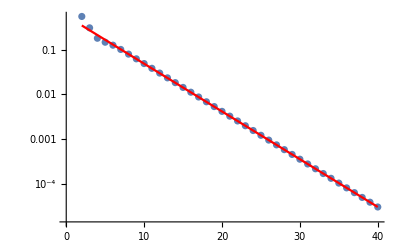

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

For the derivatives below, checked that substituting known values of derivatives of h^P, instead of differentiating the interpolating polynomials makes no difference.

{A→0.982314,b→0.21569}

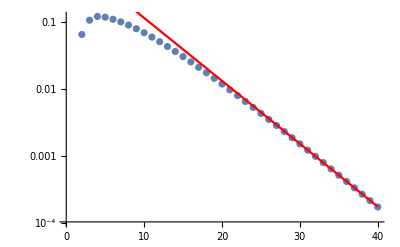

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→1.64595,b→0.186073}

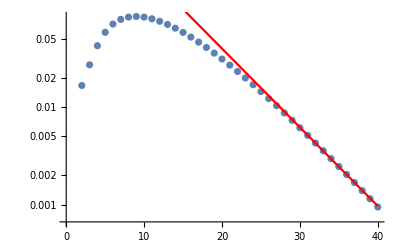

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m]''[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

## ψ_0

Convert here from t to u slicing.

```mathematica
Clear[NumericRule,ψ0PExactWorldtubePiece,ψ0PExactδrmin,ψ0PExactδprmin,ψ0PExactδrmax,ψ0PExactδprmax]
(* Choose here which puncture you want to use. First will do the numerical integrals, second are pre-computed, expanded in powers series in dr, last is "exact", values having been pre-computed. *)

(*NumericRule = {h𝒫[x_][l_,m_][r_]-> hP[x][l,m][r-r0],h𝒫[x_][l_,m_]'[r_]-> dhP[x][l,m][r-r0,1],h𝒫[x_][l_,m_]''[r_]-> dhP[x][l,m][r-r0,2]};
NumericAtParticleRule = {h𝒫[x_][l_,m_][r0+Left]:> hP[x][l,m][Left],h𝒫[x_][l_,m_]'[r0+Left]:> dhP[x][l,m][Left,1],h𝒫[x_][l_,m_]''[r0+Left]:> dhP[x][l,m][Left,2],
h𝒫[x_][l_,m_][r0+Right]:> hP[x][l,m][Right],h𝒫[x_][l_,m_]'[r0+Right]:> dhP[x][l,m][Right,1],h𝒫[x_][l_,m_]''[r0+Right]:> dhP[x][l,m][Right,2]};*)

(*NumericRule = {h𝒫[x_][l_,m_][r_]-> hPΔrExpansion[x][l,m][r-r0],h𝒫[x_][l_,m_]'[r_]-> dhPΔrExpansion[x][l,m][r-r0,1],h𝒫[x_][l_,m_]''[r_]-> dhPΔrExpansion[x][l,m][r-r0,2]};
NumericAtParticleRule = {h𝒫[x_][l_,m_][r0+Left]:> hPΔrExpansion[x][l,m][Left],h𝒫[x_][l_,m_]'[r0+Left]:> dhPΔrExpansion[x][l,m][Left,1],h𝒫[x_][l_,m_]''[r0+Left]:> dhPΔrExpansion[x][l,m][Left,2],
h𝒫[x_][l_,m_][r0+Right]:> hPΔrExpansion[x][l,m][Right],h𝒫[x_][l_,m_]'[r0+Right]:> dhPΔrExpansion[x][l,m][Right,1],h𝒫[x_][l_,m_]''[r0+Right]:> dhPΔrExpansion[x][l,m][Right,2]};*)

NumericRule = {h𝒫[x_][l_,m_][r_]-> hSInterpol[x][l,m][r-r0],h𝒫[x_][l_,m_]'[r_]-> dhSInterpol[x][l,m][r-r0],h𝒫[x_][l_,m_]''[r_]-> ddhSInterpol[x][l,m][r-r0]};
NumericAtParticleRule = {h𝒫[x_][l_,m_][r0+Left]:> hSLeftInterpol[x][l,m][0],h𝒫[x_][l_,m_]'[r0+Left]:> dhSLeftInterpol[x][l,m][0],h𝒫[x_][l_,m_]''[r0+Left]:> ddhSLeftInterpol[x][l,m][0],
h𝒫[x_][l_,m_][r0+Right]:> hSRightInterpol[x][l,m][0],h𝒫[x_][l_,m_]'[r0+Right]:> dhSRightInterpol[x][l,m][0],h𝒫[x_][l_,m_]''[r0+Right]:> ddhSRightInterpol[x][l,m][0]};

ψ0PExactWorldtubePiece[l_,m_][r_]=ψ0PunctureWorldtubePiece[l,m][r]/ExpIωrstar[m][r] /.NumericRule;
ψ0PExactWorldtubePiece[l_,m_][Left] = ψ0PunctureWorldtubePiece[l,m][r0+Left]/ExpIωrstar[m][r0] /.NumericAtParticleRule /.  Left -> 0; (* This works only if input, r0, M etc are either kept as arbitrary parameters or their value is exact! *)
ψ0PExactWorldtubePiece[l_,m_][Right] = ψ0PunctureWorldtubePiece[l,m][r0+Right]/ExpIωrstar[m][r0] /.NumericAtParticleRule /.  Right -> 0; 
ψ0PExactWorldtubePiece[l_,m_][r0] = "Indeterminate";

ψ0PExactδrminTMP[l_,m_][r_]=ψ0Punctureδrmin[l,m]/ExpIωrstar[m][r];
ψ0PExactδprminTMP[l_,m_][r_]=ψ0Punctureδprmin[l,m]/ExpIωrstar[m][r];

ψ0PExactδrmaxTMP[l_,m_][r_]=ψ0Punctureδrmax[l,m]/ExpIωrstar[m][r];
ψ0PExactδprmaxTMP[l_,m_][r_]=ψ0Punctureδprmax[l,m]/ExpIωrstar[m][r];

ψ0PExactδrmin[l_,m_]=Simplify[ψ0PExactδrminTMP[l,m][rmin]-ψ0PExactδprminTMP[l,m]'[rmin]]/.NumericRule;
ψ0PExactδprmin[l_,m_]=ψ0PExactδprminTMP[l,m][rmin]/.NumericRule;

ψ0PExactδrmax[l_,m_]=Simplify[ψ0PExactδrmaxTMP[l,m][rmax]-ψ0PExactδprmaxTMP[l,m]'[rmax]]/.NumericRule;
ψ0PExactδprmax[l_,m_]=ψ0PExactδprmaxTMP[l,m][rmax]/.NumericRule;
Clear[ψ0PExactδrminTMP,ψ0PExactδprminTMP,ψ0PExactδrmaxTMP,ψ0PExactδprmaxTMP]
```

## Lorentz retarded metric

Not evaluable.

## (h̄)_ab^Lorentz (trace-reversed)

### Load pre-computed data

The below will extract the trace-reversed metric, mostly positive convention.

```mathematica
Clear[RehRetLeft,RehRetRight,RedhRetLeft,RedhRetRight,ReddhRetLeft,ReddhRetRight,ImhRetLeft,ImhRetRight,ImdhRetLeft,ImdhRetRight,ImddhRetLeft,ImddhRetRight]
Do[
{rgrid,dataLeft,dataRight}=Import[FileNameJoin[{NotebookDirectory[],"h1ret_r010",StringJoin[{"h1-l",ToString[l],"m",ToString[m],".h5"}]}],
{"Datasets",{"grid","inhom_left","inhom_right"}}];
(* Dimensions/@{rgrid,dataLeft,dataRight}  *)
(* Make the range of data shorter for speed. We from horizon to only about r ~ 30M. *)
rgrid=rgrid[[;;1200]];
dataRight=dataRight[[;;(1201-827)]];

Which[
l == 0 && m == 0,
{  RehRetLeft[1][0,0],ImhRetLeft[1][0,0],RedhRetLeft[1][0,0],ImdhRetLeft[1][0,0],ReddhRetLeft[1][0,0],ImddhRetLeft[1][0,0],
	RehRetLeft[3][0,0],ImhRetLeft[3][0,0],RedhRetLeft[3][0,0],ImdhRetLeft[3][0,0],ReddhRetLeft[3][0,0],ImddhRetLeft[3][0,0],
	RehRetLeft[6][0,0],ImhRetLeft[6][0,0],RedhRetLeft[6][0,0],ImdhRetLeft[6][0,0],ReddhRetLeft[6][0,0],ImddhRetLeft[6][0,0],
	RehRetLeft[2][0,0],ImhRetLeft[2][0,0],RedhRetLeft[2][0,0],ImdhRetLeft[2][0,0],ReddhRetLeft[2][0,0],ImddhRetLeft[2][0,0]}=Transpose[dataLeft];
{  RehRetRight[1][0,0],ImhRetRight[1][0,0],RedhRetRight[1][0,0],ImdhRetRight[1][0,0],ReddhRetRight[1][0,0],ImddhRetRight[1][0,0],
	RehRetRight[3][0,0],ImhRetRight[3][0,0],RedhRetRight[3][0,0],ImdhRetRight[3][0,0],ReddhRetRight[3][0,0],ImddhRetRight[3][0,0],
	RehRetRight[6][0,0],ImhRetRight[6][0,0],RedhRetRight[6][0,0],ImdhRetRight[6][0,0],ReddhRetRight[6][0,0],ImddhRetRight[6][0,0],
	RehRetRight[2][0,0],ImhRetRight[2][0,0],RedhRetRight[2][0,0],ImdhRetRight[2][0,0],ReddhRetRight[2][0,0],ImddhRetRight[2][0,0]}=Transpose[dataRight];
{  RehRetLeft[4][0,0],ImhRetLeft[4][0,0],RedhRetLeft[4][0,0],ImdhRetLeft[4][0,0],ReddhRetLeft[4][0,0],ImddhRetLeft[4][0,0],
	RehRetLeft[5][0,0],ImhRetLeft[5][0,0],RedhRetLeft[5][0,0],ImdhRetLeft[5][0,0],ReddhRetLeft[5][0,0],ImddhRetLeft[5][0,0],
	RehRetLeft[7][0,0],ImhRetLeft[7][0,0],RedhRetLeft[7][0,0],ImdhRetLeft[7][0,0],ReddhRetLeft[7][0,0],ImddhRetLeft[7][0,0],
	RehRetLeft[8][0,0],ImhRetLeft[8][0,0],RedhRetLeft[8][0,0],ImdhRetLeft[8][0,0],ReddhRetLeft[8][0,0],ImddhRetLeft[8][0,0],
RehRetLeft[9][0,0],ImhRetLeft[9][0,0],RedhRetLeft[9][0,0],ImdhRetLeft[9][0,0],ReddhRetLeft[9][0,0],ImddhRetLeft[9][0,0],
RehRetLeft[10][0,0],ImhRetLeft[10][0,0],RedhRetLeft[10][0,0],ImdhRetLeft[10][0,0],ReddhRetLeft[10][0,0],ImddhRetLeft[10][0,0]} = ConstantArray[0,{6*6,Last@Dimensions@Transpose[dataLeft]}];
{  RehRetRight[4][0,0],ImhRetRight[4][0,0],RedhRetRight[4][0,0],ImdhRetRight[4][0,0],ReddhRetRight[4][0,0],ImddhRetRight[4][0,0],
	RehRetRight[5][0,0],ImhRetRight[5][0,0],RedhRetRight[5][0,0],ImdhRetRight[5][0,0],ReddhRetRight[5][0,0],ImddhRetRight[5][0,0],
	RehRetRight[7][0,0],ImhRetRight[7][0,0],RedhRetRight[7][0,0],ImdhRetRight[7][0,0],ReddhRetRight[7][0,0],ImddhRetRight[7][0,0],
	RehRetRight[8][0,0],ImhRetRight[8][0,0],RedhRetRight[8][0,0],ImdhRetRight[8][0,0],ReddhRetRight[8][0,0],ImddhRetRight[8][0,0],
RehRetRight[9][0,0],ImhRetRight[9][0,0],RedhRetRight[9][0,0],ImdhRetRight[9][0,0],ReddhRetRight[9][0,0],ImddhRetRight[9][0,0],
RehRetRight[10][0,0],ImhRetRight[10][0,0],RedhRetRight[10][0,0],ImdhRetRight[10][0,0],ReddhRetRight[10][0,0],ImddhRetRight[10][0,0]} = ConstantArray[0,{6*6,Last@Dimensions@Transpose[dataRight]}],

l == 1 && m == 0,
{  RehRetLeft[9][1,0],ImhRetLeft[9][1,0],RedhRetLeft[9][1,0],ImdhRetLeft[9][1,0],ReddhRetLeft[9][1,0],ImddhRetLeft[9][1,0],
	RehRetLeft[8][1,0],ImhRetLeft[8][1,0],RedhRetLeft[8][1,0],ImdhRetLeft[8][1,0],ReddhRetLeft[8][1,0],ImddhRetLeft[8][1,0]}=Transpose[dataLeft];
{  RehRetRight[9][1,0],ImhRetRight[9][1,0],RedhRetRight[9][1,0],ImdhRetRight[9][1,0],ReddhRetRight[9][1,0],ImddhRetRight[9][1,0],
	RehRetRight[8][1,0],ImhRetRight[8][1,0],RedhRetRight[8][1,0],ImdhRetRight[8][1,0],ReddhRetRight[8][1,0],ImddhRetRight[8][1,0]}=Transpose[dataRight];
{  RehRetLeft[1][1,0],ImhRetLeft[1][1,0],RedhRetLeft[1][1,0],ImdhRetLeft[1][1,0],ReddhRetLeft[1][1,0],ImddhRetLeft[1][1,0],
RehRetLeft[2][1,0],ImhRetLeft[2][1,0],RedhRetLeft[2][1,0],ImdhRetLeft[2][1,0],ReddhRetLeft[2][1,0],ImddhRetLeft[2][1,0],
RehRetLeft[3][1,0],ImhRetLeft[3][1,0],RedhRetLeft[3][1,0],ImdhRetLeft[3][1,0],ReddhRetLeft[3][1,0],ImddhRetLeft[3][1,0],
RehRetLeft[4][1,0],ImhRetLeft[4][1,0],RedhRetLeft[4][1,0],ImdhRetLeft[4][1,0],ReddhRetLeft[4][1,0],ImddhRetLeft[4][1,0],
	RehRetLeft[5][1,0],ImhRetLeft[5][1,0],RedhRetLeft[5][1,0],ImdhRetLeft[5][1,0],ReddhRetLeft[5][1,0],ImddhRetLeft[5][1,0],
RehRetLeft[6][1,0],ImhRetLeft[6][1,0],RedhRetLeft[6][1,0],ImdhRetLeft[6][1,0],ReddhRetLeft[6][1,0],ImddhRetLeft[6][1,0],
	RehRetLeft[7][1,0],ImhRetLeft[7][1,0],RedhRetLeft[7][1,0],ImdhRetLeft[7][1,0],ReddhRetLeft[7][1,0],ImddhRetLeft[7][1,0],
RehRetLeft[10][1,0],ImhRetLeft[10][1,0],RedhRetLeft[10][1,0],ImdhRetLeft[10][1,0],ReddhRetLeft[10][1,0],ImddhRetLeft[10][1,0]} = ConstantArray[0,{6*8,Last@Dimensions@Transpose[dataLeft]}];
{  RehRetRight[1][1,0],ImhRetRight[1][1,0],RedhRetRight[1][1,0],ImdhRetRight[1][1,0],ReddhRetRight[1][1,0],ImddhRetRight[1][1,0],
RehRetRight[2][1,0],ImhRetRight[2][1,0],RedhRetRight[2][1,0],ImdhRetRight[2][1,0],ReddhRetRight[2][1,0],ImddhRetRight[2][1,0],
RehRetRight[3][1,0],ImhRetRight[3][1,0],RedhRetRight[3][1,0],ImdhRetRight[3][1,0],ReddhRetRight[3][1,0],ImddhRetRight[3][1,0],
RehRetRight[4][1,0],ImhRetRight[4][1,0],RedhRetRight[4][1,0],ImdhRetRight[4][1,0],ReddhRetRight[4][1,0],ImddhRetRight[4][1,0],
	RehRetRight[5][1,0],ImhRetRight[5][1,0],RedhRetRight[5][1,0],ImdhRetRight[5][1,0],ReddhRetRight[5][1,0],ImddhRetRight[5][1,0],
RehRetRight[6][1,0],ImhRetRight[6][1,0],RedhRetRight[6][1,0],ImdhRetRight[6][1,0],ReddhRetRight[6][1,0],ImddhRetRight[6][1,0],
	RehRetRight[7][1,0],ImhRetRight[7][1,0],RedhRetRight[7][1,0],ImdhRetRight[7][1,0],ReddhRetRight[7][1,0],ImddhRetRight[7][1,0],
RehRetRight[10][1,0],ImhRetRight[10][1,0],RedhRetRight[10][1,0],ImdhRetRight[10][1,0],ReddhRetRight[10][1,0],ImddhRetRight[10][1,0]}  = ConstantArray[0,{6*8,Last@Dimensions@Transpose[dataRight]}],

l == 1 && m == 1,
{  RehRetLeft[1][1,1],ImhRetLeft[1][1,1],RedhRetLeft[1][1,1],ImdhRetLeft[1][1,1],ReddhRetLeft[1][1,1],ImddhRetLeft[1][1,1],
	RehRetLeft[3][1,1],ImhRetLeft[3][1,1],RedhRetLeft[3][1,1],ImdhRetLeft[3][1,1],ReddhRetLeft[3][1,1],ImddhRetLeft[3][1,1],
	RehRetLeft[5][1,1],ImhRetLeft[5][1,1],RedhRetLeft[5][1,1],ImdhRetLeft[5][1,1],ReddhRetLeft[5][1,1],ImddhRetLeft[5][1,1],
	RehRetLeft[6][1,1],ImhRetLeft[6][1,1],RedhRetLeft[6][1,1],ImdhRetLeft[6][1,1],ReddhRetLeft[6][1,1],ImddhRetLeft[6][1,1],
	RehRetLeft[2][1,1],ImhRetLeft[2][1,1],RedhRetLeft[2][1,1],ImdhRetLeft[2][1,1],ReddhRetLeft[2][1,1],ImddhRetLeft[2][1,1],
	RehRetLeft[4][1,1],ImhRetLeft[4][1,1],RedhRetLeft[4][1,1],ImdhRetLeft[4][1,1],ReddhRetLeft[4][1,1],ImddhRetLeft[4][1,1]}=Transpose[dataLeft];
{  RehRetRight[1][1,1],ImhRetRight[1][1,1],RedhRetRight[1][1,1],ImdhRetRight[1][1,1],ReddhRetRight[1][1,1],ImddhRetRight[1][1,1],
	RehRetRight[3][1,1],ImhRetRight[3][1,1],RedhRetRight[3][1,1],ImdhRetRight[3][1,1],ReddhRetRight[3][1,1],ImddhRetRight[3][1,1],
	RehRetRight[5][1,1],ImhRetRight[5][1,1],RedhRetRight[5][1,1],ImdhRetRight[5][1,1],ReddhRetRight[5][1,1],ImddhRetRight[5][1,1],
	RehRetRight[6][1,1],ImhRetRight[6][1,1],RedhRetRight[6][1,1],ImdhRetRight[6][1,1],ReddhRetRight[6][1,1],ImddhRetRight[6][1,1],
	RehRetRight[2][1,1],ImhRetRight[2][1,1],RedhRetRight[2][1,1],ImdhRetRight[2][1,1],ReddhRetRight[2][1,1],ImddhRetRight[2][1,1],
	RehRetRight[4][1,1],ImhRetRight[4][1,1],RedhRetRight[4][1,1],ImdhRetRight[4][1,1],ReddhRetRight[4][1,1],ImddhRetRight[4][1,1]}=Transpose[dataRight];
{  RehRetLeft[7][1,1],ImhRetLeft[7][1,1],RedhRetLeft[7][1,1],ImdhRetLeft[7][1,1],ReddhRetLeft[7][1,1],ImddhRetLeft[7][1,1],
RehRetLeft[8][1,1],ImhRetLeft[8][1,1],RedhRetLeft[8][1,1],ImdhRetLeft[8][1,1],ReddhRetLeft[8][1,1],ImddhRetLeft[8][1,1],
RehRetLeft[9][1,1],ImhRetLeft[9][1,1],RedhRetLeft[9][1,1],ImdhRetLeft[9][1,1],ReddhRetLeft[9][1,1],ImddhRetLeft[9][1,1],
RehRetLeft[10][1,1],ImhRetLeft[10][1,1],RedhRetLeft[10][1,1],ImdhRetLeft[10][1,1],ReddhRetLeft[10][1,1],ImddhRetLeft[10][1,1]} = ConstantArray[0,{6*4,Last@Dimensions@Transpose[dataLeft]}];
{  RehRetRight[7][1,1],ImhRetRight[7][1,1],RedhRetRight[7][1,1],ImdhRetRight[7][1,1],ReddhRetRight[7][1,1],ImddhRetRight[7][1,1],
RehRetRight[8][1,1],ImhRetRight[8][1,1],RedhRetRight[8][1,1],ImdhRetRight[8][1,1],ReddhRetRight[8][1,1],ImddhRetRight[8][1,1],
RehRetRight[9][1,1],ImhRetRight[9][1,1],RedhRetRight[9][1,1],ImdhRetRight[9][1,1],ReddhRetRight[9][1,1],ImddhRetRight[9][1,1],
RehRetRight[10][1,1],ImhRetRight[10][1,1],RedhRetRight[10][1,1],ImdhRetRight[10][1,1],ReddhRetRight[10][1,1],ImddhRetRight[10][1,1]}  = ConstantArray[0,{6*4,Last@Dimensions@Transpose[dataRight]}],

EvenQ[l+m],
{  RehRetLeft[1][l,m],ImhRetLeft[1][l,m],RedhRetLeft[1][l,m],ImdhRetLeft[1][l,m],ReddhRetLeft[1][l,m],ImddhRetLeft[1][l,m],
	RehRetLeft[3][l,m],ImhRetLeft[3][l,m],RedhRetLeft[3][l,m],ImdhRetLeft[3][l,m],ReddhRetLeft[3][l,m],ImddhRetLeft[3][l,m],
	RehRetLeft[5][l,m],ImhRetLeft[5][l,m],RedhRetLeft[5][l,m],ImdhRetLeft[5][l,m],ReddhRetLeft[5][l,m],ImddhRetLeft[5][l,m],
	RehRetLeft[6][l,m],ImhRetLeft[6][l,m],RedhRetLeft[6][l,m],ImdhRetLeft[6][l,m],ReddhRetLeft[6][l,m],ImddhRetLeft[6][l,m],
RehRetLeft[7][l,m],ImhRetLeft[7][l,m],RedhRetLeft[7][l,m],ImdhRetLeft[7][l,m],ReddhRetLeft[7][l,m],ImddhRetLeft[7][l,m],
	RehRetLeft[2][l,m],ImhRetLeft[2][l,m],RedhRetLeft[2][l,m],ImdhRetLeft[2][l,m],ReddhRetLeft[2][l,m],ImddhRetLeft[2][l,m],
	RehRetLeft[4][l,m],ImhRetLeft[4][l,m],RedhRetLeft[4][l,m],ImdhRetLeft[4][l,m],ReddhRetLeft[4][l,m],ImddhRetLeft[4][l,m]}=Transpose[dataLeft];
{  RehRetRight[1][l,m],ImhRetRight[1][l,m],RedhRetRight[1][l,m],ImdhRetRight[1][l,m],ReddhRetRight[1][l,m],ImddhRetRight[1][l,m],
	RehRetRight[3][l,m],ImhRetRight[3][l,m],RedhRetRight[3][l,m],ImdhRetRight[3][l,m],ReddhRetRight[3][l,m],ImddhRetRight[3][l,m],
	RehRetRight[5][l,m],ImhRetRight[5][l,m],RedhRetRight[5][l,m],ImdhRetRight[5][l,m],ReddhRetRight[5][l,m],ImddhRetRight[5][l,m],
	RehRetRight[6][l,m],ImhRetRight[6][l,m],RedhRetRight[6][l,m],ImdhRetRight[6][l,m],ReddhRetRight[6][l,m],ImddhRetRight[6][l,m],
RehRetRight[7][l,m],ImhRetRight[7][l,m],RedhRetRight[7][l,m],ImdhRetRight[7][l,m],ReddhRetRight[7][l,m],ImddhRetRight[7][l,m],
	RehRetRight[2][l,m],ImhRetRight[2][l,m],RedhRetRight[2][l,m],ImdhRetRight[2][l,m],ReddhRetRight[2][l,m],ImddhRetRight[2][l,m],
	RehRetRight[4][l,m],ImhRetRight[4][l,m],RedhRetRight[4][l,m],ImdhRetRight[4][l,m],ReddhRetRight[4][l,m],ImddhRetRight[4][l,m]}=Transpose[dataRight];
{  RehRetLeft[8][l,m],ImhRetLeft[8][l,m],RedhRetLeft[8][l,m],ImdhRetLeft[8][l,m],ReddhRetLeft[8][l,m],ImddhRetLeft[8][l,m],
RehRetLeft[9][l,m],ImhRetLeft[9][l,m],RedhRetLeft[9][l,m],ImdhRetLeft[9][l,m],ReddhRetLeft[9][l,m],ImddhRetLeft[9][l,m],
RehRetLeft[10][l,m],ImhRetLeft[10][l,m],RedhRetLeft[10][l,m],ImdhRetLeft[10][l,m],ReddhRetLeft[10][l,m],ImddhRetLeft[10][l,m]} = ConstantArray[0,{6*3,Last@Dimensions@Transpose[dataLeft]}];
{  RehRetRight[8][l,m],ImhRetRight[8][l,m],RedhRetRight[8][l,m],ImdhRetRight[8][l,m],ReddhRetRight[8][l,m],ImddhRetRight[8][l,m],
RehRetRight[9][l,m],ImhRetRight[9][l,m],RedhRetRight[9][l,m],ImdhRetRight[9][l,m],ReddhRetRight[9][l,m],ImddhRetRight[9][l,m],
RehRetRight[10][l,m],ImhRetRight[10][l,m],RedhRetRight[10][l,m],ImdhRetRight[10][l,m],ReddhRetRight[10][l,m],ImddhRetRight[10][l,m]}  = ConstantArray[0,{6*3,Last@Dimensions@Transpose[dataRight]}],

OddQ[l+m],
{  RehRetLeft[9][l,m],ImhRetLeft[9][l,m],RedhRetLeft[9][l,m],ImdhRetLeft[9][l,m],ReddhRetLeft[9][l,m],ImddhRetLeft[9][l,m],
	RehRetLeft[10][l,m],ImhRetLeft[10][l,m],RedhRetLeft[10][l,m],ImdhRetLeft[10][l,m],ReddhRetLeft[10][l,m],ImddhRetLeft[10][l,m],
	RehRetLeft[8][l,m],ImhRetLeft[8][l,m],RedhRetLeft[8][l,m],ImdhRetLeft[8][l,m],ReddhRetLeft[8][l,m],ImddhRetLeft[8][l,m]}=Transpose[dataLeft];
     {  RehRetRight[9][l,m],ImhRetRight[9][l,m],RedhRetRight[9][l,m],ImdhRetRight[9][l,m],ReddhRetRight[9][l,m],ImddhRetRight[9][l,m],
	RehRetRight[10][l,m],ImhRetRight[10][l,m],RedhRetRight[10][l,m],ImdhRetRight[10][l,m],ReddhRetRight[10][l,m],ImddhRetRight[10][l,m],
	RehRetRight[8][l,m],ImhRetRight[8][l,m],RedhRetRight[8][l,m],ImdhRetRight[8][l,m],ReddhRetRight[8][l,m],ImddhRetRight[8][l,m]}=Transpose[dataRight];
{  RehRetLeft[1][l,m],ImhRetLeft[1][l,m],RedhRetLeft[1][l,m],ImdhRetLeft[1][l,m],ReddhRetLeft[1][l,m],ImddhRetLeft[1][l,m],
RehRetLeft[2][l,m],ImhRetLeft[2][l,m],RedhRetLeft[2][l,m],ImdhRetLeft[2][l,m],ReddhRetLeft[2][l,m],ImddhRetLeft[2][l,m],
RehRetLeft[3][l,m],ImhRetLeft[3][l,m],RedhRetLeft[3][l,m],ImdhRetLeft[3][l,m],ReddhRetLeft[3][l,m],ImddhRetLeft[3][l,m],
RehRetLeft[4][l,m],ImhRetLeft[4][l,m],RedhRetLeft[4][l,m],ImdhRetLeft[4][l,m],ReddhRetLeft[4][l,m],ImddhRetLeft[4][l,m],
RehRetLeft[5][l,m],ImhRetLeft[5][l,m],RedhRetLeft[5][l,m],ImdhRetLeft[5][l,m],ReddhRetLeft[5][l,m],ImddhRetLeft[5][l,m],
RehRetLeft[6][l,m],ImhRetLeft[6][l,m],RedhRetLeft[6][l,m],ImdhRetLeft[6][l,m],ReddhRetLeft[6][l,m],ImddhRetLeft[6][l,m],
RehRetLeft[7][l,m],ImhRetLeft[7][l,m],RedhRetLeft[7][l,m],ImdhRetLeft[7][l,m],ReddhRetLeft[7][l,m],ImddhRetLeft[7][l,m]} = ConstantArray[0,{6*7,Last@Dimensions@Transpose[dataLeft]}];
{  RehRetRight[1][l,m],ImhRetRight[1][l,m],RedhRetRight[1][l,m],ImdhRetRight[1][l,m],ReddhRetRight[1][l,m],ImddhRetRight[1][l,m],
RehRetRight[2][l,m],ImhRetRight[2][l,m],RedhRetRight[2][l,m],ImdhRetRight[2][l,m],ReddhRetRight[2][l,m],ImddhRetRight[2][l,m],
RehRetRight[3][l,m],ImhRetRight[3][l,m],RedhRetRight[3][l,m],ImdhRetRight[3][l,m],ReddhRetRight[3][l,m],ImddhRetRight[3][l,m],
RehRetRight[4][l,m],ImhRetRight[4][l,m],RedhRetRight[4][l,m],ImdhRetRight[4][l,m],ReddhRetRight[4][l,m],ImddhRetRight[4][l,m],
RehRetRight[5][l,m],ImhRetRight[5][l,m],RedhRetRight[5][l,m],ImdhRetRight[5][l,m],ReddhRetRight[5][l,m],ImddhRetRight[5][l,m],
RehRetRight[6][l,m],ImhRetRight[6][l,m],RedhRetRight[6][l,m],ImdhRetRight[6][l,m],ReddhRetRight[6][l,m],ImddhRetRight[6][l,m],
RehRetRight[7][l,m],ImhRetRight[7][l,m],RedhRetRight[7][l,m],ImdhRetRight[7][l,m],ReddhRetRight[7][l,m],ImddhRetRight[7][l,m]}  = ConstantArray[0,{6*7,Last@Dimensions@Transpose[dataRight]}],

True,
Print["Never get here"]
]
,{l,0,50},{m,0,l}]
```

```mathematica
Quiet@hP[3][3,0][-0.1]
Quiet@hP[3][3,0][-0.1]
```

0

0

```mathematica
Clear[hRetLeftTable,hRetRightTable,dhRetLeftTable,dhRetRightTable,ddhRetLeftTable,ddhRetRightTable]
Do[
hRetLeftTable[i][l,m] = RehRetLeft[i][l,m]+I ImhRetLeft[i][l,m];
hRetRightTable[i][l,m] = RehRetRight[i][l,m]+I ImhRetRight[i][l,m];
dhRetLeftTable[i][l,m] = RedhRetLeft[i][l,m]+I ImdhRetLeft[i][l,m];
dhRetRightTable[i][l,m] = RedhRetRight[i][l,m]+I ImdhRetRight[i][l,m];
ddhRetLeftTable[i][l,m] = ReddhRetLeft[i][l,m]+I ImddhRetLeft[i][l,m];
ddhRetRightTable[i][l,m] = ReddhRetRight[i][l,m]+I ImddhRetRight[i][l,m];

If[m != 0,hRetLeftTable[i][l,-m] = (-1)^m Conjugate[hRetLeftTable[i][l,m]];
hRetRightTable[i][l,-m] = (-1)^m Conjugate[hRetRightTable[i][l,m]];
dhRetLeftTable[i][l,-m] = (-1)^m Conjugate[dhRetLeftTable[i][l,m]];
dhRetRightTable[i][l,-m] =(-1)^m Conjugate[dhRetRightTable[i][l,m]];
ddhRetLeftTable[i][l,-m] = (-1)^m Conjugate[ddhRetLeftTable[i][l,m]];
ddhRetRightTable[i][l,-m] = (-1)^m Conjugate[ddhRetRightTable[i][l,m]]]
,{i,1,10},{l,0,50},{m,0,l}]
```

### Interpolate

By trial and error, using the power-series expanded puncture, found best results with interpolation order = 8-10 for 120 gpts (each side), 16 for 20 gpts and 9 for 10 gpts.

```mathematica
Clear[hRetLeftInterpol,hRetRightInterpol,hRetInterpol]
myr0=10;
Monitor[Do[
hRetLeftInterpol[i][l,m] = Interpolation[Transpose[{rgrid[[;;827]],hRetLeftTable[i][l,m]}],InterpolationOrder->9];
hRetRightInterpol[i][l,m] = Interpolation[Transpose[{rgrid[[827;;]],hRetRightTable[i][l,m]}],InterpolationOrder->9];
hRetInterpol[i][l,m][r_] =  If[r < r0,Evaluate[hRetLeftInterpol[i][l,m][r]], Evaluate[hRetRightInterpol[i][l,m][r]]];

hRetInterpol[i][l,m][Left] = hRetLeftInterpol[i][l,m][r0];
hRetInterpol[i][l,m][Right] = hRetRightInterpol[i][l,m][r0]
,{i,1,10},{l,0,50},{m,-l,l}]
,{i,l,m}]
```

### In tetrad basis

```mathematica
Clear[hRetInterpolll,hRetInterpolln,hRetInterpollm,hRetInterpollmb,hRetInterpolnn,hRetInterpolnm,hRetInterpolnmb,hRetInterpolmm,hRetInterpolmmb,hRetInterpolmbmb]
hRetInterpolll[l_,m_][r_] := (hRetInterpol[1][l,m][r]+hRetInterpol[2][l,m][r])/(r f[r]^2);
hRetInterpolln[l_,m_][r_] := hRetInterpol[6][l,m][r]/(2 r);
hRetInterpollm[l_,m_][r_] := -(hRetInterpol[4][l,m][r]+hRetInterpol[5][l,m][r]-I (hRetInterpol[8][l,m][r]+hRetInterpol[9][l,m][r]))/(2 Sqrt[2 l (l+1)] r f[r]);
hRetInterpollmb[l_,m_][r_] := (hRetInterpol[4][l,m][r]+hRetInterpol[5][l,m][r]+I (hRetInterpol[8][l,m][r]+hRetInterpol[9][l,m][r]))/(2 Sqrt[2 l (l+1)] r f[r]);
hRetInterpolnn[l_,m_][r_] := (hRetInterpol[1][l,m][r]-hRetInterpol[2][l,m][r])/(4 r);
hRetInterpolnm[l_,m_][r_] := (-hRetInterpol[4][l,m][r]+hRetInterpol[5][l,m][r]+I (hRetInterpol[8][l,m][r]-hRetInterpol[9][l,m][r]))/(4 Sqrt[2 l (l+1)] r);
hRetInterpolnmb[l_,m_][r_] := (hRetInterpol[4][l,m][r]-hRetInterpol[5][l,m][r]+I (hRetInterpol[8][l,m][r]-hRetInterpol[9][l,m][r]))/(4 Sqrt[2 l (l+1)] r);
hRetInterpolmm[l_,m_][r_] := (hRetInterpol[7][l,m][r]-I hRetInterpol[10][l,m][r])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r);
hRetInterpolmmb[l_,m_][r_] := hRetInterpol[3][l,m][r]/(2 r);
hRetInterpolmbmb[l_,m_][r_]:= (hRetInterpol[7][l,m][r]+I hRetInterpol[10][l,m][r])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r);

hRetInterpolll[l_,m_][Left] := (hRetInterpol[1][l,m][Left]+hRetInterpol[2][l,m][Left])/(r0 f[r0]^2);
hRetInterpolln[l_,m_][Left] := hRetInterpol[6][l,m][Left]/(2 r0);
hRetInterpollm[l_,m_][Left] := -(hRetInterpol[4][l,m][Left]+hRetInterpol[5][l,m][Left]-I (hRetInterpol[8][l,m][Left]+hRetInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hRetInterpollmb[l_,m_][Left] := (hRetInterpol[4][l,m][Left]+hRetInterpol[5][l,m][Left]+I (hRetInterpol[8][l,m][Left]+hRetInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hRetInterpolnn[l_,m_][Left] := (hRetInterpol[1][l,m][Left]-hRetInterpol[2][l,m][Left])/(4 r0);
hRetInterpolnm[l_,m_][Left] := (-hRetInterpol[4][l,m][Left]+hRetInterpol[5][l,m][Left]+I (hRetInterpol[8][l,m][Left]-hRetInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hRetInterpolnmb[l_,m_][Left] := (hRetInterpol[4][l,m][Left]-hRetInterpol[5][l,m][Left]+I (hRetInterpol[8][l,m][Left]-hRetInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hRetInterpolmm[l_,m_][Left] := (hRetInterpol[7][l,m][Left]-I hRetInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hRetInterpolmmb[l_,m_][Left] := hRetInterpol[3][l,m][Left]/(2 r0);
hRetInterpolmbmb[l_,m_][Left]:= (hRetInterpol[7][l,m][Left]+I hRetInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);

hRetInterpolll[l_,m_][Right] := (hRetInterpol[1][l,m][Right]+hRetInterpol[2][l,m][Right])/(r0 f[r0]^2);
hRetInterpolln[l_,m_][Right] := hRetInterpol[6][l,m][Right]/(2 r0);
hRetInterpollm[l_,m_][Right] := -(hRetInterpol[4][l,m][Right]+hRetInterpol[5][l,m][Right]-I (hRetInterpol[8][l,m][Right]+hRetInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hRetInterpollmb[l_,m_][Right] := (hRetInterpol[4][l,m][Right]+hRetInterpol[5][l,m][Right]+I (hRetInterpol[8][l,m][Right]+hRetInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hRetInterpolnn[l_,m_][Right] := (hRetInterpol[1][l,m][Right]-hRetInterpol[2][l,m][Right])/(4 r0);
hRetInterpolnm[l_,m_][Right] := (-hRetInterpol[4][l,m][Right]+hRetInterpol[5][l,m][Right]+I (hRetInterpol[8][l,m][Right]-hRetInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hRetInterpolnmb[l_,m_][Right] := (hRetInterpol[4][l,m][Right]-hRetInterpol[5][l,m][Right]+I (hRetInterpol[8][l,m][Right]-hRetInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hRetInterpolmm[l_,m_][Right] := (hRetInterpol[7][l,m][Right]-I hRetInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hRetInterpolmmb[l_,m_][Right] := hRetInterpol[3][l,m][Right]/(2 r0);
hRetInterpolmbmb[l_,m_][Right]:= (hRetInterpol[7][l,m][Right]+I hRetInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
```

## h_uu=h_ab u^a u^b

Note that if  we are working with the trace-reversed metric, (h̄)_ab=h_ab-1/2 h g_ab, then to leading order (mostly negative signature): (h̄)_ab=  (4 Mu_a u_b)/R+.... (R is 4D distance).
So, (h̄)_uu=  (4M)/R+..., while h_ab=  (2M(g_ab+2 u_a u_b))/R+..., so  h_uu=  (2M)/R+.... So, to leading order, there is a factor of 2 difference in h_uu between trace-reversed and non-trace-reversed.

```mathematica
Clear[hRetInterpoluu]
hRetInterpoluu[l_,m_][r_]= redshift$Contribution$Formula[
hRetInterpolll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpolln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpollm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],
hRetInterpollmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0],
hRetInterpolnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpolnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],
hRetInterpolnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0],
hRetInterpolmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0],
hRetInterpolmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpolmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]];

hRetInterpoluu[l_,m_][Left]= redshift$Contribution$Formula[
hRetInterpolll[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpolln[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpollm[l,m][Left] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],
hRetInterpollmb[l,m][Left] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0],
hRetInterpolnn[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpolnm[l,m][Left] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],
hRetInterpolnmb[l,m][Left] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0],
hRetInterpolmm[l,m][Left] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0],
hRetInterpolmmb[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetInterpolmbmb[l,m][Left] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]];


hPuu[l_,m_][Δr_] = redshift$Contribution$Formula[
hPll[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hPln[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hPlm[l,m][Δr] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],
hPlmb[l,m][Δr] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0],
hPnn[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hPnm[l,m][Δr] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],
hPnmb[l,m][Δr] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0],
hPmm[l,m][Δr] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0],
hPmmb[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hPmbmb[l,m][Δr] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]];
```

## Exact regularization parameters for 1/2 h_ab u^a u^b

These are given in the “SchwarzschildRegularizationParameters” notebook. The values are also taken from arXiv:1204.0794, page 26.
Note that they are given in mostly positive, so again need to change it to mostly negative signature.

```mathematica
E0Energy = f[r0] utU;
L0Energy = Sqrt[r0 M] utU;

Hl[0]=(2 EllipticK[L^2/(L^2+r0^2)])/(π √(L^2+r0^2)) /. {L -> L0Energy, E0 -> E0Energy};
Hl[2]=((2 E0^2 r0^5+(L^2+r0^2) (36 L^2 M-8 L^2 r0+38 M r0^2-9 r0^3)) EllipticE[L^2/(L^2+r0^2)]+(-E0^2 r0^3 (16 L^2+17 r0^2)-2 (L^2+r0^2) (16 L^2 M-4 L^2 r0+33 M r0^2-12 r0^3)) EllipticK[L^2/(L^2+r0^2)])/((-1+2 l) (3+2 l) π r0^3 (L^2+r0^2)^(3/2)) /. {L -> L0Energy, E0 -> E0Energy};
Hl[4]=(3 ((-120 E0^4 r0^12 (8 L^4+17 L^2 r0^2+7 r0^4)+2 E0^2 r0^5 (L^2+r0^2) (3584 L^8 M+12712 L^6 M r0^2+15516 L^4 M r0^4+120 L^4 r0^5+6182 L^2 M r0^6+735 L^2 r0^7+34 M r0^8+495 r0^9)+2 (L^2+r0^2)^2 (1536 L^10 M^2+13888 L^8 M^2 r0^2-1600 L^8 M r0^3+40584 L^6 M^2 r0^4-9440 L^6 M r0^5+46888 L^4 M^2 r0^6-14100 L^4 M r0^7+120 L^4 r0^8+18936 L^2 M^2 r0^8-5350 L^2 M r0^9+15 L^2 r0^10+340 M^2 r0^10+850 M r0^11-90 r0^12)) EllipticE[L^2/(L^2+r0^2)]+(15 E0^4 r0^10 (64 L^6+224 L^4 r0^2+259 L^2 r0^4+91 r0^6)-4 E0^2 r0^7 (L^2+r0^2) (1376 L^6 M+3174 L^4 M r0^2+420 L^4 r0^3+1965 L^2 M r0^4+960 L^2 r0^5+227 M r0^6+510 r0^7)-r0^2 (L^2+r0^2)^2 (1536 L^8 M^2+15904 L^6 M^2 r0^2-7360 L^6 M r0^3+36160 L^4 M^2 r0^4-19320 L^4 M r0^5+22412 L^2 M^2 r0^6-11040 L^2 M r0^7-720 L^2 r0^8+680 M^2 r0^8+860 M r0^9-705 r0^10)) EllipticK[L^2/(L^2+r0^2)]))/(20 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0^10 (L^2+r0^2)^(7/2)) /. {L -> L0Energy, E0 -> E0Energy};
```

## Check regularization parameters and l behaviour of h^Lorentz-h^P

```mathematica
hRetInterpoluuTableLeft = Table[{l,Sum[hRetInterpoluu[l,m][Left],{m,-l,l}]},{l,Abs[Weylspin],40}];
```

Check regularization parameters. Only leading term agrees. I think there was a reason for this, but I cannot remember why...

```mathematica
Fit[hRetInterpoluuTableLeft[[-5;;]],{1,1/((2l-1)(2l+3)),1/((2l-3)(2l-1)(2l+3)(2l+5)),1/((2l-5)(2l-3)(2l-1)(2l+3)(2l+5)(2l+7))(*,l^-3*)},l]
2 Hl[0]+2 Hl[2]+2 Hl[4] // N (* went to l=50 for this *)
```

0.19338-0.290793/((-1+2 l) (3+2 l))+1.15595/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))-0.185267/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))

0.19338-0.125961/((-1.+2. l) (3.+2. l))+1.82557/((-3.+2. l) (-1.+2. l) (3.+2. l) (5.+2. l))

## Large l behaviour

Check large l behaviour of puncture and reconstructed metric.

```mathematica
hlPuuTableLeft = Table[{l,Sum[hPuu[l,m][Left],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
```

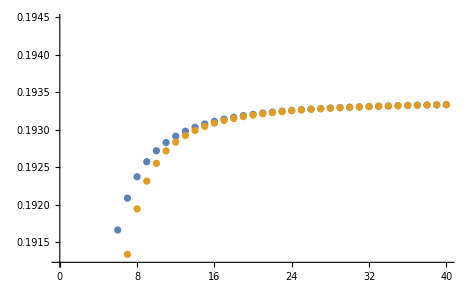

```mathematica
ListPlot[{hRetInterpoluuTableLeft,hlPuuTableLeft}]
```

Check large l behaviour. Going like l^4.

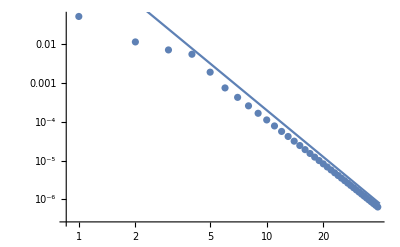

```mathematica
Show[ListLogLogPlot[Abs[hRetInterpoluuTableLeft-hlPuuTableLeft][[All,2]]],
LogLogPlot[2 l^{-4},{l,0,lmax}]]
```

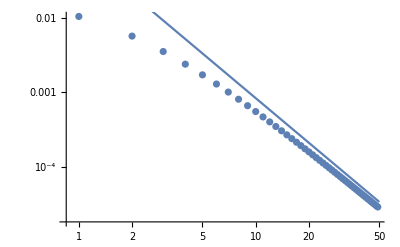

```mathematica
hRetH0InterpoluuTableLeft = Table[{l,Sum[hRetInterpoluu[l,m][Left],{m,-l,l}]-2 Hl[0]},{l,Abs[Weylspin],50}];
Show[ListLogLogPlot[Abs[hRetH0InterpoluuTableLeft][[All,2]]],
LogLogPlot[l^{-2}/12,{l,0,50}]]
```

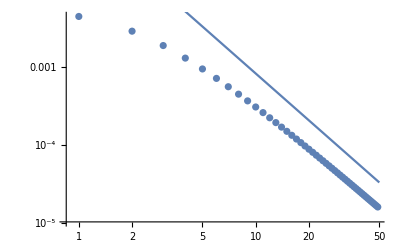

```mathematica
hRetH0H2InterpoluuTableLeft = Table[{l,Sum[hRetInterpoluu[l,m][Left],{m,-l,l}]-2 Hl[0]-2Hl[2]},{l,Abs[Weylspin],50}];
Show[ListLogLogPlot[Abs[hRetH0H2InterpoluuTableLeft][[All,2]]],
LogLogPlot[l^{-2}/12,{l,0,50}]]
```

## Effective stress-energy

## Definitions

### Stress energy

Note: When defining the “TRXXInterpolation” below, important that the different geodesics and numerical quantities (r_0,M, etc) have not been set yet. Otherwise, get a strange error in T_ln which only uses 3 digits of precision.

```mathematica
Clear[TabRMatterVec,TabRδRminVec,TabRδpRminVec, TabRδRmaxVec,TabRδpRmaxVec,
TllWorldtubePiece,TlnWorldtubePiece,TlmWorldtubePiece,TlmbWorldtubePiece,TnnWorldtubePiece,TnmWorldtubePiece,TnmbWorldtubePiece,TmmWorldtubePiece,TmmbWorldtubePiece,TmbmbWorldtubePiece, (* Matter pieces *)
TllδRminPiece,TlnδRminPiece,TlmδRminPiece,TlmbδRminPiece,TnnδRminPiece,TnmδRminPiece,TnmbδRminPiece,TmmδRminPiece,TmmbδRminPiece,TmbmbδRminPiece,
TllδRmaxPiece,TlnδRmaxPiece,TlmδRmaxPiece,TlmbδRmaxPiece,TnnδRmaxPiece,TnmδRmaxPiece,TnmbδRmaxPiece,TmmδRmaxPiece,TmmbδRmaxPiece,TmbmbδRmaxPiece, (* δ pieces *)
TllδpRminPiece,TlnδpRminPiece,TlmδpRminPiece,TlmbδpRminPiece,TnnδpRminPiece,TnmδpRminPiece,TnmbδpRminPiece,TmmδpRminPiece,TmmbδpRminPiece,TmbmbδpRminPiece,
TllδpRmaxPiece,TlnδpRmaxPiece,TlmδpRmaxPiece,TlmbδpRmaxPiece,TnnδpRmaxPiece,TnmδpRmaxPiece,TnmbδpRmaxPiece,TmmδpRmaxPiece,TmmbδpRmaxPiece,TmbmbδpRmaxPiece] (* δ' pieces *)

TabRMatterVec = {TllWorldtubePiece,TlnWorldtubePiece,TlmWorldtubePiece,TlmbWorldtubePiece,TnnWorldtubePiece,TnmWorldtubePiece,TnmbWorldtubePiece,TmmWorldtubePiece,TmmbWorldtubePiece,TmbmbWorldtubePiece};
TabRδRminVec = {TllδRminPiece,TlnδRminPiece,TlmδRminPiece,TlmbδRminPiece,TnnδRminPiece,TnmδRminPiece,TnmbδRminPiece,TmmδRminPiece,TmmbδRminPiece,TmbmbδRminPiece};
TabRδpRminVec = {TllδpRminPiece,TlnδpRminPiece,TlmδpRminPiece,TlmbδpRminPiece,TnnδpRminPiece,TnmδpRminPiece,TnmbδpRminPiece,TmmδpRminPiece,TmmbδpRminPiece,TmbmbδpRminPiece};
TabRδRmaxVec = {TllδRmaxPiece,TlnδRmaxPiece,TlmδRmaxPiece,TlmbδRmaxPiece,TnnδRmaxPiece,TnmδRmaxPiece,TnmbδRmaxPiece,TmmδRmaxPiece,TmmbδRmaxPiece,TmbmbδRmaxPiece};
TabRδpRmaxVec = {TllδpRmaxPiece,TlnδpRmaxPiece,TlmδpRmaxPiece,TlmbδpRmaxPiece,TnnδpRmaxPiece,TnmδpRmaxPiece,TnmbδpRmaxPiece,TmmδpRmaxPiece,TmmbδpRmaxPiece,TmbmbδpRmaxPiece};
Do[Evaluate[TabRMatterVec[[iInd]]][l_,m_][r_] = -ℰhPWorldtubePiece[l,m][r][[iInd]],{iInd,1,Length[TabRMatterVec]}];
Do[Evaluate[TabRδRminVec[[iInd]]][l_,m_]   = -ℰhPδRminPiece[l,m][[iInd]],{iInd,1,Length[TabRδRminVec]}];
Do[Evaluate[TabRδpRminVec[[iInd]]][l_,m_] = -ℰhPδpRminPiece[l,m][[iInd]],{iInd,1,Length[TabRδpRminVec]}];
Do[Evaluate[TabRδRmaxVec[[iInd]]][l_,m_]   = -ℰhPδRmaxPiece[l,m][[iInd]],{iInd,1,Length[TabRδRmaxVec]}];
Do[Evaluate[TabRδpRmaxVec[[iInd]]][l_,m_] = -ℰhPδpRmaxPiece[l,m][[iInd]],{iInd,1,Length[TabRδpRmaxVec]}];
Clear[ℰhPWorldtubePiece,ℰhPδRminPiece,ℰhPδpRminPiece,ℰhPδRmaxPiece,ℰhPδpRmaxPiece]
```

### Large l behaviour of T_ll

Not evaluable.

Note: we ignore the large l behaviour of the metric perturbation and derivatives, effectively assuming they all have the same leading order behaviour.

```mathematica
Normal@Series[TllWorldtubePiece[l,m][r] ExpIωrstar[m][r]  /. g_[l,m] -> g,{l,∞,-2}] // Simplify
Normal@Series[TlmWorldtubePiece[l,m][r] ExpIωrstar[m][r] /. g_[l,m] -> g,{l,∞,-2}] // Simplify
Normal@Series[TlnWorldtubePiece[l,m][r] ExpIωrstar[m][r] /. g_[l,m] -> g,{l,∞,-2}] // Simplify
```

(l^2 h𝒫ll[r])/(2 r^2)

(l^2 (h𝒫lm[r]+h𝒫lmb[r]))/(4 r^2)

(l^2 (-2 h𝒫ln[r]+h𝒫mbmb[r]+h𝒫mm[r]+2 h𝒫mmb[r]))/(4 r^2)

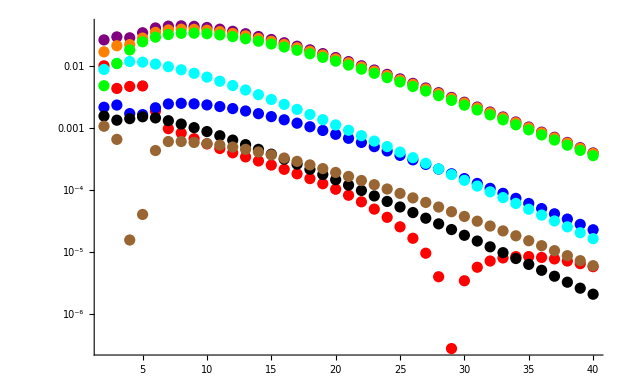

```mathematica
TllData=Table[{l,Sum[TllLeftInterpol[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPllData=Table[{l,Sum[ (l+l^2-2 ⅈ m rmin Ωφ)/(2 rmin^2)  hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlnData=Table[{l,Sum[ -(2 ⅈ m Ωφ)/(2 M-rmin)  hPlnLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlmData=Table[{l,Sum[ (√(l (1+l)) (2 M+rmin (-1+ⅈ m rmin Ωφ)))/(√2 (2 M-rmin) rmin^2)  hPlmLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlnpData=Table[{l,Sum[-2/rmin  hPlnLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlmpData=Table[{l,Sum[(√(l (1+l)))/(√2 rmin)  hPlmLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPmmbpData=Table[{l,Sum[-(4 M-2 rmin+2 ⅈ m rmin^2 Ωφ)/(2 M rmin-rmin^2)  hPmmbLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPmmbppData=Table[{l,Sum[ -hPmmbLeft[l,m]''[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPLargelBehaviourData=Table[{l,Sum[ l^2/(2 rmin^2)  hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
Show[
ListLogPlot[Abs@TllData, PlotStyle -> Red],
ListLogPlot[Abs@hPllData,PlotStyle->Purple],
(*ListLogPlot[Abs@hPlnData,PlotStyle->Yellow],*)
ListLogPlot[Abs@hPlmData,PlotStyle->Blue],
ListLogPlot[Abs@hPlnpData,PlotStyle->Black],
ListLogPlot[Abs@hPlmpData,PlotStyle->Brown],
ListLogPlot[Abs@hPmmbpData,PlotStyle->Cyan],
ListLogPlot[Abs@hPLargelBehaviourData,PlotStyle->Orange],
ListLogPlot[Abs@hPmmbppData,PlotStyle->Green],
PlotRange -> All]
```

### Left and right interpolations

Hack: in the below, I use the assumption l≥2 when simplifying, even if this is not necessarily true for some quantities.
The reason is to force Mathematica to cancel out certain terms, which will otherwise give a 0/0 error (e.g. evaluating T_ln for l=0,1).

```mathematica
myruleLeft =
{h𝒫[x_][l_,m_][r_]-> hSLeftInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]'[r_]-> dhSLeftInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]''[r_]-> ddhSLeftInterpol[x][l,m][r-r0]};
myruleRight =
{h𝒫[x_][l_,m_][r_]-> hSRightInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]'[r_]-> dhSRightInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]''[r_]-> ddhSRightInterpol[x][l,m][r-r0]};
Clear[TllLeftInterpol,TlnLeftInterpol,TlmLeftInterpol,TlmbLeftInterpol,TnnLeftInterpol,TnmLeftInterpol,TnmbLeftInterpol,TmmLeftInterpol,TmmbLeftInterpol,TmbmbLeftInterpol,
TllRightInterpol,TlnRightInterpol,TlmRightInterpol,TlmbRightInterpol,TnnRightInterpol,TnmRightInterpol,TnmbRightInterpol,TmmRightInterpol,TmmbRightInterpol,TmbmbRightInterpol,
TllδRminInterpol,TlnδRminInterpol,TlmδRminInterpol,TlmbδRminInterpol,TnnδRminInterpol,TnmδRminInterpol,TnmbδRminInterpol,TmmδRminInterpol,TmmbδRminInterpol,TmbmbδRminInterpol,
TllδpRminInterpol,TlnδpRminInterpol,TlmδpRminInterpol,TlmbδpRminInterpol,TnnδpRminInterpol,TnmδpRminInterpol,TnmbδpRminInterpol,TmmδpRminInterpol,TmmbδpRminInterpol,TmbmbδpRminInterpol]
TllLeftInterpol[l_,m_][r_] = Simplify[TllWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlnLeftInterpol[l_,m_][r_] = Simplify[TlnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmLeftInterpol[l_,m_][r_] =Simplify[TlmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmbLeftInterpol[l_,m_][r_] = Simplify[TlmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnnLeftInterpol[l_,m_][r_] =Simplify[TnnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmLeftInterpol[l_,m_][r_] = Simplify[TnmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmbLeftInterpol[l_,m_][r_] =Simplify[TnmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmLeftInterpol[l_,m_][r_] =Simplify[TmmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmbLeftInterpol[l_,m_][r_] = Simplify[TmmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmbmbLeftInterpol[l_,m_][r_] = Simplify[TmbmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;

TllRightInterpol[l_,m_][r_] = Simplify[TllWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlnRightInterpol[l_,m_][r_] = Simplify[TlnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmRightInterpol[l_,m_][r_] = Simplify[TlmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmbRightInterpol[l_,m_][r_] = Simplify[TlmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnnRightInterpol[l_,m_][r_] = Simplify[TnnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmRightInterpol[l_,m_][r_] = Simplify[TnmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmbRightInterpol[l_,m_][r_] = Simplify[TnmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TmmRightInterpol[l_,m_][r_] = Simplify[TmmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TmmbRightInterpol[l_,m_][r_] = Simplify[TmmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TmbmbRightInterpol[l_,m_][r_] =Simplify[TmbmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;

TllδRminInterpol[l_,m_] =Simplify[TllδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlnδRminInterpol[l_,m_] = Simplify[TlnδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmδRminInterpol[l_,m_] = Simplify[TlmδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmbδRminInterpol[l_,m_] = Simplify[TlmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnnδRminInterpol[l_,m_] = Simplify[TnnδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmδRminInterpol[l_,m_] = Simplify[TnmδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmbδRminInterpol[l_,m_] = Simplify[TnmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmδRminInterpol[l_,m_] = Simplify[TmmδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmbδRminInterpol[l_,m_] = Simplify[TmmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmbmbδRminInterpol[l_,m_] = Simplify[TmbmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;

TllδpRminInterpol[l_,m_] = Simplify[TllδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlnδpRminInterpol[l_,m_] = Simplify[TlnδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmδpRminInterpol[l_,m_] = Simplify[TlmδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmbδpRminInterpol[l_,m_] = Simplify[TlmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnnδpRminInterpol[l_,m_] = Simplify[TnnδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmδpRminInterpol[l_,m_] = Simplify[TnmδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmbδpRminInterpol[l_,m_] = Simplify[TnmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmδpRminInterpol[l_,m_] = Simplify[TmmδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmbδpRminInterpol[l_,m_] = Simplify[TmmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmbmbδpRminInterpol[l_,m_] = Simplify[TmbmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;

Clear[TllδRmaxInterpol,TllδpRmaxInterpol,TlmδRmaxInterpol,TlmδpRmaxInterpol,TlnδRmaxInterpol,TlnδpRmaxInterpol,TnnδRmaxInterpol,TnnδpRmaxInterpol,TnmδRmaxInterpol,TnmδpRmaxInterpol,TnmbδRmaxInterpol,TnmbδpRmaxInterpol]
TllδRmaxInterpol[l_,m_] =Simplify[TllδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmδRmaxInterpol[l_,m_] =Simplify[TlmδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmbδRmaxInterpol[l_,m_] =Simplify[TlmbδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlnδRmaxInterpol[l_,m_] =Simplify[TlnδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnnδRmaxInterpol[l_,m_] =Simplify[TnnδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmδRmaxInterpol[l_,m_] =Simplify[TnmδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmbδRmaxInterpol[l_,m_] =Simplify[TnmbδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;

TllδpRmaxInterpol[l_,m_] =Simplify[TllδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmδpRmaxInterpol[l_,m_] =Simplify[TlmδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmbδpRmaxInterpol[l_,m_] =Simplify[TlmbδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlnδpRmaxInterpol[l_,m_] =Simplify[TlnδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnnδpRmaxInterpol[l_,m_] =Simplify[TnnδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmδpRmaxInterpol[l_,m_] =Simplify[TnmδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmbδpRmaxInterpol[l_,m_] =Simplify[TnmbδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
```

## Large l behaviour

Near the particle:

```mathematica
lmax=40;
```

```mathematica
r0val=10; Mval = 1; Ωval=Sqrt[Mval/r0val^3];
```

```mathematica
toVals = {M->Mval,r0->r0val,Ωφ->Ωval}
```

{M→1,r0→10,Ωφ→1/(10 √10)}

```mathematica
Clear[{r0,M,Ωφ}]
```

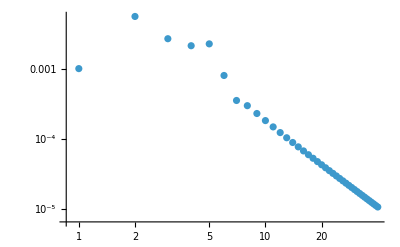

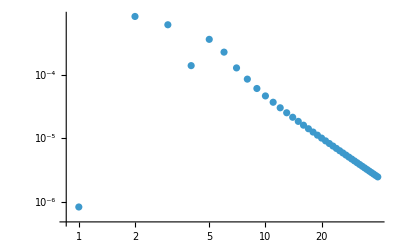

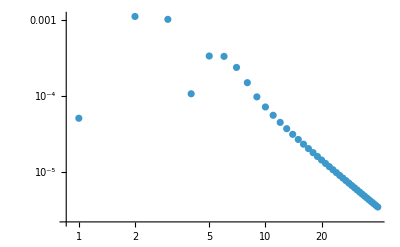

```mathematica
ListLogLogPlot[Abs@Table[{l,Sum[TllLeftInterpol[l,m][r0-1/10000000000000] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0]//.toVals,{m,-l,l}]},{l,0,lmax}]]
ListLogLogPlot[Abs@Table[{l,Sum[TlmLeftInterpol[l,m][r0-1/10000000000000] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]//.toVals,{m,-l,l}]},{l,1,lmax}]]
ListLogLogPlot[Abs@Table[{l,Sum[TlnLeftInterpol[l,m][r0-1/10000000000000] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0]//.toVals,{m,-l,l}]},{l,0,lmax}]]
```

At r_min

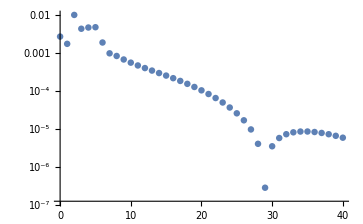

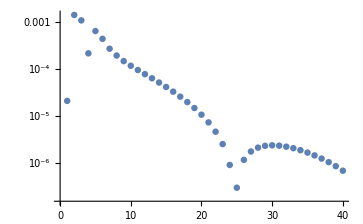

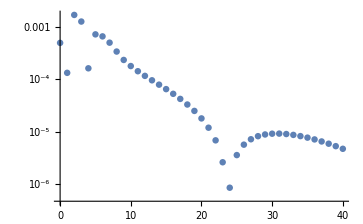

```mathematica
ListLogPlot[Abs@Table[{l,Sum[TllLeftInterpol[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
ListLogPlot[Abs@Table[{l,Sum[TlmLeftInterpol[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],{m,-l,l}]},{l,1,lmax}]]
ListLogPlot[Abs@Table[{l,Sum[TlnLeftInterpol[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
```

Compare large l behaviour of T_ll with its leading large l term.
Large difference is likely a consequence of the fact that large l behaviour of the metric perturbations and its derivatives are not the same.

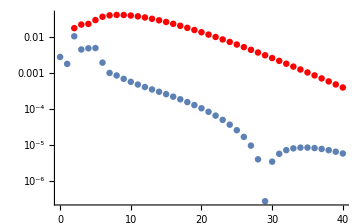

```mathematica
hPData=Table[{l,Sum[ l^2/(2 rmin^2) hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
Show[
ListLogPlot[Abs@Table[{l,Sum[TllLeftInterpol[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]],
ListLogPlot[Abs@hPData,PlotStyle->Red],PlotRange -> All
]
```

## Set geodesic quantities

Computation of the appropriate frequencies, energies and geodesics.

```mathematica
Clear[lmax,aKerr,wp,M,r0,rmin,rmax,p0,e0,rNumOutbd,rNumInbd,ρmin,ρmax,ρ0,eccentricity,ar,aϕ,at,Ωr,Ωθ,Ωφ,Orbit]
```

```mathematica
lmax=30;
lmaxCorrectorTensors=lmax;
```

```mathematica
aKerr=0;
wp = 64;
```

```mathematica
M=1;
r0=10 M; (* Make sure this is consistent with myr0 from puncture *)
rmin = r0-2M;
rmax = r0+2 M;
p0 = N[r0,wp]; (* approx needed if r0 and M are exact. *)
e0=0;
rNumInbd = rmin-4 M; (* numerical inner boundary *)
rNumOutbd = rmax+1200 M; (* numerical outer boundary *)
```

```mathematica
ρmin = ρOfrK[rmin];
ρmax = ρOfrK[rmax];
ρ0 = ρOfrK[r0];
eccentricity=0;
```

```mathematica
ar=aϕ=at=0;
```

```mathematica
{Ωr,Ωθ,Ωφ}=Values[KerrGeoFrequencies[0,p0,eccentricity,1]];
```

```mathematica
orbit=KerrGeoOrbit[aKerr,p0,eccentricity,1];
```

## Corrector tensor

## Theory

General corrector tensor is: x_ab = 2 m_((a)(m̄)_(b)) x_(m m̄) - 2 l_((a)(m̄)_(b)) x_nm-2 l_((a)m_(b)) x_(n m̄)+l_a l_b x_nn, see 1908.09095 eq. (55). Defined to satisfy (T_ab-(ℰx)_ab)l^a=0.
Note that x_la=x_mm=x_(m̄ m̄)=0. Only non-trivial pieces are x_nn, x_nm,x_(n m̄),x_(m̄ m̄). They are given by ODEs, see 2108.04273, eq. (56)-(61), and 1908.09095, eq. (58)-(61). See also comment on page 38.

## Boundary conditions

```mathematica
Clear[ρmax,rmax,rmin,ρmin]
```

### Theory/Notes

Can do this either by	1) evaluating the integrals in (59)-(61) in the reconstruction paper,
					2) Expand out LHS of (56)-(59) in reconstruction paper, setting x_ab → x_ab H(r_max-r), then equate the distributional pieces.
					Note: in the following, we always make sure the coefficients of the δ functions and its derivatives have been evaluated
					at r_min if this is not already the case.
					This is done using the usual identities:
					F(x) δ(x-x_0)   =     F(x_0) δ(x-x_0),
F(x) δ'(x-x_0) = -F'(x_0) δ(x-x_0) + F(x_0) δ'(x-x_0).
Make sure to account for the signature convention differences!
-Graphics-
Note: Be careful when making Mathematica integrate derivative of δ-function, as it can give the wrong answer. See example below.
To get right answer, make sure the argument of δ-function is of the form δ(x-x_0), so not generic δ(f(x))!

```mathematica
(* The below two integrals are the same up to coordinate transformation, and therefore should agree. The 2nd one gives the right answer. *)
rOfρ[ρ_]=1/ρ;
Assuming[{ϵ>0,ρ0>0},Integrate[ρ^(-4) DiracDelta'[rOfρ[ρ]-rOfρ[ρ0]],{ρ,ρ0-ϵ,ρ0+ϵ}]]/. ρ0->1/r0

Assuming[{ϵ>0,r0>0},Integrate[-r^2 DiracDelta'[r-r0],{r,r0-ϵ,r0+ϵ}]]
```

4 r0

2 r0

### For x_(m m̄)

#### Via Integration

Integrate (59) in reconstruction paper at r=r_min, so that only distributional pieces contribute.

```mathematica
Assuming[{ϵ>0,rmax>0,r1>0,r<rmax,ρ<0},-Integrate[r2^(-2) r1^2 (TllδCoeff[l,m] DiracDelta[r1-rmax]+TllδpCoeff[l,m] DiracDelta'[r1-rmax]),{r2,rmax+ϵ,r},{r1,rmax+ϵ,r2}]]/. r->-1/ρ/. rmax->-1/ρmax//Simplify
```

ConditionalExpression[((ρ-ρmax) TllδCoeff[l,m]+(2 ρ-ρmax) ρmax TllδpCoeff[l,m])/ρmax^2, ρ<0]

```mathematica
(*Clear[xmmbDistrContributionPiece,xmmbDistrContributionPieceAtRmax]
xmmbDistrContributionPiece[l_,m_][ρ_] = 
-((ρ-ρmin) TllδCoeff[l,m]+(2 ρ-ρmin) ρmin TllδpCoeff[l,m])/ρmin^2;
xmmbDistrContributionPieceAtRmax[l_,m_] = TllδpCoeff[l,m] /.  TllδpCoeff[l_,m_] -> TllδpRmaxInterpol[l,m];
Assuming[{ϵ>0,rmin>0,r1>0,r>rmin}, -Integrate[r2^(-2)r1^2 (TllδCoeff[l,m] DiracDelta[r1-rmin]+TllδpCoeff[l,m] DiracDelta'[r1-rmin]),{r2,rmin-ϵ,r},{r1,rmin-ϵ,r2}]] /. r -> -1/ρ /. rmin -> -1/ρmin // Simplify 

Assuming[{ϵ>0,rmax>0,r1>0,r<rmax},-Integrate[r2^(-2) r1^2 (TllδCoeff[l,m] DiracDelta[r1-rmax]+TllδpCoeff[l,m] DiracDelta'[r1-rmax]),{r2,rmax+ϵ,r},{r1,rmax+ϵ,r2}]]/. r->-1/ρ/. rmax->-1/ρmax//Simplify
 *)
```

```mathematica
Clear[xmmbDistrContributionPieceAtRmax]
```

```mathematica
xmmbDistrContributionPieceAtRmax[l_,m_][ρ_]=((ρ-ρmax) TllδCoeff[l,m]+(2 ρ-ρmax) ρmax TllδpCoeff[l,m])/ρmax^2/. {TllδCoeff[ll_,mm_]->TllδRmaxInterpol[ll,mm],TllδpCoeff[ll_,mm_]->TllδpRmaxInterpol[ll,mm]};
```

```mathematica
Clear[xmmbAtρmaxViaIntegration,xmmbpAtρmaxViaIntegration]
(* The delta functions are the only thing that will have non-vanihsing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xmmbAtρmaxViaIntegration[l_,m_] = xmmbDistrContributionPieceAtRmax[l,m][ρmax]// Simplify;
xmmbpAtρmaxViaIntegration[l_,m_] = xmmbDistrContributionPieceAtRmax[l,m]'[ρmax]// Simplify;
```

```mathematica
xmmbAtρmaxViaIntegration[2,2]
```

-1/(2 rmax)ⅇ^(-0.0632455532033675866399778708886543706743911027865043365371500971 ⅈ (rmax+2. Log[-1.+0.5 rmax])) InterpolatingFunction[…][-10+rmax]

```mathematica
(* The delta functions are the only thing that will have non-vanihsing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xmmbAtρmaxViaIntegration[l,m]
```

-1/(2 rmax)ⅇ^(-0.0316227766016837933199889354443271853371955513932521682685750485 ⅈ m (rmax+2. Log[-1.+0.5 rmax])) hSRightInterpol[3][l,m][-10+rmax]

#### Via ODE

Not evaluable.

Quantities evaluated at r_min are shown with a minus exponent: F^+ := F(r_max).
Eq. (56) is:   -r^-2 ∂_r (r^2 ∂_r (x_(m m̄) H(-r+r_max))) = T_ll.

```mathematica
Clear[m]
```

```mathematica
-r^(-2) D[r^2 D[xmmb[l,m][r] HeavisideTheta[-r+rmax],r],r] 
Collect[%,{DiracDelta[r-rmax],DiracDelta'[r-rmax]},Expand]
A=Coefficient[%,DiracDelta[-r+rmax] ]
B=Coefficient[%%,DiracDelta'[-r+rmax] ]
```

-1/r^2(2 r (-DiracDelta[-r+rmax] xmmb[l,m][r]+HeavisideTheta[-r+rmax] xmmb[l,m]'[r])+r^2 (xmmb[l,m][r] DiracDelta'[-r+rmax]-2 DiracDelta[-r+rmax] xmmb[l,m]'[r]+HeavisideTheta[-r+rmax] xmmb[l,m]''[r]))

(2 DiracDelta[-r+rmax] xmmb[l,m][r])/r-xmmb[l,m][r] DiracDelta'[-r+rmax]+2 DiracDelta[-r+rmax] xmmb[l,m]'[r]-(2 HeavisideTheta[-r+rmax] xmmb[l,m]'[r])/r-HeavisideTheta[-r+rmax] xmmb[l,m]''[r]

(2 xmmb[l,m][r])/r+2 xmmb[l,m]'[r]

-xmmb[l,m][r]

```mathematica
Clear[r,rmax,x,A,B];

lhs=-r^(-2) D[r^2 D[xmmb[l,m][r]  HeavisideTheta[rmax-r],r],r]//Expand;

canon=lhs/. {DiracDelta[-r+rmax]->DiracDelta[r-rmax],DiracDelta'[-r+rmax]->-DiracDelta'[r-rmax]};

canon=Expand[canon/. c_. DiracDelta'[r-rmax]:>(c/. r->rmax) DiracDelta'[r-rmax]-(D[c,r]/. r->rmax) DiracDelta[r-rmax]];

canon=Expand[canon/. c_. DiracDelta[r-rmax]:>(c/. r->rmax) DiracDelta[r-rmax]];

Collect[canon,{DiracDelta[r-rmax],DiracDelta'[r-rmax]}]
A=Coefficient[%,DiracDelta[r-rmax] ]
B=Coefficient[%%,DiracDelta'[r-rmax] ]
```

xmmb[l,m][rmax] DiracDelta'[r-rmax]-(2 HeavisideTheta[-r+rmax] xmmb[l,m]'[r])/r+DiracDelta[r-rmax] ((2 xmmb[l,m][rmax])/rmax+xmmb[l,m]'[rmax])-HeavisideTheta[-r+rmax] xmmb[l,m]''[r]

(2 xmmb[l,m][rmax])/rmax+xmmb[l,m]'[rmax]

xmmb[l,m][rmax]

```mathematica
ruletmp = Flatten@Solve[{A== TllδCoeff[l,m],
					B== TllδpCoeff[l,m]},{xmmb[l,m][rmax],xmmb[l,m]'[rmax]}] // Simplify
Clear[A,B]
```

{xmmb[l,m][rmax]→TllδpCoeff[l,m],xmmb[l,m]'[rmax]→TllδCoeff[l,m]-(2 TllδpCoeff[l,m])/rmax}

```mathematica
Clear[xmmbAtρminViaODE,xmmbpAtρminViaODE]
(* The delta functions are the only thing that will have non-vanihsing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xmmbAtρmaxViaODE[l_,m_] = xmmb[l,m][r] /. ruletmp/.r->rmax
xmmbpAtρmaxViaODE[l_,m_] = xmmb[l,m]'[r] /. ruletmp/.r->rmax
```

xmmb[l,m][rmax]

xmmb[l,m]'[rmax]

#### Check result from both method agree

Not evaluable.

Note that for differentiation, in the integration method, we differentiate with respect to ρ, while in the ODE method it is with respect to r, so need to adjust to this using ∂_ρ = ρ^2∂_r.

```mathematica
xmmbAtρmaxViaIntegration[l,m]  ==  xmmbAtρmaxViaODE[l,m] // Simplify
ρmin^2 xmmbpAtρmaxViaIntegration[l,m]  ==  xmmbpAtρmaxViaODE[l,m] /. ρmax->  ρOfrK[rmax] // Simplify
```

True

True

#### Set boundary conditions

```mathematica
Clear[xmmbAtρmax,xmmbpAtρmax]
(* The delta functions are the only thing that will have non-vanihsing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xmmbAtρmax[l_,m_] = xmmbAtρmaxViaIntegration[l,m]/. 
{TllδCoeff[l_,m_] -> TllδRmaxInterpol[l,m], TllδpCoeff[l_,m_] -> TllδpRmaxInterpol[l,m]}  // Simplify;
xmmbpAtρmax[l_,m_] = xmmbpAtρmaxViaIntegration[l,m]/. 
{TllδCoeff[l_,m_] -> TllδRmaxInterpol[l,m], TllδpCoeff[l_,m_] -> TllδpRmaxInterpol[l,m]}  // Simplify;
Clear[xmmbAtρmaxViaIntegration,xmmbpAtρmaxViaIntegration]
```

### For x_nm

We have two different kinds of contributions:
1) one coming from the stress energy T_lm (δ and δ’).
2) One coming from 𝒩x_(m m̄) (just a δ). This is because x_(m m̄) carries a Heaviside function around at -r+r_max
Specifically, we have  𝒩x_(m m̄)=-1/2 ðx_(m m̄) δ(-r+r_max) + # H(-r+r_max).
See section on Operators for more details.

#### Via Integration

Integrate (60) in reconstruction paper at r=r_max, so that only distributional pieces contribute.

```mathematica
Assuming[{ϵ>0,rmin>0,r1>0,r<rmax},-2 ρ^2 Simplify@Integrate[r2^2 (xnmIntegrandδCoeff[l,m]DiracDelta[r1-rmax]+xnmIntegrandδpCoeff[l,m] DiracDelta'[r1-rmax]),{r2,rmax+ϵ,r},{r1,rmax+ϵ,r2}]] /. r->-1/ρ/. rmax->-1/ρmax//Simplify
```

2/3 ρ^2 ((-1/ρ^3+1/ρmax^3) xnmIntegrandδCoeff[l,m]+(3 xnmIntegrandδpCoeff[l,m])/ρmax^2)

```mathematica
Clear[xnmDistrContributionPieceAtRmax]
xnmDistrContributionPieceAtRmax[l_,m_][ρ_] =  Assuming[{ϵ>0,rmin>0,r1>0,r<rmax},-2 ρ^2 Simplify@Integrate[r2^2 (xnmIntegrandδCoeff[l,m]DiracDelta[r1-rmax]+xnmIntegrandδpCoeff[l,m] DiracDelta'[r1-rmax]),{r2,rmax+ϵ,r},{r1,rmax+ϵ,r2}]] /. r->-1/ρ/. rmax->-1/ρmax//Simplify
```

2/3 ρ^2 ((-1/ρ^3+1/ρmax^3) xnmIntegrandδCoeff[l,m]+(3 xnmIntegrandδpCoeff[l,m])/ρmax^2)

```mathematica
Clear[xnmAtρmaxViaIntegration,xnmpAtρmaxViaIntegration]
(* The delta functions are the only thing that will have non-vanishing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xnmAtρmaxViaIntegration[l_,m_] = xnmDistrContributionPieceAtRmax[l,m][ρmax]// Simplify
xnmpAtρmaxViaIntegration[l_,m_] = xnmDistrContributionPieceAtRmax[l,m]'[ρmax]// Simplify
```

2 xnmIntegrandδpCoeff[l,m]

(2 (xnmIntegrandδCoeff[l,m]+2 ρmax xnmIntegrandδpCoeff[l,m]))/ρmax^2

Set up rule to account for all the contributions in the integration of δ and δ’.

```mathematica
Clear[𝒩xmmbδCoeffρmax,xnmIntegrationRule]
𝒩xmmbδCoeffρmax[l_,m_] =- 1/2 ðCK[0,l][xmmbAtρmax[l,m]] /. r -> rmax  (* check sign *) (* when evaluating Subscript[x, m m̄] at Subscript[r, max] we can simply take the value of the distributional parts as the integral over smooth bit is zero at Subscript[r, max] *)
xnmIntegrationRule = {xnmIntegrandδCoeff[l_,m_] -> TlmδRmaxInterpol[l,m]+𝒩xmmbδCoeffρmax[l,m],xnmIntegrandδpCoeff[l_,m_] -> TlmδpRmaxInterpol[l,m]}
```

-1/(4 √2 rmax^2)ⅇ^(-0.0316227766016837933199889354443271853371955513932521682685750485 ⅈ m (rmax+2. Log[-1.+0.5 rmax])) √(l (1+l)) hSRightInterpol[3][l,m][-10+rmax]

{xnmIntegrandδCoeff[l_,m_]→-1/(4 √2 rmax^2)ⅇ^(-0.0316227766016837933199889354443271853371955513932521682685750485 ⅈ m (rmax+2. Log[-1.+0.5 rmax])) √(l (1+l)) hSRightInterpol[3][l,m][-10+rmax]+1/(4 √2 √(l (1+l)) (-2+rmax) rmax^2)ⅇ^(-0.0316227766016837933199889354443271853371955513932521682685750485 ⅈ m (rmax+2 Log[-1+rmax/2])) ((-2+rmax) rmax dhSRightInterpol[4][l,m][-10+rmax]+ⅈ (2-rmax) rmax dhSRightInterpol[8][l,m][-10+rmax]-l rmax hSRightInterpol[1][l,m][-10+rmax]-l^2 rmax hSRightInterpol[1][l,m][-10+rmax]-l rmax hSRightInterpol[2][l,m][-10+rmax]-l^2 rmax hSRightInterpol[2][l,m][-10+rmax]-2 l hSRightInterpol[3][l,m][-10+rmax]-2 l^2 hSRightInterpol[3][l,m][-10+rmax]+l rmax hSRightInterpol[3][l,m][-10+rmax]+l^2 rmax hSRightInterpol[3][l,m][-10+rmax]-2 hSRightInterpol[4][l,m][-10+rmax]+rmax hSRightInterpol[4][l,m][-10+rmax]+0.0316227766016837933199889354443271853371955513932521682685750485 ⅈ m rmax^2 hSRightInterpol[5][l,m][-10+rmax]+2 l hSRightInterpol[6][l,m][-10+rmax]+2 l^2 hSRightInterpol[6][l,m][-10+rmax]-l rmax hSRightInterpol[6][l,m][-10+rmax]-l^2 rmax hSRightInterpol[6][l,m][-10+rmax]-2 hSRightInterpol[7][l,m][-10+rmax]+rmax hSRightInterpol[7][l,m][-10+rmax]+2 ⅈ hSRightInterpol[8][l,m][-10+rmax]-ⅈ rmax hSRightInterpol[8][l,m][-10+rmax]+0.0316227766016837933199889354443271853371955513932521682685750485 m rmax^2 hSRightInterpol[9][l,m][-10+rmax]+2 ⅈ hSRightInterpol[10][l,m][-10+rmax]-ⅈ rmax hSRightInterpol[10][l,m][-10+rmax]),xnmIntegrandδpCoeff[l_,m_]→(ⅇ^(-0.0316227766016837933199889354443271853371955513932521682685750485 ⅈ m (rmax+2 Log[-1+rmax/2])) (hSRightInterpol[4][l,m][-10+rmax]-ⅈ hSRightInterpol[8][l,m][-10+rmax]))/(4 √2 √(l (1+l)) rmax)}

#### Via ODE

Not evaluable.

Eq. (57) is:  -1/2 ∂_r (r^-2 ∂_r (r^2 x_nm H(-r+r_max))) = T_lm+𝒩x_(m m̄) = T_lm+1/2(∂_r +1/r)ðx_(m m̄)
LHS=(...)H(-r+r_max)+(1/r x_nm+x'_nm) δ(r-r_max)+1/2 x_nm δ'(r-r_max)
	=(...)H(-r+r_max)+(1/r_min x_nm^++1/2 x'_nm^+) δ(r-r_max)-1/2 x_nm^+δ'(r-r_max)
RHS term 1= (...)H(-r+r_max)+δT_lm^+ δ(r-r_max)+ΔT_lm^+ δ'(r-r_max)
RHS term 2 =  (...)H(-r+r_max)-1/2 ðx_(m m̄)^+ δ(r-r_max)
→ RHS =  (...)H(-r+r_max)+(δT_lm^+-1/2 ðx_(m m̄)^+) δ(r-r_max)+ΔT_lm^+ δ'(r-r_max)
⇒ x_nm^+ = 2 ΔT_lm^+,           x'_nm^+ = -(ð^-x_(m m̄)^++4/r_max ΔT_lm^+-2 δT_lm^+)

```mathematica
expr=-1/2 D[r^(-2) D[r^2 xnm[l,m][r] HeavisideTheta[rmax-r],r],r]//Expand;

exprCanon=expr/. {DiracDelta[-r+rmax]->DiracDelta[r-rmax],DiracDelta'[-r+rmax]->-DiracDelta'[r-rmax]};

exprCanon=Expand[exprCanon/. c_. DiracDelta'[r-rmax]:>(c/. r->rmax) DiracDelta'[r-rmax]-(D[c,r]/. r->rmax) DiracDelta[r-rmax]];

exprCanon=Expand[exprCanon/. c_. DiracDelta[r-rmax]:>(c/. r->rmax) DiracDelta[r-rmax]];

A=Coefficient[exprCanon,DiracDelta[r-rmax]];
B=Coefficient[exprCanon,DiracDelta'[r-rmax]];

ruletmp = Flatten@ Solve[{A==TlmδCoeff[l,m]-1/2 ðxmmb,B==TlmδpCoeff[l,m]},{xnm[l,m][rmax],xnm[l,m]'[rmax]}]//Simplify
```

{xnm[l,m][rmax]→2 TlmδpCoeff[l,m],xnm[l,m]'[rmax]→-ðxmmb+2 TlmδCoeff[l,m]-(4 TlmδpCoeff[l,m])/rmax}

```mathematica
Clear[xnmAtρmaxViaODE,xnmpAtρmaxODE]

(* The delta functions are the only thing that will have non-vanihsing contribution when evaluating Subscript[x, m m̄] at Subscript[r, max]. *)
xnmAtρmaxViaODE[l_,m_] = xnm[l,m][rmax] /. ruletmp
xnmpAtρmaxViaODE[l_,m_] = xnm[l,m]'[rmax] /. ruletmp
```

2 TlmδpCoeff[l,m]

-ðxmmb+2 TlmδCoeff[l,m]-(4 TlmδpCoeff[l,m])/rmax

#### Check result from both method agree

Not evaluable.

Note that for differentiation, in the integration method, we differentiate with respect to ρ, 
while in the ODE method it is with respect to r, so need to adjust to this using ∂_ρ = ρ^2∂_r

```mathematica
xnmAtρmaxViaIntegration[l,m] == xnmAtρmaxViaODE[l,m] /. xnmIntegrandδpCoeff[l_,m_][rmax] -> TlmδpCoeff[l,m]
ρmin^2 xnmpAtρmaxViaIntegration[l,m] == xnmpAtρmaxViaODE[l,m]  /. 
{xnmIntegrandδCoeff[l_,m_][rmax] -> TlmδCoeff[l,m]+1/2 ðCK[0,l][xmmb[l,m]],
xnmIntegrandδpCoeff[l_,m_][rmax] -> TlmδpCoeff[l,m]} /.  ðxmmb -> ðCK[0,l][xmmb[l,m]] /. r -> rmax /. ρmax -> -1/rmax // Simplify
```

2 xnmIntegrandδpCoeff[l,m]==2 TlmδpCoeff[l,m]

2 rmax ρmin^2 (rmax xnmIntegrandδCoeff[l,m]-2 xnmIntegrandδpCoeff[l,m])==(4 rmax TlmδCoeff[l,m]-8 TlmδpCoeff[l,m]+√2 √(l (1+l)) xmmb[l,m])/(2 rmax)

#### Set boundary conditions

```mathematica
Clear[xnmAtρmax,xnmpAtρmax]
xnmAtρmax[l_,m_] = xnmAtρmaxViaIntegration[l,m]/. xnmIntegrationRule  // Simplify;
xnmpAtρmax[l_,m_] = xnmpAtρmaxViaIntegration[l,m]/. xnmIntegrationRule// Simplify;
Clear[xnmAtρmaxViaIntegration,xnmpAtρmaxViaIntegration,xnmIntegrationRule]
```

```mathematica
xnmpAtρmax[2,2]/.rmax->12/.ρmax->ρOfrK[12]
```

-4.91023+1.95635 ⅈ

### For x_(n m̄)

Not evaluable.
Needed before because we would solve the ODE for x_(n m̄). Still keeping it for posterity.

We have two different kinds of contributions:
1) one coming from the stress energy T_lm (δ and δ’).
2) One coming from 𝒩̄ x_(m m̄) (just a δ). This is because x_(m m̄) carries a Heaviside function 
Specifically, we have  𝒩̄ x_(m m̄)=-1/2ð' x_(m m̄) δ(r-r_max) + # H(-r+r_max).

#### Via Integration

Integrate (60) in reconstruction paper at r=r_min, so that only distributional pieces contribute.

```mathematica
Clear[xnmbDistrContributionPieceAtrmax]
xnmbDistrContributionPieceAtrmax[l_,m_][ρ_] =2/3 ρ^2 ((-1/ρ^3+1/ρmax^3) xnmbIntegrandδCoeff[l,m][rmax]+(3 xnmbIntegrandδpCoeff[l,m][rmax])/ρmax^2)
(* Assuming[{ϵ>0,rmin>0,r1>0,r>rmin},-2 ρ^2 Simplify@Integrate[r2^2 (xnmbIntegrandδCoeff[l,m][rmin] DiracDelta[r1-rmin]+xnmbIntegrandδpCoeff[l,m][rmin] DiracDelta'[r1-rmin]),{r2,rmin-ϵ,r},{r1,rmin-ϵ,r2}]] *)
```

2/3 ρ^2 ((-1/ρ^3+1/ρmax^3) xnmbIntegrandδCoeff[l,m][rmax]+(3 xnmbIntegrandδpCoeff[l,m][rmax])/ρmax^2)

```mathematica
Clear[xnmbAtρminViaIntegration,xnmbpAtρminViaIntegration]
(* The delta functions are the only thing that will have non-vanishing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xnmbAtρminViaIntegration[l_,m_] = xnmbDistrContributionPieceAtrmax[l,m][ρmax]// Simplify;
xnmbpAtρminViaIntegration[l_,m_] = xnmbDistrContributionPieceAtrmax[l,m]'[ρmax]// Simplify;
```

Set up rule to account for all the contributions in the integration of δ and δ’

```mathematica
Clear[𝒩bxmmbδCoeff,xnmbIntegrationRule]
𝒩bxmmbδCoeffρmax[l_,m_] = -1/2 ðpCK[0,l][xmmbAtρmax[l,m]] /. r -> rmax; (* when evaluating Subscript[x, m m̄] at Subscript[r, min] we can simply take the value of the distributional parts as the integral over smooth bit is zero at Subscript[r, min] *)
xnmbIntegrationRule = {xnmbIntegrandδCoeff[l_,m_][rmax] -> TlmbδRmaxInterpol[l,m]+𝒩bxmmbδCoeffρmax[l,m],xnmbIntegrandδpCoeff[l_,m_][rmax] -> TlmbδpRmaxInterpol[l,m]};
```

#### Via ODE

Not evaluable.

```mathematica
-1/2 D[r^(-2) D[r^2 xnmb[l,m][r] HeavisideTheta[r-rmin],r],r] // Simplify;
Collect[%,{DiracDelta[r-rmin],DiracDelta'[r-rmin]},Simplify]
ruletmp = Flatten@Solve[{-xnmb[l,m]/rmin- xnmbp[l,m]/2 == TlmbδCoeff[l,m]+1/2 ðpxmmb,-1/2 xnmb[l,m] == TlmbδpCoeff[l,m]},{xnmb[l,m],xnmbp[l,m]}] // Simplify
```

-1/2 xnmb[l,m][r] DiracDelta'[r-rmin]-(DiracDelta[r-rmin] (xnmb[l,m][r]+r xnmb[l,m]'[r]))/r-(HeavisideTheta[r-rmin] (-2 xnmb[l,m][r]+r (2 xnmb[l,m]'[r]+r xnmb[l,m]''[r])))/(2 r^2)

{xnmb[l,m]→-2 TlmbδpCoeff[l,m],xnmbp[l,m]→-ðpxmmb-2 TlmbδCoeff[l,m]+(4 TlmbδpCoeff[l,m])/rmin}

```mathematica
Clear[xnmbAtρminViaODE,xnmbpAtρminViaODE]
(* The delta functions are the only thing that will have non-vanihsing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xnmbAtρminViaODE[l_,m_] = xnmb[l,m] /. ruletmp
xnmbpAtρminViaODE[l_,m_] = xnmbp[l,m] /. ruletmp
```

-2 TlmbδpCoeff[l,m]

-ðpxmmb-2 TlmbδCoeff[l,m]+(4 TlmbδpCoeff[l,m])/rmin

#### Check result from both method agree

Not evaluable.

Note that for differentiation, in the integration method, we differentiate with respect to ρ, while in the ODE method it is with respect to r, so need to adjust to this using ∂_ρ = ρ^2∂_r.

```mathematica
xnmbAtρminViaIntegration[l,m] == xnmbAtρminViaODE[l,m] /. xnmbIntegrandδpCoeff[l_,m_][rmin] -> TlmbδpCoeff[l,m]
ρmin^2 xnmbpAtρminViaIntegration[l,m] == xnmbpAtρminViaODE[l,m]  /. 
{xnmbIntegrandδCoeff[l_,m_][rmin] -> TlmbδCoeff[l,m]+1/2 ðpCK[0,l][xmmb[l,m]],xnmbIntegrandδpCoeff[l_,m_][rmin] -> TlmbδpCoeff[l,m]} /.  ðpxmmb -> ðpCK[0,l][xmmb[l,m]] /. r -> rmin /. ρmin -> -1/rmin // Simplify
```

True

True

#### Set boundary conditions

```mathematica
Clear[xnmbAtρmin,xnmbpAtρmin]
xnmbAtρmin[l_,m_] = xnmbAtρminViaIntegration[l,m]/. xnmbIntegrationRule  // Simplify;
xnmbpAtρmin[l_,m_] = xnmbpAtρminViaIntegration[l,m]/. xnmbIntegrationRule// Simplify;
Clear[xnmbAtρminViaIntegration,xnmbpAtρminViaIntegration,,xnmbIntegrationRule]
```

Clear::wrsym: Symbol Null is Protected.

### For x_nn

We have three different kinds of contributions:
1) one coming from the stress energy T_ln (δ and δ’).
2) One coming from 𝒰x_(m m̄) (a δ and δ’). Note that the δ’ needs to cancel with the one from the stress energy so that x_nn does not have a delta function. We do this consistency check below.
3) The last one coming from 𝒱x_nm and 𝒱x_(n m̄) (just a δ).

#### Via Integration

Integrate (60) in reconstruction paper at r=r_min, so that only distributional pieces contribute.

```mathematica
ϵ=.
```

```mathematica
Assuming[{ϵ>0,rmin>0,r1>0,r<rmax},-ρ Simplify@Integrate[r2^2 (xnnIntegrandδCoeff[l,m] DiracDelta[r2-rmax]+xnnIntegrandδpCoeff[l,m]DiracDelta'[r2-rmax]),{r2,rmax+ϵ,r}] ]/. r->-1/ρ/. rmax->-1/ρmax//Simplify
```

(ρ (xnnIntegrandδCoeff[l,m]+2 ρmax xnnIntegrandδpCoeff[l,m]))/ρmax^2

```mathematica
xnnDistrContributionPieceAtRmax[l_,m_][ρ_] = (ρ (xnnIntegrandδCoeff[l,m]+2 ρmax xnnIntegrandδpCoeff[l,m]))/ρmax^2
```

(ρ (xnnIntegrandδCoeff[l,m]+2 ρmax xnnIntegrandδpCoeff[l,m]))/ρmax^2

```mathematica
xnnAtρmaxViaIntegration[l_,m_] = xnnDistrContributionPieceAtRmax[l,m][ρmax]// Simplify
```

xnnIntegrandδCoeff[l,m]/ρmax+2 xnnIntegrandδpCoeff[l,m]

Set up rule to account for all the contributions in the integration of δ and δ’. See again the Operator section for more details.

```mathematica
Clear[𝒰xmmbδCoeff,𝒰xmmbδpCoeff,𝒱xnmδCoeff,𝒱bxnmbδCoeff,xnnIntegrationRule]
𝒰xmmbδCoeffρmax[l_,m_] = -(ⅈ m Ωφ+(2 f[rmax])/rmax) xmmbAtρmax[l,m]-1/2 f[rmax] ρmax^2 xmmbpAtρmax[l,m];
𝒰xmmbδpCoeffρmax[l_,m_] = -f[rmax]/2 xmmbNDSolveRight[l,m][ρmax]; 
𝒱xnmδCoeffρmax[l_,m_] =- (√(l (1+l)))/(2 √2 rmax)xnmAtρmax[l,m];
𝒱bxnmbδCoeffρmax[l_,m_] = (√(l (1+l)))/(2 √2 rmax)(-1)^(l+m+1) xnmAtρmax[l,m];
```

```mathematica
xnnIntegrationRule = {xnnIntegrandδCoeff[l_,m_]-> TlnδRmaxInterpol[l,m]+𝒰xmmbδCoeffρmax[l,m]+𝒱xnmδCoeffρmax[l,m] +𝒱bxnmbδCoeffρmax[l,m],xnnIntegrandδpCoeff[l_,m_] -> 0};
```

As stated above, x_nn should not have a δ piece. This δ piece occurs as a “boundary term” when integrating “by parts” the δ’ piece.
The coefficient of this piece is simply the coefficient of the δ’ piece of T_ln+ 𝒰x_(m m̄) evaluated at r_min.

```mathematica
Max@Abs[Table[TlnδpRminInterpol[l,m]+𝒰xmmbδpCoeff[l,m],{l,2,Min[10,lmaxCorrectorTensors]},{m,-l,l}]];
```

#### Via ODE

Not evaluable.

Eq. (58) is: r^2∂_r (r x_nn)=T_ln+𝒰x_(m m̄)+𝒱x_nm+𝒱̄ x_(n m̄)
LHS=(...)H(r_max-r)-1/r_max x_nn^+ δ(r-r_max)
RHS term 1= (...)H(r_max-r)+δT_ln^+ δ(r-r_max)+ΔT_ln^+ δ'(r-r_max)
RHS term 2 = (...)H(r_max-r)-(δ𝒰x_(m m̄))^+δ(r-r_max)+(Δ𝒰x_(m m̄))^+ δ'(r_max-r) = (...)H(-r+r_max)-((ⅈ m Ω_ϕ+(2 f^+)/r_max)x_(m m̄)^++f^+/2 x'_(m m̄)^+) δ(r-r_max)-f^+/2 x_(m m̄)^+δ'(r-r_max)
RHS term 3 = (...)H(-r+r_max)-(𝒱x_nm)^+δ(r-r_max) = (...)H(-r+r_max)-(√(l (l+1)))/(2 √2 r_max)x_nm^+ δ(r-r_max)
RHS term 4 == (...)H(-r+r_max)-(𝒱x_(n m̄))^+δ(r-r_max)  = (...)H(-r+r_max)-(√(l (l+1)))/(2 √2 r_max)x_(n m̄)^+ δ(r-r_max)
⇒RHS = (...)H(-r+r_max)+(δT_ln^+-(ⅈ m Ω_ϕ+(2 f^+)/r_max)x_(m m̄)^+-f^+/2 x'_(m m̄)^+-(√(l (l+1)))/(2 √2 r_max)x_nm^++(√(l (l+1)))/(2 √2 r_max)x_(n m̄)^+) δ(r-r_max)+(ΔT_ln^+-f^+/2 x_(m m̄)^+)δ'(r-r_max)

Can check that the δ'(r-r_max) piece vanishes: ΔT_ln^++(Δ𝒰x_(m m̄))^+ = ΔT_ln^+-f^+/2 x_(m m̄)^+= 0.

```mathematica
lhs= r^(-2) D[r xnn[l,m][r] HeavisideTheta[-r+rmax],r] // Simplify;
```

```mathematica
canon=lhs/. {DiracDelta[-r+rmax]->DiracDelta[r-rmax],DiracDelta'[-r+rmax]->-DiracDelta'[r-rmax]};

canon=Expand[canon/. c_. DiracDelta'[r-rmax]:>(c/. r->rmax) DiracDelta'[r-rmax]-(D[c,r]/. r->rmax) DiracDelta[r-rmax]];

canon=Expand[canon/. c_. DiracDelta[r-rmax]:>(c/. r->rmax) DiracDelta[r-rmax]];

A=Coefficient[canon,DiracDelta[r-rmax]];
B=Coefficient[canon,DiracDelta'[r-rmax]];
```

```mathematica
A
```

-(xnn[l,m][rmax])/rmax

```mathematica
B
```

0

```mathematica
ruletmp=Flatten@Solve[{-xnn[l,m]/rmax == TlnδCoeff[l,m]+δUxmmb[l,m] + δVxnm[l,m] +δVbxnmb[l,m]},xnn[l,m]] // Simplify
```

{xnn[l,m]→-rmax (TlnδCoeff[l,m]+δUxmmb[l,m]+δVbxnmb[l,m]+δVxnm[l,m])}

```mathematica
Clear[xnnAtρmaxViaODE]
(* The delta functions are the only thing that will have non-vanishing contribution when evaluating Subscript[x, m m̄] at Subscript[r, min]. *)
xnnAtρmaxViaODE[l_,m_] = xnn[l,m] /. ruletmp
```

-rmax (TlnδCoeff[l,m]+δUxmmb[l,m]+δVbxnmb[l,m]+δVxnm[l,m])

#### Check result from both method agree

Not evaluable.

Note that for differentiation, in the integration method, we differentiate with respect to ρ, while in the ODE method it is with respect to r, so need to adjust to this using ∂_ρ = ρ^2∂_r.
Also, the below assumes that the δ’ piece vanishes at r_min.

```mathematica
xnnAtρmaxViaIntegration[l,m] == xnnAtρmaxViaODE[l,m] /.{
xnnIntegrandδCoeff[l_,m_][rmax] -> TlnδCoeff[l,m]+δUxmmb[l,m]+δVbxnmb[l,m]+δVxnm[l,m],
xnnIntegrandδpCoeff[l_,m_][rmax] ->0} /. ρmax -> -1/rmax // Simplify
```

2 xnnIntegrandδpCoeff[l,m]+rmax (TlnδCoeff[l,m]+δUxmmb[l,m]+δVbxnmb[l,m]+δVxnm[l,m])==rmax xnnIntegrandδCoeff[l,m]

#### Set boundary conditions

```mathematica
Clear[xnnAtρmax,xnnpAtρmax]
xnnAtρmax[l_,m_] = xnnAtρmaxViaIntegration[l,m]/. xnnIntegrationRule  // Simplify;
(*Clear[xnnAtρmaxViaIntegration,xnnIntegrationRule]*)
```

```mathematica
xnnAtρmax[2,2] /.rmax->12/.ρmax->ρOfrK[12]
```

-0.0933938+0.13412 ⅈ

## Solve coupled ODE system

```mathematica
rmax=r0+2M;
rmin=r0-2M;
ρmax=ρOfrK[rmax];
ρmin=ρOfrK[rmin];
```

For x_(m m̄) and x_nn, need to solve starting at l=0. For x_nm, need to start at l=1. What we do is, we still solve the equation for x_nm for l=0, but set everything to zero. x_nm is then zero, although its value should never matter.

Also, from usual properties of spin weighted harmonics and that x_(n m̄)=x_nm^*, we have x_(n m̄)^lm = (-1)^(m+1) (x_nm^(l-m))^*. Furthermore, checked explicitly that the following holds:   x_ab^(l-m) = (-1)^l (x_ab^lm)^* (see section “Check --- Reality conditions” below).
Therefore, we have the simple relation:  x_(n m̄)^lm = (-1)^(l+m+1) x_nm^lm, which we use below.

```mathematica
Clear[xmmbNDSolveLeft,xnmNDSolveLeft,xnnNDSolveLeft,xmmbNDSolveRight,xnmNDSolveRight,xnnNDSolveRight]

(*----------------------------------------------------------------------*)
(*First:solve right patch inward from rhoMax to rho0*)(*----------------------------------------------------------------------*)
Monitor[
Do[
{xmmbNDSolveRight[l,m],xnmNDSolveRight[l,m],xnnNDSolveRight[l,m]}=
NDSolveValue[
{
(* xmmb*)
-ρ^4 myxmmb[l,m]''[ρ]==TllRightInterpol[l,m][rOfρK[ρ]],
myxmmb[l,m][ρmax]==xmmbAtρmax[l,m],
myxmmb[l,m]'[ρmax]==xmmbpAtρmax[l,m],
(*xnm *)
-ρ^2/2 D[ρ^4 D[myxnm[l,m][ρ]/ρ^2,ρ],ρ]==
If[l==0,0,TlmRightInterpol[l,m][rOfρK[ρ]]+𝒩NullKρ[0,l][myxmmb[l,m][ρ]]],
myxnm[l,m][ρmax]==If[l==0,0,xnmAtρmax[l,m]],
myxnm[l,m]'[ρmax]==If[l==0,0,xnmpAtρmax[l,m]],
(* xnn *)
-ρ^4 D[myxnn[l,m][ρ]/ρ,ρ]==TlnRightInterpol[l,m][rOfρK[ρ]]+𝒰NullKρ[myxmmb[l,m][ρ]]+𝒱NullKρ[myxnm[l,m][ρ]]+𝒱bNullKρ[(-1)^(l+m+1) myxnm[l,m][ρ]],
myxnn[l,m][ρmax]==xnnAtρmax[l,m]
},
{myxmmb[l,m],myxnm[l,m],myxnn[l,m]},{ρ,ρmax,ρ0},
AccuracyGoal->20,PrecisionGoal->13,InterpolationOrder->All,MaxStepSize->0.001
];
If[m!=0,xmmbNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[xmmbNDSolveRight[l,m][ρ]];
xnmNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[xnmNDSolveRight[l,m][ρ]];
xnnNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[xnnNDSolveRight[l,m][ρ]];];,
{l,0,lmaxCorrectorTensors},
{m,0,l}
],
{l,m}
]//Timing
```

{20.4784,Null}

```mathematica
(*----------------------------------------------------------------------*)
(*Second:solve left patch inward from rho0 to rhoMin*)
(*----------------------------------------------------------------------*)
Monitor[
Do[
{xmmbNDSolveLeft[l,m],xnmNDSolveLeft[l,m],xnnNDSolveLeft[l,m]}=
NDSolveValue[
(*xmmb*)
{-ρ^4 myxmmb[l,m]''[ρ]==TllLeftInterpol[l,m][rOfρK[ρ]],
myxmmb[l,m][ρ0]==xmmbNDSolveRight[l,m][ρ0],
myxmmb[l,m]'[ρ0]==xmmbNDSolveRight[l,m]'[ρ0],
(* xnm *)
-ρ^2/2 D[ρ^4 D[myxnm[l,m][ρ]/ρ^2,ρ],ρ]==If[l==0,0,TlmLeftInterpol[l,m][rOfρK[ρ]]+𝒩NullKρ[0,l][myxmmb[l,m][ρ]]],myxnm[l,m][ρ0]==xnmNDSolveRight[l,m][ρ0],
myxnm[l,m]'[ρ0]==xnmNDSolveRight[l,m]'[ρ0],
(* xnn *)
-ρ^4 D[myxnn[l,m][ρ]/ρ,ρ]==TlnLeftInterpol[l,m][rOfρK[ρ]]+𝒰NullKρ[myxmmb[l,m][ρ]]+𝒱NullKρ[myxnm[l,m][ρ]]+𝒱bNullKρ[(-1)^(l+m+1) myxnm[l,m][ρ]],
myxnn[l,m][ρ0]==xnnNDSolveRight[l,m][ρ0]},
{myxmmb[l,m],myxnm[l,m],myxnn[l,m]},
{ρ,ρ0,ρmin},
AccuracyGoal->20,PrecisionGoal->13,InterpolationOrder->All,MaxStepSize->0.001];
If[m!=0,xmmbNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[xmmbNDSolveLeft[l,m][ρ]];
xnmNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[xnmNDSolveLeft[l,m][ρ]];
xnnNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[xnnNDSolveLeft[l,m][ρ]];];,
{l,0,lmaxCorrectorTensors},
{m,0,l}
],
{l,m}
]//Timing
```

{21.5376,Null}

```mathematica
Clear[xmmbNDSolve,xnmNDSolve,xnmbNDSolve,xnnNDSolve]

xmmbNDSolve[l_,m_][r_]=Piecewise[{{xmmbNDSolveLeft[l,m][ρOfrK[r]],r<=r0},{xmmbNDSolveRight[l,m][ρOfrK[r]],r>r0}}];

xnmNDSolve[l_,m_][r_]=Piecewise[{{xnmNDSolveLeft[l,m][ρOfrK[r]],r<=r0},{xnmNDSolveRight[l,m][ρOfrK[r]],r>r0}}];

xnmbNDSolve[l_,m_][r_]=(-1)^(l+m+1)
Piecewise[{{xnmNDSolveLeft[l,m][ρOfrK[r]],r<=r0},{xnmNDSolveRight[l,m][ρOfrK[r]],r>r0}}];

xnnNDSolve[l_,m_][r_]=Piecewise[{{xnnNDSolveLeft[l,m][ρOfrK[r]],r<=r0},{xnnNDSolveRight[l,m][ρOfrK[r]],r>r0}}];
```

(-1)^(1+l+m)

```mathematica
(*Clear[xmmbNDSolveLeft,xnmNDSolveLeft,xnnNDSolveLeft,xmmbNDSolveRight,xnmNDSolveRight,xnnNDSolveRight]
Monitor[Do[{xmmbNDSolveLeft[l,m],xnmNDSolveLeft[l,m],xnnNDSolveLeft[l,m]} = NDSolveValue[{
	-ρ^4 myxmmb[l,m]''[ρ] ==  TllLeftInterpol[l,m][rOfρK[ρ]],
	myxmmb[l,m][ρmin] == xmmbAtρmin[l,m],
	myxmmb[l,m]'[ρmin] ==  xmmbpAtρmin[l,m],

	-ρ^2/2 D[ρ^4 D[myxnm[l,m][ρ]/ρ^2,ρ],ρ] ==If[l == 0,0,TlmLeftInterpol[l,m][rOfρK[ρ]]+𝒩NullKρ[0,l][myxmmb[l,m][ρ]]],
	myxnm[l,m][ρmin] == If[l == 0,0,xnmAtρmin[l,m]],
	myxnm[l,m]'[ρmin] == If[l==0,0,xnmpAtρmin[l,m]],

(* ρ^2/2 D[ρ^4 D[myxnmb[l,m][ρ]/ρ^2,ρ],ρ] ==If[l == 0,0,TlmbLeftInterpol[l,m][rOfρK[ρ]]+𝒩bNullKρ[0,l][myxmmb[l,m][ρ]]],
	myxnmb[l,m][ρmin] == If[l == 0,0,xnmbAtρmin[l,m]],
	myxnmb[l,m]'[ρmin] == If[l == 0,0,xnmbpAtρmin[l,m]],
*)

	-ρ^4 D[myxnn[l,m][ρ]/ρ,ρ] ==TlnLeftInterpol[l,m][rOfρK[ρ]]+𝒰NullKρ[myxmmb[l,m][ρ]]+𝒱NullKρ[myxnm[l,m][ρ]]+𝒱bNullKρ[(-1)^(l+m+1) myxnm[l,m][ρ]] ,
	myxnn[l,m][ρmin] == xnnAtρmin[l,m]},
{myxmmb[l,m],myxnm[l,m],myxnn[l,m]},{ρ,ρmin,ρ0},AccuracyGoal->20,PrecisionGoal->13,InterpolationOrder->All,MaxStepSize->0.001];

If[m !=0,xmmbNDSolveLeft[l,-m][ρ_] = (-1)^l Conjugate[xmmbNDSolveLeft[l,m][ρ]]];
If[m !=0,xnmNDSolveLeft[l,-m][ρ_] = (-1)^l Conjugate[xnmNDSolveLeft[l,m][ρ]]];
If[m !=0,xnnNDSolveLeft[l,-m][ρ_] = (-1)^l Conjugate[xnnNDSolveLeft[l,m][ρ]]]

,{l,0,lmaxCorrectorTensors},{m,0,l}]
,{l,m}] // Timing
*)
```

```mathematica
(*Monitor[Do[{xmmbNDSolveRight[l,m],xnmNDSolveRight[l,m],xnnNDSolveRight[l,m]} = NDSolveValue[{
	-ρ^4 myxmmb[l,m]''[ρ] ==  TllRightInterpol[l,m][rOfρK[ρ]],
	myxmmb[l,m][ρ0] == xmmbNDSolveLeft[l,m][ρ0],
	myxmmb[l,m]'[ρ0] ==  xmmbNDSolveLeft[l,m]'[ρ0],

	-ρ^2/2 D[ρ^4 D[myxnm[l,m][ρ]/ρ^2,ρ],ρ] ==If[l == 0,0,TlmRightInterpol[l,m][rOfρK[ρ]]]+𝒩NullKρ[0,l][myxmmb[l,m][ρ]],
	myxnm[l,m][ρ0] ==xnmNDSolveLeft[l,m][ρ0],
	myxnm[l,m]'[ρ0] == xnmNDSolveLeft[l,m]'[ρ0],

(* ρ^2/2 D[ρ^4 D[myxnmb[l,m][ρ]/ρ^2,ρ],ρ] ==If[l == 0,0,TlmbRightInterpol[l,m][rOfρK[ρ]]]+𝒩bNullKρ[0,l][myxmmb[l,m][ρ]],
	myxnmb[l,m][ρ0] == xnmbNDSolveLeft[l,m][ρ0],
	myxnmb[l,m]'[ρ0] == xnmbNDSolveLeft[l,m]'[ρ0],
*)

	-ρ^4 D[myxnn[l,m][ρ]/ρ,ρ] ==TlnRightInterpol[l,m][rOfρK[ρ]]+𝒰NullKρ[myxmmb[l,m][ρ]]+𝒱NullKρ[myxnm[l,m][ρ]]+𝒱bNullKρ[(-1)^(l+m+1) myxnm[l,m][ρ]] ,
	myxnn[l,m][ρ0] == xnnNDSolveLeft[l,m][ρ0]},
{myxmmb[l,m],myxnm[l,m],myxnn[l,m]},{ρ,ρ0,ρmax},AccuracyGoal->20,PrecisionGoal->13,InterpolationOrder->All,MaxStepSize->0.001];

If[m !=0,xmmbNDSolveRight[l,-m][ρ_] = (-1)^l Conjugate[xmmbNDSolveRight[l,m][ρ]];
		xnmNDSolveRight[l,-m][ρ_] = (-1)^l Conjugate[xnmNDSolveRight[l,m][ρ]];
		xnnNDSolveRight[l,-m][ρ_] = (-1)^l Conjugate[xnnNDSolveRight[l,m][ρ]]]

,{l,0,lmaxCorrectorTensors},{m,0,l}]
,{l,m}]*)
```

```mathematica
(*Clear[xmmbNDSolve,xnmNDSolve,xnmbNDSolve,xnnNDSolve]
xmmbNDSolve[l_,m_][r_] = Piecewise[{{xmmbNDSolveLeft[l,m][ρOfrK[r]],r≤r0},{xmmbNDSolveRight[l,m][ρOfrK[r]],r>r0}}];
xnmNDSolve[l_,m_][r_] = Piecewise[{{xnmNDSolveLeft[l,m][ρOfrK[r]],r≤r0},{xnmNDSolveRight[l,m][ρOfrK[r]],r>r0}}];
xnmbNDSolve[l_,m_][r_] = (-1)^(l+m+1) Piecewise[{{xnmNDSolveLeft[l,m][ρOfrK[r]],r≤r0},{xnmNDSolveRight[l,m][ρOfrK[r]],r>r0}}];
xnnNDSolve[l_,m_][r_] = Piecewise[{{xnnNDSolveLeft[l,m][ρOfrK[r]],r≤r0},{xnnNDSolveRight[l,m][ρOfrK[r]],r>r0}}];*)
```

## Solve coupled ODE - reduction of order

```mathematica
ruletmp={myxmmb[l_,m_]'[ρ_]->dρmyxmmb[l,m][ρ],myxmmb[l_,m_]''[ρ_]->dρmyxmmb[l,m]'[ρ],myxnm[l_,m_]'[ρ_]->dρmyxnm[l,m][ρ]};
```

```mathematica
Monitor[
Do[
{xmmbNDSolveRight[l,m],dρxmmbNDSolveRight[l,m],xnmNDSolveRight[l,m],dρxnmNDSolveRight[l,m],xnnNDSolveRight[l,m]}=
NDSolveValue[
{ρ^4 dρmyxmmb[l,m]'[ρ]==TllRightInterpol[l,m][rOfρK[ρ]],
myxmmb[l,m]'[ρ]==dρmyxmmb[l,m][ρ],
myxmmb[l,m][ρmax]==xmmbAtρmax[l,m],
dρmyxmmb[l,m][ρmax]==xmmbpAtρmax[l,m],
-ρ^2 myxnm[l,m][ρ]+1/2 ρ^4 dρmyxnm[l,m]'[ρ]==If[l==0,0,(TlmRightInterpol[l,m][rOfρK[ρ]]+𝒩NullKρ[0,l][myxmmb[l,m][ρ]]/. ruletmp)],myxnm[l,m]'[ρ]==dρmyxnm[l,m][ρ],myxnm[l,m][ρmax]==If[l==0,0,xnmAtρmax[l,m]],
dρmyxnm[l,m][ρmax]==If[l==0,0,xnmpAtρmax[l,m]],ρ^4 D[myxnn[l,m][ρ]/ρ,ρ]==(TlnRightInterpol[l,m][rOfρK[ρ]]+𝒰NullKρ[myxmmb[l,m][ρ]]+𝒱NullKρ[myxnm[l,m][ρ]]+𝒱bNullKρ[(-1)^(l+m+1) myxnm[l,m][ρ]]/. ruletmp),myxnn[l,m][ρmax]==xnnAtρmax[l,m]},
{myxmmb[l,m],dρmyxmmb[l,m],myxnm[l,m],dρmyxnm[l,m],myxnn[l,m]},
{ρ,ρmax,ρ0},
AccuracyGoal->15,PrecisionGoal->13
];
If[m!=0,xmmbNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[xmmbNDSolveRight[l,m][ρ]];
dρxmmbNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[dρxmmbNDSolveRight[l,m][ρ]];
xnmNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[xnmNDSolveRight[l,m][ρ]];
dρxnmNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[dρxnmNDSolveRight[l,m][ρ]];
xnnNDSolveRight[l,-m][ρ_]=(-1)^l Conjugate[xnnNDSolveRight[l,m][ρ]];];,
{l,0,lmaxCorrectorTensors},
{m,0,l}],
{l,m}]//Timing
```

{133.693,Null}

```mathematica
Monitor[
Do[
{xmmbNDSolveLeft[l,m],dρxmmbNDSolveLeft[l,m],xnmNDSolveLeft[l,m],dρxnmNDSolveLeft[l,m],xnnNDSolveLeft[l,m]}=
NDSolveValue[
{ρ^4 dρmyxmmb[l,m]'[ρ]==TllLeftInterpol[l,m][rOfρK[ρ]],
myxmmb[l,m]'[ρ]==dρmyxmmb[l,m][ρ],myxmmb[l,m][ρ0]==xmmbNDSolveRight[l,m][ρ0],
dρmyxmmb[l,m][ρ0]==dρxmmbNDSolveRight[l,m][ρ0],
-ρ^2 myxnm[l,m][ρ]+1/2 ρ^4 dρmyxnm[l,m]'[ρ]==If[l==0,0,(TlmLeftInterpol[l,m][rOfρK[ρ]]+𝒩NullKρ[0,l][myxmmb[l,m][ρ]]/. ruletmp)],myxnm[l,m]'[ρ]==dρmyxnm[l,m][ρ],
myxnm[l,m][ρ0]==xnmNDSolveRight[l,m][ρ0],
dρmyxnm[l,m][ρ0]==dρxnmNDSolveRight[l,m][ρ0],ρ^2 (-myxnn[l,m][ρ]+ρ myxnn[l,m]'[ρ])==(TlnLeftInterpol[l,m][rOfρK[ρ]]+𝒰NullKρ[myxmmb[l,m][ρ]]+𝒱NullKρ[myxnm[l,m][ρ]]+𝒱bNullKρ[(-1)^(l+m+1) myxnm[l,m][ρ]]/. ruletmp),myxnn[l,m][ρ0]==xnnNDSolveRight[l,m][ρ0]},
{myxmmb[l,m],dρmyxmmb[l,m],myxnm[l,m],dρmyxnm[l,m],myxnn[l,m]},
{ρ,ρ0,ρmin},
AccuracyGoal->15,PrecisionGoal->13
];
If[m!=0,xmmbNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[xmmbNDSolveLeft[l,m][ρ]];
dρxmmbNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[dρxmmbNDSolveLeft[l,m][ρ]];
xnmNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[xnmNDSolveLeft[l,m][ρ]];
dρxnmNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[dρxnmNDSolveLeft[l,m][ρ]];
xnnNDSolveLeft[l,-m][ρ_]=(-1)^l Conjugate[xnnNDSolveLeft[l,m][ρ]];];,
{l,0,lmaxCorrectorTensors},
{m,0,l}],{l,m}]//Timing
```

## Corrector Tensors

```mathematica
Clear[xll,xln,xlm,xlmb,xnn,xnm,xnmb,xmm,xmmb,xmbmb]
xll[l_,m_][r_] = 0;
xln[l_,m_][r_] = 0;
xlm[l_,m_][r_] = 0;
xlmb[l_,m_][r_] = 0;
xnn[l_,m_][r_] = xnnNDSolve[l,m][r];
xnm[l_,m_][r_] = xnmNDSolve[l,m][r];
xnmb[l_,m_][r_] = xnmbNDSolve[l,m][r];
xmm[l_,m_][r_] = 0;
xmmb[l_,m_][r_] = xmmbNDSolve[l,m][r];
xmbmb[l_,m_][r_] = 0;
```

## Check --- Boundary conditions

For derivative, need to correctly transform differentiation with respect to r and ρ.

```mathematica
Max@Abs@Table[xmmbNDSolve[l,m][rmax]-xmmbAtρmax[l,m],{l,2,10},{m,-l,l}]
Max@Abs@Table[rmax^2 xmmbNDSolve[l,m]'[rmax]-xmmbpAtρmax[l,m],{l,2,10},{m,-l,l}]
Max@Abs@Table[xnmNDSolve[l,m][rmax]-xnmAtρmax[l,m],{l,2,10},{m,-l,l}]
Max@Abs@Table[rmax^2 xnmNDSolve[l,m]'[rmax]-xnmpAtρmax[l,m],{l,2,10},{m,-l,l}]
(*Max@Abs@Table[xnmbNDSolve[l,m][rmax]-xnmbAtρmax[l,m],{l,2,10},{m,-l,l}]
Max@Abs@Table[rmax^2 xnmbNDSolve[l,m]'[rmax]-xnmbpAtρmax[l,m],{l,2,10},{m,-l,l}]*)
Max@Abs@Table[xnnNDSolve[l,m][rmax]-xnnAtρmax[l,m],{l,2,10},{m,-l,l}]
```

0.

4.44089×10^-16

0.

2.48253×10^-16

0.

## Check --- (T_ab-(ℰx)_ab)l^a=0

Note: to correctly run this, you will need to recompute ℰhPWorldtubePiece and make sure that the metric is still written in the format “hNullK[a,b]”. Also, make sure that equations are written assuming u slicing.

In section “Check --- ℰ_ab(h^Res+h^P+x_ab) = 0” checked also that the δ and δ’ pieces vanish.

### Set-up

```mathematica
(* Should not set the geodesic quantities before running this! *)
Clear[TllTerm,TlmTerm,TlmbTerm,TlnTerm]
TllTerm[l_,m_][ρ_] =Piecewise[{{TllLeftInterpol[l,m][rOfρK[ρ]],ρ<ρ0},{TllRightInterpol[l,m][rOfρK[ρ]],ρ>ρ0}},Indeterminate] // Simplify[#,Assumptions->simplifyRule]&;
TlmTerm[l_,m_][ρ_] =Piecewise[{{TlmLeftInterpol[l,m][rOfρK[ρ]],ρ<ρ0},{TlmRightInterpol[l,m][rOfρK[ρ]],ρ>ρ0}},Indeterminate] // Simplify[#,Assumptions->simplifyRule]&;
TlmbTerm[l_,m_][ρ_] =Piecewise[{{TlmbLeftInterpol[l,m][rOfρK[ρ]],ρ<ρ0},{TlmbRightInterpol[l,m][rOfρK[ρ]],ρ>ρ0}},Indeterminate] // Simplify[#,Assumptions->simplifyRule]&;
TlnTerm[l_,m_][ρ_] =Piecewise[{{TlnLeftInterpol[l,m][rOfρK[ρ]],ρ<ρ0},{TlnRightInterpol[l,m][rOfρK[ρ]],ρ>ρ0}},Indeterminate] // Simplify[#,Assumptions->simplifyRule]&;
```

### T_ll-(ℰh)_ll

```mathematica
rGrid = Table[rmin+i (rmax-rmin)/60,{i,0,60}];
```

```mathematica
Clear[ℰxllPiece]
ℰxllPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[1]] /. hNullK[a_,b_][l_,m_] -> Function[r,xab[a,b][l,m][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
(*xab[2,2] -> xnn,*)
(*xab[2,3] -> xnm,
xab[2,4] -> xnmb,*)
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmbNDSolve[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbNDSolve[l,m]'[r],
xab[3,4][l_,m_]''[r_] ->xmmbNDSolve[l,m]''[r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

{0.012451,Null}

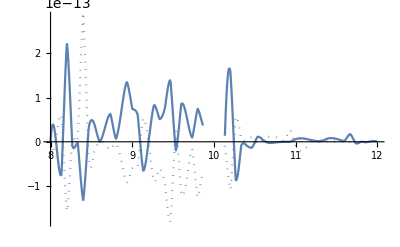

```mathematica
myl = 2;mym=2;
quotientGrid = Table[{rGrid[[i]],
TllTerm[myl,mym][-1/rGrid[[i]]]-ℰxllPiece[myl,mym][rGrid[[i]]]} ,{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,rmin,rmax},PlotRange->All]
(*Max@Abs@Transpose[quotientGrid][[2]]*)
```

### T_lm-(ℰh)_lm

```mathematica
rGrid = Table[rmin+i (rmax-rmin)/60,{i,0,60}];
```

```mathematica
Clear[ℰxlmPiece]
ℰxlmPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[3]] /. hNullK[a_,b_][l_,m_] -> Function[r,xab[a,b][l,m][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
(*xab[2,2] -> xnn,*)
xab[2,3][l_,m_][r_] -> xnmNDSolve[l,m][r],
xab[2,3][l_,m_]'[r_] -> xnmNDSolve[l,m]'[r],
xab[2,3][l_,m_]''[r_] -> xnmNDSolve[l,m]''[r],
(*xab[2,4] -> xnmb,*)
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmbNDSolve[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbNDSolve[l,m]'[r],
xab[3,4][l_,m_]''[r_] -> xmmbNDSolve[l,m]''[r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

{0.035812,Null}

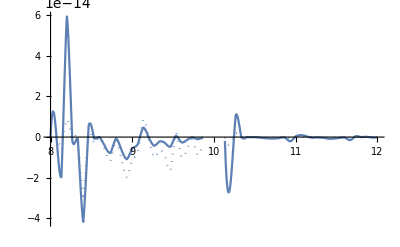

```mathematica
myl = 2;mym=2;
quotientGrid = Table[{rGrid[[i]],TlmTerm[myl,mym][-1/rGrid[[i]]]-ℰxlmPiece[myl,mym][rGrid[[i]]]},{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,rmin,rmax},PlotRange->All]
```

### T_(l m̄)-(ℰh)_(l m̄)

```mathematica
rGrid = Table[rmin+i (rmax-rmin)/60,{i,0,60}];
```

```mathematica
Clear[ℰxlmbPiece]
ℰxlmbPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[4]] /. hNullK[aVal_,bVal_][l_,m_] -> Function[r,xab[aVal,bVal][l,m][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
(*xab[2,2] -> xnn,*)
xab[2,3][l_,m_] -> Function[r,0],
xab[2,4][l_,m_][r_] -> xnmbNDSolve[l,m][r],
xab[2,4][l_,m_]'[r_] -> xnmbNDSolve[l,m]'[r],
xab[2,4][l_,m_]''[r_] -> xnmbNDSolve[l,m]''[r],
(*xab[2,4] -> xnmb,*)
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmbNDSolve[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbNDSolve[l,m]'[r],
xab[3,4][l_,m_]''[r_] -> xmmbNDSolve[l,m]''[r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

{0.03426,Null}

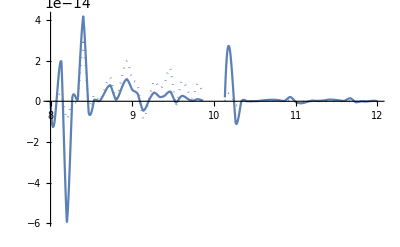

```mathematica
myl = 2;mym=2;
quotientGrid = Table[{rGrid[[i]],TlmbTerm[myl,mym][-1/rGrid[[i]]]-ℰxlmbPiece[myl,mym][rGrid[[i]]]},{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,rmin,rmax},PlotRange->All]
```

### T_ln-(ℰh)_ln

```mathematica
rGrid = Table[rmin+i (rmax-rmin)/60,{i,0,60}];
```

```mathematica
Clear[ℰxlnPiece]
ℰxlnPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[2]] /. hNullK[aVal_,bVal_][lVal_,mVal_] -> Function[r,xab[aVal,bVal][lVal,mVal][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
xab[2,2][l_,m_][r_] -> xnnNDSolve[l,m][r],
xab[2,2][l_,m_]'[r_] -> xnnNDSolve[l,m]'[r],
xab[2,2][l_,m_]''[r_] -> xnnNDSolve[l,m]''[r],
xab[2,3][l_,m_][r_] -> xnmNDSolve[l,m][r],
xab[2,3][l_,m_]'[r_] -> xnmNDSolve[l,m]'[r],
xab[2,3][l_,m_]''[r_] -> xnmNDSolve[l,m]''[r],
xab[2,4][l_,m_][r_] -> xnmbNDSolve[l,m][r],
xab[2,4][l_,m_]'[r_] -> xnmbNDSolve[l,m]'[r],
xab[2,4][l_,m_]''[r_] -> xnmbNDSolve[l,m]''[r],
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmbNDSolve[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbNDSolve[l,m]'[r],
xab[3,4][l_,m_]''[r_] -> xmmbNDSolve[l,m]''[r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

{0.015852,Null}

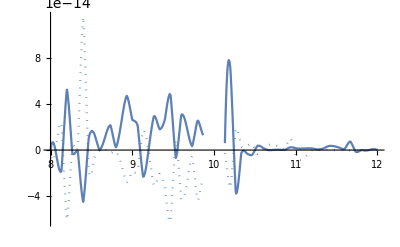

```mathematica
myl = 2;mym=2;
quotientGrid = Table[{rGrid[[i]],TlnTerm[myl,mym][-1/rGrid[[i]]]-ℰxlnPiece[myl,mym][rGrid[[i]]]} ,{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,rmin,rmax},PlotRange->All]
```

## Check --- Reality conditions

We should have that the 4D x_nn and x_(m m̄) are real, while by definition x_(n m̄) = (x_nm)^*.
At the level of the modes, this means for example that x_(n m̄)^lm = (-1)^(m+1)(x_nm^(l-m))^* . This formula also holds for the other tetrad components.

```mathematica
(* NOTE: MAKE SURE THAT VALUE OF M AND r0 AGREE WITH THOSE FOR WHICH THE COEFFICIENTS of the stress energy WERE COMPUTED FOR!!! *)
myrTEST=r0+1;
Max@Abs@Table[N[xmmbNDSolve[myl,mym][myrTEST] -(-1)^mym Conjugate[xmmbNDSolve[myl,-mym][myrTEST]],1],{myl,2,4},{mym,-myl,myl}] (* Checking for Subscript[x, m m̄] *)
Max@Abs@Table[N[xnmbNDSolve[myl,mym][myrTEST] -(-1)^(mym+1) Conjugate[xnmNDSolve[myl,-mym][myrTEST]],1],{myl,2,4},{mym,-myl,myl}]  (* Checking for Subscript[x, nm] *)
Max@Abs@Table[N[xnnNDSolve[myl,mym][myrTEST] -(-1)^mym Conjugate[xnnNDSolve[myl,-mym][myrTEST]],1],{myl,2,4},{mym,-myl,myl}] (* Checking for Subscript[x, nn] *)
```

0.

0.

0.

We also check explicitly that each corrector tensor satisfies x_ab^lm = (-1)^l(x_ab^(l-m))^*. TOgether with the above, we then have x_(n m̄)^lm = (-1)^(l+m+1)x_nm^lm.

```mathematica
myrTEST=r0+1;
Max@Abs@Table[N[xmmbNDSolve[myl,mym][myrTEST] -(-1)^myl Conjugate[xmmbNDSolve[myl,-mym][myrTEST]],1],{myl,2,4},{mym,-myl,myl}] (* Checking for Subscript[x, m m̄] *)
Max@Abs@Table[N[xnmNDSolve[myl,mym][myrTEST] -(-1)^myl Conjugate[xnmNDSolve[myl,-mym][myrTEST]],1],{myl,2,4},{mym,-myl,myl}]  (* Checking for Subscript[x, nm] *)
Max@Abs@Table[N[xnnNDSolve[myl,mym][myrTEST] -(-1)^myl Conjugate[xnnNDSolve[myl,-mym][myrTEST]],1],{myl,2,4},{mym,-myl,myl}] (* Checking for Subscript[x, nn] *)
```

0.

0.

0.

## Check --- large l behaviour

Near particle

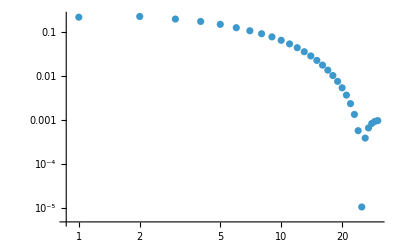

SpinWeightedSphericalHarmonicY::params: Invalid parameters s=1, l=0, m=0

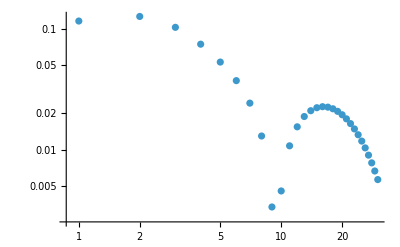

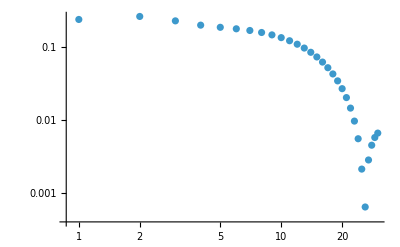

```mathematica
ListLogLogPlot[Abs@Table[{l,Sum[xmmbNDSolve[l,m][r0-1/10000000000000] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
ListLogLogPlot[Abs@Table[{l,Sum[xnmNDSolve[l,m][r0-1/10000000000000] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
ListLogLogPlot[Abs@Table[{l,Sum[xnnNDSolve[l,m][r0-1/10000000000000] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
```

At r_max

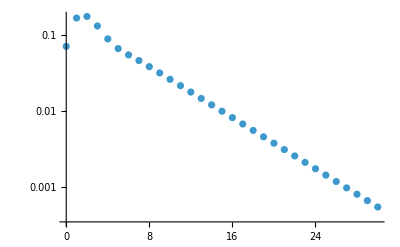

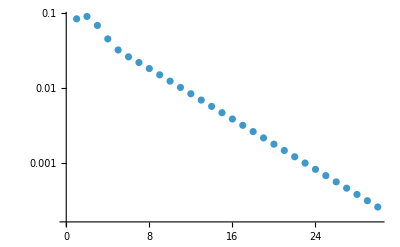

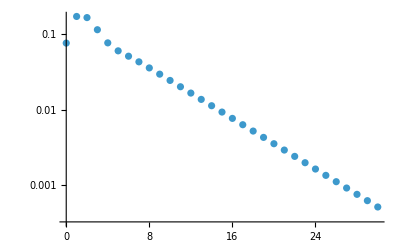

```mathematica
ListLogPlot[Abs@Table[{l,Sum[xmmbNDSolve[l,m][rmax] ExpIωrstar[m][rmax] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
ListLogPlot[Abs@Table[{l,Sum[xnmNDSolve[l,m][rmax] ExpIωrstar[m][rmax] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],{m,-l,l}]},{l,1,lmax}]]
ListLogPlot[Abs@Table[{l,Sum[xnnNDSolve[l,m][rmax] ExpIωrstar[m][rmax] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
```

Near r_min

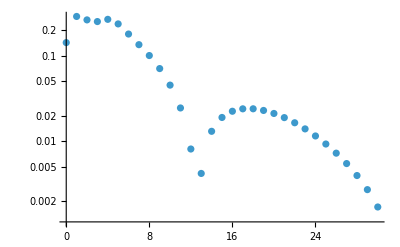

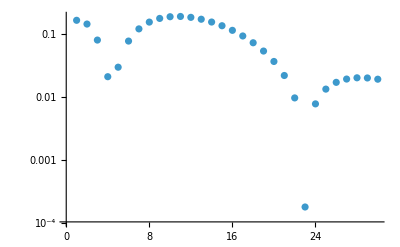

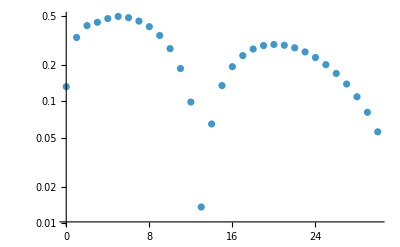

```mathematica
ListLogPlot[Abs@Table[{l,Sum[xmmbNDSolve[l,m][rmin+1/10] ExpIωrstar[m][rmin+1/10] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
ListLogPlot[Abs@Table[{l,Sum[xnmNDSolve[l,m][rmin+1/10] ExpIωrstar[m][rmin+1/10] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],{m,-l,l}]},{l,1,lmax}]]
ListLogPlot[Abs@Table[{l,Sum[xnnNDSolve[l,m][rmin+1/10] ExpIωrstar[m][rmin+1/10] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,0,lmax}]]
```

## (ġ)_ab

## Effective source

### Ṁ using effective source

Ṁ = 1/(8 π) ∫_Σ_t T_ab^R t^a dΣ^b, where dΣ^b = f^-1 r^2 t^b sin θ d θ d ϕ. Can check that: T_tt = f^2/4 T_ll + T_nn + f T_ln. In particular, note T_tt is a spin 0 object and we can write
T_tt = ∑_lm T_tt^lm(r)  _0 Y_lm(θ,ϕ) e^-imΩ_ϕt. We fix t=t_0, and so
Ṁ =1/(8π)∑_lm e^(-imΩ_ϕ t_0)∫dr T_tt^lm(r) f^-1 r^2∫ _0 Y_lm(θ,ϕ) sin θ dθ dϕ = 1/(8π C)∫dr T_tt^00(r) f^-1 r^2, where we used
∫ _0 Y_lm(θ,ϕ) sin θ dθ dϕ = 1/C∫ _0 Y_lm(θ,ϕ) _0 Y_00(θ,ϕ) sin θ dθ dϕ = 1/C δ_l^0 δ_m^0and C is a constant, here equal to _0 Y_00(θ,ϕ) which is a constant.
 T_tt^lm(r) is made up of a smooth bit and a distributional bit.

```mathematica
(* Smooth part *)
1/(8 π SpinWeightedSphericalHarmonicY[0,0,0,θ,ϕ]) NIntegrate[r^2/f[r](f[r]^2/4 TllLeftInterpol[0,0][r] + TnnLeftInterpol[0,0][r] + f[r] TlnLeftInterpol[0,0][r]),{r,r0,rmax}]
1/(8 π SpinWeightedSphericalHarmonicY[0,0,0,θ,ϕ]) NIntegrate[r^2/f[r](f[r]^2/4 TllRightInterpol[0,0][r] + TnnRightInterpol[0,0][r] + f[r] TlnRightInterpol[0,0][r]),{r,rmin,r0}]
MdotIntegralSmoothPart = %+%%
```

-0.122871

0.0700575

-0.0528134

```mathematica
(* General distributional contribution at Subscript[r, min] and Subscript[r, max] *)
MdotIntegral$DeltaContributionAtRmin = 1/(16 √π (-2 M+rmin)^2)(8 M^3 (TllδpRmin-rmin TllδRmin)+4 M^2 rmin (-4 TllδpRmin+3 rmin TllδRmin-8 TlnδpRmin+4 rmin TlnδRmin)+2 M rmin^2 (5 TllδpRmin+4 (4 TlnδpRmin+3 TnnδpRmin)-rmin (3 TllδRmin+8 TlnδRmin+4 TnnδRmin))+rmin^3 (-2 TllδpRmin-8 (TlnδpRmin+TnnδpRmin)+rmin (TllδRmin+4 (TlnδRmin+TnnδRmin))));
MdotIntegral$DeltaContributionAtRmax = 1/(16 √π (-2 M+rmax)^2)(8 M^3 (TllδpRmax-rmax TllδRmax)+4 M^2 rmax (-4 TllδpRmax+3 rmax TllδRmax-8 TlnδpRmax+4 rmax TlnδRmax)+2 M rmax^2 (5 TllδpRmax+4 (4 TlnδpRmax+3 TnnδpRmax)-rmax (3 TllδRmax+8 TlnδRmax+4 TnnδRmax))+rmax^3 (-2 TllδpRmax-8 (TlnδpRmax+TnnδpRmax)+rmax (TllδRmax+4 (TlnδRmax+TnnδRmax))));

(*MdotIntegral$DeltaContributionAtRmin = Assuming[{ϵ>0,rmin>0},1/(8 π SpinWeightedSphericalHarmonicY[0,0,0,θ,ϕ]) Integrate[r^2/f[r](f[r]^2/4 (TllδRmin DiracDelta[r-rmin] + TllδpRmin DiracDelta'[r-rmin]) + (TnnδRmin DiracDelta[r-rmin] + TnnδpRmin DiracDelta'[r-rmin]) + f[r] (TlnδRmin DiracDelta[r-rmin] + TlnδpRmin DiracDelta'[r-rmin])),{r,rmin-ϵ,rmin+ϵ}] // Simplify]
MdotIntegral$DeltaContributionAtRmax = Assuming[{ϵ>0,rmax>0},1/(8 π SpinWeightedSphericalHarmonicY[0,0,0,θ,ϕ]) Integrate[r^2/f[r](f[r]^2/4 (TllδRmax DiracDelta[r-rmax] + TllδpRmax DiracDelta'[r-rmax]) + (TnnδRmax DiracDelta[r-rmax] + TnnδpRmax DiracDelta'[r-rmax]) + f[r] (TlnδRmax DiracDelta[r-rmax] + TlnδpRmax DiracDelta'[r-rmax])),{r,rmax-ϵ,rmax+ϵ}] // Simplify]*)
```

```mathematica
(* Distributional contribution *)
MdotIntegralDistrPart = (MdotIntegral$DeltaContributionAtRmin /.{TllδRmin -> TllδRminInterpol[0,0], TllδpRmin -> TllδpRminInterpol[0,0],TlnδRmin -> TlnδRminInterpol[0,0], TlnδpRmin -> TlnδpRminInterpol[0,0],TnnδRmin -> TnnδRminInterpol[0,0], TnnδpRmin -> TnnδpRminInterpol[0,0]})+(MdotIntegral$DeltaContributionAtRmax /.{TllδRmax -> TllδRmaxInterpol[0,0], TllδpRmax -> TllδpRmaxInterpol[0,0],TlnδRmax -> TlnδRmaxInterpol[0,0], TlnδpRmax -> TlnδpRmaxInterpol[0,0],TnnδRmax -> TnnδRmaxInterpol[0,0], TnnδpRmax -> TnnδpRmaxInterpol[0,0]})
```

0.74883

This agrees with point-particle case only in the limit r_min → r_max → r_0!

```mathematica
(* Relative difference with point-particle source, Subscript[Ṁ, pp] = f u^t. *)
Abs[(MdotIntegralSmoothPart+MdotIntegralDistrPart)/(f[r0] utU)-1]
```

0.272089

### J̇ using effective source

```mathematica
spin1YlmInt = Integrate[SpinWeightedSphericalHarmonicY[1,1,0,θ,ϕ] Sin[θ]^2,{θ,0,π},{ϕ,0,2 π}]; (* Sin[θ]^2 because of Subscript[T, tϕ]~ sin θ (Subscript[T, lm] + Subscript[T, nm]) *)
spinm1YlmInt =Integrate[SpinWeightedSphericalHarmonicY[-1,1,0,θ,ϕ] Sin[θ]^2,{θ,0,π},{ϕ,0,2 π}];
(* Table[Integrate[SpinWeightedSphericalHarmonicY[1,l,m,θ,ϕ] Sin[θ]^2,{θ,0,π},{ϕ,0,2 π}],{l,1,2},{m,-l,l}] *)
```

```mathematica
(* Smooth part *)
-1/(8 π) NIntegrate[r^2/f[r] (r Sqrt[2]/(4 I)) (f[r] (spin1YlmInt TlmLeftInterpol[1,0][r]-spinm1YlmInt TlmbLeftInterpol[1,0][r])+2  (spin1YlmInt TnmLeftInterpol[1,0][r]-spinm1YlmInt TnmbLeftInterpol[1,0][r])),{r,r0,rmax}]
-1/(8 π) NIntegrate[r^2/f[r] (r Sqrt[2]/(4 I)) (f[r] (spin1YlmInt TlmRightInterpol[1,0][r]-spinm1YlmInt TlmbRightInterpol[1,0][r])+2  (spin1YlmInt TnmRightInterpol[1,0][r]-spinm1YlmInt TnmbRightInterpol[1,0][r])),{r,rmin,r0}]
JdotIntegralSmoothPart = %+%%
```

0.358687+0. ⅈ

-0.497155+0. ⅈ

-0.138467+0. ⅈ

```mathematica
(* General distribution contribution *)
JdotIntegral$DeltaContributionAtRmin = -1/(16 √2 π (-2 M+rmin)^2)ⅈ rmin^2 (-4 M^2 (3 sm1 TlmbδpRmin-rmin sm1 TlmbδRmin-3 s1 TlmδpRmin+rmin s1 TlmδRmin)-4 M rmin (sm1 (-3 TlmbδpRmin-4 TnmbδpRmin+rmin (TlmbδRmin+TnmbδRmin))+s1 (3 TlmδpRmin+4 TnmδpRmin-rmin (TlmδRmin+TnmδRmin)))+rmin^2 (sm1 (-3 TlmbδpRmin-6 TnmbδpRmin+rmin (TlmbδRmin+2 TnmbδRmin))+s1 (3 TlmδpRmin+6 TnmδpRmin-rmin (TlmδRmin+2 TnmδRmin))));JdotIntegral$DeltaContributionAtRmax = -1/(16 √2 π (-2 M+rmax)^2)ⅈ rmax^2 (-4 M^2 (3 sm1 TlmbδpRmax-rmax sm1 TlmbδRmax-3 s1 TlmδpRmax+rmax s1 TlmδRmax)-4 M rmax (sm1 (-3 TlmbδpRmax-4 TnmbδpRmax+rmax (TlmbδRmax+TnmbδRmax))+s1 (3 TlmδpRmax+4 TnmδpRmax-rmax (TlmδRmax+TnmδRmax)))+rmax^2 (sm1 (-3 TlmbδpRmax-6 TnmbδpRmax+rmax (TlmbδRmax+2 TnmbδRmax))+s1 (3 TlmδpRmax+6 TnmδpRmax-rmax (TlmδRmax+2 TnmδRmax))));

(* Subscript[T, tϕ] = (r √2 sinθ)/(4 i) {f(Subscript[T, lm]-Subscript[T, l m̄])+2(Subscript[T, nm]-Subscript[T, n m̄])}. *)
(* JdotIntegral$DeltaContributionAtRmin = Assuming[{ϵ>0,rmax>rmin},-1/(8 π)Integrate[r^2/f[r] (r Sqrt[2]/(4 I))(f[r] ((s1 TlmδRmin-sm1 TlmbδRmin) DiracDelta[r-rmin] + (s1 TlmδpRmin-sm1 TlmbδpRmin) DiracDelta'[r-rmin])+2  ((s1 TnmδRmin-sm1 TnmbδRmin) DiracDelta[r-rmin] + (s1 TnmδpRmin-sm1 TnmbδpRmin) DiracDelta'[r-rmin])),{r,rmin-ϵ,rmax}] // Simplify]
JdotIntegral$DeltaContributionAtRmax = Assuming[{ϵ>0,rmax>0},-1/(8 π) Integrate[r^2/f[r] (r Sqrt[2]/(4 I))(f[r] ((s1 TlmδRmax-sm1 TlmbδRmax) DiracDelta[r-rmax] + (s1 TlmδpRmax-sm1 TlmbδpRmax) DiracDelta'[r-rmax])+2  ((s1 TnmδRmax-sm1 TnmbδRmax) DiracDelta[r-rmax] + (s1 TnmδpRmax-sm1 TnmbδpRmax) DiracDelta'[r-rmax])),{r,rmax-ϵ,rmax+ϵ}] // Simplify] *)
```

```mathematica
(* Distribution contribution *)
JdotIntegralDistrPart = (JdotIntegral$DeltaContributionAtRmin /.{
s1 -> spin1YlmInt,
sm1 -> spinm1YlmInt,
TlmδRmin -> TlmδRminInterpol[1,0],
 TlmδpRmin -> TlmδpRminInterpol[1,0],
TlmbδRmin -> TlmbδRminInterpol[1,0],
 TlmbδpRmin -> TlmbδpRminInterpol[1,0],
TnmδRmin -> TnmδRminInterpol[1,0],
 TnmδpRmin -> TnmδpRminInterpol[1,0],
TnmbδRmin -> TnmbδRminInterpol[1,0],
 TnmbδpRmin -> TnmbδpRminInterpol[1,0]})+
(JdotIntegral$DeltaContributionAtRmax /.{
s1 -> spin1YlmInt,
sm1 -> spinm1YlmInt,
TlmδRmax -> TlmδRmaxInterpol[1,0],
 TlmδpRmax -> TlmδpRmaxInterpol[1,0],
TlmbδRmax -> TlmbδRmaxInterpol[1,0],
 TlmbδpRmax -> TlmbδpRmaxInterpol[1,0],
TnmδRmax -> TnmδRmaxInterpol[1,0],
 TnmδpRmax -> TnmδpRmaxInterpol[1,0],
TnmbδRmax -> TnmbδRmaxInterpol[1,0],
 TnmbδpRmax -> TnmbδpRmaxInterpol[1,0]})
```

3.8064+0. ⅈ

This agrees with point-particle case only in the limit r_min → r_max → r_0!

```mathematica
(* Difference with point-particle source, Subscript[J̇, pp] =  Subscript[u, ϕ]. *)
Abs[(JdotIntegralSmoothPart+JdotIntegralDistrPart)/velD[[-1]]-1]
```

0.0295571

## Point-particle

They all vanish except for two quantities (see eq. (73),(74) in reconstruction paper): (ġ)_nn =2/r g_(Ṁ)^o, where g_(Ṁ)^o= Ψ^0(Ṁ)/M = Ṁ = (1-(2M)/r_0)/(√(1-(3M)/r_0)), (assuming Kinnersley tetrad and Ṁ=E=-g_ab u_0^a t^b)
and (ġ)_nm = -2 ρ^2 g_(ȧ)^o, where g_(ȧ)^o=i/(√2)M ȧ sin θ, and ȧ=(J̇)/M in Schwarzschild (see text below (74) and (79)). J̇=L_z=g_ab u_0^a ϕ^b=√((M r_0)/(1-(3 M)/r_0)). (see eq (128) in arXiv:1207.5595.)

```mathematica
Clear[Mdot,Jdot,gDotll,gDotln,gDotlm,gDotlmb,gDotnn,gDotnm,gDotnmb,gDotmm,gDotmmb,gDotmbmb]
(* gdotnn4DExpr = -(ρK + Conjugate[ρK]) Mdot; 
gdotnm4DExpr = -ρK (ρK + Conjugate[ρK])I/Sqrt[2] Jdot Sin[θ];
Simplify[Table[Integrate[gdotnn4DExpr Conjugate[SpinWeightedSphericalHarmonicY[0,l,m,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],{l,0,5},{m,0,l}],{r>0}]
Simplify[Table[Integrate[gdotnm4DExpr Conjugate[SpinWeightedSphericalHarmonicY[1,l,m,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],{l,0,5},{m,0,l}],{r>0}]
Simplify[Table[Integrate[Conjugate[gdotnm4DExpr] Conjugate[SpinWeightedSphericalHarmonicY[-1,l,m,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],{l,0,5},{m,0,l}],{r>0,Jdot>0,Sin[θ]>0}] *)
Mdot = f[r0] utU;
Jdot = r0^2 Ωφ utU;
gDotll[l_,m_][r_] = 0;
gDotln[l_,m_][r_] = 0;
gDotlm[l_,m_][r_] = 0;
gDotlmb[l_,m_][r_] = 0;
gDotnn[l_,m_][r_] = (4 Mdot √π)/r KroneckerDelta[l,m,0] ; 
gDotnm[l_,m_][r_] = -(4 ⅈ Jdot √(π/3))/r^2 KroneckerDelta[l,1] KroneckerDelta[m,0];
gDotnmb[l_,m_][r_] = gDotnm[l,m][r];  (* this is true because only m=0 is non-vanishing. *)
gDotmm[l_,m_][r_] = 0;
gDotmmb[l_,m_][r_] = 0;
gDotmbmb[l_,m_][r_] = 0;
```

## Check --- Compare to known values

Comparing to known value, see arXiv:1207.5595, eqs (137),(138). Note that we modified the formula for H_δM and H_δJ by a factor of 2 since the paper defines redshift as 1/2 h_ab u^a u^b.
Only non-trivial components are the nn, nm, and n m̄ components. Contribution for δM is just the nn component (real), and for δJ, it is nm and n m̄ (purely imaginary)
Starting with δM contribution:

```mathematica
HoldForm[2 (r^2+2 a M^(1/2) r^(1/2)-a^2) (r^(3/2)-2 M r^(1/2)+a M^(1/2))/(r^(9/4) (r^(3/2)-3 M r^(1/2)+2 a M^(1/2))^(3/2))]; (* from the paper *)
HδM =FullSimplify[ReleaseHold[%] /. a -> 0,{r>2 M,r>0}];

mygdotUUδMContribution = Simplify[redshift$Contribution$Formula[0,0,0,0,gdotnn4DExpr,0,0,0,0,0],{r>0,Sin[θ]>0}];
```

```mathematica
Simplify[HδM/mygdotUUδMContribution /. partRule,{r0>0,Sin[θ]>0}]
```

1

δJ contribution:

```mathematica
HoldForm[2 M^(1/2) (r^2-2 a M^(1/2) r^(1/2)+a^2) (a-2 M r^(1/2))/(r^(9/4) (r^(3/2)-3 M r^(1/2)+2 a M^(1/2))^(3/2))]; (* from the paper *)
HδJ =FullSimplify[ReleaseHold[%] /. a -> 0,{r>2 M,r>0}];

mygdotUUδJContribution =Simplify[redshift$Contribution$Formula[0,0,0,0,0,gdotnm4DExpr,Conjugate[gdotnm4DExpr],0,0,0],{r>0,Sin[θ]>0}];
```

```mathematica
Simplify[HδJ/mygdotUUδJContribution /. partRule,r0>3 M]
```

1.

## Check --- ℰ_ab(ġ)=0

```mathematica
ruletmp = {h𝒫ll -> gDotll,h𝒫ln -> gDotln,h𝒫lm -> gDotlm,h𝒫lmb -> gDotlmb,h𝒫nn -> gDotnn,h𝒫nm -> gDotnm,h𝒫nmb -> gDotnmb,h𝒫mm -> gDotmm,h𝒫mmb -> gDotmmb,h𝒫mbmb -> gDotmbmb};
ℰhPWorldtubePiece[0,0][r]/. ruletmp  // Simplify
ℰhPWorldtubePiece[1,0][r]/. ruletmp  // Simplify
Assuming[{l≥2 || m > 0},ℰhPWorldtubePiece[1,0][r]/. ruletmp  // Simplify]
Clear[ruletmp]
```

{0,0,0,0,0,0,0,0,0,0}

{0,(0. ⅈ)/r^4,(0. ⅈ)/r^4,(0. ⅈ)/r^4,(0. ⅈ)/r^5+(0. ⅈ)/r^4,0,0,0,(0. ⅈ)/r^4,0}

{0,(0. ⅈ)/r^4,(0. ⅈ)/r^4,(0. ⅈ)/r^4,(0. ⅈ)/r^5+(0. ⅈ)/r^4,0,0,0,(0. ⅈ)/r^4,0}

## L_Ξ g_ab

## a^o,b^o,c^o

### a^o

Outward integration: In Schwarzschild case, the outward integration formula reduces to H.20 in reconstruction paper.
Note that we added a minus sign to change it into mostly positive convention.
Using the ODE for x_(m m̄) (eq. (56)), we can write a^o = -1/2(-x_(m m̄)(r_max) + (δ and δ' contributions at r_max of T_ll)) +  ρ_max/2(-r_max^2x_(m m̄)'(r_max) + (δ and δ' contributions at r_max of T_ll)).
For the second term, used that ∂_ρ = r^2∂_r. Also, the distributional contributions at r_min are already included in the construction of x_(m m̄).

Inward integration: In Schwarzschild case,
Using the ODE for x_(m m̄) (eq. (56)), we can write a^o = -1/2(-x_(m m̄)(r_min) + (δ and δ' contributions at r_rmin of T_ll)) +  ρ_min/2(-r_min^2x_(m m̄)'(r_min) + (δ and δ' contributions at r_min of T_ll)).
For the second term, used that ∂_ρ = r^2∂_r. Also, the distributional contributions at r_max are already included in the construction of x_(m m̄).

```mathematica
(* for outward integration
(* δ and δ' contributions for the first integral in a^o *)
Assuming[{ϵ>0,rmin>0,r1>0,rmax>rmin}, Integrate[r2^(-2)r1^2 (TllδCoeff[l,m] DiracDelta[r1-rmax]+TllδpCoeff[l,m] DiracDelta'[r1-rmax]),{r2,rmin-ϵ,rmax+ϵ},{r1,rmin-ϵ,r2}]] /. ϵ -> 0 // Simplify 

(* δ and δ' contributions for the second integral in a^o *)
Assuming[{ϵ>0,rmin>0,r1>0,rmax>rmin},  Integrate[r2^2 (TllδCoeff[l,m] DiracDelta[r2-rmax]+TllδpCoeff[l,m] DiracDelta'[r2-rmax]),{r2,rmin-ϵ,rmax+ϵ}]]  /. ϵ -> 0 // Simplify

for inward integration:

*)
```

```mathematica
Assuming[{ϵ>0,rmin>0,r1>0,rmax>rmin}, Integrate[r2^(-2)r1^2 (TllδCoeff[l,m] DiracDelta[r1-rmin]+TllδpCoeff[l,m] DiracDelta'[r1-rmin]),{r2,rmax+ϵ,rmin-ϵ},{r1,rmax+ϵ,r2}]] /. ϵ -> 0 // Simplify 

(* δ and δ' contributions for the second integral in a^o *)
Assuming[{ϵ>0,rmin>0,r1>0,rmax>rmin},  Integrate[r2^2 (TllδCoeff[l,m] DiracDelta[r2-rmin]+TllδpCoeff[l,m] DiracDelta'[r2-rmin]),{r2,rmax+ϵ,rmin-ϵ}]]  /. ϵ -> 0 // Simplify
```

-TllδpCoeff[l,m]

16 (-4 TllδCoeff[l,m]+TllδpCoeff[l,m])

```mathematica
(*Clear[aCircδAndδpContributionAtRmax1stPiece,aCircδAndδpContributionAtRmax2ndPiece]
aCircδAndδpContributionAtRmax1stPiece[l_,m_] = TllδpCoeff[l,m] /.  TllδpCoeff[l_,m_] -> TllδpRmaxInterpol[l,m];
aCircδAndδpContributionAtRmax2ndPiece[l_,m_] =  rmax (rmax TllδCoeff[l,m]-2 TllδpCoeff[l,m]) /.  TllδCoeff[l_,m_] -> TllδRmaxInterpol[l,m] /.  TllδpCoeff[l_,m_] -> TllδpRmaxInterpol[l,m];*)
```

```mathematica
Clear[aCircδAndδpContributionAtRmin1stPiece,aCircδAndδpContributionAtRmin2ndPiece]
aCircδAndδpContributionAtRmin1stPiece[l_,m_] = TllδpCoeff[l,m] /.  TllδpCoeff[l_,m_] -> TllδpRminInterpol[l,m];
aCircδAndδpContributionAtRmin2ndPiece[l_,m_] =  rmin (rmin TllδCoeff[l,m]-2 TllδpCoeff[l,m]) /.  TllδCoeff[l_,m_] -> TllδRminInterpol[l,m] /.  TllδpCoeff[l_,m_] -> TllδpRminInterpol[l,m];
```

```mathematica
aCirc00 = -1/2 (xmmbNDSolve[0,0][rmin]+aCircδAndδpContributionAtRmin1stPiece[0,0])+ρmin/2(-rmin^2 xmmbNDSolve[0,0]'[rmin]+aCircδAndδpContributionAtRmin2ndPiece[0,0])
```

0.477449

### b^o

We simply have that b^0 = -1/2(r_min^2 x_(m m̄)'(r_min) + (δ and δ' contributions at r_min)). This is proportional to the second term in expression for a^o.
We find that this contribution identically vanishes, because the l=1,m=0 component of T_ll is zero.

```mathematica
(*bCirc10 = -1/2(-rmax^2 xmmbNDSolve[1,0]'[rmax]+aCircδAndδpContributionAtRmax2ndPiece[1,0])*)
```

```mathematica
bCirc10 = -1/2(rmin^2 xmmbNDSolve[1,0]'[rmin]+aCircδAndδpContributionAtRmin2ndPiece[1,0])
```

0.+0. ⅈ

### c^o

Outward integration: Similarly to a^0, we can write c^o = +ρ_max^2/3 ð̃ b^o +2/3(-1/2 ρ^4∂_ρ (x_nm/ρ^2)|_(r=r_max) + (δ and δ' contributions at r_max of T_lm and 𝒩x_(m m̄))).


Outward integration:  c^o = +ρ_min^2/3(ð̃ b^o)^- +2/3(-1/2 ρ^4∂_ρ (x_nm/ρ^2)|_(r=r_min) + (δ and δ' contributions at r_min of T_lm and 𝒩x_(m m̄))).
Note: Concerning the distributional contributions, 𝒩x_(m m̄) will actually not contribute, because its coefficient linearly depends on T_ll, which vanishes for l=1, m=0.

```mathematica
(*
(* δ and δ' contributions in c^o *)
Assuming[{ϵ>0,rmin>0,r1>0,rmax>rmin},  -Integrate[TlmAnd𝒩xmmbδCoeff[l,m] DiracDelta[r2-rmax]+TlmAnd𝒩xmmbδpCoeff[l,m] DiracDelta'[r2-rmax],{r2,rmin-ϵ,rmax+ϵ}] // Simplify]
*)
```

```mathematica
Clear[cCircδAndδpContributionAtRmax,𝒩xmmbδCoeffAtRmax]
𝒩xmmbδCoeffAtRmax[l_,m_] = -1/2 r ðCK[0,l][xmmbNDSolve[l,m][rmax]]; (* can check this vanishes for l=1 and m=0 *)
cCircδAndδpContributionAtRmax[l_,m_] = TlmAnd𝒩xmmbδCoeff[l,m]  /.  TlmAnd𝒩xmmbδCoeff[l_,m_] -> TlmδRmaxInterpol[l,m]+𝒩xmmbδCoeffAtRmax[l,m];
```

```mathematica
Clear[cCircδAndδpContributionAtRmin,𝒩xmmbδCoeffAtRmin]
𝒩xmmbδCoeffAtRmin[l_,m_] = -1/2 rmin ðCK[0,l][xmmbNDSolve[l,m][rmin]] (* can check this vanishes for l=1 and m=0 *)
cCircδAndδpContributionAtRmin[l_,m_] = TlmAnd𝒩xmmbδCoeff[l,m]  /.  TlmAnd𝒩xmmbδCoeff[l_,m_] -> TlmδRminInterpol[l,m]+𝒩xmmbδCoeffAtRmin[l,m];
```

(2 √2 √(l (1+l)) xmmbNDSolveLeft[l,m][-1/8])/r

```mathematica
cCirc10 = ρmin^2/3(ρmin ðCK[0,l][bCirc10])+ 1/3 (-xnmNDSolve[1,0]'[rmin]-2 ρmin xnmNDSolve[1,0][rmin]+2 cCircδAndδpContributionAtRmin[1,0])
```

0.+0.02517 ⅈ

```mathematica
𝒩xmmbδCoeffAtRmin[1,0]==0
```

True

## Ξ^a

Note that the values of α and β were once computed using power-series expanded expressions of the puncture.
In this case, we actually found that only the Δr^0 and Δr^1 contribute, and value is independent on r_min and r_max.
Ξ^a should be independent of convention.

```mathematica
Clear[αConst,βConst]
```

```mathematica
αConst = Sqrt[1/(4 π)] aCirc00 (* eq (103) *)
βConst =-I Sqrt[3/(4 π)] cCirc10
ΞVec = -u{αConst,0,0,βConst}; (* eq (98) *)
```

-0.119523

-0.00755929+0. ⅈ

## Check --- point-particle source

Not evaluable.

### Theory

See arXiv:1503.02414, below eq. (25). Compare also (31)-(32) with (24)-(25).
There is a typo and it should read: ξ^μ= μ t ((Ε̂)/(r_0 f_0) t^μ + (2 L_z)/r_0^3 ϕ^μ) Θ(r_0-r), where μ is particle mass, and Ê =(1-(2M)/r_0)/(√(1-(3M)/r_0)), L_z =√(Mr_0/(1-(3M)/r_0))

First, can check this by computing a^o, b^o and c^o for a point particle-source: reconstruction paper, H.20. Note that the final answer should not depend on r_min and r_max! Also, need to add a minus sign in definition of a^o, b^o and c^o to change to mostly positive signature.
Use that: T_ab = f_ab δ(r-r_0) δ^2(Ω-Ω_0), where f_ab := 8π(u_a u_b)/(r_0^2 u^t),  δ^2(Ω-Ω_0)=δ(θ-π/2)δ(ϕ-ωt). (8π is included in the definition of the stress energy in the papers).
		δ(r-r_0)=ρ_0^2 δ(ρ-ρ_0), and from (C.3): δ^2(Ω-Ω_0)=(∑_(l,m))_s((Ȳ)_lm(π/2,ωt))_s Y_lm(θ,ϕ).
		
First term for a^o gives -f_ll/(2 ρ_0^2)δ^2(Ω-Ω_0) (ρ_max-ρ_0).  (Do take care that integrating δ(ρ_1-ρ_0) will give you Heaviside functions H(ρ_2-ρ_0)). E.g.:  ∫_ρ_min^ρ_2 dρ_1 ρ_1^-4δ(r_1-r_0)=  ρ_0^-2 H(ρ_2-ρ_0) .
Second term gives: f_ll/(2 ρ_0^2)δ^2(Ω-Ω_0) ρ_max.
Adding both terms together, the ρ_max cancel and we get:
		a^o=f_ll/(2 ρ_0)δ^2(Ω-Ω_0).
	->    a_lm^o=f_ll/(2 ρ_0)  (Ȳ)_lm(π/2,ωt). (s=0).
	
b^o is just proportional to the second term of a^o:
		b^o=-f_ll/(2 ρ_0^2)δ^2(Ω-Ω_0).
	->    b_lm^o=-f_ll/(2 ρ_0^2)  (Ȳ)_lm(π/2,ωt). (s=0).
	
For c^o, first note that ð δ^2(Ω-Ω_0) =ρ √((l(l+1))/2) ∑_(l,m) ((Ȳ)_lm(π/2,ωt))_1 Y_lm(θ,ϕ). (we only really care about the case s=0 here). Note that we suppress spin if s=0.
First term of c^o is: -ρ_max^2 f_ll/(2 ρ_0^2)ð̃ δ^2(Ω-Ω_0), where ð̃=1/ρ ð is independent of ρ.
Second term is:  -2 f_lm δ^2(Ω-Ω_0).
Concerning x_(m m̄), similar calculations show that x_(m m̄)= -f_ll/ρ_0^2δ^2(Ω-Ω_0) H(ρ-ρ_0).
Then: 𝒩x_(m m̄) = -f_ll/(2 ρ_0^2)ð̃ δ^2(Ω-Ω_0) ρ^3 (H(ρ-ρ_0) + (ρ-ρ_0) δ(ρ-ρ_0)). The second term can be dropped because the coefficient vanishes at the particle.
So, third term of c^o is: f_ll/ρ_0^2 ð̃ δ^2(Ω-Ω_0) (ρ_max^2-ρ_0^2)/2.
Adding everything up, again find that the first term (~ρ_max^2) cancels with the corresponding expression in the third term.
		c^o = 1/3 (2 f_lm δ^2(Ω-Ω_0) + f_ll/2 ð̃ δ^2(Ω-Ω_0)).
		c_lm^o = 1/3 (2 f_lm_1(Ȳ)_lm(π/2,ωt) + f_ll/2 √((l(l+1))/2)f_lm(Ȳ)_lm(π/2,ωt)).
		
So, 	<a_lm^o> = f_ll/(2 ρ_0)(Ȳ)_lm(π/2,0), 	(the averaging basically sets t=0 by periodicity).
	<b_lm^o> =-f_ll/(2 ρ_0^2)(Ȳ)_lm(π/2,0),
	<c_lm^o> = 1/3 (2 f_lm_1(Ȳ)_lm(π/2,0) + f_ll/2 √((l(l+1))/2)f_lm(Ȳ)_lm(π/2,0)).
Now, computing α and β constants of Ξ, note that (Ȳ)_10(π/2,0)=0 and so the b^o contribution vanishes, as well as second term in c^o.
	<a_00^o> = f_ll/(4 ρ_0 √π),
	<b_10^o> = 0,
	<c_10^o> = f_lm/(√(6π)).
⇒  α=-1/(r_0 √(1-(3 M)/r_0)), 	β =-(2 Ω_ϕ)/(r_0 √(1-(3 M)/r_0)).

### Comparison

```mathematica
fll = 8 π ul^2/(r0^2 utU) // Simplify;
flm = 8 π ul um/(r0^2 utU) // Simplify;
αpp = -fll r0/(8 π) // Simplify;
βpp = -I flm/(2 Sqrt[2] π) // Simplify;
```

```mathematica
energy = (1-2 M/r0)/Sqrt[1-3 M/r0];
Lzmomentum = Sqrt[M r0/(1-3 M/r0)];

αAbhay=energy/(r0 f[r0]);
βAbhay=2 Lzmomentum/(r0^3);
```

Comparing my calculations with the arXiv paper (arXiv:1503.02414).

```mathematica
αAbhay / αpp 
βAbhay/ βpp /. Ωφ->Sqrt[M/r0^3] // Simplify[#,Assumptions->{r0 > 3 M > 0}] &
```

-1

-1.

Comparing now to our computation using the residual stress-energy.
Note: Checked that this holds, when using a power-series expansion of the puncture (and therefore of the stress energy); see Archive section. Found agreement to be independent of r_min and r_max.

```mathematica
αpp / αConst
βpp/βConst
```

1.

1.+0. ⅈ

## L_Ξ g_ab 4D

Not evaluable.

The Lie derivative in the direction of Ξ of a rank (0,2) tensor is:   ℒ_Ξ g_ab = Ξ^c∂_c g_ab + g_cb ∂_a Ξ^c + g_ac ∂_b Ξ^c.

```mathematica
ℒΞgab := Table[
Sum[ΞVec[[c]] D[gmetNullDD[[a,b]],ccNull[[c]]],{c,1,ndim}]+
Sum[gmetNullDD[[c,b]] D[ΞVec[[c]],ccNull[[a]]],{c,1,ndim}]+
Sum[gmetNullDD[[a,c]] D[ΞVec[[c]],ccNull[[b]]],{c,1,ndim}],
{a,1,ndim},{b,1,ndim}]
```

```mathematica
Clear[ℒΞgll,ℒΞgln,ℒΞglm,ℒΞglmb,ℒΞgnn,ℒΞgnm,ℒΞgnmb,ℒΞgmm,ℒΞgmmb,ℒΞgmbmb]
ℒΞgll[rVal_] = lNullKU.ℒΞgab.lNullKU /. r -> rVal // Simplify
ℒΞgln[rVal_] = lNullKU.ℒΞgab.nNullKU /. r -> rVal // Simplify
ℒΞglm[rVal_] = lNullKU.ℒΞgab.mNullKU /. r -> rVal // Simplify
ℒΞglmb[rVal_] = lNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
ℒΞgnn[rVal_]= nNullKU.ℒΞgab.nNullKU /. r -> rVal // Simplify
ℒΞgnm[rVal_] = nNullKU.ℒΞgab.mNullKU /. r -> rVal // Simplify
ℒΞgnmb[rVal_] = nNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
ℒΞgmm[rVal_] = mNullKU.ℒΞgab.mNullKU /. r -> rVal // Simplify
ℒΞgmmb[rVal_] = mNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
ℒΞgmbmb[rVal_] = mbNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
```

0

αConst

0

0

((-2+rVal) αConst)/rVal

-(ⅈ rVal βConst Sin[θ])/(√2)

(ⅈ rVal βConst Sin[θ])/(√2)

0

0

0

## L_Ξ g_ab modes

```mathematica
Clear[ℒΞgll,ℒΞgln,ℒΞglm,ℒΞglmb,ℒΞgnn,ℒΞgnm,ℒΞgnmb,ℒΞgmm,ℒΞgmmb,ℒΞgmbmb]
(* Table[Integrate[ℒΞgln[r] Conjugate[SpinWeightedSphericalHarmonicY[0,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}]
Table[Integrate[ℒΞgnn[r] Conjugate[SpinWeightedSphericalHarmonicY[0,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}]
Table[Integrate[ℒΞgnm[r] Conjugate[SpinWeightedSphericalHarmonicY[1,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}]
Table[Integrate[ℒΞgnmb[r] Conjugate[SpinWeightedSphericalHarmonicY[-1,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}] *)
ℒΞgll[l_,m_][r_] = 0;
ℒΞgln[l_,m_][r_] = If[l==0 && m==0,Sqrt[4 π] αConst,0];
ℒΞglm[l_,m_][r_] = 0;
ℒΞglmb[l_,m_][r_] = 0;
ℒΞgnn[l_,m_][r_] = If[l==0 && m==0,f[r] Sqrt[4 π] αConst,0];
ℒΞgnm[l_,m_][r_] = If[l==1 && m==0,-I r Sqrt[4 π/3] βConst,0]; 
ℒΞgnmb[l_,m_][r_] = If[l==1 && m==0,-I r Sqrt[4 π/3] βConst,0]; 
ℒΞgmm[l_,m_][r_] = 0;
ℒΞgmmb[l_,m_][r_] = 0;
ℒΞgmbmb[l_,m_][r_] = 0;
```

## Check --- ℰ_ab(L_Ξ g_ab)=0

```mathematica
ruletmp = {h𝒫ll -> ℒΞgll,h𝒫ln -> ℒΞgln,h𝒫lm -> ℒΞglm,h𝒫lmb -> ℒΞglmb,h𝒫nn -> ℒΞgnn,h𝒫nm -> ℒΞgnm,h𝒫nmb -> ℒΞgnmb,h𝒫mm -> ℒΞgmm,h𝒫mmb -> ℒΞgmmb,h𝒫mbmb -> ℒΞgmbmb};
ℰhPWorldtubePiece[0,0][r]/. ruletmp  // Simplify
ℰhPWorldtubePiece[1,0][r]/. ruletmp  // Simplify
Assuming[{l≥2 || m > 0},ℰhPWorldtubePiece[1,0][r]/. ruletmp  // Simplify]
```

{0,0.,0,0,0,0,0,0,0.,0}

{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0,0.+0. ⅈ,0}

{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.,0,0.+0. ⅈ,0}

## ψ_0

## ψ_0^ret

```mathematica
Weylspin=2;
weylspin=Weylspin;
(* For lmax=40 and wp=64, it takes about 2x1.8 hour *)
```

### Theory

The Teukolsky equation (in BL coordinates) is given by: (see, e.g. (84) in review paper): {Δ^-s d/dr(Δ^(s+1)d/dr)+(K^2-2is(r-M)K)/Δ+4isωr-λ} ψ_lm = S^ab T_ab.
where K:=(r^2+a^2)ω-a m, Δ:=r^2-2 M r+a^2. In Schwarzschild, λ=l(l+1)-s(s+1).

We first use the Teukolsky toolkit to solve for the two homogeneous solutions with ingoing/outgoing boundary conditions at the black-hole horizon/null infinity, called the “in” and “up” solutions. Then, we compute the inhomogeneous solution via variation of parameters method. Because RHS is only made up of δ-functions (and their first and second derivatives), can find an analytical expression of the inhomogeneous solution in terms of homogeneous solutions.
Look at section 4.1.7 in review paper for more details.

### Import the homogeneous solutions

```mathematica
nonNegModes=Flatten[Table[{l,m},{l,Abs[Weylspin],lmax},{m,0,l}],1];
modeDir$p2=FileNameJoin[{NotebookDirectory[],"RadialModeCache_sPlus2"}];
modeDir$m2=FileNameJoin[{NotebookDirectory[],"RadialModeCache_sMinus2"}];
```

```mathematica
ClearAll[loadRadialModeCache];

loadRadialModeCache[cacheDir_String,spin_Integer,modeList_List]:=Module[{ell,mm,file,sol},Do[{ell,mm}=mode;
file=FileNameJoin[{cacheDir,StringTemplate["s``_l``_m``.wxf"][spin,ell,mm]}];
If[!FileExistsQ[file],Print["Missing file: ",file];
Continue[];];
sol=Import[file,"WXF"];
If[!AssociationQ[sol]||!KeyExistsQ[sol,"In"]||!KeyExistsQ[sol,"Up"],Print["Invalid cache file: ",file];
Continue[];];
With[{inFun=sol["In"],upFun=sol["Up"]},ψHomogInUp[spin][ell,mm]["In"]=inFun;
ψHomogInUp[spin][ell,mm]["Up"]=upFun;],{mode,modeList}];];
```

```mathematica
loadRadialModeCache[modeDir$p2,Weylspin,nonNegModes];
loadRadialModeCache[modeDir$m2,-Weylspin,nonNegModes];
```

### Compute homogeneous solutions

```mathematica
(* homogeneous solutions are given in (t,r,θ,ϕ) coordinates *)
```

```mathematica
(*Clear[ψHomogInUp]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/TeukScalars/RadialModePsiCache/SchwarzschildCircular_PsiTeuk_s2_lmax40_rOutbd1212.mx"]*)
```

```mathematica
Clear[ψHomogInUpFunc]
ψHomogInUpFunc[Weylspin][l_,m_]:=
TeukolskyRadial[
Weylspin,l,m,aKerr,ωm[m],
Method->{
"NumericalIntegration",
"Domain"->{"In"->{rNumInbd,r0},"Up"->{r0,rNumOutbd}}
}
];

ψHomogInUpFunc[-Weylspin][l_,m_]:=
TeukolskyRadial[
-Weylspin,l,m,aKerr,ωm[m],
Method->{"NumericalIntegration",
"Domain"->{"In"->{rNumInbd,r0},"Up"->{r0,rNumOutbd}}}
];
```

```mathematica
SetSharedVariable[Weylspin,aKerr,rNumInbd,rNumOutbd];
```

```mathematica
Clear[ψHomogInUp]
Monitor[
ParallelDo[
ψHomogInUp[Weylspin][l,m]=ψHomogInUpFunc[Weylspin][l,m];
ψHomogInUp[Weylspin][l,-m]["In"][r_]=Conjugate[ψHomogInUp[Weylspin][l,m]["In"][r]];
ψHomogInUp[Weylspin][l,-m]["Up"][r_]=Conjugate[ψHomogInUp[Weylspin][l,m]["Up"][r]];,
{l,Abs[Weylspin],lmax},{m,1,l}],{l,m}]; // Timing

Monitor[
ParallelDo[
ψHomogInUp[Weylspin][l,0]=TeukolskyRadial[Weylspin,l,0,aKerr,0(*m Ωφ*)];,
{l,Abs[Weylspin],lmax}],{l}]
```

```mathematica
(* s=-2, needed for the Hertz potential *)
Monitor[
ParallelDo[
ψHomogInUp[-Weylspin][l,m]=ψHomogInUpFunc[-Weylspin][l,m];
ψHomogInUp[-Weylspin][l,-m]["In"][r_]=Conjugate[ψHomogInUp[-Weylspin][l,m]["In"][r]];
ψHomogInUp[-Weylspin][l,-m]["Up"][r_]=Conjugate[ψHomogInUp[-Weylspin][l,m]["Up"][r]];,
{l,Abs[Weylspin],lmax},{m,1,l}],{l,m}]; // Timing

Monitor[
ParallelDo[
ψHomogInUp[-Weylspin][l,0]=
TeukolskyRadial[-Weylspin,l,0,aKerr,0(*m Ωφ*)];,
{l,Abs[Weylspin],lmax}],{l}]
```

```mathematica
{ψHomogInUp[Weylspin][20,1]["In"][9.],ψHomogInUp[Weylspin][2,-1]["In"][8.],ψHomogInUp[Weylspin][2,1]["Up"][11.],ψHomogInUp[Weylspin][2,-1]["Up"][11.]}
```

{ψHomogInUp[2][20,1][In][9.],-1.55819+5.54156 ⅈ,7.80773×10^-6+5.06634×10^-6 ⅈ,7.80773×10^-6-5.06634×10^-6 ⅈ}

### Parallel sequence jobs run

```mathematica
AbortKernels[];
CloseKernels[];
LaunchKernels[];
```

```mathematica
lmaxHomog=30;
sHomog=Weylspin;
```

```mathematica
ClearAll[jobs,lm,l,m,sol];

DistributeDefinitions[TeukolskyRadial,sHomog,aKerr,ωm,rNumInbd,rNumOutbd,r0];
```

```mathematica
ClearAll[makePortableBranch];

Options[makePortableBranch]={"Points"->400,InterpolationOrder->5, WorkingPrecision->WP};

makePortableBranch[sol_,branch_String,{rmin_?NumericQ,rmax_?NumericQ},OptionsPattern[]]:=Module[{grid,vals},grid=Subdivide[N[rmin,WP],N[rmax,WP],OptionValue["Points"]-1];
vals=sol[branch]/@grid;
If[!VectorQ[vals,NumericQ],Return[Failure["NonNumericValues",
<|"Branch"->branch,
"BadPositions"->Flatten@Position[vals,x_/;!NumericQ[x]]|>]]];
Interpolation[Transpose[{grid,vals}],
InterpolationOrder->OptionValue[InterpolationOrder]]
];
```

```mathematica
ss=ψHomogInUpFunc[Weylspin][3,2];
Clear[portableTest]
portableTest=<|"In"->makePortableBranch[ss,"In",{rNumInbd,r0},"Points"->500],"Up"->makePortableBranch[ss,"Up",{r0,rNumOutbd},"Points"->1000]|>;

portableTest["In"][9.]
portableTest["Up"][12.]
```

-32.0314-100.654 ⅈ

-0.0000186576+0.0000141681 ⅈ

```mathematica
testFile=FileNameJoin[{modeDir,"portable-test.wxf"}];
Export[testFile,portableTest,"WXF"];
testImported=Import[testFile,"WXF"];

{portableTest["In"][9.],testImported["In"][9.],portableTest["Up"][12.],testImported["Up"][12.]}
Clear[ss,portableTest,testFile]
```

{-32.0314-100.654 ⅈ,-32.0314-100.654 ⅈ,-0.0000186576+0.0000141681 ⅈ,-0.0000186576+0.0000141681 ⅈ}

```mathematica
(*If needed,load the Teukolsky package on all subkernels too. 
Use whatever Needs[...] you used in the main kernel.*)
(*ParallelEvaluate[Needs["Teukolsky`"]];*)
```

```mathematica
ParallelNeeds["Teukolsky`"];
DistributeDefinitions[makePortableBranch];
```

```mathematica
ParallelEvaluate[$HistoryLength=0];
```

#### s = +2 jobs

```mathematica
positiveModeJobs=Flatten[Table[{l,m},{l,Abs[sHomog],lmaxHomog},{m,1,l}],1];
```

```mathematica
(*Create cache directory*)
modeDir=FileNameJoin[{NotebookDirectory[],"RadialModeCache"}];
If[!DirectoryQ[modeDir],CreateDirectory[modeDir]];
```

```mathematica
ClearAll[jobs,results,remaining,completed,total,lastMode,failed];
DistributeDefinitions[makePortableBranch];

jobs=Map[Function[mode,With[{ell=mode[[1]],mm=mode[[2]],spin0=sHomog,a0=aKerr,omega0=ωm[mode[[2]]],rin=rNumInbd,rp=r0,rout=rNumOutbd},ParallelSubmit[
Module[
{solLocal,portableSol},
solLocal=TeukolskyRadial[spin0,ell,mm,a0,omega0,
Method->{"NumericalIntegration","Domain"->{"In"->{rin,rp},"Up"->{rp,rout}}}];
portableSol=
<|"In"->makePortableBranch[solLocal,"In",{rin,rp},"Points"->500],"Up"->makePortableBranch[solLocal,"Up",{rp,rout},"Points"->1500]|>;
{ell,mm,portableSol}]]]],positiveModeJobs];

results=<||>;
remaining=jobs;
completed=0;
total=Length[jobs];
lastMode=None;
failed={};
```

```mathematica
Monitor[
While[
remaining=!={},(*WaitNext returns:{result,finished evaluation object,new remaining list}*){res,finishedJob,remaining}=WaitNext[remaining];
If[MatchQ[res,{_Integer,_Integer,_}],
Module[{l,m,sol,file},
{l,m,sol}=res;
lastMode={l,m};
file=FileNameJoin[{modeDir,StringTemplate["s``_l``_m``.wxf"][sHomog,l,m]}];
Export[file,sol,"WXF"];
AssociateTo[results,{l,m}->file];],AppendTo[failed,res]];
completed++;],Column[{Style["Positive s=+2 modes",14,Bold],Row[{"Completed: ",Dynamic[completed]," / ",total}],Row[{"Remaining: ",Dynamic[Length[remaining]]}],Row[{"Last finished: ",Dynamic[lastMode]}],ProgressIndicator[Dynamic[completed],{0,total},ImageSize->300]}]];
```

```mathematica
(*
 do m=0 s=2 jobs 
*)
ClearAll[mzerojobsp2,zeroModeJobsp2,results,remaining,completed,total,lastMode,failed];

zeroModeJobsp2=Table[{ell,0},{ell,2,lmaxHomog}];

mzerojobsp2=
Map[
Function[mode,
With[
{
ell=mode[[1]],emm=0,spin0=sHomog,a0=aKerr,omega0=ωm[0],
rin=rNumInbd,rp=r0,rout=rNumOutbd
},ParallelSubmit[
Module[
{solLocal,portableSol},
solLocal=TeukolskyRadial[spin0,ell,emm,a0,omega0];
portableSol=
<|"In"->makePortableBranch[solLocal,"In",{rin,rp},"Points"->500],"Up"->makePortableBranch[solLocal,"Up",{rp,rout},"Points"->1500]|>;
{ell,emm,portableSol}]]]],zeroModeJobsp2];
results=<||>;
remaining=mzerojobsp2;
completed=0;
total=Length[mzerojobsp2];
lastMode=None;
failed={};
```

```mathematica
Monitor[
While[
remaining=!={},(*WaitNext returns:{result,finished evaluation object,new remaining list}*){res,finishedJob,remaining}=WaitNext[remaining];
If[MatchQ[res,{_Integer,_Integer,_}],
Module[{l,m,sol,file},
{l,m,sol}=res;
lastMode={l,m};
file=FileNameJoin[{modeDir,StringTemplate["s``_l``_m``.wxf"][sHomog,l,m]}];
Export[file,sol,"WXF"];
AssociateTo[results,{l,m}->file];],AppendTo[failed,res]];
completed++;],Column[{Style["Positive s=+2 modes",14,Bold],Row[{"Completed: ",Dynamic[completed]," / ",total}],Row[{"Remaining: ",Dynamic[Length[remaining]]}],Row[{"Last finished: ",Dynamic[lastMode]}],ProgressIndicator[Dynamic[completed],{0,total},ImageSize->300]}]];
```

```mathematica
modeDir
```

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/RadialModeCache

```mathematica
Clear[mzerojobs,zeroModeResultsp2,positiveModeResults]
```

#### s = -2 jobs

```mathematica
sHomogMinus=-Weylspin;

negativeSpinModeDir=FileNameJoin[{NotebookDirectory[],"RadialModeCache_sMinus2"}];

If[!DirectoryQ[negativeSpinModeDir],CreateDirectory[negativeSpinModeDir,CreateIntermediateDirectories->True]];
```

```mathematica
negativeModeJobs=positiveModeJobs;
```

```mathematica
jobsMinus=Map[
Function[mode,
With[
{ell=mode[[1]],mm=mode[[2]],spin0=sHomogMinus,
a0=aKerr,omega0=ωm[mode[[2]]],rin=rNumInbd,rp=r0,rout=rNumOutbd},
ParallelSubmit[
Module[{solLocal,portableSol},
solLocal=
TeukolskyRadial[
spin0,ell,mm,a0,omega0,
Method->{"NumericalIntegration",
"Domain"->{"In"->{rin,rp},"Up"->{rp,rout}}
}
];
portableSol=
<|"In"->makePortableBranch[solLocal,"In",{rin,rp},"Points"->500],
"Up"->makePortableBranch[solLocal,"Up",{rp,rout},"Points"->1500]
|>;
{ell,mm,portableSol}]
]
]
],positiveModeJobs];
```

```mathematica
resultsMinus=<||>;
remainingMinus=jobsMinus;
completedMinus=0;
totalMinus=Length[jobsMinus];
lastModeMinus=None;
failedMinus={};

Monitor[
While[remainingMinus=!={},
{res,finishedJob,remainingMinus}=WaitNext[remainingMinus];
If[MatchQ[res,{_Integer,_Integer,_Association}],
Module[{ell,mm,sol,file},
{ell,mm,sol}=res;
lastModeMinus={ell,mm};
file=FileNameJoin[{negativeSpinModeDir,StringTemplate["s-2_l``_m``.wxf"][ell,mm]}];
Export[file,sol,"WXF"];
AssociateTo[resultsMinus,{ell,mm}->file];],AppendTo[failedMinus,res]];
completedMinus++;],Column[{Style["s = -2 modes",14,Bold],Row[{"Completed: ",Dynamic[completedMinus]," / ",totalMinus}],Row[{"Remaining: ",Dynamic[Length[remainingMinus]]}],Row[{"Last finished: ",Dynamic[lastModeMinus]}],ProgressIndicator[Dynamic[completedMinus],{0,totalMinus},ImageSize->300]}]];
```

```mathematica
(*
 do m=0 s=-2 jobs 
*)
ClearAll[mzerojobsm2,zeroModeJobsm2,results,remaining,completed,total,lastMode,failed];

zeroModeJobsm2=Table[{ell,0},{ell,2,lmaxHomog}];

mzerojobsm2=
Map[
Function[mode,
With[
{
ell=mode[[1]],emm=0,spin0=sHomogMinus,a0=aKerr,omega0=ωm[0],
rin=rNumInbd,rp=r0,rout=rNumOutbd
},ParallelSubmit[
Module[
{solLocal,portableSol},
solLocal=TeukolskyRadial[spin0,ell,emm,a0,omega0];
portableSol=
<|"In"->makePortableBranch[solLocal,"In",{rin,rp},"Points"->500],"Up"->makePortableBranch[solLocal,"Up",{rp,rout},"Points"->1500]|>;
{ell,emm,portableSol}]]]],zeroModeJobsm2];
results=<||>;
remaining=mzerojobsm2;
completed=0;
total=Length[mzerojobsm2];
lastMode=None;
failed={};
```

```mathematica
Monitor[
While[
remaining=!={},(*WaitNext returns:{result,finished evaluation object,new remaining list}*){res,finishedJob,remaining}=WaitNext[remaining];
If[MatchQ[res,{_Integer,_Integer,_}],
Module[{l,m,sol,file},
{l,m,sol}=res;
lastMode={l,m};
file=FileNameJoin[{modeDir,StringTemplate["s-2``_l``_m``.wxf"][sHomog,l,m]}];
Export[file,sol,"WXF"];
AssociateTo[results,{l,m}->file];],AppendTo[failed,res]];
completed++;],Column[{Style["Positive s=-2 modes",14,Bold],Row[{"Completed: ",Dynamic[completed]," / ",total}],Row[{"Remaining: ",Dynamic[Length[remaining]]}],Row[{"Last finished: ",Dynamic[lastMode]}],ProgressIndicator[Dynamic[completed],{0,total},ImageSize->300]}]];
```

```mathematica
Clear[positiveModeJobs,negativeModeJobs, zeroModeJobsm2,negativeModeResults ]
```

### Save the solutions

```mathematica
modeDir=FileNameJoin[{NotebookDirectory[],"RadialModeCache"}];

If[!DirectoryQ[modeDir],CreateDirectory[modeDir]];

modeFile=FileNameJoin[{
modeDir,
"SchwarzschildCircular_TeukScalars_homogUp_s"<>ToString[Weylspin]<>"_lmax"<>ToString[lmax]<>"_rOutbd" <> ToString[rNumOutbd]<> ".mx"
}
];

DumpSave[modeFile,ψHomogInUp]
```

$Aborted

### Compute variation of parameters weighting coefficients - Manual calculation

Not evaluable.

For Schwarzschild circular orbits, ω=mΩ_φ and is basically taken into account in TeukolskyPointParticleMode when you tell it e=a=0, and give it the orbit and m.
Currently, the toolkit is not functioning for static modes (m=0), so need to do this manually, using variation-of-parameters approach.
The extra factor of r^2 f(r) attached to the Wronskian is because we follow the conventions in the book chapter instead of the reconstruction paper where the Teukolsky equation is first written in self-adjoint form (eq. (83)-(84)). This is because the modes of ψ_0 and the source term are expanded following the same conventions, see eq (81,82,91,96). See how the source term is constructed in this notebook for more details.
Note that by definition, ψ_0 should be invariant under sign signature.

We used the fact that,  (C^±)_(l-m) = (-1)^l(C_lm^±)^*, which has been checked empirically.

```mathematica
Clear[myWronskian]
Do[
myWronskian[s_,l,m][r_] = ψHomogInUpFn[s,l,m]["In"][r] ψHomogInUpFn[s,l,m]["Up"]'[r]-ψHomogInUpFn[s,l,m]["Up"][r] ψHomogInUpFn[s,l,m]["In"]'[r];,
{l,Abs[Weylspin],lmax},{m,-l,l}]
```

```mathematica
Table[(r^2 f[r])^3 myWronskian[2,2,2][r],{r,rmin,rmax,0.1}]/. partRule /. ψHomogInUpFn -> ψHomogInUp
```

{-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ,-1.94587+10.7332 ⅈ}

```mathematica
(*Clear[Cplus,Cminus]*)
Monitor[Do[Cplus[Weylspin,l,m]=ψHomogInUp[Weylspin,l,m]["In"][r0]/(r0^2 f[r0]myWronskian[Weylspin,l,m][r0]) SabTabδTerm[Weylspin,l,m][r0] - D[ψHomogInUpFn[Weylspin,l,m]["In"][r]/(r^2 f[r] myWronskian[Weylspin,l,m][r]) SabTabδpTerm[Weylspin,l,m][r],r]+ D[ψHomogInUpFn[Weylspin,l,m]["In"][r]/(r^2 f[r]myWronskian[Weylspin,l,m][r]) SabTabδppTerm[Weylspin,l,m][r],{r,2}] 
/. partRule /. ψHomogInUpFn -> ψHomogInUp;
Cminus[Weylspin,l,m]=
ψHomogInUp[Weylspin,l,m]["Up"][r0]/(r0^2 f[r0]myWronskian[Weylspin,l,m][r0]) SabTabδTerm[Weylspin,l,m][r0] - 
D[ψHomogInUpFn[Weylspin,l,m]["Up"][r]/(r^2 f[r]myWronskian[Weylspin,l,m][r]) SabTabδpTerm[Weylspin,l,m][r],r]+ D[ψHomogInUpFn[Weylspin,l,m]["Up"][r]/(r^2 f[r]myWronskian[Weylspin,l,m][r]) SabTabδppTerm[Weylspin,l,m][r],{r,2}] 
/. partRule /. ψHomogInUpFn -> ψHomogInUp;

If[m≠0,Cplus[Weylspin,l,-m] = (-1)^l Conjugate[Cplus[Weylspin,l,m]]];
If[m≠0,Cminus[Weylspin,l,-m] = (-1)^l Conjugate[Cminus[Weylspin,l,m]]]

,
{l,Abs[Weylspin],lmax},{m,0,l}],
{l,m}]

Monitor[Do[Cplus[-Weylspin,l,m]=ψHomogInUp[-Weylspin,l,m]["In"][r0]/(r0^2 f[r0]myWronskian[-Weylspin,l,m][r0]) SabTabδTerm[-Weylspin,l,m][r0] - D[ψHomogInUpFn[-Weylspin,l,m]["In"][r]/(r^2 f[r] myWronskian[-Weylspin,l,m][r]) SabTabδpTerm[-Weylspin,l,m][r],r]+ D[ψHomogInUpFn[-Weylspin,l,m]["In"][r]/(r^2 f[r]myWronskian[-Weylspin,l,m][r]) SabTabδppTerm[-Weylspin,l,m][r],{r,2}] /. partRule /. ψHomogInUpFn -> ψHomogInUp;
Cminus[-Weylspin,l,m]=
ψHomogInUp[-Weylspin,l,m]["Up"][r0]/(r0^2 f[r0]myWronskian[-Weylspin,l,m][r0]) SabTabδTerm[-Weylspin,l,m][r0] - 
D[ψHomogInUpFn[-Weylspin,l,m]["Up"][r]/(r^2 f[r]myWronskian[-Weylspin,l,m][r]) SabTabδpTerm[-Weylspin,l,m][r],r]+ D[ψHomogInUpFn[-Weylspin,l,m]["Up"][r]/(r^2 f[r]myWronskian[-Weylspin,l,m][r]) SabTabδppTerm[-Weylspin,l,m][r],{r,2}] /. partRule /. ψHomogInUpFn -> ψHomogInUp;

If[m≠0,Cplus[-Weylspin,l,-m] = (-1)^l Conjugate[Cplus[-Weylspin,l,m]]];
If[m≠0,Cminus[-Weylspin,l,-m] = (-1)^l Conjugate[Cminus[-Weylspin,l,m]]]

,
{l,Abs[Weylspin],lmax},{m,0,l}],
{l,m}]
```

### Compute variation of parameters weighting coefficients

For Schwarzschild circular orbits, ω=mΩ_φ and is basically taken into account in TeukolskyPointParticleMode when you tell it e=a=0, and give it the orbit and m. We used the fact that,  (A^±)_(l-m) = (-1)^l(A_lm^±)^*, which has been checked empirically.

```mathematica
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/TeukScalars/RadialModePsiCache/SchwarzschildCircular_CplusMinus_s2_lmax40.mx"]
```

```mathematica
Clear[Cplus,Cminus]
```

```mathematica
Clear[Cplus,Cminus]
Monitor[Do[
Cplus[Weylspin,l,m]= TeukolskyPointParticleMode[Weylspin,l,m,0,0,orbit]["Amplitudes"]["ℐ"];
Cminus[Weylspin,l,m]= TeukolskyPointParticleMode[Weylspin,l,m,0,0,orbit]["Amplitudes"]["ℋ"];
If[m≠0,Cplus[Weylspin,l,-m] = (-1)^l Conjugate[Cplus[Weylspin,l,m]]];
If[m≠0,Cminus[Weylspin,l,-m] = (-1)^l Conjugate[Cminus[Weylspin,l,m]]]
,{l,Abs[Weylspin],lmax},{m,0,l}],
{Cplus,Weylspin,l,m}]

Monitor[Do[
Cplus[-Weylspin,l,m]= TeukolskyPointParticleMode[-Weylspin,l,m,0,0,orbit]["Amplitudes"]["ℐ"];
Cminus[-Weylspin,l,m]= TeukolskyPointParticleMode[-Weylspin,l,m,0,0,orbit]["Amplitudes"]["ℋ"];
If[m≠0,Cplus[-Weylspin,l,-m] = (-1)^l Conjugate[Cplus[-Weylspin,l,m]]];
If[m≠0,Cminus[-Weylspin,l,-m] = (-1)^l Conjugate[Cminus[-Weylspin,l,m]]]
,{l,Abs[Weylspin],lmax},{m,0,l}],
{Cminus,-Weylspin,l,m}]
```

```mathematica
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/TeukScalars/RadialModePsiCache/SchwarzschildCircular_CplusMinus_s2_lmax40.mx"]
```

#### Save the source coeffs

```mathematica
(*DumpSave["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/TeukScalars/RadialModePsiCache/SchwarzschildCircular_CplusMinus_s2_lmax40.mx",{Cplus, Cminus}]; *)
```

### Construct inhomogeneous solution

The ψRet are always expanded in (t,r,θ,φ) coordinates.
Again, don’t forget to add the extra factor of e^(-im Ωφ r^*) so that we get the expression in (u,r,θ,φ) coordinates.

```mathematica
Clear[ψRet]
Do[
ψRet[l,m][r_]:=Evaluate@Piecewise[
{
{Cminus[Weylspin,l,m]ψHomogInUp[Weylspin][l,m]["In"][r]/ExpIωrstar[m][r],r≤r0},{Cplus[Weylspin,l,m]ψHomogInUp[Weylspin][l,m]["Up"][r]/ExpIωrstar[m][r],r>r0}
},
"Never get here. Problem evaluating ψRet."
];
ψRet[l,m][Left]:=
 Evaluate[
Block[
{$MaxExtraPrecision=1000},
Cminus[Weylspin,l,m]ψHomogInUp[Weylspin][l,m]["In"][r0]/ExpIωrstar[m][r0]
]
];
ψRet[l,m][Right]:=
 Evaluate[
Block[
{$MaxExtraPrecision=1000},
Cplus[Weylspin,l,m]ψHomogInUp[Weylspin][l,m]["Up"][r0]/ExpIωrstar[m][r0]
]
];,
{l,Abs[Weylspin],lmax},
{m,0,l}
(* end do *)
]
```

```mathematica
Clear[ψRetSpinFlip]
Do[
ψRetSpinFlip[l,m][r_]:=Evaluate@Piecewise[
{
{Cminus[Weylspin,l,m]ψHomogInUp[-Weylspin][l,m]["In"][r]/ExpIωrstar[m][r],r≤r0},{Cplus[Weylspin,l,m]ψHomogInUp[-Weylspin][l,m]["Up"][r]/ExpIωrstar[m][r],r>r0}
},
"Never get here. Problem evaluating ψRet."
];
ψRetSpinFlip[l,m][Left]:=
 Evaluate[
Block[
{$MaxExtraPrecision=1000},
Cminus[Weylspin,l,m]ψHomogInUp[-Weylspin][l,m]["In"][r0]/ExpIωrstar[m][r0]
]
];
ψRetSpinFlip[l,m][Right]:=
 Evaluate[
Block[
{$MaxExtraPrecision=1000},
Cplus[Weylspin,l,m]ψHomogInUp[-Weylspin][l,m]["Up"][r0]/ExpIωrstar[m][r0]
]
];,
{l,Abs[Weylspin],lmax},
{m,0,l}
(* end do *)
]
```

```mathematica
ψRet[l_,m_][r_]/;m<0:=(-1)^l Conjugate[ψRet[l,-m][r]];
ψRetSpinFlip[l_,m_][r_]/;m<0:=(-1)^l Conjugate[ψRetSpinFlip[l,-m][r]];
```

```mathematica
{ψRet[2,2][35], ψRet[2,0][35],ψRet[2,-2][35]}
```

{-8.40046×10^-6+2.09803×10^-6 ⅈ,7.5529×10^-6,-8.40046×10^-6-2.09803×10^-6 ⅈ}

```mathematica
ψRetPlus[l_,m_][r_] := Piecewise[{{ψRet[l,m][r], r>r0},{0, r<r0}}]

ψRetMinus[l_,m_][r_] := Piecewise[{{ψRet[l,m][r], r<r0},{0, r>r0}}]


ψRetSpinFlipPlus[l_,m_][r_] := Piecewise[{{ψRetSpinFlip[l,m][r], r>r0},{0, r<r0}}]

ψRetSpinFlipMinus[l_,m_][r_] := Piecewise[{{ψRetSpinFlip[l,m][r], r<r0},{0, r>r0}}]
```

### Check --- 𝒪ψ_0^ret = S^ab T_ab

Check that the homogeneous solutions are indeed solutions to the homogeneous Teukolsky equation.

```mathematica
Clear[myΔ,myK,myλ]
myΔ[r_] = r^2-2 M r;
myK[m_][r_] = r^2 ωm[m];
myλ[l_,s_] = l (l+1) -s (s+1);
```

```mathematica
myl = 2; mym = 2;
Max@Abs@Table[myΔ[r]^(-Weylspin) D[myΔ[r]^(Weylspin+1) ψHomogInUp[Weylspin,myl,mym]["In"]'[r],r] + ((myK[mym][r]^2 - 2 I Weylspin (r-M) myK[mym][r])/myΔ[r]+ 4 I Weylspin ωm[mym] r - myλ[myl,Weylspin]) ψHomogInUp[Weylspin,myl,mym]["In"][r] /. r -> rVal,{rVal,rmin,rmax,0.1}]
```

1.98603×10^-15

Check now the inhomogeneous solution. Here, need to be careful: Note that the RHS S^ab T_ab~δ(r-r_0)+δ'(r-r_0)+δ''(r-r_0). So, the LHs must be of that form too.
So, the Weyl scalar is of the form: ψ_lm^ret(r) = ψ_lm^- + (ψ_lm^+-ψ_lm^-) Θ(r-r_0) + δψ(r_0) δ(r-r_0). ψ_lm^± are the left and right solutions.
The δ term comes about because the retarded (and puncture) h_ab is only C^0 at r=r_0. In principle, one could find δψ(r_0) by looking at the jump of ∂_r^2 h_ab across r=r_0.
Here, we will cheat a little bit: By applying the Teukolsky to the above form of ψ_lm^ret(r) and matching the LHS and the RHS, δψ(r_0) will be fixed by equating the ~δ''(r-r_0) coefficients. We then use that to check the other two coefficients.
Note: we make sure that the coefficients of the δ-functions on both sides are always evaluated at r_0, using the usual formulae:
F(x) δ(x-x_0)   =     F(x_0) δ(x-x_0),
F(x) δ'(x-x_0) = -F'(x_0) δ(x-x_0) + F(x_0) δ'(x-x_0),
F(x) δ''(x-x_0) = F''(x_0) δ(x-x_0) -2 F'(x_0) δ'(x-x_0)+F(x_0) δ''(x-x_0).

Compute the coefficients of the RHS.

```mathematica
Clear[SabTabδConstTerm,SabTabδpConstTerm,SabTabδppConstTerm]
SabTabδppConstTerm[2,l_,m_] = SabTabδppTerm[2,l,m][r0] // Simplify;
SabTabδpConstTerm[2,l_,m_] =SabTabδpTerm[2,l,m][r0] -2 SabTabδppTerm[2,l,m]'[r0];
SabTabδConstTerm[2,l_,m_] =SabTabδTerm[2,l,m][r0]-SabTabδpTerm[2,l,m]'[r0] + SabTabδppTerm[2,l,m]''[r0];
```

Compute the coefficients of the LHS.

```mathematica
tmp = myΔ[r]^(-Weylspin) D[myΔ[r]^(Weylspin+1) D[myf[r],r],r] + ((myK[mym][r]^2 - 2 I Weylspin (r-M) myK[mym][r])/myΔ[r]+ 4 I Weylspin ωm[mym] r - myλ[myl,Weylspin])myf[r] /. myf -> Function[r,ψm[r]+(ψp[r]-ψm[r]) HeavisideTheta[r-r0] + ψδ DiracDelta[r-r0]] // Simplify ;
LHSδTerm[r_] = D[tmp,DiracDelta[r-r0]] // Simplify;
LHSδpTerm[r_] = D[tmp,DiracDelta'[r-r0]] // Simplify;
LHSδppTerm[r_] = D[tmp,DiracDelta''[r-r0]] // Simplify;

LHSδppConstTerm = LHSδppTerm[r0] // Simplify;
LHSδpConstTerm = LHSδpTerm[r0]-2 LHSδppTerm'[r0] // Simplify;
LHSδConstTerm = LHSδTerm[r0]-LHSδpTerm'[r0]+LHSδppTerm''[r0] // Simplify;
```

Find ψδ

```mathematica
LHSδppConstTerm

ψδRule = ψδ -> SabTabδppConstTerm[2,l,m]/(r0 (r0-2 M));
```

## ψ_0^R

Note: The below way of defining ψ will result in a wrong result when evaluating its derivative at r0!!! 
Needs to be delayed rule or else the numerical integration for Hertz potential will not work.

```mathematica
Clear[ψ0RSmoothPiece]
ψ0RSmoothPiece[lpara_,mpara_][r_] :=
 Piecewise[
{
{
ψRet[lpara,mpara][r]-If[rmin ≤ r ≤ rmax,ψ0PExactWorldtubePiece[lpara,mpara][r],0],
r ≠ r0
},
{
ψRet[lpara,mpara][Left]-ψ0PExactWorldtubePiece[lpara,mpara][Left],
r == r0
}
}
]; (* By construction, can check that Left/Right values are the same *)
```

## Plots --- check continuity of ψ_0^R

Checking that the residual field is continuous/regular at the particle.

InterpolatingFunction::dmval: Input value {10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

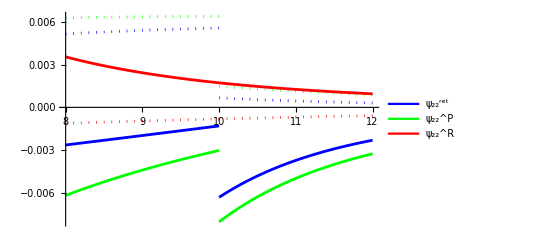

```mathematica
numericResFieldLeft=Interpolation[Table[{rmin+i/20,ψ0RSmoothPiece[2,2][rmin+i/20]},{i,0,20 (r0-rmin)-1}]];
numericResFieldRight=Interpolation[Table[{rmin+i/20,ψ0RSmoothPiece[2,2][rmin+i/20]},{i,20 (r0-rmin)+1,20 (rmax-rmin)}]]; 
numericRetFieldLeft=Interpolation[Table[{rmin+i/20,ψRet[2,2][rmin+i/20]},{i,0,20 (r0-rmin)-1}]];
numericRetFieldRight=Interpolation[Table[{rmin+i/20,ψRet[2,2][rmin+i/20]},{i,20 (r0-rmin)+1,20 (rmax-rmin)}]];
numericPFieldLeft=Interpolation[Table[{rmin+i/20,ψ0PExactWorldtubePiece[2,2][rmin+i/20]},{i,0,20 (r0-rmin)-1}]];
numericPFieldRight=Interpolation[Table[{rmin+i/20,ψ0PExactWorldtubePiece[2,2][rmin+i/20]},{i,20 (r0-rmin)+1,20 (rmax-rmin)}]];
Legended[
Show[
ReImPlot[{numericRetFieldLeft[r]},{r,rmin,r0},PlotStyle->Blue],
ReImPlot[{numericRetFieldRight[r]},{r,r0,rmax},PlotStyle->Blue],
ReImPlot[{numericPFieldLeft[r]},{r,rmin,r0},PlotStyle->Green],
ReImPlot[{numericPFieldRight[r]},{r,r0,rmax},PlotStyle->Green],
ReImPlot[{numericResFieldLeft[r]},{r,rmin,r0},PlotStyle->Red],
ReImPlot[{numericResFieldRight[r]},{r,r0,rmax},PlotStyle->Red],
PlotRange -> All,AxesLabel -> {r}]
,LineLegend[{Blue,Green,Red},{"ψ_22^ret","ψ_22^P","ψ_22^R"}]]
```

## Check --- large l behaviour

### ψ^Ret

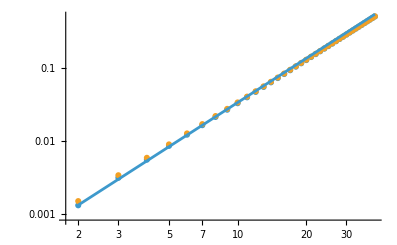

```mathematica
ψ0DataLeft=Table[{l,Sum[ψRet[l,m][Left]SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0DataRight=Table[{l,Sum[ψRet[l,m][Right]SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[ListLogLogPlot[Abs@{ψ0DataLeft,ψ0DataRight}],
LogLogPlot[{1/3000 l^2},{l,2,lmax}]]
```

Exponential rate of convergence away from the orbital radius:

{A→0.109789605083139807023556306908,b→0.226784623282776329305798715214}

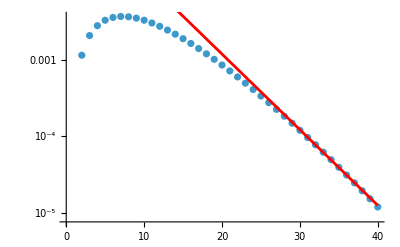

```mathematica
Clear[A,b,ψ0Data]
ψ0Data=Table[{l,Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
paraFitRuleForPuncture1 = FindFit[Re[ψ0Data[[30;;All]]],A Exp[-b l],{A,b},l]
Show[
ListLogPlot[Abs@ψ0Data],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture1},{l,2,lmax},PlotStyle->Red]
]
```

### ψ^R

#### Power-series expanded puncture

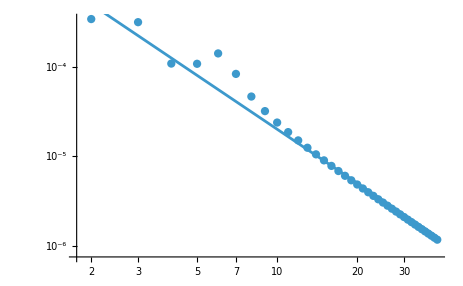

```mathematica
(* Residual field using power-series expanded puncture converges at particle. *)
Clear[A,b,ψ0Data]
ψ0Data=Table[{l,Sum[ψ0RSmoothPiece[l,m][r0]SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[ListLogLogPlot[Abs@ψ0Data],
LogLogPlot[{1/500 l^-2},{l,2,lmax}]]
```

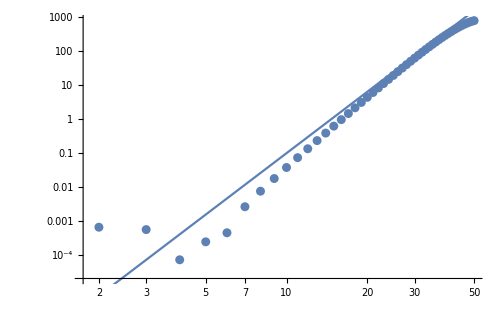

```mathematica
(* Residual field using power-series expanded puncture diverges away from particle. *)
ψ0Data=Table[{l,Sum[ψ0RSmoothPiece[l,m][rmin]SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[ListLogLogPlot[Abs@ψ0Data],
LogLogPlot[{1/10000000 l^6},{l,2,lmax}]]
```

#### “Exact” puncture

Same as above, but using the “exact” puncture.
ψ^R converges even away from particle.

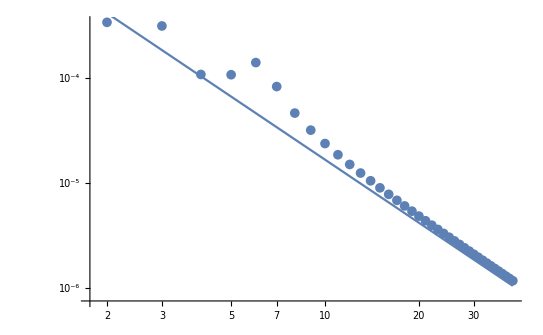

```mathematica
(* Of course get exact same results at the particle by definition *)
ψ0Data=Table[{l,Sum[ψ0RSmoothPiece[l,m][r0] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[ListLogLogPlot[Abs@ψ0Data],
LogLogPlot[{1/600 l^-2},{l,2,lmax}]]
```

Notes: 	1) checked, at least up to l=40, numerical floor kicks on when only accounting for less than 8 digits on the three fields
		(so we are using enough precision).
		2) tries computing puncture with mpmax=20 (2x more than usual). There is more of a slope in then range 30<l<40 for the residual field,
		but the residual fields is also bigger (as the puncture is different). Furthermore, keeping mpmax=10, but reducing mpmax when
		doing the summation gives visually the same plot. This all suggest that the loss of regularity due to the regularization factor is not causing
		the behaviour at 30<l<40.
		3) looking at individual m-mode contributions, it looks like the residual fields has zero crossings at different l’s. This might in part explain why it looks so flat in the range 30<l<40.

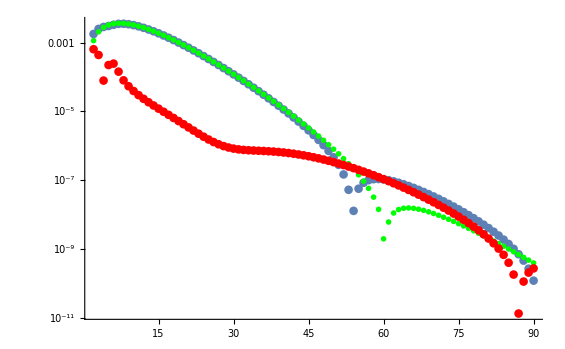

```mathematica
(* r0=10M at r=8M *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmin]-ψ0PExactWorldtubePiece[l,m][rmin]) ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

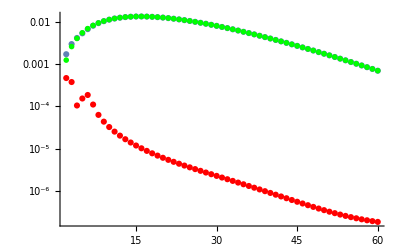

```mathematica
(* r0=10M at r=9M *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmin+1] ExpIωrstar[m][rmin+1] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmin+1] ExpIωrstar[m][rmin+1] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmin+1]-ψ0PExactWorldtubePiece[l,m][rmin+1]) ExpIωrstar[m][rmin+1] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

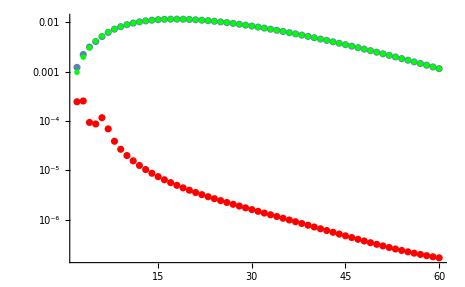

```mathematica
(* r0=10M at r=11M *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmax-1] ExpIωrstar[m][rmax-1] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmax-1] ExpIωrstar[m][rmax-1] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmax-1]-ψ0PExactWorldtubePiece[l,m][rmax-1]) ExpIωrstar[m][rmax-1] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

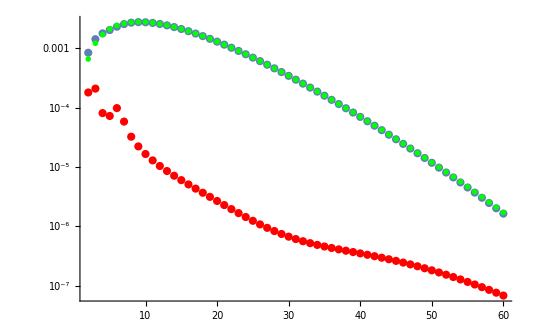

```mathematica
(* r0=10M at r=12M *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmax] ExpIωrstar[m][rmax] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmax] ExpIωrstar[m][rmax] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmax]-ψ0PExactWorldtubePiece[l,m][rmax]) ExpIωrstar[m][rmax] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

### Data

#### r=10M at r=8M

```mathematica
ψ0RetData
ψ0PData
ψ0RData
```

{{2,0.001136692762037368230814522791722396629889961838460855268+0. ⅈ},{3,0.00204975106734076217908848109105379047136999745072495919+0. ⅈ},{4,0.002758716241437021172475581944105921555130766550030635+0. ⅈ},{5,0.003247593014614952325130820938098668017863117721020143+0. ⅈ},{6,0.0035298753235577069423969570822837951282383766695+0. ⅈ},{7,0.0036352333189733099898412399128472328555857163725357+0. ⅈ},{8,0.00359964655766845967467603023895136130307276+0. ⅈ},{9,0.003459074641703609581088860498950024158838933153773+0. ⅈ},{10,0.00324595991747905911275311196962325097324186603806+0. ⅈ},{11,0.002987657553957169563449447392991136376957901843+0. ⅈ},{12,0.00270605504549647827848446201231728221087844874+0. ⅈ},{13,0.002417863664140509181515026635343318710091448526+0. ⅈ},{14,0.00213524422080596782490887113093191997408242275+0. ⅈ},{15,0.00186655801984992652428736947288555285619276869+0. ⅈ},{16,0.0016171206956217459668880954346212050495292519+0. ⅈ},{17,0.0013898931728249539369175448212930982067892805+0. ⅈ},{18,0.001186079614353774786372848118945265790094787+0. ⅈ},{19,0.00100562375291948946830663208651117576352949+0. ⅈ},{20,0.00084760726892277752775390758243068602279512+0. ⅈ},{21,0.00071056019908708550830192615702722254488513+0. ⅈ},{22,0.0005926959871863258858428799247877879543245+0. ⅈ},{23,0.000492084215781613294714763560059043013716+0. ⅈ},{24,0.000406773261965234187712423386734576787031+0. ⅈ},{25,0.00033487372161446106987764474913587526412+0. ⅈ},{26,0.00027461182785860924753875591353036646222+0. ⅈ},{27,0.000224360474689742463404291273139421348+0. ⅈ},{28,0.000182653967744260322433057275932632011+0. ⅈ},{29,0.000148191318283174768492853776643664848+0. ⅈ},{30,0.00011983179078366868199264848247185745+0. ⅈ},{31,0.000096585503908775686596021463744829611+0. ⅈ},{32,0.00007760115140005624398665215642758366+0. ⅈ},{33,0.00006215233073255060090443323613433149+0. ⅈ},{34,0.0000496235190102056005196689992506804+0. ⅈ},{35,0.000039496394467018124073620245105654+0. ⅈ},{36,0.000031336947261835570433217459584088+0. ⅈ},{37,0.00002478363698506004159239820773989+0. ⅈ},{38,0.00001953672126520292685401959048712+0. ⅈ},{39,0.00001534878759974535101119417455836+0. ⅈ},{40,0.0000120164589764026443158252816065+0. ⅈ},{41,9.3732050158047898146242182749×10^-6+0. ⅈ},{42,7.283168019459499621889748262×10^-6+0. ⅈ},{43,5.6359026479906063023547141×10^-6+0. ⅈ},{44,4.3419253436101705381959161×10^-6+0. ⅈ},{45,3.3289723286840553231294541×10^-6+0. ⅈ},{46,2.5388710623720784686944646×10^-6+0. ⅈ},{47,1.9249379812985476126804567×10^-6+0. ⅈ},{48,1.449824175601990465942056×10^-6+0. ⅈ},{49,1.083739666559756764775765×10^-6+0. ⅈ},{50,8.02995701911233757317265×10^-7+0. ⅈ},{51,5.8881268891500851400537×10^-7+0. ⅈ},{52,4.2634888594688975836669×10^-7+0. ⅈ},{53,3.039117006067054022003×10^-7+0. ⅈ},{54,2.123193841512169941017×10^-7+0. ⅈ},{55,1.44386095141429807296×10^-7+0. ⅈ},{56,9.4507779372523882022×10^-8+0. ⅈ},{57,5.833014110943277402×10^-8+0. ⅈ},{58,3.248323048490919025×10^-8+0. ⅈ},{59,1.4369912234572714×10^-8+0. ⅈ},{60,1.99777767125601×10^-9+0. ⅈ},{61,-6.15402372616421606253842711304704345121×10^-9+0. ⅈ},{62,-1.1239968791675208690037009225830442983×10^-8+0. ⅈ},{63,-1.41309857769554363071721710817631588299×10^-8+0. ⅈ},{64,-1.5479466627945174826418870883376122983×10^-8+0. ⅈ},{65,-1.5770130106834917022987762437487220271×10^-8+0. ⅈ},{66,-1.5359679041083829077439805082712490875×10^-8+0. ⅈ},{67,-1.450760921679344954868020548231934147×10^-8+0. ⅈ},{68,-1.340005272093292007294679769236797197×10^-8+0. ⅈ},{69,-1.21681550490101334735549726472688553×10^-8+0. ⅈ},{70,-1.09021764557275723839845833375459384×10^-8+0. ⅈ},{71,-9.6622600501667607306160774003339854×10^-9+0. ⅈ},{72,-8.4866106137099899710975002416989179×10^-9+0. ⅈ},{73,-7.397669645378745026909068099922913×10^-9+0. ⅈ},{74,-6.4067459985386762806598783251728×10^-9+0. ⅈ},{75,-5.5174613556181557399230063789963×10^-9+0. ⅈ},{76,-4.7282905535296095721656394867994×10^-9+0. ⅈ},{77,-4.034414248543383119372552273898×10^-9+0. ⅈ},{78,-3.4290522179752450425798279134626×10^-9+0. ⅈ},{79,-2.904407012300075426725522890848×10^-9+0. ⅈ},{80,-2.452317503347361575168439360476×10^-9+0. ⅈ},{81,-2.06469836414103793531472854404037614757×10^-9+0. ⅈ},{82,-1.73382325783178411783065236506057628606×10^-9+0. ⅈ},{83,-1.4524953858564495748532188881528568821×10^-9+0. ⅈ},{84,-1.2141381573180626154770089969928538099×10^-9+0. ⅈ},{85,-1.012830385512634906053725274787306129×10^-9+0. ⅈ},{86,-8.433040343520807688517093767021399843×10^-10+0. ⅈ},{87,-7.00917686192993039493273450937044945×10^-10+0. ⅈ},{88,-5.816152365668458292238780625305831×10^-10+0. ⅈ},{89,-4.818765687186263115403573159824283×10^-10+0. ⅈ},{90,-3.98664909281513777405346458382849×10^-10+0. ⅈ}}

{{2,0.00177673-5.42101×10^-20 ⅈ},{3,0.00248587+1.0842×10^-19 ⅈ},{4,0.00283743+0. ⅈ},{5,0.00302484+0. ⅈ},{6,0.00328491-2.1684×10^-19 ⅈ},{7,0.00349235+6.50521×10^-19 ⅈ},{8,0.00351966+4.33681×10^-19 ⅈ},{9,0.00340506-6.50521×10^-19 ⅈ},{10,0.00320671+0. ⅈ},{11,0.00295787-2.1684×10^-19 ⅈ},{12,0.0026828+2.1684×10^-19 ⅈ},{13,0.00239937+0. ⅈ},{14,0.00212036+0. ⅈ},{15,0.0018545+0. ⅈ},{16,0.00160732+2.1684×10^-19 ⅈ},{17,0.00138192-4.33681×10^-19 ⅈ},{18,0.00117961+1.0842×10^-19 ⅈ},{19,0.00100037-1.0842×10^-19 ⅈ},{20,0.000843359+2.1684×10^-19 ⅈ},{21,0.000707125-1.0842×10^-19 ⅈ},{22,0.000589916+5.42101×10^-20 ⅈ},{23,0.000489825+5.42101×10^-20 ⅈ},{24,0.000404924-1.89735×10^-19 ⅈ},{25,0.00033334+2.71051×10^-20 ⅈ},{26,0.000273318-2.71051×10^-20 ⅈ},{27,0.000223245+0. ⅈ},{28,0.000181667-2.71051×10^-20 ⅈ},{29,0.000147295+4.06576×10^-20 ⅈ},{30,0.000118998+0. ⅈ},{31,0.0000957935+1.35525×10^-20 ⅈ},{32,0.0000768366+2.03288×10^-20 ⅈ},{33,0.000061406+6.77626×10^-21 ⅈ},{34,0.0000488903+1.35525×10^-20 ⅈ},{35,0.0000387742+1.01644×10^-20 ⅈ},{36,0.0000306259+0. ⅈ},{37,0.0000240854+0. ⅈ},{38,0.0000188537+3.38813×10^-21 ⅈ},{39,0.000014684+1.69407×10^-21 ⅈ},{40,0.000011373+8.47033×10^-21 ⅈ},{41,8.7540898047918494647829003995121036005873324921206187372330056×10^-6+0. ⅈ},{42,6.6910319749565367238233194132992200575829011764390198030684263×10^-6+0. ⅈ},{43,5.0729783677775440818024809819003450527298591093478209453924081×10^-6+0. ⅈ},{44,3.8099535151733823595001273412172820280704213412155174645737563×10^-6+0. ⅈ},{45,2.8291774447818956472299134761429938954786555967075872669887633×10^-6+0. ⅈ},{46,2.0719675195124642562746480297969827680889142127234039230769052×10^-6+0. ⅈ},{47,1.4911582353539514071224159863264745221992047836448849701718074×10^-6+0. ⅈ},{48,1.0489619733779569504381239740624421455184870089041881637202128×10^-6+0. ⅈ},{49,7.1520263569942430192251256233698276251750892242110315588323795×10^-7+0. ⅈ},{50,4.6586273370406858959872644043699254448134119271878714257993156×10^-7+0. ⅈ},{51,2.818925721843625463527478339495065694565084627475567368190333×10^-7+0. ⅈ},{52,1.48237538323493322707823426704578567417640376830760629971498×10^-7+0. ⅈ},{53,5.30460969893483686243183910401662591413317324865200726203703×10^-8+0. ⅈ},{54,-1.29730926459693895774424551685073313830844775640104712228306×10^-8+0. ⅈ},{55,-5.707145937227928369150691366335714986493929603689152040331258×10^-8+0. ⅈ},{56,-8.488035325647588226432279707257604239796495985196531364073581×10^-8+0. ⅈ},{57,-1.007488471716135308226837697100843258340808232493343374911127×10^-7+0. ⅈ},{58,-1.0801475350653170610052050280604147602165891180413883048504435×10^-7+0. ⅈ},{59,-1.0922142949245101312237645506574049607467493081103412313225324×10^-7+0. ⅈ},{60,-1.0629070268213074491183202649797368496764623046733243351099297×10^-7+0. ⅈ},{61,-1.0066037765107567261155042580146375166074998045161351424177317×10^-7+0. ⅈ},{62,-9.3393231502123171135617675106141531563569314701619770728145082×10^-8+0. ⅈ},{63,-8.5263120834906504387908803985546996015387558372881389142589411×10^-8+0. ⅈ},{64,-7.6822764052844769827867247084244352791032751628862654264180276×10^-8+0. ⅈ},{65,-6.8456893442740246763163958380007994950469990316043089800999527×10^-8+0. ⅈ},{66,-6.0423759801587143950568929023277125771046236164566204283536052×10^-8+0. ⅈ},{67,-5.2887391614709860718143810974591953155130093623403722868270111×10^-8+0. ⅈ},{68,-4.5942538171928162240150124955361588928074197584638704534604583×10^-8+0. ⅈ},{69,-3.9633842433068050579813898554361442357250450657818459159654927×10^-8+0. ⅈ},{70,-3.3970478943058785277337155032324037253606372665920732740818021×10^-8+0. ⅈ},{71,-2.8937241355187890171933513724986431095468836947176305053879445×10^-8+0. ⅈ},{72,-2.4502862133257211361657409785301279276028513574450048301192649×10^-8+0. ⅈ},{73,-2.062618467733538101286707558374310964380717487599202299034323×10^-8+0. ⅈ},{74,-1.7260677975238159770582252683236896259940509101814229631132169×10^-8+0. ⅈ},{75,-1.4357679791419163368914553824876327013564608794697022641888643×10^-8+0. ⅈ},{76,-1.1868671354331848245669227896148471374196277389504355547583344×10^-8+0. ⅈ},{77,-9.7468204062200323514443218142597307324258790578842802700299891×10^-9+0. ⅈ},{78,-7.9479770127757314929570302123075064979167902716991730369132361×10^-9+0. ⅈ},{79,-6.4312649984646493222813964856736021887903262279169704837386797×10^-9+0. ⅈ},{80,-5.1593790946495984596017126810756503886821964177292902991991428×10^-9+0. ⅈ},{81,-4.0986720997271697555854197313426426436757921204887159142732909×10^-9+0. ⅈ},{82,-3.2190961330716496714999677595001587284686680495691802351429678×10^-9+0. ⅈ},{83,-2.4940462753307374763531074212833576663129582483965602139387311×10^-9+0. ⅈ},{84,-1.9001426096218914123851161012404106736037531342040540591445451×10^-9+0. ⅈ},{85,-1.4169771769291194182094530359255478470477777308321178205000813×10^-9+0. ⅈ},{86,-1.0268450473123517364411642249445883107529168361627417339978685×10^-9+0. ⅈ},{87,-7.1447311798190882999070229446545194340074337750064170626832028×10^-10+0. ⅈ},{88,-4.667560069690562894543737508524480789017157400762950767015885×10^-10+0. ⅈ},{89,-2.725052208791767826211814669342783011533983588443890151820769×10^-10+0. ⅈ},{90,-1.22215402392375117937787813524817117609686482999599952726152×10^-10+0. ⅈ}}

{{2,-0.000640037+0. ⅈ},{3,-0.000436118+0. ⅈ},{4,-0.0000787174+0. ⅈ},{5,0.000222751+0. ⅈ},{6,0.000244962+0. ⅈ},{7,0.000142882+0. ⅈ},{8,0.0000799829+3.38813×10^-21 ⅈ},{9,0.0000540169+0. ⅈ},{10,0.0000392546+0. ⅈ},{11,0.00002979+0. ⅈ},{12,0.0000232543+0. ⅈ},{13,0.000018493+0. ⅈ},{14,0.0000148811+0. ⅈ},{15,0.0000120565-4.23516×10^-22 ⅈ},{16,9.79886×10^-6-4.23516×10^-22 ⅈ},{17,7.96863×10^-6+2.11758×10^-22 ⅈ},{18,6.47332×10^-6+0. ⅈ},{19,5.24878×10^-6-2.11758×10^-22 ⅈ},{20,4.24807×10^-6+0. ⅈ},{21,3.435×10^-6+0. ⅈ},{22,2.78018×10^-6+0. ⅈ},{23,2.25883×10^-6-1.05879×10^-22 ⅈ},{24,1.84951×10^-6+2.11758×10^-22 ⅈ},{25,1.53332×10^-6+3.17637×10^-22 ⅈ},{26,1.29363×10^-6+0. ⅈ},{27,1.11575×10^-6+0. ⅈ},{28,9.86879×10^-7+1.05879×10^-22 ⅈ},{29,8.95965×10^-7+0. ⅈ},{30,8.3361×10^-7-1.05879×10^-22 ⅈ},{31,7.91964×10^-7-5.29396×10^-23 ⅈ},{32,7.64595×10^-7+0. ⅈ},{33,7.46354×10^-7+2.64698×10^-23 ⅈ},{34,7.33224×10^-7+2.64698×10^-23 ⅈ},{35,7.22178×10^-7-2.64698×10^-23 ⅈ},{36,7.11027×10^-7-3.97047×10^-23 ⅈ},{37,6.98282×10^-7-8.27181×10^-24 ⅈ},{38,6.83023×10^-7+1.65436×10^-23 ⅈ},{39,6.64781×10^-7+1.32349×10^-23 ⅈ},{40,6.43434×10^-7+2.64698×10^-23 ⅈ},{41,6.191152110129403498413178754×10^-7+0. ⅈ},{42,5.92136044502962898066428848×10^-7+0. ⅈ},{43,5.62924280213062220552233118×10^-7+0. ⅈ},{44,5.31971828436788178695788759×10^-7+0. ⅈ},{45,4.9979488390215967589954063×10^-7+0. ⅈ},{46,4.669035428596142124198166×10^-7+0. ⅈ},{47,4.337797459445962055580407×10^-7+0. ⅈ},{48,4.008622022240335155039325×10^-7+0. ⅈ},{49,3.68537030860332462853252×10^-7+0. ⅈ},{50,3.37132968207165167718539×10^-7+0. ⅈ},{51,3.0692011673064596765263×10^-7+0. ⅈ},{52,2.7811134762339643565887×10^-7+0. ⅈ},{53,2.50865603617357033576×10^-7+0. ⅈ},{54,2.252924767971863836791×10^-7+0. ⅈ},{55,2.01457554513709090988×10^-7+0. ⅈ},{56,1.79388132628999764287×10^-7+0. ⅈ},{57,1.5907898828104630484×10^-7+0. ⅈ},{58,1.404979839914408964×10^-7+0. ⅈ},{59,1.235913417270237271×10^-7+0. ⅈ},{60,1.08288480353386755×10^-7+0. ⅈ},{61,9.4506353924911456549011998688416708209536×10^-8+0. ⅈ},{62,8.215326271044796244558066588031108858061×10^-8+0. ⅈ},{63,7.113213505795106808073663290378383718552×10^-8+0. ⅈ},{64,6.13432974248995950014483762008682298083×10^-8+0. ⅈ},{65,5.268676333590532974017619594252077468×10^-8+0. ⅈ},{66,4.5064080760503314873129123940564634896×10^-8+0. ⅈ},{67,3.8379782397916411169463605492272611682×10^-8+0. ⅈ},{68,3.254248545099524216720332726299361695×10^-8+0. ⅈ},{69,2.746568738405791710625892590709258705×10^-8+0. ⅈ},{70,2.30683024873312128933525716947780988×10^-8+0. ⅈ},{71,1.9274981305021129441317436324652446×10^-8+0. ⅈ},{72,1.6016251519547221390559909543602361×10^-8+0. ⅈ},{73,1.32285150319566359859580074838202×10^-8+0. ⅈ},{74,1.08539319766994834899223743580641×10^-8+0. ⅈ},{75,8.84021843580100762899154744588×10^-9+0. ⅈ},{76,7.1403808008022386735035884093491×10^-9+0. ⅈ},{77,5.7124061576766492320717695403618×10^-9+0. ⅈ},{78,4.5189247948004864503772022988449×10^-9+0. ⅈ},{79,3.526857986164573895555873594826×10^-9+0. ⅈ},{80,2.707061591302236884433273320599×10^-9+0. ⅈ},{81,2.03397373558613182027069118730226649611×10^-9+0. ⅈ},{82,1.48527287523986555366931539443958244241×10^-9+0. ⅈ},{83,1.0415508894742879014998885331305007842×10^-9+0. ⅈ},{84,6.860044523038287969081071042475568637×10^-10+0. ⅈ},{85,4.041467914164845121557277611382417178×10^-10+0. ⅈ},{86,1.83541012960270967589454848242448326×10^-10+0. ⅈ},{87,1.3555431788915790497428843528407×10^-11+0. ⅈ},{88,-1.14859229597789539769504311678135×10^-10+0. ⅈ},{89,-2.0937134783944952891917584904815×10^-10+0. ⅈ},{90,-2.76449506889138659467558644858031×10^-10+0. ⅈ}}

#### r=10M at r=9M

```mathematica
ψ0RetData
ψ0PData
ψ0RData
```

{{2,0.001228837327083156148368598903861458385388197664664466586878825+0. ⅈ},{3,0.00256446937550932464193046308708189067300891942592353699293319+0. ⅈ},{4,0.003989409654364530412614539015394057611376884347558777113802+0. ⅈ},{5,0.00542405051314350928239107117738652373801235980451065805563+0. ⅈ},{6,0.0068061545161162494655644258088419091070998294729682713+0. ⅈ},{7,0.0080905866816103454663045004854337927275473904011018670902+0. ⅈ},{8,0.00924707762064313712139535953362957460007285432827+0. ⅈ},{9,0.010257395329575279654838671210951891240684225043085484+0. ⅈ},{10,0.0111126891295381571415844377972798496699503161547334123+0. ⅈ},{11,0.011811224068988237646283248404296662553767589085675487+0. ⅈ},{12,0.01235652002496680718165697145100916459846716711971951+0. ⅈ},{13,0.01275585172202433664084972392434190935798147462430471+0. ⅈ},{14,0.0130190552026535444250608544726159467825943298536607+0. ⅈ},{15,0.01315758925661363976535622241290937679547762834671+0. ⅈ},{16,0.013183806663012680689252600288175546654851280450483+0. ⅈ},{17,0.013110396767902809265389597970653553811918282877936+0. ⅈ},{18,0.01294996703436016853807684429333287679803376384795+0. ⅈ},{19,0.0127147365521218011622540475326182537839438418095+0. ⅈ},{20,0.012416319081971221797668297743089994736096622901+0. ⅈ},{21,0.012065577104212929039984227172170813815495280893+0. ⅈ},{22,0.01167253162513875946263294979096789604186854403+0. ⅈ},{23,0.0112463152536372341031703306926652230269552247+0. ⅈ},{24,0.0107951583681653875831002443444705040652372324+0. ⅈ},{25,0.010326400119516460029712719220385160676692424+0. ⅈ},{26,0.0098465176157179325081173721843521039990989216+0. ⅈ},{27,0.009361167962408697365720123079127692896678153+0. ⅈ},{28,0.00887523892835613287382028810701448579613358+0. ⅈ},{29,0.0083929049082223876934835758912185992372935+0. ⅈ},{30,0.0079176855946096935443058477609383602093305+0. ⅈ},{31,0.0074525053753993540506487469646208902338349+0. ⅈ},{32,0.006999751962969796372093139335699392418687+0. ⅈ},{33,0.00656133315807392836163253521893477533059+0. ⅈ},{34,0.00613873096903922299463599386705081685291+0. ⅈ},{35,0.0057330525600553058956690838802373783479+0. ⅈ},{36,0.005345077702007068266021761925848817648+0. ⅈ},{37,0.00497530255513863280308497844254150607+0. ⅈ},{38,0.00462397973278350760566194498285236451+0. ⅈ},{39,0.00429115468614186557869194780819265047+0. ⅈ},{40,0.0039766985171872899271425571299916257+0. ⅈ},{41,0.00368033737486324383581555789364881+0. ⅈ},{42,0.003401678622612715826211182218766261+0. ⅈ},{43,0.003140233986135299825576099506099338+0. ⅈ},{44,0.00289543990168697651012823076270716+0. ⅈ},{45,0.00266667528936243395954224427245016+0. ⅈ},{46,0.0024532769743687746384095462961155+0. ⅈ},{47,0.0022545529737262314772036257163489+0. ⅈ},{48,0.002069793857256734485793323811394+0. ⅈ},{49,0.001898282381059175319218258706053+0. ⅈ},{50,0.00173930157964804881088367774125+0. ⅈ},{51,0.0015921414901223609440096644258+0. ⅈ},{52,0.001456104668579901256000076049+0. ⅈ},{53,0.001330510645839949428125645919+0. ⅈ},{54,0.00121469945664242382125450859+0. ⅈ},{55,0.00110803436404211161862669533+0. ⅈ},{56,0.0010099038888465771785285362+0. ⅈ},{57,0.00091972324274525649393258492+0. ⅈ},{58,0.0008369352532999097897454002+0. ⅈ},{59,0.000761010859240542878523163+0. ⅈ},{60,0.000691449245542562929755575+0. ⅈ}}

{{2,0.00169239+5.42101×10^-20 ⅈ},{3,0.00293801+1.0842×10^-19 ⅈ},{4,0.0040937+0. ⅈ},{5,0.00527148+4.33681×10^-19 ⅈ},{6,0.00662155-4.33681×10^-19 ⅈ},{7,0.00798078+4.33681×10^-19 ⅈ},{8,0.00918449+0. ⅈ},{9,0.0102141-1.73472×10^-18 ⅈ},{10,0.0110804+0. ⅈ},{11,0.011786+0. ⅈ},{12,0.0123363+8.67362×10^-19 ⅈ},{13,0.0127392+8.67362×10^-19 ⅈ},{14,0.0130051+8.67362×10^-19 ⅈ},{15,0.0131457-8.67362×10^-19 ⅈ},{16,0.0131736+0. ⅈ},{17,0.0131016+4.33681×10^-18 ⅈ},{18,0.0129422+3.46945×10^-18 ⅈ},{19,0.0127079+8.67362×10^-19 ⅈ},{20,0.0124102-8.67362×10^-19 ⅈ},{21,0.0120601+0. ⅈ},{22,0.0116677-8.67362×10^-19 ⅈ},{23,0.0112419+8.67362×10^-19 ⅈ},{24,0.0107912+1.73472×10^-18 ⅈ},{25,0.0103228+0. ⅈ},{26,0.00984323+0. ⅈ},{27,0.00935818-2.60209×10^-18 ⅈ},{28,0.00887251-4.33681×10^-19 ⅈ},{29,0.00839042-8.67362×10^-19 ⅈ},{30,0.00791541+8.67362×10^-19 ⅈ},{31,0.00745043+0. ⅈ},{32,0.00699786-1.73472×10^-18 ⅈ},{33,0.0065596-8.67362×10^-19 ⅈ},{34,0.00613715-1.30104×10^-18 ⅈ},{35,0.00573161+0. ⅈ},{36,0.00534377+0. ⅈ},{37,0.00497411-1.30104×10^-18 ⅈ},{38,0.00462289+2.1684×10^-19 ⅈ},{39,0.00429017-6.50521×10^-19 ⅈ},{40,0.0039758+4.33681×10^-19 ⅈ},{41,0.0036795199740249148561824015088134774079497934934632044619719494+0. ⅈ},{42,0.0034009360791739157608336020332307225217616751754965189195739951+0. ⅈ},{43,0.0031395594895801512886683609846186041632330909857440521838736111+0. ⅈ},{44,0.0028948271008774758049709942566904419820777937943759393363137919+0. ⅈ},{45,0.0026661182688425288535341880171198265120342573607813369088906579+0. ⅈ},{46,0.0024527702340490640212334348489298209671521432194939499576515613+0. ⅈ},{47,0.0022540914108624678809358150560453871031647971786329937084651038+0. ⅈ},{48,0.0020693727499023171781355184781234427472628004144040988528804521+0. ⅈ},{49,0.001897897372387334933326975842997032482109774793887851071017905+0. ⅈ},{50,0.0017389486627122938074141482866935641657119869103899992957981135+0. ⅈ},{51,0.0015918169927612664785819134023609360766240523008448358332498222+0. ⅈ},{52,0.001455805238280517697217176881228422229822518810862600052325358+0. ⅈ},{53,0.001330233234458040767477748960732131181230989735938681670519955+0. ⅈ},{54,0.0012144413049416551899364904189294240975088335388586121846004666+0. ⅈ},{55,0.0011077929860617621192149982686740102153810315809023107992717499+0. ⅈ},{56,0.0010096770561413751974886543293455242283292344909185822947799263+0. ⅈ},{57,0.00091950896856406795501148888670961757927482077164803956079090755+0. ⅈ},{58,0.00083673177678440760338018589278379420797980202736643328198740582+0. ⅈ},{59,0.00076081662973246251745805965777758315414564554757864154516981544+0. ⅈ},{60,0.00069126290709022971747730989842765241830326745730557476073581454+0. ⅈ}}

{{2,-0.000463551+0. ⅈ},{3,-0.000373543+0. ⅈ},{4,-0.000104286+0. ⅈ},{5,0.000152568-1.35525×10^-20 ⅈ},{6,0.000184607+0. ⅈ},{7,0.000109808+0. ⅈ},{8,0.000062584+0. ⅈ},{9,0.0000433365+0. ⅈ},{10,0.0000323313+0. ⅈ},{11,0.0000252116+8.47033×10^-22 ⅈ},{12,0.0000202662+0. ⅈ},{13,0.0000166638+0. ⅈ},{14,0.0000139477+4.23516×10^-22 ⅈ},{15,0.0000118449+8.47033×10^-22 ⅈ},{16,0.000010182-4.23516×10^-22 ⅈ},{17,8.84317×10^-6-2.11758×10^-22 ⅈ},{18,7.74872×10^-6+0. ⅈ},{19,6.84172×10^-6+0. ⅈ},{20,6.08073×10^-6-1.05879×10^-22 ⅈ},{21,5.43495×10^-6+0. ⅈ},{22,4.88113×10^-6+2.11758×10^-22 ⅈ},{23,4.40151×10^-6+1.05879×10^-22 ⅈ},{24,3.98236×10^-6-1.05879×10^-22 ⅈ},{25,3.61299×10^-6+5.29396×10^-23 ⅈ},{26,3.28499×10^-6-5.29396×10^-23 ⅈ},{27,2.99176×10^-6+0. ⅈ},{28,2.72801×10^-6+5.29396×10^-23 ⅈ},{29,2.48957×10^-6-5.29396×10^-23 ⅈ},{30,2.27306×10^-6-5.29396×10^-23 ⅈ},{31,2.07575×10^-6-2.64698×10^-23 ⅈ},{32,1.89544×10^-6-5.29396×10^-23 ⅈ},{33,1.73032×10^-6-5.29396×10^-23 ⅈ},{34,1.5789×10^-6-1.05879×10^-22 ⅈ},{35,1.43993×10^-6+2.64698×10^-23 ⅈ},{36,1.31236×10^-6+2.64698×10^-23 ⅈ},{37,1.19528×10^-6+5.29396×10^-23 ⅈ},{38,1.0879×10^-6-2.64698×10^-23 ⅈ},{39,9.89534×10^-7+2.64698×10^-23 ⅈ},{40,8.99557×10^-7-2.64698×10^-23 ⅈ},{41,8.174008383289796331563848353323×10^-7+0. ⅈ},{42,7.42543438800065377580185535538×10^-7+0. ⅈ},{43,6.74496555148536907738521480734×10^-7+0. ⅈ},{44,6.1280080950070515723650601672×10^-7+0. ⅈ},{45,5.5702051990510600805625533033×10^-7+0. ⅈ},{46,5.067403197106171761114471857×10^-7+0. ⅈ},{47,4.615628637635962678106603035×10^-7+0. ⅈ},{48,4.21107354417307657805333271×10^-7+0. ⅈ},{49,3.85008671840385891282863056×10^-7+0. ⅈ},{50,3.5291693575500346952945456×10^-7+0. ⅈ},{51,3.2449736109446542775102342×10^-7+0. ⅈ},{52,2.994302993835587828991677×10^-7+0. ⅈ},{53,2.77411381908660647896959×10^-7+0. ⅈ},{54,2.58151700768631318018171×10^-7+0. ⅈ},{55,2.4137798034949941169706×10^-7+0. ⅈ},{56,2.2683270520198103988191×10^-7+0. ⅈ},{57,2.14274181188538921096×10^-7+0. ⅈ},{58,2.03476515502186365214×10^-7+0. ⅈ},{59,1.94229508080361065103×10^-7+0. ⅈ},{60,1.8633845233321227827×10^-7+0. ⅈ}}

#### r=10M at r=11M

```mathematica
ψ0RetData
ψ0PData
ψ0RData
```

{{2,0.000970833675406459859618434583595847672145395387165141423159148+0. ⅈ},{3,0.0019605724779452465369614607968764469733538305115721810222817+0. ⅈ},{4,0.003034614425672068414155309153017989196355941598673613252673+0. ⅈ},{5,0.00413835534673955289676588027749757797412940843997826742238+0. ⅈ},{6,0.0052279752978347121573879386618038739424094909649956542898+0. ⅈ},{7,0.0062697582607502787101120391224816748111675524416358353437+0. ⅈ},{8,0.007239104504007182402799236272144216409265706582259780017+0. ⅈ},{9,0.00811914248169142328612491948347591869519363042908199718+0. ⅈ},{10,0.0088993078370436309986369860874814991146996684121609418+0. ⅈ},{11,0.0095740615844640072418874768050814724829025778231408689+0. ⅈ},{12,0.0101417921990461527497146609608214240604171178111399+0. ⅈ},{13,0.0106038971421542699811133454919531088013399547500218+0. ⅈ},{14,0.010964024491391963911601354153767759245613265914341+0. ⅈ},{15,0.01122745267624540701864356244622458865012332075058+0. ⅈ},{16,0.0114005875427907020027646517022406615016068569506+0. ⅈ},{17,0.0114905582567374245397583507479143491577059696542+0. ⅈ},{18,0.011504895975612497832374391612537851845590372546+0. ⅈ},{19,0.01145128148308216693764418275616455637755299619+0. ⅈ},{20,0.011337349998996582301092315810353500640255449+0. ⅈ},{21,0.0111705431484501336471549358814469001949414749+0. ⅈ},{22,0.010957999607728414640628048476284498185084281+0. ⅈ},{23,0.01070647726794446055633994866718845213091386+0. ⅈ},{24,0.01042230089318059743398960771543696554022051+0. ⅈ},{25,0.0101113302225501845521407806711977376933865+0. ⅈ},{26,0.009778944296176596065298536688333848132643+0. ⅈ},{27,0.009430038492736140001053751800416351634008+0. ⅈ},{28,0.00906903136774562009397719111421983331203+0. ⅈ},{29,0.00869987889191699488554236095126909491518+0. ⅈ},{30,0.0083260941204836920518161945467034601894+0. ⅈ},{31,0.007950770688576701993686171974788250197+0. ⅈ},{32,0.007576608834161667318592103311007492957+0. ⅈ},{33,0.00720594290710781422387898178252564784+0. ⅈ},{34,0.0068407695378754187630562120352794119+0. ⅈ},{35,0.0064827758183185626370897962508669113+0. ⅈ},{36,0.006133366995579184083619057126532339+0. ⅈ},{37,0.00579369330262196035794907294636102+0. ⅈ},{38,0.0054646756496017524980166280212755+0. ⅈ},{39,0.005147029982376615930829406283919+0. ⅈ},{40,0.004841290181001910047035894033455+0. ⅈ},{41,0.00454782942446479320940337684327+0. ⅈ},{42,0.00426687999037862036037374314826+0. ⅈ},{43,0.0039985514916740261792209889202+0. ⅈ},{44,0.003742847578047107917361427277+0. ⅈ},{45,0.003499681149370963191931084263+0. ⅈ},{46,0.003268888142559987559261145399+0. ⅈ},{47,0.00305023996343952141308946847+0. ⅈ},{48,0.0028434546418115796101004054+0. ⅈ},{49,0.002648206791788874674294202+0. ⅈ},{50,0.0024641364611543477361984+0. ⅈ},{51,0.00229085695345981758612193+0. ⅈ},{52,0.0021279617051943643943613+0. ⅈ},{53,0.0019750302979530281116388+0. ⅈ},{54,0.001831633682384936000824+0. ⅈ},{55,0.00169733868701466956815+0. ⅈ},{56,0.0015717118809885807186+0. ⅈ},{57,0.0014543228555417707646+0. ⅈ},{58,0.001344746984625794347+0. ⅈ},{59,0.00124256772077210669+0. ⅈ},{60,0.00114737847796211693+0. ⅈ}}

{{2,0.00121587+0. ⅈ},{3,0.00221466+0. ⅈ},{4,0.00312832+4.33681×10^-19 ⅈ},{5,0.00405112+0. ⅈ},{6,0.00511128-4.33681×10^-19 ⅈ},{7,0.00620038+4.33681×10^-19 ⅈ},{8,0.00720016+4.33681×10^-19 ⅈ},{9,0.00809228-8.67362×10^-19 ⅈ},{10,0.00887927+8.67362×10^-19 ⅈ},{11,0.0095584-2.60209×10^-18 ⅈ},{12,0.0101292+0. ⅈ},{13,0.0105935+0. ⅈ},{14,0.0109552-8.67362×10^-19 ⅈ},{15,0.0112199-2.60209×10^-18 ⅈ},{16,0.0113941+0. ⅈ},{17,0.0114849-8.67362×10^-19 ⅈ},{18,0.0114999+1.73472×10^-18 ⅈ},{19,0.0114468-8.67362×10^-19 ⅈ},{20,0.0113334-1.73472×10^-18 ⅈ},{21,0.011167+0. ⅈ},{22,0.0109548+1.73472×10^-18 ⅈ},{23,0.0107035-8.67362×10^-19 ⅈ},{24,0.0104196+0. ⅈ},{25,0.0101089-4.33681×10^-19 ⅈ},{26,0.00977669-1.30104×10^-18 ⅈ},{27,0.00942797+8.67362×10^-19 ⅈ},{28,0.00906713-8.67362×10^-19 ⅈ},{29,0.00869812-8.67362×10^-19 ⅈ},{30,0.00832448+0. ⅈ},{31,0.00794928+4.33681×10^-19 ⅈ},{32,0.00757523+0. ⅈ},{33,0.00720467-8.67362×10^-19 ⅈ},{34,0.0068396-4.33681×10^-19 ⅈ},{35,0.00648169-4.33681×10^-19 ⅈ},{36,0.00613237-4.33681×10^-19 ⅈ},{37,0.00579277-4.33681×10^-19 ⅈ},{38,0.00546383+0. ⅈ},{39,0.00514625+4.33681×10^-19 ⅈ},{40,0.00484057+6.50521×10^-19 ⅈ},{41,0.00454716706265988903951038600724772982341651866548353629319411175+0. ⅈ},{42,0.00426626999572732792422440111389321813055103022270406150260557778+0. ⅈ},{43,0.00399798970041331530620564576667496426329408781874484063910188332+0. ⅈ},{44,0.00374233008062871180858804027001884813176171025991346179427286875+0. ⅈ},{45,0.00349920427674414578919712688596658029084480052174583170075458125+0. ⅈ},{46,0.00326844845488847088112815700945240910165284056409021661640512288+0. ⅈ},{47,0.00304983424052977784295017887980032903738714932883275345257771912+0. ⅈ},{48,0.00284307987469290016618719640563046700491003475446382445678347297+0. ⅈ},{49,0.00264786017501907258941551307910906259634527009386443877140230913+0. ⅈ},{50,0.00246381538553362587370674653928608247020570923658367052451984892+0. ⅈ},{51,0.0022905589989233081168325153363656156247913026656325669570033945+0. ⅈ},{52,0.0021276846337245319465090297820126237080789167055547996303966134+0. ⅈ},{53,0.00197477204640934992588758100415536631862135632092444520114152637+0. ⅈ},{54,0.0018313923551924223378495344232693899517332435117316536875178887+0. ⅈ},{55,0.0016971125486868850893319521799235634368031546271179406978519449+0. ⅈ},{56,0.0015714993484865884077475444264587597421713110107476948577601087+0. ⅈ},{57,0.0014541224904893042467720218475417867381733076192896829230272698+0. ⅈ},{58,0.0013445574854142158865576257753934722254948350363391220854973051+0. ⅈ},{59,0.0012423879145973857495434440901103159838279681627431143821558028+0. ⅈ},{60,0.0011472073128410683857943315888372463280038388558075926631053619+0. ⅈ}}

{{2,-0.000245039+0. ⅈ},{3,-0.000254085+0. ⅈ},{4,-0.0000937055+0. ⅈ},{5,0.0000872368+0. ⅈ},{6,0.000116696+0. ⅈ},{7,0.0000693749+0. ⅈ},{8,0.0000389461+0. ⅈ},{9,0.0000268624+0. ⅈ},{10,0.0000200416+4.23516×10^-22 ⅈ},{11,0.0000156639+2.11758×10^-22 ⅈ},{12,0.0000126381+0. ⅈ},{13,0.0000104405+1.05879×10^-22 ⅈ},{14,8.78586×10^-6+1.05879×10^-22 ⅈ},{15,7.5052×10^-6+1.58819×10^-22 ⅈ},{16,6.49183×10^-6+0. ⅈ},{17,5.67507×10^-6+2.64698×10^-23 ⅈ},{18,5.00629×10^-6-2.64698×10^-23 ⅈ},{19,4.451×10^-6+2.64698×10^-23 ⅈ},{20,3.98409×10^-6+2.64698×10^-23 ⅈ},{21,3.58694×10^-6+1.32349×10^-23 ⅈ},{22,3.24551×10^-6+0. ⅈ},{23,2.94904×10^-6-6.61744×10^-24 ⅈ},{24,2.68922×10^-6+1.32349×10^-23 ⅈ},{25,2.45957×10^-6+1.65436×10^-23 ⅈ},{26,2.25499×10^-6-2.97785×10^-23 ⅈ},{27,2.07144×10^-6+3.63959×10^-23 ⅈ},{28,1.90571×10^-6-6.61744×10^-24 ⅈ},{29,1.75524×10^-6+1.15805×10^-23 ⅈ},{30,1.61797×10^-6-1.98523×10^-23 ⅈ},{31,1.49224×10^-6-2.68834×10^-24 ⅈ},{32,1.37669×10^-6-5.35599×10^-23 ⅈ},{33,1.27023×10^-6-2.23339×10^-23 ⅈ},{34,1.17195×10^-6-2.97785×10^-23 ⅈ},{35,1.0811×10^-6-6.12114×10^-23 ⅈ},{36,9.97044×10^-7-5.45939×10^-23 ⅈ},{37,9.19255×10^-7-1.98523×10^-23 ⅈ},{38,8.47273×10^-7+3.63959×10^-23 ⅈ},{39,7.80694×10^-7+1.32349×10^-23 ⅈ},{40,7.19164×10^-7-2.97785×10^-23 ⅈ},{41,6.6236180490416989299083602×10^-7+0. ⅈ},{42,6.0999465129243614934203436×10^-7+0. ⅈ},{43,5.617912607108730153431536×10^-7+0. ⅈ},{44,5.17497418396108773387007×10^-7+0. ⅈ},{45,4.76872626817402733957377×10^-7+0. ⅈ},{46,4.3968767151667813298839×10^-7+0. ⅈ},{47,4.0572290974357013928959×10^-7+0. ⅈ},{48,3.74767118679443913209×10^-7+0. ⅈ},{49,3.46616769802084878689×10^-7+0. ⅈ},{50,3.21075620721862491654×10^-7+0. ⅈ},{51,2.9795453650946928941×10^-7+0. ⅈ},{52,2.770714698324478523×10^-7+0. ⅈ},{53,2.582515436781857513×10^-7+0. ⅈ},{54,2.41327192513662975×10^-7+0. ⅈ},{55,2.2613832778447882×10^-7+0. ⅈ},{56,2.1253250199231086×10^-7+0. ⅈ},{57,2.003650524665178×10^-7+0. ⅈ},{58,1.89499211578461×10^-7+0. ⅈ},{59,1.7980617472094×10^-7+0. ⅈ},{60,1.7116512104854×10^-7+0. ⅈ}}

#### r=10M at r=12M

```mathematica
ψ0RetData
ψ0PData
ψ0RData
```

{{2,0.000654412008649737999250399713168986578514953131380944739985871+0. ⅈ},{3,0.0012002174271291185613131191816615914727688772373802390727623+0. ⅈ},{4,0.001683782362565725813323168752502170075839743916064574299203+0. ⅈ},{5,0.00207986128815813577133208849436743575970044064832796290802+0. ⅈ},{6,0.00237964463963918244234255100178929685139692175071540882029+0. ⅈ},{7,0.0025846701449130428682954047887427177760958007040594714331+0. ⅈ},{8,0.00270284261414852827932556977540690767792294795356629382+0. ⅈ},{9,0.00274550876631129172519012585338699635496117961704947028+0. ⅈ},{10,0.0027253933574207853591160499365750171468399297346287883+0. ⅈ},{11,0.002655235137117378995875587683803240506829309513753903+0. ⅈ},{12,0.00254695092250201374863289097721576480233088755526892+0. ⅈ},{13,0.00241117632113811081135315691226224861222590495009689+0. ⅈ},{14,0.0022570635699307265682574984800353737202748807615147+0. ⅈ},{15,0.002092247517921164649578502594657419797757461673357+0. ⅈ},{16,0.001922915800556360718517455566549746818186418486171+0. ⅈ},{17,0.00175393843817179427390250118562820288400099641283+0. ⅈ},{18,0.0015890263266704540399877371558521127978935961751+0. ⅈ},{19,0.001430898434205660081083406828411984451019832328+0. ⅈ},{20,0.00128144491058142573363038021433992618577428225+0. ⅈ},{21,0.0011418785091301162641025408374710348443069604+0. ⅈ},{22,0.0010128702966701023103049018402012593790016901+0. ⅈ},{23,0.0008946680279578153554319205939542309817340909+0. ⅈ},{24,0.000787197118369004797027804838711153511076392+0. ⅈ},{25,0.000690145108647693158265465748940291503727473+0. ⅈ},{26,0.00060303105980883734921202382389589505825674+0. ⅈ},{27,0.0005252615770310612103088432680137455024557+0. ⅈ},{28,0.000456175234259298721948114085237328256215+0. ⅈ},{29,0.0003950771245388173951259518386548530583+0. ⅈ},{30,0.00034126514288958703457561304278229293437+0. ⅈ},{31,0.0002940494520377506648406713932821945102+0. ⅈ},{32,0.000252766408995057964107127815509583279+0. ⅈ},{33,0.000216788056996988465845702991170386828+0. ⅈ},{34,0.00018552812183279816986497769139757754+0. ⅈ},{35,0.000158445299415349290337468540161694+0. ⅈ},{36,0.0001350444851789236974939477128702398+0. ⅈ},{37,0.00011487647641581917660498722774555+0. ⅈ},{38,0.000097536575677585972276543239298845+0. ⅈ},{39,0.00008266243588489874454441264959619+0. ⅈ},{40,0.00006993141443362125196716228159609+0. ⅈ},{41,0.0000590576428000377453402560205079+0. ⅈ},{42,0.000049788968346758834497434787423+0. ⅈ},{43,0.000041903884678058215416603749097+0. ⅈ},{44,0.00003520853456262910348141335253+0. ⅈ},{45,0.00002953384384216262682070179854+0. ⅈ},{46,0.0000247328247321327179299499339+0. ⅈ},{47,0.0000206780715004091367068968057+0. ⅈ},{48,0.000017259459823914678751142175+0. ⅈ},{49,0.00001438205244707377370321991+0. ⅈ},{50,0.0000119642074883483187653568+0. ⅈ},{51,9.93588135565484658645019×10^-6+0. ⅈ},{52,8.2371153202490208531154×10^-6+0. ⅈ},{53,6.816693020821850425172×10^-6+0. ⅈ},{54,5.63095524926014605456×10^-6+0. ⅈ},{55,4.64275808566627157818×10^-6+0. ⅈ},{56,3.8205606272315698752×10^-6+0. ⅈ},{57,3.137629055421161436×10^-6+0. ⅈ},{58,2.571344501427633754×10^-6+0. ⅈ},{59,2.10260301873877777×10^-6+0. ⅈ},{60,1.71529689180577×10^-6+0. ⅈ}}

{{2,0.000833339-5.42101×10^-20 ⅈ},{3,0.00140795+0. ⅈ},{4,0.00176435-1.0842×10^-19 ⅈ},{5,0.00200779-2.1684×10^-19 ⅈ},{6,0.00228193-2.1684×10^-19 ⅈ},{7,0.00252673+0. ⅈ},{8,0.00267053-2.1684×10^-19 ⅈ},{9,0.00272331-2.1684×10^-19 ⅈ},{10,0.00270886-2.1684×10^-19 ⅈ},{11,0.00264232-4.33681×10^-19 ⅈ},{12,0.00253655+6.50521×10^-19 ⅈ},{13,0.00240262+0. ⅈ},{14,0.00224992-2.1684×10^-19 ⅈ},{15,0.00208623+0. ⅈ},{16,0.00191782+0. ⅈ},{17,0.00174961-2.1684×10^-19 ⅈ},{18,0.00158534-1.0842×10^-19 ⅈ},{19,0.00142775+0. ⅈ},{20,0.00127876+3.25261×10^-19 ⅈ},{21,0.00113959+5.42101×10^-19 ⅈ},{22,0.00101091-5.42101×10^-20 ⅈ},{23,0.000892988+0. ⅈ},{24,0.000785753+0. ⅈ},{25,0.000688898+2.1684×10^-19 ⅈ},{26,0.000601947+5.42101×10^-20 ⅈ},{27,0.000524312-5.42101×10^-20 ⅈ},{28,0.000455336-8.13152×10^-20 ⅈ},{29,0.000394328+2.71051×10^-20 ⅈ},{30,0.00034059+0. ⅈ},{31,0.000293434+0. ⅈ},{32,0.000252201-5.42101×10^-20 ⅈ},{33,0.000216263-1.35525×10^-20 ⅈ},{34,0.000185038+4.06576×10^-20 ⅈ},{35,0.000157984-1.35525×10^-20 ⅈ},{36,0.000134609+0. ⅈ},{37,0.000114464-1.35525×10^-20 ⅈ},{38,0.0000971448+0. ⅈ},{39,0.0000822904-6.77626×10^-21 ⅈ},{40,0.0000695783-6.77626×10^-21 ⅈ},{41,0.000058722894610473320172653131668992058414581897039885543613214224+0. ⅈ},{42,0.00004947220123254057608247359843510097665762522778631576595784902+0. ⅈ},{43,0.000041604831423151230155584739824753625815821803797520887074070902+0. ⅈ},{44,0.00003492696703907614425745139265807096473268252465424412313926926+0. ⅈ},{45,0.000029269527185144757587595809060927666059588466883187425111440887+0. ⅈ},{46,0.000024485486088250764971848370041043245183670456566599126607565829+0. ⅈ},{47,0.000020447380610497787481447306722957955230492094020046009671547338+0. ⅈ},{48,0.000017045018981115004001157284919455940524390642648960320681756102+0. ⅈ},{49,0.000014183393669369433015225603435050896698377442983652250786664029+0. ⅈ},{50,0.000011780795045894036883100604720183816268848351388153600361223149+0. ⅈ},{51,9.7671180847222564584238465577807525344566325568684158028187878×10^-6+0. ⅈ},{52,8.082351428830466891570285650016708723636852894477560114688975×10^-6+0. ⅈ},{53,6.6752363402488906244850873941622733163376623137580204431906202×10^-6+0. ⅈ},{54,5.502082108453783395226079988165298763642465139881196074465877×10^-6+0. ⅈ},{55,4.5257241786113841917218231829956531682416024776114576754162302×10^-6+0. ⅈ},{56,3.7146114101811591789508252238721522899824019496170040732500684×10^-6+0. ⅈ},{57,3.0420093494519958631449350166546187419345127950501044263524871×10^-6+0. ⅈ},{58,2.4853070902546505140517412299648053780562569887993372284227562×10^-6+0. ⅈ},{59,2.0254161235448869222328051904313177862555602145474981631876354×10^-6+0. ⅈ},{60,1.6462504768610733168702748471070533040338261634642062294357556×10^-6+0. ⅈ}}

{{2,-0.000178927+0. ⅈ},{3,-0.000207729+0. ⅈ},{4,-0.0000805711+0. ⅈ},{5,0.0000720679+0. ⅈ},{6,0.0000977169+0. ⅈ},{7,0.0000579368+0. ⅈ},{8,0.0000323099+0. ⅈ},{9,0.0000222016+0. ⅈ},{10,0.0000165349+2.11758×10^-22 ⅈ},{11,0.0000129113+0. ⅈ},{12,0.0000103999+1.05879×10^-22 ⅈ},{13,8.5554×10^-6-3.17637×10^-22 ⅈ},{14,7.13908×10^-6+1.05879×10^-22 ⅈ},{15,6.01354×10^-6-5.29396×10^-23 ⅈ},{16,5.09557×10^-6-5.29396×10^-23 ⅈ},{17,4.33287×10^-6+2.64698×10^-23 ⅈ},{18,3.6913×10^-6+3.97047×10^-23 ⅈ},{19,3.14776×10^-6+0. ⅈ},{20,2.68587×10^-6-7.27919×10^-23 ⅈ},{21,2.29341×10^-6+1.98523×10^-23 ⅈ},{22,1.96078×10^-6-3.97047×10^-23 ⅈ},{23,1.68002×10^-6+1.32349×10^-23 ⅈ},{24,1.44428×10^-6+2.64698×10^-23 ⅈ},{25,1.24752×10^-6+1.32349×10^-23 ⅈ},{26,1.08429×10^-6+0. ⅈ},{27,9.49662×10^-7-2.64698×10^-23 ⅈ},{28,8.39189×10^-7-1.32349×10^-23 ⅈ},{29,7.48884×10^-7+2.64698×10^-23 ⅈ},{30,6.75201×10^-7+0. ⅈ},{31,6.15029×10^-7+0. ⅈ},{32,5.65673×10^-7+0. ⅈ},{33,5.24831×10^-7-6.61744×10^-24 ⅈ},{34,4.90571×10^-7-3.30872×10^-24 ⅈ},{35,4.61297×10^-7-1.40621×10^-23 ⅈ},{36,4.35715×10^-7+8.27181×10^-25 ⅈ},{37,4.12802×10^-7+0. ⅈ},{38,3.91764×10^-7+0. ⅈ},{39,3.72006×10^-7+0. ⅈ},{40,3.53099×10^-7+0. ⅈ},{41,3.347481895644251676028888389×10^-7+0. ⅈ},{42,3.16767114218258414961188988×10^-7+0. ⅈ},{43,2.99053254906985261019009272×10^-7+0. ⅈ},{44,2.8156752355295922396195987×10^-7+0. ⅈ},{45,2.6431665701786923310598948×10^-7+0. ⅈ},{46,2.473386438819529581015638×10^-7+0. ⅈ},{47,2.30690889911349225449499×10^-7+0. ⅈ},{48,2.1444084279967474998489×10^-7+0. ⅈ},{49,1.9865877770434068799431×10^-7+0. ⅈ},{50,1.8341244245428188225618×10^-7+0. ⅈ},{51,1.687632709325901280263×10^-7+0. ⅈ},{52,1.54763891418553961545×10^-7+0. ⅈ},{53,1.41456680572959800687×10^-7+0. ⅈ},{54,1.2887314080636265934×10^-7+0. ⅈ},{55,1.170339070548873865×10^-7+0. ⅈ},{56,1.059492170504106962×10^-7+0. ⅈ},{57,9.56197059691655731×10^-8+0. ⅈ},{58,8.603741117298324×10^-8+0. ⅈ},{59,7.718689519389084×10^-8+0. ⅈ},{60,6.90464149446967×10^-8+0. ⅈ}}

### Different r_0 and puncture order

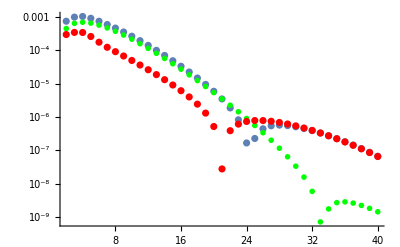

```mathematica
(* r0=12M at rmin=8M, norder = 2 *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmin]-ψ0PExactWorldtubePiece[l,m][rmin]) ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

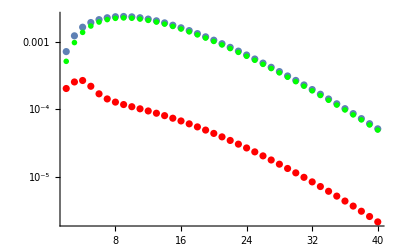

```mathematica
(* r0=12M at rmin=10M, norder = 2 *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmin]-ψ0PExactWorldtubePiece[l,m][rmin]) ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

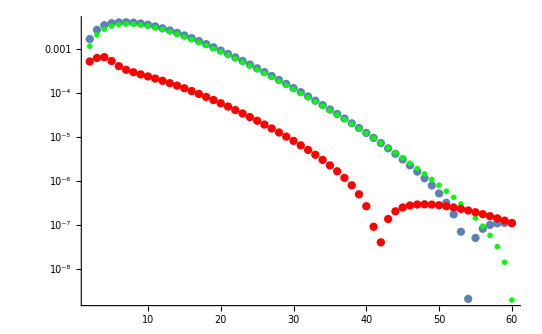

```mathematica
(* r0=10M at rmin=8M, norder = 2 *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmin]-ψ0PExactWorldtubePiece[l,m][rmin]) ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

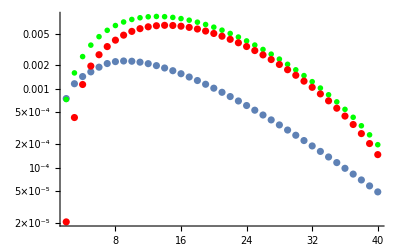

```mathematica
(* r0=12M at rmin=10M, norder = 4 *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmin]-ψ0PExactWorldtubePiece[l,m][rmin]) ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

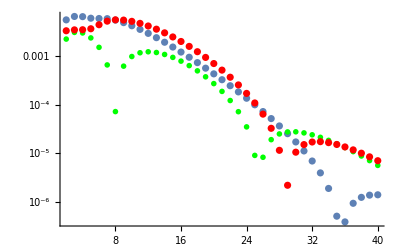

```mathematica
(* r0=8M at rmin=6M, norder = 4 *)
ψ0RetData=Table[{l,Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0PData=Table[{l,Sum[ψ0PExactWorldtubePiece[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψ0RData=Table[{l,Sum[(ψRet[l,m][rmin]-ψ0PExactWorldtubePiece[l,m][rmin]) ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
Show[
ListLogPlot[Abs@ψ0PData],
ListLogPlot[Abs@ψ0RetData,PlotStyle->Green,PlotMarkers->{"x",Large}],
ListLogPlot[Abs@ψ0RData,PlotStyle->Red],
PlotRange -> All
]
```

## Check --- large r behaviour

Computing the l=m=2 modes up to r_max+100M for the retarded field.

{{12,-0.0023116260180573323635138349366131646171983656435167074+0.000308042196020961710725885443431273615093716937480107805 ⅈ},{36,-0.001002360689092977403311596009054691594126159945539875192+0.000154868581961012351885567739315608593140059564288544519 ⅈ},{60,-0.0004907002680570066494213240237549714751658613061452377201+0.0000842566675268569391902207970755245011600270279327962043 ⅈ},{84,-0.0002629669855063274774477049032141193429339281646394825027+0.0000489019614545249024251425927669089978533376703612358842 ⅈ},{108,-0.0001511567361416256803991281971687250414958326186320185982+0.000029925743808849296979052474001362281560706932801615374 ⅈ},{132,-0.00009188314412958065995623113528338971720900884987556587078+0.0000191338189487609239495819129946484661508238977229173419 ⅈ},{156,-0.00005846095886897111988107171819723606575524918785965518235+0.000012691811932469674792633183461922733089882320024774372 ⅈ},{180,-0.00003863522088295185226968133930825753693076854254126933558+8.68565181167816628743636994461967054281949843059413617×10^-6 ⅈ},{204,-0.00002636513244576007835280705953475259378530627151334327641+6.10555661006159997823337974818194965720585876187226257×10^-6 ⅈ},{228,-0.00001849267698278893640222030423456454167161751326639834355+4.39291004326025013317228151795017273066387870270546909×10^-6 ⅈ},{252,-0.00001328284477254085691436721516829492780847220391823378124+3.22572816759369380476942464377719903516566054701122045×10^-6 ⅈ},{276,-9.741020908512400073342000975075069787071353357088714984×10^-6+2.41165506084705367180299371236471799421136194308589512×10^-6 ⅈ},{300,-7.275641272412762171892874978046249593867123980642274697×10^-6+1.8321026226280058533564610648538372563470739826800919×10^-6 ⅈ},{324,-5.523343727699922387466481835794868482054694925557836403×10^-6+1.41189641984395740707676633057089081139383839048036713×10^-6 ⅈ},{348,-4.254501671376577292836705473031850072230110237476689743×10^-6+1.10218540467195194258502031964634310440485591813313117×10^-6 ⅈ},{372,-3.320288962572678023083158094387072896602222308687682188×10^-6+8.7051053258861152390942686606383822658784524022001067×10^-7 ⅈ},{396,-2.622041804951074950344461377138700843630796459537410275×10^-6+6.94867737572012332416084247042908141612692533137754455×10^-7 ⅈ},{420,-2.093006009903289644273719662276870397758325695627690863×10^-6+5.6006706502914938261498538693415521808651376371457527×10^-7 ⅈ},{444,-1.68717690090791131662655051107615827670399970992348656×10^-6+4.55447773087461783600250567242044633148420593624220228×10^-7 ⅈ},{468,-1.372313857867495778514737544377623868213848556667160795×10^-6+3.73413978424589290773360736000945284926370014150760583×10^-7 ⅈ},{492,-1.125473762639675000889605826925726139934125872734789179×10^-6+3.08478011145761937444288082496031821485897707093327129×10^-7 ⅈ},{516,-9.300990081555896428596828090473613507358828904860663326×10^-7+2.56624369385461193552464077124517516107198061113231925×10^-7 ⅈ},{540,-7.740849147434924282207031896234243894508012064148514793×10^-7+2.1487993772917652492236912846556233425840119748402775×10^-7 ⅈ},{564,-6.484759776598702612913498376033877239930095233321509054×10^-7+1.81019212559855259352118262427342176171872511124116588×10^-7 ⅈ},{588,-5.465729506677916083596795372604065646465824074400135108×10^-7+1.53359310794033642647391369255237574447903788162278988×10^-7 ⅈ},{612,-4.633126952312605003421711008492119810617560791972497946×10^-7+1.30615573898729791080176523240938579295044426637948174×10^-7 ⅈ},{636,-3.948318461465349312174371670327834677060645416016216758×10^-7+1.11798632324583616658127074134200537852636274673260096×10^-7 ⅈ},{660,-3.381560785970689015784642155983114439371507666943223695×10^-7+9.61402026001057527002055637629970017157985775575069237×10^-8 ⅈ},{684,-2.909763131571624346806101173897759560623176541039343665×10^-7+8.30390356158289820970672421891395040785139268952128857×10^-8 ⅈ},{708,-2.514858266258350669169238042048024111660250662169458102×10^-7+7.20211564291234504753408321816938858645182322918972482×10^-8 ⅈ},{732,-2.182605156312159996416304713111197521994789644755800987×10^-7+6.27103466628520995624823827656190026976527199202519299×10^-8 ⅈ},{756,-1.901700600377254522366919724201504174643838933740969479×10^-7+5.48060403995920337357746728159603975314728060278195421×10^-8 ⅈ},{780,-1.66311433609837066023230533859132105262893661052309548×10^-7+4.80666359590910693604739779800257007233551597257395146×10^-8 ⅈ},{804,-1.459587287588613730049081001625737723873041241968851384×10^-7+4.22967990407496356539940011527009777383529108535108386×10^-8 ⅈ},{828,-1.285249967649717224825313581202129901186779390831106563×10^-7+3.733773186503817441736164247956905058561743730171289×10^-8 ⅈ},{852,-1.135330117618325687548723729850861574241054254315929493×10^-7+3.30596637119107221713356174976998782401472155942167993×10^-8 ⅈ},{876,-1.005927149259175021937512959209910445558038279253013924×10^-7+2.93560175991974185862477573548052748916155723610808541×10^-8 ⅈ},{900,-8.938369700486231350637379753048646355428082254924154229×10^-8+2.61388506401944672308776820005786421142754909481660978×10^-8 ⅈ},{924,-7.964150799748340710271948144256773912716438907894913516×10^-8+2.33352687723350554172459217621150622218871841652436962×10^-8 ⅈ},{948,-7.114689369234513892152853095848200140839773693951162577×10^-8+2.08845916618032425139171667355447052808596417558782496×10^-8 ⅈ},{972,-6.37172850122823651235034216642690613999387615172185944×10^-8+1.87360987017331701471654333692497060971454725438133054×10^-8 ⅈ},{996,-5.720003201607041220574648729227864350827184647883198753×10^-8+1.68472277536995925733962554586978962711937925344379421×10^-8 ⅈ},{1020,-5.146699695827179480920405814108179217408263360307614933×10^-8+1.51821285947281359375827845446440190870797306215136066×10^-8 ⅈ},{1044,-4.641021196592434997289854646795114202280880792827867962×10^-8+1.3710495739798462006016849615563927275880162560202826×10^-8 ⅈ},{1068,-4.193837514983470276681917577953469062656798619138194439×10^-8+1.24066224283206358051833556298427994074031639461178356×10^-8 ⅈ},{1092,-3.797401040666582195941544630536857763560764450354084755×10^-8+1.12486305462019422419170727927530163910667884926689828×10^-8 ⅈ},{1116,-3.445115516715342341164114343696962322577210287173868609×10^-8+1.02178411589857110338484899644574171763395628061617061×10^-8 ⅈ},{1140,-3.131347008648554165909771585372373920073466935100357626×10^-8+9.29825792845993256363906166003682291330157532028644146×10^-9 ⅈ},{1164,-2.851268748003869592749804435558536648882033324349247523×10^-8+8.47614154355003261574662731564599631391572671143471356×10^-9 ⅈ},{1188,-2.600733289162912125227134587752476372351842192700026862×10^-8+7.73965783720967976753614720230637824183459988739435274×10^-9 ⅈ},{1212,-2.376166780829140043355087232506436989202086823078571696×10^-8+7.07858579803189946152409346589645873389248772813905326×10^-9 ⅈ}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{A→609202.6833488795350292582200213887050239052615713405229,b→4.338647523631190159931820731268533218726482008032393953}

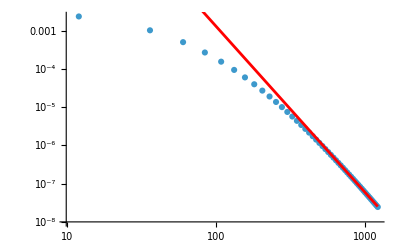

```mathematica
ψRetData=Table[{rmax+(rNumOutbd-rmax) i/50,ψRet[2,2][rmax+100 M i/50]},{i,0,50}]
paraFitRule = FindFit[Abs@ψRetData[[30;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@ψRetData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]
```

Now summing over the lm modes.
NOTE: I am not multiplying back by e^(iωr^⋆) when summing over the individual lm modes!

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -777838710809892867542459149+13608472638655575756323544384 Log[18/17].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -359153441397809881688496999485053+6283474597519250844624891718939200 Log[18/17].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -505978270577997705006134431768253+8852209790054814487010169352004544 Log[18/17].

General::stop: Further output of N::meprec will be suppressed during this calculation.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

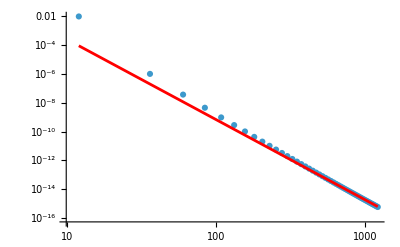

```mathematica
iRange = 50;
ψRetData=Table[{rmax+(rNumOutbd-rmax) i/iRange,Sum[ψRet[l,m][rmax+(rNumOutbd-rmax) i/iRange] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{l,Abs[Weylspin],lmax},{m,-l,l}]},{i,0,iRange}];
paraFitRule = FindFit[Abs@ψRetData[[30;;All]],A r^(-b),{A,b},r];
Show[ListLogLogPlot[Abs@ψRetData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]
```

## Hertz potential

Note: ψ_0 will by definition be invariant under sign signature. This is not the case for the Hertz potential, which will differ by a sign.
Compare for example Eq.(6) in reconstruction paper to (68a) in book chapter.
In the present case below, we will compute the Hertz potential (and thus the metric at the next step) in the (+,-,-,-) signature.

## Φ^N from Ori method

### Theory

#### The Teukolsky-Starobinsky relations

The relations are (see review paper, and Chandrasekhar, The mathematical theory of black holes),
þ^4 _-2 X_lm = C_lm/4 _2 X_lm
r^4 þ'^4 r^4 _2 X_lm = C_lm^*/4 _-2 X_lm
where C_lm=(l-1)_4+(-1)^(m+l)12 i M ω.
In the above, X stands for functions that solve the vacuum Teukolsky equation. So, can replace it with ψ or Φ. Specifically, if one is given the name “ψ”, the opposite spin one is then called “Φ”.
We can combine them to get relations that “decouple” the + and - spins.
þ^4 r^4 þ'^4 r^4 _2 X_lm = (|C_lm|^2)/16 _2 X_lm
r^4 þ'^4 r^4 (þ^4)_-2 X_lm = (|C_lm|^2)/16 _-2 X_lm
In the literature, |C_lm|^2 is called “p”.

Below, checking explicitly that the relations are satisfied.

```mathematica
(* Testing fourth-order TSIs *)
myl=3;mym=3;
Weyl$spin$p=4; Weyl$spin$q=0;
myC = Pochhammer[myl-1,4]+(-1)^(mym+myl) 12 I M ωm[mym];
Psi$sm2=TeukolskyRadial[-2,myl,mym,aKerr,ωm[mym],Method->{"NumericalIntegration","Domain"->{"In"->{rNumInbd,rNumOutbd},"Up"->{rNumInbd,rNumOutbd}}}];
Psi$s2 = TeukolskyRadial[2,myl,mym,aKerr,ωm[mym],Method->{"NumericalIntegration","Domain"->{"In"->{rNumInbd,rNumOutbd},"Up"->{rNumInbd,rNumOutbd}}}];

þNullK[þNullK[þNullK[þNullK[Cplus[-2,myl,mym] Psi$sm2["Up"][r]/ExpIωrstar[mym][r]]]]]/(myC/4 Cplus[2,myl,mym] Psi$s2["Up"][r]/ExpIωrstar[mym][r]) /. r -> rmin
r^4 þpNullK[1,-3][þpNullK[2,-2][þpNullK[3,-1][þpNullK[4,0][r^4 Cplus[2,myl,mym] Psi$s2["Up"][r]/ExpIωrstar[mym][r]]]]]/(Conjugate[myC]/4 Cplus[-2,myl,mym] Psi$sm2["Up"][r]/ExpIωrstar[mym][r]) /. r -> rmin/. m -> mym
(*Cp[myl,-mym] Cplus[2,myl,-mym]*)
```

0.99999999999999999999999999999763875408573604826207+2.7249626853643109967×10^-30 ⅈ

1.00000000000000000000000000000234043782103683187-2.723475244791509216×10^-30 ⅈ

```mathematica
(* eigth-order TSIs *)
þNullK[þNullK[þNullK[þNullK[r^4 þpNullK[Weyl$spin$p-3,Weyl$spin$q-3][þpNullK[Weyl$spin$p-2,Weyl$spin$q-2][þpNullK[Weyl$spin$p-1,Weyl$spin$q-1][þpNullK[Weyl$spin$p,Weyl$spin$q][r^4 Psi$s2["Up"][r]/ExpIωrstar[mym][r]]]]]]]]]/(Abs[myC]^2/16 Psi$s2["Up"][r]/ExpIωrstar[mym][r] ) /. r -> rmin /. m -> mym

r^4 þpNullK[-3,1][þpNullK[-2,2][þpNullK[-1,3][þpNullK[0,4][r^4 þNullK[þNullK[þNullK[þNullK[Psi$sm2["Up"][r]/ExpIωrstar[mym][r]]]]]]]]]/(Abs[myC]^2/16 Psi$sm2["Up"][r]/ExpIωrstar[mym][r] ) /. r -> rmin /. m -> mym
```

1.+0. ⅈ

1.+0. ⅈ

#### The modes

The Hertz potential equation (radial inversion formula) is: ψ_0 = 1/4 þ^4 Φ̄.
In vacuum, can use the Teukolsky-Starobinsky relations can be used on the radial inversion formula (decoupled into modes) to give
 _-2(Φ̄)_lm = 64/(|C_lm|^2)þ^4 _-2 ψ_lm
_-2(Φ̄)_lm = 64/(|C_lm|^2)r^4 þ'^4 r^4 _2 ψ_lm
In the above, (Φ̄)_lm means the modes of a complex conjugated quantity. In particular,  _-s(Φ̄)_lm := (-1)^(m+s)(_s(Φ̄)_lm)^*.
So, _s(Φ̄)_lm can be expanded into basis functions _-s ψ_lm, and  _s Φ_lm into _s ψ_lm, say the “up” basis functions for concreteness. In particular, the right-hand side of the above equations must satisfy þ^4 _-2 ψ_lm ∝ _2 ψ_lm, and r^4 þ'^4 r^4 _2 ψ_lm ∝  _-2 ψ_lm.
The proper way to find the exact coefficient is to evaluate these homogeneous functions at the horizon (or infinity depending on the basis function) and simply comparing them. Alternatively, can just guess and then check numerically “until it works”. See below.

The exact formula that you will depend 1) on the normalisation of the homogenenous solutions, 2) if m=0 or not.
For example, for non-static modes, using the “usual” normalisation from the toolkit, one can check that 
64/(|C_lm|^2)þ^4  _-2 ψ_lm^up = 4/ω^4 _2 ψ_lm^up
64/(|C_lm|^2)r^4 þ'^4 r^4 _2 ψ_lm^up = (64 ω^4)/(|C_lm|^2) _-2 ψ_lm^up
from which the modes _(±2)(Φ̄)_lm are then given analytically,
 _2(Φ̄)_lm^up = 4/ω^4 _2 ψ_lm^up
_-2(Φ̄)_lm^up = (64 ω^4)/(|C_lm|^2) _-2 ψ_lm^up
Note that for static modes, this breaks down.

For the static modes, the homogeneous solution are actually known analytically (again, up to normalisation). In the toolkit, they are given by,
ψ_l0^in = (l+s+1)_(-2s) (Γ(1+s))/(Γ(1-s)) _2 F_1(-l,l+1,1-s,1-r/(2M)), s> 0 (note that Γ(1-s) should be absorbed into F21 to regularize it into F21Regularised)
ψ_l0^in = 2^(-2s) (r/(2M)-1)^-s _2 F_1(-l,l+1,1-s,1-r/(2M)), s≤ 0,
ψ_l0^up = 2^(-s-l-1) (r/(2M)-1)^-s (r/(2M))^(-l-1)_2 F_1(l+1,l+1-s,2l+2,r/(2M))
This changes the formulae for _(±2)(Φ̄)_lm a bit. The end-result is,
 _2(Φ̄)_lm^(in/up) = (2 M^4)/((l-1)_4) _2 ψ_lm^(in/up).
For the retarded solution, one then simply multiples it with the appropriate weighting coefficient.

```mathematica
myl=5;mym=3;
Weyl$spin$p=4; Weyl$spin$q=0;
myC = Pochhammer[myl-1,4]+(-1)^(mym+myl) 12 I M ωm[mym];
C2 = Abs[myC]^2;
Weyl$spin$p=4; Weyl$spin$q=0;
Psi$sm2=TeukolskyRadial[-2,myl,mym,aKerr,ωm[mym],Method->{"NumericalIntegration","Domain"->{"In"->{rNumInbd,rNumOutbd},"Up"->{rNumInbd,rNumOutbd}}}];
Psi$s2 = TeukolskyRadial[2,myl,mym,aKerr,ωm[mym],Method->{"NumericalIntegration","Domain"->{"In"->{rNumInbd,rNumOutbd},"Up"->{rNumInbd,rNumOutbd}}}];

64/C2 r^4 þpNullK[Weyl$spin$p-3,Weyl$spin$q-3][þpNullK[Weyl$spin$p-2,Weyl$spin$q-2][þpNullK[Weyl$spin$p-1,Weyl$spin$q-1][þpNullK[Weyl$spin$p+0,Weyl$spin$q+0][r^4 Cplus[2,myl,mym] Psi$s2["Up"][r]/ExpIωrstar[mym][r]]]]]/(4 Aplus[myl,mym] Cplus[2,myl,mym] Psi$sm2["Up"][r]/ExpIωrstar[mym][r]) /. r -> rmax /. m -> mym
```

(1.836731320289411713325424504322452415211950668123×10^-9-1.04382477019063×10^-41 ⅈ)/Aplus[5,3]

```mathematica
myl=5;mym=3;
Weyl$spin$p=4; Weyl$spin$q=0;
myC = Pochhammer[myl-1,4]+(-1)^(mym+myl) 12 I M ωm[mym];
C2 = Abs[myC]^2;
Weyl$spin$p=4; Weyl$spin$q=0;
Psi$sm2=TeukolskyRadial[-2,myl,mym,aKerr,ωm[mym],Method->{"NumericalIntegration","Domain"->{"In"->{rNumInbd,rNumOutbd},"Up"->{rNumInbd,rNumOutbd}}}];
Psi$s2 = TeukolskyRadial[2,myl,mym,aKerr,ωm[mym],Method->{"NumericalIntegration","Domain"->{"In"->{rNumInbd,rNumOutbd},"Up"->{rNumInbd,rNumOutbd}}}];

64/C2 þNullK[þNullK[þNullK[þNullK[Cplus[-2,myl,mym] Psi$sm2["Up"][r]/ExpIωrstar[mym][r]]]]]/(4/ωm[mym]^4 Cplus[-2,myl,mym] Psi$s2["Up"][r]/ExpIωrstar[mym][r]) /. r -> rmax /. m -> mym
```

0.999999999999999999999999999999918324203731694922126-2.185671124392407171×10^-32 ⅈ

### Analytic (no-string) solution in terms of ψ_0^Ret

See eq (52)-(53). Note that here (Φ̄)_lm = (-1)^m Φ_(l-m)The functional form of these formulae hold independently on whether the modes are in terms of  e^-iωt or e^-iωu (in (52), just multiply each side with the  factor e^(-iωr^*) and reabsorb it in both definitions of R).
Again, need to account sign convention difference.

```mathematica
Clear[λOri,pOri,wOri,Aplus,Aminus]
λOri[l_,s_] = l (l+1)-s^2+Abs[s];

pOri[l_,m_] = With[{αOri = aKerr^2-aKerr m/ωm[m]},
(* given in eq 21 of arXiv:gr-qc/0207045https://arxiv.org/pdf/gr-qc/0207045.pdfNonehttps://arxiv.org/pdf/gr-qc/0207045.pdfHyperlinkActionRecycledHyperlinkActive *)
λOri[l,-2]^2 (λOri[l,-2]+2)^2 -8 ωm[m]^2 λOri[l,-2] (αOri^2 (5 λOri[l,-2]+6) -12 aKerr^2) + 144 ωm[m]^4 αOri^4+144 ωm[m]^2 M^2];
(* Ori has w = 4 k M r_+ with k = ω-m Ω_+  [k near eq 31 of arXiv:gr-qc/0207045https://arxiv.org/pdf/gr-qc/0207045.pdfNonehttps://arxiv.org/pdf/gr-qc/0207045.pdfHyperlinkActionRecycledHyperlinkActive and w in the paragraph above (34)] *)
wOri[m_] = 8 (ωm[m]−m aKerr/(2 (M+Sqrt[M^2-aKerr^2]))) M^2; (* is 8 here a mistake instead of 4 ? *)
Aplus[l_,m_] = 16 ωm[m]^4/pOri[l,m]; (* Ori calls this Subscript[C, out] instead of A_+ *)
Aminus[l_,m_] = 1/((wOri[m]+4 I M) (wOri[m]^2+4 M^2) wOri[m]);  (* Ori calls this Subscript[C, down] instead of A_- *)
```

```mathematica
Clear[ΨbarRetp,ΨbarRetm,ΨbarRet]
(* Subscript[((Φ̄)^+), lm] *)
ΨbarRetp[l_,m_][r_] := Piecewise[
{
{2 Aplus[l,m] ψRetSpinFlipPlus[l,m][r],m >0}, 
{2 M^4 Cplus[2,l,0] ψHomogInUp[-Weylspin][l,0]["Up"][r]/ExpIωrstar[0][r]/Pochhammer[l-1,4],m == 0},
{2 Aplus[l,m] *ψRetSpinFlipPlus[l,m][r],m <0}
},
"Never get here in ΨbarRetp"]; (* eq (52) and own calculation for m=0 case.  *)
(* Subscript[((Φ̄)^-), lm] *)
ΨbarRetm[l_,m_][r_] := Piecewise[
{
{2 Aminus[l,m] ψRetSpinFlipMinus[l,m][r],m ≠0},
{2 M^4 Cminus[2,l,0] ψHomogInUp[-Weylspin][l,0]["In"][r]/ExpIωrstar[0][r]/Pochhammer[l-1,4], m ==0},
{2 Aplus[l,m] Cplus[2,l,m]*ψRetSpinFlipMinus[l,m][r],m <0}
},
"Never get here in ΨbarRetm"];

ΨbarRet[l_,m_][r_] := Piecewise[{{ΨbarRetm[l,m][r], r<r0},{ΨbarRetp[l,m][r], r>r0}},Indeterminate]
ΨbarRet[l_,m_][Left] := ΨbarRetm[l,m][r0]
ΨbarRet[l_,m_][Right] := ΨbarRetp[l,m][r0]
```

### Numerical solution and consistency check

The below was run by computing ψ^Ret with working precision wp=64.

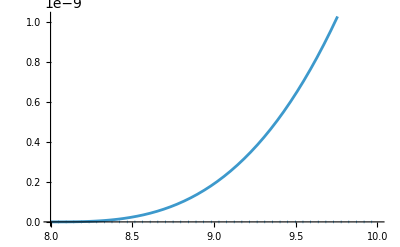

```mathematica
Clear[ΦNbarm]
ΦNbarm[ℓ_,𝓂_] :=ΦNbarm[ℓ,𝓂]= NDSolveValue[{
	RNbar[ℓ,𝓂]''''[rVar] == 2(-1)^𝓂 ψRet[ℓ,𝓂][rVar],
	RNbar[ℓ,𝓂][rmin] == ΨbarRetm[ℓ,𝓂][rmin], 
	RNbar[ℓ,𝓂]'[rmin] == ΨbarRetm[ℓ,𝓂]'[rmin],
	RNbar[ℓ,𝓂]''[rmin] == ΨbarRetm[ℓ,𝓂]''[rmin], 
	RNbar[ℓ,𝓂]'''[rmin] == ΨbarRetm[ℓ,𝓂]'''[rmin]},
	RNbar[ℓ,𝓂],{rVar,rmin,r0},WorkingPrecision->35,InterpolationOrder->All];
ReImPlot[Abs[ΦNbarm[2,2][r]-ΨbarRetm[2,2][r]],{r,rmin,r0}]
```

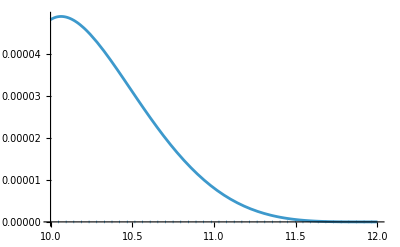

```mathematica
ΦNbarp[ℓ_,𝓂_] :=ΦNbarp[ℓ,𝓂]= NDSolveValue[{
	RNbar[ℓ,𝓂]''''[rVar] ==   2(-1)^𝓂 ψRet[ℓ,𝓂][rVar],
	RNbar[ℓ,𝓂][rmax] == ΨbarRetp[ℓ,𝓂][rmax], 
	RNbar[ℓ,𝓂]'[rmax] == ΨbarRetp[ℓ,𝓂]'[rmax],
	RNbar[ℓ,𝓂]''[rmax] == ΨbarRetp[ℓ,𝓂]''[rmax], 
	RNbar[ℓ,𝓂]'''[rmax] == ΨbarRetp[ℓ,𝓂]'''[rmax]},
	RNbar[ℓ,𝓂],{rVar,r0,rmax},WorkingPrecision->30,InterpolationOrder->All];
ReImPlot[Abs[ΦNbarp[2,2][r]-ΨbarRetp[2,2][r]],{r,r0,rmax}]
```

## Half string solutions

### Ori’s spin flip method (in BL coordinates and Kinnersley tetrad)

```mathematica
Clear[Kschw,Δschw]
Kschw[r_,m_]:=ωm[m] r^2;
Δschw[r_]:=r(r-2 M);

r0phase[m_]:= 1; (*Exp[-ⅈ ωm[m] *rstar[r0]];*)
```

```mathematica
λOri2[l_,s_]:=(l-s)(l+1+s)+s +Abs[s]
```

```mathematica
λOri[2,-2]==λOri2[2,-2]
```

True

```mathematica
(* TS stuff *)
ClearAll[Aup$Schw,Ain$Schw]
Aup$Schw[l_,m_]:= Module[{p},
p=(l-1)^2 l^2(l+1)^2(l+2)^2+144 M^2 ωm[m]^2;
Piecewise[{
{(16 ωm[m]^4)/p,m!=0},
{M^4/Pochhammer[l-1,4],m==0}}]
];
Ain$Schw[l_,m_]:= Module[{w,q,denom},
w= 8 ωm[m] M^2;
q=2 M;
denom=(w+2 ⅈ q)(w+ⅈ q)w(w-ⅈ q);
Piecewise[{
{1/denom,m>0},
{M^4/Pochhammer[l-1,4],m==0}}]
];
```

```mathematica
(* check *)
{Aplus[2,2]/ Aup$Schw[2,2],Aminus[2,2]/ Ain$Schw[2,2]}//Chop
```

{1.,1.}

```mathematica
(* Ori appendix pg 18 *)
Clear[fHat,gHat]

fHat[0][l_,m_]=r0phase[m];
fHat[1][l_,m_]=  (ⅈ Kschw[r0,m])/Δschw[r0]*r0phase[m];
fHat[2][l_,m_]=  1/(2 Δschw[r0]^2) *(
2ⅈ Kschw[r0,m]*(ⅈ Kschw[r0,m]+r0-M) + Δschw[r0](λOri[l,-2]+6 ⅈ ωm[m] r0)
) *r0phase[m];
fHat[3][l_,m_]= 1/(6 Δschw[r0]^3) *(
ⅈ Kschw[r0,m]*(
4ⅈ Kschw[r0,m]*(
ⅈ Kschw[r0,m]+r0 -M)
+(λOri[l,-2]+2 -2 ⅈ ωm[m]r0 )Δschw[r0]
)
+Δschw[r0]( 2 ⅈ Kschw[r0,m](λOri[l,-2]+6 ⅈ ωm[m] r0) + 6 ⅈ ωm[m] Δschw[r0] )
)*r0phase[m];

gHat[0][l_,m_]=0;
gHat[1][l_,m_]= r0phase[m];
gHat[2][l_,m_]= 1/Δschw[r0](ⅈ Kschw[r0,m]+r0-M)*r0phase[m];
gHat[3][l_,m_]= 1/(6 Δschw[r0]^2)*(
4ⅈ Kschw[r0,m](ⅈ Kschw[r0,m]+r0-M)+(λOri[l,-2]+2-2 ⅈ ωm[m] r0)Δschw[r0]
)*r0phase[m];
```

```mathematica
(* Ori 2002 pg 18 Appendix *)
Bhat$OriFunc[n_][l_,m_]:= Ain$Schw[l,m] Cminus[2,l,m]*( 
fHat[n][l,m]ψHomogInUp[-2][l,m]["In"][r0]
+gHat[n][l,m]*ψHomogInUp[-2][l,m]["In"]'[r0])- Aup$Schw[l,m]* Cplus[2,l,m]*
( 
fHat[n][l,m] ψHomogInUp[-2][l,m]["Up"][r0]
+gHat[n][l,m] ψHomogInUp[-2][l,m]["Up"]'[r0]
);
```

```mathematica
(* ori polynomial extending inward r<r0 in outgoing coords *)
Clear[ΨbarOriHomogMinusFunc,ΨbarhalfstringMinusFunc]
ΨbarOriHomogMinusFunc[l_,m_][r_]= (* Exp[ ⅈ ωm[m] rstar[r]]*)Sum[Bhat$OriFunc[n][l,m] r^n,{n,0,3}];
ΨbarhalfstringMinusFunc[l_,m_][r_]=ΨbarRetm[l,m][r]+ΨbarOriHomogMinusFunc[l,m][r];
```

```mathematica
(* ori polynomial extending outward  r>r0*)
Clear[ΨbarOriHomogPlusFunc,ΨbarhalfstringPlusFunc]
ΨbarOriHomogPlusFunc[l_,m_][r_]=(*Exp[ ⅈ ωm[m] rstar[r]]*) Sum[Bhat$OriFunc[n][l,m] r^n,{n,0,3}];
ΨbarhalfstringPlusFunc[l_,m_][r_]=ΨbarRetp[l,m][r]+ΨbarOriHomogPlusFunc[l,m][r];
```

```mathematica
ΨbarHalfMinus[l_,m_][r_]:=Piecewise[{
{ΨbarhalfstringMinusFunc[l,m][r],r<r0},
{ΨbarRetp[l,m][r],r>r0}
}]
ΨbarHalfPlus[l_,m_][r_]:=Piecewise[{
{ΨbarRetm[l,m][r],r<r0},
{ΨbarhalfstringPlusFunc[l,m][r],r>r0}
}]
```

```mathematica
ΨbarHalfMinus[l_,m_][r_]/;m<0:=(-1)^l Conjugate[ΨbarHalfMinus[l,-m][r]];
ΨbarHalfPlus[l_,m_][r_]/;m<0:=(-1)^l Conjugate[ΨbarHalfPlus[l,-m][r]];
```

```mathematica
{ΨbarHalfMinus[2,2][rmin],ΨbarHalfMinus[2,0][rmin],ΨbarHalfMinus[2,2][rmin]}
{ΨbarHalfMinus[2,2][rmax],ΨbarHalfMinus[2,0][rmax],ΨbarHalfMinus[2,2][rmax]}
{ΨbarHalfPlus[2,2][rmax],ΨbarHalfPlus[2,0][rmax],ΨbarHalfPlus[2,2][rmax]}
{ΨbarHalfPlus[2,2][rmin],ΨbarHalfPlus[2,0][rmin],ΨbarHalfPlus[2,2][rmin]}
```

{-15.3034-6.32581 ⅈ,19.78+0. ⅈ,-15.3034-6.32581 ⅈ}

{0.641835+2.55271 ⅈ,2.59802,0.641835+2.55271 ⅈ}

{-26.6501-12.9942 ⅈ,45.7125+0. ⅈ,-26.6501-12.9942 ⅈ}

{-1.09139+0.220418 ⅈ,1.10899,-1.09139+0.220418 ⅈ}

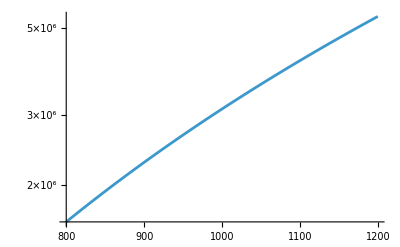

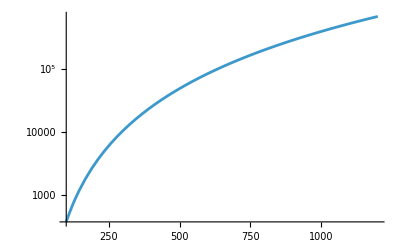

```mathematica
LogPlot[Abs@ΨbarHalfPlus[2,2][r],{r,800,1200}]
LogPlot[Abs@ΨbarHalfMinus[2,2][r],{r,100,1200}]
```

## Φ^(+,∞)large-r fits and adjustment

```mathematica
(* fit data *)
rFitMin=800;
rFitMax=1200;
rBoundary=1150;
rEval=rmax;
```

```mathematica
(* fit ψ0Ret[l,m][r] to ∑_j Subscript[a, j] r^(-Subscript[q, j])*)
Clear[fitΨpTailbase, fitΨpTail ]
fitΨpTailbase[l_,m_,rFitMin_,rFitMax_,nFit_:8,nPts_:200,p_:5,wp_:50]:=Module[
{rs,qs,mat,y,coeffs},
rs=N[Subdivide[rFitMin,rFitMax,nPts-1],wp];
qs=Range[p,p+nFit];
mat=Table[rs[[i]]^(-q),{i,Length[rs]},{q,qs}];
y=N[ΨbarRetp[l,m]/@rs,wp];
coeffs=LeastSquares[mat,y];
<|
"p"->p,"nFit"->nFit,"qs"->qs, "l"->l,"m"->m,
"coeffs"->coeffs,"aLeading"->coeffs[[1]],
"Tail"->Function[{rr},Sum[coeffs[[j]] rr^(-qs[[j]]),{j,Length[qs]}]]
|>
]


Options[fitΨpTail]={"Function"->ΨbarRetp,"FitRange"->{800,1200},"PeelingPower"->5,"NTailTerms"->10,"NumberOfFitPoints"->250,WorkingPrecision->60};

fitΨpTail[ℓ_Integer,m_Integer,opts:OptionsPattern[]]:=fitΨpTail[ℓ,m,opts]=
Module[
{func=OptionValue["Function"],
fitRange=OptionValue["FitRange"],
p=OptionValue["PeelingPower"],
nTail=OptionValue["NTailTerms"],
nPts=OptionValue["NumberOfFitPoints"],
wp=OptionValue[WorkingPrecision],
rFitMin,rFitMax,rs,qs,mat,y,coeffs},
{rFitMin,rFitMax}=SetPrecision[fitRange,wp];
rs=N[Subdivide[rFitMin,rFitMax,nPts-1],wp];
qs=Range[p,p+nTail];
mat=Table[rs[[i]]^(-q),{i,Length[rs]},{q,qs}];
y=N[func[ℓ,m]/@rs,wp];
coeffs=LeastSquares[mat,y];
<|
"l"->ℓ,"m"->m,"qs"->qs,"coeffs"->coeffs,
"FitRange"->fitRange,
"Tail"->Function[
{rr},
Sum[coeffs[[j]] rr^(-qs[[j]]),{j,Length[qs]}]
]
|>
];

ClearAll[conjugateTailFit];

conjugateTailFit[fit_Association]:=Module[{l,m,qs,coeffs},l=fit["l"];
(* note that these are just the conjugated coefficients of the positive m fits*)
(*to get the field we need to multiply by (-1)^l still *)
m=fit["m"];
qs=fit["qs"];
coeffs=Conjugate[fit["coeffs"]];
<|"l"->l,"m"->-m,"p"->fit["p"],"nFit"->fit["nFit"],"qs"->qs,"coeffs"->coeffs,"aLeading"->coeffs[[1]],"Tail"->With[{cc=coeffs,qq=qs},Function[{rr},Sum[cc[[j]] rr^(-qq[[j]]),{j,Length[qq]}]]],"GeneratedBySymmetry"->True,"ConjugateOf"->{l,m}|>];


Clear[ΨpLeadingCoeffFromFit]
ΨpLeadingCoeffFromFit[fit_Association]:=Module[{coeffs},
coeffs=Lookup[fit,"coeffs",Missing["NoCoeffs"]];
If[ListQ[coeffs]&&Length[coeffs]>=1,coeffs[[1]],Missing["NoLeadingCoeff"]]];
(* radial tail *)

ClearAll[computeΨTailData];

Options[computeΨTailData]={"LMin"->2,"NFit"->8,"NPts"->200,"LeadingPower"->5,WorkingPrecision->50,"UseParallel"->False,"Verbose"->True};

computeΨTailData[ellMax_Integer?NonNegative,rFitMin_?NumericQ,rFitMax_?NumericQ,OptionsPattern[]]:=
Module[
{
lmin,nFit,nPts,p,wp,useParallel,verbose,modes,modesToFit,nModes,allModes,worker,raw,fitAssoc,failedModes,aAssoc,coeffAssoc,fitAssocPositive,fitAssocNegative,tailAssoc,done=0,currentMode=None
},
lmin=OptionValue["LMin"];
nFit=OptionValue["NFit"];
nPts=OptionValue["NPts"];
p=OptionValue["LeadingPower"];
wp=OptionValue[WorkingPrecision];
useParallel=OptionValue["UseParallel"];
verbose=OptionValue["Verbose"];
modes=Flatten[Table[{l,m},{l,lmin,ellMax},{m,0,l}],1];
modesToFit=Flatten[Table[{l,m},{l,lmin,ellMax},{m,0,l}],1];
allModes=Flatten[Table[{l,m},{l,lmin,ellMax},{m,-l,l}],1];
nModes=Length[modesToFit];

If[verbose,Print["Fitting (Ψ̄)^+ tails for ",nModes," independent modes."];
Print["Filling negative-m modes by conjugation."];
Print["l range: ",lmin," to ",ellMax];
Print["fit range: r ∈ [",rFitMin,", ",rFitMax,"]"];
Print["powers: r^-",p," through r^-",p+nFit];];

worker[{l_,m_}]:=Module[{res},currentMode={l,m};
res=Quiet[Check[fitΨpTailbase[l,m,rFitMin,rFitMax,nFit,nPts,p,wp],$Failed]];
done++;
{l,m}->res];

raw=Monitor[Map[worker,modesToFit],Grid[{{"mode",currentMode},{"done",Row[{done," / ",nModes}]},{"progress",ProgressIndicator[done,{0,nModes}]}},Alignment->Left]];

fitAssocPositive=Association@Select[raw,Last[#]=!=$Failed&];
fitAssocNegative=Association@KeyValueMap[If[#1[[2]]>0,{#1[[1]],-#1[[2]]}->conjugateTailFit[#2],Nothing]&,fitAssocPositive];
fitAssoc=Join[fitAssocPositive,fitAssocNegative];

failedModes=Keys@Select[Association[raw],#===$Failed&];

aAssoc=Association@KeyValueMap[#1->#2["aLeading"]&,fitAssoc];
coeffAssoc=Association@KeyValueMap[#1->#2["coeffs"]&,fitAssoc];
tailAssoc=Association@KeyValueMap[#1->#2["Tail"]&,fitAssoc];

<|
"ellMax"->ellMax,"LMin"->lmin,
"rFitMin"->rFitMin,"rFitMax"->rFitMax,
"p"->p,"nFit"->nFit,"nPts"->nPts,
"WorkingPrecision"->wp,
"ModesFit"->modesToFit,"Modes"->allModes,"Fits"->fitAssoc,
"LeadingCoefficients"->aAssoc,"AllCoefficients"->coeffAssoc,
"TailFunctions"->tailAssoc,
"FailedModes"->failedModes 
|>];
```

```mathematica
ΨbarTails=computeΨTailData[3,rFitMin,rFitMax,"LMin"->2,"NFit"->8,"NPts"->200,"LeadingPower"->5,WorkingPrecision->50,"UseParallel"->True];
```

Fitting (Ψ̄)^+ tails for 7 independent modes.

Filling negative-m modes by conjugation.

l range: 2 to 3

fit range: r ∈ [800, 1200]

powers: r^-5 through r^-13

```mathematica
ΨbarTailFunc[l_,m_][r_]:=Piecewise[{
{ΨbarTails["TailFunctions"][{l,m}][r],m>=0},
{(-1)^l ΨbarTails["TailFunctions"][{l,-m}][r],m>=0}}]
```

```mathematica
ΨbarAdj[l_,m_][r_]:=Piecewise[{
{ΨbarOriHomogMinusFunc[l,m][r]-ΨbarTailFunc[l,m][r],r>r0},
{ΨbarOriHomogMinusFunc[l,m][r],r<r0}}]
```

## Φ^+ inward integration

Construct the outer (+) Hertz - potential solution by imposing asymptotic boundary data at a large but finite radius .
The retarded Weyl scalar mode ψRet[l, m][r] is assumed to be available only on a finite numerical domain, e . g . up to rDataMax .
Rather than imposing artificial zero boundary conditions at a sequence of increasingly large radii, 
we fit the large - r behaviour of ψRet to a peeling expansion ψRet[l, m] (r)~Sum[a_q r^(-q), q >= 5] .
Since in the outgoing - coordinate convention D = ∂_r the radial inversion relation is ∂_r^4\barΨ[l, m] (r) = 2 (-1)^m ψRet[l, m] (r), 
the fitted ψRet tail can be integrated analytically four times to obtain asymptotic values for\barΨ and its first three r - derivatives at a finite matching radius rBoundary inside the numerical domain . The ODE is then solved inward from rBoundary down to the requested radius rEval, typically rmax . 
This avoids evaluating ψRet outside its numerical domain and replaces the slow - converging finite - radius zero conditions with asymptotically consistent boundary data . 
   
   Main routines : 
   -FitPsi0RetTail[l, m, ...] Fits ψRet[l, m] on the specified large - r interval to a power - law tail.
  - PsiBarTailDerivsFromFit[fit, k, r] Returns the kth r - derivative of the analytically integrated Hertz potential tail at radius r .
    
- PsiBarPlusSolveOne[l, m, rEval, ...] Solves ∂_r^4\barΨ = 2 (-1)^m ψRet inward from rBoundary to rEval .
- PsiBarPlusBoundaryData[l, m, rEval, ...] Returns\barΨ, \barΨ', \barΨ'', and\barΨ''' at rEval for one mode . 
-PsiBarPlusBoundaryDataAll[rEval, lmax, ...] Computes the same boundary data for all modes 2 <= l <= lmax and - l <= m <= l . I

mportant consistency checks : 
-rEval < rBoundary < rFitMax <= rDataMax . 
-The fitted residual ψRet - ψRetTail should be small on the fit interval . 
-If ψRet still contains an oscillatory phase at large r, first demodulate by the appropriate exp (±i ω r_*) factor before fitting the power tail .

### Import data

```mathematica
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/RadialModeCache_sPlus2/psi0LargeRdata_lmax40_rOutbd1212.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/RadialHertzModeCache/SchwarzschildCircular_HertzPot_minus2_lmax30_rOutbd1200.mx"]
```

### ψ_0 asymptotic fit tools

```mathematica
(* test mode *)
Clear[ltest,mtest]
ltest=3;
mtest=2;
(* fit data *)
rFitMin=800;
rFitMax=1200;
rBoundary=1150;
rEval=rmax;
```

```mathematica
(* fit ψ0Ret[l,m][r] to ∑_j Subscript[a, j] r^(-Subscript[q, j])*)
ClearAll[fitψ0Tail,ψ0LeadingCoeffFromFit];

(* fit ψ0Ret[l,m][r] to ∑_j Subscript[a, j] r^(-Subscript[q, j])*)
fitψ0Tail[l_,m_,rFitMin_,rFitMax_,nFit_:8,nPts_:200,p_:5,wp_:50]:=Module[
{rs,qs,mat,y,coeffs},
rs=N[Subdivide[rFitMin,rFitMax,nPts-1],wp];
qs=Range[p,p+nFit];
mat=Table[rs[[i]]^(-q),{i,Length[rs]},{q,qs}];
y=N[ψRet[l,m]/@rs,wp];
coeffs=LeastSquares[mat,y];
<|
"l"->l,"m"->m,
"p"->p,"nFit"->nFit,"qs"->qs, 
"coeffs"->coeffs,"aLeading"->coeffs[[1]],
"psi0Tail"->Function[{rr},Sum[coeffs[[j]] rr^(-qs[[j]]),{j,Length[qs]}]]
|>
]


ψ0LeadingCoeffFromFit[fit_Association]:=Module[{coeffs},
coeffs=Lookup[fit,"coeffs",Missing["NoCoeffs"]];
If[ListQ[coeffs]&&Length[coeffs]>=1,coeffs[[1]],Missing["NoLeadingCoeff"]]];
```

```mathematica
Clear[PhiTailFromPsi0Fit]
PhiTailFromPsi0Fit[l_,m_,fit_]:=
Module[
{qs,a,b},
qs=fit["qs"];
a=fit["coeffs"];
b=Table[2 (-1)^m a[[j]]/Pochhammer[qs[[j]]-4,4],
{j,Length[qs]}];
Function[
{rr},
Sum[
b[[j]] rr^(-(qs[[j]]-4)),
{j,Length[qs]}
]
]
]

PhiPlusSolveAsymptotic[l_,m_,rBoundary_,rFitMin_,rFitMax_,nFit_:8,p_:5,wp_:50]:=
Module[
{fit,phiTail,rr},
fit=fitψ0Tail[l,m,rFitMin,rFitMax,nFit,200,p,wp];
phiTail=PhiTailFromPsi0Fit[l,m,fit];
NDSolveValue[
{Rplusbar''''[rVar]==2 (-1)^m ψRet[l,m][rVar],
Rplusbar[rBoundary]==phiTail[rBoundary],
Rplusbar'[rBoundary]==Evaluate[D[phiTail[rr],rr]/. rr->rBoundary],Rplusbar''[rBoundary]==Evaluate[D[phiTail[rr],{rr,2}]/. rr->rBoundary],Rplusbar'''[rBoundary]==Evaluate[D[phiTail[rr],{rr,3}]/. rr->rBoundary]},
Rplusbar,{rVar,rBoundary,rmax},
WorkingPrecision->wp,AccuracyGoal->30,PrecisionGoal->25,InterpolationOrder->All,MaxStepFraction->1/200
]
]
```

```mathematica
ClearAll[Fitpsi0RetTail,PhiBarTailDerivsFromFit, PhiBarPlusBoundaryData, PhiBarPlusBoundaryDataAll, PhiBarPlusSolveOne];

Options[Fitpsi0RetTail]={"Psi0Function"->ψRet,"FitRange"->{800,1200},"PeelingPower"->5,"NTailTerms"->10,"NumberOfFitPoints"->250,WorkingPrecision->60};

Fitpsi0RetTail[ℓ_Integer,m_Integer,opts:OptionsPattern[]]:=Fitpsi0RetTail[ℓ,m,opts]=
Module[
{psi0=OptionValue["Psi0Function"],
fitRange=OptionValue["FitRange"],
p=OptionValue["PeelingPower"],
nTail=OptionValue["NTailTerms"],
nPts=OptionValue["NumberOfFitPoints"],
wp=OptionValue[WorkingPrecision],
rFitMin,rFitMax,rs,qs,mat,y,coeffs},
{rFitMin,rFitMax}=SetPrecision[fitRange,wp];
rs=N[Subdivide[rFitMin,rFitMax,nPts-1],wp];
qs=Range[p,p+nTail];
mat=Table[rs[[i]]^(-q),{i,Length[rs]},{q,qs}];
y=N[psi0[ℓ,m]/@rs,wp];
coeffs=LeastSquares[mat,y];
<|
"l"->ℓ,"m"->m,"qs"->qs,"coeffs"->coeffs,
"FitRange"->fitRange,
"psi0Tail"->Function[
{rr},
Sum[coeffs[[j]] rr^(-qs[[j]]),{j,Length[qs]}]
]
|>
];

PhiBarTailDerivsFromFit[fit_Association,k_Integer,rr_?NumericQ]:=
Module[
{m=fit["m"],
qs=fit["qs"],
a=fit["coeffs"],n,b},
Sum[
n=qs[[j]]-4;
b=2 (-1)^m a[[j]]/Pochhammer[n,4];
b (-1)^k Pochhammer[n,k] rr^(-n-k),
{j,Length[qs]}
]
];

PhiBarTailDerivsFromFitm[fit_,m_Integer,deriv_Integer,r_?NumericQ]:=
Module[
{
qs=fit["qs"],
a=fit["coeffs"],n,b},
Sum[
n=qs[[j]]-4;
b=2 (-1)^m a[[j]]/Pochhammer[n,4];
b (-1)^k Pochhammer[n,k] rr^(-n-k),
{j,Length[qs]}
]
];
```

### ψ_0 asymptotic coefficients

```mathematica
ClearAll[conjugateψ0TailFit];

conjugateψ0TailFit[fit_Association]:=Module[{l,m,qs,coeffs},l=fit["l"];
m=fit["m"];
qs=fit["qs"];
coeffs=(-1)^l*Conjugate[fit["coeffs"]];
<|"l"->l,"m"->-m,"p"->fit["p"],"nFit"->fit["nFit"],"qs"->qs,"coeffs"->coeffs,"aLeading"->coeffs[[1]],"psi0Tail"->With[{cc=coeffs,qq=qs},Function[{rr},Sum[cc[[j]] rr^(-qq[[j]]),{j,Length[qq]}]]],"GeneratedBySymmetry"->True,"ConjugateOf"->{l,m}|>];
```

```mathematica
(* radial tail *)
ClearAll[computeψ0TailData, ψ0TailA, ψ0TailFit, ψ0TailFunction];

Options[computeψ0TailData]={"LMin"->2,"NFit"->8,"NPts"->200,"LeadingPower"->5,WorkingPrecision->50,"UseParallel"->False,"Verbose"->True};

computeψ0TailData[ellMax_Integer?NonNegative,rFitMin_?NumericQ,rFitMax_?NumericQ,OptionsPattern[]]:=
Module[
{
lmin,nFit,nPts,p,wp,useParallel,verbose,modes,modesToFit,nModes,allModes,worker,raw,fitAssoc,failedModes,aAssoc,coeffAssoc,fitAssocPositive,fitAssocNegative,tailAssoc,done=0,currentMode=None
},
lmin=OptionValue["LMin"];
nFit=OptionValue["NFit"];
nPts=OptionValue["NPts"];
p=OptionValue["LeadingPower"];
wp=OptionValue[WorkingPrecision];
useParallel=OptionValue["UseParallel"];
verbose=OptionValue["Verbose"];
modes=Flatten[Table[{l,m},{l,lmin,ellMax},{m,0,l}],1];
modesToFit=Flatten[Table[{l,m},{l,lmin,ellMax},{m,0,l}],1];
allModes=Flatten[Table[{l,m},{l,lmin,ellMax},{m,-l,l}],1];
nModes=Length[modesToFit];

If[verbose,Print["Fitting ψ0 tails for ",nModes," independent modes."];
Print["Filling negative-m modes by conjugation."];
Print["l range: ",lmin," to ",ellMax];
Print["fit range: r ∈ [",rFitMin,", ",rFitMax,"]"];
Print["powers: r^-",p," through r^-",p+nFit];];

worker[{l_,m_}]:=Module[{res},currentMode={l,m};
res=Quiet[Check[fitψ0Tail[l,m,rFitMin,rFitMax,nFit,nPts,p,wp],$Failed]];
done++;
{l,m}->res];

raw=Monitor[Map[worker,modesToFit],Grid[{{"mode",currentMode},{"done",Row[{done," / ",nModes}]},{"progress",ProgressIndicator[done,{0,nModes}]}},Alignment->Left]];

fitAssocPositive=Association@Select[raw,Last[#]=!=$Failed&];
fitAssocNegative=Association@KeyValueMap[If[#1[[2]]>0,{#1[[1]],-#1[[2]]}->conjugateψ0TailFit[#2],Nothing]&,fitAssocPositive];
fitAssoc=Join[fitAssocPositive,fitAssocNegative];

failedModes=Keys@Select[Association[raw],#===$Failed&];

aAssoc=Association@KeyValueMap[#1->#2["aLeading"]&,fitAssoc];
coeffAssoc=Association@KeyValueMap[#1->#2["coeffs"]&,fitAssoc];
tailAssoc=Association@KeyValueMap[#1->#2["psi0Tail"]&,fitAssoc];

<|
"ellMax"->ellMax,"LMin"->lmin,
"rFitMin"->rFitMin,"rFitMax"->rFitMax,
"p"->p,"nFit"->nFit,"nPts"->nPts,
"WorkingPrecision"->wp,
"ModesFit"->modesToFit,"Modes"->allModes,"Fits"->fitAssoc,
"LeadingCoefficients"->aAssoc,"AllCoefficients"->coeffAssoc,
"TailFunctions"->tailAssoc,
"FailedModes"->failedModes 
|>];

ψ0TailA[data_Association, l_Integer, m_Integer] :=
 Lookup[data["LeadingCoefficients"], {l, m}, Missing["NotComputed", {l, m}]];

ψ0TailFit[data_Association, l_Integer, m_Integer] :=
 Lookup[data["Fits"], {l, m}, Missing["NotComputed", {l, m}]];

ψ0TailFunction[data_Association, l_Integer, m_Integer] :=
 Lookup[data["TailFunctions"], {l, m}, Missing["NotComputed", {l, m}]];
```

```mathematica
ψDatalmax=30;
```

```mathematica
(*Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/RadialModeCache_sPlus2/psi0LargeRdata_lmax40_rOutbd1212.mx"]*)
```

```mathematica
(*ψ0tailData=computeψ0TailData[ψDatalmax,rFitMin,rFitMax,"LMin"->2,"NFit"->8,"NPts"->200,"LeadingPower"->5,WorkingPrecision->50,"UseParallel"->True];*)
```

Fitting ψ0 tails for 493 independent modes.

Filling negative-m modes by conjugation.

l range: 2 to 30

fit range: r ∈ [800, 1200]

powers: r^-5 through r^-13

```mathematica
(*Export["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/RadialModeCache_sPlus2/psi0LargeRdata_lmax40_rOutbd1212.wxf",ψ0tailData];*)
```

```mathematica
ψ0tailData//Keys
```

{ellMax,LMin,rFitMin,rFitMax,p,nFit,nPts,WorkingPrecision,ModesFit,Modes,Fits,LeadingCoefficients,AllCoefficients,TailFunctions,FailedModes}

```mathematica
(* RadialtailDir=FileNameJoin[{NotebookDirectory[],"RadialModeCache"}];
If[!DirectoryQ[tailDir],CreateDirectory[tailDir]];
tailFile=FileNameJoin[{tailDir,"psi0LargeRdata" <>"_lmax"<>ToString[lmax]<>"_rOutbd" <> ToString[rNumOutbd]<> ".mx"}];
DumpSave[modeFile,ψ0tailData] *)
```

### Generate Φ from pre computed tail data

```mathematica
ClearAll[PhiBarPlusSolveOneFromTailData];

Options[PhiBarPlusSolveOneFromTailData]={"Psi0Function"->ψRet,"Psi0TailData"->Automatic,"BoundaryRadius"->Automatic,"NumberOfDiagnosticPoints"->100,"RunDiagnostics"->True,WorkingPrecision->WP,AccuracyGoal->10,PrecisionGoal->8,InterpolationOrder->Automatic,MaxStepFraction->1/100};

PhiBarPlusSolveOneFromTailData[ℓ_Integer,m_Integer,rInner_?NumericQ,opts:OptionsPattern[PhiBarPlusSolveOneFromTailData]]:=Module[{psi0,psi0Mode,source,tailData,fits,fit,rBoundary,wp,acc,prec,interp,maxStepFrac,nDiagnosticPoints,runDiagnostics,rVar,y0,y1,y2,y3,boundaryData,solAll,phiBar,phiBarPrime,phiBarDoublePrime,phiBarTriplePrime,solutionDomain,sampleRs,sourceVals,residualVals,odeResidual,sourceScale,relativeODEResidual,integralResiduals,integralResidual,integralScale,relativeIntegralResidual,boundaryResiduals,diagnostics},psi0=OptionValue["Psi0Function"];
tailData=Replace[OptionValue["Psi0TailData"],Automatic:>ψ0tailData];
If[!AssociationQ[tailData]||!KeyExistsQ[tailData,"Fits"],Print["Psi0 tail data is invalid or does not contain \"Fits\"."];
Return[$Failed];];
rBoundary=Replace[OptionValue["BoundaryRadius"],Automatic:>tailData["rFitMax"]];
wp=OptionValue[WorkingPrecision];
acc=OptionValue[AccuracyGoal];
prec=OptionValue[PrecisionGoal];
interp=OptionValue[InterpolationOrder];
maxStepFrac=OptionValue[MaxStepFraction];
nDiagnosticPoints=OptionValue["NumberOfDiagnosticPoints"];
runDiagnostics=TrueQ[OptionValue["RunDiagnostics"]];
fits=tailData["Fits"];
If[!KeyExistsQ[fits,{ℓ,m}],Print["No cached fit found for mode ",{ℓ,m},"."];
Return[$Failed];];
fit=fits[{ℓ,m}];
If[!NumericQ[rBoundary],Print["Boundary radius is not numeric: ",rBoundary];
Return[$Failed];];
If[!rInner<rBoundary,Print["Need rInner < rBoundary. Received ",rInner," and ",rBoundary,"."];
Return[$Failed];];
(*Fixed mode and numerical forcing function*)psi0Mode=psi0[ℓ,m];
source[x_?NumericQ]:=2 (-1)^m psi0Mode[x];
boundaryData=Table[PhiBarTailDerivsFromFitm[fit,m,k,rBoundary]/.rr->rBoundary,{k,0,3}];
If[!And@@(NumericQ/@boundaryData),Print["Boundary data are not all numeric for mode ",{ℓ,m},": ",boundaryData];
Return[$Failed];];
solAll=NDSolveValue[{y0'[rVar]==y1[rVar],y1'[rVar]==y2[rVar],y2'[rVar]==y3[rVar],y3'[rVar]==source[rVar],y0[rBoundary]==boundaryData[[1]],y1[rBoundary]==boundaryData[[2]],y2[rBoundary]==boundaryData[[3]],y3[rBoundary]==boundaryData[[4]]}/.rr->rBoundary,{y0,y1,y2,y3},{rVar,rBoundary,rInner},WorkingPrecision->wp,AccuracyGoal->acc,PrecisionGoal->prec,InterpolationOrder->interp,MaxStepFraction->maxStepFrac];
If[solAll===$Failed||!MatchQ[solAll,{_InterpolatingFunction..}],Print["NDSolveValue failed for mode ",{ℓ,m},"."];
Return[$Failed];];
{phiBar,phiBarPrime,phiBarDoublePrime,phiBarTriplePrime}=solAll;
solutionDomain=First[phiBar["Domain"]];
boundaryResiduals={phiBar[rBoundary]-boundaryData[[1]],phiBarPrime[rBoundary]-boundaryData[[2]],phiBarDoublePrime[rBoundary]-boundaryData[[3]],phiBarTriplePrime[rBoundary]-boundaryData[[4]]};
diagnostics=
If[
runDiagnostics,sampleRs=Subdivide[Min[solutionDomain]+10^-8,Max[solutionDomain]-10^-8,nDiagnosticPoints];
sourceVals=source/@sampleRs;
residualVals=(phiBarTriplePrime'/@sampleRs)-sourceVals;
odeResidual=Max[Abs[residualVals]];
sourceScale=Max[Abs[sourceVals]];
relativeODEResidual=odeResidual/Max[10^-80,sourceScale];
integralResiduals=Table[phiBarTriplePrime[rr]-boundaryData[[4]]-NIntegrate[source[x],{x,rBoundary,rr},Method->"LocalAdaptive"],{rr,sampleRs}];
integralResidual=Max[Abs[integralResiduals]];
integralScale=Max[10^-80,Max[Abs[phiBarTriplePrime/@sampleRs]]];
relativeIntegralResidual=integralResidual/integralScale;
<|"SampleRadii"->sampleRs,"SourceValues"->sourceVals,"ODEResidualValues"->residualVals,"MaxAbsoluteODEResidual"->odeResidual,"RelativeODEResidual"->relativeODEResidual,"IntegralResidualValues"->integralResiduals,"MaxAbsoluteIntegralResidual"->integralResidual,"RelativeIntegralResidual"->relativeIntegralResidual,"BoundaryResiduals"->boundaryResiduals|>,<|"BoundaryResiduals"->boundaryResiduals|>
];
<|"Mode"->{ℓ,m},"Ell"->ℓ,"m"->m,"InnerRadius"->rInner,"BoundaryRadius"->rBoundary,"SolutionDomain"->solutionDomain,"Psi0Mode"->psi0Mode,"SourceFunction"->source,"Fit"->fit,"BoundaryData"->boundaryData,"PhiBar"->phiBar,"PhiBarPrime"->phiBarPrime,"PhiBarDoublePrime"->phiBarDoublePrime,"PhiBarTriplePrime"->phiBarTriplePrime,"Diagnostics"->diagnostics,"SolverOptions"-><|WorkingPrecision->wp,AccuracyGoal->acc,PrecisionGoal->prec,InterpolationOrder->interp,MaxStepFraction->maxStepFrac|>|>];

(*PhiBarPlusSolveOneFromTailData[ℓ_Integer,m_Integer,rInner_?NumericQ,opts:OptionsPattern[PhiBarPlusSolveOneFromTailData]]:=Module[{psi0,psi0Mode,source,tailData,fits, fit0, fit,rBoundary,wp,acc,prec,interp,maxStepFrac,Rplusbar,rVar,boundaryData, 
solAll, phiBar,phiBarPrime, phiBarDoublePrime, phiBarTriplePrime,sourceVals, residualVals,odeResidual,sourceScale,integralResiduals },psi0=OptionValue["Psi0Function"];
tailData=Replace[OptionValue["Psi0TailData"],Automatic:>ψ0tailData];
rBoundary=Replace[OptionValue["BoundaryRadius"],Automatic:>tailData["rFitMax"]];
wp=OptionValue[WorkingPrecision];
acc=OptionValue[AccuracyGoal];
prec=OptionValue[PrecisionGoal];
interp=OptionValue[InterpolationOrder];
maxStepFrac=OptionValue[MaxStepFraction];
If[!AssociationQ[tailData]||!KeyExistsQ[tailData,"Fits"]||!KeyExistsQ[tailData["Fits"],{ℓ,m}],Print["No cached tail fit found for mode ",{ℓ,m},"."];
Return[$Failed]];
fits=tailData["Fits"];
If[!KeyExistsQ[fits,{ℓ,m}],Print["No cached fit found for mode ",{ℓ,m},"."];
Return[$Failed];];
fit=fits[{ℓ,m}];
If[!rInner<rBoundary,Print["Need rInner < rBoundary. Received ",rInner," and ",rBoundary,"."];
Return[$Failed]];
(*Extract the fixed mode before entering NDSolve*)
psi0Mode=psi0[ℓ,m];
(*Numerical black-box forcing function*)
source[x_?NumericQ]:=2 (-1)^m psi0Mode[x];
boundaryData=Table[PhiBarTailDerivsFromFitm[fit,m,k,rBoundary],{k,0,3}];
solAll=NDSolveValue[{y0'[rVar]==y1[rVar],y1'[rVar]==y2[rVar],y2'[rVar]==y3[rVar],y3'[rVar]==source[rVar],y0[rBoundary]==boundaryData[[1]],y1[rBoundary]==boundaryData[[2]],y2[rBoundary]==boundaryData[[3]],y3[rBoundary]==boundaryData[[4]]},{y0,y1,y2,y3},{rVar,rBoundary,rInner},WorkingPrecision->wp,AccuracyGoal->acc,PrecisionGoal->prec,InterpolationOrder->interp,MaxStepFraction->maxStepFrac];

phiBar=solAll[[1]];
phiBarPrime=solAll[[2]];
phiBarDoublePrime=solAll[[3]];
phiBarTriplePrime=solAll[[4]];
sourceVals=2 (-1)^mtest ψRet[ltest,mtest]/@sampleRsSafe;

residualVals=phiBarTriplePrime'/@sampleRsSafe-sourceVals;

odeResidual=Max[Abs[residualVals]];

sourceScale=Max[Abs[sourceVals]];
integralResiduals=Table[phiBarTriplePrime[rr]-boundaryData[[4]]-NIntegrate[source[x],{x,rBoundary,rr},Method->"LocalAdaptive"],{rr,sampleRsSafe}];

{Max[Abs[integralResiduals]],Max[Abs[integralResiduals]]/Max[10^-80,Max[Abs[phiBarTriplePrime/@sampleRsSafe]]]}


(*NDSolveValue[{Rplusbar''''[rVar]==source[rVar],Rplusbar[rBoundary]==boundaryData[[1]],Rplusbar'[rBoundary]==boundaryData[[2]],Rplusbar''[rBoundary]==boundaryData[[3]],Rplusbar'''[rBoundary]==boundaryData[[4]]}/.rr->rBoundary,Rplusbar,{rVar,rBoundary,rInner},WorkingPrecision->wp,AccuracyGoal->acc,PrecisionGoal->prec,InterpolationOrder->interp,MaxStepFraction->maxStepFrac]];*) 
*)
```

```mathematica
phiBarPlus32=PhiBarPlusSolveOneFromTailData[ltest,mtest,rEval,"Psi0TailData"->ψ0tailData,"BoundaryRadius"->rBoundary,"RunDiagnostics"->True, WorkingPrecision->32,AccuracyGoal->10,PrecisionGoal->8];
```

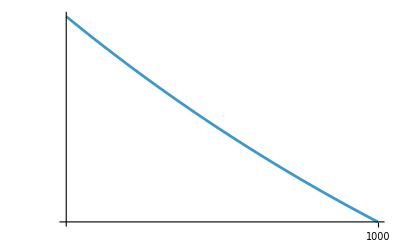

```mathematica
LogLogPlot[ r Abs@ phiBarPlus32["PhiBar"][r],{r,800,1000}]
```

```mathematica
ClearAll[ΦbarRetPlusData,ΦbarRetPlus,ΦbarRetPlusD,ΦbarRetPlusBuildAll];

Options[ΦbarRetPlusData]=Join[Options[PhiBarPlusSolveOneFromTailData],{"InnerRadius"->Automatic}];

Options[ΦbarRetPlus]=Join[Options[ΦbarRetPlusData],{"UseTailOutsideBoundary"->True}];

Options[ΦbarRetPlusD]=Options[ΦbarRetPlus];

ΦbarRetPlus::below="Requested r = `1`, but the cached outer solution only extends down to rInner = `2`.";

ΦbarRetPlus::outside="Requested r = `1` lies above the numerical inward-solve interval, and UseTailOutsideBoundary is False.";
```

```mathematica
ΦbarRetPlusData[ℓ_Integer,m_Integer,opts:OptionsPattern[]]:=ΦbarRetPlusData[ℓ,m,opts]=Module[{rInner,tailData,solveOpts,solveData},rInner=OptionValue["InnerRadius"];
If[rInner===Automatic,rInner=rmax];
tailData=Replace[OptionValue["Psi0TailData"],Automatic:>ψ0tailData];
If[!AssociationQ[tailData]||!KeyExistsQ[tailData,"Fits"]||!KeyExistsQ[tailData["Fits"],{ℓ,m}],Print["No cached ψ0 tail data found for mode ",{ℓ,m},"."];
Return[$Failed];];
solveOpts=FilterRules[{opts},Options[PhiBarPlusSolveOneFromTailData]];
solveData=PhiBarPlusSolveOneFromTailData[ℓ,m,rInner,"Psi0TailData"->tailData,Sequence@@solveOpts];
If[solveData===$Failed,Return[$Failed]];
solveData];
```

```mathematica
ΦbarRetPlus[ℓ_Integer,m_Integer,opts:OptionsPattern[]][rr_?NumericQ]:=ΦbarRetPlusD[ℓ,m,0,opts][rr];
```

```mathematica
ΦbarRetPlusD[ℓ_Integer,m_Integer,k_Integer?NonNegative,opts:OptionsPattern[]][rr_?NumericQ]:=Module[{data,fit,rInner,rBoundary,useTail,dataOpts,numericalFunctions},useTail=OptionValue["UseTailOutsideBoundary"];
dataOpts=FilterRules[{opts},Options[ΦbarRetPlusData]];
data=ΦbarRetPlusData[ℓ,m,Sequence@@dataOpts];
If[data===$Failed,Return[$Failed]];
fit=data["Fit"];
rInner=data["InnerRadius"];
rBoundary=data["BoundaryRadius"];
numericalFunctions={data["PhiBar"],data["PhiBarPrime"],data["PhiBarDoublePrime"],data["PhiBarTriplePrime"]};
Which[rr<rInner,Message[ΦbarRetPlus::below,rr,rInner];
Indeterminate,rInner<=rr<=rBoundary&&0<=k<=3,numericalFunctions[[k+1]][rr],rInner<=rr<=rBoundary&&k>=4,Derivative[k-3][data["PhiBarTriplePrime"]][rr],rr>rBoundary&&TrueQ[useTail],PhiBarTailDerivsFromFitm[fit,m,k,rr],True,Message[ΦbarRetPlus::outside,rr];
Indeterminate]];
```

```mathematica
ClearAll[ΦbarRetPlusBuildAll];

Options[ΦbarRetPlusBuildAll]=Join[Options[ΦbarRetPlusData],{"LMin"->2,"Verbose"->True}];

ΦbarRetPlusBuildAll[lmax_Integer?NonNegative,opts:OptionsPattern[ΦbarRetPlusBuildAll]]:=Module[{lmin,verbose,modes,nModes,dataOpts,done=0,currentMode=None,raw,successful,failed},lmin=OptionValue["LMin"];
verbose=TrueQ[OptionValue["Verbose"]];
If[lmax<lmin,Print["Need lmax >= LMin. Received lmax = ",lmax," and LMin = ",lmin,"."];
Return[$Failed];];
modes=Flatten[Table[{ℓ,m},{ℓ,lmin,lmax},{m,-ℓ,ℓ}],1];
nModes=Length[modes];
dataOpts=FilterRules[{opts},Options[ΦbarRetPlusData]];
If[verbose,Print["Building ",nModes," modes for ",lmin," <= l <= ",lmax,"."];];
raw=Monitor[Map[Function[mode,Module[{ell,mm,result},{ell,mm}=mode;
currentMode=mode;
result=Quiet[Check[ΦbarRetPlusData[ell,mm,Sequence@@dataOpts],$Failed]];
done++;
mode->result]],modes],Grid[{{"Current mode:",Dynamic[currentMode]},{"Completed:",Dynamic[done]," / ",nModes},{"Progress:",ProgressIndicator[Dynamic[done],{0,nModes},ImageSize->300]}},Alignment->Left]];
successful=Association@Select[raw,Last[#]=!=$Failed&];
failed=First/@Select[raw,Last[#]===$Failed&];
If[verbose,Print["Successful modes: ",Length[successful]];
Print["Failed modes: ",Length[failed]];
If[failed=!={},Print["Failed mode list: ",failed]];];
<|"LMin"->lmin,"LMax"->lmax,"ModesRequested"->modes,"NumberOfModes"->nModes,"ModeData"->successful,"FailedModes"->failed|>];
```

```mathematica
data32=ΦbarRetPlusData[3,2,"InnerRadius"->rmax,"Psi0TailData"->ψ0tailData,"BoundaryRadius"->1100,WorkingPrecision->32,AccuracyGoal->10,PrecisionGoal->8,"RunDiagnostics"->True];
```

```mathematica
Keys[data32]
```

{Mode,Ell,m,InnerRadius,BoundaryRadius,SolutionDomain,Psi0Mode,SourceFunction,Fit,BoundaryData,PhiBar,PhiBarPrime,PhiBarDoublePrime,PhiBarTriplePrime,Diagnostics,SolverOptions}

```mathematica
lmaxTest=3;
```

```mathematica
ΦbarRetPlusModestest= ΦbarRetPlusBuildAll[lmaxTest]
```

Building 12 modes for 2 <= l <= 3.

Successful modes: 12

Failed modes: 0

```mathematica
ΦbarRetPlusModesAll= ΦbarRetPlusBuildAll[30];
```

Building 957 modes for 2 <= l <= 30.

Successful modes: 957

Failed modes: 0

```mathematica
ΦbarRetPlusModesAll["ModeData"][{2,-2}]["PhiBar"]
```

InterpolatingFunction[…]

```mathematica
(*ΦmodeDir=FileNameJoin[{NotebookDirectory[],"RadialHertzModeCache"}];

If[!DirectoryQ[modeDir],CreateDirectory[ΦmodeDir]];

PhimodeFile=FileNameJoin[{
ΦmodeDir,
"SchwarzschildCircular_HertzPot_minus2"<>"_lmax"<>ToString[lmax]<>"_rOutbd" <> ToString[rNumOutbd]<> ".mx"
}
];

DumpSave["SchwarzschildCircular_HertzPot_minus2_lmax30_rOutbd1200.mx",ΦbarRetPlusModesAll];*)
```

### Generate Φ from explicit ψ_0 large-r tail calc

```mathematica
Options[PhiBarPlusSolveOne]=Join[
Options[Fitpsi0RetTail],
{"BoundaryRadius"->Automatic,
AccuracyGoal->30,
PrecisionGoal->25,
InterpolationOrder->All,
MaxStepFraction->1/300}
];

PhiBarPlusSolveOne[ℓ_Integer,m_Integer,rInner_?NumericQ,opts:OptionsPattern[]]:=
PhiBarPlusSolveOne[ℓ,m,rInner,opts]=
Module[
{
psi0=OptionValue["Psi0Function"],
fitRange=OptionValue["FitRange"],
rBoundary=OptionValue["BoundaryRadius"],
wp=OptionValue[WorkingPrecision],
acc=OptionValue[AccuracyGoal],
prec=OptionValue[PrecisionGoal],
interp=OptionValue[InterpolationOrder],
maxStepFrac=OptionValue[MaxStepFraction],
fit,Rplusbar,rVar,rFitMin,rFitMax
},
{rFitMin,rFitMax}=fitRange;
If[rBoundary===Automatic,rBoundary=rFitMax];
If[!(rInner<rBoundary),
Print["Need rInner < rBoundary for inward integration."];
Return[$Failed];];
fit=Fitpsi0RetTail[
ℓ,m,
"Psi0Function"->psi0,
"FitRange"->fitRange,
"PeelingPower"->OptionValue["PeelingPower"],
"NTailTerms"->OptionValue["NTailTerms"],
"NumberOfFitPoints"->OptionValue["NumberOfFitPoints"],
WorkingPrecision->wp
];
NDSolveValue[
{Rplusbar''''[rVar]==2 (-1)^m psi0[ℓ,m][rVar],
Rplusbar[rBoundary]==PhiBarTailDerivsFromFit[fit,0,rBoundary],
Rplusbar'[rBoundary]==PhiBarTailDerivsFromFit[fit,1,rBoundary],
Rplusbar''[rBoundary]==PhiBarTailDerivsFromFit[fit,2,rBoundary],
Rplusbar'''[rBoundary]==PhiBarTailDerivsFromFit[fit,3,rBoundary]},
Rplusbar,
{rVar,rBoundary,rInner},
WorkingPrecision->wp,AccuracyGoal->acc,PrecisionGoal->prec,InterpolationOrder->interp,MaxStepFraction->maxStepFrac
]
];



PhiBarPlusBoundaryData[ℓ_Integer,m_Integer,rEval_?NumericQ,opts:OptionsPattern[PhiBarPlusSolveOne]]:=
Module[
{sol},
sol=PhiBarPlusSolveOne[ℓ,m,rEval,opts];
If[sol===$Failed,Return[$Failed]];
<|
"l"->ℓ,"m"->m,"r"->rEval,
"ϕbar"->sol[rEval],"dϕbar"->sol'[rEval],"ddϕbar"->sol''[rEval],"dddϕbar"->sol'''[rEval],
"Solution"->sol
|>
];
PhiBarPlusBoundaryDataAll[rEval_?NumericQ,lmax_Integer,opts:OptionsPattern[PhiBarPlusSolveOne]]:=
Module[
{out=<||>},
Monitor[
Do[
out[{ℓ,m}]=PhiBarPlusBoundaryData[ℓ,m,rEval,opts];,
{ℓ,2,lmax},{m,0,ℓ}
],
{ℓ,m}
];
out];
```

```mathematica
fit32=Fitpsi0RetTail[ltest,mtest,"FitRange"->{rFitMin,rFitMax},"PeelingPower"->5,"NTailTerms"->10,"NumberOfFitPoints"->250,WorkingPrecision->60];

phiBarPlus32a=PhiBarPlusSolveOne[ltest,mtest,rEval,"FitRange"->{rFitMin,rFitMax},"BoundaryRadius"->rBoundary,"PeelingPower"->5,"NTailTerms"->6,"NumberOfFitPoints"->250,WorkingPrecision->32,AccuracyGoal->30,PrecisionGoal->25];
```

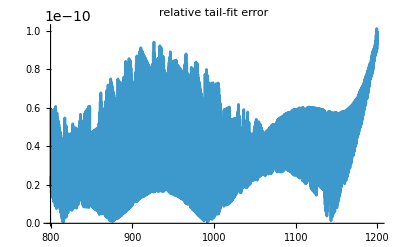

```mathematica
Plot[Evaluate[Abs[ψRet[ltest,mtest][r]-fit32["psi0Tail"][r]]/Max[10^-80,Abs[ψRet[ltest,mtest][r]]]],{r,rFitMin,rFitMax},PlotRange->All,PlotLabel->"relative tail-fit error"]
```

```mathematica
sampleRs=Subdivide[rEval+1,rBoundary-1,100];

odeResidual=Max[Abs[Table[phiBarPlus32a''''[rr]-2 (-1)^mtest ψRet[ltest,mtest][rr],{rr,sampleRs}]]];

sourceScale=Max[Abs[Table[2 (-1)^mtest ψRet[ltest,mtest][rr],{rr,sampleRs}]]];

{odeResidual,odeResidual/Max[10^-80,sourceScale]}
```

InterpolatingFunction::dmval: Input value {13} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1193/50} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {868/25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.00182147,0.999993}

```mathematica
phiDomain=First@phiBarPlus32a["Domain"];

psiInDomain=First@ψHomogInUp[Weylspin][ltest,mtest]["In"]["Domain"];

psiUpDomain=First@ψHomogInUp[Weylspin][ltest,mtest]["Up"]["Domain"];

<|"PhiBar"->phiDomain,"PsiIn"->psiInDomain,"PsiUp"->psiUpDomain,"SampleRange"->MinMax[sampleRs]|>
```

<|PhiBar→{1090.9199865578992338096202700124,1100.},PsiIn→{4.,10.},PsiUp→{10.,1212.},SampleRange→{13,1099}|>

```mathematica
{rPhiMin,rPhiMax}=Sort@phiDomain;

sampleRsSafe=Subdivide[Max[rEval+1.,rPhiMin+10^-6],Min[rBoundary-1.,rPhiMax-10^-6],100];
```

```mathematica
bdA=PhiBarPlusBoundaryData[ltest,mtest,rmax,"FitRange"->{700,1200},"BoundaryRadius"->1050,"PeelingPower"->5,"NTailTerms"->8,"NumberOfFitPoints"->250,WorkingPrecision->60];

bdB=PhiBarPlusBoundaryData[ltest,mtest,rmax,"FitRange"->{800,1200},"BoundaryRadius"->1100,"PeelingPower"->5,"NTailTerms"->10,"NumberOfFitPoints"->250,WorkingPrecision->60];

bdC=PhiBarPlusBoundaryData[ltest,mtest,rmax,"FitRange"->{850,1200},"BoundaryRadius"->1150,"PeelingPower"->5,"NTailTerms"->12,"NumberOfFitPoints"->250,WorkingPrecision->60];

Table[{key,bdA[key],bdB[key],bdC[key],Abs[bdB[key]-bdA[key]]/Max[10^-80,Abs[bdB[key]]],Abs[bdC[key]-bdB[key]]/Max[10^-80,Abs[bdC[key]]]},{key,{"ϕbar","dϕbar","ddϕbar","dddϕbar"}}]//TableForm
```

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ϕbar | -0.037677261862040624747979387432464495318781048072528780296631+0.012545020944934237788443469961000507637371482340412395588594 ⅈ | -0.036151874755114649995257150115254440552118059441842562116934+0.012107339848486083049946583672236494551586503852408250672023 ⅈ | -0.034549146951752459311356758162814187154128416073442771169139+0.011642509190089622805784684325760683097277952155455357156673 ⅈ | 0.0416241586573632362841196988264445183740182991629832590885 | 0.0457723830130431136768042032935802737816160161548549988468
dϕbar | -0.00002386637082304094962589408329324047454678297961072439885158-0.00010275326513451681044487731982393361804489031646668161207994 ⅈ | -0.00005432709538228223459771339077541713908198082075724642724351-0.000099801173328953230185000716650341542027629874690915268581679 ⅈ | -0.00008274160783326493324185171234311240976848271004158189060138-0.000096456242074593030180593095857334636638686561768813021440866 ⅈ | 0.2693260848642016966978994543834890930708412299194720417941 | 0.2251348521007090779070371586530625524730036408533779447229
ddϕbar | -0.00064733308015135260145524233482253264051765797273523879856844-0.000050916261678217465776459231024803928587067624496525895839575 ⅈ | -0.00070780237525671568118563104467067489659181933340586855374624-0.000041321183705139180595248880390867857026052552801319897802435 ⅈ | -0.00079359045261901679094285032470786499269797254211987326181879-0.000032373641262227856166247786570836181099484340009947246436726 ⅈ | 0.0863542637536322112528951658921178488728149011213261369195 | 0.10859725163690393843052411732488352304919894335147574647
dddϕbar | 0.0016452931202329445109130105567764761066630325521793159975337+0.00047824560766879981022256745708876596755305985416531798266455 ⅈ | 0.0018050219278514073620448240695088719544537994314216338576419+0.00048493829269239671528047711631769689630532440789169644411305 ⅈ | 0.0019948693811941007604142308149332574225516471164895066287987+0.00049602787778057888520972451516213500456298880353281534640392 ⅈ | 0.0855358376271270930588843164708928303900749878967631413702 | 0.0925130389530699326927472296209492353630603784085100252857

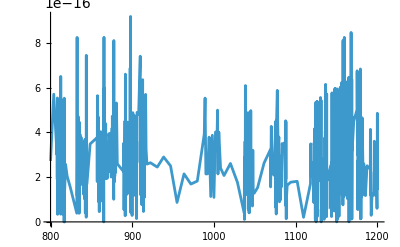

```mathematica
fitl32m21=Fitpsi0RetTail[32,21,"FitRange"->{800,1200},"PeelingPower"->5,"NTailTerms"->10,"NumberOfFitPoints"->250,WorkingPrecision->60];

Plot[Abs[ψRet[32,21][r]-fitl32m21["psi0Tail"][r]]/Max[10^-80,Abs[ψRet[32,21][r]]],{r,800,1200},PlotRange->All]
```

```mathematica
rDataMax=1200;

PhiBarPlusAtRmax=PhiBarPlusBoundaryDataAll[rmax,lmax,"FitRange"->{800,1200},"BoundaryRadius"->1100,"PeelingPower"->5,"NTailTerms"->10,"NumberOfFitPoints"->250,WorkingPrecision->60,AccuracyGoal->30,PrecisionGoal->25];

PhiBarPlusAtRmax[{3,2}]["ϕbar"]
PhiBarPlusAtRmax[{3,2}]["dϕbar"]
PhiBarPlusAtRmax[{3,2}]["ddϕbar"]
PhiBarPlusAtRmax[{3,2}]["dddϕbar"]
```

NDSolveValue::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (60.).

$Aborted

PhiBarPlusAtRmax[{3,2}][ϕbar]

PhiBarPlusAtRmax[{3,2}][dϕbar]

PhiBarPlusAtRmax[{3,2}][ddϕbar]

PhiBarPlusAtRmax[{3,2}][dddϕbar]

```mathematica
(* install as functions *)
```

```mathematica
Clear[ψbarRetpAsym]
```

```mathematica
ClearAll[ΦbarRetPlusData,ΦbarRetPlus,ΦbarRetPlusD,ΦbarRetPlusBuildAll];

Options[ΦbarRetPlusData]=Join[Options[PhiBarPlusSolveOne],{"InnerRadius"->Automatic}];

Options[ΦbarRetPlus]=Join[Options[ΦbarRetPlusData],{"UseTailOutsideBoundary"->True}];

Options[ΦbarRetPlusD]=Options[ΦbarRetPlus];

ΦbarRetPlus::below="Requested r = `1`, but the cached outer solution only extends down to rInner = `2`.";

ΦbarRetPlus::outside="Requested r = `1` is outside the numerical inward-solve interval. Returning the fitted asymptotic tail.";

ΦbarRetPlusData[ℓ_Integer,m_Integer,opts:OptionsPattern[]]:=ΦbarRetPlusData[ℓ,m,opts]=Module[{rInner=OptionValue["InnerRadius"],rBoundary=OptionValue["BoundaryRadius"],fitRange=OptionValue["FitRange"],fit,sol,fitOpts,solveOpts},If[rInner===Automatic,rInner=rmax];
If[rBoundary===Automatic,rBoundary=fitRange[[2]]];
If[!(rInner<rBoundary),Print["Need rInner < rBoundary. Got rInner = ",rInner,", rBoundary = ",rBoundary];
Return[$Failed];];
fitOpts=FilterRules[{opts},Options[Fitpsi0RetTail]];
solveOpts=FilterRules[{opts},Options[PhiBarPlusSolveOne]];
fit=Fitpsi0RetTail[ℓ,m,Sequence@@fitOpts];
sol=PhiBarPlusSolveOne[ℓ,m,rInner,Sequence@@solveOpts];
If[sol===$Failed,Return[$Failed]];
<|
"l"->ℓ,"m"->m,
"InnerRadius"->rInner,"BoundaryRadius"->rBoundary,
"FitRange"->fitRange,"Fit"->fit,
"Solution"->sol
|>
];
ΦbarRetPlus[ℓ_Integer,m_Integer,opts:OptionsPattern[]][rr_?NumericQ]:=ΦbarRetPlusD[ℓ,m,0,opts][rr];


ΦbarRetPlusD[ℓ_Integer,m_Integer,k_Integer?NonNegative,opts:OptionsPattern[]][rr_?NumericQ]:=Module[{data,sol,fit,rInner,rBoundary,useTail,dataOpts},
useTail=OptionValue["UseTailOutsideBoundary"];
dataOpts=FilterRules[{opts},Options[ΦbarRetPlusData]];
data=ΦbarRetPlusData[ℓ,m,Sequence@@dataOpts];
If[data===$Failed,Return[$Failed]];
sol=data["Solution"];
fit=data["Fit"];
rInner=data["InnerRadius"];
rBoundary=data["BoundaryRadius"];
Which[rr<rInner,Message[ΦbarRetPlus::below,rr,rInner];
Indeterminate,rr<=rBoundary,If[k==0,sol[rr],Derivative[k][sol][rr]],rr>rBoundary&&useTail,PhiBarTailDerivsFromFit[fit,k,rr],True,Message[ΦbarRetPlus::outside,rr];
Indeterminate]];
```

```mathematica
Options[ΦbarRetPlusBuildAll]=Options[ΦbarRetPlusData];

ΦbarRetPlusBuildAll[lmax_Integer,opts:OptionsPattern[]]:=Module[{dataOpts},dataOpts=FilterRules[{opts},Options[ΦbarRetPlusData]];
Monitor[
Do[
ΦbarRetPlusData[ℓ,m,Sequence@@dataOpts],
{ℓ,2,lmax},
{m,-ℓ,ℓ}],
{ℓ,m}
]
];
```

InterpolatingFunction::dmval: Input value {800.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

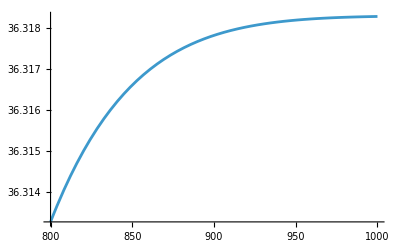

```mathematica
Plot[ r Abs@ΦbarRetPlus[2,2][r],{r,800,1000}]
```

```mathematica
ΦbarRetPlus[3,2][rmax]
```

-0.033150735883281744678605244262873137925204667946344115258521+0.011228897410746735597301746353635127529636765869478475428328 ⅈ

```mathematica
ΦbarRetPlus[3,2][rmax]
ΦbarRetPlusD[2,2,1][rmax]
ΦbarRetPlusD[3,2,2][rmax]
ΦbarRetPlusD[3,2,3][rmax]
```

-0.033150735883281744678605244262873137925204667946344115258521+0.011228897410746735597301746353635127529636765869478475428328 ⅈ

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0007738242776505760561693248083311822728559398453080215278512-0.00065902271631104561864315796141710748460419453453100203347052 ⅈ

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00082381064269253883417691488354718850784254440254933253906297-9.6681706893253780463110429410951586888018398201886034267222×10^-6 ⅈ

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.002187158043255992835095307119356596350422305650142599110337+0.00048367434627831766154419710392392834653927415689665958396043 ⅈ

```mathematica
Clear[A]
ΨRetData=Table[{rmax+(rNumOutbd-rmax) i/50,Conjugate[(-1)^2 ΦbarRetPlus[2,2][rmax+(rNumOutbd-rmax) i/50]]},{i,0,50}];
paraFitRule = FindFit[Abs@ΨRetData[[20;;All]],A r^(-b),{A,b},r]
```

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {60} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{A→32.1848,b→0.982232}

## Φ^M in WT region

See eq. (48).  Boundary conditions are eq (49a):   (∂_r^n)_-2(R̄)_lm^M = (∂_r^n)_-2(R̄)_lm^- + [(∂_r^n)_-2(R̄)_lm] at r=r_min for n=0,1,2,3.
The last term is the jump across r=r_min and can be given in terms of þ^4 Φ̄ = 2 ψ_0^Res.
For ψ_0^Res=A^o δ'(r-r_min)+B^o δ(r-r_min) + (delta functions are r_max) + smooth functions.
The A^o and B^o are independent of r! Integrating around r_min, the RHS gives: ∫_(rmin^-)^(rmin^+) ψ_0^Res(r)ⅆr = B^o, ∫_(rmin^-)^(rmin^+) (∫_(rmin^-)^r ψ_0^Res(r_1)ⅆ r_1)ⅆr = A^o. 
⇒ [þ^2 Φ̄]|_r_min=2 A^o, [þ^3 Φ̄]|_r_min=2 B^o.
At the level of the modes, _2 R_lminherits the delta functions and so [(∂_r^2)_-2(R̄)_lm]|_r_min=2 (-1)^m A_(l-m)^o, [(∂_r^3)_-2(R̄)_lm]|_r_min=2 (-1)^m B_(l-m)^o.
Then, because we are working with the residual field = retarded - puncture, A^o=-(δ' coeff of ψ^P), B^o=-(δ coeff of ψ^P).

We also use the fact that (_-2 R_(l-m) =(-1)^l(_-2 R_lm))^*, which was checked explicitly.

```mathematica
Clear[ΦMbar]
Monitor[Do[ΦMbar[ℓ,𝓂]= NDSolveValue[{
	RMbar[ℓ,𝓂]''''[r] == 2 (-1)^𝓂 ψ0RSmoothPiece[ℓ,𝓂][r],
	RMbar[ℓ,𝓂][rmax] == ΦbarRetPlusD[ℓ,𝓂,0][rmax], 
	RMbar[ℓ,𝓂]'[rmax] ==  ΦbarRetPlusD[ℓ,𝓂,1][rmax],
	RMbar[ℓ,𝓂]''[rmax] == ΦbarRetPlusD[ℓ,𝓂,2][rmax]-2 ψ0PExactδprmax[ℓ,𝓂],
	RMbar[ℓ,𝓂]'''[rmax] == ΦbarRetPlusD[ℓ,𝓂,3][rmax]-2 ψ0PExactδrmax[ℓ,𝓂]},
	RMbar[ℓ,𝓂],{r,rmax,rmin},PrecisionGoal->30,MaxStepSize->0.01,InterpolationOrder->All];
If[𝓂 != 0,ΦMbar[ℓ,-𝓂][r_] = (-1)^ℓ Conjugate[ΦMbar[ℓ,𝓂][r]]]
,{ℓ,Abs[Weylspin],3},{𝓂,0,ℓ}],
{ℓ,𝓂}] // Timing
```

{0.613146,Null}

```mathematica
ΦMbar[2,2]
```

InterpolatingFunction[…]

## Plots

### Retarded field

Checked for (l,m)=(2,1),(2,2),(3,1),(3,2) the formula for retarded potential agrees with Barry’s Hertz potential, Max error was ~ 10^-(10) with wp=40.
Note: as stated before, our Hertz potential differs from Barry’s Hertz potential by a factor of 2. (Need to add factor of 2 to our Hertz potential to agree with Barry’s).

From Table I page 8 in arXiv:1004.2276, note that in IRG, ψ_0 falls off as 1/r→Φ~r^3 .

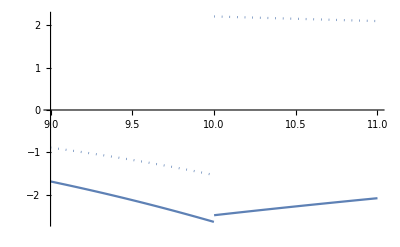

```mathematica
mylPlot=2; mymPlot=2;
ReImPlot[Conjugate[(-1)^mymPlot ΨbarRet[mylPlot,-mymPlot][r] ExpIωrstar[-mymPlot][r]],{r,r0-1,r0+1}]
```

Next three check large l-behaviour of ψ_0 and its derivatives.
On the worldline, the retarded ψ_0 converges as ℓ^-2.
ψ_0' converges as ℓ^-2.
ψ_0'’ goes like ℓ^0.
This all agrees with Barry’s results.

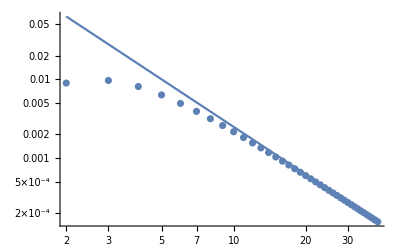

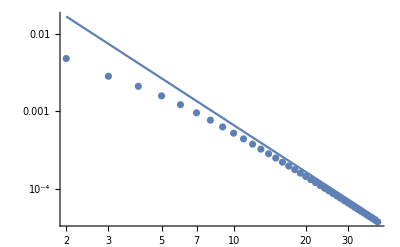

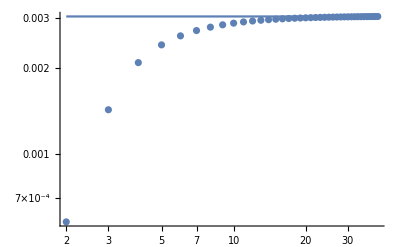

```mathematica
ΔrPlot=1/10000000000000000;
Show[ListLogLogPlot[
Abs@Table[{l,Sum[Conjugate[(-1)^m ΨbarRet[l,-m][Left] ExpIωrstar[-m][r0]]SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}]],LogLogPlot[{1/4 l^-2},{l,2,lmax}],PlotRange->All]

Show[ListLogLogPlot[
Abs@Table[{l,Sum[Conjugate[D[(-1)^m ΨbarRet[l,-m][r] ExpIωrstar[-m][r],r]]SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0] /. r -> r0-ΔrPlot,{m,-l,l}]},{l,2,lmax}]],LogLogPlot[{1/15 l^-2},{l,2,lmax}],PlotRange->All]

Show[ListLogLogPlot[
Abs@Table[{l,Sum[Conjugate[D[(-1)^m ΨbarRet[l,-m][r] ExpIωrstar[-m][r],{r,2}]]SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0] /. r -> r0-ΔrPlot,{m,-l,l}]},{l,2,lmax}]],LogLogPlot[{l^0/330},{l,2,lmax}],PlotRange->All]
```

Check large r behaviour.

{{12,0.641835-2.55271 ⅈ},{36,-11.5069+8.60814 ⅈ},{60,-75.4516+18.6927 ⅈ},{84,-220.472+18.6294 ⅈ},{108,-477.104-0.962981 ⅈ},{132,-875.993-49.4964 ⅈ},{156,-1447.81-136.39 ⅈ},{180,-2223.23-271.067 ⅈ},{204,-3232.94-462.948 ⅈ},{228,-4507.62-721.458 ⅈ},{252,-6077.95-1056.02 ⅈ},{276,-7974.63-1476.06 ⅈ},{300,-10228.3-1991. ⅈ},{324,-12869.7-2610.26 ⅈ},{348,-15929.5-3343.27 ⅈ},{372,-19438.4-4199.45 ⅈ},{396,-23427.-5188.22 ⅈ},{420,-27926.1-6319.02 ⅈ},{444,-32966.4-7601.26 ⅈ},{468,-38578.4-9044.37 ⅈ},{492,-44793.-10657.8 ⅈ},{516,-51640.7-12450.9 ⅈ},{540,-59152.3-14433.1 ⅈ},{564,-67358.5-16613.9 ⅈ},{588,-76290.-19002.8 ⅈ},{612,-85977.3-21609. ⅈ},{636,-96451.3-24442. ⅈ},{660,-107743.-27511.3 ⅈ},{684,-119882.-30826.3 ⅈ},{708,-132900.-34396.4 ⅈ},{732,-146827.-38231.1 ⅈ},{756,-161695.-42339.7 ⅈ},{780,-177533.-46731.6 ⅈ},{804,-194372.-51416.4 ⅈ},{828,-212244.-56403.4 ⅈ},{852,-231178.-61702.1 ⅈ},{876,-251206.-67321.8 ⅈ},{900,-272358.-73272. ⅈ},{924,-294665.-79562.2 ⅈ},{948,-318157.-86201.7 ⅈ},{972,-342866.-93200. ⅈ},{996,-368821.-100566. ⅈ},{1020,-396055.-108311. ⅈ},{1044,-424596.-116442. ⅈ},{1068,-454476.-124969. ⅈ},{1092,-485726.-133903. ⅈ},{1116,-518376.-143252. ⅈ},{1140,-552458.-153025. ⅈ},{1164,-588001.-163233. ⅈ},{1188,-625036.-173884. ⅈ},{1212,-663595.-184988. ⅈ}}

{A→0.000385282,b→-3.00061}

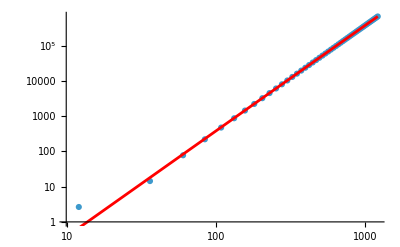

```mathematica
Clear[A,b]
ΨRetData=Table[{rmax+(rNumOutbd-rmax) i/50,Conjugate[(-1)^2 ΨbarRet[2,2][rmax+(rNumOutbd-rmax) i/50]]},{i,0,50}]
paraFitRule = FindFit[Abs@ΨRetData[[20;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@ΨRetData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]
```

```mathematica
ΨRetData=Table[{rmax+(rNumOutbd-rmax) i/50,Conjugate[(-1)^2 ΨbarC[2,2][rmax+(rNumOutbd-rmax) i/50]]},{i,0,50}]
paraFitRule = FindFit[Abs@ΨRetData[[20;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@ΨRetData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]
```

{{12,Conjugate[ΨbarC[2,2][12]]},{36,Conjugate[ΨbarC[2,2][36]]},{60,Conjugate[ΨbarC[2,2][60]]},{84,Conjugate[ΨbarC[2,2][84]]},{108,Conjugate[ΨbarC[2,2][108]]},{132,Conjugate[ΨbarC[2,2][132]]},{156,Conjugate[ΨbarC[2,2][156]]},{180,Conjugate[ΨbarC[2,2][180]]},{204,Conjugate[ΨbarC[2,2][204]]},{228,Conjugate[ΨbarC[2,2][228]]},{252,Conjugate[ΨbarC[2,2][252]]},{276,Conjugate[ΨbarC[2,2][276]]},{300,Conjugate[ΨbarC[2,2][300]]},{324,Conjugate[ΨbarC[2,2][324]]},{348,Conjugate[ΨbarC[2,2][348]]},{372,Conjugate[ΨbarC[2,2][372]]},{396,Conjugate[ΨbarC[2,2][396]]},{420,Conjugate[ΨbarC[2,2][420]]},{444,Conjugate[ΨbarC[2,2][444]]},{468,Conjugate[ΨbarC[2,2][468]]},{492,Conjugate[ΨbarC[2,2][492]]},{516,Conjugate[ΨbarC[2,2][516]]},{540,Conjugate[ΨbarC[2,2][540]]},{564,Conjugate[ΨbarC[2,2][564]]},{588,Conjugate[ΨbarC[2,2][588]]},{612,Conjugate[ΨbarC[2,2][612]]},{636,Conjugate[ΨbarC[2,2][636]]},{660,Conjugate[ΨbarC[2,2][660]]},{684,Conjugate[ΨbarC[2,2][684]]},{708,Conjugate[ΨbarC[2,2][708]]},{732,Conjugate[ΨbarC[2,2][732]]},{756,Conjugate[ΨbarC[2,2][756]]},{780,Conjugate[ΨbarC[2,2][780]]},{804,Conjugate[ΨbarC[2,2][804]]},{828,Conjugate[ΨbarC[2,2][828]]},{852,Conjugate[ΨbarC[2,2][852]]},{876,Conjugate[ΨbarC[2,2][876]]},{900,Conjugate[ΨbarC[2,2][900]]},{924,Conjugate[ΨbarC[2,2][924]]},{948,Conjugate[ΨbarC[2,2][948]]},{972,Conjugate[ΨbarC[2,2][972]]},{996,Conjugate[ΨbarC[2,2][996]]},{1020,Conjugate[ΨbarC[2,2][1020]]},{1044,Conjugate[ΨbarC[2,2][1044]]},{1068,Conjugate[ΨbarC[2,2][1068]]},{1092,Conjugate[ΨbarC[2,2][1092]]},{1116,Conjugate[ΨbarC[2,2][1116]]},{1140,Conjugate[ΨbarC[2,2][1140]]},{1164,Conjugate[ΨbarC[2,2][1164]]},{1188,Conjugate[ΨbarC[2,2][1188]]},{1212,Conjugate[ΨbarC[2,2][1212]]}}

FindFit::ivar: -1/12 xnnNDSolveRight[l,m][-1/12] is not a valid variable.

FindFit[{{468,Abs[ΨbarC[2,2][468]]},{492,Abs[ΨbarC[2,2][492]]},{516,Abs[ΨbarC[2,2][516]]},{540,Abs[ΨbarC[2,2][540]]},{564,Abs[ΨbarC[2,2][564]]},{588,Abs[ΨbarC[2,2][588]]},{612,Abs[ΨbarC[2,2][612]]},{636,Abs[ΨbarC[2,2][636]]},{660,Abs[ΨbarC[2,2][660]]},{684,Abs[ΨbarC[2,2][684]]},{708,Abs[ΨbarC[2,2][708]]},{732,Abs[ΨbarC[2,2][732]]},{756,Abs[ΨbarC[2,2][756]]},{780,Abs[ΨbarC[2,2][780]]},{804,Abs[ΨbarC[2,2][804]]},{828,Abs[ΨbarC[2,2][828]]},{852,Abs[ΨbarC[2,2][852]]},{876,Abs[ΨbarC[2,2][876]]},{900,Abs[ΨbarC[2,2][900]]},{924,Abs[ΨbarC[2,2][924]]},{948,Abs[ΨbarC[2,2][948]]},{972,Abs[ΨbarC[2,2][972]]},{996,Abs[ΨbarC[2,2][996]]},{1020,Abs[ΨbarC[2,2][1020]]},{1044,Abs[ΨbarC[2,2][1044]]},{1068,Abs[ΨbarC[2,2][1068]]},{1092,Abs[ΨbarC[2,2][1092]]},{1116,Abs[ΨbarC[2,2][1116]]},{1140,Abs[ΨbarC[2,2][1140]]},{1164,Abs[ΨbarC[2,2][1164]]},{1188,Abs[ΨbarC[2,2][1188]]},{1212,Abs[ΨbarC[2,2][1212]]}},-1/12 r^-b xnnNDSolveRight[l,m][-1/12],{-1/12 xnnNDSolveRight[l,m][-1/12],b},r]

FindFit::ivar: -1/12 xnnNDSolveRight[l,m][-1/12] is not a valid variable.

ReplaceAll::reps: {FindFit[{{468,Abs[ΨbarC[2,2][468]]},{492,Abs[ΨbarC[2,2][492]]},{516,Abs[ΨbarC[2,2][516]]},{540,Abs[ΨbarC[2,2][540]]},{564,Abs[ΨbarC[2,2][564]]},{588,Abs[ΨbarC[2,2][588]]},{612,Abs[ΨbarC[2,2][612]]},{636,Abs[ΨbarC[2,2][636]]},«16»,{1044,Abs[ΨbarC[2,2][1044]]},{1068,Abs[ΨbarC[2,2][1068]]},{1092,Abs[ΨbarC[2,2][1092]]},{1116,Abs[ΨbarC[2,2][1116]]},{1140,Abs[ΨbarC[2,2][1140]]},{1164,Abs[ΨbarC[2,2][1164]]},{1188,Abs[ΨbarC[2,2][1188]]},{1212,Abs[ΨbarC[2,2][1212]]}},«2»,12.0011]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: -0.0833333 xnnNDSolveRight[l,m][-0.0833333] is not a valid variable.

ReplaceAll::reps: {FindFit[{{468.,Abs[ΨbarC[2.,2.][468.]]},{492.,Abs[ΨbarC[2.,2.][492.]]},{516.,Abs[ΨbarC[2.,2.][516.]]},{540.,Abs[ΨbarC[2.,2.][540.]]},{564.,Abs[ΨbarC[2.,2.][564.]]},{588.,Abs[ΨbarC[2.,2.][588.]]},«20»,{1092.,Abs[ΨbarC[2.,2.][1092.]]},{1116.,Abs[ΨbarC[2.,2.][1116.]]},{1140.,Abs[ΨbarC[2.,2.][1140.]]},{1164.,Abs[ΨbarC[2.,2.][1164.]]},{1188.,Abs[ΨbarC[2.,2.][1188.]]},{1212.,Abs[ΨbarC[2.,2.][1212.]]}},«1»,{-«20» «1»,b},12.0011]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::ivar: -1/12 xnnNDSolveRight[l,m][-1/12] is not a valid variable.

General::stop: Further output of FindFit::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{468,Abs[ΨbarC[2,2][468]]},{492,Abs[ΨbarC[2,2][492]]},{516,Abs[ΨbarC[2,2][516]]},{540,Abs[ΨbarC[2,2][540]]},{564,Abs[ΨbarC[2,2][564]]},{588,Abs[ΨbarC[2,2][588]]},{612,Abs[ΨbarC[2,2][612]]},{636,Abs[ΨbarC[2,2][636]]},«16»,{1044,Abs[ΨbarC[2,2][1044]]},{1068,Abs[ΨbarC[2,2][1068]]},{1092,Abs[ΨbarC[2,2][1092]]},{1116,Abs[ΨbarC[2,2][1116]]},{1140,Abs[ΨbarC[2,2][1140]]},{1164,Abs[ΨbarC[2,2][1164]]},{1188,Abs[ΨbarC[2,2][1188]]},{1212,Abs[ΨbarC[2,2][1212]]}},«2»,13.1864]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

Now summing over the lm modes.
NOTE: I am not multiplying back by e^(iωr^⋆) when summing over the individual lm modes!

{A→0.00012253304060850505675417107062302722620370878169188165046,b→-2.9952517716365945109196811061352157067857153988324366973}

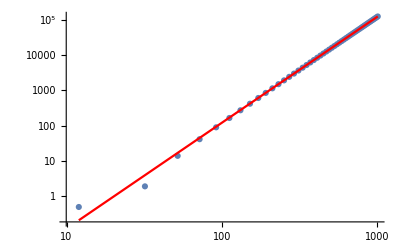

```mathematica
iRange = 50;
ΨRetData=Table[{rmax+(rNumOutbd-rmax) i/iRange,Sum[Conjugate[(-1)^m ΨbarRet[l,-m][rmax+(rNumOutbd-rmax) i/iRange]] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{l,2,lmax},{m,-l,l}]},{i,0,iRange}];
paraFitRule = FindFit[Abs@ΨRetData[[20;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@ΨRetData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]
```

### Residual field - exact puncture

```mathematica
(* It is continuous at the worldline. *)
ΔrPlot=1/10000000000000000;
Max@Abs@Table[{l,Sum[Conjugate[(-1)^m (ΦMbar[l,-m][r0-ΔrPlot]-ΦMbar[l,-m][r0+ΔrPlot]) ExpIωrstar[-m][r0]] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}][[All,2]]
```

0.

{A→5.86592×10^7,b→7.47685}

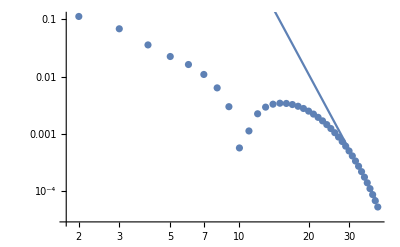

```mathematica
ΦData = Abs@Table[{l,Sum[(-1)^m Conjugate[ΦMbar[l,-m][r0-ΔrPlot] ExpIωrstar[-m][r0-ΔrPlot]] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRule = FindFit[Re[ΦData[[30;;All]]],A l^(-b),{{A,10000},{b,6}},l,MaxIterations->∞]
Show[ListLogLogPlot[ΦData],
LogLogPlot[{A l^(-b)/. paraFitRule},{l,Abs[Weylspin],lmax}]]
```

{A→0.00368381,b→0.268247}

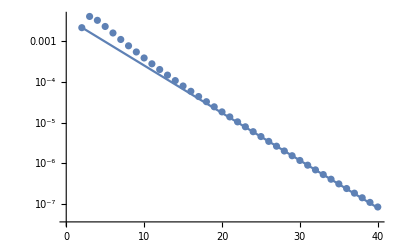

```mathematica
ΦData = Abs@Table[{l,Sum[Conjugate[(-1)^m ΦMbar[l,-m][rmin+1/10] ExpIωrstar[-m][rmin+1/10]] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRule = FindFit[Re[ΦData[[25;;All]]],A Exp[-b l],{A,{b,0.3}},l]
Show[ListLogPlot[ΦData],
LogPlot[{A Exp[-b l]/. paraFitRule},{l,Abs[Weylspin],lmax}]]
```

## Metric Reconstruction

## h_ab = 2 Re(S_ab^† Φ)

### Retarded field

h_ab = 2 Re(S_ab^† Φ) 
	 h_mm = m^a m^b(S_ab^† Φ+ (S_ab^† Φ)^*) = S_mm^† Φ + (S_(m̄ m̄)^†Φ)^* = (S_(m̄ m̄)^†Φ)^*,
	 h_nm = n^a m^b(S_ab^† Φ+ (S_ab^† Φ)^*) = S_nm^† Φ + (S_(n m̄)^†Φ)^* = (S_(n m̄)^†Φ)^*,
	h_nn = n^a n^b(S_ab^† Φ+ (S_ab^† Φ)^*) = S_nn^† Φ + (S_nn^†Φ)^*.
Note:Φ=∑_lm Φ_lm Y_lm e^-iωt → Φ̄ = ∑_lm (Φ̄)_lm Y_lm e^-iωt,where(Φ̄)_lm:= (-1)^(m-2)(Φ_(l,-m))^*.
See the relevant section (“Operators”) for the explicit expressions of S_ab^†.

```mathematica
Clear[hRetMinusmm,hRetPlusmm,hRetMinusmbmb,hRetPlusmbmb,hRetMinusnm,hRetPlusnm,hRetMinusnmb,hRetPlusnmb,hRetMinusnn,hRetPlusnn]
Clear[hRetmm,hRetmbmb,hRetnm,hRetmbmb,hRetnn,hRetll,hRetln,hRetlm,hRetlmb,hRetmmb]
hRetMinusmm[l_,m_][r_]=2 ΨbarRetm[l,m]'[r]/r-ΨbarRetm[l,m]''[r];
hRetPlusmm[l_,m_][r_]=2 ΨbarRetp[l,m]'[r]/r-ΨbarRetp[l,m]''[r];
hRetmm[l_,m_][r_] = Piecewise[{{hRetMinusmm[l,m][r],r<r0},{hRetPlusmm[l,m][r],r>r0}},Indeterminate];
hRetmm[l_,m_][Left] = hRetMinusmm[l,m][r0];
hRetmm[l_,m_][Right] = hRetPlusmm[l,m][r0];
hRetMinusmbmb[l_,m_][r_]:=(-1)^(m-2) Conjugate[hRetMinusmm[l,-m][r]];
hRetPlusmbmb[l_,m_][r_]:=(-1)^(m-2) Conjugate[hRetPlusmm[l,-m][r]];
hRetmbmb[l_,m_][r_] = Piecewise[{{hRetMinusmbmb[l,m][r],r<r0},{hRetPlusmbmb[l,m][r],r>r0}},Indeterminate];
hRetmbmb[l_,m_][Left] := hRetMinusmbmb[l,m][r0];
hRetmbmb[l_,m_][Right] := hRetPlusmbmb[l,m][r0];

hRetMinusnm[l_,m_][r_]=-Sqrt[(l-1) (l+2)](-2 ΨbarRetm[l,m][r]+r ΨbarRetm[l,m]'[r])/(Sqrt[2] r^2);
hRetPlusnm[l_,m_][r_]=-Sqrt[(l-1) (l+2)](-2 ΨbarRetp[l,m][r]+r ΨbarRetp[l,m]'[r])/(Sqrt[2] r^2);
hRetnm[l_,m_][r_] = Piecewise[{{hRetMinusnm[l,m][r],r<r0},{hRetPlusnm[l,m][r],r>r0}},Indeterminate];
hRetnm[l_,m_][Left] := hRetMinusnm[l,m][r0];
hRetnm[l_,m_][Right] := hRetPlusnm[l,m][r0];
hRetMinusnmb[l_,m_][r_]:=(-1)^(m-1) Conjugate[hRetMinusnm[l,-m][r]];
hRetPlusnmb[l_,m_][r_]:=(-1)^(m-1) Conjugate[hRetPlusnm[l,-m][r]];
hRetnmb[l_,m_][r_] = Piecewise[{{hRetMinusnmb[l,m][r],r<r0},{hRetPlusnmb[l,m][r],r>r0}},Indeterminate];
hRetnmb[l_,m_][Left] := hRetMinusnmb[l,m][r0];
hRetnmb[l_,m_][Right] := hRetPlusnmb[l,m][r0];

hRetMinusnn[l_,m_][r_]=-Sqrt[(l-1) l (l+1) (l+2)](ΨbarRetm[l,m][r]+Conjugate[(-1)^m ΨbarRetm[l,-m][r]])/(2 r^2);
hRetPlusnn[l_,m_][r_]=-Sqrt[(l-1) l (l+1) (l+2)](ΨbarRetp[l,m][r]+Conjugate[(-1)^m ΨbarRetp[l,-m][r]])/(2 r^2);
hRetnn[l_,m_][r_] = Piecewise[{{hRetMinusnn[l,m][r],r<r0},{hRetPlusnn[l,m][r],r>r0}},Indeterminate];
hRetnn[l_,m_][Left] := hRetMinusnn[l,m][r0];
hRetnn[l_,m_][Right] := hRetPlusnn[l,m][r0];

hRetll[l_,m_][r_] = 0;
hRetln[l_,m_][r_] = 0;
hRetlm[l_,m_][r_] = 0;
hRetlmb[l_,m_][r_] = 0;
hRetmmb[l_,m_][r_] = 0;
```

### Residual field

```mathematica
Clear[hRmm,hRmbmb,hRnm,hRnmb,hRnn]
hRmm[l_,m_][r_]:= 2 ΦMbar[l,m]'[r]/r-ΦMbar[l,m]''[r];
hRmbmb[l_,m_][r_]:=(-1)^(m-2) Conjugate[hRmm[l,-m][r]];

hRnm[l_,m_][r_]:=-Sqrt[(l-1) (l+2)](-2 ΦMbar[l,m][r]+r ΦMbar[l,m]'[r])/(Sqrt[2] r^2);
hRnmb[l_,m_][r_]:=(-1)^(m-1) Conjugate[hRnm[l,-m][r]];

hRnn[l_,m_][r_]:=-Sqrt[(l-1) l (l+1) (l+2)](ΦMbar[l,m][r]+Conjugate[(-1)^m ΦMbar[l,-m][r]])/(2 r^2);

hRll[l_,m_][r_] = 0;
hRln[l_,m_][r_] = 0;
hRlm[l_,m_][r_] = 0;
hRlmb[l_,m_][r_] = 0;
hRmmb[l_,m_][r_] = 0;
```

## h_uu^Ret, h_uu^P, and h_uu^Res

```mathematica
Clear[hRetuu, hPuu, hRuu]
hRetuu[l_,m_][r_] = redshift$Contribution$Formula[
hRetll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRetlm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRetlmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hRetnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRetnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRetnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hRetmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hRetmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,hRetmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
hRetuu[l_,m_][Left] = redshift$Contribution$Formula[
hRetll[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetln[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRetlm[l,m][Left] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRetlmb[l,m][Left] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hRetnn[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRetnm[l,m][Left] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRetnmb[l,m][Left] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hRetmm[l,m][Left] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hRetmmb[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,hRetmbmb[l,m][Left] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
hRetuu[l_,m_][Right] = redshift$Contribution$Formula[
hRetll[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRetln[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRetlm[l,m][Right] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRetlmb[l,m][Right] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hRetnn[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRetnm[l,m][Right] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRetnmb[l,m][Right] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hRetmm[l,m][Right] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hRetmmb[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,hRetmbmb[l,m][Right] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];

hPuu[l_,m_][Δr_] = redshift$Contribution$Formula[
hPll[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hPln[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hPlm[l,m][Δr] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hPlmb[l,m][Δr] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hPnn[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hPnm[l,m][Δr] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hPnmb[l,m][Δr] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hPmm[l,m][Δr] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hPmmb[l,m][Δr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,hPmbmb[l,m][Δr] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
hPuu[l_,m_][Left] = redshift$Contribution$Formula[
hPll[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hPln[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hPlm[l,m][Left] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hPlmb[l,m][Left] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hPnn[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hPnm[l,m][Left] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hPnmb[l,m][Left] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hPmm[l,m][Left] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hPmmb[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,hPmbmb[l,m][Left] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
hPuu[l_,m_][Right] = redshift$Contribution$Formula[
hPll[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hPln[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hPlm[l,m][Right] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hPlmb[l,m][Right] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hPnn[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hPnm[l,m][Right] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hPnmb[l,m][Right] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hPmm[l,m][Right] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hPmmb[l,m][Right] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,hPmbmb[l,m][Right] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];

hRuu[l_,m_][r_] = redshift$Contribution$Formula[
hRll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRlm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRlmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hRnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hRmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hRmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,hRmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
```

## Check --- h_ab^Recons

### Large r behaviour

Checking large-r behaviour of retarded metric reconstruction. Since in IRG Φ~r^3, we expect the metric to go overall as ~r
(need to define a norm to make this precise →  take the worst behaviour of each tetrad component).
See arXiv 1004.2276, Table I p.8 and thereabouts for more details.

{A→0.001884908108440383459170685583207953625776067727333020965,b→-1.000811999581632462216202580556213796877081737717536324}

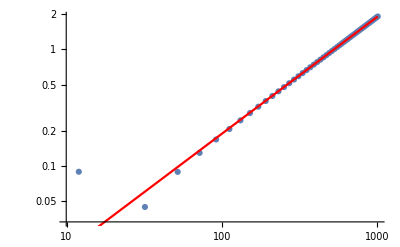

{A→0.00055699798129209457016179182319747314704499345413162713,b→-0.99756013464989986857869984746703061118294031782890992}

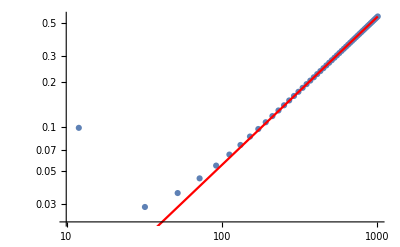

{A→0.024828047634730326397937631839667921866673972009957,b→0.0019219348089420690445867869509123911323146972730852}

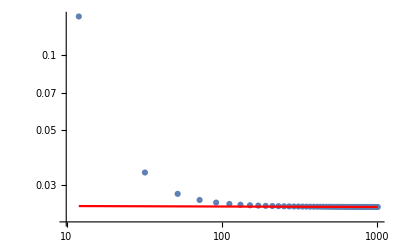

```mathematica
(* large r behaviour for Subscript[h, nn] *)
hRetnnData=Table[{rmax+(rNumOutbd-rmax) i/50,hRetnn[2,2][rmax+(rNumOutbd-rmax) i/50]},{i,0,50}];
paraFitRule = FindFit[Abs@hRetnnData[[30;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@hRetnnData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]

(* large r behaviour for Subscript[h, nm] *)
hRetnmData=Table[{rmax+(rNumOutbd-rmax) i/50,hRetnm[2,2][rmax+(rNumOutbd-rmax) i/50]},{i,0,50}];
paraFitRule = FindFit[Abs@hRetnmData[[30;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@hRetnmData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]

(* large r behaviour for Subscript[h, mm] *)
hRetmmData=Table[{rmax+(rNumOutbd-rmax) i/50,hRetmm[2,2][rmax+(rNumOutbd-rmax) i/50]},{i,0,50}];
paraFitRule = FindFit[Abs@hRetmmData[[30;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@hRetmmData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]
```

Now summing over the lm modes.
NOTE: I am not multiplying back by e^(iωr^⋆) when summing over the individual lm modes!

{A→0.001510927509047931762321470419709772756394466791295733316,b→-0.9902564912002186647018043979285759010608522207969351866}

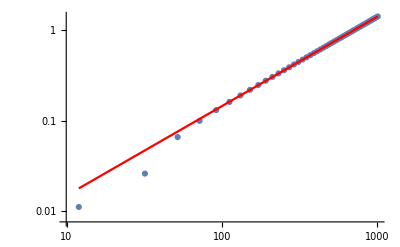

```mathematica
iRange = 50;
hRetnnData=Table[{rmax+(rNumOutbd-rmax) i/iRange,Sum[hRetnn[l,m][rmax+(rNumOutbd-rmax) i/iRange] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{l,Abs[Weylspin],lmax},{m,-l,l}]},{i,0,iRange}];
paraFitRule = FindFit[Abs@hRetnnData[[30;;All]],A r^(-b),{A,b},r]
Show[ListLogLogPlot[Abs@hRetnnData],
LogLogPlot[A r^(-b) /. paraFitRule,{r,rmax,rNumOutbd},PlotStyle->Red]]
```

### The retarded metric perturbation is discontinuous at the worldline, the discontinuity goes as l^-3, and the continuous piece goes as l^0

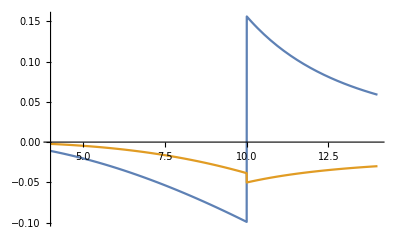

```mathematica
Plot[Evaluate[ReIm[hRetnmb[2,2][r]  ExpIωrstar[2][r]]],{r,4,14}] (* This agrees with Barry's plot. *)
```

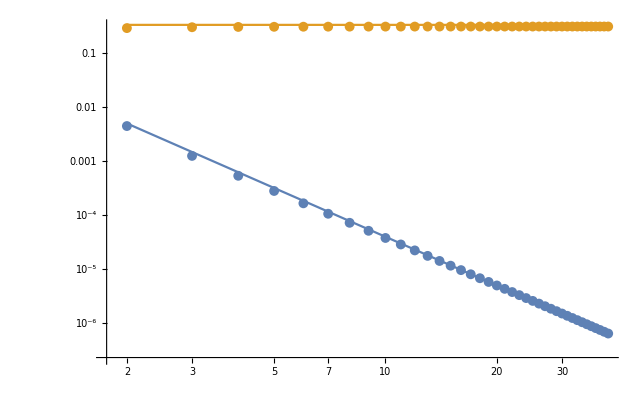

```mathematica
Show[ListLogLogPlot[Abs/@{Table[{l,Sum[(hRetnn[l,m][Left]-hRetnn[l,m][Right])SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}],Table[{l,Sum[(hRetnn[l,m][Left]+hRetnn[l,m][Right])SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}]}],
LogLogPlot[{1/25 l^-3,1/3 l^0},{l,Abs[Weylspin],lmax}]
]
```

### h_uu^(l,Recons)

#### Continuity at the particle

```mathematica
hlRetuuTableLeft = Table[{l,Sum[hRetuu[l,m][Left] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
hlRetuuTableRight = Table[{l,Sum[hRetuu[l,m][Right] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -187843855032895695284331537537+841807230935352690743158424000 Log[5/4].

General::stop: Further output of N::meprec will be suppressed during this calculation.

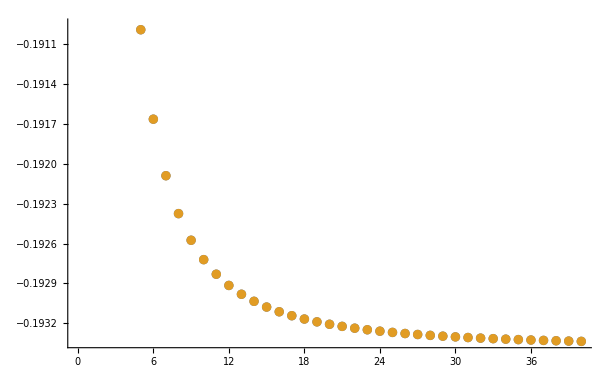

9.6539681073205476137762705×10^-30

```mathematica
ListPlot[{hlRetuuTableLeft,hlRetuuTableRight}]
Max@Abs[Transpose[hlRetuuTableLeft-hlRetuuTableRight][[2]]]
```

The below is using the released version 0.3.0:

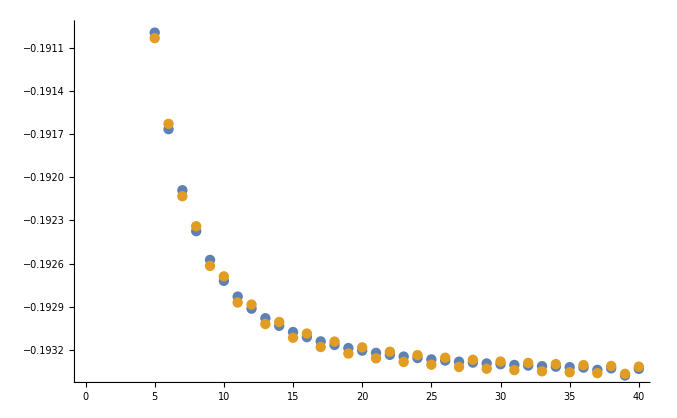

0.0000419304032110707215660081123

```mathematica
ListPlot[{hlRetuuTableLeft,hlRetuuTableRight}]
Max@Abs[Transpose[hlRetuuTableLeft-hlRetuuTableRight][[2]]]
```

#### Exact regularization parameters for 1/2 h_ab u^a u^b

These are given in the “SchwarzschildRegularizationParameters” notebook. The values are also taken from arXiv:1204.0794, page 26.
Added a minus sign to change from mostly positive to negative signature.

```mathematica
E0Energy = f[r0] utU;
L0Energy = Sqrt[r0 M] utU;

Hl[0]=(2 EllipticK[L^2/(L^2+r0^2)])/(π √(L^2+r0^2)) /. {L -> L0Energy, E0 -> E0Energy};
Hl[2]=((2 E0^2 r0^5+(L^2+r0^2) (36 L^2 M-8 L^2 r0+38 M r0^2-9 r0^3)) EllipticE[L^2/(L^2+r0^2)]+(-E0^2 r0^3 (16 L^2+17 r0^2)-2 (L^2+r0^2) (16 L^2 M-4 L^2 r0+33 M r0^2-12 r0^3)) EllipticK[L^2/(L^2+r0^2)])/((-1+2 l) (3+2 l) π r0^3 (L^2+r0^2)^(3/2)) /. {L -> L0Energy, E0 -> E0Energy};
Hl[4]=(3 ((-120 E0^4 r0^12 (8 L^4+17 L^2 r0^2+7 r0^4)+2 E0^2 r0^5 (L^2+r0^2) (3584 L^8 M+12712 L^6 M r0^2+15516 L^4 M r0^4+120 L^4 r0^5+6182 L^2 M r0^6+735 L^2 r0^7+34 M r0^8+495 r0^9)+2 (L^2+r0^2)^2 (1536 L^10 M^2+13888 L^8 M^2 r0^2-1600 L^8 M r0^3+40584 L^6 M^2 r0^4-9440 L^6 M r0^5+46888 L^4 M^2 r0^6-14100 L^4 M r0^7+120 L^4 r0^8+18936 L^2 M^2 r0^8-5350 L^2 M r0^9+15 L^2 r0^10+340 M^2 r0^10+850 M r0^11-90 r0^12)) EllipticE[L^2/(L^2+r0^2)]+(15 E0^4 r0^10 (64 L^6+224 L^4 r0^2+259 L^2 r0^4+91 r0^6)-4 E0^2 r0^7 (L^2+r0^2) (1376 L^6 M+3174 L^4 M r0^2+420 L^4 r0^3+1965 L^2 M r0^4+960 L^2 r0^5+227 M r0^6+510 r0^7)-r0^2 (L^2+r0^2)^2 (1536 L^8 M^2+15904 L^6 M^2 r0^2-7360 L^6 M r0^3+36160 L^4 M^2 r0^4-19320 L^4 M r0^5+22412 L^2 M^2 r0^6-11040 L^2 M r0^7-720 L^2 r0^8+680 M^2 r0^8+860 M r0^9-705 r0^10)) EllipticK[L^2/(L^2+r0^2)]))/(20 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0^10 (L^2+r0^2)^(7/2)) /. {L -> L0Energy, E0 -> E0Energy};
```

#### Check regularization parameters

It agrees with the mode sum regularized parameters to leading order.

```mathematica
Fit[hlRetuuTableLeft[[-5;;]],{1,1/((2l-1)(2l+3)),1/((2l-3)(2l-1)(2l+3)(2l+5)),1/((2l-5)(2l-3)(2l-1)(2l+3)(2l+5)(2l+7))(*,l^-3*)},l]
2 Hl[0]+2 Hl[2]+2 Hl[4] // N (* went to l=40 for this *)
```

0.1933797644692612756358744760246318150778361513334832-0.2907931267637731507892678422706543741405781456038779/((-1+2 l) (3+2 l))+1.155937399970968279694799034488798413180536947060754/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))-0.1600174495375736607783073940771490233794457037641932/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))

0.19338-0.125961/((-1.+2. l) (3.+2. l))+1.82557/((-3.+2. l) (-1.+2. l) (3.+2. l) (5.+2. l))

#### h_uu^(l,rec) is identical to that obtained with Lorenz gauge tensor modes

Compare against ℓ-modes computed directly in Lorenz gauge (in tensor harmonics).

```mathematica
(* Below values were given in Barry's notebook Psi4Regularization.mb, which is in mostly positive *)
LorenzHuu={{0,0.},{1,-0.06829877767625106},{2,0.18289249653441922},{3,0.18767368407943597},{4,0.18984250471129038},{5,0.19099106194004356},{6,0.19166386392804072},{7,0.1920891752778675},{8,0.19237435169110248},{9,0.19257462202689685},{10,0.19272056466031237},{11,0.1928301673561739},{12,0.19291455607972335},{13,0.19298090706769197},{14,0.1930340155088517},{15,0.1930771836065335},{16,0.19311274525676236},{17,0.19314238768908654},{18,0.19316735508126898},{19,0.19318858114531084},{20,0.19320677764235336},{21,0.19322249480183015},{22,0.193236163390895},{23,0.19324812453633539},{24,0.19325865121008937},{25,0.19326796393871723},{26,0.19327624244545025},{27,0.19328363438522636},{28,0.1932902619735783},{29,0.19329622707033228},{30,0.19330161511643262},{31,0.1933064982103185},{32,0.19331093753224998},{33,0.19331498526987315},{34,0.193318686158935},{35,0.19332207872460533},{36,0.19332519628809425},{37,0.19332806778794384},{38,0.1933307184539861},{39,0.19333317036341688},{40,0.1933354429019746},{41,0.19333755314829032},{42,0.19333951619569506},{43,0.1933413454228511},{44,0.1933430527223012},{45,0.1933446486942506},{46,0.19334614281149834},{47,0.19334754356032366},{48,0.19334885856125208},{49,0.1933500946729195},{50,0.19335125808168416},{51,0.1933523543791791},{52,0.19335338862962442},{53,0.19335436542841597},{54,0.1933552889532592},{55,0.19335616300891287},{56,0.19335699106643892},{57,0.19335777629771653},{58,0.19335852160586192},{59,0.19335922965210023},{60,0.1933599028795539}};
```

```mathematica
hlRetuuTableRight-LorenzHuu[[3;;41]]
```

{{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ},{0,0.+0. ⅈ}}

## Check --- h_uu^Recons-h_uu^P

### Large l behaviour

Recall puncture is in t slicing.

```mathematica
hlPuuTableLeft = Table[{l,Sum[hPuu[l,m][Left],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
```

Check large l behaviour of puncture and reconstructed metric.
Note: if you use too little WorkPrecision (wp), for example wp=36, you find that the l~39 mode of hRet is slightly below the one for hP.

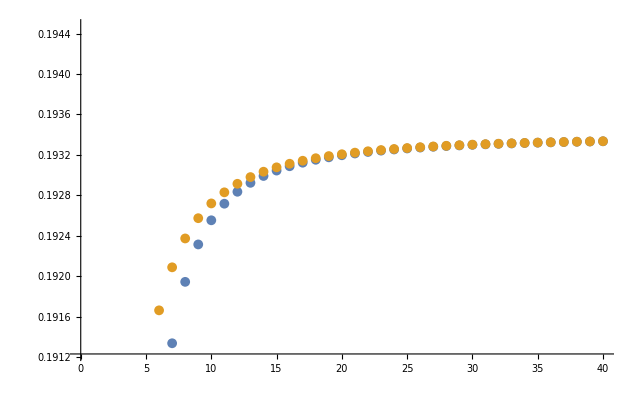

```mathematica
(* Used wp=64. *)
ListPlot[{hlPuuTableLeft,hlRetuuTableLeft}]
```

Check regularization parameters.

```mathematica
Fit[hlPuuTableLeft[[-5;;]],{1,1/((2l-1)(2l+3)),1/((2l-3)(2l-1)(2l+3)(2l+5)),1/((2l-5)(2l-3)(2l-1)(2l+3)(2l+5)(2l+7))(*,l^-3*)},l]
2 Hl[0]+2 Hl[2]+2 Hl[4] // N (* went to l=40 for this *)
```

0.19338-0.290794/((-1+2 l) (3+2 l))-26.1361/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))-1386.33/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))

2. Hl[0.]+2. Hl[2.]+2. Hl[4.]

Check large l behaviour. For the numerically computed puncture, expect decay like ~l^-4. Only the leading regularization parameter coincide with the large l behaviour of the retarded field (because to get correct regularization parameter, need to expand in scalar harmonics), so expect decay like l^-2.
Note: again, using too little Workprecision (say wp=36), the blue line will be a little wobbly at higher l.

```mathematica
hluuNogDotUsingRegPara =Quiet@Table[{l,Sum[hRetuu[l,m][Right] ExpIωrstar[m][r0],{m,-l,l}]-2 Hl[0]-2 Hl[2]-2 Hl[4]},{l,Abs[Weylspin],lmax}];
hluuNogDotUsingPuncture =Quiet@Table[{l,Sum[hRetuu[l,m][Right] ExpIωrstar[m][r0]-hPuu[l,m][Right],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
```

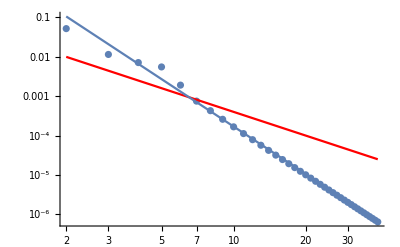

```mathematica
Show[ListLogLogPlot[Abs[hluuNogDotUsingRegPara],PlotStyle->Red],
ListLogLogPlot[Abs[hluuNogDotUsingPuncture]],
LogLogPlot[0.04 l^(-2),{l,2,lmax},PlotStyle->Red],
LogLogPlot[1.7 l^(-4),{l,2,lmax}],PlotRange -> All]
```

### Check redshift value against literature

#### Theory

The ingredients to compute the correct redshift value are the following:
1) Subtract the reconstructed retarded metric perturbation (thus in radiation gauge) from the original puncture (in Lorentz gauge).
2) In principle, these should only account for the l≥2 modes. I.e. their l=0,1 should vanish. This is true for the reconstructed retarded metric, but not true for the puncture. So, to avoid counting them, should subtract them.
3) Now, need to account for the actual l=0 and 1 modes. To the right of the particle, this is simply making sure that the asymptotic mass and spin are correct (in reconstruction, the reconstructed metric gives vanishing Abbott-Deser charges). This terms is simply (ġ)_ab, and account for the jump in the mass and spin due to the particle. On the left, one instead should subtract a certain gauge perturbation ℒ_Ξ g_ab. This is normally subtracted on the entire spacetime, but for r>r_0 it will cancel the string that comes from the reconstruction, so in the end, this term only exists for r<r_0. See this paper, section B .2 for more details (note that there, they define the vector Ξ so that the gauge perturbation is to be added up instead of subtracted). (It turns out that (ġ)_ab = -ℒ_Ξ g_ab for appropriately defined Ξ.
4) Everything is evaluated at the particle.

So, altogether, we have:

h_uu = ∑_(l≥2) (h_l^(ret,recons) - h_l^P) - ∑_(l=0,1) (h_l^P) +(ġ)_uu|_(r=r_0,θ=π/2,ϕ=Ωt), for r>r_0
h_uu = ∑_(l≥2) (h_l^(ret,recons) - h_l^P) - ∑_(l=0,1) (h_l^P) -ℒ_Ξ g_uu|_(r=r_0,θ=π/2,ϕ=Ωt), for r<r_0.

#### Evaluating at r=r_0^-

```mathematica
exacthuu = -0.21606289103798457;(* r0=10M, see Detweiler 2008 paperhttps://arxiv.org/pdf/0804.3529.pdfNonehttps://arxiv.org/pdf/0804.3529.pdfHyperlinkActionRecycledHyperlinkActive, or Table III in Appendix A in arXiv:1406.4890https://arxiv.org/pdf/1406.4890.pdfNonehttps://arxiv.org/pdf/1406.4890.pdfHyperlinkActionRecycledHyperlinkActive, where they give u^t/2 Subscript[h, uu]. *)
```

```mathematica
Clear[ℒΞguu]
ℒΞguu[l_,m_][r_]= redshift$Contribution$Formula[
ℒΞgll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
ℒΞgln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,ℒΞglm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,ℒΞglmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
ℒΞgnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,ℒΞgnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,ℒΞgnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,ℒΞgmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
ℒΞgmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,ℒΞgmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
```

```mathematica
Total[hluuNogDotUsingPuncture[[1;;]]][[2]]-Sum[ℒΞguu[l,m][r0]+hPuu[l,m][Left],{l,0,1},{m,-l,l}];
%/exacthuu-1 (* Difference between our result and the known value of the redshift. *)
```

0.0000405143+2.15769×10^-36 ⅈ

Can improve the agreement by fitting. Specifically, we can make a best fit for the power-law decay of the residual field and then sum over this fit over the full range of l.

```mathematica
lTransitionToPowerLaw = 25;
```

```mathematica
paraFitRuleForPuncture = FindFit[hluuNogDotUsingPuncture[[lTransitionToPowerLaw-1;;All]],a l^b,{a,b},l,MaxIterations->∞];
```

```mathematica
Total[hluuNogDotUsingPuncture[[1;;lTransitionToPowerLaw-2]]][[2]]+Sum[a l^b /. paraFitRuleForPuncture,{l,lTransitionToPowerLaw,∞}]-
Sum[ℒΞguu[l,m][r0]+hPuu[l,m][Left],{l,0,1},{m,-l,l}];
Abs[%/exacthuu-1] (* Difference between our result and the known value of the redshift. *)
```

7.10196×10^-8

#### Evaluating at r=r_0^+

```mathematica
exacthuu = -0.21606289103798457;(* r0=10M, see Detweiler 2008 paperhttps://arxiv.org/pdf/0804.3529.pdfNonehttps://arxiv.org/pdf/0804.3529.pdfHyperlinkActionRecycledHyperlinkActive, or Appendix A Table in arXiv:1406.4890https://arxiv.org/pdf/1406.4890.pdfNonehttps://arxiv.org/pdf/1406.4890.pdfHyperlinkActionRecycledHyperlinkActive, where they give u^t/2 Subscript[h, uu] *)
```

```mathematica
Clear[gDotuu]
gDotuu[l_,m_][r_]= redshift$Contribution$Formula[
gDotll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
gDotln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,gDotlm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,gDotlmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
gDotnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,gDotnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,gDotnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,gDotmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
gDotmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,gDotmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
```

```mathematica
Total[hluuNogDotUsingPuncture[[1;;]]][[2]]+Sum[gDotuu[l,m][r0]-hPuu[l,m][Right],{l,0,1},{m,-l,l}];
%/exacthuu-1 (* Difference between our result and the known value of the redshift. *)
```

0.000038422-1.46575×10^-35 ⅈ

Can improve the agreement by fitting. Specifically, we can make a best fit for the power-law decay of the residual field and then sum over this fit over the full range of l.

```mathematica
lTransitionToPowerLaw = 25;
```

```mathematica
paraFitRuleForPuncture = FindFit[hluuNogDotUsingPuncture[[lTransitionToPowerLaw-1;;All]],a l^b,{a,b},l];
```

```mathematica
Total[hluuNogDotUsingPuncture[[1;;lTransitionToPowerLaw-2]]][[2]]+Sum[a l^b /. paraFitRuleForPuncture,{l,lTransitionToPowerLaw,∞}]+
Sum[gDotuu[l,m][r0]-hPuu[l,m][Left],{l,0,1},{m,-l,l}];
Abs[%/exacthuu-1] (* Difference between our result and the known value of the redshift. *)
```

3.23302×10^-8

#### Redshift for different r_0

For r0 = 8M:	h_uu^CCK = -0.28099956631176215.
For r0 = 9M:	h_uu^CCK = -0.24390484067315518.
For r0 = 10M:	h_uu^CCK = -0.21606288405249827.
For r0 = 12M:	h_uu^CCK = -0.17655758923980888.
For r0 = 50M:	h_uu^CCK = -0.040419291509814985.
All the above is done using a power law fitting for l>l_max=40.

## Check --- h_ab^Res continuous at particle and large l behaviour

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -187843855032895695284331537537+841807230935352690743158424000 Log[5/4].

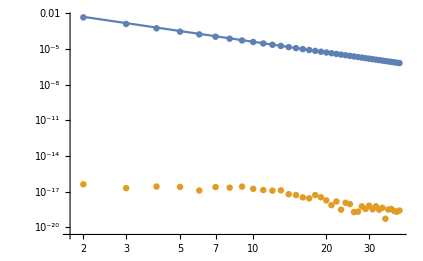

```mathematica
myΔr = 1/10000000000000000;
Show[ListLogLogPlot[Abs/@{Table[{l,Sum[(hRetnn[l,m][Left]-hRetnn[l,m][Right])SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}],Table[{l,Sum[(hRnn[l,m][r0-myΔr]-hRnn[l,m][r0+myΔr])SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}]}],
LogLogPlot[{1/25 l^-3,None,None},{l,Abs[Weylspin],lmax}]
]
```

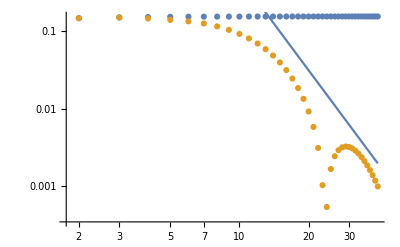

```mathematica
myΔr = 1/10000000000000000;
Show[ListLogLogPlot[Abs/@{
Table[{l,Sum[hRetnn[l,m][Left] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}],Table[{l,Sum[hRnn[l,m][r0-myΔr] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0] ExpIωrstar[m][r0],{m,-l,l}]},{l,Abs[Weylspin],lmax}]}],
LogLogPlot[{5000 l^-4,None,None},{l,Abs[Weylspin],lmax}]
]
```

## Check --- ψ_0 -> h_ab -> ψ_0

### Back to ψ_0

#### ψ_0^ret

Here, the formula is when decomposing in Fourier basis in u, instead of t.
Refer to the correct formula in the ψ_0 Puncture Field section.
Due to the reconstruction, l^a h_ab=0 and so, two terms in the formula identically vanish.

Comparing ψ^(Ret Toolkit) (given directly from toolkit), with ψ^(Ret Loop) obtained by ψ^(Ret Toolkit) -> h -> ψ^(Ret Loop).

```mathematica
Clear[hRetGroupψ, ψRetNew]
hRetGroupψ[2][l_,m_][r_]=2 r hRetmm[l,m][r] √((l+2) (l+1) l (l-1));
ψRetNew[l_,m_][r_]=-(hRetGroupψ[2][l,m]''[r])/(4 √((l+2) (l+1) l (l-1)) r);
Clear[hRetGroupψ]
```

#### ψ_0^P and ψ_0^Res= ψ_0^ret-ψ_0^P

Comparing ψ^(R Toolkit) = ψ^(Ret Toolkit) - ψ^P (the latter computed from given h^P -> ψ^P), with ψ^R = ψ^(R Loop)-ψ^P.

```mathematica
Clear[hPGroupψ]
(* hPGroupψ[1][l_,m_][r_]=(hPAnalytic[1][l,m][r-r0]+ hPAnalytic[2][l,m][r-r0])/ExpIωrstar[m][r];
hPGroupψ[2][l_,m_][r_]=(hPAnalytic[7][l,m][r-r0]-I hPAnalytic[10][l,m][r-r0])/ExpIωrstar[m][r];
hPGroupψ[3][l_,m_][r_]=(hPAnalytic[4][l,m][r-r0]+ hPAnalytic[5][l,m][r-r0]- I (hPAnalytic[8][l,m][r-r0]+ hPAnalytic[9][l,m][r-r0]))/ExpIωrstar[m][r]; *)
hPGroupψ[1][l_,m_][r_]=(hSInterpol[1][l,m][r-r0]+ hSInterpol[2][l,m][r-r0])/ExpIωrstar[m][r];
hPGroupψ[2][l_,m_][r_]=(hSInterpol[7][l,m][r-r0]-I hSInterpol[10][l,m][r-r0])/ExpIωrstar[m][r];
hPGroupψ[3][l_,m_][r_]=(hSInterpol[4][l,m][r-r0]+ hSInterpol[5][l,m][r-r0]- I (hSInterpol[8][l,m][r-r0]+ hSInterpol[9][l,m][r-r0]))/ExpIωrstar[m][r];
```

```mathematica
Clear[ψPNew, ψResFromψNew]
ψPNew[l_,m_][r_]=-(hPGroupψ[1][l,m][r] √(l (1+l)) √(-2+l+l^2))/(4 r^3 f[r]^2)-(hPGroupψ[2][l,m]''[r])/(4 √(l (-2-l+2 l^2+l^3)) r)+(√(-2+l+l^2) (-f'[r] hPGroupψ[3][l,m][r]+f[r] hPGroupψ[3][l,m]'[r]))/(4 √(l (1+l)) r^2 f[r]^2); 
ψResFromψNew[l_,m_][r_] = ψRetNew[l,m][r]- ψPNew[l,m][r];
```

#### ψ_0^Res directly

Comparing ψ^(R Toolkit) with ψ^(R Loop)= ψ^(Ret Loop)-ψ^(P Loop).

```mathematica
Clear[hResGroupψ, ψRFromhRNew]
Do[hResGroupψ[2][l,m][r_]=2 r hRmm[l,m][r] √((l+2) (l+1) l (l-1)),{l,Abs[Weylspin],lmax},{m,-l,l}];
ψRFromhRNew[l_,m_][r_]:=-(hResGroupψ[2][l,m]''[r])/(4 √((l+2) (l+1) l (l-1)) r) ;
```

### Compare

{13.9538,Null}

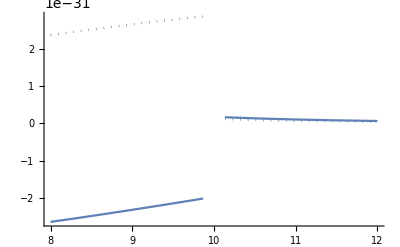

```mathematica
(* Comparing Subscript[ψ, 0]^Ret *)
Clear[rGrid,diff,diffInterpol]
rGrid = Table[rmin+i (rmax-rmin)/60,{i,0,60}];
diff = Table[{rGrid[[i]],ψRet[2,2][rGrid[[i]]]-ψRetNew[2,2][rGrid[[i]]]},{i,1,Length[rGrid]}]; // Timing
diffInterpol = Interpolation[diff];
ReImPlot[diffInterpol [r],{r,rmin,rmax}]
Clear[rGrid,diff,diffInterpol]
```

{8.2209,Null}

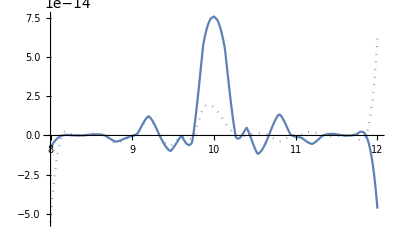

```mathematica
(* Comparing Subscript[ψ, 0]^Res *)
Clear[rGrid,diff,diffInterpol]
rGrid = DeleteElements[Table[rmin+i (rmax-rmin)/30,{i,0,30}],{r0}]; (* remove r=r0, as puncture not defined there. *)
diff = Table[{rGrid[[i]],ψ0RSmoothPiece[20,15][rGrid[[i]]]-ψResFromψNew[20,15][rGrid[[i]]]},{i,1,Length[rGrid]}]; // Timing
diffInterpol = Interpolation[diff];
ReImPlot[diffInterpol [r],{r,rmin,rmax},PlotRange->All]
```

Note: the below does not work well because to get ψ^(Res,loop) had to differentiate Φ fourth times, which gives huge junk near r=r_min.
Can however check that it is formally correct by computing  ψ_0~ h''_nn ~ Φ'''' ~ ψ_0.

{0.059058,Null}

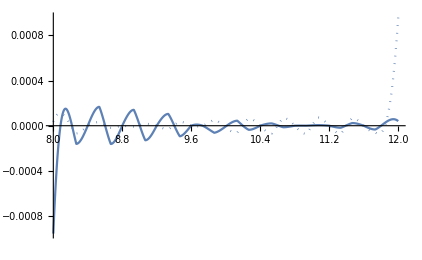

```mathematica
(* Comparing Subscript[ψ, 0]^Res *)
Clear[rGrid,diff,diffInterpol]
rGrid = DeleteElements[Table[rmin+i (rmax-rmin)/30,{i,0,30}],{r0}]; (* remove r=r0, as puncture not defined there. *)
diff = Table[{rGrid[[i]],ψ0RSmoothPiece[20,18][rGrid[[i]]]-ψRFromhRNew[20,18][rGrid[[i]]]},{i,1,Length[rGrid]}]; // Timing
diffInterpol = Interpolation[diff];
ReImPlot[diffInterpol [r],{r,rmin,rmax},PlotRange->Full]
```

## Check --- large l behaviour close and far of particle

### Individual m modes (Retarded field)

```mathematica
mmode=2;
```

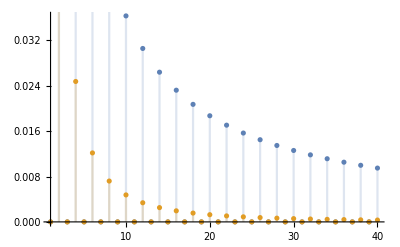

```mathematica
DiscretePlot[{Abs@Re[hRetnn[l,mmode][Left] ExpIωrstar[mmode][r0]],Abs@Im[hRetnn[l,mmode][Left] ExpIωrstar[mmode][r0]]},{l,1,lmax}] (* other tetrad indices similar *)
```

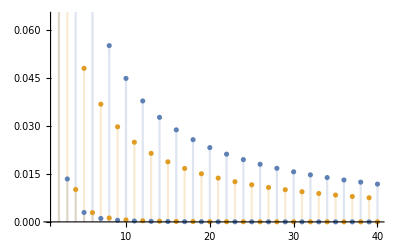

```mathematica
DiscretePlot[{Abs@Re[hRetmm[l,mmode][Right] ExpIωrstar[mmode][r0]],Abs@Im[hRetmm[l,mmode][Right] ExpIωrstar[mmode][r0]]},{l,1,lmax}]
```

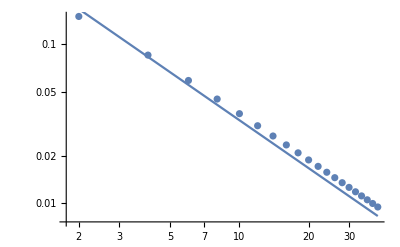

```mathematica
data = Table[{l,Abs[hRetnn[l,mmode][Left] ExpIωrstar[mmode][r0]]},{l,Abs@Weylspin,lmax}];
Show[ListLogLogPlot[data],
LogLogPlot[ l^(-1)/3,{l,Abs@Weylspin,lmax}]]
```

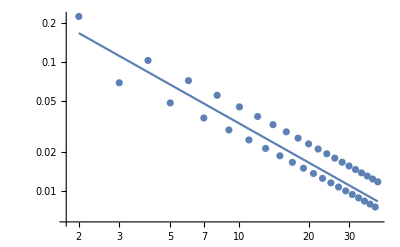

```mathematica
data = Table[{l,Abs[hRetmm[l,mmode][Right] ExpIωrstar[mmode][r0]]},{l,Abs@Weylspin,lmax}];
Show[ListLogLogPlot[data],
LogLogPlot[ l^(-1)/3,{l,Abs@Weylspin,lmax}]]
```

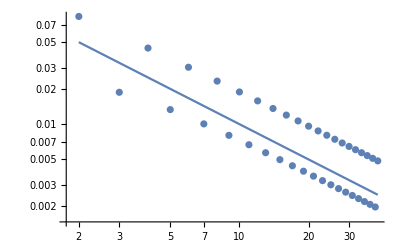

```mathematica
data = Table[{l,Abs[hRetuu[l,mmode][Left] ExpIωrstar[mmode][r0]]},{l,Abs@Weylspin,lmax}];
Show[ListLogLogPlot[data],
LogLogPlot[ l^(-1)/10,{l,Abs@Weylspin,lmax}]]
```

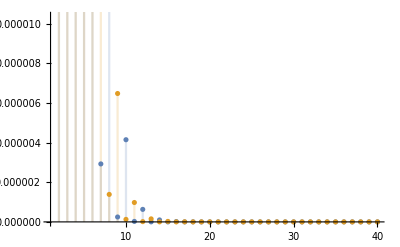

```mathematica
DiscretePlot[{Abs@Re[hRetmm[l,mmode][rNumOutbd] ExpIωrstar[mmode][rNumOutbd]],Abs@Im[hRetmm[l,mmode][rNumOutbd] ExpIωrstar[mmode][rNumOutbd]]},{l,1,lmax}]
```

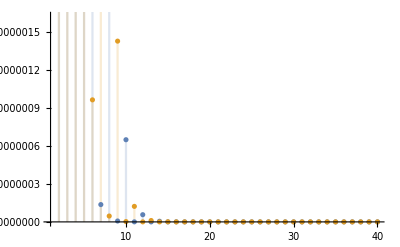

```mathematica
DiscretePlot[{Abs@Re[hRetmm[l,mmode][rNumInbd] ExpIωrstar[mmode][rNumInbd]],Abs@Im[hRetmm[l,mmode][rNumInbd] ExpIωrstar[mmode][rNumInbd]]},{l,1,lmax}]
```

### Individual m modes (Residual field)

The retarded reconstructed metric is by definition in radiation gauge, while the puncture is in Lorentz gauge.
So the difference will generically not cancel out the divergences.
Instead, we can look at the redshift:

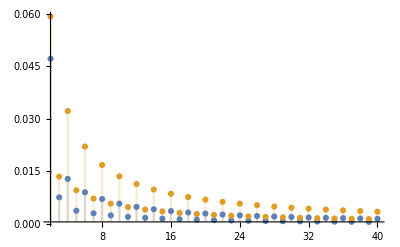

```mathematica
mmode=2;
DiscretePlot[{Abs@Re[hRetuu[l,mmode][r0+1/1000000]-hPuu[l,mmode][Right]],Abs@Im[hRetuu[l,mmode][r0+1/1000000]-hPuu[l,mmode][Right]]},{l,2,lmax},PlotRange->All]
```

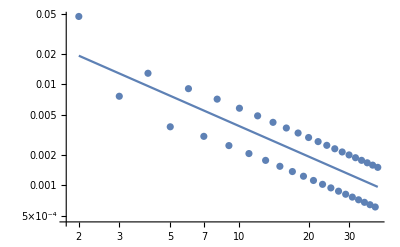

```mathematica
data = Table[{l,Abs@Re[hRetuu[l,mmode][r0-1/1000000]-hPuu[l,mmode][Left]]},{l,Abs@Weylspin,lmax}];
Show[ListLogLogPlot[data],
LogLogPlot[ l^(-1)/26,{l,Abs@Weylspin,lmax}]]
```

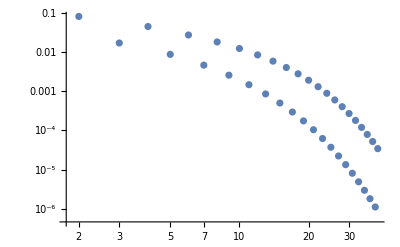

```mathematica
data = Table[{l,Abs@Re[hRuu[l,mmode][r0+1/1000000] ExpIωrstar[mmode][r0+1/1000000]]},{l,Abs@Weylspin,lmax}];
ListLogLogPlot[data]
```

## Check --- ℰ_ab(h^Res+h^P+x_ab) = 0

We already checked previously that ℰ_ab(ġ)=ℰ_ab(ℒ_Ξ g_ab)=0.
In principle, ℰ_ab(h^Res+h^P+x_ab)  is made up of three things: a smooth piece, a piece ~ δ at r_min and r_max and a piece δ’ at r_min and r_max. All these contributions need to vanish.
For distributional pieces, we will focus on r=r_min.

To set this up, use ℰhPWorldtubePiece, ℰhPδRminPiece, and ℰhPδRminPiece defined in the “Operator” section. It is important to do the following:
1) Compute these three quantities first making sure that the input for h^P is written in t slicing. ℰ_ab(h^P) itself should be given in u slicing.
2) Run the “Effective stress-energy” section.
3) Now, rerun the “Operator section” (specifically the subsection which computed the linearised Einstein operator), but this time, make sure that ℰhPWorldtubePiece, ℰhPδRminPiece, and ℰhPδRminPiece are written in u slicing for both input and output. The reason is that  T_ab^R := -ℰ_ab(h^P) and h^P is given in t slicing. On the other hand, h^Res and x_ab are both given in u slicing.

## Rules definitions

```mathematica
Clear[h𝒫TohResxabRule]
h𝒫TohResxabRule = {
h𝒫ll[l_,m_][r_] :> xll[l,m][r]+hRll[l,m][r],
h𝒫ln[l_,m_][r_] :> xln[l,m][r]+hRln[l,m][r],
h𝒫lm[l_,m_][r_] :> xlm[l,m][r]+hRlm[l,m][r],
h𝒫lmb[l_,m_][r_] :> xlmb[l,m][r]+hRlmb[l,m][r],
h𝒫nn[l_,m_][r_] :>xnn[l,m][r]+hRnn[l,m][r],
h𝒫nm[l_,m_][r_] :> xnm[l,m][r]+hRnm[l,m][r],
h𝒫nmb[l_,m_][r_] :> xnmb[l,m][r]+hRnmb[l,m][r],
h𝒫mm[l_,m_][r_] :> xmm[l,m][r]+hRmm[l,m][r],
h𝒫mmb[l_,m_][r_] :> xmmb[l,m][r]+hRmmb[l,m][r],
h𝒫mbmb[l_,m_][r_] :> xmbmb[l,m][r]+hRmbmb[l,m][r],
h𝒫ll[l_,m_]'[r_] :> xll[l,m]'[r]+hRll[l,m]'[r],
h𝒫ln[l_,m_]'[r_] :> xln[l,m]'[r]+hRln[l,m]'[r],
h𝒫lm[l_,m_]'[r_] :> xlm[l,m]'[r]+hRlm[l,m]'[r],
h𝒫lmb[l_,m_]'[r_] :> xlmb[l,m]'[r]+hRlmb[l,m]'[r],
h𝒫nn[l_,m_]'[r_] :>xnn[l,m]'[r]+hRnn[l,m]'[r],
h𝒫nm[l_,m_]'[r_] :> xnm[l,m]'[r]+hRnm[l,m]'[r],
h𝒫nmb[l_,m_]'[r_] :> xnmb[l,m]'[r]+hRnmb[l,m]'[r],
h𝒫mm[l_,m_]'[r_] :> xmm[l,m]'[r]+hRmm[l,m]'[r],
h𝒫mmb[l_,m_]'[r_] :> xmmb[l,m]'[r]+hRmmb[l,m]'[r],
h𝒫mbmb[l_,m_]'[r_] :> xmbmb[l,m]'[r]+hRmbmb[l,m]'[r],
h𝒫ll[l_,m_]''[r_] :> xll[l,m]''[r]+hRll[l,m]''[r],
h𝒫ln[l_,m_]''[r_] :>xln[l,m]''[r]+ hRln[l,m]''[r],
h𝒫lm[l_,m_]''[r_] :> xlm[l,m]''[r]+hRlm[l,m]''[r],
h𝒫lmb[l_,m_]''[r_] :> xlmb[l,m]''[r]+hRlmb[l,m]''[r],
h𝒫nn[l_,m_]''[r_] :>xnn[l,m]''[r]+hRnn[l,m]''[r],
h𝒫nm[l_,m_]''[r_] :> xnm[l,m]''[r]+hRnm[l,m]''[r],
h𝒫nmb[l_,m_]''[r_] :> xnmb[l,m]''[r]+hRnmb[l,m]''[r],
h𝒫mm[l_,m_]''[r_] :>xmm[l,m]''[r]+hRmm[l,m]''[r],
h𝒫mmb[l_,m_]''[r_] :> xmmb[l,m]''[r]+hRmmb[l,m]''[r],
h𝒫mbmb[l_,m_]''[r_] :> xmbmb[l,m]''[r]+hRmbmb[l,m]''[r]};
```

```mathematica
Clear[h𝒫TohRetRule]
h𝒫TohRetRule = {
h𝒫ll[l_,m_][r_] :> hRetll[l,m][r],
h𝒫ln[l_,m_][r_] :> hRetln[l,m][r],
h𝒫lm[l_,m_][r_] :> hRetlm[l,m][r],
h𝒫lmb[l_,m_][r_] :> hRetlmb[l,m][r],
h𝒫nn[l_,m_][r_] :>hRetnn[l,m][r],
h𝒫nm[l_,m_][r_] :> hRetnm[l,m][r],
h𝒫nmb[l_,m_][r_] :> hRetnmb[l,m][r],
h𝒫mm[l_,m_][r_] :> hRetmm[l,m][r],
h𝒫mmb[l_,m_][r_] :> hRetmmb[l,m][r],
h𝒫mbmb[l_,m_][r_] :> hRetmbmb[l,m][r],
h𝒫ll[l_,m_]'[r_] :> hRetll[l,m]'[r],
h𝒫ln[l_,m_]'[r_] :> hRetln[l,m]'[r],
h𝒫lm[l_,m_]'[r_] :> hRetlm[l,m]'[r],
h𝒫lmb[l_,m_]'[r_] :> hRetlmb[l,m]'[r],
h𝒫nn[l_,m_]'[r_] :>hRetnn[l,m]'[r],
h𝒫nm[l_,m_]'[r_] :> hRetnm[l,m]'[r],
h𝒫nmb[l_,m_]'[r_] :> hRetnmb[l,m]'[r],
h𝒫mm[l_,m_]'[r_] :> hRetmm[l,m]'[r],
h𝒫mmb[l_,m_]'[r_] :> hRetmmb[l,m]'[r],
h𝒫mbmb[l_,m_]'[r_] :>hRetmbmb[l,m]'[r],
h𝒫ll[l_,m_]''[r_] :> hRetll[l,m]''[r],
h𝒫ln[l_,m_]''[r_] :>hRetln[l,m]''[r],
h𝒫lm[l_,m_]''[r_] :> hRetlm[l,m]''[r],
h𝒫lmb[l_,m_]''[r_] :> hRetlmb[l,m]''[r],
h𝒫nn[l_,m_]''[r_] :>hRetnn[l,m]''[r],
h𝒫nm[l_,m_]''[r_] :> hRetnm[l,m]''[r],
h𝒫nmb[l_,m_]''[r_] :> hRetnmb[l,m]''[r],
h𝒫mm[l_,m_]''[r_] :>hRetmm[l,m]''[r],
h𝒫mmb[l_,m_]''[r_] :> hRetmmb[l,m]''[r],
h𝒫mbmb[l_,m_]''[r_] :> hRetmbmb[l,m]''[r]};
```

## {ℰ_ab(h^Res+h^P+x_ab)}^(smooth piece) = 0

Note: For the components along l^a, checked that l^a ℰ_ab(h^Res)=0 and it is the corrector tensor that takes care of the effective stress energy by itself, as it should by construction.

We find a problem near r_min for some components, but this is a numerical artifact from differentiating interpolated functions.

```mathematica
rGridLeft = Table[rmin+(r0-rmin) i/11,{i,0,10}];
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[1]] /. h𝒫TohResxabRule)-TllLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[2]] /. h𝒫TohResxabRule)-TlnLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[3]] /. h𝒫TohResxabRule)-TlmLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[4]] /. h𝒫TohResxabRule)-TlmbLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[5]] /. h𝒫TohResxabRule)-TnnLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[6]] /. h𝒫TohResxabRule)-TnmLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[7]] /. h𝒫TohResxabRule)-TnmbLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[8]] /. h𝒫TohResxabRule)-TmmLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[9]] /. h𝒫TohResxabRule)-TmmbLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridLeft[[i]]][[10]] /. h𝒫TohResxabRule)-TmbmbLeftInterpol[l,m][rGridLeft[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
```

2.94837×10^-13

1.00704×10^-13

4.05565×10^-14

4.05594×10^-14

3.66782×10^-10

1.04003×10^-10

1.04003×10^-10

0.00722839

1.67772×10^7

0.00722839

```mathematica
rGridRight = Table[r0+(rmax-r0) i/10,{i,0,10}];
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[1]] /. h𝒫TohResxabRule)-TllRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[2]] /. h𝒫TohResxabRule)-TlnRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[3]] /. h𝒫TohResxabRule)-TlmRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[4]] /. h𝒫TohResxabRule)-TlmbRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[5]] /. h𝒫TohResxabRule)-TnnRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[6]] /. h𝒫TohResxabRule)-TnmRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[7]] /. h𝒫TohResxabRule)-TnmbRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[8]] /. h𝒫TohResxabRule)-TmmRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[9]] /. h𝒫TohResxabRule)-TmmbRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPWorldtubePiece[l,m][rGridRight[[i]]][[10]] /. h𝒫TohResxabRule)-TmbmbRightInterpol[l,m][rGridRight[[i]]]],{i,1,11},{l,2,4},{m,-l,l}]
```

1.92846×10^-13

7.84399×10^-14

2.51673×10^-14

2.51672×10^-14

3.1045×10^-10

9.85445×10^-11

9.85445×10^-11

3.08919×10^-11

6.64175×10^-12

3.08919×10^-11

```mathematica
(ℰhPWorldtubePiece[2,0][rmin][[9]] /. h𝒫TohResxabRule)
(ℰhPWorldtubePiece[2,0][rmin+1/100000][[9]] /. h𝒫TohResxabRule)
TmmbLeftInterpol[2,0][rmin+1/100000]
```

-1.67772×10^7

0.000167419

0.00016818

## {ℰ_ab(h^Res+h^P+x_ab)}^(δ piece) = 0

For the distributional pieces (both δ and δ next section), need to be careful since using ℰhPδRminPiece and ℰhPδpRminPiece assumed that the input is of the form # H(r-r_min).
Now, this is true for puncture, stress energy, and corrector tensors (which all vanish outside the worldtube for r<r_min). However, for h^Res, it equals the retarded metric perturbation for r<r_min.
Basically, we could write, abusing notation: h^Res = h^Res H(r-r_min)+ψ^Ret H(r_min-r) = ψ^Ret-(h^Res-h^Ret) H(r-r_min).
So, the δ and δ’ pieces’ coefficients should be h^Res-h^Ret instead of just h^Res.

Checked that for pieces along l^a, the corrector tensor cancels the distributional pieces of the stress energy, as it should by construction.

```mathematica
Max@Table[Abs[(ℰhPδRminPiece[l,m][[1]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[1]] /. h𝒫TohRetRule)-TllδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[2]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[2]] /. h𝒫TohRetRule)-TlnδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[3]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[3]] /. h𝒫TohRetRule)-TlmδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[4]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[4]] /. h𝒫TohRetRule)-TlmbδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[5]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[5]] /. h𝒫TohRetRule)-TnnδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[6]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[6]] /. h𝒫TohRetRule)-TnmδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[7]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[7]] /. h𝒫TohRetRule)-TnmbδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[8]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[8]] /. h𝒫TohRetRule)-TmmδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[9]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[9]] /. h𝒫TohRetRule)-TmmbδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδRminPiece[l,m][[10]] /. h𝒫TohResxabRule)-(ℰhPδRminPiece[l,m][[10]] /. h𝒫TohRetRule)-TmbmbδRminInterpol[l,m]],{l,2,4},{m,-l,l}]
```

1.38778×10^-17

6.99289×10^-18

5.27596×10^-18

7.04731×10^-18

2.45327×10^-18

2.77903×10^-18

2.77903×10^-18

4.77542×10^-18

1.2044×10^-17

3.83572×10^-18

## {ℰ_ab(h^Res+h^P+x_ab)}^(δ' piece) = 0

```mathematica
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[1]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[1]] /. h𝒫TohRetRule)-TllδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[2]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[2]] /. h𝒫TohRetRule)-TlnδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[3]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[3]] /. h𝒫TohRetRule)-TlmδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[4]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[4]] /. h𝒫TohRetRule)-TlmbδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[5]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[5]] /. h𝒫TohRetRule)-TnnδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[6]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[6]] /. h𝒫TohRetRule)-TnmδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[7]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[7]] /. h𝒫TohRetRule)-TnmbδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[8]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[8]] /. h𝒫TohRetRule)-TmmδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[9]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[9]] /. h𝒫TohRetRule)-TmmbδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
Max@Table[Abs[(ℰhPδpRminPiece[l,m][[10]] /. h𝒫TohResxabRule)-(ℰhPδpRminPiece[l,m][[10]] /. h𝒫TohRetRule)-TmbmbδpRminInterpol[l,m]],{l,2,4},{m,-l,l}]
```

0.

7.75792×10^-18

6.93889×10^-18

6.93889×10^-18

3.46945×10^-18

3.46945×10^-18

3.46945×10^-18

2.83735×10^-16

7.46863×10^-18

2.83735×10^-16

## Metric in shadowless gauge

## Modes of h_ab^(N, shadowless)

Not evaluable.

The full corrected metric reads (see reconstruction paper, eq. (107) p. 29): h_ab^(N, Corrected) = (ĥ)_ab^N + (g^OverDot[~])_ab + (h̃)_ab^M Θ_M, where
(ĥ)_ab^N= 2 Re(𝒮_ab^†Φ^+) Θ_M^+ + 2 Re(𝒮_ab^†Φ^-) Θ_M^-  is the reconstructed field in the vacuum region r<r_min (-) and r>r_max (+),
(g^OverDot[~])_ab=(ġ)_ab Θ_M^+ - ℒ_Ξ Θ_M^-,
(h̃)_ab^M=2 Re(𝒮_ab^†Φ^M)+x_ab^M-ℒ_(ξ^S)g_ab-ℒ_Ξ g_ab.
Note that ℒ_(ξ^S)g_ab is zero in Schwarzschild.

## l modes evaluated at particle

Note: because different tetrad indices are expanded in different bases, we will write the l modes of each quantity starting at l=0.
For those quantities that start at a higher l mode, we will define their lower l values as zero.

### h^R

Making sure that the length of each list is the same by padding to the right the lower spin weighted objects.

```mathematica
hRlllModes = Table[Sum[hRll[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
hRlnlModes = Table[Sum[hRln[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
hRlmlModes = Table[Sum[hRlm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,lmax}];
hRlmblModes = Table[Sum[hRlmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,lmax}];
hRnnlModes = Table[Sum[hRnn[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
hRnmlModes = Table[Sum[hRnm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,π/2,0],
	{mInd,-lInd,lInd}],{lInd,1,lmax}];
hRnmblModes = Table[Sum[hRnmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,lmax}];
hRmmlModes = Table[Sum[hRmm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[2,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,2,lmax}];
hRmmblModes = Table[Sum[hRmmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
hRmbmblModes = Table[Sum[hRmbmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-2,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,2,lmax}];

hRlmlModes= PadLeft[hRlmlModes,lmax+1,0];
hRlmblModes= PadLeft[hRlmblModes,lmax+1,0];
hRnmlModes= PadLeft[hRnmlModes,lmax+1,0];
hRnmblModes= PadLeft[hRnmblModes,lmax+1,0];
hRmmlModes= PadLeft[hRmmlModes,lmax+1,0];
hRmbmblModes= PadLeft[hRmbmblModes,lmax+1,0];
```

### x_ab

```mathematica
xlllModes = Table[Sum[xll[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
xlnlModes = Table[Sum[xln[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
xlmlModes = Table[Sum[xlm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,lmax}];
xlmblModes = Table[Sum[xlmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,lmax}];
xnnlModes = Table[Sum[xnn[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
xnmlModes = Table[Sum[xnm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,lmax}];
xnmblModes = Table[Sum[xnmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,lmax}];
xmmlModes = Table[Sum[xmm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[2,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,2,lmax}];
xmmblModes = Table[Sum[xmmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,lmax}];
xmbmblModes = Table[Sum[xmbmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-2,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,2,lmax}];

xlmlModes= PadLeft[xlmlModes,lmax+1,0];
xlmblModes= PadLeft[xlmblModes,lmax+1,0];
xnmlModes= PadLeft[xnmlModes,lmax+1,0];
xnmblModes= PadLeft[xnmblModes,lmax+1,0];
xmmlModes= PadLeft[xmmlModes,lmax+1,0];
xmbmblModes= PadLeft[xmbmblModes,lmax+1,0];
```

### ℒ_Ξ g_ab

```mathematica
ℒΞglllModes = Table[Sum[ℒΞgll[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,1}];
ℒΞglnlModes = Table[Sum[ℒΞgln[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,1}];
ℒΞglmlModes = Table[Sum[ℒΞglm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,1}];
ℒΞglmblModes = Table[Sum[ℒΞglmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,1}];
ℒΞgnnlModes = Table[Sum[ℒΞgnn[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,1}];
ℒΞgnmlModes = Table[Sum[ℒΞgnm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,1}];
ℒΞgnmblModes = Table[Sum[ℒΞgnmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-1,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,1,1}];
ℒΞgmmlModes = Table[Sum[ℒΞgmm[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[2,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,2,1}];
ℒΞgmmblModes = Table[Sum[ℒΞgmmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,0,1}];
ℒΞgmbmblModes = Table[Sum[ℒΞgmbmb[lInd,mInd][r0] ExpIωrstar[mInd][r0] SpinWeightedSphericalHarmonicY[-2,lInd,mInd,π/2,0],
{mInd,-lInd,lInd}],{lInd,2,1}];

ℒΞglllModes = PadLeft[ℒΞglllModes,2,0];
ℒΞglnlModes = PadLeft[ℒΞglnlModes,2,0];
ℒΞglmlModes = PadLeft[ℒΞglmlModes,2,0];
ℒΞglmblModes = PadLeft[ℒΞglmblModes,2,0];
ℒΞgnnlModes = PadLeft[ℒΞgnnlModes,2,0];
ℒΞgnmlModes = PadLeft[ℒΞgnmlModes,2,0];
ℒΞgnmblModes = PadLeft[ℒΞgnmblModes,2,0];
ℒΞgmmlModes = PadLeft[ℒΞgmmlModes,2,0];
ℒΞgmmblModes = PadLeft[ℒΞgmmblModes,2,0];
ℒΞgmbmblModes = PadLeft[ℒΞgmbmblModes,2,0];

ℒΞglllModes = PadRight[ℒΞglllModes,lmax+1,0];
ℒΞglnlModes = PadRight[ℒΞglnlModes,lmax+1,0];
ℒΞglmlModes = PadRight[ℒΞglmlModes,lmax+1,0];
ℒΞglmblModes = PadRight[ℒΞglmblModes,lmax+1,0];
ℒΞgnnlModes = PadRight[ℒΞgnnlModes,lmax+1,0];
ℒΞgnmlModes = PadRight[ℒΞgnmlModes,lmax+1,0];
ℒΞgnmblModes = PadRight[ℒΞgnmblModes,lmax+1,0];
ℒΞgmmlModes = PadRight[ℒΞgmmlModes,lmax+1,0];
ℒΞgmmblModes = PadRight[ℒΞgmmblModes,lmax+1,0];
ℒΞgmbmblModes = PadRight[ℒΞgmbmblModes,lmax+1,0];
```

## 4D field evaluated at particle

### h^R

```mathematica
hRll4DPart = Total[hRlllModes];
hRln4DPart = Total[hRlnlModes];
hRlm4DPart = Total[hRlmlModes];
hRlmb4DPart = Total[hRlmblModes];
hRnn4DPart = Total[hRnnlModes];
hRnm4DPart = Total[hRnmlModes];
hRnmb4DPart = Total[hRnmblModes];
hRmm4DPart = Total[hRmmlModes];
hRmmb4DPart = Total[hRmmblModes];
hRmbmb4DPart = Total[hRmbmblModes];
```

### x_ab

```mathematica
xll4DPart = Total[xlllModes];
xln4DPart = Total[xlnlModes];
xlm4DPart = Total[xlmlModes];
xlmb4DPart = Total[xlmblModes];
xnn4DPart = Total[xnnlModes];
xnm4DPart = Total[xnmlModes];
xnmb4DPart = Total[xnmblModes];
xmm4DPart = Total[xmmlModes];
xmmb4DPart = Total[xmmblModes];
xmbmb4DPart = Total[xmbmblModes];
```

### ℒ_Ξ g_ab

```mathematica
ℒΞgll4DPart = Total[ℒΞglllModes];
ℒΞgln4DPart = Total[ℒΞglnlModes];
ℒΞglm4DPart = Total[ℒΞglmlModes];
ℒΞglmb4DPart = Total[ℒΞglmblModes];
ℒΞgnn4DPart = Total[ℒΞgnnlModes];
ℒΞgnm4DPart = Total[ℒΞgnmlModes];
ℒΞgnmb4DPart = Total[ℒΞgnmblModes];
ℒΞgmm4DPart = Total[ℒΞgmmlModes];
ℒΞgmmb4DPart = Total[ℒΞgmmblModes];
ℒΞgmbmb4DPart = Total[ℒΞgmbmblModes];
```

## General lm modes for shadowless metric perturbation

Defining h_lm = h_lm^R+x_lm-(ℒ_Ξ g_ab)_lm for all the tetrad legs. This is valid in the range r_min<r<r_max.

```mathematica
Clear[hll$lmModes,hln$lmModes,hlm$lmModes,hlmb$lmModes,hnn$lmModes,hnm$lmModes,hnmb$lmModes,hmm$lmModes,hmmb$lmModes,hmbmb$lmModes]
hll$lmModes[l_,m_][r_] = hRll[l,m][r]+xll[l,m][r]-ℒΞgll[l,m][r];
hln$lmModes[l_,m_][r_] = hRln[l,m][r]+xln[l,m][r]-ℒΞgln[l,m][r];
hlm$lmModes[l_,m_][r_] = hRlm[l,m][r]+xlm[l,m][r]-ℒΞglm[l,m][r];
hlmb$lmModes[l_,m_][r_] = hRlmb[l,m][r]+xlmb[l,m][r]-ℒΞglmb[l,m][r];
hnn$lmModes[l_,m_][r_] = hRnn[l,m][r]+xnn[l,m][r]-ℒΞgnn[l,m][r];
hnm$lmModes[l_,m_][r_] = hRnm[l,m][r]+xnm[l,m][r]-ℒΞgnm[l,m][r];
hnmb$lmModes[l_,m_][r_] = hRnmb[l,m][r]+xnmb[l,m][r]-ℒΞgnmb[l,m][r];
hmm$lmModes[l_,m_][r_] = hRmm[l,m][r]+xmm[l,m][r]-ℒΞgmm[l,m][r];
hmmb$lmModes[l_,m_][r_] = hRmmb[l,m][r]+xmmb[l,m][r]-ℒΞgmmb[l,m][r];
hmbmb$lmModes[l_,m_][r_] = hRmbmb[l,m][r]+xmbmb[l,m][r]-ℒΞgmbmb[l,m][r];
```

## Computation of redshift

```mathematica
metricContributionlModes= redshift$Contribution$Formula[hRlllModes,hRlnlModes,hRlmlModes,hRlmblModes,hRnnlModes,hRnmlModes,hRnmblModes,hRmmlModes,hRmmblModes,hRmbmblModes];

correctorContributionlModes= redshift$Contribution$Formula[xlllModes,xlnlModes,xlmlModes,xlmblModes,xnnlModes,xnmlModes,xnmblModes,xmmlModes,xmmblModes,xmbmblModes];

ℒΞgabContributionlModes= redshift$Contribution$Formula[ℒΞglllModes,ℒΞglnlModes,ℒΞglmlModes,ℒΞglmblModes,ℒΞgnnlModes,ℒΞgnmlModes,ℒΞgnmblModes,ℒΞgmmlModes,ℒΞgmmblModes,ℒΞgmbmblModes];
```

```mathematica
Total[metricContributionlModes+correctorContributionlModes-ℒΞgabContributionlModes];
exacthuu = -0.21606289103798457; (* for Subscript[r, 0]=10 *)
%%/exacthuu-1
```

0.0000381436-5.73293×10^-17 ⅈ

We can improve the agreement by matching for a power-law and sum beyond l_max. So that we can write schematically:   ∑h_uu^l = ∑_0^_l_max h_uu^(l,data)+∑_l_max^∞ al^b, where a and b are fitted parameters.

```mathematica
TransitionToPowerLaw = 30;
fitRule =  FindFit[Transpose[{Range[0,40],Re[metricContributionlModes+correctorContributionlModes-ℒΞgabContributionlModes]}][[TransitionToPowerLaw+1;;All]],a l^(-b),{a,b},l,MaxIterations->∞]
Total[Re[metricContributionlModes+correctorContributionlModes-ℒΞgabContributionlModes]]+
Sum[a l^(-b) /. fitRule,{l,lmax+1,∞}];
%/exacthuu-1
```

{a→1.48492,b→3.97311}

-2.84296×10^-7

## Redshift for different r_0

For r0 = 8M:	h_uu^GHZ = -0.2809995389719025.
For r0 = 9M:	h_uu^GHZ = -0.24390486588748073.
For r0 = 10M:	h_uu^GHZ = -0.21606282961213014.
For r0 = 12M:	h_uu^GHZ = -0.17655750951515695.
For r0 = 50M:	h_uu^GHZ = -0.0404192524172486.
All the above is done using a power law fitting for l>l_max=40.

## Check --- large l behaviour

```mathematica
huuRetMinusP =Quiet@Table[{l,Sum[hRetuu[l,m][Right] ExpIωrstar[m][r0]-hPuu[l,m][Right],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
```

We check the l mode behaviour of the metric perturbation using the GHZ scheme vs the usual method (reconstructed metric - lorentz puncture).

The first plot is done using WorkinPrecision=64. IF you use a too small precision (e.g. wp=36), you will find that the last few points go crazy and the power law wobbles a bit at the tail.

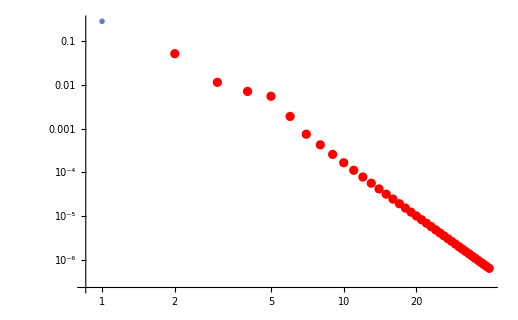

```mathematica
(* wp=64, MaxStepSize=0.01 in computing the Hertz, and 0.001 for the corrector tensors. *)
Show[ListLogLogPlot[Abs[metricContributionlModes+correctorContributionlModes-ℒΞgabContributionlModes],DataRange->{0,40},PlotMarkers->{"X",Large}],
ListLogLogPlot[Abs@huuRetMinusP,PlotStyle->Red]]
```

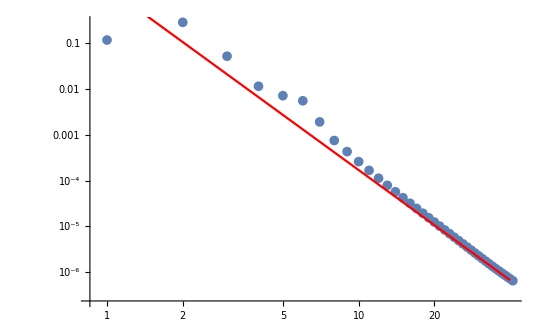

```mathematica
Show[ListLogLogPlot[Abs[metricContributionlModes+correctorContributionlModes-ℒΞgabContributionlModes]],
LogLogPlot[1.7 l^-4 /. fitRule,{l,0,40},PlotStyle->Red]]
```

## Check --- dependence on worldtube

Not evaluable.

Computing the individual l modes contributions of the metric, corrector tensors and gauge to h_uu, for different worldtube sizes.
For dr = 0.2M, need to increase MaxSteps in Hertz potential.

```mathematica
(* Worldtube with rmin=8M and rmax=12M and r0=10M *)
metricContributionlModes2MWorldtube = metricContributionlModes
correctorContributionlModes2MWorldtube = correctorContributionlModes
ℒΞgabContributionlModes2MWorldtube = ℒΞgabContributionlModes
```

{0,0,0.193641+0. ⅈ,0.212439-4.4331×10^-18 ⅈ,0.214047+5.23256×10^-19 ⅈ,0.211294-4.4331×10^-18 ⅈ,0.210631+0. ⅈ,0.206063-2.21655×10^-18 ⅈ,0.195308+0. ⅈ,0.181129+2.21655×10^-18 ⅈ,0.165129-1.10827×10^-18 ⅈ,0.147982-2.86371×10^-18 ⅈ,0.130434+3.84808×10^-18 ⅈ,0.11312+3.29394×10^-18 ⅈ,0.0965434-6.18772×10^-18 ⅈ,0.0810724-5.12952×10^-18 ⅈ,0.0669521+2.07801×10^-19 ⅈ,0.0543212+2.33964×10^-18 ⅈ,0.0432303-2.47818×10^-18 ⅈ,0.0336615-2.09355×10^-18 ⅈ,0.0255456+0. ⅈ,0.018778-3.33264×10^-18 ⅈ,0.0132323-1.06958×10^-18 ⅈ,0.00877068+2.61671×10^-18 ⅈ,0.00525285+7.65823×10^-19 ⅈ,0.00254192+4.8101×10^-19 ⅈ,0.000509014-1.23522×10^-18 ⅈ,-0.000963968+3.87215×10^-21 ⅈ,-0.00198271-7.60014×10^-19 ⅈ,-0.00263989-3.80975×10^-19 ⅈ,-0.00301524+2.08769×10^-19 ⅈ,-0.00317617+7.8411×10^-20 ⅈ,-0.00317869+1.56338×10^-19 ⅈ,-0.00306854-1.46589×10^-19 ⅈ,-0.0028824+4.16887×10^-19 ⅈ,-0.00264912+3.8419×10^-20 ⅈ,-0.00239089+2.15257×10^-20 ⅈ,-0.00212434-7.8882×10^-20 ⅈ,-0.00186154+5.98842×10^-20 ⅈ,-0.00161088+1.1845×10^-19 ⅈ,-0.00137785-2.28598×10^-21 ⅈ}

{-0.155423+0. ⅈ,-0.218528+0. ⅈ,-0.245824+0. ⅈ,-0.22395+4.4331×10^-18 ⅈ,-0.206889-4.4331×10^-18 ⅈ,-0.205751+4.95635×10^-18 ⅈ,-0.208718+9.36183×10^-18 ⅈ,-0.205312-1.01889×10^-18 ⅈ,-0.194879-4.95635×10^-18 ⅈ,-0.18087+0. ⅈ,-0.164963-2.49199×10^-18 ⅈ,-0.14787-3.077×10^-18 ⅈ,-0.130355-9.05225×10^-18 ⅈ,-0.113063-4.83244×10^-18 ⅈ,-0.0965013+1.78632×10^-18 ⅈ,-0.0810405-4.40222×10^-18 ⅈ,-0.0669275+3.03231×10^-18 ⅈ,-0.0543019-7.31273×10^-21 ⅈ,-0.043215-5.39928×10^-18 ⅈ,-0.0336492-2.45451×10^-18 ⅈ,-0.0255355+2.38779×10^-19 ⅈ,-0.0187697-3.09772×10^-20 ⅈ,-0.0132254-1.2236×10^-18 ⅈ,-0.00876491+1.36213×10^-18 ⅈ,-0.00524799+5.27476×10^-19 ⅈ,-0.0025378-1.23134×10^-18 ⅈ,-0.000505494-1.42581×10^-18 ⅈ,0.000966987+1.59621×10^-19 ⅈ,0.00198532-9.94711×10^-19 ⅈ,0.00264215+8.13793×10^-19 ⅈ,0.00301721-6.5395×10^-20 ⅈ,0.00317789+2.34265×10^-19 ⅈ,0.00318021-1.89251×10^-19 ⅈ,0.00306989+4.91011×10^-19 ⅈ,0.0028836+3.44067×10^-20 ⅈ,0.00265019-5.33026×10^-20 ⅈ,0.00239185+3.19321×10^-20 ⅈ,0.0021252-1.55491×10^-19 ⅈ,0.00186232-1.88767×10^-20 ⅈ,0.00161159+2.04397×10^-21 ⅈ,0.0013785-2.16497×10^-21 ⅈ}

{-0.273195,0.0682988+0. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Worldtube with rmin=9M and rmax=11M and r0=10M *)
metricContributionlModes1MWorldtube = metricContributionlModes
correctorContributionlModes1MWorldtube = correctorContributionlModes
ℒΞgabContributionlModes1MWorldtube = ℒΞgabContributionlModes
```

{0,0,0.180485+0. ⅈ,0.191868-4.4331×10^-18 ⅈ,0.198205-2.47818×10^-19 ⅈ,0.202597+4.95635×10^-18 ⅈ,0.207309+4.70854×10^-18 ⅈ,0.211657-4.95635×10^-18 ⅈ,0.214916+4.95635×10^-18 ⅈ,0.21717-4.95635×10^-18 ⅈ,0.218465+9.38945×10^-18 ⅈ,0.218748+0. ⅈ,0.218009-4.68091×10^-18 ⅈ,0.216257+5.47961×10^-18 ⅈ,0.213526+1.01605×10^-17 ⅈ,0.209868-2.21655×10^-18 ⅈ,0.205348-2.21655×10^-18 ⅈ,0.200044+8.28118×10^-18 ⅈ,0.194038-1.35609×10^-18 ⅈ,0.187422-5.54137×10^-18 ⅈ,0.180287-3.84808×10^-18 ⅈ,0.172724-1.23218×10^-18 ⅈ,0.164825+1.00813×10^-17 ⅈ,0.156675+5.54137×10^-19 ⅈ,0.148359+9.39674×10^-19 ⅈ,0.139952-1.18676×10^-17 ⅈ,0.131526+4.00977×10^-19 ⅈ,0.123147-1.66241×10^-18 ⅈ,0.114872+0. ⅈ,0.106753+2.47818×10^-18 ⅈ,0.0988349+3.025×10^-18 ⅈ,0.0911559+1.01825×10^-17 ⅈ,0.083748-1.29876×10^-19 ⅈ,0.0766374-4.14709×10^-18 ⅈ,0.0698446-2.47818×10^-18 ⅈ,0.0633849+2.27037×10^-18 ⅈ,0.057269+1.10055×10^-18 ⅈ,0.0515032+3.82482×10^-18 ⅈ,0.0460901+8.54463×10^-19 ⅈ,0.0410288-3.82482×10^-18 ⅈ,0.0363153-3.60971×10^-18 ⅈ}

{-0.155423+0. ⅈ,-0.218528+0. ⅈ,-0.232668+0. ⅈ,-0.203378+2.47818×10^-18 ⅈ,-0.191047+2.47818×10^-18 ⅈ,-0.197055+4.95635×10^-19 ⅈ,-0.205396+0. ⅈ,-0.210906-8.86619×10^-18 ⅈ,-0.214487+0. ⅈ,-0.216911+4.4331×10^-18 ⅈ,-0.218298+3.90984×10^-18 ⅈ,-0.218636+4.68091×10^-18 ⅈ,-0.21793-4.95635×10^-18 ⅈ,-0.2162-7.42072×10^-18 ⅈ,-0.213484+7.1729×10^-18 ⅈ,-0.209836+9.14163×10^-18 ⅈ,-0.205324+4.95635×10^-18 ⅈ,-0.200024+4.4331×10^-18 ⅈ,-0.194023-4.95635×10^-18 ⅈ,-0.18741-2.7398×10^-18 ⅈ,-0.180277+5.23256×10^-19 ⅈ,-0.172716-2.21655×10^-18 ⅈ,-0.164818+9.84365×10^-19 ⅈ,-0.15667-6.47165×10^-19 ⅈ,-0.148354-2.02727×10^-17 ⅈ,-0.139948+7.31062×10^-18 ⅈ,-0.131523-2.03126×10^-19 ⅈ,-0.123144-2.6159×10^-18 ⅈ,-0.114869-2.86371×10^-18 ⅈ,-0.106751+8.84912×10^-18 ⅈ,-0.0988328-3.23199×10^-18 ⅈ,-0.091154+2.75524×10^-18 ⅈ,-0.0837464+3.68274×10^-19 ⅈ,-0.076636+5.57244×10^-18 ⅈ,-0.0698433-3.30857×10^-18 ⅈ,-0.0633837-4.8944×10^-18 ⅈ,-0.0572679+3.17989×10^-18 ⅈ,-0.0515023-4.00977×10^-19 ⅈ,-0.0460893-2.28687×10^-18 ⅈ,-0.041028+1.3986×10^-18 ⅈ,-0.0363146-2.09721×10^-18 ⅈ}

{-0.273195,0.0682988+0. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Worldtube with rmin=49/5 M and rmax=51/5 M and r0=10M. *)
metricContributionlModes02MWorldtube = metricContributionlModes
correctorContributionlModes02MWorldtube = correctorContributionlModes
ℒΞgabContributionlModes02MWorldtube = ℒΞgabContributionlModes
```

{0,0,0.175704+1.23909×10^-19 ⅈ,0.182259-1.23909×10^-19 ⅈ,0.185949+0. ⅈ,0.187822-9.63727×10^-18 ⅈ,0.188909-9.14163×10^-18 ⅈ,0.189764-9.26554×10^-18 ⅈ,0.190533-4.46072×10^-18 ⅈ,0.191254-2.47818×10^-19 ⅈ,0.191955-1.01605×10^-17 ⅈ,0.192653+9.51336×10^-18 ⅈ,0.193356-8.9901×10^-18 ⅈ,0.194071+1.15922×10^-17 ⅈ,0.194799-1.81317×10^-17 ⅈ,0.195542-2.35427×10^-18 ⅈ,0.1963+1.31754×10^-17 ⅈ,0.197071-4.58463×10^-18 ⅈ,0.197855+1.34232×10^-17 ⅈ,0.19865+1.42219×10^-17 ⅈ,0.199455+1.13444×10^-17 ⅈ,0.200266-6.78736×10^-18 ⅈ,0.201084-2.6159×10^-18 ⅈ,0.201904-1.59014×10^-17 ⅈ,0.202727-4.06137×10^-18 ⅈ,0.203549+1.36986×10^-17 ⅈ,0.204369-6.33355×10^-19 ⅈ,0.205185+7.84884×10^-19 ⅈ,0.205995-8.86619×10^-18 ⅈ,0.206797+1.19915×10^-17 ⅈ,0.20759-3.85537×10^-19 ⅈ,0.208371+2.72599×10^-18 ⅈ,0.209139-6.91127×10^-18 ⅈ,0.209892+4.44691×10^-18 ⅈ,0.210629-2.75438×10^-19 ⅈ,0.211349+2.09264×10^-18 ⅈ,0.212049+9.40326×10^-18 ⅈ,0.212729+2.47818×10^-19 ⅈ,0.213386+1.98388×10^-17 ⅈ,0.214021+4.30919×10^-18 ⅈ,0.214632+6.66346×10^-18 ⅈ}

{-0.155423+0. ⅈ,-0.218528+0. ⅈ,-0.227887+0. ⅈ,-0.193769-1.10827×10^-18 ⅈ,-0.178791+0. ⅈ,-0.18228+1.72782×10^-18 ⅈ,-0.186996-1.10827×10^-18 ⅈ,-0.189014+0. ⅈ,-0.190104-1.23909×10^-19 ⅈ,-0.190995+6.9052×10^-21 ⅈ,-0.191789+1.363×10^-18 ⅈ,-0.19254+9.84365×10^-19 ⅈ,-0.193278-2.21655×10^-18 ⅈ,-0.194014-1.23909×10^-19 ⅈ,-0.194757-3.45564×10^-18 ⅈ,-0.19551+1.11518×10^-18 ⅈ,-0.196275+1.23909×10^-18 ⅈ,-0.197052-1.48691×10^-18 ⅈ,-0.19784+4.30919×10^-18 ⅈ,-0.198638+2.47818×10^-18 ⅈ,-0.199444+1.363×10^-18 ⅈ,-0.200258-1.22528×10^-18 ⅈ,-0.201077+5.53447×10^-18 ⅈ,-0.201899+2.10645×10^-18 ⅈ,-0.202722-3.96508×10^-18 ⅈ,-0.203545+0. ⅈ,-0.204366-1.72091×10^-18 ⅈ,-0.205182+1.07524×10^-17 ⅈ,-0.205992+2.35427×10^-18 ⅈ,-0.206795-2.46437×10^-18 ⅈ,-0.207587-2.35427×10^-18 ⅈ,-0.208369-4.08899×10^-18 ⅈ,-0.209137+1.03255×10^-17 ⅈ,-0.20989+0. ⅈ,-0.210628+0. ⅈ,-0.211347+7.65473×10^-18 ⅈ,-0.212048-3.99347×10^-19 ⅈ,-0.212728-6.47165×10^-19 ⅈ,-0.213386+1.38104×10^-20 ⅈ,-0.21402+3.85537×10^-19 ⅈ,-0.214631+4.68091×10^-18 ⅈ}

{-0.273195,0.0682988+0. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Checking here that individual l modes of h_uu is independent on worldtube size.

```mathematica
huulModes2MWorldtube=metricContributionlModes2MWorldtube+correctorContributionlModes2MWorldtube-ℒΞgabContributionlModes2MWorldtube;
huulModes1MWorldtube=metricContributionlModes1MWorldtube+correctorContributionlModes1MWorldtube-ℒΞgabContributionlModes1MWorldtube;
huulModes02MWorldtube=metricContributionlModes02MWorldtube+correctorContributionlModes02MWorldtube-ℒΞgabContributionlModes02MWorldtube;

huulModes2MWorldtube-huulModes1MWorldtube // Re
huulModes2MWorldtube-huulModes02MWorldtube // Re
```

{1.92083×10^-10,-1.73148×10^-10,-9.9197×10^-10,5.22323×10^-10,-1.98162×10^-9,-4.5461×10^-9,-6.77539×10^-9,-8.64861×10^-9,-1.10657×10^-8,-1.03674×10^-8,-1.32177×10^-8,-9.4909×10^-9,5.31263×10^-9,6.91889×10^-10,4.5431×10^-9,-7.47051×10^-10,-5.83714×10^-9,-1.44984×10^-8,-2.08798×10^-8,-3.42516×10^-8,-4.0893×10^-8,-4.54639×10^-8,-5.22924×10^-8,-6.05754×10^-8,-7.79499×10^-8,-9.5187×10^-8,-1.02009×10^-7,-1.14521×10^-7,-1.22121×10^-7,-1.28156×10^-7,-1.30887×10^-7,-1.42697×10^-7,-1.39808×10^-7,-1.32907×10^-7,-1.05852×10^-7,-1.11136×10^-7,-1.06843×10^-7,-9.62389×10^-8,-8.52376×10^-8,-7.15159×10^-8,-5.727×10^-8}

{5.22413×10^-10,4.39218×10^-11,2.18132×10^-9,4.15437×10^-9,2.13918×10^-9,-4.92819×10^-10,-3.31177×10^-9,-7.66102×10^-9,-1.49586×10^-8,-2.24477×10^-8,-3.67103×10^-8,-4.78942×10^-8,-8.69735×10^-8,-1.16751×10^-7,-1.42028×10^-7,-1.80999×10^-7,-2.23787×10^-7,-2.74138×10^-7,-3.26821×10^-7,-3.72512×10^-7,-4.35164×10^-7,-4.99203×10^-7,-5.64565×10^-7,-6.36878×10^-7,-7.11539×10^-7,-7.89701×10^-7,-8.60987×10^-7,-9.47102×10^-7,-1.0318×10^-6,-1.10773×10^-6,-1.19477×10^-6,-1.28328×10^-6,-1.36313×10^-6,-1.45202×10^-6,-1.53186×10^-6,-1.62252×10^-6,-1.70607×10^-6,-1.79168×10^-6,-1.88842×10^-6,-1.97756×10^-6,-2.0699×10^-6}

Compare the value of h_uu for different worldtubes to the known value of h_uu.

```mathematica
exacthuu = -0.21606289103798457;
```

```mathematica
(* 2M on each side *)
Total[metricContributionlModes2MWorldtube]
Total[correctorContributionlModes2MWorldtube]
Total[ℒΞgabContributionlModes2MWorldtube]
Re@Total[%%%+%%-%]/exacthuu-1
```

2.59871-2.05545×10^-17 ⅈ

-3.01967-2.00509×10^-17 ⅈ

-0.204896+0. ⅈ

0.0000385289

```mathematica
(* 1M on each side *)
Total[metricContributionlModes1MWorldtube]
Total[correctorContributionlModes1MWorldtube]
Total[ℒΞgabContributionlModes1MWorldtube]
Re@Total[%%%+%%-%]/exacthuu-1
```

5.86087+2.02389×10^-17 ⅈ

-6.28183+1.14304×10^-18 ⅈ

-0.204896+0. ⅈ

0.0000285699

```mathematica
(* 0.2M on each side *)
Total[metricContributionlModes02MWorldtube]
Total[correctorContributionlModes02MWorldtube]
Total[ℒΞgabContributionlModes02MWorldtube]
Re@Total[%%%+%%-%]/exacthuu-1
```

7.79957+2.60615×10^-17 ⅈ

-8.22053+3.19059×10^-17 ⅈ

-0.204896+0. ⅈ

0.0000262436

## Check --- string singularity

### Coordinates

Want local, comoving coordinates (x,y,z) around particle.
For comoving coordinates, we set ϕ^new = ϕ-Ωt, which is effectively the same as setting t=0 in old coordinates.
Choose
x = Δr sin θ cos ϕ,
y = Δr sin θ sin ϕ,
z = Δr cos θ.
Then, take cylindrical coordinates (ϱ,θ̃,z),
x = ϱ cos θ̃,
y = ϱ sin θ̃.

So, have:
θ̃ = ϕ,
ϱ = |Δr sin θ|,
z = Δr cos θ.
Sticking to z>0 (implying r>r_0), and 0<θ<π, can invert to find,
ϕ =θ̃ ,
Δr = √(z^2+ϱ^2),
θ = arctan(ϱ/z).

```mathematica
Clear[myxCoord,myyCoord,myzCoord,myΔrCoord,myθCoord,myϕCoord]
myxCoord[Δr_,θ_,ϕ_] = Δr Sin[θ] Cos[ϕ];
myyCoord[Δr_,θ_,ϕ_] = Δr Sin[θ] Sin[ϕ];
myzCoord[Δr_,θ_,ϕ_] = Δr Cos[θ];

myΔrCoord[ϱ_,θTilde_,z_] =Sqrt[ϱ^2+z^2];
myθCoord[ϱ_,θTilde_,z_] = ArcTan[z,ϱ];
myϕCoord[ϱ_,θTilde_,z_] = θTilde;
```

```mathematica
myθt = π/3;
myz = 1/2;
```

### x_ab

```mathematica
myθt = π/3;
myz = 1/2;
xnnϱ = Monitor[
Table[
{ϱ,Sum[
xnn[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0] ExpIωrstar[mInd][myΔrCoord[ϱ,myθt,myz]+r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,myθCoord[ϱ,myθt,myz],myϕCoord[ϱ,myθt,myz]],
{lInd,0,lmax},{mInd,-lInd,lInd}]},
{ϱ,0,0.1,0.001}],
{ϱ}];
xnnϱInterpolation = Interpolation[xnnϱ];
```

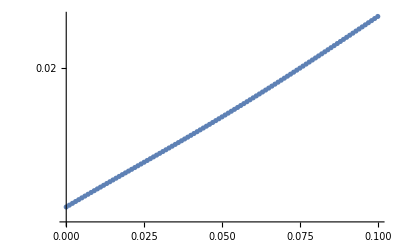

```mathematica
ListLogPlot[Abs@xnnϱ]
```

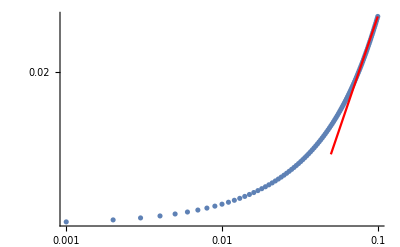

```mathematica
Show[ListLogLogPlot[Abs@xnnϱ],
LogLogPlot[Abs@xnnϱ[[-1,2]] ϱ^0.25/(0.1^0.25),{ϱ,0.05,0.1},PlotStyle->Red],PlotRange -> All]
```

```mathematica
xmmbϱ = Monitor[
Table[
{ϱ,Sum[xmmb[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0] ExpIωrstar[mInd][myΔrCoord[ϱ,myθt,myz]+r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,myθCoord[ϱ,myθt,myz],myϕCoord[ϱ,myθt,myz]],{lInd,0,lmax},{mInd,-lInd,lInd}]},
{ϱ,0,0.1,0.001}],
{ϱ}];
xmmbϱInterpolation = Interpolation[xmmbϱ];
```

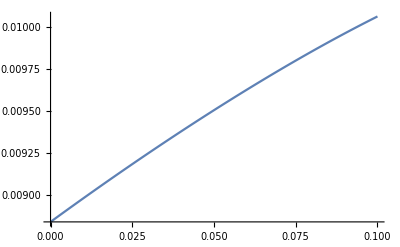

```mathematica
Plot[Abs[xmmbϱInterpolation[ϱ]],{ϱ,0,0.1}]
```

```mathematica
xnmϱ = Monitor[
Table[
{ϱ,Sum[xnm[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0] ExpIωrstar[mInd][myΔrCoord[ϱ,myθt,myz]+r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,myθCoord[ϱ,myθt,myz],myϕCoord[ϱ,myθt,myz]],{lInd,0,lmax},{mInd,-lInd,lInd}]},
{ϱ,0,0.1,0.001}],
{ϱ}];
xnmϱInterpolation = Interpolation[xnmϱ];
```

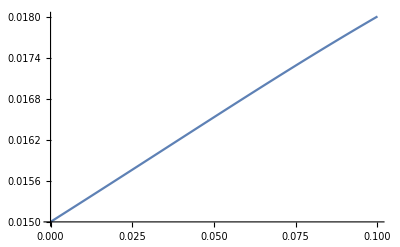

```mathematica
Plot[Abs[xnmϱInterpolation[ϱ]],{ϱ,0,0.1}]
```

### h_ab^R+x_ab

```mathematica
hRnnxnnϱ = Monitor[
Table[{ϱ,Sum[(hRnn[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0]+xnn[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0]) ExpIωrstar[mInd][myΔrCoord[ϱ,myθt,myz]+r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,myθCoord[ϱ,myθt,myz],myϕCoord[ϱ,myθt,myz]],{lInd,0,lmax},
{mInd,-lInd,lInd}]},{ϱ,0,0.1,0.001}],
{ϱ}];
hRnnxnnϱInterpolation = Interpolation[hRnnxnnϱ];
```

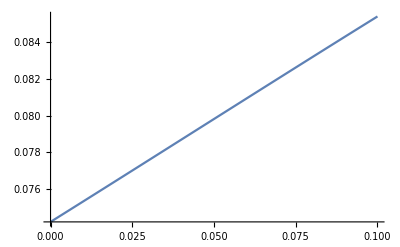

```mathematica
Plot[Abs[hRnnxnnϱInterpolation[ϱ]],{ϱ,0,0.1}]
```

```mathematica
myθt = π/3;
myz = 1/2;
hRmmbxmmbϱ = Monitor[
Table[{ϱ,Sum[(hRmmb[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0]+xmmb[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0]) ExpIωrstar[mInd][myΔrCoord[ϱ,myθt,myz]+r0] SpinWeightedSphericalHarmonicY[0,lInd,mInd,myθCoord[ϱ,myθt,myz],myϕCoord[ϱ,myθt,myz]],{lInd,0,lmax},
{mInd,-lInd,lInd}]},{ϱ,0,0.1,0.001}],
{ϱ}];
hRmmbxmmbϱInterpolation = Interpolation[hRmmbxmmbϱ];
```

```mathematica
Plot[Abs[hRmmbxmmbϱInterpolation[ϱ]],{ϱ,0,0.1}]
```

-Graphics-

```mathematica
hRnmxnmϱ = Monitor[
Table[{ϱ,Sum[(hRnm[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0]+xnm[lInd,mInd][myΔrCoord[ϱ,myθt,myz]+r0]) ExpIωrstar[mInd][myΔrCoord[ϱ,myθt,myz]+r0] SpinWeightedSphericalHarmonicY[1,lInd,mInd,myθCoord[ϱ,myθt,myz],myϕCoord[ϱ,myθt,myz]],{lInd,0,lmax},
{mInd,-lInd,lInd}]},{ϱ,0,0.1,0.001}],
{ϱ}];
hRnmxnmϱInterpolation = Interpolation[hRnmxnmϱ];
```

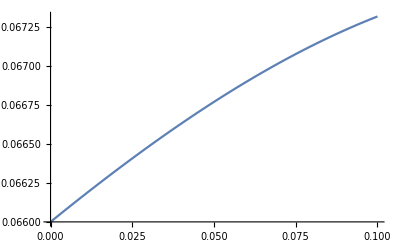

```mathematica
Plot[Abs[hRnmxnmϱInterpolation[ϱ]],{ϱ,0,0.1}]
```

### L^2 norm

Looking at the L^2 norm over the sphere centered around the central black hole. Using orthonormality of the harmonics, this is simply ||h_ab(||)_(L^2) = ∑_lm |h_ab^lm(r)|^2.

```mathematica
Clear[hll$lMode$L2Norm,hln$lMode$L2Norm,hlm$lMode$L2Norm,hlmb$lMode$L2Norm,hnn$lMode$L2Norm,hnm$lMode$L2Norm,hnmb$lMode$L2Norm,hmm$lMode$L2Norm,hmmb$lMode$L2Norm,hmbmb$lMode$L2Norm]
rString = (r0+rmax)/2;
hll$lMode$L2Norm = Table[Sum[Abs[hRll[lInd,mInd][rString]+xll[lInd,mInd][rString]-ℒΞgll[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hln$lMode$L2Norm = Table[Sum[Abs[hRln[lInd,mInd][rString]+xln[lInd,mInd][rString]-ℒΞgln[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hlm$lMode$L2Norm = Table[Sum[Abs[hRlm[lInd,mInd][rString]+xlm[lInd,mInd][rString]-ℒΞglm[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hlmb$lMode$L2Norm = Table[Sum[Abs[hRlmb[lInd,mInd][rString]+xlmb[lInd,mInd][rString]-ℒΞglmb[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hnn$lMode$L2Norm = Table[Sum[Abs[hRnn[lInd,mInd][rString]+xnn[lInd,mInd][rString]-ℒΞgnn[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hnm$lMode$L2Norm = Table[Sum[Abs[hRnm[lInd,mInd][rString]+xnm[lInd,mInd][rString]-ℒΞgnm[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hnmb$lMode$L2Norm = Table[Sum[Abs[hRnmb[lInd,mInd][rString]+xnmb[lInd,mInd][rString]-ℒΞgnmb[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hmm$lMode$L2Norm = Table[Sum[Abs[hRmm[lInd,mInd][rString]+xmm[lInd,mInd][rString]-ℒΞgmm[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hmmb$lMode$L2Norm = Table[Sum[Abs[hRmmb[lInd,mInd][rString]+xmmb[lInd,mInd][rString]-ℒΞgmmb[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
hmbmb$lMode$L2Norm = Table[Sum[Abs[hRmbmb[lInd,mInd][rString]+xmbmb[lInd,mInd][rString]-ℒΞgmbmb[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}],{lInd,0,lmax}];
```

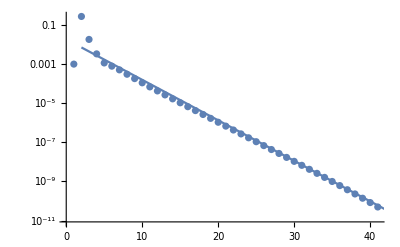

```mathematica
Show[ListLogPlot[hnn$lMode$L2Norm],
LogPlot[0.018 Exp[-l/2.1],{l,2,42}]]
```

# Data

### Data --- ψ_0 continuity

Sampling retarded field everywhere and residual field in the worldtube (WT).

```mathematica
factor = 50;
(*ψResLeftTable = Table[{N[rmin+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmin+i/factor]],20]},{i,0,factor (r0-rmin)-1}];
ψResRightTable = Table[{N[rmin+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmin+i/factor]],20]},{i,factor (r0-rmin)+1,factor (rmax-rmin)}];*)
ψResWTTable = Table[{N[rmin+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmin+i/factor]],20]},{i,0,factor (rmax-rmin)}];

ψResLeftTable = Table[{N[rNumInbd+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rNumInbd+i/factor]],20]},{i,0,factor (rmin-rNumInbd)-1}];
ψResRightTable = Table[{N[rmax+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmax+i/factor]],20]},{i,1,factor (rNumOutbd-rmax)}];

ψRetWTLeftTable = Table[{N[rmin+i/factor,5],N[Re[ψRet[2,2][rmin+i/factor]],20]},{i,0,factor (r0-rmin)-1}];
ψRetWTRightTable = Table[{N[r0+i/factor,5],N[Re[ψRet[2,2][r0+i/factor]],20]},{i,1,factor (rmax-r0)}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/patrick/Documents/Self-force

```mathematica
Export["Psi0ResWT_22.csv",ψResWTTable];
Export["Psi0Res_Left_22.csv",ψResLeftTable];
Export["Psi0Res_Right_22.csv",ψResRightTable];
Export["Psi0RetWT_Left_22.csv",ψRetWTLeftTable];
Export["Psi0RetWT_Right_22.csv",ψRetWTRightTable];
```

### Data --- Φ at and off particle

```mathematica
ΔrPlot=1/10000000000000000;
Φ$AtParticle$Data = Abs@Table[{l,Sum[Conjugate[ΦMbar[l,m][r0-ΔrPlot] ExpIωrstar[-m][r0-ΔrPlot]] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/patrick/Documents/Self-force/Metric reconstruction/Notebooks

```mathematica
Export["PhiR_Atr0_lBehaviour.csv",Φ$AtParticle$Data];
```

### Data --- large l behaviour

Large l behaviour both at r_0 and r_min.

```mathematica
ψRet$Atr0$lBehaviour$Table = Table[{l,Abs@Sum[ψRet[l,m][r0] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψRes$Atr0$lBehaviour$Table = Table[{l,Abs@Sum[ψ0RSmoothPiece[l,m][r0] ExpIωrstar[m][r0] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
```

```mathematica
Export["Psi0Ret_Atr0_lBehaviour.csv",ψRet$Atr0$lBehaviour$Table];
Export["Psi0Res_Atr0_lBehaviour.csv",ψRes$Atr0$lBehaviour$Table];
```

```mathematica
ψRet$Atrmin$lBehaviour$Table=Table[{l,Abs@Sum[ψRet[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
ψRes$Atrmin$lBehaviour$Table=Table[{l,Abs@Sum[ψ0RSmoothPiece[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[Weylspin,l,m,π/2,0],{m,-l,l}]},{l,Abs[Weylspin],lmax}];
```

```mathematica
Export["Psi0Ret_Atrmin_lBehaviour.csv",ψRet$Atrmin$lBehaviour$Table];
Export["Psi0Res_Atrmin_lBehaviour.csv",ψRes$Atrmin$lBehaviour$Table];
```

### Data --- GHZ h_ab,x_ab,(ġ)_ab,ℒ_Ξ g_ab continuity

Sampling retarded field everywhere and residual field in the worldtube (WT).

```mathematica
factor = 50;
(*ψResLeftTable = Table[{N[rmin+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmin+i/factor]],20]},{i,0,factor (r0-rmin)-1}];
ψResRightTable = Table[{N[rmin+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmin+i/factor]],20]},{i,factor (r0-rmin)+1,factor (rmax-rmin)}];*)
hnnResWTTable = Table[{N[rmin+i/factor,5],N[Re[hRnn[2,2][rmin+i/factor]],20]},{i,0,factor (rmax-rmin)}];
hnnResLeftTable = Table[{N[rNumInbd+i/factor,5],N[Re[hRetnn[2,2][rNumInbd+i/factor]],20]},{i,0,factor (rmin-rNumInbd)-1}];
hnnResRightTable = Table[{N[rmax+i/factor,5],N[Re[hRetnn[2,2][rmax+i/factor]],20]},{i,1,factor (rNumOutbd-rmax)}];
xnnResWTTable = Table[{N[rmin+i/factor,5],N[Re[xnn[2,2][rmin+i/factor]],20]},{i,0,factor (rmax-rmin)}];

gDotnnRightTable = Table[{N[rmax+i/factor,5],N[Re[gDotnn[0,0][rmax+i/factor]],20]},{i,0,factor (rNumOutbd-rmax)}];
ℒΞgnnWTTable = Table[{N[rmin+i/factor,5],N[Re[ℒΞgnn[0,0][rmin+i/factor]],20]},{i,0,factor (rmax-rmin)}];
ℒΞgnnLeftTable = Table[{N[rNumInbd+i/factor,5],N[Re[ℒΞgnn[0,0][rNumInbd+i/factor]],20]},{i,0,factor (rmin-rNumInbd)}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/patrick/Documents/Self-force

```mathematica
Export["hnnRes_WT_22.csv",hnnResWTTable];
Export["hnnRes_Left_22.csv",hnnResLeftTable];
Export["hnnRes_Right_22.csv",hnnResRightTable];
Export["xnn_WT_22.csv",xnnResWTTable];
Export["gDotnn_Right_22.csv",gDotnnRightTable];
Export["LXignn_WT_22.csv",ℒΞgnnWTTable];
Export["LXignn_Left_22.csv",ℒΞgnnLeftTable];
```

### Data --- CCK h_ab,(ġ)_ab,ℒ_Ξ g_ab continuity

Sampling retarded field everywhere and residual field in the worldtube (WT).

```mathematica
factor = 50;
(*ψResLeftTable = Table[{N[rmin+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmin+i/factor]],20]},{i,0,factor (r0-rmin)-1}];
ψResRightTable = Table[{N[rmin+i/factor,5],N[Re[ψ0RSmoothPiece[2,2][rmin+i/factor]],20]},{i,factor (r0-rmin)+1,factor (rmax-rmin)}];*)
CCKhnnRetLeftTable = Table[{N[rNumInbd+i/factor,5],N[Re[hRetnn[2,2][rNumInbd+i/factor]],20]},{i,0,factor (r0-rNumInbd)-1}];
CCKhnnRetRightTable = Table[{N[r0+i/factor,5],N[Re[hRetnn[2,2][r0+i/factor]],20]},{i,1,factor (rNumOutbd-r0)}];

CCKgDotnnRightTable = Table[{N[r0+i/factor,5],N[Re[gDotnn[0,0][r0+i/factor]],20]},{i,0,factor (rNumOutbd-r0)}];
CCKℒΞgnnLeftTable = Table[{N[rNumInbd+i/factor,5],N[Re[ℒΞgnn[0,0][rNumInbd+i/factor]],20]},{i,0,factor (r0-rNumInbd)}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/patrick/Documents/Self-force

```mathematica
Export["CCKhnnRet_Left_22.csv",CCKhnnRetLeftTable];
Export["CCKhnnRet_Right_22.csv",CCKhnnRetRightTable];
Export["CCKgDotnn_Right_00.csv",CCKgDotnnRightTable];
Export["CCKLXignn_Left_00.csv",CCKℒΞgnnLeftTable];
```

### Data --- L^2 norm

```mathematica
hSLnn$lMode$L2Norm$Table = Table[{lInd,Sum[Abs[hRnn[lInd,mInd][rString]+xnn[lInd,mInd][rString]-ℒΞgnn[lInd,mInd][rString]]^2,{mInd,-lInd,lInd}]},{lInd,0,lmax}];
```

```mathematica
Export["hSLnn_lBehaviour_L2Norm.csv",hSLnn$lMode$L2Norm$Table];
```

### Data --- h_uu behaviour

```mathematica
Clear[hRuu,xuu,ℒΞguu]
hRuu[l_,m_][r_] = redshift$Contribution$Formula[
hRll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
hRln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRlm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRlmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
hRnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,hRnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,hRnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,hRmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
hRmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0  || l == 1,0,hRmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
xuu[l_,m_][r_] = redshift$Contribution$Formula[
xll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
xln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,xlm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,xlmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
xnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,xnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,xnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,xmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
xmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,xmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
ℒΞguu[l_,m_][r_] = redshift$Contribution$Formula[
ℒΞgll[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
ℒΞgln[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,ℒΞglm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,ℒΞglmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
ℒΞgnn[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0,0,ℒΞgnm[l,m][r] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0]],
If[l == 0,0,ℒΞgnmb[l,m][r] SpinWeightedSphericalHarmonicY[-1,l,m,π/2,0]],
If[l == 0 || l == 1,0,ℒΞgmm[l,m][r] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0]],
ℒΞgmmb[l,m][r] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],
If[l == 0 || l == 1,0,ℒΞgmbmb[l,m][r] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0]]];
```

```mathematica
huu$CCK$lBehaviour$Table =Quiet@Table[{l,Sum[hRetuu[l,m][Left] ExpIωrstar[m][r0]-hPuu[l,m][Left]-ℒΞguu[l,m][r0],{m,-l,l}]},{l,0,lmax}];
```

```mathematica
huu$GHZ$lBehaviour$Table = Table[{lInd,Sum[(hRuu[lInd,mInd][r0]+xuu[lInd,mInd][r0]-ℒΞguu[lInd,mInd][r0]) ExpIωrstar[mInd][r0],
{mInd,-lInd,lInd}]},{lInd,0,lmax}];
```

```mathematica
huuCCK$vs$GHZ$Table = Transpose[{Transpose[huu$CCK$lBehaviour$Table][[1]],
Transpose[huu$GHZ$lBehaviour$Table][[2]]-Transpose[huu$CCK$lBehaviour$Table][[2]]}];
```

```mathematica
Export["huuGHZ.csv",Abs@huu$GHZ$lBehaviour$Table[[3;;]]];
Export["huuCCK.csv",Abs@huu$CCK$lBehaviour$Table[[3;;]]];
Export["huuCCK_vs_GHZ.csv",Abs@huuCCK$vs$GHZ$Table[[3;;]]];
```

# Archive

Below are old sections. Keeping it for posterity.

## Analytic puncture

## Analytic Lorenz-Gauge Punctures

Not evaluable.

### Puncture in BLS basis

```mathematica
Clear[hPLorenz]
```

```mathematica
Λ1=(l(l+1))/((2l-1)(2l+3));
Λ2=((l-1)l(l+1)(l+2))/((2l-3)(2l-1)(2l+3)(2l+5));
```

```mathematica
hPLorenz[1][l_,m_]=√2 (r0+Δr)WignerD[{l,m,0},π,π/2,π/2](√(2π))/(√(2l+1))(-(2 (1+2 l) (-2 M+r0)  pm √(Δr^2))/(r0^(5/2) √(-3 M+r0))+((1+2 l)^2 √(-2 M+r0) Δr^2 EllipticE[M/(r0-2M)])/(π r0^3 √(-3 M+r0))+(8 (-2 M+r0)^(3/2) EllipticK[M/(r0-2M)])/(π r0^2 √(-3 M+r0))+(2 (1+2 l) √(-3 M+r0) Δr  pm √(Δr^2))/r0^(7/2)+(4 √(-2 M+r0) Δr ((-2 M+r0) EllipticE[M/(r0-2M)]-2 (-4 M+r0) EllipticK[M/(r0-2M)]))/(π r0^3 √(-3 M+r0))+1/(2 π r0^4 (-3 M+r0)^(3/2))√(-2 M+r0) Δr^2 ((14 M^2-5 M r0+r0^2) EllipticE[M/(r0-2M)]+5 (-7 M+r0) (-3 M+r0) EllipticK[M/(r0-2M)])+(4 (-2 M+r0)^(3/2) ((17 M-7 r0) (-2 M+r0) EllipticE[M/(r0-2M)]+(-3 M+r0) (-32 M+7 r0) EllipticK[M/(r0-2M)]))/((-1+2 l) (3+2 l) π r0^3 (-3 M+r0)^(3/2))+(√(-2 M+r0) Δr ((3952 M^4-5402 M^3 r0+2689 M^2 r0^2-510 M r0^3+23 r0^4) EllipticE[M/(r0-2M)]+(-9246 M^4+9973 M^3 r0-3767 M^2 r0^2+559 M r0^3-23 r0^4) EllipticK[M/(r0-2M)]))/((-1+2 l) (3+2 l) 2 π r0^4 (-3 M+r0)^(5/2)))+If[l<2,0,√2 (r0+Δr)(WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])(√((l-1)l(l+1)(l+2)))/(√(2l+1)√(2π))((8 Δr^2 √(r0-2 M))/(3 M r0^3 √(r0-3 M)) ((2r0-5 M) EllipticE[M/(r0-2M)]-2 (r0-3 M) EllipticK[M/(r0-2M)])- 1/((-1+2 l) (3+2 l))(192(r0-2 M)^(3/2))/(3 M r0^2 √(r0-3 M))(-2(r0-2 M) EllipticE[-M/(2 M-r0)]+(2 r0-5 M) EllipticK[M/(r0-2M)])-(32  √(-2 M+r0) Δr)/(M r0^3 √(-3 M+r0)) ((42 M^2-33 M r0+6 r0^2) EllipticE[-M/(2 M-r0)]-2 (26 M^2-18 M r0+3 r0^2) EllipticK[M/(r0-2M)])(1/((-1+2 l) (3+2 l)))+1/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))32/(M r0^3) ((-2 M+r0)/(-3 M+r0))^(3/2) ((1022 M^3-913 M^2 r0+217 M r0^2-8 r0^3) EllipticE[-M/(2 M-r0)]+(-1284 M^3+1019 M^2 r0-221 M r0^2+8 r0^3) EllipticK[M/(r0-2M)])-1/((-1+2 l) (3+2 l))(4 √(r0-2 M) Δr^2)/(M r0^4 (r0-3 M)^(3/2)) ((590 M^3-731 M^2 r0+287 M r0^2-36 r0^3) EllipticE[M/(r0-2M)]+(-741 M^3+838 M^2 r0-305 M r0^2+36 r0^3) EllipticK[M/(r0-2M)])-1/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))(4 √(r0-2 M) Δr)/( M r0^4 (r0-3 M)^(5/2))((104536 M^5-153254 M^4 r0+81693 M^3 r0^2-18606 M^2 r0^3+1451 M r0^4+20 r0^5) EllipticE[M/(r0-2M)]+(r0-3 M) (43678 M^4-45091 M^3 r0+14858 M^2 r0^2-1501 M r0^3-20 r0^4) EllipticK[M/(r0-2M)]))];
```

```mathematica
hPLorenz[2][l_,m_]=If[l<1,0,√2 (r0+Δr) ((32 √(l (1+l)) √(2/π) √(-2 M+r0) Δr (1-(2 M)/(r0+Δr)) ((-27 M^2+19 M r0-3 r0^2) EllipticE[-M/(2 M-r0)]+3 (12 M^2-7 M r0+r0^2) EllipticK[-M/(2 M-r0)]))/((-1+2 l) √(1+2 l) (3+2 l) √M r0^(5/2) (-3 M+r0)^(3/2))+(√(l (1+l)) √(2 π) (1-(2 M)/(r0+Δr)) ((8 (-3 M+r0) Δr^2 (EllipticE[-M/(2 M-r0)]-EllipticK[-M/(2 M-r0)]))/(π r0^(5/2))+(64 (-2 M+r0) ((-2 M+r0) EllipticE[-M/(2 M-r0)]-(-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) π r0^(3/2))))/(√(1+2 l) √M √(-3 M+r0) √(-2 M+r0))+1/(√(1+2 l))√(l (1+l)) √(2 π) (1-(2 M)/(r0+Δr)) (-((Δr^2 ((444 M^3-618 M^2 r0+258 M r0^2-32 r0^3) EllipticE[-M/(2 M-r0)]+(-3 M+r0) (189 M^2-181 M r0+32 r0^2) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) √M π r0^(7/2) (-3 M+r0)^(3/2) √(-2 M+r0)))+(8 √(-2 M+r0) ((2 M-r0) (143 M^3-22 M^2 r0-31 M r0^2+6 r0^3) EllipticE[-M/(2 M-r0)]+2 (-3 M+r0) (71 M^3-12 M^2 r0-14 M r0^2+3 r0^3) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(5/2) (-3 M+r0)^(5/2)))) (-WignerD[{l,m,-1},π,π/2,π/2]+WignerD[{l,m,1},π,π/2,π/2])];
```

```mathematica
hPLorenz[3][l_,m_]=If[l<2,0,1/(√(1+2 l))2 √((-1+l) l (1+l) (2+l)) √π (r0+Δr) (1-(2 M)/(r0+Δr))^-1 (-((16 √(-2 M+r0) Δr (3 (-2 M+r0) (-7 M+2 r0) EllipticE[-M/(2 M-r0)]-2 (26 M^2-18 M r0+3 r0^2) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π r0^3 √(-3 M+r0)))-(2 Δr^2 ((-2 M+r0) (2174 M^3-2459 M^2 r0+879 M r0^2-100 r0^3) EllipticE[-M/(2 M-r0)]-(-3 M+r0) (1790 M^3-2161 M^2 r0+829 M r0^2-100 r0^3) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π r0^4 (-3 M+r0)^(3/2) √(-2 M+r0))-(16 ((-2 M+r0)/(-3 M+r0))^(3/2) ((466 M^3-767 M^2 r0+375 M r0^2-56 r0^3) EllipticE[-M/(2 M-r0)]+(-588 M^3+901 M^2 r0-403 M r0^2+56 r0^3) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0^3)+(2 √(-2 M+r0) Δr ((80360 M^5-141274 M^4 r0+96259 M^3 r0^2-31970 M^2 r0^3+5221 M r0^4-340 r0^5) EllipticE[-M/(2 M-r0)]+(-3 M+r0) (33650 M^4-44381 M^3 r0+21110 M^2 r0^2-4371 M r0^3+340 r0^4) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0^4 (-3 M+r0)^(5/2))+(4 √(-2 M+r0) Δr^2 ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 M π r0^3 √(-3 M+r0))-(32 (-2 M+r0)^(3/2) (-2 (-2 M+r0) EllipticE[M/(-2 M+r0)]+(-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π r0^2 √(-3 M+r0))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])]+1/(√(1+2 l))2 √π (r0+Δr) (1-(2 M)/(r0+Δr))^-1 (-(2 (1+2 l) (-2 M+r0) pm √(Δr^2))/(r0^(5/2) √(-3 M+r0))+(2 (1+2 l) √(-3 M+r0) Δr pm √(Δr^2))/r0^(7/2)+((1+2 l)^2 √(-2 M+r0) Δr^2 EllipticE[M/(-2 M+r0)])/(π r0^3 √(-3 M+r0))+(8 (-2 M+r0)^(3/2) EllipticK[M/(-2 M+r0)])/(π r0^2 √(-3 M+r0))+(4 √(-2 M+r0) Δr ((-2 M+r0) EllipticE[M/(-2 M+r0)]-2 (-4 M+r0) EllipticK[M/(-2 M+r0)]))/(π r0^3 √(-3 M+r0))+(4 (-2 M+r0)^(3/2) ((14 M^2-17 M r0+9 r0^2) EllipticE[M/(-2 M+r0)]+(16 M-9 r0) (-3 M+r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0^3 (-3 M+r0)^(3/2))+(Δr^2 ((2 M-r0) (130 M^2-91 M r0+15 r0^2) EllipticE[M/(-2 M+r0)]+(-3 M+r0) (214 M^2-157 M r0+21 r0^2) EllipticK[M/(-2 M+r0)]))/(2 π r0^4 (-3 M+r0)^(3/2) √(-2 M+r0))-(√(-2 M+r0) Δr ((2960 M^4-4294 M^3 r0+2367 M^2 r0^2-498 M r0^3+25 r0^4) EllipticE[M/(-2 M+r0)]+(-7602 M^4+8603 M^3 r0-3433 M^2 r0^2+545 M r0^3-25 r0^4) EllipticK[M/(-2 M+r0)]))/(2 (-1+2 l) (3+2 l) π r0^4 (-3 M+r0)^(5/2))) WignerD[{l,m,0},π,π/2,π/2];
```

```mathematica
hPLorenz[4][l_,m_]=If[l<1,0,1/(√(1+2 l))2 √(l (1+l)) √π (-(2 (1+2 l) M (pm √(Δr^2)))/(r0 √(M (-3 M+r0)))-(16 (-2 M+r0)^(3/2) (EllipticE[M/(-2 M+r0)]-EllipticK[M/(-2 M+r0)]))/(√M π √r0 √(-3 M+r0))-(40 √M √(-2 M+r0) ((82 M^2-39 M r0-r0^2) EllipticE[M/(-2 M+r0)]-2 (51 M^2-20 M r0+r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0^(3/2) (-3 M+r0)^(3/2))-(8 √(-2 M+r0) (2 (12 M^3-8 M^2 r0+3 M r0^2-r0^3) EllipticE[M/(-2 M+r0)]+(-42 M^3+35 M^2 r0-13 M r0^2+2 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) √M π r0^(3/2) (-3 M+r0)^(3/2))+Δr ((8 √M ((-2 M+r0) EllipticE[M/(-2 M+r0)]+2 M EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+(8 √(-2 M+r0) ((-4 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+r0) EllipticK[M/(-2 M+r0)]))/(√M π r0^(3/2) √(-3 M+r0))+(120 ((10 M^2-7 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(12 M^2-7 M r0+r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(3/2) √(-3 M+r0) √(-2 M+r0)))+Δr^2 (-(2 (1+2 l)^2 ((-4 M+r0) EllipticE[M/(-2 M+r0)]-(-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 √M π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+((-230 M^3+251 M^2 r0-83 M r0^2+8 r0^3) EllipticE[M/(-2 M+r0)]+2 (141 M^3-146 M^2 r0+45 M r0^2-4 r0^3) EllipticK[M/(-2 M+r0)])/(π (3 M-r0) r0^(5/2) √(M (-3 M+r0) (-2 M+r0)))+(3 (2 (60 M^3-80 M^2 r0+31 M r0^2-3 r0^3) EllipticE[M/(-2 M+r0)]+(-162 M^3+191 M^2 r0-65 M r0^2+6 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (2 M-r0) r0^(5/2) √(M (-3 M+r0) (-2 M+r0))))) (-WignerD[{l,m,-1},π,π/2,π/2]+WignerD[{l,m,1},π,π/2,π/2])]+If[l<3,0,1/(√(1+2 l))2 √(l (1+l)) √((-2+l) (-1+l) (2+l) (3+l)) √π (-(64 (-2 M+r0)^(3/2) ((17 M-8 r0) EllipticE[M/(-2 M+r0)]+(-21 M+8 r0) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π √r0 √(-3 M+r0))-(4032 √(-2 M+r0) ((3802 M^3-4271 M^2 r0+1541 M r0^2-178 r0^3) EllipticE[M/(-2 M+r0)]+2 (-2355 M^3+2429 M^2 r0-815 M r0^2+89 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) √M π r0^(3/2) (-3 M+r0)^(3/2))+(32 √(-2 M+r0) (-4 (238 M^4+277 M^3 r0-620 M^2 r0^2+299 M r0^3-44 r0^4) EllipticE[M/(-2 M+r0)]+(1182 M^4+1475 M^3 r0-2891 M^2 r0^2+1284 M r0^3-176 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^(3/2) π r0^(3/2) (-3 M+r0)^(3/2))+(32 √(-2 M+r0) ((1886 M^4+4907 M^3 r0-6097 M^2 r0^2+1906 M r0^3-160 r0^4) EllipticE[M/(-2 M+r0)]-2 (1155 M^4+3158 M^3 r0-3440 M^2 r0^2+993 M r0^3-80 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^(3/2) π r0^(3/2) (-3 M+r0)^(3/2))+1/(3 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))32 Δr (-((210 ((398 M^3-477 M^2 r0+187 M r0^2-24 r0^3) EllipticE[M/(-2 M+r0)]+(-492 M^3+545 M^2 r0-199 M r0^2+24 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l)))+1/((-1+2 l) (3+2 l))((344 M^3-438 M^2 r0+181 M r0^2-24 r0^3) EllipticE[M/(-2 M+r0)]+(-426 M^3+503 M^2 r0-193 M r0^2+24 r0^3) EllipticK[M/(-2 M+r0)])+(3 ((1666 M^3-2151 M^2 r0+899 M r0^2-120 r0^3) EllipticE[M/(-2 M+r0)]+(-2064 M^3+2473 M^2 r0-959 M r0^2+120 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l)))+Δr^2 ((8 ((36 M^2-35 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-45 M^2+39 M r0-8 r0^2) EllipticK[M/(-2 M+r0)]))/(15 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))-(280 (4 (1862 M^4-3335 M^3 r0+2170 M^2 r0^2-604 M r0^3+60 r0^4) EllipticE[M/(-2 M+r0)]+(-9222 M^4+15665 M^3 r0-9633 M^2 r0^2+2536 M r0^3-240 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^(3/2) π r0^(5/2) √(-3 M+r0) (-2 M+r0)^(3/2))+(4 ((13398 M^4-22723 M^3 r0+14177 M^2 r0^2-3850 M r0^3+384 r0^4) EllipticE[M/(-2 M+r0)]-2 (8289 M^4-13299 M^3 r0+7847 M^2 r0^2-2021 M r0^3+192 r0^4) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π r0^(5/2) (-3 M+r0)^(3/2) √(-2 M+r0))-(4 (2 (69216 M^5-139190 M^4 r0+110825 M^3 r0^2-43615 M^2 r0^3+8470 M r0^4-648 r0^5) EllipticE[M/(-2 M+r0)]+(-171270 M^5+328731 M^4 r0-250216 M^3 r0^2+94323 M^2 r0^3-17588 M r0^4+1296 r0^5) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^(3/2) π r0^(5/2) (-3 M+r0)^(3/2) (-2 M+r0)^(3/2)))) (-WignerD[{l,m,-3},π,π/2,π/2]+WignerD[{l,m,3},π,π/2,π/2])];
```

```mathematica
hPLorenz[5][l_,m_]=If[l<2,0,1/(√(1+2 l))2 √((-1+l) l (1+l) (2+l)) √π (1-(2 M)/(r0+Δr)) (Δr ((160 ((486 M^4-809 M^3 r0+489 M^2 r0^2-127 M r0^3+12 r0^4) EllipticE[-M/(2 M-r0)]+(-594 M^4+942 M^3 r0-539 M^2 r0^2+133 M r0^3-12 r0^4) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))-(32 ((450 M^4-763 M^3 r0+471 M^2 r0^2-125 M r0^3+12 r0^4) EllipticE[-M/(2 M-r0)]-(558 M^4-894 M^3 r0+521 M^2 r0^2-131 M r0^3+12 r0^4) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2)))-(384 ((2 M-r0) EllipticE[M/(-2 M+r0)]+(-3 M+r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π √(-3 M+r0) √(-2 M+r0))+(64 ((22 M^2-19 M r0+4 r0^2) EllipticE[M/(-2 M+r0)]+(-27 M^2+21 M r0-4 r0^2) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π √(-3 M+r0) √(-2 M+r0))+(2240 ((26 M^2-21 M r0+4 r0^2) EllipticE[M/(-2 M+r0)]+(-33 M^2+23 M r0-4 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))+Δr^2 ((16 √(-3 M+r0) (EllipticE[M/(-2 M+r0)]-EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (-2 M+r0)^(3/2))+(120 √(-3 M+r0) ((9 M-4 r0) EllipticE[M/(-2 M+r0)]+(-11 M+4 r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-2 M+r0)^(3/2))-(8 √(-3 M+r0) ((7 M-4 r0) EllipticE[M/(-2 M+r0)]+(-9 M+4 r0) EllipticK[M/(-2 M+r0)]))/(3 M π r0 (-2 M+r0)^(3/2)))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])]+1/(√(1+2 l))2 l (1+l) √π (1-(2 M)/(r0+Δr)) (-(8 √(-3 M+r0) Δr^2 (EllipticE[-M/(2 M-r0)]-EllipticK[-M/(2 M-r0)]))/(π r0 (-2 M+r0)^(3/2))+(64 ((2 M-r0) EllipticE[-M/(2 M-r0)]+(-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(32 Δr ((-18 M^3+23 M^2 r0-9 M r0^2+r0^3) EllipticE[M/(-2 M+r0)]+(18 M^3-24 M^2 r0+9 M r0^2-r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))) WignerD[{l,-m,0},0,π/2,π/2];
```

```mathematica
hPLorenz[6][l_,m_]=If[l<2,0,1/(√(1+2 l) (r0+Δr))2 √((-1+l) l (1+l) (2+l)) √π (-(4 Δr^2 ((5 M-2 r0) EllipticE[M/(-2 M+r0)]+2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 π √(-3 M+r0) (-2 M+r0)^(3/2))+(16 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) Δr ((-3 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-2 M+r0) EllipticK[M/(-2 M+r0)]))/(π √(-3 M+r0) √(-2 M+r0))+(32 r0 (2 (-2 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(16 ((1022 M^4-1697 M^3 r0+1073 M^2 r0^2-304 M r0^3+32 r0^4) EllipticE[M/(-2 M+r0)]+(-1284 M^4+2003 M^3 r0-1197 M^2 r0^2+320 M r0^3-32 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π (-3 M+r0)^(3/2) √(-2 M+r0))+(2 Δr^2 ((1282 M^4-2029 M^3 r0+1217 M^2 r0^2-324 M r0^3+32 r0^4) EllipticE[M/(-2 M+r0)]+(-1563 M^4+2354 M^3 r0-1343 M^2 r0^2+340 M r0^3-32 r0^4) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))+(2 Δr ((10064 M^5-18017 M^4 r0+12332 M^3 r0^2-3983 M^2 r0^3+596 M r0^4-32 r0^5) EllipticE[M/(-2 M+r0)]+(-12453 M^5+21071 M^4 r0-13683 M^3 r0^2+4229 M^2 r0^3-612 M r0^4+32 r0^5) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-3 M+r0)^(5/2) √(-2 M+r0))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])]+1/(√(1+2 l) (r0+Δr))2 √π (-(2 (1+2 l) M √r0 pm √(Δr^2))/(√(-3 M+r0) (-2 M+r0))-(2 (1+2 l) M √(-3 M+r0) Δr pm √(Δr^2))/(√r0 (-2 M+r0)^2)+((1+2 l)^2 M Δr^2 EllipticE[M/(-2 M+r0)])/(π √(-3 M+r0) (-2 M+r0)^(3/2))+(8 M r0 EllipticK[M/(-2 M+r0)])/(π √(-3 M+r0) √(-2 M+r0))+(4 M Δr (EllipticE[M/(-2 M+r0)]+2 EllipticK[M/(-2 M+r0)]))/(π √(-3 M+r0) √(-2 M+r0))+(Δr^2 ((158 M^3-173 M^2 r0+65 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-3 M+r0) (61 M^2-51 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/(2 π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))-(4 ((2 M-r0) (17 M^2-15 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-3 M+r0) (32 M^2-31 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (-3 M+r0)^(3/2) √(-2 M+r0))+(Δr ((-596 M^4+917 M^3 r0-412 M^2 r0^2+35 M r0^3+8 r0^4) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (197 M^3-164 M^2 r0+11 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/(2 (-1+2 l) (3+2 l) π r0 (-3 M+r0)^(5/2) √(-2 M+r0))) WignerD[{l,m,0},π,π/2,π/2];
```

```mathematica
hPLorenz[7][l_,m_]=If[l<2,0,1/(√(1+2 l) (r0+Δr))2 √((-1+l) l (1+l) (2+l)) √π (-((1+2 l) M √r0 pm √(Δr^2))/(√(-3 M+r0) (-2 M+r0))-((1+2 l) M √(-3 M+r0) Δr pm √(Δr^2))/(√r0 (-2 M+r0)^2)+(32 M r0 EllipticK[M/(-2 M+r0)])/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(168 r0 (20 (10 M^2-9 M r0+2 r0^2) EllipticE[M/(-2 M+r0)]+(-247 M^2+200 M r0-40 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0))-(8 r0 (4 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-(51 M^2-40 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0) √(-2 M+r0))+(5040 r0 (4 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-(51 M^2-40 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))+(48 ((34 M^3-79 M^2 r0+47 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-96 M^3+125 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(4 (3 (154 M^3-155 M^2 r0+47 M r0^2-4 r0^3) EllipticE[M/(-2 M+r0)]+(-552 M^3+511 M^2 r0-145 M r0^2+12 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(16632 ((734 M^3-1097 M^2 r0+517 M r0^2-76 r0^3) EllipticE[M/(-2 M+r0)]+(-1320 M^3+1511 M^2 r0-585 M r0^2+76 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(108 ((3778 M^3-4519 M^2 r0+1739 M r0^2-212 r0^3) EllipticE[M/(-2 M+r0)]+(-5400 M^3+5577 M^2 r0-1895 M r0^2+212 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr^2 (-(4 M EllipticE[M/(-2 M+r0)])/(π √(-3 M+r0) (-2 M+r0)^(3/2))-(210 ((49 M^2-40 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-4 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) (-2 M+r0)^(3/2))+(5 ((433 M^2-360 M r0+72 r0^2) EllipticE[M/(-2 M+r0)]-36 (15 M^2-11 M r0+2 r0^2) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π √(-3 M+r0) (-2 M+r0)^(3/2))-((1+2 l)^2 ((41 M^2-40 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-4 (15 M^2-11 M r0+2 r0^2) EllipticK[M/(-2 M+r0)]))/(15 M π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr ((16 M (EllipticE[M/(-2 M+r0)]+2 EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(4 ((67 M^2-48 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-2 (39 M^2-26 M r0+4 r0^2) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0) √(-2 M+r0))-(2520 ((67 M^2-48 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-2 (39 M^2-26 M r0+4 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))-(84 ((327 M^2-240 M r0+40 r0^2) EllipticE[M/(-2 M+r0)]-2 (203 M^2-130 M r0+20 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0)))+Δr^2 ((2 ((158 M^3-173 M^2 r0+65 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-183 M^3+166 M^2 r0-59 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(21 ((11734 M^4-20169 M^3 r0+12025 M^2 r0^2-2924 M r0^3+240 r0^4) EllipticE[M/(-2 M+r0)]+(-14559 M^4+23618 M^3 r0-13227 M^2 r0^2+3044 M r0^3-240 r0^4) EllipticK[M/(-2 M+r0)]))/(2 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π (2 M-r0) (3 M-r0) r0 √(6 M^2-5 M r0+r0^2))+(315 ((2094 M^4-3757 M^3 r0+2301 M^2 r0^2-572 M r0^3+48 r0^4) EllipticE[M/(-2 M+r0)]+(-2619 M^4+4458 M^3 r0-2551 M^2 r0^2+596 M r0^3-48 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π r0 (6 M^2-5 M r0+r0^2)^(3/2))+((-2094 M^4+3757 M^3 r0-2301 M^2 r0^2+572 M r0^3-48 r0^4) EllipticE[M/(-2 M+r0)]+(2619 M^4-4458 M^3 r0+2551 M^2 r0^2-596 M r0^3+48 r0^4) EllipticK[M/(-2 M+r0)])/(6 M π (2 M-r0) (3 M-r0) r0 √(6 M^2-5 M r0+r0^2)))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])]+If[l<4,0,1/(√(1+2 l) (r0+Δr))2 √((-3+l) (-2+l) (-1+l) l (1+l) (2+l) (3+l) (4+l)) √π ((32 r0 (2 (-2 M+r0) (403 M^2-320 M r0+64 r0^2) EllipticE[M/(-2 M+r0)]+(5 M-2 r0) (-21 M+8 r0) (-19 M+8 r0) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(1729728 r0 (2 (-2 M+r0) (403 M^2-320 M r0+64 r0^2) EllipticE[M/(-2 M+r0)]+(5 M-2 r0) (-21 M+8 r0) (-19 M+8 r0) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(288 r0 (-2 (5722 M^3-7341 M^2 r0+3136 M r0^2-448 r0^3) EllipticE[M/(-2 M+r0)]+(14165 M^3-16866 M^2 r0+6720 M r0^2-896 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(32 r0 (-2 (5690 M^3-7325 M^2 r0+3136 M r0^2-448 r0^3) EllipticE[M/(-2 M+r0)]+(14085 M^3-16834 M^2 r0+6720 M r0^2-896 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(22176 r0 (2 (7094 M^3-9307 M^2 r0+4032 M r0^2-576 r0^3) EllipticE[M/(-2 M+r0)]+(-17555 M^3+21422 M^2 r0-8640 M r0^2+1152 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(48 ((1451242 M^5-379027 M^4 r0-1880025 M^3 r0^2+1683316 M^2 r0^3-533248 M r0^4+59136 r0^5) EllipticE[M/(-2 M+r0)]+(-1790940 M^5+304903 M^4 r0+2290011 M^3 r0^2-1887108 M^2 r0^3+562816 M r0^4-59136 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(5559840 ((60794 M^5-37899 M^4 r0-40705 M^3 r0^2+46292 M^2 r0^3-15616 M r0^4+1792 r0^5) EllipticE[M/(-2 M+r0)]+(-74940 M^5+40031 M^4 r0+51347 M^3 r0^2-52196 M^2 r0^3+16512 M r0^4-1792 r0^5) EllipticK[M/(-2 M+r0)]))/((-11+2 l) (-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) (13+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(16 ((29082 M^5+11909 M^4 r0-71377 M^3 r0^2+55188 M^2 r0^3-16640 M r0^4+1792 r0^5) EllipticE[M/(-2 M+r0)]-(35964 M^5+18033 M^4 r0-85379 M^3 r0^2+61604 M^2 r0^3-17536 M r0^4+1792 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(48 ((103102 M^5+10823 M^4 r0-198795 M^3 r0^2+161116 M^2 r0^3-49408 M r0^4+5376 r0^5) EllipticE[M/(-2 M+r0)]-(127380 M^5+25067 M^4 r0-239121 M^3 r0^2+180108 M^2 r0^3-52096 M r0^4+5376 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(5616 ((896282 M^5+492613 M^4 r0-2416785 M^3 r0^2+1838996 M^2 r0^3-551168 M r0^4+59136 r0^5) EllipticE[M/(-2 M+r0)]-(1108860 M^5+711217 M^4 r0-2885571 M^3 r0^2+2051748 M^2 r0^3-580736 M r0^4+59136 r0^5) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr ((16 ((6451 M^3-7698 M^2 r0+3008 M r0^2-384 r0^3) EllipticE[M/(-2 M+r0)]-2 (19 M-8 r0) (21 M-8 r0) (10 M-3 r0) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(864864 ((6451 M^3-7698 M^2 r0+3008 M r0^2-384 r0^3) EllipticE[M/(-2 M+r0)]-2 (19 M-8 r0) (21 M-8 r0) (10 M-3 r0) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(144 ((45037 M^3-53806 M^2 r0+21056 M r0^2-2688 r0^3) EllipticE[M/(-2 M+r0)]+2 (-27850 M^3+30739 M^2 r0-11200 M r0^2+1344 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(16 ((45085 M^3-53838 M^2 r0+21056 M r0^2-2688 r0^3) EllipticE[M/(-2 M+r0)]+2 (-27882 M^3+30755 M^2 r0-11200 M r0^2+1344 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(11088 ((58299 M^3-69442 M^2 r0+27072 M r0^2-3456 r0^3) EllipticE[M/(-2 M+r0)]+2 (-36070 M^3+39653 M^2 r0-14400 M r0^2+1728 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) √(-2 M+r0)))+Δr^2 (-((83160 ((5 M-2 r0) (387 M^2-320 M r0+64 r0^2) EllipticE[M/(-2 M+r0)]+2 (-3 M+r0) (-21 M+8 r0) (-19 M+8 r0) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2)))-(4 ((1975 M^3-2390 M^2 r0+960 M r0^2-128 r0^3) EllipticE[M/(-2 M+r0)]+2 (-1221 M^3+1367 M^2 r0-512 M r0^2+64 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(4 ((2015 M^3-2406 M^2 r0+960 M r0^2-128 r0^3) EllipticE[M/(-2 M+r0)]+2 (-1245 M^3+1375 M^2 r0-512 M r0^2+64 r0^3) EllipticK[M/(-2 M+r0)]))/(105 M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))+(1620 ((13465 M^3-16586 M^2 r0+6720 M r0^2-896 r0^3) EllipticE[M/(-2 M+r0)]+2 (-8331 M^3+9497 M^2 r0-3584 M r0^2+448 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(4 ((68805 M^3-83522 M^2 r0+33600 M r0^2-4480 r0^3) EllipticE[M/(-2 M+r0)]+2 (-42543 M^3+47781 M^2 r0-17920 M r0^2+2240 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr^2 ((108108 ((390642 M^5-862915 M^4 r0+740903 M^3 r0^2-310320 M^2 r0^3+63616 M r0^4-5120 r0^5) EllipticE[M/(-2 M+r0)]+(-483435 M^5+1023438 M^4 r0-840151 M^3 r0^2+336688 M^2 r0^3-66176 M r0^4+5120 r0^5) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))-(2 ((390642 M^5-862915 M^4 r0+740903 M^3 r0^2-310320 M^2 r0^3+63616 M r0^4-5120 r0^5) EllipticE[M/(-2 M+r0)]+(-483435 M^5+1023438 M^4 r0-840151 M^3 r0^2+336688 M^2 r0^3-66176 M r0^4+5120 r0^5) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π (2 M-r0) (3 M-r0) r0 √(6 M^2-5 M r0+r0^2))-(2 ((2676078 M^5-5954125 M^4 r0+5135849 M^3 r0^2-2158224 M^2 r0^3+443776 M r0^4-35840 r0^5) EllipticE[M/(-2 M+r0)]+(-3311973 M^5+7064082 M^4 r0-5825209 M^3 r0^2+2342032 M^2 r0^3-461696 M r0^4+35840 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))-(18 ((2637134 M^5-5896605 M^4 r0+5102201 M^3 r0^2-2148880 M^2 r0^3+442752 M r0^4-35840 r0^5) EllipticE[M/(-2 M+r0)]+(-3263925 M^5+6997426 M^4 r0-5787977 M^3 r0^2+2332176 M^2 r0^3-460672 M r0^4+35840 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(1386 ((3710498 M^5-8053835 M^4 r0+6836367 M^3 r0^2-2839600 M^2 r0^3+577664 M r0^4-46080 r0^5) EllipticE[M/(-2 M+r0)]+(-4591155 M^5+9544222 M^4 r0-7747519 M^3 r0^2+3079472 M^2 r0^3-600704 M r0^4+46080 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) (WignerD[{l,m,-4},π,π/2,π/2]+WignerD[{l,m,4},π,π/2,π/2])]+1/(√(1+2 l) (r0+Δr))2 (-1+l) l (1+l) (2+l) √π ((4 (1+3/((-1+2 l) (3+2 l))-18/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) Δr^2 ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 π √(-3 M+r0) (-2 M+r0)^(3/2))+1/(π √(-3 M+r0) √(-2 M+r0))16 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))+30/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))) Δr ((-3 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-2 M+r0) EllipticK[M/(-2 M+r0)])+1/(π √(-3 M+r0) √(-2 M+r0))32 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))+30/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))) r0 (2 (-2 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+2 r0) EllipticK[M/(-2 M+r0)])+(16 (-(2 M-r0) (31 M^2-37 M r0+12 r0^2) EllipticE[M/(-2 M+r0)]+(3 M-r0) (44 M^2-43 M r0+12 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(80 (-(2 M-r0) (31 M^2-37 M r0+12 r0^2) EllipticE[M/(-2 M+r0)]+(3 M-r0) (44 M^2-43 M r0+12 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(3360 (-(2 M-r0) (31 M^2-37 M r0+12 r0^2) EllipticE[M/(-2 M+r0)]+(3 M-r0) (44 M^2-43 M r0+12 r0^2) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr^2 ((2 ((130 M^3-139 M^2 r0+55 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-123 M^3+134 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(6 ((130 M^3-139 M^2 r0+55 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-123 M^3+134 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(60 ((130 M^3-139 M^2 r0+55 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-123 M^3+134 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) WignerD[{l,-m,0},0,π/2,π/2];
```

```mathematica
hPLorenz[8][l_,m_]=If[l<1,0,1/(√(1+2 l))2 ⅈ √(l (1+l)) √π ((2 (1+2 l) √M (pm √(Δr^2)))/(r0 √(-3 M+r0))-(16 √(-2 M+r0) ((-2 M+r0) EllipticE[M/(-2 M+r0)]+(3 M-r0) EllipticK[M/(-2 M+r0)]))/(√M π √r0 √(-3 M+r0))-(40 (-2 M+r0)^(3/2) (2 (23 M^2-23 M r0+6 r0^2) EllipticE[M/(-2 M+r0)]+(-39 M^2+49 M r0-12 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(3/2) (-3 M+r0)^(3/2))-(8 √(-2 M+r0) ((34 M^3-43 M^2 r0+17 M r0^2-2 r0^3) EllipticE[M/(-2 M+r0)]+2 (-9 M^3+21 M^2 r0-9 M r0^2+r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) √M π (3 M-r0) r0^(3/2) √(-3 M+r0))+Δr (-(8 √M ((-2 M+r0) EllipticE[M/(-2 M+r0)]+2 M EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+(120 √(-2 M+r0) ((-4 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(3/2) √(-3 M+r0))+(8 ((10 M^2-7 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(12 M^2-7 M r0+r0^2) EllipticK[M/(-2 M+r0)]))/(√M π r0^(3/2) √(-3 M+r0) √(-2 M+r0)))+Δr^2 (-(2 (1+2 l)^2 ((-M+r0) EllipticE[M/(-2 M+r0)]-(-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 √M π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+(2 (60 M^3-76 M^2 r0+27 M r0^2-2 r0^3) EllipticE[M/(-2 M+r0)]-(162 M^3-179 M^2 r0+55 M r0^2-4 r0^3) EllipticK[M/(-2 M+r0)])/(√M π r0^(5/2) √(-3 M+r0) (-2 M+r0)^(3/2))-(3 ((230 M^3-269 M^2 r0+95 M r0^2-10 r0^3) EllipticE[M/(-2 M+r0)]+2 (-141 M^3+155 M^2 r0-51 M r0^2+5 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) √M π r0^(5/2) (-3 M+r0)^(3/2) √(-2 M+r0)))) (WignerD[{l,m,-1},π,π/2,π/2]+WignerD[{l,m,1},π,π/2,π/2])]+If[l<3,0,1/(√(1+2 l))2 ⅈ √(l (1+l)) √((-2+l) (-1+l) (2+l) (3+l)) √π ((64 √(-2 M+r0) ((46 M^2-39 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-57 M^2+43 M r0-8 r0^2) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π √r0 √(-3 M+r0))-(4032 (-2 M+r0)^(3/2) (2 (237 M^3-660 M^2 r0+431 M r0^2-80 r0^3) EllipticE[M/(-2 M+r0)]+(-585 M^3+1581 M^2 r0-942 M r0^2+160 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (M r0)^(3/2) (-3 M+r0)^(3/2))-(96 √(-2 M+r0) (2 (3644 M^4-6132 M^3 r0+4137 M^2 r0^2-1311 M r0^3+160 r0^4) EllipticE[M/(-2 M+r0)]+(-9030 M^4+14347 M^3 r0-9245 M^2 r0^2+2782 M r0^3-320 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (M r0 (-3 M+r0))^(3/2))-(96 √(-2 M+r0) ((634 M^4+45 M^3 r0-661 M^2 r0^2+336 M r0^3-48 r0^4) EllipticE[M/(-2 M+r0)]-2 (393 M^4+64 M^3 r0-389 M^2 r0^2+180 M r0^3-24 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (M r0 (-3 M+r0))^(3/2))+1/(3 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))32 Δr ((210 ((-344 M^3+438 M^2 r0-181 M r0^2+24 r0^3) EllipticE[M/(-2 M+r0)]+(426 M^3-503 M^2 r0+193 M r0^2-24 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))+1/((-1+2 l) (3+2 l))((398 M^3-477 M^2 r0+187 M r0^2-24 r0^3) EllipticE[M/(-2 M+r0)]+(-492 M^3+545 M^2 r0-199 M r0^2+24 r0^3) EllipticK[M/(-2 M+r0)])+(3 ((2044 M^3-2424 M^2 r0+941 M r0^2-120 r0^3) EllipticE[M/(-2 M+r0)]+(-2526 M^3+2767 M^2 r0-1001 M r0^2+120 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l)))+Δr^2 ((8 ((61 M^2-45 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-75 M^2+49 M r0-8 r0^2) EllipticK[M/(-2 M+r0)]))/(15 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))-(4 (2 (3724 M^4-7006 M^3 r0+4766 M^2 r0^2-1385 M r0^3+144 r0^4) EllipticE[M/(-2 M+r0)]+(-9222 M^4+16493 M^3 r0-10611 M^2 r0^2+2914 M r0^3-288 r0^4) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π (2 M-r0) r0^(5/2) √((-3 M+r0) (-2 M+r0)))-(280 ((13398 M^4-21985 M^3 r0+13265 M^2 r0^2-3484 M r0^3+336 r0^4) EllipticE[M/(-2 M+r0)]-2 (8289 M^4-12840 M^3 r0+7325 M^2 r0^2-1826 M r0^3+168 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^(3/2) π r0^(5/2) (-3 M+r0)^(3/2) √(-2 M+r0))-(4 ((107268 M^5-210880 M^4 r0+159925 M^3 r0^2-57995 M^2 r0^3+9920 M r0^4-624 r0^5) EllipticE[M/(-2 M+r0)]-4 (33210 M^5-62211 M^4 r0+44956 M^3 r0^2-15573 M^2 r0^3+2558 M r0^4-156 r0^5) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^(3/2) π (2 M-r0) (3 M-r0) r0^(5/2) √((-3 M+r0) (-2 M+r0))))) (WignerD[{l,m,-3},π,π/2,π/2]+WignerD[{l,m,3},π,π/2,π/2])];
```

```mathematica
hPLorenz[9][l_,m_]=If[l<2,0,1/(√(1+2 l))2 ⅈ √((-1+l) l (1+l) (2+l)) √π (1-(2 M)/(r0+Δr)) ((4480 √(-2 M+r0) ((-5 M+2 r0) EllipticE[-M/(2 M-r0)]-2 (-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0))-(384 ((-2 M+r0) EllipticE[-M/(2 M-r0)]-(-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π √(-3 M+r0) √(-2 M+r0))+(128 √(-3 M+r0) (2 (-2 M+r0) EllipticE[-M/(2 M-r0)]-(-5 M+2 r0) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π √(-2 M+r0))+Δr^2 (-(16 √(-3 M+r0) (EllipticE[-M/(2 M-r0)]-EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) π r0 (-2 M+r0)^(3/2))-(16 √(-3 M+r0) ((5 M-2 r0) EllipticE[-M/(2 M-r0)]+2 (-3 M+r0) EllipticK[-M/(2 M-r0)]))/(3 M π r0 (-2 M+r0)^(3/2))+(240 √(-3 M+r0) ((4 M-2 r0) EllipticE[-M/(2 M-r0)]+(-5 M+2 r0) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-2 M+r0)^(3/2)))+Δr (-((320 ((108 M^3-131 M^2 r0+50 M r0^2-6 r0^3) EllipticE[M/(-2 M+r0)]+(-135 M^3+150 M^2 r0-53 M r0^2+6 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-3 M+r0)^(3/2) √(-2 M+r0)))+(64 (3 (26 M^3-35 M^2 r0+15 M r0^2-2 r0^3) EllipticE[M/(-2 M+r0)]+(-96 M^3+121 M^2 r0-48 M r0^2+6 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π r0 √(-3 M+r0) (-2 M+r0)^(3/2)))) (-WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])];
```

```mathematica
hPLorenz[10][l_,m_]=If[l<2,0,1/(√(1+2 l) (r0+Δr))2 ⅈ √((-1+l) l (1+l) (2+l)) √π (((1+2 l) M √r0 pm √(Δr^2))/(√(-3 M+r0) (-2 M+r0))-(32 M r0 EllipticK[M/(-2 M+r0)])/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))-(32 r0 √(-2 M+r0) ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0))+(20160 r0 √(-2 M+r0) ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0))+(672 r0 (5 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (31 M^2-25 M r0+5 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0))-(66528 (2 M-r0) ((28 M^2+25 M r0-11 r0^2) EllipticE[M/(-2 M+r0)]+(15 M^2-38 M r0+11 r0^2) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(432 (3 (244 M^3-212 M^2 r0+47 M r0^2-r0^3) EllipticE[M/(-2 M+r0)]+(-750 M^3+613 M^2 r0-130 M r0^2+3 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(16 ((124 M^3-136 M^2 r0+47 M r0^2-5 r0^3) EllipticE[M/(-2 M+r0)]+(-162 M^3+159 M^2 r0-50 M r0^2+5 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(48 ((34 M^3-79 M^2 r0+47 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-96 M^3+125 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr^2 ((4 M EllipticE[M/(-2 M+r0)])/(π √(-3 M+r0) (-2 M+r0)^(3/2))-(840 √(-3 M+r0) (2 (-2 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π (-2 M+r0)^(3/2))+(20 (2 (55 M^2-45 M r0+9 r0^2) EllipticE[M/(-2 M+r0)]-9 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π √(-3 M+r0) (-2 M+r0)^(3/2))-(4 (1+2 l)^2 (2 (7 M^2-5 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/(15 M π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr (((1+2 l) M √(-3 M+r0) pm √(Δr^2))/(√r0 (-2 M+r0)^2)-(16 M (EllipticE[M/(-2 M+r0)]+2 EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(16 (2 (8 M^2-6 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(7 M-2 r0) (3 M-r0) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0) √(-2 M+r0))-(10080 (2 (8 M^2-6 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(7 M-2 r0) (3 M-r0) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))-(336 (2 (41 M^2-30 M r0+5 r0^2) EllipticE[M/(-2 M+r0)]+(-101 M^2+65 M r0-10 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0)))+Δr^2 (((-428 M^3+570 M^2 r0-226 M r0^2+24 r0^3) EllipticE[M/(-2 M+r0)]+2 (264 M^3-325 M^2 r0+119 M r0^2-12 r0^3) EllipticK[M/(-2 M+r0)])/(3 M π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2))+(2 ((-158 M^3+173 M^2 r0-65 M r0^2+8 r0^3) EllipticE[M/(-2 M+r0)]+(183 M^3-166 M^2 r0+59 M r0^2-8 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(1260 ((214 M^3-285 M^2 r0+113 M r0^2-12 r0^3) EllipticE[M/(-2 M+r0)]+(-264 M^3+325 M^2 r0-119 M r0^2+12 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2))+(42 ((2894 M^4-4999 M^3 r0+2990 M^2 r0^2-729 M r0^3+60 r0^4) EllipticE[M/(-2 M+r0)]+(-3594 M^4+5863 M^3 r0-3292 M^2 r0^2+759 M r0^3-60 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) (-WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])]+If[l<4,0,1/(√(1+2 l) (r0+Δr))2 ⅈ √((-3+l) (-2+l) (-1+l) l (1+l) (2+l) (3+l) (4+l)) √π ((256 r0 √(-2 M+r0) ((97 M^2-80 M r0+16 r0^2) EllipticE[M/(-2 M+r0)]-8 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0))-(13837824 r0 √(-2 M+r0) ((97 M^2-80 M r0+16 r0^2) EllipticE[M/(-2 M+r0)]-8 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π √(-3 M+r0))+(256 r0 ((-1346 M^3+1793 M^2 r0-784 M r0^2+112 r0^3) EllipticE[M/(-2 M+r0)]+(1665 M^3-2066 M^2 r0+840 M r0^2-112 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(2304 r0 ((-1338 M^3+1789 M^2 r0-784 M r0^2+112 r0^3) EllipticE[M/(-2 M+r0)]+(1655 M^3-2062 M^2 r0+840 M r0^2-112 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(177408 r0 ((1786 M^3-2333 M^2 r0+1008 M r0^2-144 r0^3) EllipticE[M/(-2 M+r0)]+2 (-1105 M^3+1342 M^2 r0-540 M r0^2+72 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(44478720 (2 M-r0) ((536 M^4-4173 M^3 r0+4651 M^2 r0^2-1784 M r0^3+224 r0^4) EllipticE[M/(-2 M+r0)]+(-645 M^4+5114 M^3 r0-5305 M^2 r0^2+1896 M r0^3-224 r0^4) EllipticK[M/(-2 M+r0)]))/((-11+2 l) (-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) (13+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(128 ((2892 M^5+2656 M^4 r0-9641 M^3 r0^2+7107 M^2 r0^3-2104 M r0^4+224 r0^5) EllipticE[M/(-2 M+r0)]-(3582 M^5+3615 M^4 r0-11470 M^3 r0^2+7921 M^2 r0^3-2216 M r0^4+224 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(384 ((6694 M^5+11081 M^4 r0-30840 M^3 r0^2+21877 M^2 r0^3-6376 M r0^4+672 r0^5) EllipticE[M/(-2 M+r0)]-(8310 M^5+14474 M^4 r0-36537 M^3 r0^2+24351 M^2 r0^3-6712 M r0^4+672 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(384 ((33994 M^5+184151 M^4 r0-377580 M^3 r0^2+251767 M^2 r0^3-71416 M r0^4+7392 r0^5) EllipticE[M/(-2 M+r0)]-(42690 M^5+231794 M^4 r0-444447 M^3 r0^2+279621 M^2 r0^3-75112 M r0^4+7392 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(44928 ((103364 M^5+75196 M^4 r0-310485 M^3 r0^2+232307 M^2 r0^3-69176 M r0^4+7392 r0^5) EllipticE[M/(-2 M+r0)]-(127950 M^5+104779 M^4 r0-370002 M^3 r0^2+259041 M^2 r0^3-72872 M r0^4+7392 r0^5) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))+1/(15 M^2 π √(-3 M+r0) √(-2 M+r0))128 Δr (-1/((-1+2 l) (3+2 l))(2 (-2 M+r0) (203 M^2-140 M r0+24 r0^2) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (335 M^2-256 M r0+48 r0^2) EllipticK[M/(-2 M+r0)])+(810810 (2 (-2 M+r0) (203 M^2-140 M r0+24 r0^2) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (335 M^2-256 M r0+48 r0^2) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l))+(5 ((5693 M^3-6768 M^2 r0+2632 M r0^2-336 r0^3) EllipticE[M/(-2 M+r0)]+(-7047 M^3+7727 M^2 r0-2800 M r0^2+336 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))+(135 ((5699 M^3-6772 M^2 r0+2632 M r0^2-336 r0^3) EllipticE[M/(-2 M+r0)]+(-7055 M^3+7731 M^2 r0-2800 M r0^2+336 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))-(10395 ((7278 M^3-8674 M^2 r0+3384 M r0^2-432 r0^3) EllipticE[M/(-2 M+r0)]+(-9005 M^3+9907 M^2 r0-3600 M r0^2+432 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l)))+Δr^2 ((665280 √(-3 M+r0) (8 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-(-11 M+4 r0) (-9 M+4 r0) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π (-2 M+r0)^(3/2))-(32 (2 (115 M^3-146 M^2 r0+60 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-285 M^3+335 M^2 r0-128 M r0^2+16 r0^3) EllipticK[M/(-2 M+r0)]))/(105 M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(32 ((235 M^3-294 M^2 r0+120 M r0^2-16 r0^3) EllipticE[M/(-2 M+r0)]+(-291 M^3+337 M^2 r0-128 M r0^2+16 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))+(12960 (2 (845 M^3-1038 M^2 r0+420 M r0^2-56 r0^3) EllipticE[M/(-2 M+r0)]+(-2091 M^3+2377 M^2 r0-896 M r0^2+112 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(32 ((8265 M^3-10306 M^2 r0+4200 M r0^2-560 r0^3) EllipticE[M/(-2 M+r0)]+(-10233 M^3+11811 M^2 r0-4480 M r0^2+560 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr^2 (-((16 ((17798 M^4-32269 M^3 r0+21429 M^2 r0^2-6152 M r0^3+640 r0^4) EllipticE[M/(-2 M+r0)]+(-22020 M^4+37907 M^3 r0-23825 M^2 r0^2+6472 M r0^3-640 r0^4) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2)))+(864864 ((17798 M^4-32269 M^3 r0+21429 M^2 r0^2-6152 M r0^3+640 r0^4) EllipticE[M/(-2 M+r0)]+(-22020 M^4+37907 M^3 r0-23825 M^2 r0^2+6472 M r0^3-640 r0^4) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2))-(144 ((385928 M^5-820210 M^4 r0+686407 M^3 r0^2-282115 M^2 r0^3+56824 M r0^4-4480 r0^5) EllipticE[M/(-2 M+r0)]+(-477435 M^5+971017 M^4 r0-777309 M^3 r0^2+305767 M^2 r0^3-59064 M r0^4+4480 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))-(16 ((381060 M^5-813020 M^4 r0+682201 M^3 r0^2-280947 M^2 r0^3+56696 M r0^4-4480 r0^5) EllipticE[M/(-2 M+r0)]+(-471429 M^5+962685 M^4 r0-772655 M^3 r0^2+304535 M^2 r0^3-58936 M r0^4+4480 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(11088 ((456206 M^5-995495 M^4 r0+847974 M^3 r0^2-353125 M^2 r0^3+72008 M r0^4-5760 r0^5) EllipticE[M/(-2 M+r0)]+(-564510 M^5+1180009 M^4 r0-961168 M^3 r0^2+383009 M^2 r0^3-74888 M r0^4+5760 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) (-WignerD[{l,m,-4},π,π/2,π/2]+WignerD[{l,m,4},π,π/2,π/2])];
```

```mathematica
Clear[hPAnalytic]
Do[hPAnalytic[i][l_,m_][ΔrVar_]=hPLorenz[i][l,m] //.{pm->1,Δr->ΔrVar},{i,1,10}];
(*Clear[hPLorenz]*)
```

### Puncture in tetrad basis + power series in Δr

```mathematica
orderOfPuncture=4;
```

#### BLS to tetrad

According to 2101.04592 Table 1 at page 29. Note that the tetrad in the table is for Carter! So, need to convert to Kinnersley.

Checked also manually that, for nm and nmb tetrad coefficients, we do find that at the level of the modes, h_nm^lm(r) = (-1)^(m+s)(h_(n m̄)^(l-m)(r))^*.

Note: this differs from the one in the numerically computed fourth order puncture below, where we exchanged the BLS indices 3 and 6, because the puncture (in all cases) is given in trace reversed form.

```mathematica
Clear[f]
evenOddToTetradRule = Flatten@Solve[{h𝒫lm[l,m][r] == h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫lmb[l,m][r]== -h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫nm[l,m][r] == h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫nmb[l,m][r] == -h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫mm[l,m][r] == h𝒫2even[l,m][r] + I h𝒫2odd[l,m][r],
h𝒫mbmb[l,m][r] == h𝒫2even[l,m][r] - I h𝒫2odd[l,m][r]},
{h𝒫leven[l,m][r],h𝒫lodd[l,m][r],h𝒫neven[l,m][r],h𝒫nodd[l,m][r],h𝒫2even[l,m][r],h𝒫2odd[l,m][r]}];
CarterToKinnersley = {h𝒫ll[l_,m_][r_] -> f[r]/2 h𝒫ll[l,m][r], h𝒫lm[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lm[l,m][r],h𝒫lmb[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lmb[l,m][r],h𝒫nn[l_,m_][r_] -> 2/f[r] h𝒫nn[l,m][r],h𝒫nm[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nm[l,m][r],h𝒫nmb[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nmb[l,m][r]};
TetradToBLSRuleD0=Simplify@Flatten@Solve[{f[r]/2 (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]+2 h𝒫ln[l,m][r]) == 1/(2 r) (h𝒫[1][l,m][r]+f[r] h𝒫[6][l,m][r]),
1/(2f[r]) (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]-2 h𝒫ln[l,m][r]) == 1/(2 r f[r]^2) (h𝒫[1][l,m][r]-f[r] h𝒫[6][l,m][r]),
1/2 (h𝒫ll[l,m][r]-h𝒫nn[l,m][r]) == 1/(2 r f[r]) h𝒫[2][l,m][r],
h𝒫mmb[l,m][r] == 1/(2 r) h𝒫[3][l,m][r],
Sqrt[f[r]/2] (h𝒫leven[l,m][r]+h𝒫neven[l,m][r]) == -(h𝒫[4][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫leven[l,m][r]-h𝒫neven[l,m][r]) == -(h𝒫[5][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
Sqrt[f[r]/2] (h𝒫lodd[l,m][r]+h𝒫nodd[l,m][r]) == (h𝒫[8][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫lodd[l,m][r]-h𝒫nodd[l,m][r]) == (h𝒫[9][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
h𝒫2even[l,m][r] == 1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[7][l,m][r],
h𝒫2odd[l,m][r] == -1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[10][l,m][r]} /. evenOddToTetradRule /. CarterToKinnersley,
{h𝒫ll[l,m][r],h𝒫ln[l,m][r],h𝒫lm[l,m][r],h𝒫lmb[l,m][r],h𝒫nn[l,m][r],h𝒫nm[l,m][r],h𝒫nmb[l,m][r],h𝒫mm[l,m][r],h𝒫mmb[l,m][r],h𝒫mbmb[l,m][r]}
] // Simplify[#,{f[r] > 0}] &
Clear[evenOddToTetradRule]
```

{h𝒫ll[l,m][r]→(h𝒫[1][l,m][r]+h𝒫[2][l,m][r])/(r f[r]^2),h𝒫ln[l,m][r]→(h𝒫[3][l,m][r])/(2 r),h𝒫lm[l,m][r]→-(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]-ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫lmb[l,m][r]→(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫nn[l,m][r]→(h𝒫[1][l,m][r]-h𝒫[2][l,m][r])/(4 r),h𝒫nm[l,m][r]→(-h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫nmb[l,m][r]→(h𝒫[4][l,m][r]-h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫mm[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]-ⅈ h𝒫[10][l,m][r]))/(2 r),h𝒫mmb[l,m][r]→(h𝒫[6][l,m][r])/(2 r),h𝒫mbmb[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]+ⅈ h𝒫[10][l,m][r]))/(2 r)}

```mathematica
h𝒫llTerm[l_,m_][r_] = h𝒫ll[l,m][r] /. TetradToBLSRuleD0;
h𝒫lnTerm[l_,m_][r_] = h𝒫ln[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmTerm[l_,m_][r_] = h𝒫lm[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmbTerm[l_,m_][r_] = h𝒫lmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫nnTerm[l_,m_][r_] = h𝒫nn[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmTerm[l_,m_][r_] = h𝒫nm[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmbTerm[l_,m_][r_] = h𝒫nmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmTerm[l_,m_][r_] = h𝒫mm[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmbTerm[l_,m_][r_] = h𝒫mmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mbmbTerm[l_,m_][r_] = h𝒫mbmb[l,m][r] /. TetradToBLSRuleD0;
```

```mathematica
TetradToBLSRuleD0 = {
h𝒫ll[l_,m_][r_] :> h𝒫llTerm[l,m][r],
h𝒫ln[l_,m_][r_] :> h𝒫lnTerm[l,m][r],
h𝒫lm[l_,m_][r_] :> h𝒫lmTerm[l,m][r],
h𝒫lmb[l_,m_][r_] :> h𝒫lmbTerm[l,m][r],
h𝒫nn[l_,m_][r_] :> h𝒫nnTerm[l,m][r],
h𝒫nm[l_,m_][r_] :> h𝒫nmTerm[l,m][r],
h𝒫nmb[l_,m_][r_] :> h𝒫nmbTerm[l,m][r],
h𝒫mm[l_,m_][r_] :> h𝒫mmTerm[l,m][r],
h𝒫mmb[l_,m_][r_] :> h𝒫mmbTerm[l,m][r],
h𝒫mbmb[l_,m_][r_] :> h𝒫mbmbTerm[l,m][r]};
TetradToBLSRuleD1 = {
h𝒫ll[l_,m_]'[r_] :> h𝒫llTerm[l,m]'[r],
h𝒫ln[l_,m_]'[r_] :> h𝒫lnTerm[l,m]'[r],
h𝒫lm[l_,m_]'[r_] :> h𝒫lmTerm[l,m]'[r],
h𝒫lmb[l_,m_]'[r_] :> h𝒫lmbTerm[l,m]'[r],
h𝒫nn[l_,m_]'[r_] :> h𝒫nnTerm[l,m]'[r],
h𝒫nm[l_,m_]'[r_] :> h𝒫nmTerm[l,m]'[r],
h𝒫nmb[l_,m_]'[r_] :> h𝒫nmbTerm[l,m]'[r],
h𝒫mm[l_,m_]'[r_] :> h𝒫mmTerm[l,m]'[r],
h𝒫mmb[l_,m_]'[r_] :> h𝒫mmbTerm[l,m]'[r],
h𝒫mbmb[l_,m_]'[r_] :> h𝒫mbmbTerm[l,m]'[r]};
TetradToBLSRuleD2 = {
h𝒫ll[l_,m_]''[r_] :> h𝒫llTerm[l,m]''[r],
h𝒫ln[l_,m_]''[r_] :> h𝒫lnTerm[l,m]''[r],
h𝒫lm[l_,m_]''[r_] :> h𝒫lmTerm[l,m]''[r],
h𝒫lmb[l_,m_]''[r_] :> h𝒫lmbTerm[l,m]''[r],
h𝒫nn[l_,m_]''[r_] :> h𝒫nnTerm[l,m]''[r],
h𝒫nm[l_,m_]''[r_] :> h𝒫nmTerm[l,m]''[r],
h𝒫nmb[l_,m_]''[r_] :> h𝒫nmbTerm[l,m]''[r],
h𝒫mm[l_,m_]''[r_] :> h𝒫mmTerm[l,m]''[r],
h𝒫mmb[l_,m_]''[r_] :> h𝒫mmbTerm[l,m]''[r],
h𝒫mbmb[l_,m_]''[r_] :> h𝒫mbmbTerm[l,m]''[r]};
(*Clear[h𝒫llTerm,h𝒫lnTerm,h𝒫lmTerm,h𝒫lmbTerm,h𝒫nnTerm,h𝒫nmTerm,h𝒫nmbTerm,h𝒫mmTerm,h𝒫mmbTerm,h𝒫mbmbTerm]*)
```

```mathematica
TetradToBLSRule =Flatten@ {TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2};
Clear[TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2]
```

```mathematica
f[r_] = 1-2 M/r;
```

Not evaluable.

#### BLS coefficients

##### Theory

The metric can be written in the form (review paper):  ∑_(n≥0) c_n Δr^n + |Δr| ∑_(n≥0) d_n  Δr^(n-1). (log term not here for circular orbits).
Note that d_0 will be wlog set to 0 as it can be re-absorbed into c_0 (basically, the second sum can be re-interpreted as  d_0 + |Δr| (d_1 + d_2 Δr + d_3 Δr^2+...)).

##### hP[1]

```mathematica
BlSIndex = 1;
```

Expressions

```mathematica
Clear[hPLorenzAlllPart,hPLorenzl2]
hPLorenzAlllPart[BlSIndex][l_,m_] = √2 (r0+Δr)WignerD[{l,m,0},π,π/2,π/2](√(2π))/(√(2l+1))(-(2 (1+2 l) (-2 M+r0)  pm √(Δr^2))/(r0^(5/2) √(-3 M+r0))+((1+2 l)^2 √(-2 M+r0) Δr^2 EllipticE[M/(r0-2M)])/(π r0^3 √(-3 M+r0))+(8 (-2 M+r0)^(3/2) EllipticK[M/(r0-2M)])/(π r0^2 √(-3 M+r0))+(2 (1+2 l) √(-3 M+r0) Δr  pm √(Δr^2))/r0^(7/2)+(4 √(-2 M+r0) Δr ((-2 M+r0) EllipticE[M/(r0-2M)]-2 (-4 M+r0) EllipticK[M/(r0-2M)]))/(π r0^3 √(-3 M+r0))+1/(2 π r0^4 (-3 M+r0)^(3/2))√(-2 M+r0) Δr^2 ((14 M^2-5 M r0+r0^2) EllipticE[M/(r0-2M)]+5 (-7 M+r0) (-3 M+r0) EllipticK[M/(r0-2M)])+(4 (-2 M+r0)^(3/2) ((17 M-7 r0) (-2 M+r0) EllipticE[M/(r0-2M)]+(-3 M+r0) (-32 M+7 r0) EllipticK[M/(r0-2M)]))/((-1+2 l) (3+2 l) π r0^3 (-3 M+r0)^(3/2))+(√(-2 M+r0) Δr ((3952 M^4-5402 M^3 r0+2689 M^2 r0^2-510 M r0^3+23 r0^4) EllipticE[M/(r0-2M)]+(-9246 M^4+9973 M^3 r0-3767 M^2 r0^2+559 M r0^3-23 r0^4) EllipticK[M/(r0-2M)]))/((-1+2 l) (3+2 l) 2 π r0^4 (-3 M+r0)^(5/2)));
```

```mathematica
hPLorenzl2[BlSIndex][l_,m_] = √2 (r0+Δr)(WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2])(√((l-1)l(l+1)(l+2)))/(√(2l+1)√(2π))((8 Δr^2 √(r0-2 M))/(3 M r0^3 √(r0-3 M)) ((2r0-5 M) EllipticE[M/(r0-2M)]-2 (r0-3 M) EllipticK[M/(r0-2M)])- 1/((-1+2 l) (3+2 l))(192(r0-2 M)^(3/2))/(3 M r0^2 √(r0-3 M))(-2(r0-2 M) EllipticE[-M/(2 M-r0)]+(2 r0-5 M) EllipticK[M/(r0-2M)])-(32  √(-2 M+r0) Δr)/(M r0^3 √(-3 M+r0)) ((42 M^2-33 M r0+6 r0^2) EllipticE[-M/(2 M-r0)]-2 (26 M^2-18 M r0+3 r0^2) EllipticK[M/(r0-2M)])(1/((-1+2 l) (3+2 l)))+1/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))32/(M r0^3) ((-2 M+r0)/(-3 M+r0))^(3/2) ((1022 M^3-913 M^2 r0+217 M r0^2-8 r0^3) EllipticE[-M/(2 M-r0)]+(-1284 M^3+1019 M^2 r0-221 M r0^2+8 r0^3) EllipticK[M/(r0-2M)])-1/((-1+2 l) (3+2 l))(4 √(r0-2 M) Δr^2)/(M r0^4 (r0-3 M)^(3/2)) ((590 M^3-731 M^2 r0+287 M r0^2-36 r0^3) EllipticE[M/(r0-2M)]+(-741 M^3+838 M^2 r0-305 M r0^2+36 r0^3) EllipticK[M/(r0-2M)])-1/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))(4 √(r0-2 M) Δr)/( M r0^4 (r0-3 M)^(5/2))((104536 M^5-153254 M^4 r0+81693 M^3 r0^2-18606 M^2 r0^3+1451 M r0^4+20 r0^5) EllipticE[M/(r0-2M)]+(r0-3 M) (43678 M^4-45091 M^3 r0+14858 M^2 r0^2-1501 M r0^3-20 r0^4) EllipticK[M/(r0-2M)]));
```

Computing power series

```mathematica
Clear[𝒸AnalyticTMP,𝒸Analytic,𝒸AbsΔrTMP,𝒸AbsΔr]
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = 𝒸AnalyticTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = 𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{0.582706,Null}

{0.386935,Null}

##### hP[2]

```mathematica
BlSIndex = 2;
```

Expressions

```mathematica
Clear[hPLorenzl1]
```

```mathematica
hPLorenzl1[BlSIndex][l_,m_] = √2 (r0+Δr) ((32 √(l (1+l)) √(2/π) √(-2 M+r0) Δr (1-(2 M)/(r0+Δr)) ((-27 M^2+19 M r0-3 r0^2) EllipticE[-M/(2 M-r0)]+3 (12 M^2-7 M r0+r0^2) EllipticK[-M/(2 M-r0)]))/((-1+2 l) √(1+2 l) (3+2 l) √M r0^(5/2) (-3 M+r0)^(3/2))+(√(l (1+l)) √(2 π) (1-(2 M)/(r0+Δr)) ((8 (-3 M+r0) Δr^2 (EllipticE[-M/(2 M-r0)]-EllipticK[-M/(2 M-r0)]))/(π r0^(5/2))+(64 (-2 M+r0) ((-2 M+r0) EllipticE[-M/(2 M-r0)]-(-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) π r0^(3/2))))/(√(1+2 l) √M √(-3 M+r0) √(-2 M+r0))+1/(√(1+2 l))√(l (1+l)) √(2 π) (1-(2 M)/(r0+Δr)) (-((Δr^2 ((444 M^3-618 M^2 r0+258 M r0^2-32 r0^3) EllipticE[-M/(2 M-r0)]+(-3 M+r0) (189 M^2-181 M r0+32 r0^2) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) √M π r0^(7/2) (-3 M+r0)^(3/2) √(-2 M+r0)))+(8 √(-2 M+r0) ((2 M-r0) (143 M^3-22 M^2 r0-31 M r0^2+6 r0^3) EllipticE[-M/(2 M-r0)]+2 (-3 M+r0) (71 M^3-12 M^2 r0-14 M r0^2+3 r0^3) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(5/2) (-3 M+r0)^(5/2)))) (-WignerD[{l,m,-1},π,π/2,π/2]+WignerD[{l,m,1},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzl1[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] =  If[l<1,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[1]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzl1[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = If[l<1,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{0.697094,Null}

{0.002088,Null}

##### hP[3]

```mathematica
BlSIndex = 3;
```

Expressions

```mathematica
Clear[hPLorenzAlllPart,hPLorenzl2]
hPLorenzAlllPart[BlSIndex][l_,m_] = 1/(√(1+2 l))2 √π (r0+Δr) (1-(2 M)/(r0+Δr))^-1 (-(2 (1+2 l) (-2 M+r0) pm √(Δr^2))/(r0^(5/2) √(-3 M+r0))+(2 (1+2 l) √(-3 M+r0) Δr pm √(Δr^2))/r0^(7/2)+((1+2 l)^2 √(-2 M+r0) Δr^2 EllipticE[M/(-2 M+r0)])/(π r0^3 √(-3 M+r0))+(8 (-2 M+r0)^(3/2) EllipticK[M/(-2 M+r0)])/(π r0^2 √(-3 M+r0))+(4 √(-2 M+r0) Δr ((-2 M+r0) EllipticE[M/(-2 M+r0)]-2 (-4 M+r0) EllipticK[M/(-2 M+r0)]))/(π r0^3 √(-3 M+r0))+(4 (-2 M+r0)^(3/2) ((14 M^2-17 M r0+9 r0^2) EllipticE[M/(-2 M+r0)]+(16 M-9 r0) (-3 M+r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0^3 (-3 M+r0)^(3/2))+(Δr^2 ((2 M-r0) (130 M^2-91 M r0+15 r0^2) EllipticE[M/(-2 M+r0)]+(-3 M+r0) (214 M^2-157 M r0+21 r0^2) EllipticK[M/(-2 M+r0)]))/(2 π r0^4 (-3 M+r0)^(3/2) √(-2 M+r0))-(√(-2 M+r0) Δr ((2960 M^4-4294 M^3 r0+2367 M^2 r0^2-498 M r0^3+25 r0^4) EllipticE[M/(-2 M+r0)]+(-7602 M^4+8603 M^3 r0-3433 M^2 r0^2+545 M r0^3-25 r0^4) EllipticK[M/(-2 M+r0)]))/(2 (-1+2 l) (3+2 l) π r0^4 (-3 M+r0)^(5/2))) WignerD[{l,m,0},π,π/2,π/2];
```

```mathematica
hPLorenzl2[BlSIndex][l_,m_] =1/(√(1+2 l))2 √((-1+l) l (1+l) (2+l)) √π (r0+Δr) (1-(2 M)/(r0+Δr))^-1 (-((16 √(-2 M+r0) Δr (3 (-2 M+r0) (-7 M+2 r0) EllipticE[-M/(2 M-r0)]-2 (26 M^2-18 M r0+3 r0^2) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π r0^3 √(-3 M+r0)))-(2 Δr^2 ((-2 M+r0) (2174 M^3-2459 M^2 r0+879 M r0^2-100 r0^3) EllipticE[-M/(2 M-r0)]-(-3 M+r0) (1790 M^3-2161 M^2 r0+829 M r0^2-100 r0^3) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π r0^4 (-3 M+r0)^(3/2) √(-2 M+r0))-(16 ((-2 M+r0)/(-3 M+r0))^(3/2) ((466 M^3-767 M^2 r0+375 M r0^2-56 r0^3) EllipticE[-M/(2 M-r0)]+(-588 M^3+901 M^2 r0-403 M r0^2+56 r0^3) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0^3)+(2 √(-2 M+r0) Δr ((80360 M^5-141274 M^4 r0+96259 M^3 r0^2-31970 M^2 r0^3+5221 M r0^4-340 r0^5) EllipticE[-M/(2 M-r0)]+(-3 M+r0) (33650 M^4-44381 M^3 r0+21110 M^2 r0^2-4371 M r0^3+340 r0^4) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0^4 (-3 M+r0)^(5/2))+(4 √(-2 M+r0) Δr^2 ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 M π r0^3 √(-3 M+r0))-(32 (-2 M+r0)^(3/2) (-2 (-2 M+r0) EllipticE[M/(-2 M+r0)]+(-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π r0^2 √(-3 M+r0))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = 𝒸AnalyticTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = 𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{0.541666,Null}

{0.195559,Null}

##### hP[4]

```mathematica
BlSIndex = 4;
```

Expressions

```mathematica
Clear[hPLorenzl1,hPLorenzl3]
```

```mathematica
hPLorenzl1[BlSIndex][l_,m_] =1/(√(1+2 l))2 √(l (1+l)) √π (-(2 (1+2 l) M (pm √(Δr^2)))/(r0 √(M (-3 M+r0)))-(16 (-2 M+r0)^(3/2) (EllipticE[M/(-2 M+r0)]-EllipticK[M/(-2 M+r0)]))/(√M π √r0 √(-3 M+r0))-(40 √M √(-2 M+r0) ((82 M^2-39 M r0-r0^2) EllipticE[M/(-2 M+r0)]-2 (51 M^2-20 M r0+r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0^(3/2) (-3 M+r0)^(3/2))-(8 √(-2 M+r0) (2 (12 M^3-8 M^2 r0+3 M r0^2-r0^3) EllipticE[M/(-2 M+r0)]+(-42 M^3+35 M^2 r0-13 M r0^2+2 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) √M π r0^(3/2) (-3 M+r0)^(3/2))+Δr ((8 √M ((-2 M+r0) EllipticE[M/(-2 M+r0)]+2 M EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+(8 √(-2 M+r0) ((-4 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+r0) EllipticK[M/(-2 M+r0)]))/(√M π r0^(3/2) √(-3 M+r0))+(120 ((10 M^2-7 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(12 M^2-7 M r0+r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(3/2) √(-3 M+r0) √(-2 M+r0)))+Δr^2 (-(2 (1+2 l)^2 ((-4 M+r0) EllipticE[M/(-2 M+r0)]-(-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 √M π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+((-230 M^3+251 M^2 r0-83 M r0^2+8 r0^3) EllipticE[M/(-2 M+r0)]+2 (141 M^3-146 M^2 r0+45 M r0^2-4 r0^3) EllipticK[M/(-2 M+r0)])/(π (3 M-r0) r0^(5/2) √(M (-3 M+r0) (-2 M+r0)))+(3 (2 (60 M^3-80 M^2 r0+31 M r0^2-3 r0^3) EllipticE[M/(-2 M+r0)]+(-162 M^3+191 M^2 r0-65 M r0^2+6 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (2 M-r0) r0^(5/2) √(M (-3 M+r0) (-2 M+r0))))) (-WignerD[{l,m,-1},π,π/2,π/2]+WignerD[{l,m,1},π,π/2,π/2]);
```

```mathematica
hPLorenzl3[BlSIndex][l_,m_] = 1/(√(1+2 l))2 √(l (1+l)) √((-2+l) (-1+l) (2+l) (3+l)) √π (-(64 (-2 M+r0)^(3/2) ((17 M-8 r0) EllipticE[M/(-2 M+r0)]+(-21 M+8 r0) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π √r0 √(-3 M+r0))-(4032 √(-2 M+r0) ((3802 M^3-4271 M^2 r0+1541 M r0^2-178 r0^3) EllipticE[M/(-2 M+r0)]+2 (-2355 M^3+2429 M^2 r0-815 M r0^2+89 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) √M π r0^(3/2) (-3 M+r0)^(3/2))+(32 √(-2 M+r0) (-4 (238 M^4+277 M^3 r0-620 M^2 r0^2+299 M r0^3-44 r0^4) EllipticE[M/(-2 M+r0)]+(1182 M^4+1475 M^3 r0-2891 M^2 r0^2+1284 M r0^3-176 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^(3/2) π r0^(3/2) (-3 M+r0)^(3/2))+(32 √(-2 M+r0) ((1886 M^4+4907 M^3 r0-6097 M^2 r0^2+1906 M r0^3-160 r0^4) EllipticE[M/(-2 M+r0)]-2 (1155 M^4+3158 M^3 r0-3440 M^2 r0^2+993 M r0^3-80 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^(3/2) π r0^(3/2) (-3 M+r0)^(3/2))+1/(3 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))32 Δr (-((210 ((398 M^3-477 M^2 r0+187 M r0^2-24 r0^3) EllipticE[M/(-2 M+r0)]+(-492 M^3+545 M^2 r0-199 M r0^2+24 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l)))+1/((-1+2 l) (3+2 l))((344 M^3-438 M^2 r0+181 M r0^2-24 r0^3) EllipticE[M/(-2 M+r0)]+(-426 M^3+503 M^2 r0-193 M r0^2+24 r0^3) EllipticK[M/(-2 M+r0)])+(3 ((1666 M^3-2151 M^2 r0+899 M r0^2-120 r0^3) EllipticE[M/(-2 M+r0)]+(-2064 M^3+2473 M^2 r0-959 M r0^2+120 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l)))+Δr^2 ((8 ((36 M^2-35 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-45 M^2+39 M r0-8 r0^2) EllipticK[M/(-2 M+r0)]))/(15 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))-(280 (4 (1862 M^4-3335 M^3 r0+2170 M^2 r0^2-604 M r0^3+60 r0^4) EllipticE[M/(-2 M+r0)]+(-9222 M^4+15665 M^3 r0-9633 M^2 r0^2+2536 M r0^3-240 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^(3/2) π r0^(5/2) √(-3 M+r0) (-2 M+r0)^(3/2))+(4 ((13398 M^4-22723 M^3 r0+14177 M^2 r0^2-3850 M r0^3+384 r0^4) EllipticE[M/(-2 M+r0)]-2 (8289 M^4-13299 M^3 r0+7847 M^2 r0^2-2021 M r0^3+192 r0^4) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π r0^(5/2) (-3 M+r0)^(3/2) √(-2 M+r0))-(4 (2 (69216 M^5-139190 M^4 r0+110825 M^3 r0^2-43615 M^2 r0^3+8470 M r0^4-648 r0^5) EllipticE[M/(-2 M+r0)]+(-171270 M^5+328731 M^4 r0-250216 M^3 r0^2+94323 M^2 r0^3-17588 M r0^4+1296 r0^5) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^(3/2) π r0^(5/2) (-3 M+r0)^(3/2) (-2 M+r0)^(3/2)))) (-WignerD[{l,m,-3},π,π/2,π/2]+WignerD[{l,m,3},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzl1[BlSIndex][l,m],hPLorenzl3[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = If[l<1,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[1]]]] + If[l<3,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzl1[BlSIndex][l,m],hPLorenzl3[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = If[l<1,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]]]] + If[l<3,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{1.42149,Null}

{0.04477,Null}

##### hP[5]

```mathematica
BlSIndex = 5;
```

Expressions

```mathematica
Clear[hPLorenzAlllPart,hPLorenzl2]
hPLorenzAlllPart[BlSIndex][l_,m_] = 1/(√(1+2 l))2 l (1+l) √π (1-(2 M)/(r0+Δr)) (-(8 √(-3 M+r0) Δr^2 (EllipticE[-M/(2 M-r0)]-EllipticK[-M/(2 M-r0)]))/(π r0 (-2 M+r0)^(3/2))+(64 ((2 M-r0) EllipticE[-M/(2 M-r0)]+(-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(32 Δr ((-18 M^3+23 M^2 r0-9 M r0^2+r0^3) EllipticE[M/(-2 M+r0)]+(18 M^3-24 M^2 r0+9 M r0^2-r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))) WignerD[{l,-m,0},0,π/2,π/2];
```

```mathematica
hPLorenzl2[BlSIndex][l_,m_] = 1/(√(1+2 l))2 √((-1+l) l (1+l) (2+l)) √π (1-(2 M)/(r0+Δr)) (Δr ((160 ((486 M^4-809 M^3 r0+489 M^2 r0^2-127 M r0^3+12 r0^4) EllipticE[-M/(2 M-r0)]+(-594 M^4+942 M^3 r0-539 M^2 r0^2+133 M r0^3-12 r0^4) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))-(32 ((450 M^4-763 M^3 r0+471 M^2 r0^2-125 M r0^3+12 r0^4) EllipticE[-M/(2 M-r0)]-(558 M^4-894 M^3 r0+521 M^2 r0^2-131 M r0^3+12 r0^4) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2)))-(384 ((2 M-r0) EllipticE[M/(-2 M+r0)]+(-3 M+r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π √(-3 M+r0) √(-2 M+r0))+(64 ((22 M^2-19 M r0+4 r0^2) EllipticE[M/(-2 M+r0)]+(-27 M^2+21 M r0-4 r0^2) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π √(-3 M+r0) √(-2 M+r0))+(2240 ((26 M^2-21 M r0+4 r0^2) EllipticE[M/(-2 M+r0)]+(-33 M^2+23 M r0-4 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))+Δr^2 ((16 √(-3 M+r0) (EllipticE[M/(-2 M+r0)]-EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (-2 M+r0)^(3/2))+(120 √(-3 M+r0) ((9 M-4 r0) EllipticE[M/(-2 M+r0)]+(-11 M+4 r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-2 M+r0)^(3/2))-(8 √(-3 M+r0) ((7 M-4 r0) EllipticE[M/(-2 M+r0)]+(-9 M+4 r0) EllipticK[M/(-2 M+r0)]))/(3 M π r0 (-2 M+r0)^(3/2)))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = 𝒸AnalyticTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = 𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{0.724777,Null}

{0.002299,Null}

##### hP[6]

```mathematica
BlSIndex = 6;
```

Expressions

```mathematica
Clear[hPLorenzAlllPart,hPLorenzl2]
hPLorenzAlllPart[BlSIndex][l_,m_] = 1/(√(1+2 l) (r0+Δr))2 √π (-(2 (1+2 l) M √r0 pm √(Δr^2))/(√(-3 M+r0) (-2 M+r0))-(2 (1+2 l) M √(-3 M+r0) Δr pm √(Δr^2))/(√r0 (-2 M+r0)^2)+((1+2 l)^2 M Δr^2 EllipticE[M/(-2 M+r0)])/(π √(-3 M+r0) (-2 M+r0)^(3/2))+(8 M r0 EllipticK[M/(-2 M+r0)])/(π √(-3 M+r0) √(-2 M+r0))+(4 M Δr (EllipticE[M/(-2 M+r0)]+2 EllipticK[M/(-2 M+r0)]))/(π √(-3 M+r0) √(-2 M+r0))+(Δr^2 ((158 M^3-173 M^2 r0+65 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-3 M+r0) (61 M^2-51 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/(2 π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))-(4 ((2 M-r0) (17 M^2-15 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-3 M+r0) (32 M^2-31 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (-3 M+r0)^(3/2) √(-2 M+r0))+(Δr ((-596 M^4+917 M^3 r0-412 M^2 r0^2+35 M r0^3+8 r0^4) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (197 M^3-164 M^2 r0+11 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/(2 (-1+2 l) (3+2 l) π r0 (-3 M+r0)^(5/2) √(-2 M+r0))) WignerD[{l,m,0},π,π/2,π/2];
```

```mathematica
hPLorenzl2[BlSIndex][l_,m_] = 1/(√(1+2 l) (r0+Δr))2 √((-1+l) l (1+l) (2+l)) √π (-(4 Δr^2 ((5 M-2 r0) EllipticE[M/(-2 M+r0)]+2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 π √(-3 M+r0) (-2 M+r0)^(3/2))+(16 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) Δr ((-3 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-2 M+r0) EllipticK[M/(-2 M+r0)]))/(π √(-3 M+r0) √(-2 M+r0))+(32 r0 (2 (-2 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(16 ((1022 M^4-1697 M^3 r0+1073 M^2 r0^2-304 M r0^3+32 r0^4) EllipticE[M/(-2 M+r0)]+(-1284 M^4+2003 M^3 r0-1197 M^2 r0^2+320 M r0^3-32 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π (-3 M+r0)^(3/2) √(-2 M+r0))+(2 Δr^2 ((1282 M^4-2029 M^3 r0+1217 M^2 r0^2-324 M r0^3+32 r0^4) EllipticE[M/(-2 M+r0)]+(-1563 M^4+2354 M^3 r0-1343 M^2 r0^2+340 M r0^3-32 r0^4) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π r0 (-3 M+r0)^(3/2) (-2 M+r0)^(3/2))+(2 Δr ((10064 M^5-18017 M^4 r0+12332 M^3 r0^2-3983 M^2 r0^3+596 M r0^4-32 r0^5) EllipticE[M/(-2 M+r0)]+(-12453 M^5+21071 M^4 r0-13683 M^3 r0^2+4229 M^2 r0^3-612 M r0^4+32 r0^5) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-3 M+r0)^(5/2) √(-2 M+r0))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = 𝒸AnalyticTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = 𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{0.546584,Null}

{0.23141,Null}

##### hP[7]

```mathematica
BlSIndex=7;
```

Expressions

```mathematica
Clear[hPLorenzAlllPart,hPLorenzl2,hPLorenzl4]
hPLorenzAlllPart[BlSIndex][l_,m_] = 1/(√(1+2 l) (r0+Δr))2 (-1+l) l (1+l) (2+l) √π ((4 (1+3/((-1+2 l) (3+2 l))-18/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) Δr^2 ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 π √(-3 M+r0) (-2 M+r0)^(3/2))+1/(π √(-3 M+r0) √(-2 M+r0))16 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))+30/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))) Δr ((-3 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-2 M+r0) EllipticK[M/(-2 M+r0)])+1/(π √(-3 M+r0) √(-2 M+r0))32 (1/((-1+2 l) (3+2 l))+3/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))+30/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))) r0 (2 (-2 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+2 r0) EllipticK[M/(-2 M+r0)])+(16 (-(2 M-r0) (31 M^2-37 M r0+12 r0^2) EllipticE[M/(-2 M+r0)]+(3 M-r0) (44 M^2-43 M r0+12 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(80 (-(2 M-r0) (31 M^2-37 M r0+12 r0^2) EllipticE[M/(-2 M+r0)]+(3 M-r0) (44 M^2-43 M r0+12 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(3360 (-(2 M-r0) (31 M^2-37 M r0+12 r0^2) EllipticE[M/(-2 M+r0)]+(3 M-r0) (44 M^2-43 M r0+12 r0^2) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr^2 ((2 ((130 M^3-139 M^2 r0+55 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-123 M^3+134 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(6 ((130 M^3-139 M^2 r0+55 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-123 M^3+134 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(60 ((130 M^3-139 M^2 r0+55 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-123 M^3+134 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) WignerD[{l,-m,0},0,π/2,π/2];
```

```mathematica
hPLorenzl2[BlSIndex][l_,m_] = 1/(√(1+2 l) (r0+Δr))2 √((-1+l) l (1+l) (2+l)) √π (-((1+2 l) M √r0 pm √(Δr^2))/(√(-3 M+r0) (-2 M+r0))-((1+2 l) M √(-3 M+r0) Δr pm √(Δr^2))/(√r0 (-2 M+r0)^2)+(32 M r0 EllipticK[M/(-2 M+r0)])/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(168 r0 (20 (10 M^2-9 M r0+2 r0^2) EllipticE[M/(-2 M+r0)]+(-247 M^2+200 M r0-40 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0))-(8 r0 (4 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-(51 M^2-40 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0) √(-2 M+r0))+(5040 r0 (4 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-(51 M^2-40 M r0+8 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))+(48 ((34 M^3-79 M^2 r0+47 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-96 M^3+125 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(4 (3 (154 M^3-155 M^2 r0+47 M r0^2-4 r0^3) EllipticE[M/(-2 M+r0)]+(-552 M^3+511 M^2 r0-145 M r0^2+12 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(16632 ((734 M^3-1097 M^2 r0+517 M r0^2-76 r0^3) EllipticE[M/(-2 M+r0)]+(-1320 M^3+1511 M^2 r0-585 M r0^2+76 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(108 ((3778 M^3-4519 M^2 r0+1739 M r0^2-212 r0^3) EllipticE[M/(-2 M+r0)]+(-5400 M^3+5577 M^2 r0-1895 M r0^2+212 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr^2 (-(4 M EllipticE[M/(-2 M+r0)])/(π √(-3 M+r0) (-2 M+r0)^(3/2))-(210 ((49 M^2-40 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-4 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) (-2 M+r0)^(3/2))+(5 ((433 M^2-360 M r0+72 r0^2) EllipticE[M/(-2 M+r0)]-36 (15 M^2-11 M r0+2 r0^2) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π √(-3 M+r0) (-2 M+r0)^(3/2))-((1+2 l)^2 ((41 M^2-40 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-4 (15 M^2-11 M r0+2 r0^2) EllipticK[M/(-2 M+r0)]))/(15 M π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr ((16 M (EllipticE[M/(-2 M+r0)]+2 EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(4 ((67 M^2-48 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-2 (39 M^2-26 M r0+4 r0^2) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0) √(-2 M+r0))-(2520 ((67 M^2-48 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]-2 (39 M^2-26 M r0+4 r0^2) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))-(84 ((327 M^2-240 M r0+40 r0^2) EllipticE[M/(-2 M+r0)]-2 (203 M^2-130 M r0+20 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0)))+Δr^2 ((2 ((158 M^3-173 M^2 r0+65 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-183 M^3+166 M^2 r0-59 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(21 ((11734 M^4-20169 M^3 r0+12025 M^2 r0^2-2924 M r0^3+240 r0^4) EllipticE[M/(-2 M+r0)]+(-14559 M^4+23618 M^3 r0-13227 M^2 r0^2+3044 M r0^3-240 r0^4) EllipticK[M/(-2 M+r0)]))/(2 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π (2 M-r0) (3 M-r0) r0 √(6 M^2-5 M r0+r0^2))+(315 ((2094 M^4-3757 M^3 r0+2301 M^2 r0^2-572 M r0^3+48 r0^4) EllipticE[M/(-2 M+r0)]+(-2619 M^4+4458 M^3 r0-2551 M^2 r0^2+596 M r0^3-48 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π r0 (6 M^2-5 M r0+r0^2)^(3/2))+((-2094 M^4+3757 M^3 r0-2301 M^2 r0^2+572 M r0^3-48 r0^4) EllipticE[M/(-2 M+r0)]+(2619 M^4-4458 M^3 r0+2551 M^2 r0^2-596 M r0^3+48 r0^4) EllipticK[M/(-2 M+r0)])/(6 M π (2 M-r0) (3 M-r0) r0 √(6 M^2-5 M r0+r0^2)))) (WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2]);
```

```mathematica
hPLorenzl4[BlSIndex][l_,m_] = 1/(√(1+2 l) (r0+Δr))2 √((-3+l) (-2+l) (-1+l) l (1+l) (2+l) (3+l) (4+l)) √π ((32 r0 (2 (-2 M+r0) (403 M^2-320 M r0+64 r0^2) EllipticE[M/(-2 M+r0)]+(5 M-2 r0) (-21 M+8 r0) (-19 M+8 r0) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(1729728 r0 (2 (-2 M+r0) (403 M^2-320 M r0+64 r0^2) EllipticE[M/(-2 M+r0)]+(5 M-2 r0) (-21 M+8 r0) (-19 M+8 r0) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(288 r0 (-2 (5722 M^3-7341 M^2 r0+3136 M r0^2-448 r0^3) EllipticE[M/(-2 M+r0)]+(14165 M^3-16866 M^2 r0+6720 M r0^2-896 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(32 r0 (-2 (5690 M^3-7325 M^2 r0+3136 M r0^2-448 r0^3) EllipticE[M/(-2 M+r0)]+(14085 M^3-16834 M^2 r0+6720 M r0^2-896 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(22176 r0 (2 (7094 M^3-9307 M^2 r0+4032 M r0^2-576 r0^3) EllipticE[M/(-2 M+r0)]+(-17555 M^3+21422 M^2 r0-8640 M r0^2+1152 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(48 ((1451242 M^5-379027 M^4 r0-1880025 M^3 r0^2+1683316 M^2 r0^3-533248 M r0^4+59136 r0^5) EllipticE[M/(-2 M+r0)]+(-1790940 M^5+304903 M^4 r0+2290011 M^3 r0^2-1887108 M^2 r0^3+562816 M r0^4-59136 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(5559840 ((60794 M^5-37899 M^4 r0-40705 M^3 r0^2+46292 M^2 r0^3-15616 M r0^4+1792 r0^5) EllipticE[M/(-2 M+r0)]+(-74940 M^5+40031 M^4 r0+51347 M^3 r0^2-52196 M^2 r0^3+16512 M r0^4-1792 r0^5) EllipticK[M/(-2 M+r0)]))/((-11+2 l) (-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) (13+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(16 ((29082 M^5+11909 M^4 r0-71377 M^3 r0^2+55188 M^2 r0^3-16640 M r0^4+1792 r0^5) EllipticE[M/(-2 M+r0)]-(35964 M^5+18033 M^4 r0-85379 M^3 r0^2+61604 M^2 r0^3-17536 M r0^4+1792 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(48 ((103102 M^5+10823 M^4 r0-198795 M^3 r0^2+161116 M^2 r0^3-49408 M r0^4+5376 r0^5) EllipticE[M/(-2 M+r0)]-(127380 M^5+25067 M^4 r0-239121 M^3 r0^2+180108 M^2 r0^3-52096 M r0^4+5376 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(5616 ((896282 M^5+492613 M^4 r0-2416785 M^3 r0^2+1838996 M^2 r0^3-551168 M r0^4+59136 r0^5) EllipticE[M/(-2 M+r0)]-(1108860 M^5+711217 M^4 r0-2885571 M^3 r0^2+2051748 M^2 r0^3-580736 M r0^4+59136 r0^5) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr ((16 ((6451 M^3-7698 M^2 r0+3008 M r0^2-384 r0^3) EllipticE[M/(-2 M+r0)]-2 (19 M-8 r0) (21 M-8 r0) (10 M-3 r0) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(864864 ((6451 M^3-7698 M^2 r0+3008 M r0^2-384 r0^3) EllipticE[M/(-2 M+r0)]-2 (19 M-8 r0) (21 M-8 r0) (10 M-3 r0) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(144 ((45037 M^3-53806 M^2 r0+21056 M r0^2-2688 r0^3) EllipticE[M/(-2 M+r0)]+2 (-27850 M^3+30739 M^2 r0-11200 M r0^2+1344 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(16 ((45085 M^3-53838 M^2 r0+21056 M r0^2-2688 r0^3) EllipticE[M/(-2 M+r0)]+2 (-27882 M^3+30755 M^2 r0-11200 M r0^2+1344 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))-(11088 ((58299 M^3-69442 M^2 r0+27072 M r0^2-3456 r0^3) EllipticE[M/(-2 M+r0)]+2 (-36070 M^3+39653 M^2 r0-14400 M r0^2+1728 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) √(-2 M+r0)))+Δr^2 (-((83160 ((5 M-2 r0) (387 M^2-320 M r0+64 r0^2) EllipticE[M/(-2 M+r0)]+2 (-3 M+r0) (-21 M+8 r0) (-19 M+8 r0) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2)))-(4 ((1975 M^3-2390 M^2 r0+960 M r0^2-128 r0^3) EllipticE[M/(-2 M+r0)]+2 (-1221 M^3+1367 M^2 r0-512 M r0^2+64 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(4 ((2015 M^3-2406 M^2 r0+960 M r0^2-128 r0^3) EllipticE[M/(-2 M+r0)]+2 (-1245 M^3+1375 M^2 r0-512 M r0^2+64 r0^3) EllipticK[M/(-2 M+r0)]))/(105 M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))+(1620 ((13465 M^3-16586 M^2 r0+6720 M r0^2-896 r0^3) EllipticE[M/(-2 M+r0)]+2 (-8331 M^3+9497 M^2 r0-3584 M r0^2+448 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(4 ((68805 M^3-83522 M^2 r0+33600 M r0^2-4480 r0^3) EllipticE[M/(-2 M+r0)]+2 (-42543 M^3+47781 M^2 r0-17920 M r0^2+2240 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr^2 ((108108 ((390642 M^5-862915 M^4 r0+740903 M^3 r0^2-310320 M^2 r0^3+63616 M r0^4-5120 r0^5) EllipticE[M/(-2 M+r0)]+(-483435 M^5+1023438 M^4 r0-840151 M^3 r0^2+336688 M^2 r0^3-66176 M r0^4+5120 r0^5) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))-(2 ((390642 M^5-862915 M^4 r0+740903 M^3 r0^2-310320 M^2 r0^3+63616 M r0^4-5120 r0^5) EllipticE[M/(-2 M+r0)]+(-483435 M^5+1023438 M^4 r0-840151 M^3 r0^2+336688 M^2 r0^3-66176 M r0^4+5120 r0^5) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π (2 M-r0) (3 M-r0) r0 √(6 M^2-5 M r0+r0^2))-(2 ((2676078 M^5-5954125 M^4 r0+5135849 M^3 r0^2-2158224 M^2 r0^3+443776 M r0^4-35840 r0^5) EllipticE[M/(-2 M+r0)]+(-3311973 M^5+7064082 M^4 r0-5825209 M^3 r0^2+2342032 M^2 r0^3-461696 M r0^4+35840 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))-(18 ((2637134 M^5-5896605 M^4 r0+5102201 M^3 r0^2-2148880 M^2 r0^3+442752 M r0^4-35840 r0^5) EllipticE[M/(-2 M+r0)]+(-3263925 M^5+6997426 M^4 r0-5787977 M^3 r0^2+2332176 M^2 r0^3-460672 M r0^4+35840 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(1386 ((3710498 M^5-8053835 M^4 r0+6836367 M^3 r0^2-2839600 M^2 r0^3+577664 M r0^4-46080 r0^5) EllipticE[M/(-2 M+r0)]+(-4591155 M^5+9544222 M^4 r0-7747519 M^3 r0^2+3079472 M^2 r0^3-600704 M r0^4+46080 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) (WignerD[{l,m,-4},π,π/2,π/2]+WignerD[{l,m,4},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m],hPLorenzl4[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = 𝒸AnalyticTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]]+If[l<4,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[3]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzAlllPart[BlSIndex][l,m],hPLorenzl2[BlSIndex][l,m],hPLorenzl4[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = 𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]] + If[l<2,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]]+If[l<4,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[3]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{4.04362,Null}

{0.508496,Null}

##### hP[8]

```mathematica
BlSIndex = 8;
```

Expressions

```mathematica
Clear[hPLorenzl1,hPLorenzl3]
```

```mathematica
hPLorenzl1[BlSIndex][l_,m_] =1/(√(1+2 l))2 ⅈ √(l (1+l)) √π ((2 (1+2 l) √M (pm √(Δr^2)))/(r0 √(-3 M+r0))-(16 √(-2 M+r0) ((-2 M+r0) EllipticE[M/(-2 M+r0)]+(3 M-r0) EllipticK[M/(-2 M+r0)]))/(√M π √r0 √(-3 M+r0))-(40 (-2 M+r0)^(3/2) (2 (23 M^2-23 M r0+6 r0^2) EllipticE[M/(-2 M+r0)]+(-39 M^2+49 M r0-12 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(3/2) (-3 M+r0)^(3/2))-(8 √(-2 M+r0) ((34 M^3-43 M^2 r0+17 M r0^2-2 r0^3) EllipticE[M/(-2 M+r0)]+2 (-9 M^3+21 M^2 r0-9 M r0^2+r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) √M π (3 M-r0) r0^(3/2) √(-3 M+r0))+Δr (-(8 √M ((-2 M+r0) EllipticE[M/(-2 M+r0)]+2 M EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+(120 √(-2 M+r0) ((-4 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) √M π r0^(3/2) √(-3 M+r0))+(8 ((10 M^2-7 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(12 M^2-7 M r0+r0^2) EllipticK[M/(-2 M+r0)]))/(√M π r0^(3/2) √(-3 M+r0) √(-2 M+r0)))+Δr^2 (-(2 (1+2 l)^2 ((-M+r0) EllipticE[M/(-2 M+r0)]-(-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 √M π r0^(3/2) √(-3 M+r0) √(-2 M+r0))+(2 (60 M^3-76 M^2 r0+27 M r0^2-2 r0^3) EllipticE[M/(-2 M+r0)]-(162 M^3-179 M^2 r0+55 M r0^2-4 r0^3) EllipticK[M/(-2 M+r0)])/(√M π r0^(5/2) √(-3 M+r0) (-2 M+r0)^(3/2))-(3 ((230 M^3-269 M^2 r0+95 M r0^2-10 r0^3) EllipticE[M/(-2 M+r0)]+2 (-141 M^3+155 M^2 r0-51 M r0^2+5 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) √M π r0^(5/2) (-3 M+r0)^(3/2) √(-2 M+r0)))) (WignerD[{l,m,-1},π,π/2,π/2]+WignerD[{l,m,1},π,π/2,π/2]);
```

```mathematica
hPLorenzl3[BlSIndex][l_,m_] = 1/(√(1+2 l))2 ⅈ √(l (1+l)) √((-2+l) (-1+l) (2+l) (3+l)) √π ((64 √(-2 M+r0) ((46 M^2-39 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-57 M^2+43 M r0-8 r0^2) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π √r0 √(-3 M+r0))-(4032 (-2 M+r0)^(3/2) (2 (237 M^3-660 M^2 r0+431 M r0^2-80 r0^3) EllipticE[M/(-2 M+r0)]+(-585 M^3+1581 M^2 r0-942 M r0^2+160 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (M r0)^(3/2) (-3 M+r0)^(3/2))-(96 √(-2 M+r0) (2 (3644 M^4-6132 M^3 r0+4137 M^2 r0^2-1311 M r0^3+160 r0^4) EllipticE[M/(-2 M+r0)]+(-9030 M^4+14347 M^3 r0-9245 M^2 r0^2+2782 M r0^3-320 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (M r0 (-3 M+r0))^(3/2))-(96 √(-2 M+r0) ((634 M^4+45 M^3 r0-661 M^2 r0^2+336 M r0^3-48 r0^4) EllipticE[M/(-2 M+r0)]-2 (393 M^4+64 M^3 r0-389 M^2 r0^2+180 M r0^3-24 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (M r0 (-3 M+r0))^(3/2))+1/(3 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))32 Δr ((210 ((-344 M^3+438 M^2 r0-181 M r0^2+24 r0^3) EllipticE[M/(-2 M+r0)]+(426 M^3-503 M^2 r0+193 M r0^2-24 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))+1/((-1+2 l) (3+2 l))((398 M^3-477 M^2 r0+187 M r0^2-24 r0^3) EllipticE[M/(-2 M+r0)]+(-492 M^3+545 M^2 r0-199 M r0^2+24 r0^3) EllipticK[M/(-2 M+r0)])+(3 ((2044 M^3-2424 M^2 r0+941 M r0^2-120 r0^3) EllipticE[M/(-2 M+r0)]+(-2526 M^3+2767 M^2 r0-1001 M r0^2+120 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l)))+Δr^2 ((8 ((61 M^2-45 M r0+8 r0^2) EllipticE[M/(-2 M+r0)]+(-75 M^2+49 M r0-8 r0^2) EllipticK[M/(-2 M+r0)]))/(15 M^(3/2) π r0^(3/2) √(-3 M+r0) √(-2 M+r0))-(4 (2 (3724 M^4-7006 M^3 r0+4766 M^2 r0^2-1385 M r0^3+144 r0^4) EllipticE[M/(-2 M+r0)]+(-9222 M^4+16493 M^3 r0-10611 M^2 r0^2+2914 M r0^3-288 r0^4) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^(3/2) π (2 M-r0) r0^(5/2) √((-3 M+r0) (-2 M+r0)))-(280 ((13398 M^4-21985 M^3 r0+13265 M^2 r0^2-3484 M r0^3+336 r0^4) EllipticE[M/(-2 M+r0)]-2 (8289 M^4-12840 M^3 r0+7325 M^2 r0^2-1826 M r0^3+168 r0^4) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^(3/2) π r0^(5/2) (-3 M+r0)^(3/2) √(-2 M+r0))-(4 ((107268 M^5-210880 M^4 r0+159925 M^3 r0^2-57995 M^2 r0^3+9920 M r0^4-624 r0^5) EllipticE[M/(-2 M+r0)]-4 (33210 M^5-62211 M^4 r0+44956 M^3 r0^2-15573 M^2 r0^3+2558 M r0^4-156 r0^5) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^(3/2) π (2 M-r0) (3 M-r0) r0^(5/2) √((-3 M+r0) (-2 M+r0))))) (WignerD[{l,m,-3},π,π/2,π/2]+WignerD[{l,m,3},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzl1[BlSIndex][l,m],hPLorenzl3[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = If[l<1,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[1]]]] + If[l<3,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzl1[BlSIndex][l,m],hPLorenzl3[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = If[l<1,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]]]] + If[l<3,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{1.51505,Null}

{0.044847,Null}

##### hP[9]

```mathematica
BlSIndex = 9;
```

Expressions

```mathematica
Clear[hPLorenzl2]
```

```mathematica
hPLorenzl2[BlSIndex][l_,m_] = 1/(√(1+2 l))2 ⅈ √((-1+l) l (1+l) (2+l)) √π (1-(2 M)/(r0+Δr)) ((4480 √(-2 M+r0) ((-5 M+2 r0) EllipticE[-M/(2 M-r0)]-2 (-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0))-(384 ((-2 M+r0) EllipticE[-M/(2 M-r0)]-(-3 M+r0) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π √(-3 M+r0) √(-2 M+r0))+(128 √(-3 M+r0) (2 (-2 M+r0) EllipticE[-M/(2 M-r0)]-(-5 M+2 r0) EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) M π √(-2 M+r0))+Δr^2 (-(16 √(-3 M+r0) (EllipticE[-M/(2 M-r0)]-EllipticK[-M/(2 M-r0)]))/((-1+2 l) (3+2 l) π r0 (-2 M+r0)^(3/2))-(16 √(-3 M+r0) ((5 M-2 r0) EllipticE[-M/(2 M-r0)]+2 (-3 M+r0) EllipticK[-M/(2 M-r0)]))/(3 M π r0 (-2 M+r0)^(3/2))+(240 √(-3 M+r0) ((4 M-2 r0) EllipticE[-M/(2 M-r0)]+(-5 M+2 r0) EllipticK[-M/(2 M-r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-2 M+r0)^(3/2)))+Δr (-((320 ((108 M^3-131 M^2 r0+50 M r0^2-6 r0^3) EllipticE[M/(-2 M+r0)]+(-135 M^3+150 M^2 r0-53 M r0^2+6 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (-3 M+r0)^(3/2) √(-2 M+r0)))+(64 (3 (26 M^3-35 M^2 r0+15 M r0^2-2 r0^3) EllipticE[M/(-2 M+r0)]+(-96 M^3+121 M^2 r0-48 M r0^2+6 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π r0 √(-3 M+r0) (-2 M+r0)^(3/2)))) (-WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] =  If[l<2,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[1]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzl2[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr],pm] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = If[l<2,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{0.663034,Null}

{0.002312,Null}

##### hP[10]

```mathematica
BlSIndex = 10;
```

Expressions

```mathematica
Clear[hPLorenzl2,hPLorenzl4]
```

```mathematica
hPLorenzl2[BlSIndex][l_,m_] =1/(√(1+2 l) (r0+Δr))2 ⅈ √((-1+l) l (1+l) (2+l)) √π (((1+2 l) M √r0 pm √(Δr^2))/(√(-3 M+r0) (-2 M+r0))-(32 M r0 EllipticK[M/(-2 M+r0)])/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))-(32 r0 √(-2 M+r0) ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0))+(20160 r0 √(-2 M+r0) ((-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (-3 M+r0) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0))+(672 r0 (5 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-2 (31 M^2-25 M r0+5 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0))-(66528 (2 M-r0) ((28 M^2+25 M r0-11 r0^2) EllipticE[M/(-2 M+r0)]+(15 M^2-38 M r0+11 r0^2) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(432 (3 (244 M^3-212 M^2 r0+47 M r0^2-r0^3) EllipticE[M/(-2 M+r0)]+(-750 M^3+613 M^2 r0-130 M r0^2+3 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(16 ((124 M^3-136 M^2 r0+47 M r0^2-5 r0^3) EllipticE[M/(-2 M+r0)]+(-162 M^3+159 M^2 r0-50 M r0^2+5 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(48 ((34 M^3-79 M^2 r0+47 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-96 M^3+125 M^2 r0-55 M r0^2+8 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π (3 M-r0) √(6 M^2-5 M r0+r0^2))+Δr^2 ((4 M EllipticE[M/(-2 M+r0)])/(π √(-3 M+r0) (-2 M+r0)^(3/2))-(840 √(-3 M+r0) (2 (-2 M+r0) EllipticE[M/(-2 M+r0)]-(-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π (-2 M+r0)^(3/2))+(20 (2 (55 M^2-45 M r0+9 r0^2) EllipticE[M/(-2 M+r0)]-9 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) M π √(-3 M+r0) (-2 M+r0)^(3/2))-(4 (1+2 l)^2 (2 (7 M^2-5 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/(15 M π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr (((1+2 l) M √(-3 M+r0) pm √(Δr^2))/(√r0 (-2 M+r0)^2)-(16 M (EllipticE[M/(-2 M+r0)]+2 EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π √(-3 M+r0) √(-2 M+r0))+(16 (2 (8 M^2-6 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(7 M-2 r0) (3 M-r0) EllipticK[M/(-2 M+r0)]))/(3 M π √(-3 M+r0) √(-2 M+r0))-(10080 (2 (8 M^2-6 M r0+r0^2) EllipticE[M/(-2 M+r0)]-(7 M-2 r0) (3 M-r0) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π √(-3 M+r0) √(-2 M+r0))-(336 (2 (41 M^2-30 M r0+5 r0^2) EllipticE[M/(-2 M+r0)]+(-101 M^2+65 M r0-10 r0^2) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π √(-3 M+r0) √(-2 M+r0)))+Δr^2 (((-428 M^3+570 M^2 r0-226 M r0^2+24 r0^3) EllipticE[M/(-2 M+r0)]+2 (264 M^3-325 M^2 r0+119 M r0^2-12 r0^3) EllipticK[M/(-2 M+r0)])/(3 M π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2))+(2 ((-158 M^3+173 M^2 r0-65 M r0^2+8 r0^3) EllipticE[M/(-2 M+r0)]+(183 M^3-166 M^2 r0+59 M r0^2-8 r0^3) EllipticK[M/(-2 M+r0)]))/((-1+2 l) (3+2 l) π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(1260 ((214 M^3-285 M^2 r0+113 M r0^2-12 r0^3) EllipticE[M/(-2 M+r0)]+(-264 M^3+325 M^2 r0-119 M r0^2+12 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2))+(42 ((2894 M^4-4999 M^3 r0+2990 M^2 r0^2-729 M r0^3+60 r0^4) EllipticE[M/(-2 M+r0)]+(-3594 M^4+5863 M^3 r0-3292 M^2 r0^2+759 M r0^3-60 r0^4) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) (-WignerD[{l,m,-2},π,π/2,π/2]+WignerD[{l,m,2},π,π/2,π/2]);
```

```mathematica
hPLorenzl4[BlSIndex][l_,m_] = 1/(√(1+2 l) (r0+Δr))2 ⅈ √((-3+l) (-2+l) (-1+l) l (1+l) (2+l) (3+l) (4+l)) √π ((256 r0 √(-2 M+r0) ((97 M^2-80 M r0+16 r0^2) EllipticE[M/(-2 M+r0)]-8 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0))-(13837824 r0 √(-2 M+r0) ((97 M^2-80 M r0+16 r0^2) EllipticE[M/(-2 M+r0)]-8 (-3 M+r0) (-5 M+2 r0) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π √(-3 M+r0))+(256 r0 ((-1346 M^3+1793 M^2 r0-784 M r0^2+112 r0^3) EllipticE[M/(-2 M+r0)]+(1665 M^3-2066 M^2 r0+840 M r0^2-112 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(2304 r0 ((-1338 M^3+1789 M^2 r0-784 M r0^2+112 r0^3) EllipticE[M/(-2 M+r0)]+(1655 M^3-2062 M^2 r0+840 M r0^2-112 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(177408 r0 ((1786 M^3-2333 M^2 r0+1008 M r0^2-144 r0^3) EllipticE[M/(-2 M+r0)]+2 (-1105 M^3+1342 M^2 r0-540 M r0^2+72 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π √(-3 M+r0) √(-2 M+r0))+(44478720 (2 M-r0) ((536 M^4-4173 M^3 r0+4651 M^2 r0^2-1784 M r0^3+224 r0^4) EllipticE[M/(-2 M+r0)]+(-645 M^4+5114 M^3 r0-5305 M^2 r0^2+1896 M r0^3-224 r0^4) EllipticK[M/(-2 M+r0)]))/((-11+2 l) (-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) (13+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(128 ((2892 M^5+2656 M^4 r0-9641 M^3 r0^2+7107 M^2 r0^3-2104 M r0^4+224 r0^5) EllipticE[M/(-2 M+r0)]-(3582 M^5+3615 M^4 r0-11470 M^3 r0^2+7921 M^2 r0^3-2216 M r0^4+224 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(384 ((6694 M^5+11081 M^4 r0-30840 M^3 r0^2+21877 M^2 r0^3-6376 M r0^4+672 r0^5) EllipticE[M/(-2 M+r0)]-(8310 M^5+14474 M^4 r0-36537 M^3 r0^2+24351 M^2 r0^3-6712 M r0^4+672 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(384 ((33994 M^5+184151 M^4 r0-377580 M^3 r0^2+251767 M^2 r0^3-71416 M r0^4+7392 r0^5) EllipticE[M/(-2 M+r0)]-(42690 M^5+231794 M^4 r0-444447 M^3 r0^2+279621 M^2 r0^3-75112 M r0^4+7392 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))-(44928 ((103364 M^5+75196 M^4 r0-310485 M^3 r0^2+232307 M^2 r0^3-69176 M r0^4+7392 r0^5) EllipticE[M/(-2 M+r0)]-(127950 M^5+104779 M^4 r0-370002 M^3 r0^2+259041 M^2 r0^3-72872 M r0^4+7392 r0^5) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π (3 M-r0) √(6 M^2-5 M r0+r0^2))+1/(15 M^2 π √(-3 M+r0) √(-2 M+r0))128 Δr (-1/((-1+2 l) (3+2 l))(2 (-2 M+r0) (203 M^2-140 M r0+24 r0^2) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (335 M^2-256 M r0+48 r0^2) EllipticK[M/(-2 M+r0)])+(810810 (2 (-2 M+r0) (203 M^2-140 M r0+24 r0^2) EllipticE[M/(-2 M+r0)]-(-3 M+r0) (335 M^2-256 M r0+48 r0^2) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l))+(5 ((5693 M^3-6768 M^2 r0+2632 M r0^2-336 r0^3) EllipticE[M/(-2 M+r0)]+(-7047 M^3+7727 M^2 r0-2800 M r0^2+336 r0^3) EllipticK[M/(-2 M+r0)]))/((-3+2 l) (-1+2 l) (3+2 l) (5+2 l))+(135 ((5699 M^3-6772 M^2 r0+2632 M r0^2-336 r0^3) EllipticE[M/(-2 M+r0)]+(-7055 M^3+7731 M^2 r0-2800 M r0^2+336 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l))-(10395 ((7278 M^3-8674 M^2 r0+3384 M r0^2-432 r0^3) EllipticE[M/(-2 M+r0)]+(-9005 M^3+9907 M^2 r0-3600 M r0^2+432 r0^3) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l)))+Δr^2 ((665280 √(-3 M+r0) (8 (-2 M+r0) (-5 M+2 r0) EllipticE[M/(-2 M+r0)]-(-11 M+4 r0) (-9 M+4 r0) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π (-2 M+r0)^(3/2))-(32 (2 (115 M^3-146 M^2 r0+60 M r0^2-8 r0^3) EllipticE[M/(-2 M+r0)]+(-285 M^3+335 M^2 r0-128 M r0^2+16 r0^3) EllipticK[M/(-2 M+r0)]))/(105 M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(32 ((235 M^3-294 M^2 r0+120 M r0^2-16 r0^3) EllipticE[M/(-2 M+r0)]+(-291 M^3+337 M^2 r0-128 M r0^2+16 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-1+2 l) (3+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))+(12960 (2 (845 M^3-1038 M^2 r0+420 M r0^2-56 r0^3) EllipticE[M/(-2 M+r0)]+(-2091 M^3+2377 M^2 r0-896 M r0^2+112 r0^3) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2))-(32 ((8265 M^3-10306 M^2 r0+4200 M r0^2-560 r0^3) EllipticE[M/(-2 M+r0)]+(-10233 M^3+11811 M^2 r0-4480 M r0^2+560 r0^3) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π √(-3 M+r0) (-2 M+r0)^(3/2)))+Δr^2 (-((16 ((17798 M^4-32269 M^3 r0+21429 M^2 r0^2-6152 M r0^3+640 r0^4) EllipticE[M/(-2 M+r0)]+(-22020 M^4+37907 M^3 r0-23825 M^2 r0^2+6472 M r0^3-640 r0^4) EllipticK[M/(-2 M+r0)]))/(15 (-1+2 l) (3+2 l) M^2 π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2)))+(864864 ((17798 M^4-32269 M^3 r0+21429 M^2 r0^2-6152 M r0^3+640 r0^4) EllipticE[M/(-2 M+r0)]+(-22020 M^4+37907 M^3 r0-23825 M^2 r0^2+6472 M r0^3-640 r0^4) EllipticK[M/(-2 M+r0)]))/((-9+2 l) (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) (11+2 l) M^2 π (2 M-r0) r0 √(6 M^2-5 M r0+r0^2))-(144 ((385928 M^5-820210 M^4 r0+686407 M^3 r0^2-282115 M^2 r0^3+56824 M r0^4-4480 r0^5) EllipticE[M/(-2 M+r0)]+(-477435 M^5+971017 M^4 r0-777309 M^3 r0^2+305767 M^2 r0^3-59064 M r0^4+4480 r0^5) EllipticK[M/(-2 M+r0)]))/((-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))-(16 ((381060 M^5-813020 M^4 r0+682201 M^3 r0^2-280947 M^2 r0^3+56696 M r0^4-4480 r0^5) EllipticE[M/(-2 M+r0)]+(-471429 M^5+962685 M^4 r0-772655 M^3 r0^2+304535 M^2 r0^3-58936 M r0^4+4480 r0^5) EllipticK[M/(-2 M+r0)]))/(3 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2))+(11088 ((456206 M^5-995495 M^4 r0+847974 M^3 r0^2-353125 M^2 r0^3+72008 M r0^4-5760 r0^5) EllipticE[M/(-2 M+r0)]+(-564510 M^5+1180009 M^4 r0-961168 M^3 r0^2+383009 M^2 r0^3-74888 M r0^4+5760 r0^5) EllipticK[M/(-2 M+r0)]))/((-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) (7+2 l) (9+2 l) M^2 π r0 (6 M^2-5 M r0+r0^2)^(3/2)))) (-WignerD[{l,m,-4},π,π/2,π/2]+WignerD[{l,m,4},π,π/2,π/2]);
```

Computing power series

```mathematica
Do[𝒸AnalyticTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[{hPLorenzl2[BlSIndex][l,m],hPLorenzl4[BlSIndex][l,m]}/ExpIωrstar[m][r0+Δr] /. pm -> 0 ,{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸Analytic[BlSIndex][l_,m_][n] = If[l<2,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[1]]]] + If[l<4,0,Evaluate[𝒸AnalyticTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing

Do[𝒸AbsΔrTMP[BlSIndex][l_,m_][n] = SeriesCoefficient[D[{hPLorenzl2[BlSIndex][l,m],hPLorenzl4[BlSIndex][l,m]},pm]/ExpIωrstar[m][r0+Δr] Δr/Sqrt[Δr^2],{Δr,0,n}] // Simplify[#,Assumptions->simplifyRule] &;
𝒸AbsΔr[BlSIndex][l_,m_][n] = If[l<2,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[1]]]] + If[l<4,0,Evaluate[𝒸AbsΔrTMP[BlSIndex][l,m][n][[2]]]],{n,0,orderOfPuncture}];// Timing
Clear[𝒸AnalyticTMP,𝒸AbsΔrTMP]
```

{3.30428,Null}

{0.516132,Null}

#### Tetrad coefficients

```mathematica
Clear[h𝒫ToCoeffRule]
h𝒫ToCoeffRule = {h𝒫[i_][l_, m_][r0] :> cCoeff[i][l,m][0],Derivative[n_][h𝒫[i_][l_, m_]][r0] :> n! cCoeff[i][l,m][n]};
```

```mathematica
Clear[cllCoeff,clnCoeff,clmCoeff,clmbCoeff,cnnCoeff,cnmCoeff,cnmbCoeff,cmmCoeff,cmmbCoeff,cmbmbCoeff]
Do[cllCoeff[l_,m_][n] = SeriesCoefficient[h𝒫ll[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[clnCoeff[l_,m_][n] = SeriesCoefficient[h𝒫ln[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[clmCoeff[l_,m_][n] = SeriesCoefficient[h𝒫lm[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[clmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫lmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cnnCoeff[l_,m_][n] = SeriesCoefficient[h𝒫nn[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cnmCoeff[l_,m_][n] = SeriesCoefficient[h𝒫nm[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cnmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫nmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cmmCoeff[l_,m_][n] = SeriesCoefficient[h𝒫mm[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cmmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫mmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cmbmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫mbmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
```

Note: the above tetrad to bls rule is working with the non traced reversed metric, unlike in the section where we work with the numerically computed puncture.

```mathematica
Clear[c1ll,c1ln,c1lm,c1lmb,c1nn,c1nm,c1nmb,c1mm,c1mmb,c1mbmb,
c2ll,c2ln,c2lm,c2lmb,c2nn,c2nm,c2nmb,c2mm,c2mmb,c2mbmb]
myRuleAnalytic = {cCoeff[i_][l_,m_][n_] :> 𝒸Analytic[i][l,m][n]};
myRuleAbsΔr = {cCoeff[i_][l_,m_][n_] :> 𝒸AbsΔr[i][l,m][n]};
Do[c1ll[l_,m_][n] = cllCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2ll[l_,m_][n] = cllCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1ln[l_,m_][n] = clnCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2ln[l_,m_][n] = clnCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1lm[l_,m_][n] = clmCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2lm[l_,m_][n] = clmCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1lmb[l_,m_][n] = clmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2lmb[l_,m_][n] = clmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1nn[l_,m_][n] = cnnCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2nn[l_,m_][n] = cnnCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1nm[l_,m_][n] = cnmCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2nm[l_,m_][n] = cnmCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1nmb[l_,m_][n] = cnmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2nmb[l_,m_][n] = cnmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1mm[l_,m_][n] = cmmCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2mm[l_,m_][n] = cmmCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1mmb[l_,m_][n] = cmmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2mmb[l_,m_][n] = cmmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1mbmb[l_,m_][n] = cmbmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2mbmb[l_,m_][n] = cmbmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
```

```mathematica
(*DumpSave[FileNameJoin[{NotebookDirectory[],"Metric_recons_cCoeff_up_to_n3.mx"}],{c1ll,c1ln,c1lm,c1lmb,c1nn,c1nm,c1nmb,c1mm,c1mmb,c1mbmb,
c2ll,c2ln,c2lm,c2lmb,c2nn,c2nm,c2nmb,c2mm,c2mmb,c2mbmb}]*)
```

{c1ll,c1ln,c1lm,c1lmb,c1nn,c1nm,c1nmb,c1mm,c1mmb,c1mbmb,c2ll,c2ln,c2lm,c2lmb,c2nn,c2nm,c2nmb,c2mm,c2mmb,c2mbmb}

## ψ_0 Analytic

Not evaluable.

```mathematica
Clear[ψ0PAnalyticSmoothPiece,ψ0PAnalyticδrminPiece,ψ0PAnalyticδprminPiece]
AnalyticRule = {h𝒫[x_][l_,m_][r_]:>hPAnalytic[x][l,m][r-r0],h𝒫[x_][l_,m_]'[r_]:>hPAnalytic[x][l,m]'[r-r0],h𝒫[x_][l_,m_]''[r_]:>hPAnalytic[x][l,m]''[r-r0]};
ψ0PAnalyticSmoothPiece[l_,m_][r_]:=ψ0Puncture[l,m][r]/ExpIωrstar[m][r] /. {HeavisideTheta[_] ->0,DiracDelta[_] -> 0,DiracDelta'[_] -> 0} /.AnalyticRule;
ψ0PAnalyticδrminPiece[l_,m_][r_]:=ψ0Punctureδrmin[l,m]/ExpIωrstar[m][r]/.AnalyticRule;
ψ0PAnalyticδprminPiece[l_,m_][r_]:=ψ0Punctureδprmin[l,m][r]/ExpIωrstar[m][r]/.AnalyticRule;

ψ0PAnalyticδrmaxPiece[l_,m_][r_]:=ψ0Punctureδrmax[l,m]/ExpIωrstar[m][r]/.AnalyticRule;
ψ0PAnalyticδprmaxPiece[l_,m_][r_]:=ψ0Punctureδprmax[l,m][r]/ExpIωrstar[m][r]/.AnalyticRule;
```

## Power-series expansion of h_ab puncture

This is for the “exact” numerical puncture.

## BLS coefficients

### Theory

The metric can be written in the form (paper review): h =  ∑_(n≥0) c_n Δr^n + |Δr| ∑_(n≥0) d_n  Δr^(n-1). (log term not here for circular orbits).
Note that d_0 will be wlog set to 0 as it can be re-absorbed into c_0 (basically, the second sum can be re-interpreted as  d_0 + |Δr| (d_1 + d_2 Δr + d_3 Δr^2+...)).
We can find the coefficients c_n and d_n via: h^(n)(0^±) = n! (c_n±d_n). Note that the coefficients are written in t coordinate (meaning with Taylor expansion ~ e^-iωt). Need to modify them to write
them in u coordinate.

### The coefficients

First, compute the coefficients in the t coordinates.

```mathematica
Clear[coeffhPRule,𝒸AnalytictCoordGeneral,𝒸AbsΔrtCoordGeneral]
Monitor[Do[coeffhPRule[BlSIndex][l_,m_] = Simplify@Flatten@Solve[{hP[BlSIndex][l,m][Left] == c[l,m][0],
		0 == d[l,m][0], (* convention *)
		dhP[BlSIndex][l,m][Left,1] == c[l,m][1]-d[l,m][1],
		dhP[BlSIndex][l,m][Right,1] == c[l,m][1]+d[l,m][1],
		dhP[BlSIndex][l,m][Left,2] == 2! (c[l,m][2]-d[l,m][2]),
		dhP[BlSIndex][l,m][Right,2] == 2!(c[l,m][2]+d[l,m][2]),
		dhP[BlSIndex][l,m][Left,3] == 3!( c[l,m][3]-d[l,m][3]),
		dhP[BlSIndex][l,m][Right,3] == 3!(c[l,m][3]+d[l,m][3]),
		dhP[BlSIndex][l,m][Left,4] == 4!(c[l,m][4]-d[l,m][4]),
		dhP[BlSIndex][l,m][Right,4] == 4!(c[l,m][4]+d[l,m][4])},{c[l,m][0],c[l,m][1],c[l,m][2],c[l,m][3],c[l,m][4],
d[l,m][0],d[l,m][1],d[l,m][2],d[l,m][3],d[l,m][4]}];
Do[𝒸AnalytictCoordGeneral[BlSIndex][l_,m_][n] = c[l,m][n] /. coeffhPRule[BlSIndex][l,m] // Simplify;
𝒸AbsΔrtCoordGeneral[BlSIndex][l_,m_][n] = d[l,m][n] /. coeffhPRule[BlSIndex][l,m] // Simplify,{n,0,orderOfPuncture}],{BlSIndex,1,10}],{BlSIndex}]
```

The below is for evaluating these coefficients in advance for specific r_0 and M, and l and m.

```mathematica
Clear[𝒸AnalytictCoord,𝒸AbsΔrtCoord]
Monitor[Quiet@Do[𝒸AnalytictCoord[BlSIndex][l,m][n] =N[𝒸AnalytictCoordGeneral[BlSIndex][l,m][n],wp];
𝒸AbsΔrtCoord[BlSIndex][l,m][n] = N[𝒸AbsΔrtCoordGeneral[BlSIndex][l,m][n],wp],{n,0,orderOfPuncture},{BlSIndex,1,10},{l,0,2},{m,-l,l}],{n,BlSIndex,l,m}] // Timing
```

{1.17816,Null}

Modify them to account for the factor e^(-iωr^*).
Note: for the |Δr| term, need to be careful. I removed the absolute value here to get the right coefficients.

```mathematica
Clear[𝒸AnalyticuCoord,𝒸AbsΔruCoord]
Monitor[Do[Do[𝒸AnalyticuCoord[BlSIndex][l_,m_][n]=SeriesCoefficient[(c[l,m][0]+c[l,m][1] Δr + c[l,m][2] Δr^2+c[l,m][3] Δr^3+c[l,m][4] Δr^4)/ExpIωrstar[m][r0+Δr],{Δr,0,n}] /. Ωφ2Rule /. c[l,m][j_] ->  𝒸AnalytictCoord[BlSIndex][l,m][j];
𝒸AbsΔruCoord[BlSIndex][l_,m_][n]=SeriesCoefficient[d[l,m][0]+Δr (d[l,m][1]+d[l,m][2] Δr + d[l,m][3] Δr^2+d[l,m][4] Δr^3)/ExpIωrstar[m][r0+Δr],{Δr,0,n}] /. Ωφ2Rule /. d[l,m][j_] ->  𝒸AbsΔrtCoord[BlSIndex][l,m][j],
{n,0,orderOfPuncture}],{BlSIndex,1,10}],
{BlSIndex}];
```

### The metric

Construct the metric using the coefficients and check that it (and derivatives) agree with the known results at the particle.

```mathematica
Clear[hPΔrExpansion,dhPΔrExpansion]
hPΔrExpansion[BlSIndex_][l_,m_][Δr_] = 𝒸AnalytictCoord[BlSIndex][l,m][0]+Δr 𝒸AnalytictCoord[BlSIndex][l,m][1]+Δr^2 𝒸AnalytictCoord[BlSIndex][l,m][2]+Δr^3 𝒸AnalytictCoord[BlSIndex][l,m][3]+Δr^4 𝒸AnalytictCoord[BlSIndex][l,m][4]+
If[Δr≥0,1,-1] Δr (𝒸AbsΔrtCoord[BlSIndex][l,m][1]+Δr 𝒸AbsΔrtCoord[BlSIndex][l,m][2]+Δr^2 𝒸AbsΔrtCoord[BlSIndex][l,m][3]+Δr^3 𝒸AbsΔrtCoord[BlSIndex][l,m][4]);(* Here is ok to keep it general *)
dhPΔrExpansion[BlSIndex_][l_,m_][Δr_,1] =If[Δr == 0,"Indetermined in dhPΔrExpansion 1", 𝒸AnalytictCoord[BlSIndex][l,m][1]+2 Δr 𝒸AnalytictCoord[BlSIndex][l,m][2]+3 Δr^2 𝒸AnalytictCoord[BlSIndex][l,m][3]+4 Δr^3 𝒸AnalytictCoord[BlSIndex][l,m][4]+
If[Δr>0,1,-1](𝒸AbsΔrtCoord[BlSIndex][l,m][1]+2 Δr 𝒸AbsΔrtCoord[BlSIndex][l,m][2]+3 Δr^2 𝒸AbsΔrtCoord[BlSIndex][l,m][3]+4 Δr^3 𝒸AbsΔrtCoord[BlSIndex][l,m][4])];
dhPΔrExpansion[BlSIndex_][l_,m_][Δr_,2] =If[Δr == 0,"Indetermined in dhPΔrExpansion 2",2 𝒸AnalytictCoord[BlSIndex][l,m][2]+6 Δr 𝒸AnalytictCoord[BlSIndex][l,m][3]+12 Δr^2 𝒸AnalytictCoord[BlSIndex][l,m][4]+
If[Δr≥0,1,-1](2 𝒸AbsΔrtCoord[BlSIndex][l,m][2]+6 Δr 𝒸AbsΔrtCoord[BlSIndex][l,m][3]+12 Δr^2 𝒸AbsΔrtCoord[BlSIndex][l,m][4])];
hPΔrExpansion[BlSIndex_][l_,m_][Left | Right] = 𝒸AnalytictCoord[BlSIndex][l,m][0]; (* Metric is continuous *)
dhPΔrExpansion[BlSIndex_][l_,m_][Left,1] = 𝒸AnalytictCoord[BlSIndex][l,m][1]-𝒸AbsΔrtCoord[BlSIndex][l,m][1];
dhPΔrExpansion[BlSIndex_][l_,m_][Right,1] = 𝒸AnalytictCoord[BlSIndex][l,m][1]+𝒸AbsΔrtCoord[BlSIndex][l,m][1];
dhPΔrExpansion[BlSIndex_][l_,m_][Left,2] = 2 𝒸AnalytictCoord[BlSIndex][l,m][2]-2 𝒸AbsΔrtCoord[BlSIndex][l,m][2];
dhPΔrExpansion[BlSIndex_][l_,m_][Right,2] = 2 𝒸AnalytictCoord[BlSIndex][l,m][2]+2 𝒸AbsΔrtCoord[BlSIndex][l,m][2];
```

```mathematica
(*DumpSave[FileNameJoin[{NotebookDirectory[],"hPdrExpansion_r010_M1_n4_l50.mx"}],{coeffhPRule,𝒸AnalytictCoord,𝒸AbsΔrtCoord,𝒸AnalyticuCoord,𝒸AbsΔruCoord,hPΔrExpansion,dhPΔrExpansion}];*)
```

## Checks

```mathematica
drTest = 1/100000000;
Quiet@{hP[3][2,2][Left]-hPΔrExpansion[3][2,2][-drTest],hP[3][2,2][Right]-hPΔrExpansion[3][2,2][drTest]} // N
Quiet@{dhP[3][2,2][Left,0]-hPΔrExpansion[3][2,2][-drTest],dhP[3][2,2][Right,0]-hPΔrExpansion[3][2,2][drTest]} // N
Quiet@{dhP[3][2,2][Left,1]-hPΔrExpansion[3][2,2]'[-drTest],dhP[3][2,2][Right,1]-hPΔrExpansion[3][2,2]'[drTest]} // N
Quiet@{dhP[3][2,2][Left,2]-hPΔrExpansion[3][2,2]''[-drTest],dhP[3][2,2][Right,2]-hPΔrExpansion[3][2,2]''[drTest]}// N
Quiet@{dhP[3][2,2][Left,3]-hPΔrExpansion[3][2,2]'''[-drTest],dhP[3][2,2][Right,3]-hPΔrExpansion[3][2,2]'''[drTest]}// N
Quiet@{dhP[3][2,2][Left,4]-hPΔrExpansion[3][2,2]''''[-drTest],dhP[3][2,2][Right,4]-hPΔrExpansion[3][2,2]''''[drTest]}// N
```

{1.42294×10^-8,8.97749×10^-9}

{1.42294×10^-8,8.97749×10^-9}

{2.5954×10^-9,-3.17557×10^-9}

{2.48498×10^-10,1.47751×10^-9}

{1.33868×10^-11,-8.91622×10^-10}

{0.,0.}

Comparing the coefficients in the u coordinate with doing the computation manually.

```mathematica
BlSIndex=1;
Table[𝒸AnalyticuCoord[BlSIndex][2,2][n]-SeriesCoefficient[(𝒸AnalytictCoord[BlSIndex][2,2][0]+𝒸AnalytictCoord[BlSIndex][2,2][1] Δr +𝒸AnalytictCoord[BlSIndex][2,2][2] Δr^2+𝒸AnalytictCoord[BlSIndex][2,2][3] Δr^3+𝒸AnalytictCoord[BlSIndex][2,2][4] Δr^4)/ExpIωrstar[2][r0+Δr],{Δr,0,n}],{n,0,4}]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Table[𝒸AbsΔruCoord[BlSIndex][2,2][n]-SeriesCoefficient[(𝒸AbsΔrtCoord[BlSIndex][2,2][1]+𝒸AbsΔrtCoord[BlSIndex][2,2][2] Δr +𝒸AbsΔrtCoord[BlSIndex][2,2][3] Δr^2+𝒸AbsΔrtCoord[BlSIndex][2,2][4] Δr^3)/ExpIωrstar[2][r0+Δr],{Δr,0,n}],{n,0,4}]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

## Puncture in tetrad basis

### BLS to tetrad

According to 2101.04592 Table 1 at page 29. Note that the tetrad in the table is for Carter! So, need to convert to Kinnersley.
Also, inverted the BLS indices 3 and 6, because the puncture is given in trace-reversed form.
By inspection of the puncture, they satisfy h_(il-m) = (-1)^m h_ilm^*.

```mathematica
Clear[f]
evenOddToTetradRule = Flatten@Solve[{h𝒫lm[l,m][r] == h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫lmb[l,m][r]== -h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫nm[l,m][r] == h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫nmb[l,m][r] == -h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫mm[l,m][r] == h𝒫2even[l,m][r] + I h𝒫2odd[l,m][r],
h𝒫mbmb[l,m][r] == h𝒫2even[l,m][r] - I h𝒫2odd[l,m][r]},
{h𝒫leven[l,m][r],h𝒫lodd[l,m][r],h𝒫neven[l,m][r],h𝒫nodd[l,m][r],h𝒫2even[l,m][r],h𝒫2odd[l,m][r]}];
CarterToKinnersley = {h𝒫ll[l_,m_][r_] -> f[r]/2 h𝒫ll[l,m][r], h𝒫lm[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lm[l,m][r],h𝒫lmb[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lmb[l,m][r],h𝒫nn[l_,m_][r_] -> 2/f[r] h𝒫nn[l,m][r],h𝒫nm[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nm[l,m][r],h𝒫nmb[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nmb[l,m][r]};
TetradToBLSRuleD0=Simplify@Flatten@Solve[{f[r]/2 (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]+2 h𝒫ln[l,m][r]) == 1/(2 r) (h𝒫[1][l,m][r]+f[r] h𝒫[6][l,m][r]),
1/(2f[r]) (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]-2 h𝒫ln[l,m][r]) == 1/(2 r f[r]^2) (h𝒫[1][l,m][r]-f[r] h𝒫[6][l,m][r]),
1/2 (h𝒫ll[l,m][r]-h𝒫nn[l,m][r]) == 1/(2 r f[r]) h𝒫[2][l,m][r],
h𝒫mmb[l,m][r] == 1/(2 r) h𝒫[3][l,m][r],
Sqrt[f[r]/2] (h𝒫leven[l,m][r]+h𝒫neven[l,m][r]) == -(h𝒫[4][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫leven[l,m][r]-h𝒫neven[l,m][r]) == -(h𝒫[5][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
Sqrt[f[r]/2] (h𝒫lodd[l,m][r]+h𝒫nodd[l,m][r]) == (h𝒫[8][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫lodd[l,m][r]-h𝒫nodd[l,m][r]) == (h𝒫[9][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
h𝒫2even[l,m][r] == 1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[7][l,m][r],
h𝒫2odd[l,m][r] == -1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[10][l,m][r]} /. evenOddToTetradRule /. CarterToKinnersley,
{h𝒫ll[l,m][r],h𝒫ln[l,m][r],h𝒫lm[l,m][r],h𝒫lmb[l,m][r],h𝒫nn[l,m][r],h𝒫nm[l,m][r],h𝒫nmb[l,m][r],h𝒫mm[l,m][r],h𝒫mmb[l,m][r],h𝒫mbmb[l,m][r]}
] // Simplify[#,{f[r] > 0}] &
Clear[evenOddToTetradRule]
```

{h𝒫ll[l,m][r]→(h𝒫[1][l,m][r]+h𝒫[2][l,m][r])/(r f[r]^2),h𝒫ln[l,m][r]→(h𝒫[6][l,m][r])/(2 r),h𝒫lm[l,m][r]→-(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]-ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫lmb[l,m][r]→(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫nn[l,m][r]→(h𝒫[1][l,m][r]-h𝒫[2][l,m][r])/(4 r),h𝒫nm[l,m][r]→(-h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫nmb[l,m][r]→(h𝒫[4][l,m][r]-h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫mm[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]-ⅈ h𝒫[10][l,m][r]))/(2 r),h𝒫mmb[l,m][r]→(h𝒫[3][l,m][r])/(2 r),h𝒫mbmb[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]+ⅈ h𝒫[10][l,m][r]))/(2 r)}

```mathematica
h𝒫llTerm[l_,m_][r_] = h𝒫ll[l,m][r] /. TetradToBLSRuleD0;
h𝒫lnTerm[l_,m_][r_] = h𝒫ln[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmTerm[l_,m_][r_] = h𝒫lm[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmbTerm[l_,m_][r_] = h𝒫lmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫nnTerm[l_,m_][r_] = h𝒫nn[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmTerm[l_,m_][r_] = h𝒫nm[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmbTerm[l_,m_][r_] = h𝒫nmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmTerm[l_,m_][r_] = h𝒫mm[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmbTerm[l_,m_][r_] = h𝒫mmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mbmbTerm[l_,m_][r_] = h𝒫mbmb[l,m][r] /. TetradToBLSRuleD0;
```

```mathematica
TetradToBLSRuleD0 = {
h𝒫ll[l_,m_][r_] :> h𝒫llTerm[l,m][r],
h𝒫ln[l_,m_][r_] :> h𝒫lnTerm[l,m][r],
h𝒫lm[l_,m_][r_] :> h𝒫lmTerm[l,m][r],
h𝒫lmb[l_,m_][r_] :> h𝒫lmbTerm[l,m][r],
h𝒫nn[l_,m_][r_] :> h𝒫nnTerm[l,m][r],
h𝒫nm[l_,m_][r_] :> h𝒫nmTerm[l,m][r],
h𝒫nmb[l_,m_][r_] :> h𝒫nmbTerm[l,m][r],
h𝒫mm[l_,m_][r_] :> h𝒫mmTerm[l,m][r],
h𝒫mmb[l_,m_][r_] :> h𝒫mmbTerm[l,m][r],
h𝒫mbmb[l_,m_][r_] :> h𝒫mbmbTerm[l,m][r]};
TetradToBLSRuleD1 = {
h𝒫ll[l_,m_]'[r_] :> h𝒫llTerm[l,m]'[r],
h𝒫ln[l_,m_]'[r_] :> h𝒫lnTerm[l,m]'[r],
h𝒫lm[l_,m_]'[r_] :> h𝒫lmTerm[l,m]'[r],
h𝒫lmb[l_,m_]'[r_] :> h𝒫lmbTerm[l,m]'[r],
h𝒫nn[l_,m_]'[r_] :> h𝒫nnTerm[l,m]'[r],
h𝒫nm[l_,m_]'[r_] :> h𝒫nmTerm[l,m]'[r],
h𝒫nmb[l_,m_]'[r_] :> h𝒫nmbTerm[l,m]'[r],
h𝒫mm[l_,m_]'[r_] :> h𝒫mmTerm[l,m]'[r],
h𝒫mmb[l_,m_]'[r_] :> h𝒫mmbTerm[l,m]'[r],
h𝒫mbmb[l_,m_]'[r_] :> h𝒫mbmbTerm[l,m]'[r]};
TetradToBLSRuleD2 = {
h𝒫ll[l_,m_]''[r_] :> h𝒫llTerm[l,m]''[r],
h𝒫ln[l_,m_]''[r_] :> h𝒫lnTerm[l,m]''[r],
h𝒫lm[l_,m_]''[r_] :> h𝒫lmTerm[l,m]''[r],
h𝒫lmb[l_,m_]''[r_] :> h𝒫lmbTerm[l,m]''[r],
h𝒫nn[l_,m_]''[r_] :> h𝒫nnTerm[l,m]''[r],
h𝒫nm[l_,m_]''[r_] :> h𝒫nmTerm[l,m]''[r],
h𝒫nmb[l_,m_]''[r_] :> h𝒫nmbTerm[l,m]''[r],
h𝒫mm[l_,m_]''[r_] :> h𝒫mmTerm[l,m]''[r],
h𝒫mmb[l_,m_]''[r_] :> h𝒫mmbTerm[l,m]''[r],
h𝒫mbmb[l_,m_]''[r_] :> h𝒫mbmbTerm[l,m]''[r]};
(*Clear[h𝒫llTerm,h𝒫lnTerm,h𝒫lmTerm,h𝒫lmbTerm,h𝒫nnTerm,h𝒫nmTerm,h𝒫nmbTerm,h𝒫mmTerm,h𝒫mmbTerm,h𝒫mbmbTerm]*)
```

```mathematica
TetradToBLSRule =Flatten@ {TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2};
Clear[TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2]
```

```mathematica
f[r_] = 1-2 M/r;
```

### Puncture in tetrad basis

The BLS puncture is given in trace-reversed form.

##### Exact puncture

Not evaluable.

```mathematica
Clear[hPll,hPln,hPlm,hPlmb,hPnn,hPnm,hPnmb,hPmm,hPmmb,hPmbmb]
hPll[l_,m_][Δr_] := (hP[1][l,m][Δr]+hP[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPln[l_,m_][Δr_] := hP[6][l,m][Δr]/(2 (r0+Δr));
hPlm[l_,m_][Δr_] := -(hP[4][l,m][Δr]+hP[5][l,m][Δr]-I (hP[8][l,m][Δr]+hP[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPlmb[l_,m_][Δr_] := (hP[4][l,m][Δr]+hP[5][l,m][Δr]+I (hP[8][l,m][Δr]+hP[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPnn[l_,m_][Δr_] := (hP[1][l,m][Δr]-hP[2][l,m][Δr])/(4 (r0+Δr));
hPnm[l_,m_][Δr_] := (-hP[4][l,m][Δr]+hP[5][l,m][Δr]+I (hP[8][l,m][Δr]-hP[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPnmb[l_,m_][Δr_] := (hP[4][l,m][Δr]-hP[5][l,m][Δr]+I (hP[8][l,m][Δr]-hP[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPmm[l_,m_][Δr_] := (hP[7][l,m][Δr]-I hP[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));
hPmmb[l_,m_][Δr_] := hP[3][l,m][Δr]/(2 (r0+Δr));
hPmbmb[l_,m_][Δr_]:= (hP[7][l,m][Δr]+I hP[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));

hPll[l_,m_][Left] := (hP[1][l,m][Left]+hP[2][l,m][Left])/(r0 f[r0]^2);
hPln[l_,m_][Left] := hP[6][l,m][Left]/(2 r0);
hPlm[l_,m_][Left] := -(hP[4][l,m][Left]+hP[5][l,m][Left]-I (hP[8][l,m][Left]+hP[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPlmb[l_,m_][Left] := (hP[4][l,m][Left]+hP[5][l,m][Left]+I (hP[8][l,m][Left]+hP[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPnn[l_,m_][Left] := (hP[1][l,m][Left]-hP[2][l,m][Left])/(4 r0);
hPnm[l_,m_][Left] := (-hP[4][l,m][Left]+hP[5][l,m][Left]+I (hP[8][l,m][Left]-hP[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hPnmb[l_,m_][Left] := (hP[4][l,m][Left]-hP[5][l,m][Left]+I (hP[8][l,m][Left]-hP[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hPmm[l_,m_][Left] := (hP[7][l,m][Left]-I hP[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hPmmb[l_,m_][Left] := hP[3][l,m][Left]/(2 r0);
hPmbmb[l_,m_][Left]:= (hP[7][l,m][Left]+I hP[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);

hPll[l_,m_][Right] := (hP[1][l,m][Right]+hP[2][l,m][Right])/(r0 f[r0]^2);
hPln[l_,m_][Right] := hP[6][l,m][Right]/(2 r0);
hPlm[l_,m_][Right] := -(hP[4][l,m][Right]+hP[5][l,m][Right]-I (hP[8][l,m][Right]+hP[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPlmb[l_,m_][Right] := (hP[4][l,m][Right]+hP[5][l,m][Right]+I (hP[8][l,m][Right]+hP[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPnn[l_,m_][Right] := (hP[1][l,m][Right]-hP[2][l,m][Right])/(4 r0);
hPnm[l_,m_][Right] := (-hP[4][l,m][Right]+hP[5][l,m][Right]+I (hP[8][l,m][Right]-hP[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hPnmb[l_,m_][Right] := (hP[4][l,m][Right]-hP[5][l,m][Right]+I (hP[8][l,m][Right]-hP[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hPmm[l_,m_][Right] := (hP[7][l,m][Right]-I hP[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hPmmb[l_,m_][Right] := hP[3][l,m][Right]/(2 r0);
hPmbmb[l_,m_][Right]:= (hP[7][l,m][Right]+I hP[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
```

##### Pre-computed MachinePrecision puncture

The puncture in BLS is given in trace-reversed form, and we want the puncture in the tetrad basis (which will be then used for calculations later) to not be in trace reversed form.
This amounts to exchanging 3 and 6 in the BLS indices (or for the tetrad, to invert the value of the tetrad ln with mm̄).
Note that for non-zero spin, use conditional definitions so that for l<s, it stays unevaluated. Normally, these will never contribute anyway (as they are multiplied with zero).

```mathematica
Clear[hPll,hPln,hPlm,hPlmb,hPnn,hPnm,hPnmb,hPmm,hPmmb,hPmbmb]
hPll[l_,m_][Δr_] := (hSInterpol[1][l,m][Δr]+hSInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPln[l_,m_][Δr_] := hSInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlm[l_,m_][Δr_] := -(hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]-I (hSInterpol[8][l,m][Δr]+hSInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmb[l_,m_][Δr_] := (hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]+hSInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnn[l_,m_][Δr_] := (hSInterpol[1][l,m][Δr]-hSInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnm[l_,m_][Δr_] := (-hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]-hSInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmb[l_,m_][Δr_] := (hSInterpol[4][l,m][Δr]-hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]-hSInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmm[l_,m_][Δr_] := (hSInterpol[7][l,m][Δr]-I hSInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmb[l_,m_][Δr_] := hSInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmb[l_,m_][Δr_]:= (hSInterpol[7][l,m][Δr]+I hSInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;

hPll[l_,m_][Left] := (hSInterpol[1][l,m][Left]+hSInterpol[2][l,m][Left])/(r0 f[r0]^2);
hPln[l_,m_][Left] := hSInterpol[6][l,m][Left]/(2 r0);
hPlm[l_,m_][Left] := -(hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]-I (hSInterpol[8][l,m][Left]+hSInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPlmb[l_,m_][Left] := (hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]+hSInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPnn[l_,m_][Left] := (hSInterpol[1][l,m][Left]-hSInterpol[2][l,m][Left])/(4 r0);
hPnm[l_,m_][Left] := (-hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]-hSInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPnmb[l_,m_][Left] := (hSInterpol[4][l,m][Left]-hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]-hSInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPmm[l_,m_][Left] := (hSInterpol[7][l,m][Left]-I hSInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
hPmmb[l_,m_][Left] := hSInterpol[3][l,m][Left]/(2 r0);
hPmbmb[l_,m_][Left]:= (hSInterpol[7][l,m][Left]+I hSInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;

hPll[l_,m_][Right] := (hSInterpol[1][l,m][Right]+hSInterpol[2][l,m][Right])/(r0 f[r0]^2);
hPln[l_,m_][Right] := hSInterpol[6][l,m][Right]/(2 r0);
hPlm[l_,m_][Right] := -(hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]-I (hSInterpol[8][l,m][Right]+hSInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPlmb[l_,m_][Right] := (hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]+hSInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPnn[l_,m_][Right] := (hSInterpol[1][l,m][Right]-hSInterpol[2][l,m][Right])/(4 r0);
hPnm[l_,m_][Right] := (-hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]-hSInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPnmb[l_,m_][Right] := (hSInterpol[4][l,m][Right]-hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]-hSInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPmm[l_,m_][Right] := (hSInterpol[7][l,m][Right]-I hSInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
hPmmb[l_,m_][Right] := hSInterpol[3][l,m][Right]/(2 r0);
hPmbmb[l_,m_][Right]:= (hSInterpol[7][l,m][Right]+I hSInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
```

Below, we define the left and right values separately, which is useful for example when computing the corrector tensors.

```mathematica
Clear[hPllLeft,hPlnLeft,hPlmLeft,hPlmbLeft,hPnnLeft,hPnmLeft,hPnmbLeft,hPmmLeft,hPmmbLeft,hPmbmbLeft,
hPllRight,hPlnRight,hPlmRight,hPlmbRight,hPnnRight,hPnmRight,hPnmbRight,hPmmRight,hPmmbRight,hPmbmbRight]
hPllLeft[l_,m_][Δr_] := (hSLeftInterpol[1][l,m][Δr]+hSLeftInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPlnLeft[l_,m_][Δr_] := hSLeftInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlmLeft[l_,m_][Δr_] := -(hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]-I (hSLeftInterpol[8][l,m][Δr]+hSLeftInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmbLeft[l_,m_][Δr_] := (hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]+hSLeftInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnnLeft[l_,m_][Δr_] := (hSLeftInterpol[1][l,m][Δr]-hSLeftInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnmLeft[l_,m_][Δr_] := (-hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]-hSLeftInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmbLeft[l_,m_][Δr_] := (hSLeftInterpol[4][l,m][Δr]-hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]-hSLeftInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmmLeft[l_,m_][Δr_] := (hSLeftInterpol[7][l,m][Δr]-I hSLeftInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmbLeft[l_,m_][Δr_] := hSLeftInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmbLeft[l_,m_][Δr_]:= (hSLeftInterpol[7][l,m][Δr]+I hSLeftInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;

hPllRight[l_,m_][Δr_] := (hSRightInterpol[1][l,m][Δr]+hSRightInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPlnRight[l_,m_][Δr_] := hSRightInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlmRight[l_,m_][Δr_] := -(hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]-I (hSRightInterpol[8][l,m][Δr]+hSRightInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmbRight[l_,m_][Δr_] := (hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]+hSRightInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnnRight[l_,m_][Δr_] := (hSRightInterpol[1][l,m][Δr]-hSRightInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnmRight[l_,m_][Δr_] := (-hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]-hSRightInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmbRight[l_,m_][Δr_] := (hSRightInterpol[4][l,m][Δr]-hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]-hSRightInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmmRight[l_,m_][Δr_] := (hSRightInterpol[7][l,m][Δr]-I hSRightInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmbRight[l_,m_][Δr_] := hSRightInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmbRight[l_,m_][Δr_]:= (hSRightInterpol[7][l,m][Δr]+I hSRightInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
```

##### Exact puncture mpmax=14

```mathematica
Clear[hPllrmin8mpmax14,hPlnrmin8mpmax14,hPlmrmin8mpmax14,hPlmbrmin8mpmax14,hPnnrmin8mpmax14,hPnmrmin8mpmax14,hPnmbrmin8mpmax14,hPmmrmin8mpmax14,hPmmbrmin8mpmax14,hPmbmbrmin8mpmax14]
hPllrmin8mpmax14[l_,m_] := (hPrmin8mpmax14Table[1][l,m]+hPrmin8mpmax14Table[2][l,m])/(rmin f[rmin]^2);
hPlnrmin8mpmax14[l_,m_] := hPrmin8mpmax14Table[6][l,m]/(2 rmin);
hPlmrmin8mpmax14[l_,m_] := -(hPrmin8mpmax14Table[4][l,m]+hPrmin8mpmax14Table[5][l,m]-I (hPrmin8mpmax14Table[8][l,m]+hPrmin8mpmax14Table[9][l,m]))/(2 Sqrt[2 l (l+1)]rmin f[rmin]);
hPlmbrmin8mpmax14[l_,m_] := (hPrmin8mpmax14Table[4][l,m]+hPrmin8mpmax14Table[5][l,m]+I (hPrmin8mpmax14Table[8][l,m]+hPrmin8mpmax14Table[9][l,m]))/(2 Sqrt[2 l (l+1)]rmin f[rmin]);
hPnnrmin8mpmax14[l_,m_] := (hPrmin8mpmax14Table[1][l,m]-hPrmin8mpmax14Table[2][l,m])/(4 rmin);
hPnmrmin8mpmax14[l_,m_] := (-hPrmin8mpmax14Table[4][l,m]+hPrmin8mpmax14Table[5][l,m]+I (hPrmin8mpmax14Table[8][l,m]-hPrmin8mpmax14Table[9][l,m]))/(4 Sqrt[2 l (l+1)]rmin);
hPnmbrmin8mpmax14[l_,m_] := (hPrmin8mpmax14Table[4][l,m]-hPrmin8mpmax14Table[5][l,m]+I (hPrmin8mpmax14Table[8][l,m]-hPrmin8mpmax14Table[9][l,m]))/(4 Sqrt[2 l (l+1)]rmin);
hPmmrmin8mpmax14[l_,m_] := (hPrmin8mpmax14Table[7][l,m]-I hPrmin8mpmax14Table[10][l,m])/(2 Sqrt[(-1+l) l (1+l) (2+l)] rmin);
hPmmbrmin8mpmax14[l_,m_] := hPrmin8mpmax14Table[3][l,m]/(2 rmin);
hPmbmbrmin8mpmax14[l_,m_]:= (hPrmin8mpmax14Table[7][l,m]+I hPrmin8mpmax14Table[10][l,m])/(2 Sqrt[(-1+l) l (1+l) (2+l)] rmin);
```

##### Exact puncture mpmax=20

```mathematica
Clear[hPllrmin8mpmax20,hPlnrmin8mpmax20,hPlmrmin8mpmax20,hPlmbrmin8mpmax20,hPnnrmin8mpmax20,hPnmrmin8mpmax20,hPnmbrmin8mpmax20,hPmmrmin8mpmax20,hPmmbrmin8mpmax20,hPmbmbrmin8mpmax20]
hPllrmin8mpmax20[l_,m_] := (hPrmin8mpmax20Table[1][l,m]+hPrmin8mpmax20Table[2][l,m])/(rmin f[rmin]^2);
hPlnrmin8mpmax20[l_,m_] := hPrmin8mpmax20Table[6][l,m]/(2 rmin);
hPlmrmin8mpmax20[l_,m_] := -(hPrmin8mpmax20Table[4][l,m]+hPrmin8mpmax20Table[5][l,m]-I (hPrmin8mpmax20Table[8][l,m]+hPrmin8mpmax20Table[9][l,m]))/(2 Sqrt[2 l (l+1)]rmin f[rmin]);
hPlmbrmin8mpmax20[l_,m_] := (hPrmin8mpmax20Table[4][l,m]+hPrmin8mpmax20Table[5][l,m]+I (hPrmin8mpmax20Table[8][l,m]+hPrmin8mpmax20Table[9][l,m]))/(2 Sqrt[2 l (l+1)]rmin f[rmin]);
hPnnrmin8mpmax20[l_,m_] := (hPrmin8mpmax20Table[1][l,m]-hPrmin8mpmax20Table[2][l,m])/(4 rmin);
hPnmrmin8mpmax20[l_,m_] := (-hPrmin8mpmax20Table[4][l,m]+hPrmin8mpmax20Table[5][l,m]+I (hPrmin8mpmax20Table[8][l,m]-hPrmin8mpmax20Table[9][l,m]))/(4 Sqrt[2 l (l+1)]rmin);
hPnmbrmin8mpmax20[l_,m_] := (hPrmin8mpmax20Table[4][l,m]-hPrmin8mpmax20Table[5][l,m]+I (hPrmin8mpmax20Table[8][l,m]-hPrmin8mpmax20Table[9][l,m]))/(4 Sqrt[2 l (l+1)]rmin);
hPmmrmin8mpmax20[l_,m_] := (hPrmin8mpmax20Table[7][l,m]-I hPrmin8mpmax20Table[10][l,m])/(2 Sqrt[(-1+l) l (1+l) (2+l)] rmin);
hPmmbrmin8mpmax20[l_,m_] := hPrmin8mpmax20Table[3][l,m]/(2 rmin);
hPmbmbrmin8mpmax20[l_,m_]:= (hPrmin8mpmax20Table[7][l,m]+I hPrmin8mpmax20Table[10][l,m])/(2 Sqrt[(-1+l) l (1+l) (2+l)] rmin);
```

##### Power-series expanded puncture

Not evaluable.

```mathematica
Clear[hPllΔrExpansion,hPlnΔrExpansion,hPlmΔrExpansion,hPlmbΔrExpansion,hPnnΔrExpansion,hPnmΔrExpansion,hPnmbΔrExpansion,hPmmΔrExpansion,hPmmbΔrExpansion,hPmbmbΔrExpansion]
hPllΔrExpansion[l_,m_][Δr_] = (hPΔrExpansion[1][l,m][Δr]+hPΔrExpansion[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPlnΔrExpansion[l_,m_][Δr_] = hPΔrExpansion[6][l,m][Δr]/(2 (r0+Δr));
hPlmΔrExpansion[l_,m_][Δr_] = -(hPΔrExpansion[4][l,m][Δr]+hPΔrExpansion[5][l,m][Δr]-I (hPΔrExpansion[8][l,m][Δr]+hPΔrExpansion[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPlmbΔrExpansion[l_,m_][Δr_] = (hPΔrExpansion[4][l,m][Δr]+hPΔrExpansion[5][l,m][Δr]+I (hPΔrExpansion[8][l,m][Δr]+hPΔrExpansion[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPnnΔrExpansion[l_,m_][Δr_] = (hPΔrExpansion[1][l,m][Δr]-hPΔrExpansion[2][l,m][Δr])/(4 (r0+Δr));
hPnmΔrExpansion[l_,m_][Δr_] = (-hPΔrExpansion[4][l,m][Δr]+hPΔrExpansion[5][l,m][Δr]+I (hPΔrExpansion[8][l,m][Δr]-hPΔrExpansion[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPnmbΔrExpansion[l_,m_][Δr_] = (hPΔrExpansion[4][l,m][Δr]-hPΔrExpansion[5][l,m][Δr]+I (hPΔrExpansion[8][l,m][Δr]-hPΔrExpansion[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPmmΔrExpansion[l_,m_][Δr_] = (hPΔrExpansion[7][l,m][Δr]-I hPΔrExpansion[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));
hPmmbΔrExpansion[l_,m_][Δr_] = hPΔrExpansion[3][l,m][Δr]/(2 (r0+Δr));
hPmbmbΔrExpansion[l_,m_][Δr_] = (hPΔrExpansion[7][l,m][Δr]+I hPΔrExpansion[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));
```

##### Check --- large l behaviour

For the pre-computed puncture. Showing behaviour for h_ll^P and its first and second radial derivative.
Checked that all other components have a similar behaviour.

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.562203,b→0.244937}

-Graphics-

For the derivatives below, checked that substituting known values of derivatives of h^P, instead of differentiating the interpolating polynomials (see commented out part), makes no difference.

```mathematica
(*Clear[dhPllLeft,ddhPllLeft]
dhPllLeft[l_,m_][Δr_] = hPllLeft[l,m]'[Δr] /. {hSLeftInterpol[i_][l,m]'[Δr] -> dhSLeftInterpol[i][l,m][Δr]};

ddhPllLeft[l_,m_][Δr_] = hPllLeft[l,m]''[Δr] /. {hSLeftInterpol[i_][l,m]'[Δr] -> dhSLeftInterpol[i][l,m][Δr],hSLeftInterpol[i_][l,m]''[Δr] -> ddhSLeftInterpol[i][l,m][Δr]}*)

hPData=Table[{l,Sum[hPllLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.982314,b→0.21569}

-Graphics-

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m]''[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→1.64595,b→0.186073}

-Graphics-

##### Check --- large l behaviour mpmax=14

For the pre-computed puncture:

{A→0.56092351056285260020818286020546864,b→0.24500909642435748603628318243487662}

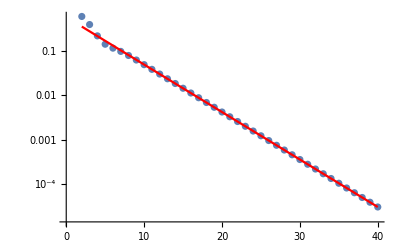

```mathematica
hPData=Table[{l,Sum[hPllrmin8mpmax14[l,m] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.12811629963582085005714201619757334,b→0.2465518506690309084526651263896191}

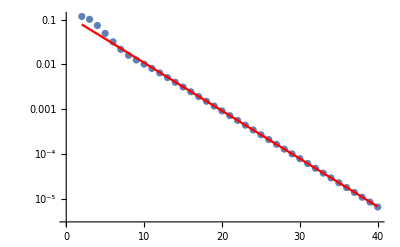

```mathematica
hPData=Table[{l,Sum[hPlmrmin8mpmax14[l,m] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.031793887619512148431696485282540195,b→0.2512270896213903532872765215493815}

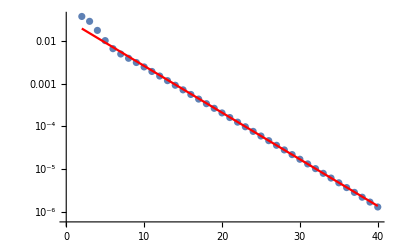

```mathematica
hPData=Table[{l,Sum[hPmmrmin8mpmax14[l,m] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

Checked for all the other indices which give the same kind of answer. One small exception is the m̄ m̄ component which has a weird behaviour towards the very end:

```mathematica
hPData=Table[{l,Sum[hPmbmbrmin8mpmax14[l,m] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.031793887619512148431696485282540195,b→0.2512270896213903532872765215493815}

-Graphics-

##### Check --- large l behaviour mpmax=20

For the pre-computed puncture:

{A→0.7837259761023026709146303247593291121877579761312459,b→0.19265752024989105931347911712517608792831248732894813}

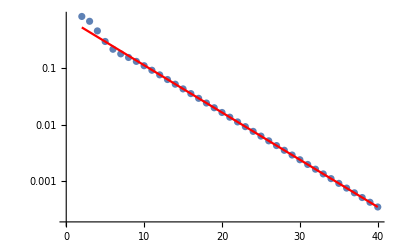

```mathematica
hPData=Table[{l,Sum[hPllrmin8mpmax20[l,m] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.168343953425275346763081384597733200922248944900996684390592275,b→0.193287897444291203433863911363524778377082343065968423134637856}

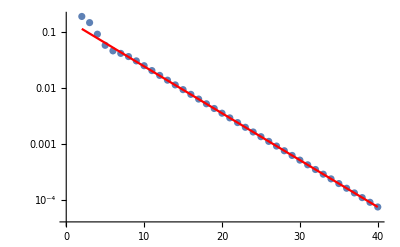

```mathematica
hPData=Table[{l,Sum[hPlmrmin8mpmax20[l,m] SpinWeightedSphericalHarmonicY[1,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.0357318218326894160603805065375144736292011812929985714578182817,b→0.193894783087874578534475437718210416795941315189922989446408987}

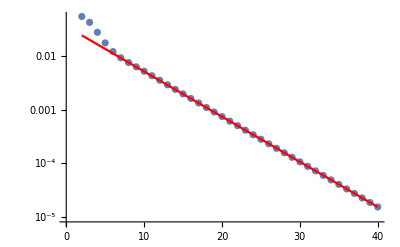

```mathematica
hPData=Table[{l,Sum[hPmmrmin8mpmax20[l,m] SpinWeightedSphericalHarmonicY[2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

Checked for all the other indices which give the same kind of answer. One small exception is the m̄ m̄ component which has a weird behaviour towards the very end:

```mathematica
hPData=Table[{l,Sum[hPmbmbrmin8mpmax20[l,m] SpinWeightedSphericalHarmonicY[-2,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[25;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→0.0357318218326894160603805065375144736292011812929985714578182817,b→0.193894783087874578534475437718210416795941315189922989446408987}

-Graphics-

Not evaluable.

### Tetrad coefficients

```mathematica
Clear[h𝒫ToCoeffRule]
h𝒫ToCoeffRule = {h𝒫[i_][l_, m_][r0] :> cCoeff[i][l,m][0],Derivative[n_][h𝒫[i_][l_, m_]][r0] :> n! cCoeff[i][l,m][n]};
```

```mathematica
Clear[cllCoeff,clnCoeff,clmCoeff,clmbCoeff,cnnCoeff,cnmCoeff,cnmbCoeff,cmmCoeff,cmmbCoeff,cmbmbCoeff]
Do[cllCoeff[l_,m_][n] = SeriesCoefficient[h𝒫ll[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[clnCoeff[l_,m_][n] = SeriesCoefficient[h𝒫ln[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[clmCoeff[l_,m_][n] = SeriesCoefficient[h𝒫lm[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[clmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫lmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cnnCoeff[l_,m_][n] = SeriesCoefficient[h𝒫nn[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cnmCoeff[l_,m_][n] = SeriesCoefficient[h𝒫nm[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cnmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫nmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cmmCoeff[l_,m_][n] = SeriesCoefficient[h𝒫mm[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cmmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫mmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
Do[cmbmbCoeff[l_,m_][n] = SeriesCoefficient[h𝒫mbmb[l,m][r] /. TetradToBLSRule,{r,r0,n}]  /.  h𝒫ToCoeffRule // Simplify[#,Assumptions->simplifyRule] &,{n,0,orderOfPuncture}];
```

Note: the coefficients below are those from the puncture in u slicing! This is because these coefficients are needed when computing corrector tensor using power series expansion,
and this requires stress energy given in u slicing. To make the calculations exact, the factor e^(iωr^*) needs to be gone in expression of the stress-energy, which requires the input for ℰh^P to be given in u slicing as well.

```mathematica
Clear[c1ll,c1ln,c1lm,c1lmb,c1nn,c1nm,c1nmb,c1mm,c1mmb,c1mbmb,
c2ll,c2ln,c2lm,c2lmb,c2nn,c2nm,c2nmb,c2mm,c2mmb,c2mbmb]
myRuleAnalytic = {cCoeff[i_][l_,m_][n_] :> 𝒸AnalyticuCoord[i][l,m][n]}; (*.note u slicing instead of t slicing, which would be 𝒸AnalytictCoord instead. *)
myRuleAbsΔr = {cCoeff[i_][l_,m_][n_] :> 𝒸AbsΔruCoord[i][l,m][n]};
Do[c1ll[l_,m_][n] = cllCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2ll[l_,m_][n] = cllCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1ln[l_,m_][n] = clnCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2ln[l_,m_][n] = clnCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1lm[l_,m_][n] = clmCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2lm[l_,m_][n] = clmCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1lmb[l_,m_][n] = clmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2lmb[l_,m_][n] = clmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1nn[l_,m_][n] = cnnCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2nn[l_,m_][n] = cnnCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1nm[l_,m_][n] = cnmCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2nm[l_,m_][n] = cnmCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1nmb[l_,m_][n] = cnmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2nmb[l_,m_][n] = cnmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1mm[l_,m_][n] = cmmCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2mm[l_,m_][n] = cmmCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1mmb[l_,m_][n] = cmmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2mmb[l_,m_][n] = cmmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
Do[c1mbmb[l_,m_][n] = cmbmbCoeff[l,m][n] /. myRuleAnalytic,{n,0,orderOfPuncture}];
Do[c2mbmb[l_,m_][n] = cmbmbCoeff[l,m][n] /. myRuleAbsΔr,{n,0,orderOfPuncture}];
```

```mathematica
(*DumpSave[FileNameJoin[{NotebookDirectory[],"cCoeff_r010_M1_n4_l2_uslicing.mx"}],{𝒸AnalytictCoord,𝒸AbsΔrtCoord,𝒸AnalyticuCoord,𝒸AbsΔruCoord,c1ll,c1ln,c1lm,c1lmb,c1nn,c1nm,c1nmb,c1mm,c1mmb,c1mbmb,
c2ll,c2ln,c2lm,c2lmb,c2nn,c2nm,c2nmb,c2mm,c2mmb,c2mbmb}];*)
```

## Corrector tensor --- Power-series exact

## Read Me

This calculation of the corrector tensors is exact, but relies on a power-series expansion of the puncture.
Fundamentally, this was given up in favor of a numerical approach, because the resulting corrector tensors’ l modes do not converge away from the particle (which is needed for second order).

In order to run this section, you actually do not need the coefficient of the power series expansion, as the result is written in terms of them.
You do however need the expression of the stress energy in terms of the metric. The section “Rules” will then replace the metric perturbation as (~(r-r_0))^aExp, and then compute the integrals exactly.
Note that in general, there are three different sources of contributions: distributional contrbutions (at r_min), pieces (~Δr)^n and pieces |Δr| Δr^(n-1), see “Theory” section for more details.

The aExp then need to be run from 0 to whatever order you want. If you want to use these results to then compute the coefficients of Ξ, you only need to go to aExp=1, as higher order terms where empirically checked to not contribute (up to aExp=4).

```mathematica
aExp=0;
```

## Theory

General corrector tensor is: x_ab = 2 m_((a)(m̄)_(b)) x_(m m̄) - 2 l_((a)(m̄)_(b)) x_nm-2 l_((a)m_(b)) x_(n m̄)+l_a l_b x_nn, see 1908.09095 eq. (55). Defined to satisfy (T_ab-(ℰx)_ab)l^a=0.
Note that x_la=x_mm=x_(m̄ m̄)=0. Only non-trivial pieces are x_nn, x_nm,x_(n m̄),x_mm. They are given by ODEs, see 2108.04273, eq. (56)-(61), and 1908.09095, eq. (58)-(61). See also comment on page 38.

In general, the stress energy is of the schematic form T_ab ~ ∑_n c_1 Δr^n + c_2 |Δr| Δr^(n-1).
We compute the contribution of each term separately.
First term is simple to implement. For second term, we need to be careful if the integration crosses the particle.
In general, consider piecewise function f̃(x) = Piecewise[{{f(x), x≤0}, {g(x), x>0}}], where f(0)=g(0). Define F(x) := ∫f(x)dx, G(x) := ∫g(x)dx.
Then, F̃(x) := ∫_a^x f̃(x)dx = Piecewise[{{F(x)-F(a), x≤0}, {-F(a)+F(0)+G(x)-G(0), x>0}}]. Easy to check that F̃(x) is continuous at x=0.

For the contribution of the delta function and its derivative, we will work withe computing: I:=∫_-^+ dρ_2∫_-^ρ_2 T_ll/ρ_1^4 dρ_1, where T_ll=f(r)δ(r_min-r)+g(r)δ'(r_min-r)=f(r)δ(r-r_min)-g(r)δ'(r-r_min) and we denote 
- := r_min^-, + := r_max^+.
δ contribution:
 ∫_-^+ dr_2 r_2^-2∫_-^r_2 r_1^2 f(r_1)δ(r_1-r_min) dr_1= ∫_-^+ dr_2 r_2^-2 r_min^2 f(r_min)H(r_2-r_min) = r_min^2 f(r_min)(r_max-r_min)/(r_max r_min), where H(x) is the usual Heaviside function.
 δ’ contribution:
 -∫_-^+ dr_2 r_2^-2([r_1^2 g(r_1)δ(r_1-r_min)]_-^r_2+∫_-^r_2 (r_1^2 g(r_1))'δ(r_1-r_min) dr_1)
= -∫_-^+ dr_2 r_2^-2(r_2^2 g(r_2)δ(r_2-r_min)+(r_2^2 g(r_2))'H(r_2-r_min))
= -g(r_min)+(r^2 g(r))')|_r_min∫_r_min^+ dr_2 r_2^-2
= -g(r_min)+(r^2 g(r))')|_r_min(r_max-r_min)/(r_max r_min).

So, full contribution for delta functions and derivatives at r_min is:  r_min^2 f(r_min)(r_max-r_min)/(r_max r_min)-g(r_min)+(2 r_min g(r_min)+r_min^2 g'(r_min))(r_max-r_min)/(r_max r_min) = (r_min(r_max-r_min) (f(r_min)+g'(r_min))+(r_max-2 r_min)g(r_min))/r_max.
Similarly, for contribution at r_max, H(r-r_max) means most integrals vanish. In fact, only term that survives is the “boundary term” coming from δ’. 
So, full contribution for delta functions and derivatives at r_max is:   g(r_max)

## Rules

```mathematica
h𝒫TaylorAnalyticRule = {
h𝒫ll[l_,m_] :> Function[r,𝒸1ℓℓ[l,m,aExp] (r-r0)^aExp],
h𝒫ln[l_,m_] :> Function[r,𝒸1ℓ𝓃[l,m,aExp] (r-r0)^aExp],
h𝒫lm[l_,m_] :> Function[r,𝒸1ℓ𝓂[l,m,aExp] (r-r0)^aExp],
h𝒫lmb[l_,m_] :> Function[r,𝒸1ℓ𝓂𝒷[l,m,aExp] (r-r0)^aExp],
h𝒫nn[l_,m_] :> Function[r,𝒸1𝓃𝓃[l,m,aExp] (r-r0)^aExp],
h𝒫nm[l_,m_] :> Function[r,𝒸1𝓃𝓂[l,m,aExp] (r-r0)^aExp],
h𝒫nmb[l_,m_] :> Function[r,𝒸1𝓃𝓂𝒷[l,m,aExp] (r-r0)^aExp],
h𝒫mm[l_,m_] :> Function[r,𝒸1𝓂𝓂[l,m,aExp] (r-r0)^aExp],
h𝒫mmb[l_,m_] :> Function[r,𝒸1𝓂𝓂𝒷[l,m,aExp] (r-r0)^aExp],
h𝒫mbmb[l_,m_] :> Function[r,𝒸1𝓂𝒷𝓂𝒷[l,m,aExp] (r-r0)^aExp]};
h𝒫TaylorAbsΔrRule ={
h𝒫ll[l,m] :> Function[r,𝒸2ℓℓ[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫ln[l,m] :> Function[r,𝒸2ℓ𝓃[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫lm[l,m] :> Function[r,𝒸2ℓ𝓂[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫lmb[l,m] :> Function[r,𝒸2ℓ𝓂𝒷[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫nn[l,m] :> Function[r,𝒸2𝓃𝓃[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫nm[l,m] :> Function[r,𝒸2𝓃𝓂[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫nmb[l,m] :> Function[r,𝒸2𝓃𝓂𝒷[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫mm[l,m] :> Function[r,𝒸2𝓂𝓂[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫mmb[l,m] :> Function[r,𝒸2𝓂𝓂𝒷[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}],
h𝒫mbmb[l,m] :> Function[r,𝒸2𝓂𝒷𝓂𝒷[l,m,aExp] {-(r-r0)^aExp,(r-r0)^aExp}]};
rToρRule = {r -> rOfρK[ρ], r0 -> rOfρK[ρ0], rmin -> rOfρK[ρmin], rmax -> rOfρK[ρmax]};
ρTorRule = {r -> rOfρK[ρ],ρ0 -> ρOfrK[r0],ρmin -> ρOfrK[rmin],ρmax -> ρOfrK[rmax]};
coeffRule = {
𝒸1ℓℓ[l_,m_,n_] :> c1ll[l,m][n],
𝒸1ℓ𝓃[l_,m_,n_] :> c1ln[l,m][n],
𝒸1ℓ𝓂[l_,m_,n_] :> c1lm[l,m][n],
𝒸1ℓ𝓂𝒷[l_,m_,n_] :> c1lmb[l,m][n],
𝒸1𝓃𝓃[l_,m_,n_] :> c1nn[l,m][n],
𝒸1𝓃𝓂[l_,m_,n_] :> c1nm[l,m][n],
𝒸1𝓃𝓂𝒷[l_,m_,n_] :> c1nmb[l,m][n],
𝒸1𝓂𝓂[l_,m_,n_] :> c1mm[l,m][n],
𝒸1𝓂𝓂𝒷[l_,m_,n_] :> c1mmb[l,m][n],
𝒸1𝓂𝒷𝓂𝒷[l_,m_,n_] :> c1mbmb[l,m][n],

𝒸2ℓℓ[l_,m_,n_] :> c2ll[l,m][n],
𝒸2ℓ𝓃[l_,m_,n_] :> c2ln[l,m][n],
𝒸2ℓ𝓂[l_,m_,n_] :> c2lm[l,m][n],
𝒸2ℓ𝓂𝒷[l_,m_,n_] :> c2lmb[l,m][n],
𝒸2𝓃𝓃[l_,m_,n_] :> c2nn[l,m][n],
𝒸2𝓃𝓂[l_,m_,n_] :> c2nm[l,m][n],
𝒸2𝓃𝓂𝒷[l_,m_,n_] :> c2nmb[l,m][n],
𝒸2𝓂𝓂[l_,m_,n_] :> c2mm[l,m][n],
𝒸2𝓂𝓂𝒷[l_,m_,n_] :> c2mmb[l,m][n],
𝒸2𝓂𝒷𝓂𝒷[l_,m_,n_] :> c2mbmb[l,m][n]};
```

```mathematica
CoeffCollectRule = {𝒸1ℓℓ[l_,m_,n_],𝒸1ℓ𝓃[l_,m_,n_],𝒸1ℓ𝓂[l_,m_,n_],𝒸1ℓ𝓂𝒷[l_,m_,n_],𝒸1𝓃𝓃[l_,m_,n_],𝒸1𝓃𝓂[l_,m_,n_],𝒸1𝓃𝓂𝒷[l_,m_,n_],𝒸1𝓂𝓂[l_,m_,n_],𝒸1𝓂𝓂𝒷[l_,m_,n_],𝒸1𝓂𝒷𝓂𝒷[l_,m_,n_],
𝒸2ℓℓ[l_,m_,n_],𝒸2ℓ𝓃[l_,m_,n_],𝒸2ℓ𝓂[l_,m_,n_],𝒸2ℓ𝓂𝒷[l_,m_,n_],𝒸2𝓃𝓃[l_,m_,n_],𝒸2𝓃𝓂[l_,m_,n_],𝒸2𝓃𝓂𝒷[l_,m_,n_],𝒸2𝓂𝓂[l_,m_,n_],𝒸2𝓂𝓂𝒷[l_,m_,n_],𝒸2𝓂𝒷𝓂𝒷[l_,m_,n_]};
```

## x_(m m̄)

### T_ll contribution

#### Analytic part

```mathematica
Clear[TllAnalyticTerm]
TllAnalyticTerm[l_,m_,aExp][ρ_] =TllWorldtubePiece[l,m][r] /. h𝒫TaylorAnalyticRule /. rToρRule  /. Ωφ2Rule// Simplify[#,Assumptions->simplifyRule]&
```

1/2 ρ ((l ρ+l^2 ρ+2 ⅈ m Ωφ) 𝒸1ℓℓ[l,m,0]+√2 √(l (1+l)) ρ (𝒸1ℓ𝓂[l,m,0]-𝒸1ℓ𝓂𝒷[l,m,0]))

```mathematica
Clear[xmmbFirstIndefIntegralAnalyticTerm,xmmbSecondIndefIntegralAnalyticTerm,TllAnalyticTermContribution]
xmmbFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[ρ1^(-4) TllAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,{ρ2<0}] &];
xmmbSecondIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
TllAnalyticTermContribution[l_,m_,aExp][ρ_] =Collect[xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρ] - xmmbSecondIndefIntegralAnalyticTermAtρmin -xmmbFirstIndefIntegralAnalyticTermAtρmin (ρ-ρmin), CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&]
(*Clear[TllAnalyticTerm]*)
```

-xmmbSecondIndefIntegralAnalyticTermAtρmin+xmmbFirstIndefIntegralAnalyticTermAtρmin (-ρ+ρmin)+((ⅈ m Ωφ)/(2 ρ)-1/2 l (1+l) Log[ρ]) 𝒸1ℓℓ[l,m,0]-(√(l (1+l)) Log[ρ] 𝒸1ℓ𝓂[l,m,0])/(√2)+(√(l (1+l)) Log[ρ] 𝒸1ℓ𝓂𝒷[l,m,0])/(√2)

#### |Δr| part

```mathematica
Clear[TllAbsΔrTerm]
TllAbsΔrTerm[l_,m_,aExp][ρ_] =TllWorldtubePiece[l,m][r] /. h𝒫TaylorAbsΔrRule /. rToρRule  /. Ωφ2Rule // Simplify[#,Assumptions->simplifyRule]&
```

{-1/2 ρ ((l ρ+l^2 ρ+2 ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]+√2 √(l (1+l)) ρ (𝒸2ℓ𝓂[l,m,0]-𝒸2ℓ𝓂𝒷[l,m,0])),1/2 ρ ((l ρ+l^2 ρ+2 ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]+√2 √(l (1+l)) ρ (𝒸2ℓ𝓂[l,m,0]-𝒸2ℓ𝓂𝒷[l,m,0]))}

```mathematica
Clear[xmmbFirstIntegralAbsΔrTerm,xmmbFirstIndefIntegralAbsΔrTerm,xmmbFirstIntegralAbsΔrTerm,xmmbSecondIndefIntegralAbsΔrTerm,TllAbsΔrTermContribution]
xmmbFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[ρ1^(-4) TllAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2, CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&];
xmmbFirstIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[{xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[1]]-xmmbFirstIndefIntegralAbsΔrTermAtρmin,
xmmbFirstIndefIntegralAbsΔrTermAtρ0Left-xmmbFirstIndefIntegralAbsΔrTermAtρmin+xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[2]]-xmmbFirstIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule, Simplify];
xmmbSecondIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[xmmbFirstIntegralAbsΔrTerm[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
TllAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-xmmbSecondIndefIntegralAbsΔrTermAtρmin,
xmmbSecondIndefIntegralAbsΔrTermAtρ0Left-xmmbSecondIndefIntegralAbsΔrTermAtρmin+xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-xmmbSecondIndefIntegralAbsΔrTermAtρ0Right}, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&]
(*Clear[TllAbsΔrTerm,xmmbFirstIntegralAbsΔrTerm]*)
```

{-xmmbSecondIndefIntegralAbsΔrTermAtρmin-xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ+1/2 (-(ⅈ m Ωφ)/ρ+l (1+l) Log[ρ]) 𝒸2ℓℓ[l,m,0]+(√(l (1+l)) Log[ρ] 𝒸2ℓ𝓂[l,m,0])/(√2)-(√(l (1+l)) Log[ρ] 𝒸2ℓ𝓂𝒷[l,m,0])/(√2),xmmbSecondIndefIntegralAbsΔrTermAtρ0Left-xmmbSecondIndefIntegralAbsΔrTermAtρ0Right-xmmbSecondIndefIntegralAbsΔrTermAtρmin+(xmmbFirstIndefIntegralAbsΔrTermAtρ0Left-xmmbFirstIndefIntegralAbsΔrTermAtρ0Right-xmmbFirstIndefIntegralAbsΔrTermAtρmin) ρ+((ⅈ m Ωφ)/(2 ρ)-1/2 l (1+l) Log[ρ]) 𝒸2ℓℓ[l,m,0]-(√(l (1+l)) Log[ρ] 𝒸2ℓ𝓂[l,m,0])/(√2)+(√(l (1+l)) Log[ρ] 𝒸2ℓ𝓂𝒷[l,m,0])/(√2)}

#### Distributional part

The coefficients are the contributions in the metric at the order we are considering. Note that the coefficients are always evaluated at r=rmin,
so always to the left of the particle. So, for the contribution due to |Δr|, can evaluate at that point.

```mathematica
Clear[TllDistrContributionAtRminTMP,TllDistrContributionAtRmin]
TllDistrContributionAtRminTMP[l_,m_,aExp][ρ_] = 
((ρ-ρmin) TllδCoeff[l,m]+(2 ρ-ρmin) ρmin TllδpCoeff[l,m])/ρmin^2/. TllδCoeff[l_,m_] -> TllδRminPiece[l,m] /. TllδpCoeff[l_,m_] -> TllδpRminPiece[l,m]  // Simplify;
TllDistrContributionAtRmin[l_,m_,aExp][ρ_] = (TllDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAnalyticRule) +
			(TllDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAbsΔrRule)[[1]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
Clear[TllDistrContributionAtRminTMP]
(* Assuming[{ϵ>0,rmin>0,r1>0,r>rmin},Simplify@Integrate[r2^(-2)r1^2 (TllδCoeff[rmin] DiracDelta[r1-rmin]+TllδpCoeff[rmin] DiracDelta'[r1-rmin]),{r2,rmin-ϵ,r},{r1,rmin-ϵ,r2}]]  /. r -> -1/ρ /. rmin -> -1/ρmin // Simplify  *)
```

1/(2 ρmin)(-2 (2 ρ-ρmin) 𝒸1𝓂𝓂𝒷[l,m,0]+(ρ-ρmin) (-√2 √(l (1+l)) 𝒸1ℓ𝓂[l,m,0]+√2 √(l (1+l)) 𝒸1ℓ𝓂𝒷[l,m,0]+4 (𝒸1ℓ𝓃[l,m,0]+𝒸1𝓂𝓂𝒷[l,m,0]))+2 (2 ρ-ρmin) 𝒸2𝓂𝓂𝒷[l,m,0]+(ρ-ρmin) (√2 √(l (1+l)) 𝒸2ℓ𝓂[l,m,0]-√2 √(l (1+l)) 𝒸2ℓ𝓂𝒷[l,m,0]-4 (𝒸2ℓ𝓃[l,m,0]+𝒸2𝓂𝓂𝒷[l,m,0])))

### x_(m m̄)

```mathematica
xmmbAnalyticTerm[l_,m_,aExp][ρ_] = Collect[TllAnalyticTermContribution[l,m,aExp][ρ]+ TllDistrContributionAtRmin[l,m,aExp][ρ], CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];
xmmbAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[TllAbsΔrTermContribution[l,m,aExp][ρ]  //.
{xmmbFirstIndefIntegralAbsΔrTermAtρ0Left -> xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],xmmbFirstIndefIntegralAbsΔrTermAtρ0Right -> xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],xmmbSecondIndefIntegralAbsΔrTermAtρ0Left -> xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρ0Right -> xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]]}, CoeffCollectRule, FullSimplify[#,Assumptions->simplifyRule] &];
xmmbTermNoCoeffRule[l_,m_,aExp][r_] = (* This is for plotting *)Module[{ρ =ρOfrK[r]},xmmbAnalyticTerm[l,m,aExp][ρ]+Piecewise[{{xmmbAbsΔrTerm[l,m,aExp][ρ][[1]],ρ ≤ ρ0},{xmmbAbsΔrTerm[l,m,aExp][ρ][[2]],ρ > ρ0}}] //. 
{xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xmmbSecondIndefIntegralAnalyticTermAtρmin -> xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρmin -> xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]]}];
(*Clear[TllAnalyticTermContribution,TllAbsΔrTermContribution,TllDistrContribution]*)
```

## x_nm

### T_lm contribution

#### Analytic part

```mathematica
Clear[TlmAnalyticTerm]
TlmAnalyticTerm[l_,m_,aExp][ρ_]  =TlmWorldtubePiece[l,m][r] /. h𝒫TaylorAnalyticRule /. rToρRule  /. Ωφ2Rule // FullSimplify[#,Assumptions->simplifyRule]&
```

1/(4 √2)ρ (2 √(l (1+l)) (2 M ρ^2+ⅈ m Ωφ) 𝒸1ℓℓ[l,m,0]+√2 (ρ (-2+l+l^2+4 M ρ)+6 ⅈ m Ωφ) 𝒸1ℓ𝓂[l,m,0]+4 √(l (1+l)) ρ 𝒸1ℓ𝓃[l,m,0]+√2 ρ (l (1+l) 𝒸1ℓ𝓂𝒷[l,m,0]+4 𝒸1𝓃𝓂[l,m,0]))

```mathematica
Clear[xnmFirstIndefIntegralAnalyticTerm,xnmSecondIndefIntegralAnalyticTerm,TlmAnalyticTermContribution]
xnmFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) TlmAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&];
xnmSecondIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = 
Collect[Integrate[ρ2^(-4)/4 xnmFirstIndefIntegralAnalyticTerm[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
TlmAnalyticTermContribution[l_,m_,aExp][ρ_] =Collect[xnmSecondIndefIntegralAnalyticTerm[l,m,aExp][ρ] - xnmSecondIndefIntegralAnalyticTermAtρmin +xnmFirstIndefIntegralAnalyticTermAtρmin (ρ^(-3)-ρmin^(-3))/12, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&]
(*Clear[TlmAnalyticTerm]*)
```

-xnmSecondIndefIntegralAnalyticTermAtρmin+1/12 xnmFirstIndefIntegralAnalyticTermAtρmin (1/ρ^3-1/ρmin^3)-(√(l (1+l)) (9 M ρ^2+ⅈ m Ωφ+3 ⅈ m Ωφ Log[ρ]) 𝒸1ℓℓ[l,m,0])/(36 √2 ρ^3)-((3 (-2+l+l^2) ρ+12 M ρ^2+4 ⅈ m Ωφ+12 ⅈ m Ωφ Log[ρ]) 𝒸1ℓ𝓂[l,m,0])/(48 ρ^3)-(l (1+l) 𝒸1ℓ𝓂𝒷[l,m,0])/(16 ρ^2)-(√(l (1+l)) 𝒸1ℓ𝓃[l,m,0])/(4 √2 ρ^2)-𝒸1𝓃𝓂[l,m,0]/(4 ρ^2)

#### |Δr| part

```mathematica
Clear[TlmAbsΔrTerm]
TlmAbsΔrTerm[l_,m_,aExp][ρ_]=TlmWorldtubePiece[l,m][r] /. h𝒫TaylorAbsΔrRule /. rToρRule  /. Ωφ2Rule// Simplify[#,Assumptions->simplifyRule]&
```

{-1/(4 √2)ρ (2 √(l (1+l)) (2 M ρ^2+ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]+√2 ((-2+l+l^2) ρ+4 M ρ^2+6 ⅈ m Ωφ) 𝒸2ℓ𝓂[l,m,0]+ρ (√2 l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0]+4 √(l (1+l)) 𝒸2ℓ𝓃[l,m,0]+4 √2 𝒸2𝓃𝓂[l,m,0])),1/(4 √2)ρ (2 √(l (1+l)) (2 M ρ^2+ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]+√2 ((-2+l+l^2) ρ+4 M ρ^2+6 ⅈ m Ωφ) 𝒸2ℓ𝓂[l,m,0]+ρ (√2 l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0]+4 √(l (1+l)) 𝒸2ℓ𝓃[l,m,0]+4 √2 𝒸2𝓃𝓂[l,m,0]))}

```mathematica
Clear[xnmFirstIntegralAbsΔrTerm,xnmFirstIndefIntegralAbsΔrTerm,xnmFirstIntegralAbsΔrTerm,xnmSecondIndefIntegralAbsΔrTerm,TlmAbsΔrTermContribution]
xnmFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) TlmAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&];
xnmFirstIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[{xnmFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[1]]-xnmFirstIndefIntegralAbsΔrTermAtρmin,
xnmFirstIndefIntegralAbsΔrTermAtρ0Left-xnmFirstIndefIntegralAbsΔrTermAtρmin+xnmFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[2]]-xnmFirstIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule, Simplify];
xnmSecondIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ2^(-4)/4 xnmFirstIntegralAbsΔrTerm[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ, CoeffCollectRule, Simplify];
TlmAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{xnmSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-xnmSecondIndefIntegralAbsΔrTermAtρmin,
xnmSecondIndefIntegralAbsΔrTermAtρ0Left-xnmSecondIndefIntegralAbsΔrTermAtρmin+xnmSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-xnmSecondIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&]
(*Clear[TlmAbsΔrTerm]*)
```

{-xnmSecondIndefIntegralAbsΔrTermAtρmin+xnmFirstIndefIntegralAbsΔrTermAtρmin/(12 ρ^3)+(√(l (1+l)) (9 M ρ^2+ⅈ m Ωφ+3 ⅈ m Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(36 √2 ρ^3)+((3 (-2+l+l^2) ρ+12 M ρ^2+4 ⅈ m Ωφ+12 ⅈ m Ωφ Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(48 ρ^3)+(l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ^2)+(√(l (1+l)) 𝒸2ℓ𝓃[l,m,0])/(4 √2 ρ^2)+𝒸2𝓃𝓂[l,m,0]/(4 ρ^2),xnmSecondIndefIntegralAbsΔrTermAtρ0Left-xnmSecondIndefIntegralAbsΔrTermAtρ0Right-xnmSecondIndefIntegralAbsΔrTermAtρmin+(-xnmFirstIndefIntegralAbsΔrTermAtρ0Left+xnmFirstIndefIntegralAbsΔrTermAtρ0Right+xnmFirstIndefIntegralAbsΔrTermAtρmin)/(12 ρ^3)-(√(l (1+l)) (9 M ρ^2+ⅈ m Ωφ+3 ⅈ m Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(36 √2 ρ^3)-((3 (-2+l+l^2) ρ+12 M ρ^2+4 ⅈ m Ωφ+12 ⅈ m Ωφ Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(48 ρ^3)-(l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ^2)-(√(l (1+l)) 𝒸2ℓ𝓃[l,m,0])/(4 √2 ρ^2)-𝒸2𝓃𝓂[l,m,0]/(4 ρ^2)}

#### Distributional part

```mathematica
Clear[TlmDistrContributionAtRminTMP,TlmDistrContributionAtRmin]
TlmDistrContributionAtRminTMP[l_,m_,aExp][ρ_] = 
((ρ^3-ρmin^3) TlmδCoeff[l,m]+3 ρ^3 ρmin TlmδpCoeff[l,m])/(6 ρ^3 ρmin^3)/. TlmδCoeff[l_,m_] -> TlmδRminPiece[l,m] /. TlmδpCoeff[l_,m_] -> TlmδpRminPiece[l,m]  // Simplify;
TlmDistrContributionAtRmin[l_,m_,aExp][ρ_] = (TlmDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAnalyticRule) +
			(TlmDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAbsΔrRule)[[1]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
Clear[TlmDistrContributionAtRminTMP]
(* Assuming[{ϵ>0,rmin>0,r1>0,r>rmin},Simplify@Integrate[r2^2/2 (TlmδCoeff[rmin] DiracDelta[r1-rmin]+TlmδpCoeff[rmin] DiracDelta'[r1-rmin]),{r2,rmin-ϵ,r},{r1,rmin-ϵ,r2}]]  /. r -> -1/ρ /. rmin -> -1/ρmin // Factor// Simplify *)
```

1/(48 ρ^3 ρmin^3)(-6 ρ^3 ρmin ((1+2 M ρmin) 𝒸1ℓ𝓂[l,m,0]+2 𝒸1𝓃𝓂[l,m,0])+(ρ^3-ρmin^3) (√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸1ℓℓ[l,m,0]+4 (ρmin+M ρmin^2-ⅈ m Ωφ) 𝒸1ℓ𝓂[l,m,0]+2 ρmin (√2 √(l (1+l)) 𝒸1ℓ𝓃[l,m,0]-√2 √(-2+l+l^2) 𝒸1𝓂𝓂[l,m,0]-√2 √(l (1+l)) 𝒸1𝓂𝓂𝒷[l,m,0]+4 𝒸1𝓃𝓂[l,m,0]))+6 ρ^3 ρmin ((1+2 M ρmin) 𝒸2ℓ𝓂[l,m,0]+2 𝒸2𝓃𝓂[l,m,0])-(ρ^3-ρmin^3) (√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸2ℓℓ[l,m,0]+4 (ρmin+M ρmin^2-ⅈ m Ωφ) 𝒸2ℓ𝓂[l,m,0]+2 ρmin (√2 √(l (1+l)) 𝒸2ℓ𝓃[l,m,0]-√2 √(-2+l+l^2) 𝒸2𝓂𝓂[l,m,0]-√2 √(l (1+l)) 𝒸2𝓂𝓂𝒷[l,m,0]+4 𝒸2𝓃𝓂[l,m,0])))

### 𝒩x_(m m̄) contribution

We split the contribution between the smooth and |Δr| parts of x_(m m̄).

```mathematica
Clear[þNullKρ,𝒩NullK,ðCKρ]
þNullKρ = ρ^2 D[#,ρ] &;
ðCKρ[s_,l_] = (# ρ √(((l-s)(l+s+1))/2)) &; 
𝒩NullK[s_,l_] = -1/2 (þNullKρ[ðCKρ[s,l][#]]-ρ ðCKρ[s,l][#]) &;
```

#### Smooth piece

```mathematica
Clear[𝒩xmmbAnalyticTerm,𝒩xmmbFirstIndefIntegralAnalyticTerm,𝒩xmmbSecondIndefIntegralAnalyticTerm,𝒩xmmbAnalyticTermContribution]
𝒩xmmbAnalyticTerm[l_,m_,aExp][ρ_] = Collect[𝒩NullK[0,l][xmmbAnalyticTerm[l,m,aExp][ρ]] /.rToρRule, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];

𝒩xmmbFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) 𝒩xmmbAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];
𝒩xmmbSecondIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ2^(-4)/4 𝒩xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρ2], ρ2] /. ρ2 -> ρ, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
𝒩xmmbAnalyticTermContribution[l_,m_,aExp][ρ_] = Collect[𝒩xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρ]-𝒩xmmbSecondIndefIntegralAnalyticTermAtρmin+𝒩xmmbFirstIndefIntegralAnalyticTermAtρmin (ρ^(-3)-ρmin^(-3))/12, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &]
Clear[𝒩xmmbAnalyticTerm]
```

-𝒩xmmbSecondIndefIntegralAnalyticTermAtρmin+1/48 ((4 𝒩xmmbFirstIndefIntegralAnalyticTermAtρmin)/ρ^3-(3 √2 √(l (1+l)) xmmbFirstIndefIntegralAnalyticTermAtρmin)/ρ-(4 𝒩xmmbFirstIndefIntegralAnalyticTermAtρmin)/ρmin^3)-(√(l (1+l)) (9 l ρ+9 l^2 ρ+2 ⅈ m Ωφ+6 ⅈ m Ωφ Log[ρ]) 𝒸1ℓℓ[l,m,0])/(144 √2 ρ^3)-(l (1+l) (ρ+ρmin) 𝒸1ℓ𝓂[l,m,0])/(16 ρ^2 ρmin)+(l (1+l) (ρ+ρmin) 𝒸1ℓ𝓂𝒷[l,m,0])/(16 ρ^2 ρmin)+(√(l (1+l)) 𝒸1ℓ𝓃[l,m,0])/(4 √2 ρ ρmin)+(l (1+l) 𝒸2ℓ𝓂[l,m,0])/(16 ρ ρmin)-(l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ ρmin)-(√(l (1+l)) 𝒸2ℓ𝓃[l,m,0])/(4 √2 ρ ρmin)

#### |Δr| piece

```mathematica
Clear[𝒩xmmbAbsΔrTerm,𝒩xmmbFirstIndefIntegralAbsΔrTerm,𝒩xmmbSecondIndefIntegralAbsΔrTerm,𝒩xmmbAbsΔrTermContribution]
𝒩xmmbAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[𝒩NullK[0,l][xmmbAbsΔrTerm[l,m,aExp][ρ]] /.rToρRule, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];

𝒩xmmbFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) 𝒩xmmbAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2, CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];
𝒩xmmbFirstIntegralΔrPiece[l_,m_,aExp][ρ2_] = Collect[{𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[1]]-𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin,
𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Left-𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin+𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[2]]-𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Right}, CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];
𝒩xmmbSecondIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ2^(-4)/4 𝒩xmmbFirstIntegralΔrPiece[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ, CoeffCollectRule, Simplify];
𝒩xmmbAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin,
𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Left-𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin+𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Right}, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &]
Clear[𝒩xmmbAbsΔrTerm]
```

{-𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin+(4 𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin-3 √2 √(l (1+l)) xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^2)/(48 ρ^3)+(√(l (1+l)) (9 l ρ+9 l^2 ρ+2 ⅈ m Ωφ+6 ⅈ m Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(144 √2 ρ^3)+(l (1+l) 𝒸2ℓ𝓂[l,m,0])/(16 ρ^2)-(l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ^2),𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Left-𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Right-𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin+1/(48 ρ^3)(-4 𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Left+4 𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Right+4 𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin-3 √2 √(l (1+l)) xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^2)+(√(l (1+l)) (-9 l ρ ρ0 (-2 ρ+ρ0)-9 l^2 ρ ρ0 (-2 ρ+ρ0)-2 ⅈ m (-9 ρ^2+ρ0^2) Ωφ-6 ⅈ m ρ0^2 Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(144 √2 ρ^3 ρ0^2)-(l (1+l) (-2 ρ+ρ0) 𝒸2ℓ𝓂[l,m,0])/(16 ρ^2 ρ0)+(l (1+l) (-2 ρ+ρ0) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ^2 ρ0)}

### x_nm

```mathematica
(*Clear[xnmAnalyticTerm,xnmAbsΔrTerm,xnm]*)
xnmAnalyticTerm[l_,m_,aExp][ρ_] = Collect[4ρ^2 (TlmAnalyticTermContribution[l,m,aExp][ρ]+ TlmDistrContributionAtRmin[l,m,aExp][ρ] + 𝒩xmmbAnalyticTermContribution[l,m,aExp][ρ]), CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];
xnmAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[4 ρ^2 (TlmAbsΔrTermContribution[l,m,aExp][ρ] + 𝒩xmmbAbsΔrTermContribution[l,m,aExp][ρ]) //.
{xnmFirstIndefIntegralAbsΔrTermAtρ0Left -> xnmFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],xnmFirstIndefIntegralAbsΔrTermAtρ0Right -> xnmFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],xnmSecondIndefIntegralAbsΔrTermAtρ0Left -> xnmSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],xnmSecondIndefIntegralAbsΔrTermAtρ0Right -> xnmSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],

𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Left -> 𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Right -> 𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Left -> 𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Right -> 𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]]}, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
xnmTermNoCoeffRule[l_,m_,aExp][r_] = Module[{ρ = ρOfrK[r]},xnmAnalyticTerm[l,m,aExp][ρ]+Piecewise[{{xnmAbsΔrTerm[l,m,aExp][ρ][[1]],ρ ≤ ρ0},{xnmAbsΔrTerm[l,m,aExp][ρ][[2]],ρ > ρ0}}] //. 
{xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xmmbSecondIndefIntegralAnalyticTermAtρmin -> xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρmin -> xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

xnmFirstIndefIntegralAnalyticTermAtρmin -> xnmFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xnmSecondIndefIntegralAnalyticTermAtρmin -> xnmSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xnmFirstIndefIntegralAbsΔrTermAtρmin -> xnmFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xnmSecondIndefIntegralAbsΔrTermAtρmin -> xnmSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

𝒩xmmbFirstIndefIntegralAnalyticTermAtρmin -> 𝒩xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],𝒩xmmbSecondIndefIntegralAnalyticTermAtρmin -> 𝒩xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin -> 𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin -> 𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]]}];
(*Clear[TlmAnalyticTermContribution,TlmAbsΔrTermContribution,TlmDistrContributionAtRmin,𝒩xmmbAnalyticTermContribution,𝒩xmmbAbsΔrTermContribution]*)
```

## x_(n m̄)

### T_(l m̄) contribution

#### Analytic part

```mathematica
Clear[TlmbAnalyticTerm]
TlmbAnalyticTerm[l_,m_,aExp][ρ_]  =TlmbWorldtubePiece[l,m][r] /. h𝒫TaylorAnalyticRule /. rToρRule  /. Ωφ2Rule // FullSimplify[#,Assumptions->simplifyRule]&
```

1/4 ρ (-√2 √(l (1+l)) (2 M ρ^2+ⅈ m Ωφ) 𝒸1ℓℓ[l,m,0]+l (1+l) ρ 𝒸1ℓ𝓂[l,m,0]+(ρ (-2+l+l^2+4 M ρ)+6 ⅈ m Ωφ) 𝒸1ℓ𝓂𝒷[l,m,0]-2 √2 √(l (1+l)) ρ 𝒸1ℓ𝓃[l,m,0]+4 ρ 𝒸1𝓃𝓂𝒷[l,m,0])

```mathematica
Clear[xnmbFirstIndefIntegralAnalyticTerm,xnmbSecondIndefIntegralAnalyticTerm,TlmbAnalyticTermContribution]
xnmbFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) TlmbAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&];
xnmbSecondIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ2^(-4)/4 xnmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
TlmbAnalyticTermContribution[l_,m_,aExp][ρ_] =Collect[xnmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρ] - xnmbSecondIndefIntegralAnalyticTermAtρmin +xnmbFirstIndefIntegralAnalyticTermAtρmin (ρ^(-3)-ρmin^(-3))/12, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&]
(*Clear[TlmbAnalyticTerm]*)
```

-xnmbSecondIndefIntegralAnalyticTermAtρmin+1/12 xnmbFirstIndefIntegralAnalyticTermAtρmin (1/ρ^3-1/ρmin^3)+(√(l (1+l)) (9 M ρ^2+ⅈ m Ωφ+3 ⅈ m Ωφ Log[ρ]) 𝒸1ℓℓ[l,m,0])/(36 √2 ρ^3)-(l (1+l) 𝒸1ℓ𝓂[l,m,0])/(16 ρ^2)-((3 (-2+l+l^2) ρ+12 M ρ^2+4 ⅈ m Ωφ+12 ⅈ m Ωφ Log[ρ]) 𝒸1ℓ𝓂𝒷[l,m,0])/(48 ρ^3)+(√(l (1+l)) 𝒸1ℓ𝓃[l,m,0])/(4 √2 ρ^2)-𝒸1𝓃𝓂𝒷[l,m,0]/(4 ρ^2)

#### |Δr| part

```mathematica
Clear[TlmbAbsΔrTerm]
TlmbAbsΔrTerm[l_,m_,aExp][ρ_]=TlmbWorldtubePiece[l,m][r] /. h𝒫TaylorAbsΔrRule /. rToρRule  /. Ωφ2Rule// Simplify[#,Assumptions->simplifyRule]&
```

{1/4 ρ (√2 √(l (1+l)) (2 M ρ^2+ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]-l (1+l) ρ 𝒸2ℓ𝓂[l,m,0]+2 ρ 𝒸2ℓ𝓂𝒷[l,m,0]-l ρ 𝒸2ℓ𝓂𝒷[l,m,0]-l^2 ρ 𝒸2ℓ𝓂𝒷[l,m,0]-4 M ρ^2 𝒸2ℓ𝓂𝒷[l,m,0]-6 ⅈ m Ωφ 𝒸2ℓ𝓂𝒷[l,m,0]+2 √2 √(l (1+l)) ρ 𝒸2ℓ𝓃[l,m,0]-4 ρ 𝒸2𝓃𝓂𝒷[l,m,0]),-1/4 ρ (√2 √(l (1+l)) (2 M ρ^2+ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]-l (1+l) ρ 𝒸2ℓ𝓂[l,m,0]+2 ρ 𝒸2ℓ𝓂𝒷[l,m,0]-l ρ 𝒸2ℓ𝓂𝒷[l,m,0]-l^2 ρ 𝒸2ℓ𝓂𝒷[l,m,0]-4 M ρ^2 𝒸2ℓ𝓂𝒷[l,m,0]-6 ⅈ m Ωφ 𝒸2ℓ𝓂𝒷[l,m,0]+2 √2 √(l (1+l)) ρ 𝒸2ℓ𝓃[l,m,0]-4 ρ 𝒸2𝓃𝓂𝒷[l,m,0])}

```mathematica
Clear[xnmbFirstIntegralAbsΔrTerm,xnmbFirstIndefIntegralAbsΔrTerm,xnmbFirstIntegralAbsΔrTerm,xnmbSecondIndefIntegralAbsΔrTerm,TlmbAbsΔrTermContribution]
xnmbFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) TlmbAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&];
xnmbFirstIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[{xnmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[1]]-xnmbFirstIndefIntegralAbsΔrTermAtρmin,
xnmbFirstIndefIntegralAbsΔrTermAtρ0Left-xnmbFirstIndefIntegralAbsΔrTermAtρmin+xnmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[2]]-xnmbFirstIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule, Simplify];
xnmbSecondIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ2^(-4)/4 xnmbFirstIntegralAbsΔrTerm[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ, CoeffCollectRule, Simplify];
TlmbAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{xnmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-xnmbSecondIndefIntegralAbsΔrTermAtρmin,
xnmbSecondIndefIntegralAbsΔrTermAtρ0Left-xnmbSecondIndefIntegralAbsΔrTermAtρmin+xnmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-xnmbSecondIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&]
(*Clear[TlmbAbsΔrTerm]*)
```

{-xnmbSecondIndefIntegralAbsΔrTermAtρmin+xnmbFirstIndefIntegralAbsΔrTermAtρmin/(12 ρ^3)-(√(l (1+l)) (9 M ρ^2+ⅈ m Ωφ+3 ⅈ m Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(36 √2 ρ^3)+(l (1+l) 𝒸2ℓ𝓂[l,m,0])/(16 ρ^2)+((3 (-2+l+l^2) ρ+12 M ρ^2+4 ⅈ m Ωφ+12 ⅈ m Ωφ Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(48 ρ^3)-(√(l (1+l)) 𝒸2ℓ𝓃[l,m,0])/(4 √2 ρ^2)+𝒸2𝓃𝓂𝒷[l,m,0]/(4 ρ^2),xnmbSecondIndefIntegralAbsΔrTermAtρ0Left-xnmbSecondIndefIntegralAbsΔrTermAtρ0Right-xnmbSecondIndefIntegralAbsΔrTermAtρmin+(-xnmbFirstIndefIntegralAbsΔrTermAtρ0Left+xnmbFirstIndefIntegralAbsΔrTermAtρ0Right+xnmbFirstIndefIntegralAbsΔrTermAtρmin)/(12 ρ^3)+(√(l (1+l)) (9 M ρ^2+ⅈ m Ωφ+3 ⅈ m Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(36 √2 ρ^3)-(l (1+l) 𝒸2ℓ𝓂[l,m,0])/(16 ρ^2)-((3 (-2+l+l^2) ρ+12 M ρ^2+4 ⅈ m Ωφ+12 ⅈ m Ωφ Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(48 ρ^3)+(√(l (1+l)) 𝒸2ℓ𝓃[l,m,0])/(4 √2 ρ^2)-𝒸2𝓃𝓂𝒷[l,m,0]/(4 ρ^2)}

#### Distributional part

```mathematica
Clear[TlmbDistrContributionAtRminTMP,TlmbDistrContributionAtRmin]
TlmbDistrContributionAtRminTMP[l_,m_,aExp][ρ_] = 
((ρ^3-ρmin^3) TlmbδCoeff[l,m]+3 ρ^3 ρmin TlmbδpCoeff[l,m])/(6 ρ^3 ρmin^3)/. TlmbδCoeff[l_,m_] -> TlmbδRminPiece[l,m] /. TlmbδpCoeff[l_,m_] -> TlmbδpRminPiece[l,m]  // Simplify;
TlmbDistrContributionAtRmin[l_,m_,aExp][ρ_] = (TlmbDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAnalyticRule) +
			(TlmbDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAbsΔrRule)[[1]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
Clear[TlmbDistrContributionAtRminTMP]
(* Assuming[{ϵ>0,rmin>0,r1>0,r>rmin},Simplify@Integrate[r2^2/2 (TlmbδCoeff[rmin] DiracDelta[r1-rmin]+TlmbδpCoeff[rmin] DiracDelta'[r1-rmin]),{r2,rmin-ϵ,r},{r1,rmin-ϵ,r2}]]  /. r -> -1/ρ /. rmin -> -1/ρmin // Factor// Simplify *)
```

1/(48 ρ^3 ρmin^3)(-6 ρ^3 ρmin ((1+2 M ρmin) 𝒸1ℓ𝓂𝒷[l,m,0]+2 𝒸1𝓃𝓂𝒷[l,m,0])-(ρ^3-ρmin^3) (√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸1ℓℓ[l,m,0]-4 (ρmin+M ρmin^2-ⅈ m Ωφ) 𝒸1ℓ𝓂𝒷[l,m,0]-2 ρmin (-√2 √(l (1+l)) 𝒸1ℓ𝓃[l,m,0]+√2 √(-2+l+l^2) 𝒸1𝓂𝒷𝓂𝒷[l,m,0]+√2 √(l (1+l)) 𝒸1𝓂𝓂𝒷[l,m,0]+4 𝒸1𝓃𝓂𝒷[l,m,0]))+6 ρ^3 ρmin ((1+2 M ρmin) 𝒸2ℓ𝓂𝒷[l,m,0]+2 𝒸2𝓃𝓂𝒷[l,m,0])+(ρ^3-ρmin^3) (√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸2ℓℓ[l,m,0]-4 (ρmin+M ρmin^2-ⅈ m Ωφ) 𝒸2ℓ𝓂𝒷[l,m,0]-2 ρmin (-√2 √(l (1+l)) 𝒸2ℓ𝓃[l,m,0]+√2 √(-2+l+l^2) 𝒸2𝓂𝒷𝓂𝒷[l,m,0]+√2 √(l (1+l)) 𝒸2𝓂𝓂𝒷[l,m,0]+4 𝒸2𝓃𝓂𝒷[l,m,0])))

### 𝒩̄ x_(m m̄) contribution

We split the contribution between the smooth and |Δr| parts of x_(m m̄).

```mathematica
Clear[𝒩bNullK,ðpCKρ]
ðpCKρ[s_,l_] = -(# ρ √(((l+s)(l-s+1))/2)) &; 
𝒩bNullK[s_,l_] = -1/2 (þNullKρ[ðpCKρ[s,l][#]]-ρ ðpCKρ[s,l][#]) &;
```

#### Smooth piece

```mathematica
Clear[𝒩bxmmbAnalyticTerm,𝒩bxmmbFirstIndefIntegralAnalyticTerm,𝒩bxmmbSecondIndefIntegralAnalyticTerm,𝒩bxmmbAnalyticTermContribution]
𝒩bxmmbAnalyticTerm[l_,m_,aExp][ρ_] = Collect[𝒩bNullK[0,l][xmmbAnalyticTerm[l,m,aExp][ρ]] /.rToρRule, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];

𝒩bxmmbFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) 𝒩bxmmbAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];
𝒩bxmmbSecondIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ2^(-4)/4 𝒩bxmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρ2], ρ2] /. ρ2 -> ρ, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
𝒩bxmmbAnalyticTermContribution[l_,m_,aExp][ρ_] = Collect[𝒩bxmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρ]-𝒩bxmmbSecondIndefIntegralAnalyticTermAtρmin+𝒩bxmmbFirstIndefIntegralAnalyticTermAtρmin (ρ^(-3)-ρmin^(-3))/12, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &]
Clear[𝒩bxmmbAnalyticTerm]
```

-𝒩bxmmbSecondIndefIntegralAnalyticTermAtρmin+1/48 ((4 𝒩bxmmbFirstIndefIntegralAnalyticTermAtρmin)/ρ^3+(3 √2 √(l (1+l)) xmmbFirstIndefIntegralAnalyticTermAtρmin)/ρ-(4 𝒩bxmmbFirstIndefIntegralAnalyticTermAtρmin)/ρmin^3)+(√(l (1+l)) (9 l ρ+9 l^2 ρ+2 ⅈ m Ωφ+6 ⅈ m Ωφ Log[ρ]) 𝒸1ℓℓ[l,m,0])/(144 √2 ρ^3)+(l (1+l) (ρ+ρmin) 𝒸1ℓ𝓂[l,m,0])/(16 ρ^2 ρmin)-(l (1+l) (ρ+ρmin) 𝒸1ℓ𝓂𝒷[l,m,0])/(16 ρ^2 ρmin)-(√(l (1+l)) 𝒸1ℓ𝓃[l,m,0])/(4 √2 ρ ρmin)-(l (1+l) 𝒸2ℓ𝓂[l,m,0])/(16 ρ ρmin)+(l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ ρmin)+(√(l (1+l)) 𝒸2ℓ𝓃[l,m,0])/(4 √2 ρ ρmin)

#### |Δr| piece

```mathematica
Clear[𝒩bxmmbAbsΔrTerm,𝒩bxmmbFirstIndefIntegralAbsΔrTerm,𝒩bxmmbSecondIndefIntegralAbsΔrTerm,𝒩bxmmbAbsΔrTermContribution]
𝒩bxmmbAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[𝒩bNullK[0,l][xmmbAbsΔrTerm[l,m,aExp][ρ]] /.rToρRule, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];

𝒩bxmmbFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) 𝒩bxmmbAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2, CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];
𝒩bxmmbFirstIntegralΔrPiece[l_,m_,aExp][ρ2_] = Collect[{𝒩bxmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[1]]-𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin,
𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρ0Left-𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin+𝒩bxmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ2][[2]]-𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρ0Right}, CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];
𝒩bxmmbSecondIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ2^(-4)/4 𝒩bxmmbFirstIntegralΔrPiece[l,m,aExp][ρ2],ρ2] /. ρ2 -> ρ, CoeffCollectRule, Simplify];
𝒩bxmmbAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{𝒩bxmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin,
𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρ0Left-𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin+𝒩bxmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρ0Right}, CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &]
Clear[𝒩bxmmbAbsΔrTerm]
```

{-𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin+(4 𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin+3 √2 √(l (1+l)) xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^2)/(48 ρ^3)-(√(l (1+l)) (9 l ρ+9 l^2 ρ+2 ⅈ m Ωφ+6 ⅈ m Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(144 √2 ρ^3)-(l (1+l) 𝒸2ℓ𝓂[l,m,0])/(16 ρ^2)+(l (1+l) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ^2),𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρ0Left-𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρ0Right-𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin+1/(48 ρ^3)(-4 𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρ0Left+4 𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρ0Right+4 𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin+3 √2 √(l (1+l)) xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^2)+(√(l (1+l)) (9 l ρ ρ0 (-2 ρ+ρ0)+9 l^2 ρ ρ0 (-2 ρ+ρ0)+2 ⅈ m (-9 ρ^2+ρ0^2) Ωφ+6 ⅈ m ρ0^2 Ωφ Log[ρ]) 𝒸2ℓℓ[l,m,0])/(144 √2 ρ^3 ρ0^2)+(l (1+l) (-2 ρ+ρ0) 𝒸2ℓ𝓂[l,m,0])/(16 ρ^2 ρ0)-(l (1+l) (-2 ρ+ρ0) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 ρ^2 ρ0)}

### x_(n m̄)

```mathematica
(*Clear[xnmbAnalyticTerm,xnmbAbsΔrTerm,xnm]*)
xnmbAnalyticTerm[l_,m_,aExp][ρ_] = Collect[4ρ^2 (TlmbAnalyticTermContribution[l,m,aExp][ρ]+ TlmbDistrContributionAtRmin[l,m,aExp][ρ] + 𝒩bxmmbAnalyticTermContribution[l,m,aExp][ρ]), CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];
xnmbAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[4 ρ^2 (TlmbAbsΔrTermContribution[l,m,aExp][ρ] + 𝒩bxmmbAbsΔrTermContribution[l,m,aExp][ρ]) //.
{xnmbFirstIndefIntegralAbsΔrTermAtρ0Left -> xnmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],xnmbFirstIndefIntegralAbsΔrTermAtρ0Right -> xnmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],xnmbSecondIndefIntegralAbsΔrTermAtρ0Left -> xnmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],xnmbSecondIndefIntegralAbsΔrTermAtρ0Right -> xnmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],

𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρ0Left -> 𝒩bxmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρ0Right -> 𝒩bxmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρ0Left -> 𝒩bxmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρ0Right -> 𝒩bxmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]]}, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
xnmbTermNoCoeffRule[l_,m_,aExp][r_] = Module[{ρ = ρOfrK[r]},xnmbAnalyticTerm[l,m,aExp][ρ]+Piecewise[{{xnmbAbsΔrTerm[l,m,aExp][ρ][[1]],ρ ≤ ρ0},{xnmbAbsΔrTerm[l,m,aExp][ρ][[2]],ρ > ρ0}}] //. 
{xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xmmbSecondIndefIntegralAnalyticTermAtρmin -> xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρmin -> xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

xnmbFirstIndefIntegralAnalyticTermAtρmin -> xnmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xnmbSecondIndefIntegralAnalyticTermAtρmin -> xnmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xnmbFirstIndefIntegralAbsΔrTermAtρmin -> xnmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xnmbSecondIndefIntegralAbsΔrTermAtρmin -> xnmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

𝒩bxmmbFirstIndefIntegralAnalyticTermAtρmin -> 𝒩bxmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],𝒩bxmmbSecondIndefIntegralAnalyticTermAtρmin -> 𝒩bxmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin -> 𝒩bxmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin -> 𝒩bxmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]]}];
(*Clear[TlmAnalyticTermContribution,TlmAbsΔrTermContribution,TlmDistrContributionAtRmin,𝒩xmmbAnalyticTermContribution,𝒩xmmbAbsΔrTermContribution]*)
```

## x_nn

### T_ln contribution

#### Analytic part

```mathematica
Clear[TlnAnalyticTerm]
TlnAnalyticTerm[l_,m_,aExp][ρ_] =Collect[TlnWorldtubePiece[l,m][r] /. h𝒫TaylorAnalyticRule /. rToρRule  /. Ωφ2Rule, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&]
```

-1/4 ρ (1+2 M ρ) (-ρ+2 M ρ^2+2 ⅈ m Ωφ) 𝒸1ℓℓ[l,m,0]+(√(l (1+l)) ρ (3 ρ+4 M ρ^2-2 ⅈ m Ωφ) 𝒸1ℓ𝓂[l,m,0])/(4 √2)-(√(l (1+l)) ρ (3 ρ+4 M ρ^2-2 ⅈ m Ωφ) 𝒸1ℓ𝓂𝒷[l,m,0])/(4 √2)-1/2 (2+l+l^2) ρ^2 𝒸1ℓ𝓃[l,m,0]+1/4 √(l (-2-l+2 l^2+l^3)) ρ^2 𝒸1𝓂𝒷𝓂𝒷[l,m,0]+1/4 √(l (-2-l+2 l^2+l^3)) ρ^2 𝒸1𝓂𝓂[l,m,0]+1/2 ρ ((-2+l+l^2) ρ+4 ⅈ m Ωφ) 𝒸1𝓂𝓂𝒷[l,m,0]-(3 √(l (1+l)) ρ^2 𝒸1𝓃𝓂[l,m,0])/(2 √2)+(3 √(l (1+l)) ρ^2 𝒸1𝓃𝓂𝒷[l,m,0])/(2 √2)+ρ^2 𝒸1𝓃𝓃[l,m,0]

```mathematica
Clear[xnnIndefIntegralAnalyticTerm,TlnAnalyticTermContribution]
xnnIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4  TlnAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&];
TlnAnalyticTermContribution[l_,m_,aExp][ρ_] =xnnIndefIntegralAnalyticTerm[l,m,aExp][ρ] - xnnIndefIntegralAnalyticTermAtρmin
(*Clear[TlnAnalyticTerm]*)
```

-xnnIndefIntegralAnalyticTermAtρmin-((ρ+4 M^2 ρ^3-ⅈ m Ωφ-4 ⅈ m M ρ Ωφ) 𝒸1ℓℓ[l,m,0])/(16 ρ^2)+(√(l (1+l)) (-3 ρ+ⅈ m Ωφ+4 M ρ^2 Log[ρ]) 𝒸1ℓ𝓂[l,m,0])/(16 √2 ρ^2)-(√(l (1+l)) (-3 ρ+ⅈ m Ωφ+4 M ρ^2 Log[ρ]) 𝒸1ℓ𝓂𝒷[l,m,0])/(16 √2 ρ^2)+((2+l+l^2) 𝒸1ℓ𝓃[l,m,0])/(8 ρ)-(√(l (-2-l+2 l^2+l^3)) 𝒸1𝓂𝒷𝓂𝒷[l,m,0])/(16 ρ)-(√(l (-2-l+2 l^2+l^3)) 𝒸1𝓂𝓂[l,m,0])/(16 ρ)-(((-2+l+l^2) ρ+2 ⅈ m Ωφ) 𝒸1𝓂𝓂𝒷[l,m,0])/(8 ρ^2)+(3 √(l (1+l)) 𝒸1𝓃𝓂[l,m,0])/(8 √2 ρ)-(3 √(l (1+l)) 𝒸1𝓃𝓂𝒷[l,m,0])/(8 √2 ρ)-𝒸1𝓃𝓃[l,m,0]/(4 ρ)

#### |Δr| part

```mathematica
Clear[TlnAbsΔrTerm]
TlnAbsΔrTerm[l_,m_,aExp][ρ_] =Collect[TlnWorldtubePiece[l,m][r] /. h𝒫TaylorAbsΔrRule /. rToρRule  /. Ωφ2Rule,CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&]
```

{1/4 ρ (1+2 M ρ) (-ρ+2 M ρ^2+2 ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]-(√(l (1+l)) ρ (3 ρ+4 M ρ^2-2 ⅈ m Ωφ) 𝒸2ℓ𝓂[l,m,0])/(4 √2)+(√(l (1+l)) ρ (3 ρ+4 M ρ^2-2 ⅈ m Ωφ) 𝒸2ℓ𝓂𝒷[l,m,0])/(4 √2)+1/2 (2+l+l^2) ρ^2 𝒸2ℓ𝓃[l,m,0]-1/4 √(l (-2-l+2 l^2+l^3)) ρ^2 𝒸2𝓂𝒷𝓂𝒷[l,m,0]-1/4 √(l (-2-l+2 l^2+l^3)) ρ^2 𝒸2𝓂𝓂[l,m,0]-1/2 ρ ((-2+l+l^2) ρ+4 ⅈ m Ωφ) 𝒸2𝓂𝓂𝒷[l,m,0]+(3 √(l (1+l)) ρ^2 𝒸2𝓃𝓂[l,m,0])/(2 √2)-(3 √(l (1+l)) ρ^2 𝒸2𝓃𝓂𝒷[l,m,0])/(2 √2)-ρ^2 𝒸2𝓃𝓃[l,m,0],-1/4 ρ (1+2 M ρ) (-ρ+2 M ρ^2+2 ⅈ m Ωφ) 𝒸2ℓℓ[l,m,0]+(√(l (1+l)) ρ (3 ρ+4 M ρ^2-2 ⅈ m Ωφ) 𝒸2ℓ𝓂[l,m,0])/(4 √2)-(√(l (1+l)) ρ (3 ρ+4 M ρ^2-2 ⅈ m Ωφ) 𝒸2ℓ𝓂𝒷[l,m,0])/(4 √2)-1/2 (2+l+l^2) ρ^2 𝒸2ℓ𝓃[l,m,0]+1/4 √(l (-2-l+2 l^2+l^3)) ρ^2 𝒸2𝓂𝒷𝓂𝒷[l,m,0]+1/4 √(l (-2-l+2 l^2+l^3)) ρ^2 𝒸2𝓂𝓂[l,m,0]+1/2 ρ ((-2+l+l^2) ρ+4 ⅈ m Ωφ) 𝒸2𝓂𝓂𝒷[l,m,0]-(3 √(l (1+l)) ρ^2 𝒸2𝓃𝓂[l,m,0])/(2 √2)+(3 √(l (1+l)) ρ^2 𝒸2𝓃𝓂𝒷[l,m,0])/(2 √2)+ρ^2 𝒸2𝓃𝓃[l,m,0]}

```mathematica
Clear[xnnIndefIntegralAbsΔrTerm,TlnAbsΔrTermContribution]
xnnIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4 TlnAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
TlnAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{xnnIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-xnnIndefIntegralAbsΔrTermAtρmin,
xnnIndefIntegralAbsΔrTermAtρ0Left-xnnIndefIntegralAbsΔrTermAtρmin+xnnIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-xnnIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule, FullSimplify[#,Assumptions->simplifyRule]&]
(*Clear[TlnAbsΔrTerm]*)
```

{-xnnIndefIntegralAbsΔrTermAtρmin+((ρ+4 M^2 ρ^3-ⅈ m Ωφ-4 ⅈ m M ρ Ωφ) 𝒸2ℓℓ[l,m,0])/(16 ρ^2)-(√(l (1+l)) (-3 ρ+ⅈ m Ωφ+4 M ρ^2 Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(16 √2 ρ^2)+(√(l (1+l)) (-3 ρ+ⅈ m Ωφ+4 M ρ^2 Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 √2 ρ^2)-((2+l+l^2) 𝒸2ℓ𝓃[l,m,0])/(8 ρ)+(√((-1+l) l (1+l) (2+l)) 𝒸2𝓂𝒷𝓂𝒷[l,m,0])/(16 ρ)+(√((-1+l) l (1+l) (2+l)) 𝒸2𝓂𝓂[l,m,0])/(16 ρ)+(((-2+l+l^2) ρ+2 ⅈ m Ωφ) 𝒸2𝓂𝓂𝒷[l,m,0])/(8 ρ^2)-(3 √(l (1+l)) 𝒸2𝓃𝓂[l,m,0])/(8 √2 ρ)+(3 √(l (1+l)) 𝒸2𝓃𝓂𝒷[l,m,0])/(8 √2 ρ)+𝒸2𝓃𝓃[l,m,0]/(4 ρ),xnnIndefIntegralAbsΔrTermAtρ0Left-xnnIndefIntegralAbsΔrTermAtρ0Right-xnnIndefIntegralAbsΔrTermAtρmin-((ρ+4 M^2 ρ^3-ⅈ m Ωφ-4 ⅈ m M ρ Ωφ) 𝒸2ℓℓ[l,m,0])/(16 ρ^2)+(√(l (1+l)) (-3 ρ+ⅈ m Ωφ+4 M ρ^2 Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(16 √2 ρ^2)-(√(l (1+l)) (-3 ρ+ⅈ m Ωφ+4 M ρ^2 Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(16 √2 ρ^2)+((2+l+l^2) 𝒸2ℓ𝓃[l,m,0])/(8 ρ)-(√((-1+l) l (1+l) (2+l)) 𝒸2𝓂𝒷𝓂𝒷[l,m,0])/(16 ρ)-(√((-1+l) l (1+l) (2+l)) 𝒸2𝓂𝓂[l,m,0])/(16 ρ)-(((-2+l+l^2) ρ+2 ⅈ m Ωφ) 𝒸2𝓂𝓂𝒷[l,m,0])/(8 ρ^2)+(3 √(l (1+l)) 𝒸2𝓃𝓂[l,m,0])/(8 √2 ρ)-(3 √(l (1+l)) 𝒸2𝓃𝓂𝒷[l,m,0])/(8 √2 ρ)-𝒸2𝓃𝓃[l,m,0]/(4 ρ)}

#### Distributional part

Note: there is technically, a δ function that survives here?

```mathematica
Clear[TlnDistrContributionAtRminTMP,TlnDistrContributionAtRmin]
TlnDistrContributionAtRminTMP[l_,m_,aExp][ρ_] = (TlnδCoeff[l,m]+2 ρmin TlnδpCoeff[l,m])/(4 ρmin^2)  /. TlnδCoeff[l_,m_] -> TlnδRminPiece[l,m] /. TlnδpCoeff[l_,m_] -> TlnδpRminPiece[l,m]  // Simplify;
TlnDistrContributionAtRmin[l_,m_,aExp][ρ_] = (TlnDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAnalyticRule) +
			(TlnDistrContributionAtRminTMP[l,m,aExp][ρ] /. h𝒫TaylorAbsΔrRule)[[1]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
Clear[TlnDistrContributionAtRminTMP]
(* Assuming[{ϵ>0,rmin>0,r1>0,r>rmin},Simplify@Integrate[r2^2/4 (TlnδCoeff[rmin] DiracDelta[r2-rmin]+TlnδpCoeff[rmin] DiracDelta'[r2-rmin]),{r2,rmin-ϵ,r}]]  /. r -> -1/ρ /. rmin -> -1/ρmin // Simplify  *)
```

1/(32 ρmin^2)(-2 ρmin (1+2 M ρmin)^2 𝒸1ℓℓ[l,m,0]-√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸1ℓ𝓂[l,m,0]+√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸1ℓ𝓂𝒷[l,m,0]+8 (ρmin+2 M ρmin^2-ⅈ m Ωφ) 𝒸1𝓂𝓂𝒷[l,m,0]+2 ρmin (√2 √(l (1+l)) 𝒸1𝓃𝓂[l,m,0]-√2 √(l (1+l)) 𝒸1𝓃𝓂𝒷[l,m,0]-4 𝒸1𝓃𝓃[l,m,0])+2 ρmin (1+2 M ρmin)^2 𝒸2ℓℓ[l,m,0]+√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸2ℓ𝓂[l,m,0]-√2 √(l (1+l)) ρmin (1+2 M ρmin) 𝒸2ℓ𝓂𝒷[l,m,0]-8 (ρmin+2 M ρmin^2-ⅈ m Ωφ) 𝒸2𝓂𝓂𝒷[l,m,0]+2 ρmin (-√2 √(l (1+l)) 𝒸2𝓃𝓂[l,m,0]+√2 √(l (1+l)) 𝒸2𝓃𝓂𝒷[l,m,0]+4 𝒸2𝓃𝓃[l,m,0]))

### 𝒰x_(m m̄), 𝒱x_nm and 𝒱̄ x_(n m̄) contributions

```mathematica
Clear[ðpCKρ,þpNullK,Ψ2,𝒰NullK,𝒱NullK,𝒱bNullK]
ðpCKρ[s_,l_] = (-ρ # Sqrt[(l+s) (l-s+1)/2]) &;
þpNullK[p_,q_] = (-I ωm[m] # -f[r]/2 ρ^2 D[#,ρ]+(p+q) ϵpK # /. r -> rOfρK[ρ]) &;
Ψ2 = -M/r^3 /. r -> rOfρK[ρ];
𝒰NullK =-ρ/2(-(((-2+l+l^2) ρ+4 ⅈ m Ωφ) #)-2 ρ (ρ+M ρ^2-ⅈ m Ωφ) D[#,ρ]+ρ^3 (1+2 M ρ) D[#,{ρ,2}]) &; 
𝒱NullK = (√(l (1+l)) ρ^2 (-3 #+ρ D[#,ρ]))/(2 √2)&; 
𝒱bNullK =-(√(l (1+l)) ρ^2 (-3 #+ρ D[#,ρ]))/(2 √2)&;
```

#### 𝒰x_(m m̄) smooth piece

```mathematica
Clear[𝒰xmmbAnalyticTerm,𝒰xmmbIndefIntegralAnalyticTerm,𝒰xmmbAnalyticTermContribution]
𝒰xmmbAnalyticTerm[l_,m_,aExp][ρ_] = Collect[𝒰NullK[xmmbAnalyticTerm[l,m,aExp][ρ]],CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
𝒰xmmbIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4 𝒰xmmbAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ,CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&];
𝒰xmmbAnalyticTermContribution[l_,m_,aExp][ρ_] = 𝒰xmmbIndefIntegralAnalyticTerm[l,m,aExp][ρ]  -𝒰xmmbIndefIntegralAnalyticTermAtρmin
```

-𝒰xmmbIndefIntegralAnalyticTermAtρmin+1/(8 ρ^2)((-2+l+l^2) xmmbSecondIndefIntegralAnalyticTermAtρmin ρ+2 ⅈ m xmmbSecondIndefIntegralAnalyticTermAtρmin Ωφ-xmmbFirstIndefIntegralAnalyticTermAtρmin (2 M ρ^3+(-2+l+l^2) ρ ρmin-2 ⅈ m ρ Ωφ+2 ⅈ m ρmin Ωφ)-l (1+l) xmmbFirstIndefIntegralAnalyticTermAtρmin ρ^2 Log[ρ])+1/(32 ρ^3)(4 l^3 ρ^2+2 l^4 ρ^2+l ρ (2 ρ-ⅈ m Ωφ)+l^2 ρ (4 ρ-ⅈ m Ωφ)+2 m Ωφ (3 ⅈ ρ+6 ⅈ M ρ^2+2 m Ωφ)+2 l (1+l) ρ ((-2+l+l^2) ρ-4 M ρ^2+2 ⅈ m Ωφ) Log[ρ]) 𝒸1ℓℓ[l,m,0]-(√(l (1+l)) (2 M ρ^3-3 ρ ρmin-2 ⅈ m ρ Ωφ+2 ⅈ m ρmin Ωφ+(l ρ (ρ-ρmin)+l^2 ρ (ρ-ρmin)+2 ρmin (ρ+2 M ρ^2-ⅈ m Ωφ)) Log[ρ]) 𝒸1ℓ𝓂[l,m,0])/(8 √2 ρ^2 ρmin)+(√(l (1+l)) (2 M ρ^3-3 ρ ρmin-2 ⅈ m ρ Ωφ+2 ⅈ m ρmin Ωφ+(l ρ (ρ-ρmin)+l^2 ρ (ρ-ρmin)+2 ρmin (ρ+2 M ρ^2-ⅈ m Ωφ)) Log[ρ]) 𝒸1ℓ𝓂𝒷[l,m,0])/(8 √2 ρ^2 ρmin)+((2 M ρ^3-2 ρ ρmin+l ρ ρmin+l^2 ρ ρmin-2 ⅈ m ρ Ωφ+2 ⅈ m ρmin Ωφ+l (1+l) ρ^2 Log[ρ]) 𝒸1ℓ𝓃[l,m,0])/(4 ρ^2 ρmin)+(((-2+l+l^2) ρ+2 ⅈ m Ωφ) 𝒸1𝓂𝓂𝒷[l,m,0])/(8 ρ^2)+(√(l (1+l)) (2 M ρ^3-2 ρ ρmin+l ρ ρmin+l^2 ρ ρmin-2 ⅈ m ρ Ωφ+2 ⅈ m ρmin Ωφ+l (1+l) ρ^2 Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(8 √2 ρ^2 ρmin)-(√(l (1+l)) (2 M ρ^3-2 ρ ρmin+l ρ ρmin+l^2 ρ ρmin-2 ⅈ m ρ Ωφ+2 ⅈ m ρmin Ωφ+l (1+l) ρ^2 Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(8 √2 ρ^2 ρmin)-((2 M ρ^3-2 ρ ρmin+l ρ ρmin+l^2 ρ ρmin-2 ⅈ m ρ Ωφ+2 ⅈ m ρmin Ωφ+l (1+l) ρ^2 Log[ρ]) 𝒸2ℓ𝓃[l,m,0])/(4 ρ^2 ρmin)-(((-2+l+l^2) ρ+2 ⅈ m Ωφ) 𝒸2𝓂𝓂𝒷[l,m,0])/(8 ρ^2)

#### 𝒰x_(m m̄) Δr piece

```mathematica
Clear[𝒰xmmbAbsΔrTerm,𝒰xmmbIntegralAbsΔrTerm,𝒰xmmbAbsΔrTermContribution]
𝒰xmmbAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[𝒰NullK[xmmbAbsΔrTerm[l,m,aExp][ρ]],CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
𝒰xmmbIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4 𝒰xmmbAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ,CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&];
𝒰xmmbAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{𝒰xmmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-𝒰xmmbIndefIntegralAbsΔrTermAtρmin,
𝒰xmmbIndefIntegralAbsΔrTermAtρ0Left-𝒰xmmbIndefIntegralAbsΔrTermAtρmin+𝒰xmmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-𝒰xmmbIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &]
```

{-𝒰xmmbIndefIntegralAbsΔrTermAtρmin+1/(8 ρ^2)((-2+l+l^2) xmmbSecondIndefIntegralAbsΔrTermAtρmin ρ-2 M xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^3+2 ⅈ m xmmbSecondIndefIntegralAbsΔrTermAtρmin Ωφ+2 ⅈ m xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ Ωφ-l (1+l) xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^2 Log[ρ])-1/(32 ρ^3)(4 l^3 ρ^2+2 l^4 ρ^2+l ρ (2 ρ-ⅈ m Ωφ)+l^2 ρ (4 ρ-ⅈ m Ωφ)+2 m Ωφ (3 ⅈ ρ+6 ⅈ M ρ^2+2 m Ωφ)+2 l (1+l) ρ ((-2+l+l^2) ρ-4 M ρ^2+2 ⅈ m Ωφ) Log[ρ]) 𝒸2ℓℓ[l,m,0]-(√(l (1+l)) ((1+l+l^2) ρ+((-2+l+l^2) ρ-4 M ρ^2+2 ⅈ m Ωφ) Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(8 √2 ρ^2)+(√(l (1+l)) ((1+l+l^2) ρ+((-2+l+l^2) ρ-4 M ρ^2+2 ⅈ m Ωφ) Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(8 √2 ρ^2),𝒰xmmbIndefIntegralAbsΔrTermAtρ0Left-𝒰xmmbIndefIntegralAbsΔrTermAtρ0Right-𝒰xmmbIndefIntegralAbsΔrTermAtρmin+1/(8 ρ^2)((-2+l+l^2) xmmbSecondIndefIntegralAbsΔrTermAtρmin ρ-2 M xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^3+2 ⅈ m xmmbSecondIndefIntegralAbsΔrTermAtρmin Ωφ+2 ⅈ m xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ Ωφ-l (1+l) xmmbFirstIndefIntegralAbsΔrTermAtρmin ρ^2 Log[ρ])-1/(32 ρ^3 ρ0^2)(-8 l M ρ^4 ρ0-8 l^2 M ρ^4 ρ0+6 l ρ^2 ρ0^2-12 l^3 ρ^2 ρ0^2-6 l^4 ρ^2 ρ0^2-8 ⅈ m M ρ^4 Ωφ+16 ⅈ m ρ^2 ρ0 Ωφ-6 ⅈ m ρ ρ0^2 Ωφ-7 ⅈ l m ρ ρ0^2 Ωφ-7 ⅈ l^2 m ρ ρ0^2 Ωφ-12 ⅈ m M ρ^2 ρ0^2 Ωφ-8 m^2 ρ^2 Ωφ^2+16 m^2 ρ ρ0 Ωφ^2-4 m^2 ρ0^2 Ωφ^2-2 l (1+l) ρ (2 l (1+l) ρ^2 ρ0+2 ⅈ m ρ^2 Ωφ+ρ0^2 ((-2+l+l^2) ρ-4 M ρ^2+2 ⅈ m Ωφ)) Log[ρ]+4 l (1+l) ρ ρ0^2 ((-2+l+l^2) ρ+2 ⅈ m Ωφ) Log[ρ0]) 𝒸2ℓℓ[l,m,0]+1/(8 √2 ρ^2 ρ0)√(l (1+l)) (4 M ρ^3-3 ρ ρ0+3 l ρ ρ0+3 l^2 ρ ρ0-4 ⅈ m ρ Ωφ+4 ⅈ m ρ0 Ωφ+(2 l (1+l) ρ^2+ρ0 ((-2+l+l^2) ρ-4 M ρ^2+2 ⅈ m Ωφ)) Log[ρ]-2 ρ0 ((-2+l+l^2) ρ+2 ⅈ m Ωφ) Log[ρ0]) 𝒸2ℓ𝓂[l,m,0]-1/(8 √2 ρ^2 ρ0)√(l (1+l)) (4 M ρ^3-3 ρ ρ0+3 l ρ ρ0+3 l^2 ρ ρ0-4 ⅈ m ρ Ωφ+4 ⅈ m ρ0 Ωφ+(2 l (1+l) ρ^2+ρ0 ((-2+l+l^2) ρ-4 M ρ^2+2 ⅈ m Ωφ)) Log[ρ]-2 ρ0 ((-2+l+l^2) ρ+2 ⅈ m Ωφ) Log[ρ0]) 𝒸2ℓ𝓂𝒷[l,m,0]}

#### 𝒱x_nm smooth piece

```mathematica
Clear[𝒱xnmAnalyticTerm,𝒱xnmIndefIntegralAnalyticTerm,𝒱xnmAnalyticTermContribution]
𝒱xnmAnalyticTerm[l_,m_,aExp][ρ_] = Collect[𝒱NullK[xnmAnalyticTerm[l,m,aExp][ρ]],CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
𝒱xnmIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4 𝒱xnmAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
𝒱xnmAnalyticTermContribution[l_,m_,aExp][ρ_] = 𝒱xnmIndefIntegralAnalyticTerm[l,m,aExp][ρ]  -𝒱xnmIndefIntegralAnalyticTermAtρmin
Clear[𝒱xnmAnalyticTerm]
```

-𝒱xnmIndefIntegralAnalyticTermAtρmin+1/48 (1/(ρ^2 ρmin^3)√2 √(l (1+l)) (12 (xnmSecondIndefIntegralAnalyticTermAtρmin+𝒩xmmbSecondIndefIntegralAnalyticTermAtρmin) ρ^3 ρmin^3+xnmFirstIndefIntegralAnalyticTermAtρmin (ρ^3+2 ρmin^3)+𝒩xmmbFirstIndefIntegralAnalyticTermAtρmin (ρ^3+2 ρmin^3))+3 l (1+l) xmmbFirstIndefIntegralAnalyticTermAtρmin Log[ρ])-(l (1+l) (9 l (1+l) ρ ρmin^2+ρ^3 (2+4 M ρmin)+ρmin^2 (4 ρmin+8 M ρmin^2+7 ⅈ m Ωφ)+12 ρmin^2 (-2 M ρ^2+ⅈ m Ωφ) Log[ρ]) 𝒸1ℓℓ[l,m,0])/(192 ρ^2 ρmin^2)+1/(48 √2 ρ^2 ρmin^3)√(l (1+l)) (-9 (-1+l+l^2) ρ ρmin^3+ρ^3 (ρmin+4 M ρmin^2+2 ⅈ m Ωφ)-ρmin^3 (4 ρmin+4 M ρmin^2+3 ⅈ m Ωφ)+3 ρmin^2 (l ρ^2+l^2 ρ^2+4 M ρ^2 ρmin-4 ⅈ m ρmin Ωφ) Log[ρ]) 𝒸1ℓ𝓂[l,m,0]-((l (1+l))^(3/2) Log[ρ] 𝒸1ℓ𝓂𝒷[l,m,0])/(16 √2 ρmin)-(l (1+l) (ρ^3+9 ρ ρmin^2+2 ρmin^3+6 ρ^2 ρmin Log[ρ]) 𝒸1ℓ𝓃[l,m,0])/(48 ρ^2 ρmin^2)+(√(l (-2-l+2 l^2+l^3)) (ρ^3+2 ρmin^3) 𝒸1𝓂𝓂[l,m,0])/(48 ρ^2 ρmin^2)+(l (1+l) (ρ^3+2 ρmin^3) 𝒸1𝓂𝓂𝒷[l,m,0])/(48 ρ^2 ρmin^2)+(√(l (1+l)) (ρ^3-9 ρ ρmin^2-4 ρmin^3) 𝒸1𝓃𝓂[l,m,0])/(24 √2 ρ^2 ρmin^2)+(l (1+l) (1+2 M ρmin) (ρ^3+2 ρmin^3) 𝒸2ℓℓ[l,m,0])/(96 ρ^2 ρmin^2)-(√(l (1+l)) (-4 ρmin^3 (ρmin+M ρmin^2-ⅈ m Ωφ)+ρ^3 (ρmin+4 M ρmin^2+2 ⅈ m Ωφ)+3 l (1+l) ρ^2 ρmin^2 Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(48 √2 ρ^2 ρmin^3)+((l (1+l))^(3/2) Log[ρ] 𝒸2ℓ𝓂𝒷[l,m,0])/(16 √2 ρmin)+(l (1+l) (ρ^3+2 ρmin^3+6 ρ^2 ρmin Log[ρ]) 𝒸2ℓ𝓃[l,m,0])/(48 ρ^2 ρmin^2)-(√(l (-2-l+2 l^2+l^3)) (ρ^3+2 ρmin^3) 𝒸2𝓂𝓂[l,m,0])/(48 ρ^2 ρmin^2)-(l (1+l) (ρ^3+2 ρmin^3) 𝒸2𝓂𝓂𝒷[l,m,0])/(48 ρ^2 ρmin^2)-(√(l (1+l)) (ρ^3-4 ρmin^3) 𝒸2𝓃𝓂[l,m,0])/(24 √2 ρ^2 ρmin^2)

#### 𝒱x_nm Δr piece

```mathematica
Clear[𝒱xnmAbsΔrTerm,𝒱xnmIndefIntegralAbsΔrTerm,𝒱xnmAbsΔrTermContribution]
𝒱xnmAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[𝒱NullK[xnmAbsΔrTerm[l,m,aExp][ρ]],CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];
𝒱xnmIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4 𝒱xnmAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
𝒱xnmAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{𝒱xnmIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-𝒱xnmIndefIntegralAbsΔrTermAtρmin,
𝒱xnmIndefIntegralAbsΔrTermAtρ0Left-𝒱xnmIndefIntegralAbsΔrTermAtρmin+𝒱xnmIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-𝒱xnmIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &]
Clear[𝒱xnmAbsΔrTerm]
```

{-𝒱xnmIndefIntegralAbsΔrTermAtρmin+1/48 (1/ρ^2 2 √2 √(l (1+l)) (xnmFirstIndefIntegralAbsΔrTermAtρmin+𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin+6 (xnmSecondIndefIntegralAbsΔrTermAtρmin+𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin) ρ^3)+3 l (1+l) xmmbFirstIndefIntegralAbsΔrTermAtρmin Log[ρ])+(l (1+l) (9 l ρ+9 l^2 ρ+7 ⅈ m Ωφ+(-24 M ρ^2+12 ⅈ m Ωφ) Log[ρ]) 𝒸2ℓℓ[l,m,0])/(192 ρ^2)+(√(l (1+l)) (9 (-1+l+l^2) ρ+7 ⅈ m Ωφ-12 (M ρ^2-ⅈ m Ωφ) Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(48 √2 ρ^2)+(3 l (1+l) 𝒸2ℓ𝓃[l,m,0])/(16 ρ)+(3 √(l (1+l)) 𝒸2𝓃𝓂[l,m,0])/(8 √2 ρ),𝒱xnmIndefIntegralAbsΔrTermAtρ0Left-𝒱xnmIndefIntegralAbsΔrTermAtρ0Right-𝒱xnmIndefIntegralAbsΔrTermAtρmin+1/48 (1/ρ^2 2 √2 √(l (1+l)) (xnmFirstIndefIntegralAbsΔrTermAtρmin+𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin+6 (xnmSecondIndefIntegralAbsΔrTermAtρmin+𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin) ρ^3)+3 l (1+l) xmmbFirstIndefIntegralAbsΔrTermAtρmin Log[ρ])+1/(192 ρ^2 ρ0^2)l (1+l) (2 l ρ^3+2 l^2 ρ^3-16 M ρ^3 ρ0-9 l ρ ρ0^2-9 l^2 ρ ρ0^2+4 l ρ0^3+4 l^2 ρ0^3+16 M ρ0^4-11 ⅈ m ρ0^2 Ωφ-12 (l ρ^2 ρ0+l^2 ρ^2 ρ0-2 M ρ^2 ρ0^2+ⅈ m (ρ^2+ρ0^2) Ωφ) Log[ρ]+24 ⅈ m ρ0^2 Ωφ Log[ρ0]) 𝒸2ℓℓ[l,m,0]-1/(48 √2 ρ^2 ρ0^3)√(l (1+l)) (-2 ρ^3 ρ0+8 M ρ^3 ρ0^2-9 ρ ρ0^3+9 l ρ ρ0^3+9 l^2 ρ ρ0^3+8 ρ0^4-6 l ρ0^4-6 l^2 ρ0^4-8 M ρ0^5+4 ⅈ m ρ^3 Ωφ+7 ⅈ m ρ0^3 Ωφ+6 ρ0^2 (l ρ^2+l^2 ρ^2-2 M ρ^2 ρ0+2 ⅈ m ρ0 Ωφ) Log[ρ]-24 ⅈ m ρ0^3 Ωφ Log[ρ0]) 𝒸2ℓ𝓂[l,m,0]+((l (1+l))^(3/2) (-ρ^3+ρ0^3+3 ρ^2 ρ0 Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(24 √2 ρ^2 ρ0^2)-(l (1+l) (2 ρ^3+9 ρ ρ0^2-8 ρ0^3) 𝒸2ℓ𝓃[l,m,0])/(48 ρ^2 ρ0^2)-(√(l (1+l)) (2 ρ^3+9 ρ ρ0^2-8 ρ0^3) 𝒸2𝓃𝓂[l,m,0])/(24 √2 ρ^2 ρ0^2)}

#### 𝒱̄ x_(n m̄) smooth piece

```mathematica
Clear[𝒱bxnmbAnalyticTerm,𝒱bxnmbIndefIntegralAnalyticTerm,𝒱bxnmbAnalyticTermContribution]
𝒱bxnmbAnalyticTerm[l_,m_,aExp][ρ_] = Collect[𝒱bNullK[xnmbAnalyticTerm[l,m,aExp][ρ]],CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
𝒱bxnmbIndefIntegralAnalyticTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4 𝒱bxnmbAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
𝒱bxnmbAnalyticTermContribution[l_,m_,aExp][ρ_] = 𝒱bxnmbIndefIntegralAnalyticTerm[l,m,aExp][ρ]  -𝒱bxnmbIndefIntegralAnalyticTermAtρmin
Clear[𝒱bxnmbAnalyticTerm]
```

-𝒱bxnmbIndefIntegralAnalyticTermAtρmin+1/48 (-1/(ρ^2 ρmin^3)√2 √(l (1+l)) (12 (xnmbSecondIndefIntegralAnalyticTermAtρmin+𝒩bxmmbSecondIndefIntegralAnalyticTermAtρmin) ρ^3 ρmin^3+xnmbFirstIndefIntegralAnalyticTermAtρmin (ρ^3+2 ρmin^3)+𝒩bxmmbFirstIndefIntegralAnalyticTermAtρmin (ρ^3+2 ρmin^3))+3 l (1+l) xmmbFirstIndefIntegralAnalyticTermAtρmin Log[ρ])-(l (1+l) (9 l (1+l) ρ ρmin^2+ρ^3 (2+4 M ρmin)+ρmin^2 (4 ρmin+8 M ρmin^2+7 ⅈ m Ωφ)+12 ρmin^2 (-2 M ρ^2+ⅈ m Ωφ) Log[ρ]) 𝒸1ℓℓ[l,m,0])/(192 ρ^2 ρmin^2)+((l (1+l))^(3/2) Log[ρ] 𝒸1ℓ𝓂[l,m,0])/(16 √2 ρmin)+1/(48 √2 ρ^2 ρmin^3)√(l (1+l)) (9 (-1+l+l^2) ρ ρmin^3-ρ^3 (ρmin+4 M ρmin^2+2 ⅈ m Ωφ)+ρmin^3 (4 ρmin+4 M ρmin^2+3 ⅈ m Ωφ)-3 ρmin^2 (l ρ^2+l^2 ρ^2+4 M ρ^2 ρmin-4 ⅈ m ρmin Ωφ) Log[ρ]) 𝒸1ℓ𝓂𝒷[l,m,0]-(l (1+l) (ρ^3+9 ρ ρmin^2+2 ρmin^3+6 ρ^2 ρmin Log[ρ]) 𝒸1ℓ𝓃[l,m,0])/(48 ρ^2 ρmin^2)+(√(l (-2-l+2 l^2+l^3)) (ρ^3+2 ρmin^3) 𝒸1𝓂𝒷𝓂𝒷[l,m,0])/(48 ρ^2 ρmin^2)+(l (1+l) (ρ^3+2 ρmin^3) 𝒸1𝓂𝓂𝒷[l,m,0])/(48 ρ^2 ρmin^2)-(√(l (1+l)) (ρ^3-9 ρ ρmin^2-4 ρmin^3) 𝒸1𝓃𝓂𝒷[l,m,0])/(24 √2 ρ^2 ρmin^2)+(l (1+l) (1+2 M ρmin) (ρ^3+2 ρmin^3) 𝒸2ℓℓ[l,m,0])/(96 ρ^2 ρmin^2)-((l (1+l))^(3/2) Log[ρ] 𝒸2ℓ𝓂[l,m,0])/(16 √2 ρmin)+(√(l (1+l)) (-4 ρmin^3 (ρmin+M ρmin^2-ⅈ m Ωφ)+ρ^3 (ρmin+4 M ρmin^2+2 ⅈ m Ωφ)+3 l (1+l) ρ^2 ρmin^2 Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(48 √2 ρ^2 ρmin^3)+(l (1+l) (ρ^3+2 ρmin^3+6 ρ^2 ρmin Log[ρ]) 𝒸2ℓ𝓃[l,m,0])/(48 ρ^2 ρmin^2)-(√(l (-2-l+2 l^2+l^3)) (ρ^3+2 ρmin^3) 𝒸2𝓂𝒷𝓂𝒷[l,m,0])/(48 ρ^2 ρmin^2)-(l (1+l) (ρ^3+2 ρmin^3) 𝒸2𝓂𝓂𝒷[l,m,0])/(48 ρ^2 ρmin^2)+(√(l (1+l)) (ρ^3-4 ρmin^3) 𝒸2𝓃𝓂𝒷[l,m,0])/(24 √2 ρ^2 ρmin^2)

#### 𝒱̄ x_(n m̄) Δr piece

```mathematica
Clear[𝒱bxnmbAbsΔrTerm,𝒱bxnmbIndefIntegralAbsΔrTerm,𝒱bxnmbAbsΔrTermContribution]
𝒱bxnmbAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[𝒱bNullK[xnmbAbsΔrTerm[l,m,aExp][ρ]],CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];
𝒱bxnmbIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[Integrate[ρ1^(-4)/4 𝒱bxnmbAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ,CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&];
𝒱bxnmbAbsΔrTermContribution[l_,m_,aExp][ρ_] = Collect[{𝒱bxnmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[1]]-𝒱bxnmbIndefIntegralAbsΔrTermAtρmin,
𝒱bxnmbIndefIntegralAbsΔrTermAtρ0Left-𝒱bxnmbIndefIntegralAbsΔrTermAtρmin+𝒱bxnmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ][[2]]-𝒱bxnmbIndefIntegralAbsΔrTermAtρ0Right},CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &]
Clear[𝒱bxnmbAbsΔrTerm]
```

{-𝒱bxnmbIndefIntegralAbsΔrTermAtρmin+1/48 (-1/ρ^2 2 √2 √(l (1+l)) (xnmbFirstIndefIntegralAbsΔrTermAtρmin+𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin+6 (xnmbSecondIndefIntegralAbsΔrTermAtρmin+𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin) ρ^3)+3 l (1+l) xmmbFirstIndefIntegralAbsΔrTermAtρmin Log[ρ])+(l (1+l) (9 l ρ+9 l^2 ρ+7 ⅈ m Ωφ+(-24 M ρ^2+12 ⅈ m Ωφ) Log[ρ]) 𝒸2ℓℓ[l,m,0])/(192 ρ^2)-(√(l (1+l)) (9 (-1+l+l^2) ρ+7 ⅈ m Ωφ-12 (M ρ^2-ⅈ m Ωφ) Log[ρ]) 𝒸2ℓ𝓂𝒷[l,m,0])/(48 √2 ρ^2)+(3 l (1+l) 𝒸2ℓ𝓃[l,m,0])/(16 ρ)-(3 √(l (1+l)) 𝒸2𝓃𝓂𝒷[l,m,0])/(8 √2 ρ),𝒱bxnmbIndefIntegralAbsΔrTermAtρ0Left-𝒱bxnmbIndefIntegralAbsΔrTermAtρ0Right-𝒱bxnmbIndefIntegralAbsΔrTermAtρmin+1/48 (-1/ρ^2 2 √2 √(l (1+l)) (xnmbFirstIndefIntegralAbsΔrTermAtρmin+𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin+6 (xnmbSecondIndefIntegralAbsΔrTermAtρmin+𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin) ρ^3)+3 l (1+l) xmmbFirstIndefIntegralAbsΔrTermAtρmin Log[ρ])+1/(192 ρ^2 ρ0^2)l (1+l) (2 l ρ^3+2 l^2 ρ^3-16 M ρ^3 ρ0-9 l ρ ρ0^2-9 l^2 ρ ρ0^2+4 l ρ0^3+4 l^2 ρ0^3+16 M ρ0^4-11 ⅈ m ρ0^2 Ωφ-12 (l ρ^2 ρ0+l^2 ρ^2 ρ0-2 M ρ^2 ρ0^2+ⅈ m (ρ^2+ρ0^2) Ωφ) Log[ρ]+24 ⅈ m ρ0^2 Ωφ Log[ρ0]) 𝒸2ℓℓ[l,m,0]-((l (1+l))^(3/2) (-ρ^3+ρ0^3+3 ρ^2 ρ0 Log[ρ]) 𝒸2ℓ𝓂[l,m,0])/(24 √2 ρ^2 ρ0^2)+1/(48 √2 ρ^2 ρ0^3)√(l (1+l)) (-2 ρ^3 ρ0+8 M ρ^3 ρ0^2-9 ρ ρ0^3+9 l ρ ρ0^3+9 l^2 ρ ρ0^3+8 ρ0^4-6 l ρ0^4-6 l^2 ρ0^4-8 M ρ0^5+4 ⅈ m ρ^3 Ωφ+7 ⅈ m ρ0^3 Ωφ+6 ρ0^2 (l ρ^2+l^2 ρ^2-2 M ρ^2 ρ0+2 ⅈ m ρ0 Ωφ) Log[ρ]-24 ⅈ m ρ0^3 Ωφ Log[ρ0]) 𝒸2ℓ𝓂𝒷[l,m,0]-(l (1+l) (2 ρ^3+9 ρ ρ0^2-8 ρ0^3) 𝒸2ℓ𝓃[l,m,0])/(48 ρ^2 ρ0^2)+(√(l (1+l)) (2 ρ^3+9 ρ ρ0^2-8 ρ0^3) 𝒸2𝓃𝓂𝒷[l,m,0])/(24 √2 ρ^2 ρ0^2)}

### x_nn

```mathematica
(*Clear[xnnTlnAnalyticTerm,xnn𝒰xmmbAnd𝒱xnmAnalyticTerm,xnnTlnAbsΔrTerm,xnn𝒰xmmbAnd𝒱xnmAbsΔrTerm]*)
xnnAnalyticTerm[l_,m_,aExp][ρ_] = Collect[4ρ(TlnAnalyticTermContribution[l,m,aExp][ρ]+ TlnDistrContributionAtRmin[l,m,aExp][ρ]+
𝒰xmmbAnalyticTermContribution[l,m,aExp][ρ]+
𝒱xnmAnalyticTermContribution[l,m,aExp][ρ]+
𝒱bxnmbAnalyticTermContribution[l,m,aExp][ρ]),CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];

xnnAbsΔrTerm[l_,m_,aExp][ρ_] = Collect[4 ρ(TlnAbsΔrTermContribution[l,m,aExp][ρ]+
𝒰xmmbAbsΔrTermContribution[l,m,aExp][ρ]+
𝒱xnmAbsΔrTermContribution[l,m,aExp][ρ]+
𝒱bxnmbAbsΔrTermContribution[l,m,aExp][ρ]) //.
{xnnIndefIntegralAbsΔrTermAtρ0Left -> xnnIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],
xnnIndefIntegralAbsΔrTermAtρ0Right -> xnnIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],

𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Left -> 𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],𝒩xmmbFirstIndefIntegralAbsΔrTermAtρ0Right -> 𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Left -> 𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],𝒩xmmbSecondIndefIntegralAbsΔrTermAtρ0Right -> 𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],

𝒰xmmbIndefIntegralAbsΔrTermAtρ0Left -> 𝒰xmmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],
𝒰xmmbIndefIntegralAbsΔrTermAtρ0Right -> 𝒰xmmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],

𝒱xnmIndefIntegralAbsΔrTermAtρ0Left -> 𝒱xnmIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],
𝒱xnmIndefIntegralAbsΔrTermAtρ0Right -> 𝒱xnmIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]],

𝒱bxnmbIndefIntegralAbsΔrTermAtρ0Left -> 𝒱bxnmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]],
𝒱bxnmbIndefIntegralAbsΔrTermAtρ0Right -> 𝒱bxnmbIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]]},CoeffCollectRule, Simplify[#,Assumptions->simplifyRule] &];

xnnTermNoCoeffRule[l_,m_,aExp][r_] = Module[{ρ = ρOfrK[r]},xnnAnalyticTerm[l,m,aExp][ρ]+Piecewise[{{xnnAbsΔrTerm[l,m,aExp][ρ][[1]],ρ ≤ ρ0},{xnnAbsΔrTerm[l,m,aExp][ρ][[2]],ρ > ρ0}}]
//.  {xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xmmbSecondIndefIntegralAnalyticTermAtρmin -> xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρmin -> xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

xnmFirstIndefIntegralAnalyticTermAtρmin -> xnmFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xnmSecondIndefIntegralAnalyticTermAtρmin -> xnmSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xnmFirstIndefIntegralAbsΔrTermAtρmin -> xnmFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xnmSecondIndefIntegralAbsΔrTermAtρmin -> xnmSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

xnmbFirstIndefIntegralAnalyticTermAtρmin -> xnmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],xnmbSecondIndefIntegralAnalyticTermAtρmin -> xnmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xnmbFirstIndefIntegralAbsΔrTermAtρmin -> xnmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],xnmbSecondIndefIntegralAbsΔrTermAtρmin -> xnmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

xnnIndefIntegralAnalyticTermAtρmin -> xnnIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
xnnIndefIntegralAbsΔrTermAtρmin -> xnnIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

𝒩xmmbFirstIndefIntegralAnalyticTermAtρmin -> 𝒩xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],𝒩xmmbSecondIndefIntegralAnalyticTermAtρmin -> 𝒩xmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
𝒩xmmbFirstIndefIntegralAbsΔrTermAtρmin -> 𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],𝒩xmmbSecondIndefIntegralAbsΔrTermAtρmin -> 𝒩xmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

𝒩bxmmbFirstIndefIntegralAnalyticTermAtρmin -> 𝒩bxmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin],𝒩bxmmbSecondIndefIntegralAnalyticTermAtρmin -> 𝒩bxmmbSecondIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
𝒩bxmmbFirstIndefIntegralAbsΔrTermAtρmin -> 𝒩bxmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],𝒩bxmmbSecondIndefIntegralAbsΔrTermAtρmin -> 𝒩bxmmbSecondIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

𝒰xmmbIndefIntegralAnalyticTermAtρmin -> 𝒰xmmbIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
𝒰xmmbIndefIntegralAbsΔrTermAtρmin -> 𝒰xmmbIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

𝒱xnmIndefIntegralAnalyticTermAtρmin -> 𝒱xnmIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
𝒱xnmIndefIntegralAbsΔrTermAtρmin -> 𝒱xnmIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]],

𝒱bxnmbIndefIntegralAnalyticTermAtρmin -> 𝒱bxnmbIndefIntegralAnalyticTerm[l,m,aExp][ρmin],
𝒱bxnmbIndefIntegralAbsΔrTermAtρmin -> 𝒱bxnmbIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]]
}];
(*Clear[TlnAnalyticTermContribution,TlnAbsΔrTermContribution,TlnDistrContribution,𝒰xmmbAnalyticTermContribution,𝒰xmmbAbsΔrTermContribution,𝒱xnmAnalyticTermContribution,𝒱xnmAbsΔrTermContribution]*)
```

```mathematica
(*DumpSave[FileNameJoin[{NotebookDirectory[],"corrector_tensors_up_to_n4.mx"}],{xmmbTermNoCoeffRule,xnmTermNoCoeffRule,xnmbTermNoCoeffRule,xnnTermNoCoeffRule}]*)
```

{xmmbTermNoCoeffRule,xnmTermNoCoeffRule,xnmbTermNoCoeffRule,xnnTermNoCoeffRule}

## Check --- (T_ab-(ℰx)_ab)l^a=0

Note: to correctly run this, you will need to recompute ℰhPWorldtubePiece and make sure that the metric is still written in the format “hNullK[a,b]”.

### Rules

```mathematica
rndmax = 10;
c1llTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100] + I RandomReal[{0,rndmax},WorkingPrecision->100];
c1lnTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1lmTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1lmbTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1nnTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1nmTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1nmbTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1mmTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1mmbTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c1mbmbTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];

c2llTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2lnTEST[l_,m_][aExp] =RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2lmTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2lmbTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2nnTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2nmTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2nmbTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2mmTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2mmbTEST[l_,m_][aExp] = RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
c2mbmbTEST[l_,m_][aExp] =RandomReal[{0,rndmax},WorkingPrecision->100]+ I RandomReal[{0,rndmax},WorkingPrecision->100];
```

```mathematica
Clear[coeffRuleTEST]
coeffRuleTEST = {
𝒸1ℓℓ[l_,m_,n_] :> c1llTEST[l,m][n],
𝒸1ℓ𝓃[l_,m_,n_] :> c1lnTEST[l,m][n],
𝒸1ℓ𝓂[l_,m_,n_] :> c1lmTEST[l,m][n],
𝒸1ℓ𝓂𝒷[l_,m_,n_] :> c1lmbTEST[l,m][n],
𝒸1𝓃𝓃[l_,m_,n_] :> c1nnTEST[l,m][n],
𝒸1𝓃𝓂[l_,m_,n_] :> c1nmTEST[l,m][n],
𝒸1𝓃𝓂𝒷[l_,m_,n_] :> c1nmbTEST[l,m][n],
𝒸1𝓂𝓂[l_,m_,n_] :> c1mmTEST[l,m][n],
𝒸1𝓂𝓂𝒷[l_,m_,n_] :> c1mmbTEST[l,m][n],
𝒸1𝓂𝒷𝓂𝒷[l_,m_,n_] :> c1mbmbTEST[l,m][n],

𝒸2ℓℓ[l_,m_,n_] :> c2llTEST[l,m][n],
𝒸2ℓ𝓃[l_,m_,n_] :> c2lnTEST[l,m][n],
𝒸2ℓ𝓂[l_,m_,n_] :> c2lmTEST[l,m][n],
𝒸2ℓ𝓂𝒷[l_,m_,n_] :> c2lmbTEST[l,m][n],
𝒸2𝓃𝓃[l_,m_,n_] :> c2nnTEST[l,m][n],
𝒸2𝓃𝓂[l_,m_,n_] :> c2nmTEST[l,m][n],
𝒸2𝓃𝓂𝒷[l_,m_,n_] :> c2nmbTEST[l,m][n],
𝒸2𝓂𝓂[l_,m_,n_] :> c2mmTEST[l,m][n],
𝒸2𝓂𝓂𝒷[l_,m_,n_] :> c2mmbTEST[l,m][n],
𝒸2𝓂𝒷𝓂𝒷[l_,m_,n_] :> c2mbmbTEST[l,m][n]};
```

### T_ll-(ℰh)_ll

```mathematica
Clear[TllTerm]
TllTerm[l_,m_][r_] = TllAnalyticTerm[l,m,aExp][ρOfrK[r]] + Piecewise[{{TllAbsΔrTerm[l,m,aExp][ρOfrK[r]][[1]], r ≤ r0},{TllAbsΔrTerm[l,m,aExp][ρOfrK[r]][[2]], r > r0}}];
```

```mathematica
Clear[xmmb,xmmbGrid,xmmbp,xmmbpGrid,xmmbpp,xmmbppGrid]
parameterPlotRule = {Ωφ -> Sqrt[M/r0^3], ρ0 -> -1/r0, ρmin -> -1/rmin , ρmax -> -1/rmax, rmin -> 5, rmax -> 7,r0 -> N[6,100], M -> 1};
rGrid = Table[rmin+i (rmax-rmin)/60 //. parameterPlotRule,{i,0,60}];
xmmbGrid[2,2] = ParallelTable[{rGrid[[i]],xmmbTermNoCoeffRule[2,2,aExp][rGrid[[i]]]} /. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xmmb[2,2] = Interpolation[xmmbGrid[2,2]];
xmmbpGrid[2,2] = ParallelTable[{rGrid[[i]],xmmbTermNoCoeffRule[2,2,aExp]'[rGrid[[i]]]} /. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xmmbp[2,2] = Interpolation[xmmbpGrid[2,2]];
xmmbppGrid[2,2] = ParallelTable[{rGrid[[i]],xmmbTermNoCoeffRule[2,2,aExp]''[rGrid[[i]]]} /. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xmmbpp[2,2] = Interpolation[xmmbppGrid[2,2]];
```

{0.118114,Null}

{0.114009,Null}

{0.114834,Null}

```mathematica
Clear[ℰxllPiece]
ℰxllPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[1]] /. hNullK[a_,b_][l_,m_] -> Function[r,xab[a,b][l,m][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
(*xab[2,2] -> xnn,*)
(*xab[2,3] -> xnm,
xab[2,4] -> xnmb,*)
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmb[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbp[l,m][r],
xab[3,4][l_,m_]''[r_] -> xmmbpp[l,m][r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

{0.028467,Null}

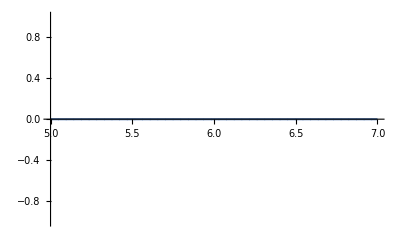

0.

```mathematica
quotientGrid = Table[{rGrid[[i]],TllTerm[2,2][rGrid[[i]]]-ℰxllPiece[2,2][rGrid[[i]]]} //. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,5,7}]
Max@Abs@Transpose[quotientGrid][[2]]
```

### T_lm-(ℰh)_lm

```mathematica
Clear[TlmTerm]
TlmTerm[l_,m_][r_] = TlmAnalyticTerm[l,m,aExp][ρOfrK[r]] +Piecewise[{{TlmAbsΔrTerm[l,m,aExp][ρOfrK[r]][[1]], r ≤ r0},{TlmAbsΔrTerm[l,m,aExp][ρOfrK[r]][[2]], r > r0}}];
```

```mathematica
Clear[xnm,xnmGrid,xnmp,xnmpGrid,xnmpp,xnmppGrid]
parameterPlotRule = {Ωφ -> Sqrt[M/r0^3], ρ0 -> -1/r0, ρmin -> -1/rmin , ρmax -> -1/rmax, rmin -> 5, rmax -> 7,r0 -> N[6,100], M -> 1};
rGrid = Table[rmin+i (rmax-rmin)/60 //. parameterPlotRule,{i,0,60}];
xnmGrid[2,2] = ParallelTable[{rGrid[[i]],xnmTermNoCoeffRule[2,2,aExp][rGrid[[i]]]} /. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnm[2,2] = Interpolation[xnmGrid[2,2]];
xnmpGrid[2,2] = ParallelTable[{rGrid[[i]],xnmTermNoCoeffRule[2,2,aExp]'[rGrid[[i]]]} /. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnmp[2,2] = Interpolation[xnmpGrid[2,2]];
xnmppGrid[2,2] = ParallelTable[{rGrid[[i]],xnmTermNoCoeffRule[2,2,aExp]''[rGrid[[i]]]} /. coeffRuleTEST  //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnmpp[2,2] = Interpolation[xnmppGrid[2,2]];
```

{0.480936,Null}

{0.391716,Null}

{0.426524,Null}

```mathematica
Clear[ℰxlmPiece]
ℰxlmPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[3]] /. hNullK[a_,b_][l_,m_] -> Function[r,xab[a,b][l,m][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
(*xab[2,2] -> xnn,*)
xab[2,3][l_,m_][r_] -> xnm[l,m][r],
xab[2,3][l_,m_]'[r_] -> xnmp[l,m][r],
xab[2,3][l_,m_]''[r_] -> xnmpp[l,m][r],
(*xab[2,4] -> xnmb,*)
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmb[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbp[l,m][r],
xab[3,4][l_,m_]''[r_] -> xmmbpp[l,m][r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

```mathematica
quotientGrid = Table[{rGrid[[i]],TlmTerm[2,2][rGrid[[i]]]-ℰxlmPiece[2,2][rGrid[[i]]]} //.{xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[2,2,aExp][ρmin],xmmbSecondIndefIntegralAnalyticTermAtρmin -> xmmbSecondIndefIntegralAnalyticTerm[2,2,aExp][ρmin],
xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[2,2,aExp][ρmin][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρmin -> xmmbSecondIndefIntegralAbsΔrTerm[2,2,aExp][ρmin][[1]]}  //. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,5,7}]
Max@Abs@Transpose[quotientGrid][[2]]
```

{0.095129,Null}

-Graphics-

0.

### T_(l m̄)-(ℰh)_(l m̄)

```mathematica
Clear[TlmbTerm]
TlmbTerm[l_,m_][r_] = TlmbAnalyticTerm[l,m,aExp][ρOfrK[r]] +Piecewise[{{TlmbAbsΔrTerm[l,m,aExp][ρOfrK[r]][[1]], r ≤ r0},{TlmbAbsΔrTerm[l,m,aExp][ρOfrK[r]][[2]], r > r0}}];
```

```mathematica
Clear[xnmb,xnmbGrid,xnmbp,xnmbpGrid,xnmbpp,xnmbppGrid]
parameterPlotRule = {Ωφ -> Sqrt[M/r0^3], ρ0 -> -1/r0, ρmin -> -1/rmin , ρmax -> -1/rmax, rmin -> 5, rmax -> 7,r0 -> N[6,100], M -> 1};
rGrid = Table[rmin+i (rmax-rmin)/60 //. parameterPlotRule,{i,0,60}];
xnmbGrid[2,2] = ParallelTable[{rGrid[[i]],xnmbTermNoCoeffRule[2,2,aExp][rGrid[[i]]]} /. coeffRuleTEST  //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnmb[2,2] = Interpolation[xnmbGrid[2,2]];
xnmbpGrid[2,2] = ParallelTable[{rGrid[[i]],xnmbTermNoCoeffRule[2,2,aExp]'[rGrid[[i]]]} /. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnmbp[2,2] = Interpolation[xnmbpGrid[2,2]];
xnmbppGrid[2,2] = ParallelTable[{rGrid[[i]],xnmbTermNoCoeffRule[2,2,aExp]''[rGrid[[i]]]} /. coeffRuleTEST  //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnmbpp[2,2] = Interpolation[xnmbppGrid[2,2]];
```

{0.479415,Null}

{0.363338,Null}

{0.370921,Null}

```mathematica
Clear[ℰxlmbPiece]
ℰxlmbPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[4]] /. hNullK[a_,b_][l_,m_] -> Function[r,xab[a,b][l,m][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
(*xab[2,2] -> xnn,*)
xab[2,3][l_,m_] -> Function[r,0],
xab[2,4][l_,m_][r_] -> xnmb[l,m][r],
xab[2,4][l_,m_]'[r_] -> xnmbp[l,m][r],
xab[2,4][l_,m_]''[r_] -> xnmbpp[l,m][r],
(*xab[2,4] -> xnmb,*)
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmb[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbp[l,m][r],
xab[3,4][l_,m_]''[r_] -> xmmbpp[l,m][r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

```mathematica
quotientGrid = Table[{rGrid[[i]],TlmbTerm[2,2][rGrid[[i]]]-ℰxlmbPiece[2,2][rGrid[[i]]]} //.{xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[2,2,aExp][ρmin],xmmbSecondIndefIntegralAnalyticTermAtρmin -> xmmbSecondIndefIntegralAnalyticTerm[2,2,aExp][ρmin],
xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[2,2,aExp][ρmin][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρmin -> xmmbSecondIndefIntegralAbsΔrTerm[2,2,aExp][ρmin][[1]]}  //. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,5,7}]
Max@Abs@Transpose[quotientGrid][[2]]
```

{0.084983,Null}

-Graphics-

0.

### T_ln-(ℰh)_ln

```mathematica
Clear[TlnTerm]
TlnTerm[l_,m_][r_] = TlnAnalyticTerm[l,m,aExp][ρOfrK[r]] +Piecewise[{{TlnAbsΔrTerm[l,m,aExp][ρOfrK[r]][[1]], r ≤ r0},{TlnAbsΔrTerm[l,m,aExp][ρOfrK[r]][[2]], r > r0}}];
```

```mathematica
Clear[xnn,xnnGrid,xnnp,xnnpGrid,xnnpp,xnnppGrid]
parameterPlotRule = {Ωφ -> Sqrt[M/r0^3], ρ0 -> -1/r0, ρmin -> -1/rmin , ρmax -> -1/rmax, rmin -> 5, rmax -> 7,r0 -> N[6,100], M -> 1};
rGrid = Table[rmin+i (rmax-rmin)/60 //. parameterPlotRule,{i,0,60}];
xnnGrid[2,2] = ParallelTable[{rGrid[[i]],xnnTermNoCoeffRule[2,2,aExp][rGrid[[i]]]} /. coeffRuleTEST  //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnn[2,2] = Interpolation[xnnGrid[2,2]];
xnnpGrid[2,2] = ParallelTable[{rGrid[[i]],xnnTermNoCoeffRule[2,2,aExp]'[rGrid[[i]]]} /. coeffRuleTEST  //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnnp[2,2] = Interpolation[xnnpGrid[2,2]];
xnnppGrid[2,2] = ParallelTable[{rGrid[[i]],xnnTermNoCoeffRule[2,2,aExp]''[rGrid[[i]]]} /. coeffRuleTEST  //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
xnnpp[2,2] = Interpolation[xnmppGrid[2,2]];
```

{2.14565,Null}

{2.73067,Null}

{4.46193,Null}

```mathematica
Clear[ℰxlnPiece]
ℰxlnPiece[l_,m_][rVal_] = ℰhPWorldtubePiece[l,m][r][[2]] /. hNullK[a_,b_][l_,m_] -> Function[r,xab[a,b][l,m][r]] /. 
{xab[1,1][l_,m_] -> Function[r,0],
xab[1,2][l_,m_] -> Function[r,0],
xab[1,3][l_,m_] -> Function[r,0],
xab[1,4][l_,m_] -> Function[r,0],
xab[2,2][l_,m_][r_] -> xnn[l,m][r],
xab[2,2][l_,m_]'[r_] -> xnnp[l,m][r],
xab[2,2][l_,m_]''[r_] -> xnnpp[l,m][r],
xab[2,3][l_,m_][r_] -> xnm[l,m][r],
xab[2,3][l_,m_]'[r_] -> xnmp[l,m][r],
xab[2,3][l_,m_]''[r_] -> xnmpp[l,m][r],
xab[2,4][l_,m_][r_] -> xnmb[l,m][r],
xab[2,4][l_,m_]'[r_] -> xnmbp[l,m][r],
xab[2,4][l_,m_]''[r_] -> xnmbpp[l,m][r],
xab[3,3][l_,m_] -> Function[r,0],
xab[3,4][l_,m_][r_] -> xmmb[l,m][r],
xab[3,4][l_,m_]'[r_] -> xmmbp[l,m][r],
xab[3,4][l_,m_]''[r_] -> xmmbpp[l,m][r],
xab[4,4][l_,m_] -> Function[r,0]} /. r -> rVal;
```

```mathematica
quotientGrid = Table[{rGrid[[i]],TlnTerm[2,2][rGrid[[i]]]-ℰxlnPiece[2,2][rGrid[[i]]]} //.{xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[2,2,aExp][ρmin],xmmbSecondIndefIntegralAnalyticTermAtρmin -> xmmbSecondIndefIntegralAnalyticTerm[2,2,aExp][ρmin],
xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[2,2,aExp][ρmin][[1]],xmmbSecondIndefIntegralAbsΔrTermAtρmin -> xmmbSecondIndefIntegralAbsΔrTerm[2,2,aExp][ρmin][[1]]}  //. coeffRuleTEST //. parameterPlotRule,{i,1,Length[rGrid]}]; // Timing
quotientInterpol = Interpolation[quotientGrid];
ReImPlot[quotientInterpol[r],{r,5,7}]
Max@Abs@Transpose[quotientGrid][[2]]
```

{0.139948,Null}

-Graphics-

0.

## Check --- Reality conditions

We should have that the 4D x_nn and x_(m m̄) are real, while by definition x_(n m̄) = (x_nm)^*.
At the level of the modes, this means for example that x_(n m̄)^lm = (-1)^(m+1)(x_nm^(l-m))^* . This formula also holds for the other tetrad components.

```mathematica
(* NOTE: MAKE SURE THAT VALUE OF M AND r0 AGREE WITH THOSE FOR WHICH THE COEFFICIENTS of the stress energy WERE COMPUTED FOR!!! *)
aExpTEST=2; myrTEST=r0+1;
Table[xmmbTermNoCoeffRule[myl,mym,aExpTEST][myrTEST] -(-1)^mym Conjugate[xmmbTermNoCoeffRule[myl,-mym,aExpTEST][myrTEST]] /. coeffRule ,{myl,2,3},{mym,0,myl}] (* Checking for Subscript[x, m m̄] *)
Table[xnmbTermNoCoeffRule[myl,mym,aExpTEST][myrTEST] -(-1)^(mym+1) Conjugate[xnmTermNoCoeffRule[myl,-mym,aExpTEST][myrTEST]] /. coeffRule,{myl,2,3},{mym,0,myl}]  (* Checking for Subscript[x, nm] *)
Table[xnnTermNoCoeffRule[myl,mym,aExpTEST][myrTEST] -(-1)^mym Conjugate[xnnTermNoCoeffRule[myl,-mym,aExpTEST][myrTEST]] /. coeffRule,{myl,2,3},{mym,0,myl}] (* Checking for Subscript[x, nn] *)
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

## Corrector Tensors

Here we sum over the individual contributions, and compute the other tetrad coefficients of the corrector tensors (which all vanish).

```mathematica
Clear[xmmbTerm,xnmTerm,xnmbTerm,xnnTerm]
Do[xmmbTerm[l_,m_,aExp][r_] = xmmbTermNoCoeffRule[l,m,aExp][r] /. coeffRule;xnmTerm[l_,m_,aExp][r_]   = xnmTermNoCoeffRule[l,m,aExp][r]   /. coeffRule;xnmbTerm[l_,m_,aExp][r_] = xnmbTermNoCoeffRule[l,m,aExp][r] /. coeffRule;xnnTerm[l_,m_,aExp][r_]   = xnnTermNoCoeffRule[l,m,aExp][r]   /. coeffRule,
{aExp,0,orderOfPuncture}]
```

```mathematica
xll[l_,m_][r_] = 0;
xln[l_,m_][r_] = 0;
xlm[l_,m_][r_] = 0;
xlmb[l_,m_][r_] = 0;
xnn[l_,m_][r_] = Sum[xnnTerm[l,m,nInd][r],{nInd,0,orderOfPuncture}];
xnm[l_,m_][r_] = Sum[xnmTerm[l,m,nInd][r],{nInd,0,orderOfPuncture}];
xnmb[l_,m_][r_] = Sum[xnmbTerm[l,m,nInd][r],{nInd,0,orderOfPuncture}];
xmm[l_,m_][r_] = 0;
xmmb[l_,m_][r_] = Sum[xmmbTerm[l,m,nInd][r],{nInd,0,orderOfPuncture}];
xmbmb[l_,m_][r_] = 0;
```

## L_Ξ g_ab

## Read Me

Old method to compute Ξ, which relied on the computation of the corrector tensors using a power-series expansion.
If you want to run Method 1 below, do the following: run first the section on corrector tensor for aExp=0, then immediately run the Method 1 section. Go back to corrector tensor section and run it again, this time with aExp=1, then run Method 1 section and so on.

For Method 2, the safest is to do the same thing as Method 1, but I think it should work if you run the corrector tensor section for all aExp you want, and then run Method 2, instead of going back and forth.

## Term-by-Term calculation Method 1

Not evaluable.

In this method, we completely redo all the integrals as we do for the corrector tensors.

## a^o

### a^0 1st term contribution

#### Distributional part

```mathematica
aCircDistrContributionAtRmaxTMP[l_,m_,aExp] = TllδpCoeff[l,m][rmax] /. TllδCoeff[l_,m_][rmax] -> TllδRmaxPiece[l,m] /. TllδpCoeff[l_,m_][rmax] -> TllδpRmaxPiece[l,m]  // Simplify;
(* Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[r2^(-2)r1^2 (TllδCoeff[l,m][rmax] DiracDelta[r1-rmax]+TllδpCoeff[l,m][rmax] DiracDelta'[r1-rmax]),{r2,rmin-ϵ,rmax+ϵ},{r1,rmin-ϵ,r2}]] /. ϵ -> 0 *)
aCircDistrContributionAtRmax[l_,m_,aExp] = (aCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(aCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule // FullSimplify[#,Assumptions->simplifyRule]&
```

𝒸1𝓂𝓂𝒷[l,m,0]+𝒸2𝓂𝓂𝒷[l,m,0]

```mathematica
aCirc1stTermContribution[aExp] = Collect[1/2 (xmmbTermNoCoeffRule[0,0,aExp][rmax] + aCircDistrContributionAtRmax[0,0,aExp]),CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
```

### a^0 2nd term contribution

#### Analytic part

```mathematica
(* xmmbFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[ρ1^(-4) TllAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,{ρ2<0}] &]; *)
aCirc2ndTermAnalyticContribution[l_,m_,aExp] =Collect[xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmax] - xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin] , CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&]
```

((ρmax-ρmin) (l ρmax ρmin+l^2 ρmax ρmin+ⅈ m (ρmax+ρmin) Ωφ) 𝒸1ℓℓ[l,m,0])/(2 ρmax^2 ρmin^2)+(√(l (1+l)) (ρmax-ρmin) 𝒸1ℓ𝓂[l,m,0])/(√2 ρmax ρmin)+(√(l (1+l)) (-ρmax+ρmin) 𝒸1ℓ𝓂𝒷[l,m,0])/(√2 ρmax ρmin)

#### |Δr| part

```mathematica
(* xmmbFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[ρ1^(-4) TllAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2, CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&]; *)
aCirc2ndTermAbsΔrContribution[l_,m_,aExp] = Collect[
xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]]-xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]]+xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmax][[2]]-xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]]
,CoeffCollectRule, Simplify];
```

#### Distributional part

```mathematica
aCirc2ndTermDistrContributionAtRminTMP[l_,m_,aExp] = rmin (rmin TllδCoeff[l,m][rmin]-2 TllδpCoeff[l,m][rmin]) /. TllδCoeff[l_,m_][rmin] -> TllδRminPiece[l,m] /. TllδpCoeff[l_,m_][rmin] -> TllδpRminPiece[l,m]  // Simplify;
aCirc2ndTermDistrContributionAtRmaxTMP[l_,m_,aExp] = rmax (rmax TllδCoeff[l,m][rmax]-2 TllδpCoeff[l,m][rmax]) /. TllδCoeff[l_,m_][rmax] -> TllδRmaxPiece[l,m] /. TllδpCoeff[l_,m_][rmax] -> TllδpRmaxPiece[l,m]  // Simplify;
aCirc2ndTermDistrContributionAtRmin[l_,m_,aExp] = (aCirc2ndTermDistrContributionAtRminTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(aCirc2ndTermDistrContributionAtRminTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[1]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
aCirc2ndTermDistrContributionAtRmax[l_,m_,aExp] = (aCirc2ndTermDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(aCirc2ndTermDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
Clear[TllDistrContributionAtRminTMP]
(* Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[r1^2 (TllδCoeff[l,m][rmin] DiracDelta[r1-rmin]+TllδpCoeff[l,m][rmin] DiracDelta'[r1-rmin]),{r1,rmin-ϵ,rmax+ϵ}]] /. ϵ -> 0
Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[r1^2 (TllδCoeff[l,m][rmax] DiracDelta[r1-rmax]+TllδpCoeff[l,m][rmax] DiracDelta'[r1-rmax]),{r1,rmin-ϵ,rmax+ϵ}]] /. ϵ -> 0 *)
```

1/(2 ρmin)(-√2 √(l (1+l)) 𝒸1ℓ𝓂[l,m,0]+√2 √(l (1+l)) 𝒸1ℓ𝓂𝒷[l,m,0]+4 𝒸1ℓ𝓃[l,m,0]+√2 √(l (1+l)) 𝒸2ℓ𝓂[l,m,0]-√2 √(l (1+l)) 𝒸2ℓ𝓂𝒷[l,m,0]-4 𝒸2ℓ𝓃[l,m,0])

-1/(2 ρmax)(-√2 √(l (1+l)) 𝒸1ℓ𝓂[l,m,0]+√2 √(l (1+l)) 𝒸1ℓ𝓂𝒷[l,m,0]+4 𝒸1ℓ𝓃[l,m,0]-√2 √(l (1+l)) 𝒸2ℓ𝓂[l,m,0]+√2 √(l (1+l)) 𝒸2ℓ𝓂𝒷[l,m,0]+4 𝒸2ℓ𝓃[l,m,0])

```mathematica
aCirc2ndTermContribution[l_,m_][aExp] = Collect[-ρmax/2 (aCirc2ndTermAnalyticContribution[l,m,aExp] +aCirc2ndTermAbsΔrContribution[l,m,aExp]+aCirc2ndTermDistrContributionAtRmin[l,m,aExp]+aCirc2ndTermDistrContributionAtRmax[l,m,aExp]),CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
```

```mathematica
aCirc00TermNoCoeffRule[aExp] = aCirc1stTermContribution[aExp]+aCirc2ndTermContribution[0,0][aExp];
```

## b^o

```mathematica
bCirc10TermNoCoeffRule[aExp] = -aCirc2ndTermContribution[1,0][aExp]/ρmax;
```

## c^o

```mathematica
cCirc1stTermContribution[aExp] = -1/3 (ρmax^2 (-r) ðCK[0,1][bCirc10TermNoCoeffRule[aExp]]); (* c^0 1st term contribution *)
```

### T_lm contribution + δ contribution

#### Analytic part

```mathematica
(*xnmFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) TlmAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&];*)cCircTlmAnalyticContribution[aExp] =Collect[xnmFirstIndefIntegralAnalyticTerm[1,0,aExp][ρmax] - xnmFirstIndefIntegralAnalyticTerm[1,0,aExp][ρmin], CoeffCollectRule, Simplify[#,Assumptions->simplifyRule]&]
```

M (ρmax^2-ρmin^2) 𝒸1ℓℓ[1,0,0]+M (ρmax^2-ρmin^2) 𝒸1ℓ𝓂[1,0,0]+(ρmax-ρmin) 𝒸1ℓ𝓂𝒷[1,0,0]+2 (ρmax-ρmin) 𝒸1ℓ𝓃[1,0,0]+2 (ρmax-ρmin) 𝒸1𝓃𝓂[1,0,0]

#### |Δr| part

```mathematica
(*xnmFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) TlmAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule,Simplify[#,Assumptions->{ρ2<0}]&];*)
cCircTlmAbsΔrContribution[aExp] = Collect[
xnmFirstIndefIntegralAbsΔrTerm[1,0,aExp][ρ0][[1]]-xnmFirstIndefIntegralAbsΔrTerm[1,0,aExp][ρmin][[1]]+xnmFirstIndefIntegralAbsΔrTerm[1,0,aExp][ρmax][[2]]-xnmFirstIndefIntegralAbsΔrTerm[1,0,aExp][ρ0][[2]] 
,CoeffCollectRule, Simplify]
```

M (-2 ρ0^2+ρmax^2+ρmin^2) 𝒸2ℓℓ[1,0,0]+M (-2 ρ0^2+ρmax^2+ρmin^2) 𝒸2ℓ𝓂[1,0,0]+(-2 ρ0+ρmax+ρmin) 𝒸2ℓ𝓂𝒷[1,0,0]+2 (-2 ρ0+ρmax+ρmin) 𝒸2ℓ𝓃[1,0,0]+2 (-2 ρ0+ρmax+ρmin) 𝒸2𝓃𝓂[1,0,0]

#### Distributional part

For c^o, there are two parts that contribute: one from T_lm as usual (δ and δ’), and one part from 𝒩x_(m m̄) (just δ). The latter part is actually only made up of the distributional content in T_ll.
Note that this contribution will vanish anyway because the l=1 m=0 piece of Tll vanishes.

```mathematica
(* THIS CALUYCLATION IS WRONG AND ANYWAY DOES NOT SEEM TO APPEAR ANYWHERE ELSE!!!!! *)
Clear[TllDistrContributionAtRmaxTMP,TllDistrContributionAtRmax]
TllDistrContributionAtRmaxTMP[l_,m_,aExp][ρ_] = 
((2 ρ-ρmin) ρmin TllδpCoeff[l,m][rmax]+(ρ-ρmin) (TllδCoeff[l,m][rmax]-TllδpCoeff[l,m]'[rmax]))/ρmin^2/. TllδCoeff[l_,m_][rmax] -> TllδRmaxPiece[l,m] /. TllδpCoeff[l_,m_] -> TllδpRmaxPiece[l,m]  // Simplify;
TllDistrContributionAtRmax[l_,m_,aExp][ρ_] = (TllDistrContributionAtRmaxTMP[l,m,aExp][ρ] /. h𝒫TaylorAnalyticRule) +
			(TllDistrContributionAtRmaxTMP[l,m,aExp][ρ] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
Clear[TllDistrContributionAtRmaxTMP]
```

1/ρmin^2((2 ρ-ρmin) ρmin {-𝒸2𝓂𝓂𝒷[l,m,0],𝒸2𝓂𝓂𝒷[l,m,0]}[-1/ρmax]+(2 ρ-ρmin) ρmin 𝒸1𝓂𝓂𝒷[l,m,0][-1/ρmax]-1/2 (ρ-ρmin) (-√2 √(l (1+l)) ρmax 𝒸2ℓ𝓂[l,m,0]+√2 √(l (1+l)) ρmax 𝒸2ℓ𝓂𝒷[l,m,0]+4 ρmax 𝒸2ℓ𝓃[l,m,0]+4 ρmax 𝒸2𝓂𝓂𝒷[l,m,0]+2 {-𝒸2𝓂𝓂𝒷[l,m,0],𝒸2𝓂𝓂𝒷[l,m,0]}'[-1/ρmax])-1/2 (ρ-ρmin) (-√2 √(l (1+l)) ρmax 𝒸1ℓ𝓂[l,m,0]+√2 √(l (1+l)) ρmax 𝒸1ℓ𝓂𝒷[l,m,0]+4 ρmax 𝒸1ℓ𝓃[l,m,0]+4 ρmax 𝒸1𝓂𝓂𝒷[l,m,0]+2 𝒸1𝓂𝓂𝒷[l,m,0]'[-1/ρmax]))

```mathematica
Clear[𝒩xmmbδCoeffRminForcCirc,𝒩xmmbδCoeffRmaxForcCirc]
𝒩xmmbδCoeffRminForcCirc[l_,m_,aExp] =Simplify[ -1/2 ðCKρ[0,l][xmmbTermNoCoeffRule[l,m,aExp][-1/ρmin]] /. ρ -> ρmin,ρmin<ρ0];
𝒩xmmbδCoeffRmaxForcCirc[l_,m_,aExp] = Simplify[ -1/2 ðCKρ[0,l][xmmbTermNoCoeffRule[l,m,aExp][-1/ρmax]] /. ρ -> ρmax,ρ0<ρmax];
```

```mathematica
cCircDistrContributionAtRminTMP[l_,m_,aExp] = 2 TlmδCoeff[l,m][rmin]/. TlmδCoeff[l_,m_][rmin] -> TlmδRminPiece[l,m]+𝒩xmmbδCoeffRminForcCirc[l,m,aExp] /. TlmδpCoeff[l_,m_][rmin] -> TlmδpRminPiece[l,m]  // Simplify;
cCircDistrContributionAtRmaxTMP[l_,m_,aExp] = 2  TlmδCoeff[l,m][rmax] /. TlmδCoeff[l_,m_][rmax] -> TlmδRmaxPiece[l,m]+𝒩xmmbδCoeffRmaxForcCirc[l,m,aExp] /. TlmδpCoeff[l_,m_][rmax] -> TlmδpRmaxPiece[l,m]  // Simplify;
cCircDistrContributionAtRmin[l_,m_,aExp] = Collect[(cCircDistrContributionAtRminTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(cCircDistrContributionAtRminTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[1]] /. rToρRule, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&]
cCircDistrContributionAtRmax[l_,m_,aExp] = Collect[(cCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(cCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&]
(* Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[2 (TlmδCoeff[l,m][rmin] DiracDelta[r1-rmin]+TlmδpCoeff[l,m][rmin] DiracDelta'[r1-rmin]),{r1,rmin-ϵ,rmax+ϵ}]] /. ϵ -> 0
Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[2(TlmδCoeff[l,m][rmax] DiracDelta[r1-rmax]+TlmδpCoeff[l,m][rmax] DiracDelta'[r1-rmax]),{r1,rmin-ϵ,rmax+ϵ}]] /. ϵ -> 0 *)
```

(√(l (1+l)) ρmin (1+2 M ρmin) 𝒸1ℓℓ[l,m,0])/(2 √2)+(ρmin+M ρmin^2-ⅈ m Ωφ) 𝒸1ℓ𝓂[l,m,0]+(√(l (1+l)) ρmin 𝒸1ℓ𝓃[l,m,0])/(√2)-(√(-2+l+l^2) ρmin 𝒸1𝓂𝓂[l,m,0])/(√2)+(√(l (1+l)) ρmin 𝒸1𝓂𝓂𝒷[l,m,0])/(√2)+2 ρmin 𝒸1𝓃𝓂[l,m,0]-(√(l (1+l)) ρmin (1+2 M ρmin) 𝒸2ℓℓ[l,m,0])/(2 √2)+(-ρmin-M ρmin^2+ⅈ m Ωφ) 𝒸2ℓ𝓂[l,m,0]-(√(l (1+l)) ρmin 𝒸2ℓ𝓃[l,m,0])/(√2)+(√(-2+l+l^2) ρmin 𝒸2𝓂𝓂[l,m,0])/(√2)-(√(l (1+l)) ρmin 𝒸2𝓂𝓂𝒷[l,m,0])/(√2)-2 ρmin 𝒸2𝓃𝓂[l,m,0]

-1/(2 √2 ρmin^2)√(l (1+l)) (2 l ρmax^2 ρmin+2 l^2 ρmax^2 ρmin+ρmax ρmin^2-2 l ρmax ρmin^2-2 l^2 ρmax ρmin^2+2 M ρmax^2 ρmin^2+2 ⅈ m ρmax^2 Ωφ-4 ⅈ m ρmax ρmin Ωφ+2 ⅈ m ρmin^2 Ωφ-2 l (1+l) ρmax ρmin^2 Log[ρmax]+2 l (1+l) ρmax ρmin^2 Log[ρmin]) 𝒸1ℓℓ[l,m,0]+(-ρmax-M ρmax^2+ⅈ m Ωφ+l (1+l) ρmax Log[ρmax]-l (1+l) ρmax Log[ρmin]) 𝒸1ℓ𝓂[l,m,0]+l (1+l) ρmax (-Log[ρmax]+Log[ρmin]) 𝒸1ℓ𝓂𝒷[l,m,0]+(√(l (1+l)) ρmax (-4 ρmax+3 ρmin) 𝒸1ℓ𝓃[l,m,0])/(√2 ρmin)+(√(-2+l+l^2) ρmax 𝒸1𝓂𝓂[l,m,0])/(√2)+(3 √(l (1+l)) ρmax 𝒸1𝓂𝓂𝒷[l,m,0])/(√2)-2 ρmax 𝒸1𝓃𝓂[l,m,0]+1/(2 √2 ρ0^2 ρmin^2)√(l (1+l)) (2 l ρ0^2 ρmax^2 ρmin+2 l^2 ρ0^2 ρmax^2 ρmin-ρ0^2 ρmax ρmin^2+2 l ρ0^2 ρmax ρmin^2+2 l^2 ρ0^2 ρmax ρmin^2-4 l ρ0 ρmax^2 ρmin^2-4 l^2 ρ0 ρmax^2 ρmin^2-2 M ρ0^2 ρmax^2 ρmin^2+2 ⅈ m ρ0^2 ρmax^2 Ωφ-4 ⅈ m ρ0^2 ρmax ρmin Ωφ-2 ⅈ m ρ0^2 ρmin^2 Ωφ+8 ⅈ m ρ0 ρmax ρmin^2 Ωφ-4 ⅈ m ρmax^2 ρmin^2 Ωφ-4 l (1+l) ρ0^2 ρmax ρmin^2 Log[ρ0]+2 l (1+l) ρ0^2 ρmax ρmin^2 Log[ρmax]+2 l ρ0^2 ρmax ρmin^2 Log[ρmin]+2 l^2 ρ0^2 ρmax ρmin^2 Log[ρmin]) 𝒸2ℓℓ[l,m,0]+(-ρmax+2 l ρmax+2 l^2 ρmax-M ρmax^2-(2 l ρmax^2)/ρ0-(2 l^2 ρmax^2)/ρ0+ⅈ m Ωφ-2 l (1+l) ρmax Log[ρ0]+l (1+l) ρmax Log[ρmax]+l ρmax Log[ρmin]+l^2 ρmax Log[ρmin]) 𝒸2ℓ𝓂[l,m,0]+(l (1+l) ρmax (-2 ρ0+2 ρmax+2 ρ0 Log[ρ0]-ρ0 Log[ρmax]-ρ0 Log[ρmin]) 𝒸2ℓ𝓂𝒷[l,m,0])/ρ0+(√(l (1+l)) ρmax (4 ρmax-5 ρmin) 𝒸2ℓ𝓃[l,m,0])/(√2 ρmin)+(√(-2+l+l^2) ρmax 𝒸2𝓂𝓂[l,m,0])/(√2)-(√(l (1+l)) ρmax 𝒸2𝓂𝓂𝒷[l,m,0])/(√2)-2 ρmax 𝒸2𝓃𝓂[l,m,0]

### 𝒩x_(m m̄) contribution

#### Smooth piece

```mathematica
(*aCirc𝒩xmmbFirstIndefIntegralAnalyticTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) 𝒩xmmbAnalyticTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2,CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];*)
cCirc𝒩xmmbAnalyticContribution[l_,m_,aExp] = Collect[𝒩xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmax]-𝒩xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin] //.

{xmmbFirstIndefIntegralAnalyticTermAtρmin -> xmmbFirstIndefIntegralAnalyticTerm[l,m,aExp][ρmin]}

, CoeffCollectRule , Simplify[#,Assumptions->simplifyRule] &]
Clear[𝒩xmmbAnalyticTerm]
```

-1/(4 √2 ρmin^2)√(l (1+l)) ((ρmax-ρmin) (l (ρmax-ρmin) ρmin+l^2 (ρmax-ρmin) ρmin+ⅈ m (ρmax+ρmin) Ωφ)-2 ⅈ m ρmin^2 Ωφ Log[ρmax]+2 ⅈ m ρmin^2 Ωφ Log[ρmin]) 𝒸1ℓℓ[l,m,0]+1/2 l (1+l) (ρmax-ρmin) 𝒸1ℓ𝓂[l,m,0]-1/2 l (1+l) (ρmax-ρmin) 𝒸1ℓ𝓂𝒷[l,m,0]+(√(l (1+l)) (-ρmax^2+ρmin^2) 𝒸1ℓ𝓃[l,m,0])/(√2 ρmin)+(l (1+l) (-ρmax^2+ρmin^2) 𝒸2ℓ𝓂[l,m,0])/(4 ρmin)+(l (1+l) (ρmax^2-ρmin^2) 𝒸2ℓ𝓂𝒷[l,m,0])/(4 ρmin)+(√(l (1+l)) (ρmax^2-ρmin^2) 𝒸2ℓ𝓃[l,m,0])/(√2 ρmin)

#### |Δr| piece

```mathematica
(*𝒩xmmbFirstIndefIntegralAbsΔrTerm[l_,m_,aExp][ρ2_] = Collect[Integrate[2 ρ1^(-2) 𝒩xmmbAbsΔrTerm[l,m,aExp][ρ1], ρ1] /. ρ1 -> ρ2, CoeffCollectRule, Simplify[#,Assumptions->{ρ2<0}]&];*)
cCirc𝒩xmmbAbsΔrContribution[l_,m_,aExp] = Collect[
𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[1]]-𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]]+𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmax][[2]]-𝒩xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρ0][[2]]  //.

{xmmbFirstIndefIntegralAbsΔrTermAtρmin -> xmmbFirstIndefIntegralAbsΔrTerm[l,m,aExp][ρmin][[1]]}

,CoeffCollectRule, Simplify]
```

1/(4 √2 ρ0^2 ρmin^2)√(l (1+l)) (l ρ0^2 ρmax^2 ρmin+l^2 ρ0^2 ρmax^2 ρmin-2 l ρ0^3 ρmin^2-2 l^2 ρ0^3 ρmin^2+2 l ρ0^2 ρmax ρmin^2+2 l^2 ρ0^2 ρmax ρmin^2-2 l ρ0 ρmax^2 ρmin^2-2 l^2 ρ0 ρmax^2 ρmin^2+l ρ0^2 ρmin^3+l^2 ρ0^2 ρmin^3+ⅈ m ρ0^2 ρmax^2 Ωφ+ⅈ m ρ0^2 ρmin^2 Ωφ-2 ⅈ m ρmax^2 ρmin^2 Ωφ-4 ⅈ m ρ0^2 ρmin^2 Ωφ Log[ρ0]+2 ⅈ m ρ0^2 ρmin^2 Ωφ Log[ρmax]+2 ⅈ m ρ0^2 ρmin^2 Ωφ Log[ρmin]) 𝒸2ℓℓ[l,m,0]-(l (1+l) (2 ρ0^2 ρmin+2 ρmax^2 ρmin-ρ0 (ρmax+ρmin)^2) 𝒸2ℓ𝓂[l,m,0])/(4 ρ0 ρmin)+(l (1+l) (2 ρ0^2 ρmin+2 ρmax^2 ρmin-ρ0 (ρmax+ρmin)^2) 𝒸2ℓ𝓂𝒷[l,m,0])/(4 ρ0 ρmin)

```mathematica
cCirc10TermNoCoeffRule[aExp] = Collect[cCirc1stTermContribution[aExp]-1/3 (cCircTlmAnalyticContribution[aExp]+cCircTlmAbsΔrContribution[aExp]+cCircDistrContributionAtRmin[1,0,aExp]+cCircDistrContributionAtRmax[1,0,aExp]+cCirc𝒩xmmbAnalyticContribution[1,0,aExp]+cCirc𝒩xmmbAbsΔrContribution[1,0,aExp]) ,CoeffCollectRule,Simplify[#,Assumptions->simplifyRule] &];
```

```mathematica
(*DumpSave[FileNameJoin[{NotebookDirectory[],"abc_constants_up_to_n4.mx"}],{aCirc00TermNoCoeffRule,bCirc10TermNoCoeffRule,cCirc10TermNoCoeffRule}]*)
```

{aCirc00TermNoCoeffRule,bCirc10TermNoCoeffRule,cCirc10TermNoCoeffRule}

## Term-by-Term calculation Method 2

Not evaluable.

Here, we instead use the fact that these integrals can be written in terms of the corrector tensors (and first derivatives). So, only needed to compute the distributional contribution at r_max.

## a^o

### a^0 1st term contribution

#### Distributional part

```mathematica
aCircDistrContributionAtRmaxTMP[l_,m_,aExp] = TllδpCoeff[l,m][rmax] /. TllδCoeff[l_,m_][rmax] -> TllδRmaxPiece[l,m] /. TllδpCoeff[l_,m_][rmax] -> TllδpRmaxPiece[l,m]  // Simplify;
(* Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[r2^(-2)r1^2 (TllδCoeff[l,m][rmax] DiracDelta[r1-rmax]+TllδpCoeff[l,m][rmax] DiracDelta'[r1-rmax]),{r2,rmin-ϵ,rmax+ϵ},{r1,rmin-ϵ,r2}]] /. ϵ -> 0 *)
aCircDistrContributionAtRmax[l_,m_,aExp] = (aCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(aCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule // FullSimplify[#,Assumptions->simplifyRule]&
```

((ρ0-ρmax)^4 (𝒸1𝓂𝓂𝒷[l,m,4]+𝒸2𝓂𝓂𝒷[l,m,4]))/(ρ0^4 ρmax^4)

```mathematica
aCirc1stTermContribution[aExp] = Collect[1/2 (xmmbTermNoCoeffRule[0,0,aExp][rmax] + aCircDistrContributionAtRmax[0,0,aExp]),CoeffCollectRule];
```

### a^0 2nd term contribution

#### Distributional part

```mathematica
aCirc2ndTermDistrContributionAtRmaxTMP[l_,m_,aExp] = rmax (rmax TllδCoeff[l,m][rmax]-2 TllδpCoeff[l,m][rmax]) /. TllδCoeff[l_,m_][rmax] -> TllδRmaxPiece[l,m] /. TllδpCoeff[l_,m_][rmax] -> TllδpRmaxPiece[l,m]  // Simplify;
aCirc2ndTermDistrContributionAtRmax[l_,m_,aExp] = (aCirc2ndTermDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(aCirc2ndTermDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
(* Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[r1^2 (TllδCoeff[l,m][rmax] DiracDelta[r1-rmax]+TllδpCoeff[l,m][rmax] DiracDelta'[r1-rmax]),{r1,rmin-ϵ,rmax+ϵ}]] /. ϵ -> 0 *)
```

1/(2 ρ0^4 ρmax^5)(ρ0-ρmax)^3 (√2 √(l (1+l)) (ρ0-ρmax) 𝒸1ℓ𝓂[l,m,4]+√2 √(l (1+l)) (-ρ0+ρmax) 𝒸1ℓ𝓂𝒷[l,m,4]-4 ρ0 𝒸1ℓ𝓃[l,m,4]+4 ρmax 𝒸1ℓ𝓃[l,m,4]-8 ρ0 𝒸1𝓂𝓂𝒷[l,m,4]+√2 √(l (1+l)) ρ0 𝒸2ℓ𝓂[l,m,4]-√2 √(l (1+l)) ρmax 𝒸2ℓ𝓂[l,m,4]-√2 √(l (1+l)) ρ0 𝒸2ℓ𝓂𝒷[l,m,4]+√2 √(l (1+l)) ρmax 𝒸2ℓ𝓂𝒷[l,m,4]-4 ρ0 𝒸2ℓ𝓃[l,m,4]+4 ρmax 𝒸2ℓ𝓃[l,m,4]-8 ρ0 𝒸2𝓂𝓂𝒷[l,m,4])

```mathematica
aCirc2ndTermContribution[l_,m_][aExp] = Collect[-ρmax/2(rmax^2 xmmbTermNoCoeffRule[l,m,aExp]'[rmax] +aCirc2ndTermDistrContributionAtRmax[l,m,aExp]) /. coeffRule,CoeffCollectRule];
```

```mathematica
aCirc00TermNoCoeffRule[aExp] = aCirc1stTermContribution[aExp]+aCirc2ndTermContribution[0,0][aExp];
```

## b^o

```mathematica
bCirc10TermNoCoeffRule[aExp] = -aCirc2ndTermContribution[1,0][aExp]/ρmax;
```

## c^o

```mathematica
cCirc1stTermContribution[aExp] = -1/3 (ρmax^2 (-r) ðCK[0,1][bCirc10TermNoCoeffRule[aExp]]); (* c^0 1st term contribution *)
```

### Distributional part

For c^o, there are two parts that contribute: one from T_lm as usual (δ and δ’), and one part from 𝒩x_(m m̄) (just δ). The latter part is actually only made up of the distributional content in T_ll.
Note that this contribution will vanish anyway because the l=1 m=0 piece of Tll vanishes.

```mathematica
(* THIS CALUYCLATION IS WRONG AND ANYWAY DOES NOT SEEM TO APPEAR ANYWHERE ELSE!!!!! *)
Clear[TllDistrContributionAtRmaxTMP,TllDistrContributionAtRmax]
TllDistrContributionAtRmaxTMP[l_,m_,aExp][ρ_] = 
((2 ρ-ρmin) ρmin TllδpCoeff[l,m][rmax]+(ρ-ρmin) (TllδCoeff[l,m][rmax]-TllδpCoeff[l,m]'[rmax]))/ρmin^2/. TllδCoeff[l_,m_][rmax] -> TllδRmaxPiece[l,m] /. TllδpCoeff[l_,m_] -> TllδpRmaxPiece[l,m]  // Simplify;
TllDistrContributionAtRmax[l_,m_,aExp][ρ_] = (TllDistrContributionAtRmaxTMP[l,m,aExp][ρ] /. h𝒫TaylorAnalyticRule) +
			(TllDistrContributionAtRmaxTMP[l,m,aExp][ρ] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule // Simplify[#,Assumptions->simplifyRule]&
Clear[TllDistrContributionAtRmaxTMP]
```

1/ρmin^2((2 ρ-ρmin) ρmin {-(1/ρ0-1/ρmax)^4 𝒸2𝓂𝓂𝒷[l,m,4],(1/ρ0-1/ρmax)^4 𝒸2𝓂𝓂𝒷[l,m,4]}[-1/ρmax]+(2 ρ-ρmin) ρmin ((1/ρ0-1/ρmax)^4 𝒸1𝓂𝓂𝒷[l,m,4])[-1/ρmax]+1/(2 ρ0^4 ρmax^3)(ρ-ρmin) (√2 √(l (1+l)) (ρ0-ρmax)^4 𝒸2ℓ𝓂[l,m,4]-√2 √(l (1+l)) (ρ0-ρmax)^4 𝒸2ℓ𝓂𝒷[l,m,4]-4 (ρ0-ρmax)^4 𝒸2ℓ𝓃[l,m,4]-8 ρ0 (ρ0-ρmax)^3 𝒸2𝓂𝓂𝒷[l,m,4]-4 (ρ0-ρmax)^4 𝒸2𝓂𝓂𝒷[l,m,4]-2 ρ0^4 ρmax^3 {-(1/ρ0-1/ρmax)^4 𝒸2𝓂𝓂𝒷[l,m,4],(1/ρ0-1/ρmax)^4 𝒸2𝓂𝓂𝒷[l,m,4]}'[-1/ρmax])+1/(2 ρ0^4 ρmax^3)(ρ-ρmin) (√2 √(l (1+l)) (ρ0-ρmax)^4 𝒸1ℓ𝓂[l,m,4]-√2 √(l (1+l)) (ρ0-ρmax)^4 𝒸1ℓ𝓂𝒷[l,m,4]-4 (ρ0-ρmax)^4 𝒸1ℓ𝓃[l,m,4]-8 ρ0 (ρ0-ρmax)^3 𝒸1𝓂𝓂𝒷[l,m,4]-4 (ρ0-ρmax)^4 𝒸1𝓂𝓂𝒷[l,m,4]-2 ρ0^4 ρmax^3 ((1/ρ0-1/ρmax)^4 𝒸1𝓂𝓂𝒷[l,m,4])'[-1/ρmax]))

```mathematica
Clear[𝒩xmmbδCoeffRminForcCirc,𝒩xmmbδCoeffRmaxForcCirc]
𝒩xmmbδCoeffRminForcCirc[l_,m_,aExp] =Simplify[ -1/2 ðCKρ[0,l][xmmbTermNoCoeffRule[l,m,aExp][-1/ρmin]] /. ρ -> ρmin,ρmin<ρ0];
𝒩xmmbδCoeffRmaxForcCirc[l_,m_,aExp] = Simplify[ -1/2 ðCKρ[0,l][xmmbTermNoCoeffRule[l,m,aExp][-1/ρmax]] /. ρ -> ρmax,ρ0<ρmax];
```

```mathematica
cCircDistrContributionAtRminTMP[l_,m_,aExp] = 2 TlmδCoeff[l,m][rmin]/. TlmδCoeff[l_,m_][rmin] -> TlmδRminPiece[l,m]+𝒩xmmbδCoeffRminForcCirc[l,m,aExp] /. TlmδpCoeff[l_,m_][rmin] -> TlmδpRminPiece[l,m]  // Simplify;
cCircDistrContributionAtRmaxTMP[l_,m_,aExp] = 2  TlmδCoeff[l,m][rmax] /. TlmδCoeff[l_,m_][rmax] -> TlmδRmaxPiece[l,m]+𝒩xmmbδCoeffRmaxForcCirc[l,m,aExp] /. TlmδpCoeff[l_,m_][rmax] -> TlmδpRmaxPiece[l,m]  // Simplify;
cCircDistrContributionAtRmin[l_,m_,aExp] = Collect[(cCircDistrContributionAtRminTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(cCircDistrContributionAtRminTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[1]] /. rToρRule, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&]
cCircDistrContributionAtRmax[l_,m_,aExp] = Collect[(cCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAnalyticRule) +
			(cCircDistrContributionAtRmaxTMP[l,m,aExp] /. h𝒫TaylorAbsΔrRule)[[2]] /. rToρRule, CoeffCollectRule,Simplify[#,Assumptions->simplifyRule]&]
(* Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[2 (TlmδCoeff[l,m][rmin] DiracDelta[r1-rmin]+TlmδpCoeff[l,m][rmin] DiracDelta'[r1-rmin]),{r1,rmin-ϵ,rmax+ϵ}]] /. ϵ -> 0
Assuming[{ϵ>0,rmax>rmin>0},Simplify@Integrate[2(TlmδCoeff[l,m][rmax] DiracDelta[r1-rmax]+TlmδpCoeff[l,m][rmax] DiracDelta'[r1-rmax]),{r1,rmin-ϵ,rmax+ϵ}]] /. ϵ -> 0 *)
```

(√(l (1+l)) (ρ0-ρmin)^4 (1+2 M ρmin) 𝒸1ℓℓ[l,m,4])/(2 √2 ρ0^4 ρmin^3)+((ρ0-ρmin)^3 (-ρmin (ρmin+M ρmin^2-ⅈ m Ωφ)+ρ0 (3 ρmin+5 M ρmin^2-ⅈ m Ωφ)) 𝒸1ℓ𝓂[l,m,4])/(ρ0^4 ρmin^4)+(√(l (1+l)) (1/ρ0-1/ρmin)^4 ρmin 𝒸1ℓ𝓃[l,m,4])/(√2)-(√(-2+l+l^2) (1/ρ0-1/ρmin)^4 ρmin 𝒸1𝓂𝓂[l,m,4])/(√2)+(√(l (1+l)) (ρ0-ρmin)^4 𝒸1𝓂𝓂𝒷[l,m,4])/(√2 ρ0^4 ρmin^3)+(2 (ρ0-ρmin)^3 (3 ρ0-ρmin) 𝒸1𝓃𝓂[l,m,4])/(ρ0^4 ρmin^3)-(√(l (1+l)) (ρ0-ρmin)^4 (1+2 M ρmin) 𝒸2ℓℓ[l,m,4])/(2 √2 ρ0^4 ρmin^3)-((ρ0-ρmin)^3 (-ρmin (ρmin+M ρmin^2-ⅈ m Ωφ)+ρ0 (3 ρmin+5 M ρmin^2-ⅈ m Ωφ)) 𝒸2ℓ𝓂[l,m,4])/(ρ0^4 ρmin^4)-(√(l (1+l)) (1/ρ0-1/ρmin)^4 ρmin 𝒸2ℓ𝓃[l,m,4])/(√2)+(√(-2+l+l^2) (1/ρ0-1/ρmin)^4 ρmin 𝒸2𝓂𝓂[l,m,4])/(√2)-(√(l (1+l)) (ρ0-ρmin)^4 𝒸2𝓂𝓂𝒷[l,m,4])/(√2 ρ0^4 ρmin^3)-(2 (ρ0-ρmin)^3 (3 ρ0-ρmin) 𝒸2𝓃𝓂[l,m,4])/(ρ0^4 ρmin^3)

1/(60 √2 ρ0^4 ρmax^4 ρmin^6)√(l (1+l)) (-12 l ρ0^4 ρmax^6 ρmin-12 l^2 ρ0^4 ρmax^6 ρmin+15 l ρ0^4 ρmax^5 ρmin^2+15 l^2 ρ0^4 ρmax^5 ρmin^2+60 l ρ0^3 ρmax^6 ρmin^2+60 l^2 ρ0^3 ρmax^6 ρmin^2-80 l ρ0^3 ρmax^5 ρmin^3-80 l^2 ρ0^3 ρmax^5 ρmin^3-120 l ρ0^2 ρmax^6 ρmin^3-120 l^2 ρ0^2 ρmax^6 ρmin^3+180 l ρ0^2 ρmax^5 ρmin^4+180 l^2 ρ0^2 ρmax^5 ρmin^4+120 l ρ0 ρmax^6 ρmin^4+120 l^2 ρ0 ρmax^6 ρmin^4-240 l ρ0 ρmax^5 ρmin^5-240 l^2 ρ0 ρmax^5 ρmin^5-60 l ρmax^6 ρmin^5-60 l^2 ρmax^6 ρmin^5-3 l ρ0^4 ρmax ρmin^6-3 l^2 ρ0^4 ρmax ρmin^6+20 l ρ0^3 ρmax^2 ρmin^6+20 l^2 ρ0^3 ρmax^2 ρmin^6-60 l ρ0^2 ρmax^3 ρmin^6-60 l^2 ρ0^2 ρmax^3 ρmin^6+120 l ρ0 ρmax^4 ρmin^6+120 l^2 ρ0 ρmax^4 ρmin^6+60 l ρmax^5 ρmin^6+60 l^2 ρmax^5 ρmin^6-30 (ρ0-ρmax)^4 ρmax (1+2 M ρmax) ρmin^6-20 ⅈ m ρ0^4 ρmax^6 Ωφ+24 ⅈ m ρ0^4 ρmax^5 ρmin Ωφ+96 ⅈ m ρ0^3 ρmax^6 ρmin Ωφ-120 ⅈ m ρ0^3 ρmax^5 ρmin^2 Ωφ-180 ⅈ m ρ0^2 ρmax^6 ρmin^2 Ωφ+240 ⅈ m ρ0^2 ρmax^5 ρmin^3 Ωφ+160 ⅈ m ρ0 ρmax^6 ρmin^3 Ωφ-240 ⅈ m ρ0 ρmax^5 ρmin^4 Ωφ-60 ⅈ m ρmax^6 ρmin^4 Ωφ+120 ⅈ m ρmax^5 ρmin^5 Ωφ-4 ⅈ m ρ0^4 ρmin^6 Ωφ+24 ⅈ m ρ0^3 ρmax ρmin^6 Ωφ-60 ⅈ m ρ0^2 ρmax^2 ρmin^6 Ωφ+80 ⅈ m ρ0 ρmax^3 ρmin^6 Ωφ-60 ⅈ m ρmax^4 ρmin^6 Ωφ+60 l (1+l) ρmax^5 ρmin^6 Log[ρmax]-60 l (1+l) ρmax^5 ρmin^6 Log[ρmin]) 𝒸1ℓℓ[l,m,4]+1/(12 ρ0^4 ρmax^4 ρmin^4)(-24 ρ0 (ρ0-ρmax)^3 ρmax ρmin^4-48 M ρ0 (ρ0-ρmax)^3 ρmax^2 ρmin^4-12 (ρ0-ρmax)^4 ρmin^4 (ρmax+M ρmax^2-ⅈ m Ωφ)+l (1+l) ρmax (ρ0 (48 ρmax^3 ρmin^3 (-ρmax+ρmin)+36 ρ0 ρmax^2 ρmin^2 (ρmax^2-ρmin^2)-16 ρ0^2 ρmax ρmin (ρmax^3-ρmin^3)+3 ρ0^3 (ρmax^4-ρmin^4))+12 ρmax^4 ρmin^4 Log[ρmax]-12 ρmax^4 ρmin^4 Log[ρmin])) 𝒸1ℓ𝓂[l,m,4]-1/(12 ρ0^4 ρmax^3 ρmin^4)l (1+l) (ρ0 (48 ρmax^3 ρmin^3 (-ρmax+ρmin)+36 ρ0 ρmax^2 ρmin^2 (ρmax^2-ρmin^2)-16 ρ0^2 ρmax ρmin (ρmax^3-ρmin^3)+3 ρ0^3 (ρmax^4-ρmin^4))+12 ρmax^4 ρmin^4 Log[ρmax]-12 ρmax^4 ρmin^4 Log[ρmin]) 𝒸1ℓ𝓂𝒷[l,m,4]-1/(5 √2 ρ0^4 ρmax^3 ρmin^5)√(l (1+l)) (-20 ρ0^3 ρmax^5 ρmin+5 ρmax^4 (4 ρmax-3 ρmin) ρmin^4+20 ρ0 ρmax^3 ρmin^3 (-2 ρmax^2+ρmin^2)+ρ0^4 (4 ρmax^5+ρmin^5)+10 ρ0^2 (4 ρmax^5 ρmin^2-ρmax^2 ρmin^5)) 𝒸1ℓ𝓃[l,m,4]+(√(-2+l+l^2) (1/ρ0-1/ρmax)^4 ρmax 𝒸1𝓂𝓂[l,m,4])/(√2)+(3 √(l (1+l)) (ρ0-ρmax)^4 𝒸1𝓂𝓂𝒷[l,m,4])/(√2 ρ0^4 ρmax^3)-(2 (ρ0-ρmax)^3 (3 ρ0-ρmax) 𝒸1𝓃𝓂[l,m,4])/(ρ0^4 ρmax^3)+1/(60 √2 ρ0^6 ρmax^4 ρmin^6)√(l (1+l)) (12 l ρ0^6 ρmax^6 ρmin+12 l^2 ρ0^6 ρmax^6 ρmin-15 l ρ0^6 ρmax^5 ρmin^2-15 l^2 ρ0^6 ρmax^5 ρmin^2-60 l ρ0^5 ρmax^6 ρmin^2-60 l^2 ρ0^5 ρmax^6 ρmin^2+80 l ρ0^5 ρmax^5 ρmin^3+80 l^2 ρ0^5 ρmax^5 ρmin^3+120 l ρ0^4 ρmax^6 ρmin^3+120 l^2 ρ0^4 ρmax^6 ρmin^3-180 l ρ0^4 ρmax^5 ρmin^4-180 l^2 ρ0^4 ρmax^5 ρmin^4-120 l ρ0^3 ρmax^6 ρmin^4-120 l^2 ρ0^3 ρmax^6 ρmin^4+240 l ρ0^3 ρmax^5 ρmin^5+240 l^2 ρ0^3 ρmax^5 ρmin^5+60 l ρ0^2 ρmax^6 ρmin^5+60 l^2 ρ0^2 ρmax^6 ρmin^5-30 ρ0^6 ρmax ρmin^6-3 l ρ0^6 ρmax ρmin^6-3 l^2 ρ0^6 ρmax ρmin^6+120 ρ0^5 ρmax^2 ρmin^6+20 l ρ0^5 ρmax^2 ρmin^6+20 l^2 ρ0^5 ρmax^2 ρmin^6-60 M ρ0^6 ρmax^2 ρmin^6-180 ρ0^4 ρmax^3 ρmin^6-60 l ρ0^4 ρmax^3 ρmin^6-60 l^2 ρ0^4 ρmax^3 ρmin^6+240 M ρ0^5 ρmax^3 ρmin^6+120 ρ0^3 ρmax^4 ρmin^6+120 l ρ0^3 ρmax^4 ρmin^6+120 l^2 ρ0^3 ρmax^4 ρmin^6-360 M ρ0^4 ρmax^4 ρmin^6-30 ρ0^2 ρmax^5 ρmin^6-190 l ρ0^2 ρmax^5 ρmin^6-190 l^2 ρ0^2 ρmax^5 ρmin^6+240 M ρ0^3 ρmax^5 ρmin^6-24 l ρ0 ρmax^6 ρmin^6-24 l^2 ρ0 ρmax^6 ρmin^6-60 M ρ0^2 ρmax^6 ρmin^6+20 ⅈ m ρ0^6 ρmax^6 Ωφ-24 ⅈ m ρ0^6 ρmax^5 ρmin Ωφ-96 ⅈ m ρ0^5 ρmax^6 ρmin Ωφ+120 ⅈ m ρ0^5 ρmax^5 ρmin^2 Ωφ+180 ⅈ m ρ0^4 ρmax^6 ρmin^2 Ωφ-240 ⅈ m ρ0^4 ρmax^5 ρmin^3 Ωφ-160 ⅈ m ρ0^3 ρmax^6 ρmin^3 Ωφ+240 ⅈ m ρ0^3 ρmax^5 ρmin^4 Ωφ+60 ⅈ m ρ0^2 ρmax^6 ρmin^4 Ωφ-120 ⅈ m ρ0^2 ρmax^5 ρmin^5 Ωφ-4 ⅈ m ρ0^6 ρmin^6 Ωφ+24 ⅈ m ρ0^5 ρmax ρmin^6 Ωφ-60 ⅈ m ρ0^4 ρmax^2 ρmin^6 Ωφ+80 ⅈ m ρ0^3 ρmax^3 ρmin^6 Ωφ-60 ⅈ m ρ0^2 ρmax^4 ρmin^6 Ωφ+48 ⅈ m ρ0 ρmax^5 ρmin^6 Ωφ-8 ⅈ m ρmax^6 ρmin^6 Ωφ-120 l (1+l) ρ0^2 ρmax^5 ρmin^6 Log[ρ0]+60 l (1+l) ρ0^2 ρmax^5 ρmin^6 Log[ρmax]+60 l ρ0^2 ρmax^5 ρmin^6 Log[ρmin]+60 l^2 ρ0^2 ρmax^5 ρmin^6 Log[ρmin]) 𝒸2ℓℓ[l,m,4]+((4 l (1+l))/ρ0^3+2 (1/ρ0-1/ρmax)^3-(l (1+l))/(4 ρmax^3)+(4 l (1+l))/(3 ρ0 ρmax^2)-(3 l (1+l))/(ρ0^2 ρmax)-(25 l (1+l) ρmax)/(6 ρ0^4)+4 M (1/ρ0-1/ρmax)^3 ρmax-(l (1+l) ρmax)/(4 ρmin^4)+(4 l (1+l) ρmax)/(3 ρ0 ρmin^3)-(3 l (1+l) ρmax)/(ρ0^2 ρmin^2)+(4 l (1+l) ρmax)/(ρ0^3 ρmin)-((ρ0-ρmax)^4 (ρmax+M ρmax^2-ⅈ m Ωφ))/(ρ0^4 ρmax^4)-(2 l (1+l) ρmax Log[ρ0])/ρ0^4+(l (1+l) ρmax Log[ρmax])/ρ0^4+(l (1+l) ρmax Log[ρmin])/ρ0^4) 𝒸2ℓ𝓂[l,m,4]+1/(12 ρ0^4 ρmax^3 ρmin^4)l (1+l) (3 ρ0^4 ρmax^4-16 ρ0^3 ρmax^4 ρmin+36 ρ0^2 ρmax^4 ρmin^2-48 ρ0 ρmax^4 ρmin^3+3 ρ0^4 ρmin^4-16 ρ0^3 ρmax ρmin^4+36 ρ0^2 ρmax^2 ρmin^4-48 ρ0 ρmax^3 ρmin^4+50 ρmax^4 ρmin^4+24 ρmax^4 ρmin^4 Log[ρ0]-12 ρmax^4 ρmin^4 Log[ρmax]-12 ρmax^4 ρmin^4 Log[ρmin]) 𝒸2ℓ𝓂𝒷[l,m,4]+1/(5 √2 ρ0^5 ρmax^3 ρmin^5)√(l (1+l)) (-20 ρ0^4 ρmax^5 ρmin-8 ρmax^5 ρmin^5+5 ρ0 ρmax^4 ρmin^4 (4 ρmax+3 ρmin)-20 ρ0^2 ρmax^3 ρmin^3 (2 ρmax^2+ρmin^2)+10 ρ0^3 ρmax^2 ρmin^2 (4 ρmax^3+ρmin^3)+ρ0^5 (4 ρmax^5-ρmin^5)) 𝒸2ℓ𝓃[l,m,4]+(√(-2+l+l^2) (1/ρ0-1/ρmax)^4 ρmax 𝒸2𝓂𝓂[l,m,4])/(√2)+(3 √(l (1+l)) (ρ0-ρmax)^4 𝒸2𝓂𝓂𝒷[l,m,4])/(√2 ρ0^4 ρmax^3)-(2 (ρ0-ρmax)^3 (3 ρ0-ρmax) 𝒸2𝓃𝓂[l,m,4])/(ρ0^4 ρmax^3)

```mathematica
cCirc10TermNoCoeffRule[aExp] = Collect[cCirc1stTermContribution[aExp]-1/3 (xnmTermNoCoeffRule[1,0,aExp]'[rmax]-2 ρmax xnmTermNoCoeffRule[1,0,aExp][rmax]+cCircDistrContributionAtRmax[1,0,aExp]),CoeffCollectRule];
```

```mathematica
(*DumpSave[FileNameJoin[{NotebookDirectory[],"abc_constants_up_to_n4.mx"}],{aCirc00TermNoCoeffRule,bCirc10TermNoCoeffRule,cCirc10TermNoCoeffRule}]*)
```

{aCirc00TermNoCoeffRule,bCirc10TermNoCoeffRule,cCirc10TermNoCoeffRule}

## a^o,b^o,c^o

Adding up all the contributions together.
It turns out that only the n=0 and 1 terms contribute.

```mathematica
Clear[aCirc00,bCirc10,cCirc10]
aCirc00 = Sum[aCirc00TermNoCoeffRule[nInd] /. coeffRule,{nInd,0,orderOfPuncture}];
bCirc10 = Sum[bCirc10TermNoCoeffRule[nInd] /. coeffRule,{nInd,0,orderOfPuncture}]; (* b^o is identically 0 because Tll has trivial (l,m)=(1,0) mode. *)
cCirc10 = Sum[cCirc10TermNoCoeffRule[nInd] /. coeffRule,{nInd,0,orderOfPuncture}];
```

## Ξ^a

```mathematica
Clear[αConst,βConst]
```

```mathematica
αConst = Sqrt[1/(4 π)] HoldForm[aCirc00]; (* eq (103) *)
βConst =-I Sqrt[3/(4 π)] HoldForm[cCirc10];
ΞVec = u{αConst,0,0,βConst}; (* eq (98) *)
```

## Check with point-particle source

### Theory

See arXiv:1503.02414, below eq. (25). Compare also (31)-(32) with (24)-(25).
There is a typo and it should read: ξ^μ= μ t ((Ε̂)/(r_0 f_0) t^μ + (2 L_z)/r_0^3 ϕ^μ) Θ(r_0-r), where μ is particle mass, and Ê =(1-(2M)/r_0)/(√(1-(3M)/r_0)), L_z =√(Mr_0/(1-(3M)/r_0))

First, can check this by computing a^o, b^o and c^o for a point particle-source: reconstruction paper, H.20. Note that the final answer should not depend on r_min and r_max!
Use that: T_ab = f_ab δ(r-r_0) δ^2(Ω-Ω_0), where f_ab := 8π(u_a u_b)/(r_0^2 u^t),  δ^2(Ω-Ω_0)=δ(θ-π/2)δ(ϕ-ωt). (8π is included in the definition of the stress energy in the papers).
		δ(r-r_0)=ρ_0^2 δ(ρ-ρ_0), and from (C.3): δ^2(Ω-Ω_0)=(∑_(l,m))_s((Ȳ)_lm(π/2,ωt))_s Y_lm(θ,ϕ).
		
First term for a^o gives f_ll/(2 ρ_0^2)δ^2(Ω-Ω_0) (ρ_max-ρ_0).  (Do take care that integrating δ(ρ_1-ρ_0) will give you Heaviside functions H(ρ_2-ρ_0)). E.g.:  ∫_ρ_min^ρ_2 dρ_1 ρ_1^-4δ(r_1-r_0)=  ρ_0^-2 H(ρ_2-ρ_0) .
Second term gives: -f_ll/(2 ρ_0^2)δ^2(Ω-Ω_0) ρ_max.
Adding both terms together, the ρ_max cancel and we get:
		a^o=-f_ll/(2 ρ_0)δ^2(Ω-Ω_0).
	->    a_lm^o=-f_ll/(2 ρ_0)  (Ȳ)_lm(π/2,ωt). (s=0).
	
b^o is just proportional to the second term of a^o:
		b^o=f_ll/(2 ρ_0^2)δ^2(Ω-Ω_0).
	->    b_lm^o=f_ll/(2 ρ_0^2)  (Ȳ)_lm(π/2,ωt). (s=0).
	
For c^o, first note that ð δ^2(Ω-Ω_0) =ρ √((l(l+1))/2) ∑_(l,m) ((Ȳ)_lm(π/2,ωt))_1 Y_lm(θ,ϕ). (we only really care about the case s=0 here). Note that we suppress spin if s=0.
First term of c^o is: ρ_max^2 f_ll/(2 ρ_0^2)ð̃ δ^2(Ω-Ω_0), where ð̃=1/ρ ð is independent of ρ.
Second term is:  2 f_lm δ^2(Ω-Ω_0).
Concerning x_(m m̄), similar calculations show that x_(m m̄)= f_ll/ρ_0^2 δ^2(Ω-Ω_0) H(ρ-ρ_0).
Then: 𝒩x_(m m̄) = -f_ll/(2 ρ_0^2)ð̃ δ^2(Ω-Ω_0) ρ^3 (H(ρ-ρ_0) + (ρ-ρ_0) δ(ρ-ρ_0)). The second term can be dropped because the coefficient vanishes at the particle.
So, third term of c^o is: -f_ll/ρ_0^2 ð̃ δ^2(Ω-Ω_0) (ρ_max^2-ρ_0^2)/2.
Adding everything up, again find that the first term (~ρ_max^2) cancels with the corresponding expression in the third term.
		c^o = -1/3 (2 f_lm δ^2(Ω-Ω_0) + f_ll/2 ð̃ δ^2(Ω-Ω_0)).
		c_lm^o = -1/3 (2 f_lm_1(Ȳ)_lm(π/2,ωt) + f_ll/2 √((l(l+1))/2)f_lm(Ȳ)_lm(π/2,ωt)).
		
So, 	<a_lm^o> = -f_ll/(2 ρ_0)(Ȳ)_lm(π/2,0), 	(the averaging basically sets t=0 by periodicity).
	<b_lm^o> = f_ll/(2 ρ_0^2)(Ȳ)_lm(π/2,0),
	<c_lm^o> = -1/3 (2 f_lm_1(Ȳ)_lm(π/2,0) + f_ll/2 √((l(l+1))/2)f_lm(Ȳ)_lm(π/2,0)).
Now, computing α and β constants of Ξ, note that (Ȳ)_10(π/2,0)=0 and so the b^o contribution vanishes, as well as second term in c^o.
	<a_00^o> = -f_ll/(4 ρ_0 √π),
	<b_10^o> = 0,
	<c_10^o> = -f_lm/(√(6π)).
⇒  α=1/(r_0 √(1-(3 M)/r_0)), 	β =(2 Ω_ϕ)/(r_0 √(1-(3 M)/r_0)).

### Comparison

```mathematica
fll = 8 π ul^2/(r0^2 utU) // Simplify;
flm = 8 π ul um/(r0^2 utU) // Simplify;
αpp = fll r0/(8 π) // Simplify;
βpp = I flm/(2 Sqrt[2] π) // Simplify;
```

```mathematica
energy = (1-2 M/r0)/Sqrt[1-3 M/r0];
Lzmomentum = Sqrt[M r0/(1-3 M/r0)];

αAbhay=energy/(r0 f[r0]);
βAbhay=2 Lzmomentum/(r0^3);
```

Comparing my calculations with the arXiv paper (arXiv:1503.02414).

```mathematica
αAbhay == αpp 
βAbhay == βpp /. Ωφ->Sqrt[M/r0^3] // Simplify[#,Assumptions->{r0 > 3 M > 0}] &
```

True

True

Comparing now to our computation using the residual stress-energy.

```mathematica
paraRule = {Ωφ->√(M/r0^3),ρ0->-1/r0,ρmin->-1/rmin,ρmax->-1/rmax,rmin -> 5.`100,rmax->20.5`100,r0->10.`100,M-> 1};
αAbhay/αConst  // ReleaseHold //. paraRule // Simplify
βAbhay/βConst // ReleaseHold //. paraRule // Simplify
```

-1.

-1.+0. ⅈ

## L_Ξ g_ab

Not evaluable

The Lie derivative in the direction of Ξ of a rank (0,2) tensor is:   ℒ_Ξ g_ab = Ξ^c∂_c g_ab + g_cb ∂_a Ξ^c + g_ac ∂_b Ξ^c.

```mathematica
ΞVec = u{αConst,0,0,βConst}; (* eq (98) *)
```

```mathematica
ℒΞgab := Table[
Sum[ΞVec[[c]] D[gmetNullDD[[a,b]],ccNull[[c]]],{c,1,ndim}]+
Sum[gmetNullDD[[c,b]] D[ΞVec[[c]],ccNull[[a]]],{c,1,ndim}]+
Sum[gmetNullDD[[a,c]] D[ΞVec[[c]],ccNull[[b]]],{c,1,ndim}],
{a,1,ndim},{b,1,ndim}]
```

```mathematica
Clear[ℒΞgll,ℒΞgln,ℒΞglm,ℒΞglmb,ℒΞgnn,ℒΞgnm,ℒΞgnmb,ℒΞgmm,ℒΞgmmb,ℒΞgmbmb]
ℒΞgll[rVal_] = lNullKU.ℒΞgab.lNullKU /. r -> rVal // Simplify
ℒΞgln[rVal_] = lNullKU.ℒΞgab.nNullKU /. r -> rVal // Simplify
ℒΞglm[rVal_] = lNullKU.ℒΞgab.mNullKU /. r -> rVal // Simplify
ℒΞglmb[rVal_] = lNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
ℒΞgnn[rVal_]= nNullKU.ℒΞgab.nNullKU /. r -> rVal // Simplify
ℒΞgnm[rVal_] = nNullKU.ℒΞgab.mNullKU /. r -> rVal // Simplify
ℒΞgnmb[rVal_] = nNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
ℒΞgmm[rVal_] = mNullKU.ℒΞgab.mNullKU /. r -> rVal // Simplify
ℒΞgmmb[rVal_] = mNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
ℒΞgmbmb[rVal_] = mbNullKU.ℒΞgab.mbNullKU /. r -> rVal // Simplify
```

0

αConst

0

0

αConst-(2 M αConst)/rVal

-(ⅈ rVal βConst Sin[θ])/(√2)

(ⅈ rVal βConst Sin[θ])/(√2)

0

0

0

## L_Ξ g_ab modes

```mathematica
Clear[ℒΞgll,ℒΞgln,ℒΞglm,ℒΞglmb,ℒΞgnn,ℒΞgnm,ℒΞgnmb,ℒΞgmm,ℒΞgmmb,ℒΞgmbmb]
(* Table[Integrate[ℒΞgln[r] Conjugate[SpinWeightedSphericalHarmonicY[0,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}]
Table[Integrate[ℒΞgnn[r] Conjugate[SpinWeightedSphericalHarmonicY[0,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}]
Table[Integrate[ℒΞgnm[r] Conjugate[SpinWeightedSphericalHarmonicY[1,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}]
Table[Integrate[ℒΞgnmb[r] Conjugate[SpinWeightedSphericalHarmonicY[-1,lind,mind,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}],
{lind,0,5},{mind,-lind,lind}] *)
ℒΞgll[l_,m_][r_] = 0;
ℒΞgln[l_,m_][r_] = If[l==0 && m==0,Sqrt[4 π] ReleaseHold[αConst],0];
ℒΞglm[l_,m_][r_] = 0;
ℒΞglmb[l_,m_][r_] = 0;
ℒΞgnn[l_,m_][r_] = If[l==0 && m==0,f[r] Sqrt[4 π] ReleaseHold[αConst],0];
ℒΞgnm[l_,m_][r_] = If[l==1 && m==0,-I r Sqrt[4 π/3] ReleaseHold[βConst],0]; 
ℒΞgnmb[l_,m_][r_] = If[l==1 && m==0,-I r Sqrt[4 π/3] ReleaseHold[βConst],0]; 
ℒΞgmm[l_,m_][r_] = 0;
ℒΞgmmb[l_,m_][r_] = 0;
ℒΞgmbmb[l_,m_][r_] = 0;
```

## Check --- ℰ_ab(L_Ξ g_ab)=0

Note that ℰ_ab(L_Ξ g_ab)=0 irrespective on whether the expression of ℰ_ab at the level of modes is in t or u slicing.

```mathematica
ruletmp = {h𝒫ll -> ℒΞgll,h𝒫ln -> ℒΞgln,h𝒫lm -> ℒΞglm,h𝒫lmb -> ℒΞglmb,h𝒫nn -> ℒΞgnn,h𝒫nm -> ℒΞgnm,h𝒫nmb -> ℒΞgnmb,h𝒫mm -> ℒΞgmm,h𝒫mmb -> ℒΞgmmb,h𝒫mbmb -> ℒΞgmbmb};
ℰhPWorldtubePiece[0,0][r]/. ruletmp  // Simplify
ℰhPWorldtubePiece[1,0][r]/. ruletmp  // Simplify
Assuming[{l≥2 || m > 0},ℰhPWorldtubePiece[1,0][r]/. ruletmp  // Simplify]
```

{0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}